2-Dimensional Nth order Shallow Water Moment Equations

## Cartesian coordinates

## Construction system

Choose Order

```mathematica
Clear["Global`*"]
Nx=2;
Ny=2;
```

### Primitive variables, conservative variables and variable transformation matrix

Define coefficients

```mathematica
alphas[t,x,y]=Table[alphas[i,t,x,y],{i,1,Nx}];
gammas[t,x,y]=Table[gammas[i,t,x,y],{i,1,Ny}];
If[Nx<Ny,
	For[i=Nx+1,i<Ny+1,i++,alphas[i,t,x,y]=0],
	For[i=Ny+1,i<Nx+1,i++,gammas[i,t,x,y]=0]
]
```

Construct vector of variables

```mathematica
vars[t_,x_,y_]= {h[t,x,y],u[t,x,y]};
For[i=1,i<Nx+1,i++,AppendTo[vars[t,x,y],alphas[i,t,x,y]]];
AppendTo[vars[t,x,y],v[t,x,y]];
For[i=1,i<Ny+1,i++,AppendTo[vars[t,x,y],gammas[i,t,x,y]]];
```

Construct vector of converted variables

```mathematica
consvars[t,x,y]= {h[t,x,y],h[t,x,y]u[t,x,y]};
For[i=1,i<Nx+1,i++,AppendTo[consvars[t,x,y],h[t,x,y]alphas[i,t,x,y]]];
AppendTo[consvars[t,x,y],h[t,x,y]v[t,x,y]];
For[i=1,i<Ny+1,i++,AppendTo[consvars[t,x,y],h[t,x,y]gammas[i,t,x,y]]];

derVars[t_,x_,y_]=Table[D[consvars[t,x,y][[i]],vars[t,x,y][[j]]],{i,1,3+Nx+Ny},{j,1,3+Nx+Ny}]; AA=derVars[t,x,y];
```

#### Fluxes

Compute the coefficients

```mathematica
ACoefficients=Table[(2*i+1)*Integrate[(LegendreP[i,2*x-1])*(LegendreP[j,2*x-1])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]},{k,Max[Nx,Ny]}];
BCoefficients=Table[(2*i+1)*Integrate[D[LegendreP[i,2*x-1],x]*(Integrate[LegendreP[j,2*xHat-1],{xHat,0,x}])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]},{k,Max[Nx,Ny]}];
CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]}];
```

Construct fluxes

```mathematica
Xflux=ConstantArray[0,3+Nx+Ny];
Yflux=ConstantArray[0,3+Nx+Ny];

Xflux[[1]]=h[t,x,y]u[t,x,y];
Xflux[[2]]=h[t,x,y] u[t,x,y]^2+h[t,x,y]Sum[(alphas[i,t,x,y])^2/(2*i+1),{i,1,Nx}]+g h[t,x,y]^2/2;
Xflux[[3+Nx]]=h[t,x,y]u[t,x,y]v[t,x,y]+h[t,x,y]Sum[(alphas[i,t,x,y]gammas[i,t,x,y])/(2*i+1),{i,1,Min[Nx,Ny]}];

For[i=1,i<Nx+1,i++,
	Xflux[[2+i]]=2*h[t,x,y]u[t,x,y]alphas[i,t,x,y]+h[t,x,y]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,x,y]alphas[k,t,x,y],{k,1,Nx}
],{j,1,Nx}
]
]

For[i=1,i<Ny+1,i++,
	Xflux[[3+Nx+i]]=h[t,x,y]u[t,x,y]gammas[i,t,x,y]+h[t,x,y]v[t,x,y]alphas[i,t,x,y]+h[t,x,y]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,x,y]gammas[k,t,x,y],{k,1,Ny}
],{j,1,Nx}
]
]

Yflux[[1]]=h[t,x,y]v[t,x,y];
Yflux[[2]]=h[t,x,y]u[t,x,y]v[t,x,y]+h[t,x,y]Sum[(alphas[i,t,x,y]gammas[i,t,x,y])/(2*i+1),{i,1,Min[Nx,Ny]}];
Yflux[[3+Nx]]=h[t,x,y] v[t,x,y]^2+h[t,x,y]Sum[(gammas[i,t,x,y])^2/(2*i+1),{i,1,Ny}]+g h[t,x,y]^2/2;
For[i=1,i<Nx+1,i++,
	Yflux[[2+i]]=h[t,x,y]u[t,x,y]gammas[i,t,x,y]+h[t,x,y]v[t,x,y]alphas[i,t,x,y]+h[t,x,y]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,x,y]gammas[k,t,x,y],{k,1,Ny}
],{j,1,Nx}
]
]

For[i=1,i<Ny+1,i++,
	Yflux[[3+Nx+i]]=2h[t,x,y]v[t,x,y]gammas[i,t,x,y]+h[t,x,y]Sum[
	Sum[ACoefficients[[i,j]][[k]]gammas[j,t,x,y]gammas[k,t,x,y],{k,1,Ny}
],{j,1,Ny}
]
]
```

Non-Conservative Fluxes

Construct non-conservative fluxes

```mathematica
Xncflux=ConstantArray[0,3+Nx+Ny];
Yncflux=ConstantArray[0,3+Nx+Ny];

Xncflux[[1]] = 0; 
Xncflux[[2]] = 0;
Xncflux[[3+Nx]]=0;

For[i=1,i<Nx+1,i++,
	Xncflux[[2+i]]=u[t,x,y]D[h[t,x,y] alphas[i,t,x,y],x]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,x,y] alphas[j,t,x,y],x]alphas[k,t,x,y],{k,1,Nx}
],{j,1,Nx}
]
]

For[i=1,i<Ny+1,i++,
	Xncflux[[3+Nx+i]]=v[t,x,y]D[h[t,x,y] alphas[i,t,x,y],x]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,x,y] alphas[j,t,x,y],x]gammas[k,t,x,y],{k,1,Ny}
],{j,1,Nx}
]
]

Yncflux[[1]] = 0; 
Yncflux[[2]] = 0;
Yncflux[[3+Nx]] = 0;

For[i=1,i<Nx+1,i++,
	Yncflux[[2+i]]=u[t,x,y]D[h[t,x,y] gammas[i,t,x,y],y]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,x,y] gammas[j,t,x,y],y]alphas[k,t,x,y],{k,1,Nx}
],{j,1,Ny}
]
]

For[i=1,i<Ny+1,i++,
	Yncflux[[3+Nx+i]]=v[t,x,y]D[h[t,x,y] gammas[i,t,x,y],y]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,x,y] gammas[j,t,x,y],y]gammas[k,t,x,y],{k,1,Ny}
],{j,1,Ny}
]
]
```

### Jacobian of fluxes and Jacobian of non-conservative fluxes

```mathematica
{rest,BBX}=CoefficientArrays[D[Xflux,x],D[vars[t,x,y],x]];

{rest,BBY}=CoefficientArrays[D[Yflux,y],D[vars[t,x,y],y]];

If[Nx==0,CCX=ConstantArray[0,{3+Nx+Ny,3+Nx+Ny}],{rest,CCX}=CoefficientArrays[Xncflux,D[vars[t,x,y],x]]];

If[Ny==0,CCY=ConstantArray[0,{3+Nx+Ny,3+Nx+Ny}],{rest,CCY}=CoefficientArrays[Yncflux,D[vars[t,x,y],y]]];
```

### One-dimensional system matrix

```mathematica
XSystemMatrix=FullSimplify[(BBX - CCX).Inverse[AA]];
YSystemMatrix=FullSimplify[(BBY - CCY).Inverse[AA]];
```

```mathematica
XSystemMatrix//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0 | 0
-1/3 alphas[1,t,x,y]^2-1/5 alphas[2,t,x,y]^2+g h[t,x,y]-u[t,x,y]^2 | 2 u[t,x,y] | 2/3 alphas[1,t,x,y] | 2/5 alphas[2,t,x,y] | 0 | 0 | 0
-2/5 alphas[1,t,x,y] (2 alphas[2,t,x,y]+5 u[t,x,y]) | 2 alphas[1,t,x,y] | alphas[2,t,x,y]+u[t,x,y] | 3/5 alphas[1,t,x,y] | 0 | 0 | 0
-2/21 (7 alphas[1,t,x,y]^2+3 alphas[2,t,x,y] (alphas[2,t,x,y]+7 u[t,x,y])) | 2 alphas[2,t,x,y] | 1/3 alphas[1,t,x,y] | 3/7 alphas[2,t,x,y]+u[t,x,y] | 0 | 0 | 0
-1/3 alphas[1,t,x,y] gammas[1,t,x,y]-1/5 alphas[2,t,x,y] gammas[2,t,x,y]-u[t,x,y] v[t,x,y] | v[t,x,y] | 1/3 gammas[1,t,x,y] | 1/5 gammas[2,t,x,y] | u[t,x,y] | 1/3 alphas[1,t,x,y] | 1/5 alphas[2,t,x,y]
1/5 (-gammas[1,t,x,y] (2 alphas[2,t,x,y]+5 u[t,x,y])-alphas[1,t,x,y] (2 gammas[2,t,x,y]+5 v[t,x,y])) | gammas[1,t,x,y] | 3/5 gammas[2,t,x,y] | 1/5 gammas[1,t,x,y] | alphas[1,t,x,y] | 2/5 alphas[2,t,x,y]+u[t,x,y] | 2/5 alphas[1,t,x,y]
-2/3 alphas[1,t,x,y] gammas[1,t,x,y]-gammas[2,t,x,y] u[t,x,y]-1/7 alphas[2,t,x,y] (2 gammas[2,t,x,y]+7 v[t,x,y]) | gammas[2,t,x,y] | -1/3 gammas[1,t,x,y] | 1/7 gammas[2,t,x,y] | alphas[2,t,x,y] | 2/3 alphas[1,t,x,y] | 2/7 alphas[2,t,x,y]+u[t,x,y])

### 2-Dimensional system matrix

```mathematica
SystemMatrix=FullSimplify[XSystemMatrix*β1+YSystemMatrix*β2]; 
SystemMatrix//MatrixForm
```

(β1 u[t,x,y]+β2 v[t,x,y] | β1 h[t,x,y] | 0 | 0 | β2 h[t,x,y] | 0
g β1+(5 β1 alphas[1,t,x,y]^2+3 β1 alphas[2,t,x,y]^2+5 β2 alphas[1,t,x,y] gammas[1,t,x,y])/(15 h[t,x,y]) | β1 u[t,x,y]+β2 v[t,x,y] | 1/3 (2 β1 alphas[1,t,x,y]+β2 gammas[1,t,x,y]) | 2/5 β1 alphas[2,t,x,y] | 0 | 1/3 β2 alphas[1,t,x,y]
(alphas[2,t,x,y] (4 β1 alphas[1,t,x,y]+3 β2 gammas[1,t,x,y]))/(5 h[t,x,y]) | β1 alphas[1,t,x,y]+β2 gammas[1,t,x,y] | β1 (alphas[2,t,x,y]+u[t,x,y])+β2 v[t,x,y] | 1/5 (3 β1 alphas[1,t,x,y]+2 β2 gammas[1,t,x,y]) | 0 | 3/5 β2 alphas[2,t,x,y]
-(7 β1 alphas[1,t,x,y]^2-3 β1 alphas[2,t,x,y]^2+7 β2 alphas[1,t,x,y] gammas[1,t,x,y])/(21 h[t,x,y]) | β1 alphas[2,t,x,y] | 1/3 (β1 alphas[1,t,x,y]+2 β2 gammas[1,t,x,y]) | 3/7 β1 alphas[2,t,x,y]+β1 u[t,x,y]+β2 v[t,x,y] | 0 | -1/3 β2 alphas[1,t,x,y]
g β2+(gammas[1,t,x,y] (β1 alphas[1,t,x,y]+β2 gammas[1,t,x,y]))/(3 h[t,x,y]) | 0 | 1/3 β1 gammas[1,t,x,y] | 0 | β1 u[t,x,y]+β2 v[t,x,y] | 1/3 (β1 alphas[1,t,x,y]+2 β2 gammas[1,t,x,y])
(β1 alphas[2,t,x,y] gammas[1,t,x,y])/(5 h[t,x,y]) | 0 | 0 | 1/5 β1 gammas[1,t,x,y] | β1 alphas[1,t,x,y]+β2 gammas[1,t,x,y] | 2/5 β1 alphas[2,t,x,y]+β1 u[t,x,y]+β2 v[t,x,y])

```mathematica
(*$Assumptions={β1^2+β2^2==1};*)
(*CharPol[λ_]=Expand[CharacteristicPolynomial[SystemMatrix,λ]];
CharPol2[λ_]=CharPol[λ]/. β1^2 +β2^2->1;
eigenvalues=FullSimplify[NSolve[CharPol2[λ]==0,λ]]*)

CharPol[λ_]=FullSimplify[Expand[CharacteristicPolynomial[SystemMatrix,λ]]]/. β1^2 +β2^2->1;
(*CharPol2[λ_]=Collect[Expand[CharPol[λ] /.{ λ ->(λ +vr[t,r,θ]),alphas[1,t,r,θ]-> (7*alphas[1,t,r,θ]),alphas[2,t,r,θ]-> (5*alphas[2,t,r,θ])}],λ]*)

(* Adapt the scaling of the coefficients *)
CharPol2[λ_]=Collect[Expand[CharPol[λ]/(g*h[t,x,y])^((Nx+Ny+3)/2) /.{ λ ->(Sqrt[g*h[t,x,y]]*λ +β1*u[t,x,y]+β2*v[t,x,y]),alphas[1,t,x,y]->alphas[1,t,x,y]*Sqrt[g*h[t,x,y]],alphas[2,t,x,y]->alphas[2,t,x,y]*Sqrt[g*h[t,x,y]],alphas[3,t,x,y]->alphas[3,t,x,y]*Sqrt[g*h[t,x,y]],gammas[1,t,x,y]->gammas[1,t,x,y]*Sqrt[g*h[t,x,y]],gammas[2,t,x,y]->gammas[2,t,x,y]*Sqrt[g*h[t,x,y]]}],λ];
```

```mathematica
CharPol3[λ_]=FullSimplify[CharPol2[λ]/. {alphas[2,t,x,y]->0,alphas[3,t,x,y]->0,gammas[2,t,x,y]->0}]
```

-λ^4+λ^6-1/15 (β1 alphas[1,t,x,y]+β2 gammas[1,t,x,y]) (β1^5 alphas[1,t,x,y]^5+3 β2 λ^2 (-3+8 λ^2) gammas[1,t,x,y]+4 β1^4 β2 alphas[1,t,x,y]^4 gammas[1,t,x,y]+β2^3 (4 β1^2-9 λ^2) gammas[1,t,x,y]^3+β1^2 β2 alphas[1,t,x,y]^2 gammas[1,t,x,y] (6 β1^2-6 β2^2-27 λ^2+4 β2^2 gammas[1,t,x,y]^2)+β1^3 alphas[1,t,x,y]^3 (β1^2-3 β2^2-9 λ^2+6 β2^2 gammas[1,t,x,y]^2)+β1 alphas[1,t,x,y] (λ^2 (-8+23 λ^2)-3 β2^2 (-3 β1^2+β2^2+9 λ^2) gammas[1,t,x,y]^2+β2^4 gammas[1,t,x,y]^4))

```mathematica
Solve[CharPol3[λ]==0,λ]
```

{{λ→-√(1/3+23/45 β1^2 alphas[1,t,x,y]^2+47/45 β1 β2 alphas[1,t,x,y] gammas[1,t,x,y]+8/15 β2^2 gammas[1,t,x,y]^2+(5 2^(1/3))/((6750+14850 β1^2 1^2+30+√(4 (1)^3+(1)^2))^(1/3))+(22 2^(1/3) β1^2 alphas[1,t,x,y]^2)/(3 (6750+31+1)^(1/3))+(124 2 1^4)/(45 1^1)+1/1+(542 2^(1/3) β1^3 β2 1^3 gammas[1,t,x,y])/(45 (1)^(1/3))+(7 2^(1/3) β2^2 gammas[1,t,x,y]^2)/((6750+31+√(4 1^3+1^2))^(1/3))+(883 2^(1/3) β1^2 β2^2 alphas[1,t,x,y]^2 gammas[1,t,x,y]^2)/(45 (6750+14850 β1^2 alphas[1]^2+30+√(4 (1)^3+(6750+31)^2))^(1/3))+(212 2^(1/3) β1 β2^3 alphas[1,t,x,y] gammas[1,t,x,y]^3)/(15 (6750+14850 β1^2 alphas[1,t,x,y]^2+30+√(4 (1)^3+(6750+31)^2))^(1/3))+(19 2^(1/3) β2^4 gammas[1,t,x,y]^4)/(5 (6750+14850 β1^2 alphas[1,t,x,y]^2+4545 β1^4 alphas[1,t,x,y]^4+29+√(4 (1)^3+(6750+31)^2))^(1/3))+1/(45 2^(1/3))(6750+14850 β1^2 alphas[1,t,x,y]^2+4545 β1^4 alphas[1,t,x,y]^4+6075 β1^6 alphas[1,t,x,y]^4-18225 β1^4 β2^2 1^4+19+1-3366 β1^2 β2^4 alphas[1,t,x,y]^2 gammas[1,t,x,y]^4-5238 β1 β2^5 alphas[1,t,x,y] gammas[1,t,x,y]^5-1512 β2^6 gammas[1,t,x,y]^6+√(4 (1)^3+(6750+31)^2))^(1/3))},4,{λ→√1}}
 |  |  |  |

## Hyperbolicity check for 1-dimensional system matrix

```mathematica
poly[λ_]=Expand[CharacteristicPolynomial[XSystemMatrix,λ]];
polyScaled[λ_]=
Collect[Expand[1/(g h[t,x,y])^2 poly[λ] /.{ λ ->(λ  √(g h[t,x,y])+u[t,x,y]),  alpha1[t,x,y]->alpha1[t,x,y] √(g h[t,x,y]),alpha2[t,x,y]->alpha2[t,x,y] √(g h[t,x,y])  }],λ];
 pHypTest[λ]:=polyScaled[λ];
EVs[alpha11_,alpha21_]:=Solve[pHypTest[λ]==0,λ] /.{alpha1->alpha11,alpha2->alpha21}
```

```mathematica
ImaginaryPartofEV[alpha11_,alpha21_] := Im[λ]   /.Solve[pHypTest[λ]==0,λ] /.{alpha1->alpha11,alpha2->alpha21}
```

```mathematica
HypTest[alpha1_,alpha2_]:=HypTest[alpha1,alpha2]=If[Chop[Norm[Chop[N[Chop[ImaginaryPartofEV[alpha1,alpha2]]]]]]==0,0,10]
```

```mathematica
HypRegion =ContourPlot[HypTest[x,y],{x,-4,4},{y,-4,4},PlotPoints->10,MaxRecursion->2,AspectRatio->0.25/0.4,ColorFunction->(If[#1<1/2,White ,RGBColor[1.0,0.0,0.0]]&),Frame->False,Axes->True,AxesOrigin->{0,0},(*Ticks->{{-0.2,-0.1,0.0,0.1,0.2},{-0.2,-0.1,0.0,0.1,0.2}},*)AxesLabel->{Style[alpha1/√gh,Small,Bold],Style[alpha2/√gh,Small,Bold]},AxesStyle->Thick,LabelStyle->{Bold,Medium}]
```

-Graphics-

## Linear stability analysis

```mathematica
Construction of P
```

```mathematica
P=ConstantArray[0,3+Nx+Ny];

P[[1]] = 0; 
P[[2]] = -ν/λ(u[t,x,y]+Sum[alphas[i,t,x,y],{i,1,Nx}]);
P[[3+Nx]]= -ν/λ(v[t,x,y]+Sum[gammas[i,t,x,y],{i,1,Ny}]);

For[i=1,i<Nx+1,i++,
	P[[2+i]]=-(2*i+1)*ν/λ(u[t,x,y]+Sum[(1+λ/h[t,x,y] CCoefficients[[i,j]])*alphas[j,t,x,y],{j,1,Nx}]);
]

For[i=1,i<Ny+1,i++,
	P[[3+Nx+i]]=-(2*i+1)*ν/λ(v[t,x,y]+Sum[(1+λ/h[t,x,y] CCoefficients[[i,j]])*gammas[j,t,x,y],{j,1,Ny}]);
]
```

```mathematica
Now we take the derivative of P:
```

```mathematica
derP[t_,x_,y_]=Table[D[P[[i]],vars[t,x,y][[j]]],{i,1,3+Nx+Ny},{j,1,3+Nx+Ny}]; PPrime=derP[t,x,y].Inverse[AA];
```

```mathematica
And we construct the matrix for the linear stability analysis:
```

```mathematica
XSystemMatrix0=XSystemMatrix //. {h[t,x,y]->h0,u[t,x,y]->u0,alphas[1,t,x,y]->alpha0,v[t,x,y]->v0,gammas[1,t,x,y]->gamma0};
ySystemMatrix0=YSystemMatrix //. {h[t,x,y]->h0,u[t,x,y]->u0,alphas[1,t,x,y]->alpha0,v[t,x,y]->v0,gammas[1,t,x,y]->gamma0};
PPrime0=PPrime//.{h[t,x,y]->h0,u[t,x,y]->u0,alphas[1,t,x,y]->alpha0,v[t,x,y]->v0,gammas[1,t,x,y]->gamma0};

StabilityMatrix=ⅈ*l*XSystemMatrix0+ⅈ*m*ySystemMatrix0-PPrime0;
```

```mathematica
StabilityMatrix//MatrixForm
```

```mathematica
FullSimplify[Eigenvalues[StabilityMatrix]]
```

```mathematica
{1/(3 h0^2 λ)(3 ⅈ h0^2 (l u0+m v0) λ+6 (h0+3 λ) ν-√(-3 h0^4 (alpha0 l+gamma0 m)^2 λ^2+18 ⅈ h0^3 (alpha0 l+gamma0 m) λ ν+36 (h0^2+3 h0 λ+9 λ^2) ν^2)),1/(3 h0^2 λ)(3 ⅈ h0^2 (l u0+m v0) λ+6 (h0+3 λ) ν+√(-3 h0^4 (alpha0 l+gamma0 m)^2 λ^2+18 ⅈ h0^3 (alpha0 l+gamma0 m) λ ν+36 (h0^2+3 h0 λ+9 λ^2) ν^2)),1/(3 h0^2 λ)Root[-27 ⅈ alpha0^2 h0^6 l^3 u0 λ^3-27 ⅈ g h0^7 l^3 u0 λ^3-54 ⅈ alpha0 gamma0 h0^6 l^2 m u0 λ^3-27 ⅈ gamma0^2 h0^6 l m^2 u0 λ^3-27 ⅈ g h0^7 l m^2 u0 λ^3+27 ⅈ h0^6 l^3 u0^3 λ^3-27 ⅈ alpha0^2 h0^6 l^2 m v0 λ^3-27 ⅈ g h0^7 l^2 m v0 λ^3-54 ⅈ alpha0 gamma0 h0^6 l m^2 v0 λ^3-27 ⅈ gamma0^2 h0^6 m^3 v0 λ^3-27 ⅈ g h0^7 m^3 v0 λ^3+81 ⅈ h0^6 l^2 m u0^2 v0 λ^3+81 ⅈ h0^6 l m^2 u0 v0^2 λ^3+27 ⅈ h0^6 m^3 v0^3 λ^3-27 alpha0^2 h0^5 l^2 λ^2 ν-54 alpha0^2 h0^6 l^2 λ^2 ν-81 g h0^6 l^2 λ^2 ν-54 alpha0 gamma0 h0^5 l m λ^2 ν-108 alpha0 gamma0 h0^6 l m λ^2 ν-27 gamma0^2 h0^5 m^2 λ^2 ν-81 g h0^6 m^2 λ^2 ν-54 gamma0^2 h0^6 m^2 λ^2 ν-81 alpha0 h0^5 l^2 u0 λ^2 ν-27 alpha0 h0^6 l^2 u0 λ^2 ν-81 gamma0 h0^5 l m u0 λ^2 ν-27 gamma0 h0^6 l m u0 λ^2 ν+108 h0^5 l^2 u0^2 λ^2 ν+27 h0^6 l^2 u0^2 λ^2 ν-81 alpha0 h0^5 l m v0 λ^2 ν-27 alpha0 h0^6 l m v0 λ^2 ν-81 gamma0 h0^5 m^2 v0 λ^2 ν-27 gamma0 h0^6 m^2 v0 λ^2 ν+216 h0^5 l m u0 v0 λ^2 ν+54 h0^6 l m u0 v0 λ^2 ν+108 h0^5 m^2 v0^2 λ^2 ν+27 h0^6 m^2 v0^2 λ^2 ν-108 alpha0^2 h0^4 l^2 λ^3 ν-432 alpha0^2 h0^5 l^2 λ^3 ν-324 g h0^5 l^2 λ^3 ν-216 alpha0 gamma0 h0^4 l m λ^3 ν-864 alpha0 gamma0 h0^5 l m λ^3 ν-108 gamma0^2 h0^4 m^2 λ^3 ν-324 g h0^5 m^2 λ^3 ν-432 gamma0^2 h0^5 m^2 λ^3 ν+324 h0^4 l^2 u0^2 λ^3 ν+648 h0^4 l m u0 v0 λ^3 ν+324 h0^4 m^2 v0^2 λ^3 ν+324 ⅈ alpha0 h0^4 l λ^2 ν^2+324 ⅈ gamma0 h0^4 m λ^2 ν^2-324 ⅈ h0^3 l u0 λ^2 ν^2-324 ⅈ h0^4 l u0 λ^2 ν^2-324 ⅈ h0^3 m v0 λ^2 ν^2-324 ⅈ h0^4 m v0 λ^2 ν^2+(9 alpha0^2 h0^4 l^2 λ^2+9 g h0^5 l^2 λ^2+18 alpha0 gamma0 h0^4 l m λ^2+9 gamma0^2 h0^4 m^2 λ^2+9 g h0^5 m^2 λ^2-27 h0^4 l^2 u0^2 λ^2-54 h0^4 l m u0 v0 λ^2-27 h0^4 m^2 v0^2 λ^2-27 ⅈ alpha0 h0^3 l λ ν+9 ⅈ alpha0 h0^4 l λ ν-27 ⅈ gamma0 h0^3 m λ ν+9 ⅈ gamma0 h0^4 m λ ν+72 ⅈ h0^3 l u0 λ ν+9 ⅈ h0^4 l u0 λ ν+72 ⅈ h0^3 m v0 λ ν+9 ⅈ h0^4 m v0 λ ν+216 ⅈ h0^2 l u0 λ^2 ν+216 ⅈ h0^2 m v0 λ^2 ν+108 h0 λ ν^2) #1+(-9 ⅈ h0^2 l u0 λ-9 ⅈ h0^2 m v0 λ-12 h0 ν-36 λ ν) #1^2+#1^3&,1],1/(3 h0^2 λ)Root[-27 ⅈ alpha0^2 h0^6 l^3 u0 λ^3-27 ⅈ g h0^7 l^3 u0 λ^3-54 ⅈ alpha0 gamma0 h0^6 l^2 m u0 λ^3-27 ⅈ gamma0^2 h0^6 l m^2 u0 λ^3-27 ⅈ g h0^7 l m^2 u0 λ^3+27 ⅈ h0^6 l^3 u0^3 λ^3-27 ⅈ alpha0^2 h0^6 l^2 m v0 λ^3-27 ⅈ g h0^7 l^2 m v0 λ^3-54 ⅈ alpha0 gamma0 h0^6 l m^2 v0 λ^3-27 ⅈ gamma0^2 h0^6 m^3 v0 λ^3-27 ⅈ g h0^7 m^3 v0 λ^3+81 ⅈ h0^6 l^2 m u0^2 v0 λ^3+81 ⅈ h0^6 l m^2 u0 v0^2 λ^3+27 ⅈ h0^6 m^3 v0^3 λ^3-27 alpha0^2 h0^5 l^2 λ^2 ν-54 alpha0^2 h0^6 l^2 λ^2 ν-81 g h0^6 l^2 λ^2 ν-54 alpha0 gamma0 h0^5 l m λ^2 ν-108 alpha0 gamma0 h0^6 l m λ^2 ν-27 gamma0^2 h0^5 m^2 λ^2 ν-81 g h0^6 m^2 λ^2 ν-54 gamma0^2 h0^6 m^2 λ^2 ν-81 alpha0 h0^5 l^2 u0 λ^2 ν-27 alpha0 h0^6 l^2 u0 λ^2 ν-81 gamma0 h0^5 l m u0 λ^2 ν-27 gamma0 h0^6 l m u0 λ^2 ν+108 h0^5 l^2 u0^2 λ^2 ν+27 h0^6 l^2 u0^2 λ^2 ν-81 alpha0 h0^5 l m v0 λ^2 ν-27 alpha0 h0^6 l m v0 λ^2 ν-81 gamma0 h0^5 m^2 v0 λ^2 ν-27 gamma0 h0^6 m^2 v0 λ^2 ν+216 h0^5 l m u0 v0 λ^2 ν+54 h0^6 l m u0 v0 λ^2 ν+108 h0^5 m^2 v0^2 λ^2 ν+27 h0^6 m^2 v0^2 λ^2 ν-108 alpha0^2 h0^4 l^2 λ^3 ν-432 alpha0^2 h0^5 l^2 λ^3 ν-324 g h0^5 l^2 λ^3 ν-216 alpha0 gamma0 h0^4 l m λ^3 ν-864 alpha0 gamma0 h0^5 l m λ^3 ν-108 gamma0^2 h0^4 m^2 λ^3 ν-324 g h0^5 m^2 λ^3 ν-432 gamma0^2 h0^5 m^2 λ^3 ν+324 h0^4 l^2 u0^2 λ^3 ν+648 h0^4 l m u0 v0 λ^3 ν+324 h0^4 m^2 v0^2 λ^3 ν+324 ⅈ alpha0 h0^4 l λ^2 ν^2+324 ⅈ gamma0 h0^4 m λ^2 ν^2-324 ⅈ h0^3 l u0 λ^2 ν^2-324 ⅈ h0^4 l u0 λ^2 ν^2-324 ⅈ h0^3 m v0 λ^2 ν^2-324 ⅈ h0^4 m v0 λ^2 ν^2+(9 alpha0^2 h0^4 l^2 λ^2+9 g h0^5 l^2 λ^2+18 alpha0 gamma0 h0^4 l m λ^2+9 gamma0^2 h0^4 m^2 λ^2+9 g h0^5 m^2 λ^2-27 h0^4 l^2 u0^2 λ^2-54 h0^4 l m u0 v0 λ^2-27 h0^4 m^2 v0^2 λ^2-27 ⅈ alpha0 h0^3 l λ ν+9 ⅈ alpha0 h0^4 l λ ν-27 ⅈ gamma0 h0^3 m λ ν+9 ⅈ gamma0 h0^4 m λ ν+72 ⅈ h0^3 l u0 λ ν+9 ⅈ h0^4 l u0 λ ν+72 ⅈ h0^3 m v0 λ ν+9 ⅈ h0^4 m v0 λ ν+216 ⅈ h0^2 l u0 λ^2 ν+216 ⅈ h0^2 m v0 λ^2 ν+108 h0 λ ν^2) #1+(-9 ⅈ h0^2 l u0 λ-9 ⅈ h0^2 m v0 λ-12 h0 ν-36 λ ν) #1^2+#1^3&,2],1/(3 h0^2 λ)Root[-27 ⅈ alpha0^2 h0^6 l^3 u0 λ^3-27 ⅈ g h0^7 l^3 u0 λ^3-54 ⅈ alpha0 gamma0 h0^6 l^2 m u0 λ^3-27 ⅈ gamma0^2 h0^6 l m^2 u0 λ^3-27 ⅈ g h0^7 l m^2 u0 λ^3+27 ⅈ h0^6 l^3 u0^3 λ^3-27 ⅈ alpha0^2 h0^6 l^2 m v0 λ^3-27 ⅈ g h0^7 l^2 m v0 λ^3-54 ⅈ alpha0 gamma0 h0^6 l m^2 v0 λ^3-27 ⅈ gamma0^2 h0^6 m^3 v0 λ^3-27 ⅈ g h0^7 m^3 v0 λ^3+81 ⅈ h0^6 l^2 m u0^2 v0 λ^3+81 ⅈ h0^6 l m^2 u0 v0^2 λ^3+27 ⅈ h0^6 m^3 v0^3 λ^3-27 alpha0^2 h0^5 l^2 λ^2 ν-54 alpha0^2 h0^6 l^2 λ^2 ν-81 g h0^6 l^2 λ^2 ν-54 alpha0 gamma0 h0^5 l m λ^2 ν-108 alpha0 gamma0 h0^6 l m λ^2 ν-27 gamma0^2 h0^5 m^2 λ^2 ν-81 g h0^6 m^2 λ^2 ν-54 gamma0^2 h0^6 m^2 λ^2 ν-81 alpha0 h0^5 l^2 u0 λ^2 ν-27 alpha0 h0^6 l^2 u0 λ^2 ν-81 gamma0 h0^5 l m u0 λ^2 ν-27 gamma0 h0^6 l m u0 λ^2 ν+108 h0^5 l^2 u0^2 λ^2 ν+27 h0^6 l^2 u0^2 λ^2 ν-81 alpha0 h0^5 l m v0 λ^2 ν-27 alpha0 h0^6 l m v0 λ^2 ν-81 gamma0 h0^5 m^2 v0 λ^2 ν-27 gamma0 h0^6 m^2 v0 λ^2 ν+216 h0^5 l m u0 v0 λ^2 ν+54 h0^6 l m u0 v0 λ^2 ν+108 h0^5 m^2 v0^2 λ^2 ν+27 h0^6 m^2 v0^2 λ^2 ν-108 alpha0^2 h0^4 l^2 λ^3 ν-432 alpha0^2 h0^5 l^2 λ^3 ν-324 g h0^5 l^2 λ^3 ν-216 alpha0 gamma0 h0^4 l m λ^3 ν-864 alpha0 gamma0 h0^5 l m λ^3 ν-108 gamma0^2 h0^4 m^2 λ^3 ν-324 g h0^5 m^2 λ^3 ν-432 gamma0^2 h0^5 m^2 λ^3 ν+324 h0^4 l^2 u0^2 λ^3 ν+648 h0^4 l m u0 v0 λ^3 ν+324 h0^4 m^2 v0^2 λ^3 ν+324 ⅈ alpha0 h0^4 l λ^2 ν^2+324 ⅈ gamma0 h0^4 m λ^2 ν^2-324 ⅈ h0^3 l u0 λ^2 ν^2-324 ⅈ h0^4 l u0 λ^2 ν^2-324 ⅈ h0^3 m v0 λ^2 ν^2-324 ⅈ h0^4 m v0 λ^2 ν^2+(9 alpha0^2 h0^4 l^2 λ^2+9 g h0^5 l^2 λ^2+18 alpha0 gamma0 h0^4 l m λ^2+9 gamma0^2 h0^4 m^2 λ^2+9 g h0^5 m^2 λ^2-27 h0^4 l^2 u0^2 λ^2-54 h0^4 l m u0 v0 λ^2-27 h0^4 m^2 v0^2 λ^2-27 ⅈ alpha0 h0^3 l λ ν+9 ⅈ alpha0 h0^4 l λ ν-27 ⅈ gamma0 h0^3 m λ ν+9 ⅈ gamma0 h0^4 m λ ν+72 ⅈ h0^3 l u0 λ ν+9 ⅈ h0^4 l u0 λ ν+72 ⅈ h0^3 m v0 λ ν+9 ⅈ h0^4 m v0 λ ν+216 ⅈ h0^2 l u0 λ^2 ν+216 ⅈ h0^2 m v0 λ^2 ν+108 h0 λ ν^2) #1+(-9 ⅈ h0^2 l u0 λ-9 ⅈ h0^2 m v0 λ-12 h0 ν-36 λ ν) #1^2+#1^3&,3]}
```

## Cylindrical coordinates

## Construction system

Choose order

```mathematica
Clear["Global`*"]
Nr=2;
Nθ=2;
```

### Primitive variables, conservative variables and variable transformation matrix

Define coefficients

```mathematica
alphas[t,r,θ]=Table[alphas[i,t,r,θ],{i,1,Nr}];
gammas[t,r,θ]=Table[gammas[i,t,r,θ],{i,1,Nθ}];
```

Construct vector of variables

```mathematica
vars[t_,r_,θ_]= {h[t,r,θ],vr[t,r,θ]};
For[i=1,i<Nr+1,i++,AppendTo[vars[t,r,θ],alphas[i,t,r,θ]]];
AppendTo[vars[t,r,θ],vθ[t,r,θ]];
For[i=1,i<Nθ+1,i++,AppendTo[vars[t,r,θ],gammas[i,t,r,θ]]];
```

Construct vector of converted variables

```mathematica
consvars[t,r,θ]= {h[t,r,θ],h[t,r,θ]vr[t,r,θ]};
For[i=1,i<Nr+1,i++,AppendTo[consvars[t,r,θ],h[t,r,θ]alphas[i,t,r,θ]]];
AppendTo[consvars[t,r,θ],h[t,r,θ]vθ[t,r,θ]];
For[i=1,i<Nθ+1,i++,AppendTo[consvars[t,r,θ],h[t,r,θ]gammas[i,t,r,θ]]];

derVars[t_,r_,θ_]=Table[D[consvars[t,r,θ][[i]],vars[t,r,θ][[j]]],{i,1,3+Nr+Nθ},{j,1,3+Nr+Nθ}]; AA=derVars[t,r,θ];
```

### Fluxes

Compute the coefficients

```mathematica
ACoefficients=Table[(2*i+1)*Integrate[(LegendreP[i,2*x-1])*(LegendreP[j,2*x-1])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nr,Nθ]},{j,Max[Nr,Nθ]},{k,Max[Nr,Nθ]}];
BCoefficients=Table[(2*i+1)*Integrate[D[LegendreP[i,2*x-1],x]*(Integrate[LegendreP[j,2*xHat-1],{xHat,0,x}])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nr,Nθ]},{j,Max[Nr,Nθ]},{k,Max[Nr,Nθ]}];
CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Max[Nr,Nθ]},{j,Max[Nr,Nθ]}];
```

Construct fluxes

```mathematica
Rflux=ConstantArray[0,3+Nr+Nθ];
θflux=ConstantArray[0,3+Nr+Nθ];

Rflux[[1]]=h[t,r,θ]vr[t,r,θ];
Rflux[[2]]=h[t,r,θ] vr[t,r,θ]^2+h[t,r,θ]Sum[(alphas[i,t,r,θ])^2/(2*i+1),{i,1,Nr}]+g h[t,r,θ]^2/2;
Rflux[[3+Nr]]=h[t,r,θ]vr[t,r,θ]vθ[t,r,θ]+h[t,r,θ]Sum[(alphas[i,t,r,θ]gammas[i,t,r,θ])/(2*i+1),{i,1,Min[Nr,Nθ]}];

For[i=1,i<Nr+1,i++,
	Rflux[[2+i]]=2*h[t,r,θ]vr[t,r,θ]alphas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,r,θ]alphas[k,t,r,θ],{k,1,Nr}
],{j,1,Nr}
]
]

For[i=1,i<Nθ+1,i++,
	Rflux[[3+Nr+i]]=h[t,r,θ]vr[t,r,θ]gammas[i,t,r,θ]+h[t,r,θ]vθ[t,r,θ]alphas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,r,θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nr}
]
]

θflux[[1]]=h[t,r,θ]vθ[t,r,θ];
θflux[[2]]=h[t,r,θ]vr[t,r,θ]vθ[t,r,θ]+h[t,r,θ]Sum[(alphas[i,t,r,θ]gammas[i,t,r,θ])/(2*i+1),{i,1,Min[Nr,Nθ]}];
θflux[[3+Nr]]=h[t,r,θ] vθ[t,r,θ]^2+h[t,r,θ]Sum[(gammas[i,t,r,θ])^2/(2*i+1),{i,1,Nθ}]+g h[t,r,θ]^2/2;
For[i=1,i<Nr+1,i++,
	θflux[[2+i]]=h[t,r,θ]vr[t,r,θ]gammas[i,t,r,θ]+h[t,r,θ]vθ[t,r,θ]alphas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,r,θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nr}
]
]

For[i=1,i<Nθ+1,i++,
	θflux[[3+Nr+i]]=2h[t,r,θ]vθ[t,r,θ]gammas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]gammas[j,t,r,θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nθ}
]
]
```

```mathematica
Rflux//MatrixForm
θflux//MatrixForm
```

(h[t,r,θ] vr[t,r,θ]
(1/3 alphas[1,t,r,θ]^2+1/5 alphas[2,t,r,θ]^2) h[t,r,θ]+1/2 g h[t,r,θ]^2+h[t,r,θ] vr[t,r,θ]^2
4/5 alphas[1,t,r,θ] alphas[2,t,r,θ] h[t,r,θ]+2 alphas[1,t,r,θ] h[t,r,θ] vr[t,r,θ]
(2/3 alphas[1,t,r,θ]^2+2/7 alphas[2,t,r,θ]^2) h[t,r,θ]+2 alphas[2,t,r,θ] h[t,r,θ] vr[t,r,θ]
(1/3 alphas[1,t,r,θ] gammas[1,t,r,θ]+1/5 alphas[2,t,r,θ] gammas[2,t,r,θ]) h[t,r,θ]+h[t,r,θ] vr[t,r,θ] vθ[t,r,θ]
(2/5 alphas[2,t,r,θ] gammas[1,t,r,θ]+2/5 alphas[1,t,r,θ] gammas[2,t,r,θ]) h[t,r,θ]+gammas[1,t,r,θ] h[t,r,θ] vr[t,r,θ]+alphas[1,t,r,θ] h[t,r,θ] vθ[t,r,θ]
(2/3 alphas[1,t,r,θ] gammas[1,t,r,θ]+2/7 alphas[2,t,r,θ] gammas[2,t,r,θ]) h[t,r,θ]+gammas[2,t,r,θ] h[t,r,θ] vr[t,r,θ]+alphas[2,t,r,θ] h[t,r,θ] vθ[t,r,θ])

(h[t,r,θ] vθ[t,r,θ]
(1/3 alphas[1,t,r,θ] gammas[1,t,r,θ]+1/5 alphas[2,t,r,θ] gammas[2,t,r,θ]) h[t,r,θ]+h[t,r,θ] vr[t,r,θ] vθ[t,r,θ]
(2/5 alphas[2,t,r,θ] gammas[1,t,r,θ]+2/5 alphas[1,t,r,θ] gammas[2,t,r,θ]) h[t,r,θ]+gammas[1,t,r,θ] h[t,r,θ] vr[t,r,θ]+alphas[1,t,r,θ] h[t,r,θ] vθ[t,r,θ]
(2/3 alphas[1,t,r,θ] gammas[1,t,r,θ]+2/7 alphas[2,t,r,θ] gammas[2,t,r,θ]) h[t,r,θ]+gammas[2,t,r,θ] h[t,r,θ] vr[t,r,θ]+alphas[2,t,r,θ] h[t,r,θ] vθ[t,r,θ]
(1/3 gammas[1,t,r,θ]^2+1/5 gammas[2,t,r,θ]^2) h[t,r,θ]+1/2 g h[t,r,θ]^2+h[t,r,θ] vθ[t,r,θ]^2
4/5 gammas[1,t,r,θ] gammas[2,t,r,θ] h[t,r,θ]+2 gammas[1,t,r,θ] h[t,r,θ] vθ[t,r,θ]
(2/3 gammas[1,t,r,θ]^2+2/7 gammas[2,t,r,θ]^2) h[t,r,θ]+2 gammas[2,t,r,θ] h[t,r,θ] vθ[t,r,θ])

### Non-conservative fluxes

Construct non-conservative fluxes

```mathematica
Rncflux=ConstantArray[0,3+Nr+Nθ];
θncflux=ConstantArray[0,3+Nr+Nθ];

Rncflux[[1]] = 0; 
Rncflux[[2]] = 0;
Rncflux[[3+Nr]]=0;

For[i=1,i<Nr+1,i++,
	Rncflux[[2+i]]=vr[t,r,θ]D[h[t,r,θ] alphas[i,t,r,θ],r]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] alphas[j,t,r,θ],r]alphas[k,t,r,θ],{k,1,Nr}
],{j,1,Nr}
]
]

For[i=1,i<Nθ+1,i++,
	Rncflux[[3+Nr+i]]=vθ[t,r,θ]D[h[t,r,θ] alphas[i,t,r,θ],r]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] alphas[j,t,r,θ],r]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nr}
]
]

θncflux[[1]] = 0; 
θncflux[[2]] = 0;
θncflux[[3+Nr]] = 0;

For[i=1,i<Nr+1,i++,
	θncflux[[2+i]]=vr[t,r,θ]D[h[t,r,θ] gammas[i,t,r,θ],θ]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] gammas[j,t,r,θ],θ]alphas[k,t,r,θ],{k,1,Nr}
],{j,1,Nθ}
]
]

For[i=1,i<Nθ+1,i++,
	θncflux[[3+Nr+i]]=vθ[t,r,θ]D[h[t,r,θ] gammas[i,t,r,θ],θ]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] gammas[j,t,r,θ],θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nθ}
]
]
```

### Jacobian of fluxes and Jacobian of non-conservative fluxes

```mathematica
{rest,BBR}=CoefficientArrays[D[Rflux,r],D[vars[t,r,θ],r]];

{rest,BBθ}=CoefficientArrays[D[θflux,θ],D[vars[t,r,θ],θ]];

If[Nr==0,CCR=ConstantArray[0,{3+Nr+Nθ,3+Nr+Nθ}],{rest,CCR}=CoefficientArrays[Rncflux,D[vars[t,r,θ],r]]];
(*{rest,CCR}=CoefficientArrays[Rncflux,D[vars[t,r,θ],r]];*)

If[Nθ==0,CCθ=ConstantArray[0,{3+Nr+Nθ,3+Nr+Nθ}],{rest,CCθ}=CoefficientArrays[θncflux,D[vars[t,r,θ],θ]]];
(*{rest,CCθ}=CoefficientArrays[θncflux,D[vars[t,r,θ],θ]];*)
```

```mathematica
Q=FullSimplify[CCR.Inverse[AA]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/5 alphas[2,t,r,θ]+vr[t,r,θ] | 1/5 alphas[1,t,r,θ] | 0 | 0 | 0
0 | 0 | alphas[1,t,r,θ] | 1/7 alphas[2,t,r,θ]+vr[t,r,θ] | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/5 gammas[2,t,r,θ]+vθ[t,r,θ] | 1/5 gammas[1,t,r,θ] | 0 | 0 | 0
0 | 0 | gammas[1,t,r,θ] | 1/7 gammas[2,t,r,θ]+vθ[t,r,θ] | 0 | 0 | 0)

### 1-dimensional system matrices

```mathematica
$Assumptions={h[t,r,θ]>=0};
RSystemMatrix = FullSimplify[Inverse[AA].(BBR - CCR)]; RSystemMatrix//MatrixForm
(*FullSimplify[Expand[CharacteristicPolynomial[RSystemMatrix,λ]]]*)
(*Reigenvalues=FullSimplify[NSolve[CharacteristicPolynomial[RSystemMatrix,λ]==0,λ]]//MatrixForm*)
(*FullSimplify[Eigenvalues[RSystemMatrix]]//MatrixForm*)
(*Eigenvectors[Inverse[AA].(BBR - CCR)]//MatrixForm*)

(*θSystemMatrix = FullSimplify[Inverse[AA].(1/r BBθ - CCθ)]; *)
(*Expand[CharacteristicPolynomial[θSystemMatrix,λ]]*)
(*θeigenvalues=FullSimplify[NSolve[CharacteristicPolynomial[θSystemMatrix,λ]==0,λ]]*)
```

(vr[t,r,θ] | h[t,r,θ] | 0 | 0 | 0 | 0 | 0
g+(5 alphas[1,t,r,θ]^2+3 alphas[2,t,r,θ]^2)/(15 h[t,r,θ]) | vr[t,r,θ] | 2/3 alphas[1,t,r,θ] | 2/5 alphas[2,t,r,θ] | 0 | 0 | 0
(4 alphas[1,t,r,θ] alphas[2,t,r,θ])/(5 h[t,r,θ]) | alphas[1,t,r,θ] | alphas[2,t,r,θ]+vr[t,r,θ] | 3/5 alphas[1,t,r,θ] | 0 | 0 | 0
(-7 alphas[1,t,r,θ]^2+3 alphas[2,t,r,θ]^2)/(21 h[t,r,θ]) | alphas[2,t,r,θ] | 1/3 alphas[1,t,r,θ] | 3/7 alphas[2,t,r,θ]+vr[t,r,θ] | 0 | 0 | 0
(5 alphas[1,t,r,θ] gammas[1,t,r,θ]+3 alphas[2,t,r,θ] gammas[2,t,r,θ])/(15 h[t,r,θ]) | 0 | 1/3 gammas[1,t,r,θ] | 1/5 gammas[2,t,r,θ] | vr[t,r,θ] | 1/3 alphas[1,t,r,θ] | 1/5 alphas[2,t,r,θ]
(alphas[2,t,r,θ] gammas[1,t,r,θ]+3 alphas[1,t,r,θ] gammas[2,t,r,θ])/(5 h[t,r,θ]) | 0 | 3/5 gammas[2,t,r,θ] | 1/5 gammas[1,t,r,θ] | alphas[1,t,r,θ] | 2/5 alphas[2,t,r,θ]+vr[t,r,θ] | 2/5 alphas[1,t,r,θ]
(-7 alphas[1,t,r,θ] gammas[1,t,r,θ]+3 alphas[2,t,r,θ] gammas[2,t,r,θ])/(21 h[t,r,θ]) | 0 | -1/3 gammas[1,t,r,θ] | 1/7 gammas[2,t,r,θ] | alphas[2,t,r,θ] | 2/3 alphas[1,t,r,θ] | 2/7 alphas[2,t,r,θ]+vr[t,r,θ])

### Characteristic polynomial

```mathematica
CharPol[λ_]=FullSimplify[Expand[CharacteristicPolynomial[RSystemMatrix,λ]]];
(*CharPol2[λ_]=Collect[Expand[CharPol[λ] /.{ λ ->(λ +vr[t,r,θ]),alphas[1,t,r,θ]-> (7*alphas[1,t,r,θ]),alphas[2,t,r,θ]-> (5*alphas[2,t,r,θ])}],λ]*)

(* Adapt the scaling of the coefficients *)
CharPol2[λ_]=Collect[Expand[CharPol[λ]/(g*h[t,r,θ])^((Nr+Nθ+3)/2) /.{ λ ->(Sqrt[g*h[t,r,θ]]*λ +vr[t,r,θ]),alphas[1,t,r,θ]->alphas[1,t,r,θ]*Sqrt[g*h[t,r,θ]]}],λ];
(*Solve[CharPol2[λ]==0,λ]*)
```

```mathematica
CharPol2New[λ_]=CharPol2[λ]/. alphas[1,t,r,θ]->Subscript[α, 1];
Solve[CharPol2New[λ]==0,λ]
```

$Aborted

### Two-dimensional system matrix

```mathematica
(*SystemMatrix=FullSimplify[RSystemMatrix β1+θSystemMatrix β2]; 
SystemMatrix//MatrixForm
FullSimplify[NSolve[CharacteristicPolynomial[SystemMatrix,λ]==0,λ]]*)
```

### Source term vector

```mathematica
sourceTerm=ConstantArray[0,3+Nr+Nθ];

sourceTerm[[1]]=0;
sourceTerm[[2]]=-ν/λ*(vr[t,r,θ]+Sum[alphas[i,t,r,θ],{i,1,Nr}]);
For[i=1,i <= Nr,i++,
sourceTerm[[2+i]]=-(2*i+1)ν/λ*(vr[t,r,θ]+Sum[(1+λ/h*CCoefficients[[i,j]])*alphas[j,t,r,θ],{j,1,Nr}])
];
sourceTerm[[Nr+3]]=-ν/λ*(vθ[t,r,θ]+Sum[gammas[i,t,r,θ],{i,1,Nθ}]);
For[i=1,i <= Nθ,i++,
sourceTerm[[i+Nr+3]]=-(2*i+1)ν/λ*(vθ[t,r,θ]+Sum[(1+λ/h*CCoefficients[[i,j]])*gammas[j,t,r,θ],{j,1,Nθ}])
];
sourceTermDisplay=FullSimplify[sourceTerm /. {h[t,r,θ]->h,u[t,r,θ]->u,alphas[1,t,r,θ]->Subscript[α, 1],alphas[2,t,r,θ]->Subscript[α, 2],gammas[1,t,r,θ]->Subscript[γ, 1],gammas[2,t,r,θ]->Subscript[γ, 2],v[t,r,θ]->v}];
```

```mathematica
sourceTermDisplay//MatrixForm
```

(0
-(ν (α_1+α_2+vr[t,r,θ]))/λ
-(3 ν (((h+4 λ) α_1)/h+α_2+vr[t,r,θ]))/λ
-(5 ν (α_1+((h+12 λ) α_2)/h+vr[t,r,θ]))/λ
-(ν (γ_1+γ_2+vθ[t,r,θ]))/λ
-(3 ν (((h+4 λ) γ_1)/h+γ_2+vθ[t,r,θ]))/λ
-(5 ν (γ_1+((h+12 λ) γ_2)/h+vθ[t,r,θ]))/λ)

### Forcing term vector

```mathematica
forcingTerm=ConstantArray[0,3+Nr+Nθ];

forcingTerm[[1]]=-1/r*h[t,r,θ]*vr[t,r,θ];
forcingTerm[[2]]=-1/r*h[t,r,θ]*(vr[t,r,θ]^2+Sum[alphas[i,t,r,θ]^2/(2*i+1),{i,1,Nr}]-vθ[t,r,θ]^2-Sum[gammas[i,t,r,θ]^2/(2*i+1),{i,1,Nθ}]);
For[i=1,i <= Nr,i++,
forcingTerm[[2+i]]=-1/r*h[t,r,θ]*(2*vr[t,r,θ]*alphas[i,t,r,θ]+Sum[Sum[(ACoefficients[[i,j]][[k]]+BCoefficients[[i,j]][[k]])*alphas[j,t,r,θ]*alphas[k,t,r,θ],{j,1,Nr}],{k,1,Nr}]-2*vθ[t,r,θ]*gammas[i,t,r,θ]-Sum[Sum[ACoefficients[[i,j]][[k]]*gammas[j,t,r,θ]*gammas[k,t,r,θ],{j,1,Nθ}],{k,1,Nθ}]-vr[t,r,θ]*alphas[i,t,r,θ])
];
forcingTerm[[Nr+3]]=-2/r h[t,r,θ]*(vθ[t,r,θ]*vr[t,r,θ]+Sum[(gammas[i,t,r,θ]*alphas[i,t,r,θ])/(2*i+1),{i,1,Nθ}]);
For[i=1,i <= Nθ,i++,
forcingTerm[[i+Nr+3]]=-1/r*h[t,r,θ]*(2*vr[t,r,θ]*gammas[i,t,r,θ]+2*vθ[t,r,θ]*alphas[i,t,r,θ]+Sum[Sum[(ACoefficients[[i,j]][[k]]+BCoefficients[[i,j]][[k]])*alphas[j,t,r,θ]*gammas[k,t,r,θ],{j,1,Nr}],{k,1,Nθ}]-vθ[t,r,θ]*alphas[i,t,r,θ])
];
forcingTermDisplay=FullSimplify[sourceTerm /. {h[t,r,θ]->h,u[t,r,θ]->u,alphas[1,t,r,θ]->Subscript[α, 1],alphas[2,t,r,θ]->Subscript[α, 2],gammas[1,t,r,θ]->Subscript[γ, 1],gammas[2,t,r,θ]->Subscript[γ, 2],v[t,r,θ]->v}];
```

## (n,0)th order cylindrical axisymmetric systems

## Hyperbolicity of (1,0)th order system

### Construction system

```mathematica
Clear["Global`*"]
Nr=1;
Nθ=0;

alphas[t,r,θ]=Table[alphas[i,t,r,θ],{i,1,Nr}];
gammas[t,r,θ]=Table[gammas[i,t,r,θ],{i,1,Nθ}];

vars[t_,r_,θ_]= {h[t,r,θ],vr[t,r,θ]};
For[i=1,i<Nr+1,i++,AppendTo[vars[t,r,θ],alphas[i,t,r,θ]]];
AppendTo[vars[t,r,θ],vθ[t,r,θ]];
For[i=1,i<Nθ+1,i++,AppendTo[vars[t,r,θ],gammas[i,t,r,θ]]];

consvars[t,r,θ]= {h[t,r,θ],h[t,r,θ]vr[t,r,θ]};
For[i=1,i<Nr+1,i++,AppendTo[consvars[t,r,θ],h[t,r,θ]alphas[i,t,r,θ]]];
AppendTo[consvars[t,r,θ],h[t,r,θ]vθ[t,r,θ]];
For[i=1,i<Nθ+1,i++,AppendTo[consvars[t,r,θ],h[t,r,θ]gammas[i,t,r,θ]]];

derVars[t_,r_,θ_]=Table[D[consvars[t,r,θ][[i]],vars[t,r,θ][[j]]],{i,1,3+Nr+Nθ},{j,1,3+Nr+Nθ}]; AA=derVars[t,r,θ];

ACoefficients=Table[(2*i+1)*Integrate[((-1)^i LegendreP[i,2*x-1])*(-1)^j(LegendreP[j,2*x-1])*(-1)^k(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nr,Nθ]},{j,Max[Nr,Nθ]},{k,Max[Nr,Nθ]}];
BCoefficients=Table[(2*i+1)*Integrate[D[(-1)^i LegendreP[i,2*x-1],x]*((-1)^j Integrate[LegendreP[j,2*xHat-1],{xHat,0,x}])*((-1)^k LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nr,Nθ]},{j,Max[Nr,Nθ]},{k,Max[Nr,Nθ]}];
CCoefficients=Table[Integrate[D[(-1)^i LegendreP[i,2*x-1],x]*D[(-1)^j LegendreP[j,2*x-1],x],{x,0,1}],{i,Max[Nr,Nθ]},{j,Max[Nr,Nθ]}];

Rflux=ConstantArray[0,3+Nr+Nθ];
θflux=ConstantArray[0,3+Nr+Nθ];

Rflux[[1]]=h[t,r,θ]vr[t,r,θ];
Rflux[[2]]=h[t,r,θ] vr[t,r,θ]^2+h[t,r,θ]Sum[(alphas[i,t,r,θ])^2/(2*i+1),{i,1,Nr}]+g h[t,r,θ]^2/2;
Rflux[[3+Nr]]=h[t,r,θ]vr[t,r,θ]vθ[t,r,θ]+h[t,r,θ]Sum[(alphas[i,t,r,θ]gammas[i,t,r,θ])/(2*i+1),{i,1,Min[Nr,Nθ]}];

For[i=1,i<Nr+1,i++,
	Rflux[[2+i]]=2*h[t,r,θ]vr[t,r,θ]alphas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,r,θ]alphas[k,t,r,θ],{k,1,Nr}
],{j,1,Nr}
]
]

For[i=1,i<Nθ+1,i++,
	Rflux[[3+Nr+i]]=h[t,r,θ]vr[t,r,θ]gammas[i,t,r,θ]+h[t,r,θ]vθ[t,r,θ]alphas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,r,θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nr}
]
]

θflux[[1]]=h[t,r,θ]vθ[t,r,θ];
θflux[[2]]=h[t,r,θ]vr[t,r,θ]vθ[t,r,θ]+h[t,r,θ]Sum[(alphas[i,t,r,θ]gammas[i,t,r,θ])/(2*i+1),{i,1,Min[Nr,Nθ]}];
θflux[[3+Nr]]=h[t,r,θ] vθ[t,r,θ]^2+h[t,r,θ]Sum[(gammas[i,t,r,θ])^2/(2*i+1),{i,1,Nθ}]+g h[t,r,θ]^2/2;
For[i=1,i<Nr+1,i++,
	θflux[[2+i]]=h[t,r,θ]vr[t,r,θ]gammas[i,t,r,θ]+h[t,r,θ]vθ[t,r,θ]alphas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,r,θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nr}
]
]

For[i=1,i<Nθ+1,i++,
	θflux[[3+Nr+i]]=2h[t,r,θ]vθ[t,r,θ]gammas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]gammas[j,t,r,θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nθ}
]
]

Rncflux=ConstantArray[0,3+Nr+Nθ];
θncflux=ConstantArray[0,3+Nr+Nθ];

Rncflux[[1]] = 0; 
Rncflux[[2]] = 0;
Rncflux[[3+Nr]]=0;

For[i=1,i<Nr+1,i++,
	Rncflux[[2+i]]=vr[t,r,θ]D[h[t,r,θ] alphas[i,t,r,θ],r]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] alphas[j,t,r,θ],r]alphas[k,t,r,θ],{k,1,Nr}
],{j,1,Nr}
]
]

For[i=1,i<Nθ+1,i++,
	Rncflux[[3+Nr+i]]=vθ[t,r,θ]D[h[t,r,θ] alphas[i,t,r,θ],r]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] alphas[j,t,r,θ],r]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nr}
]
]

θncflux[[1]] = 0; 
θncflux[[2]] = 0;
θncflux[[3+Nr]] = 0;

For[i=1,i<Nr+1,i++,
	θncflux[[2+i]]=vr[t,r,θ]D[h[t,r,θ] gammas[i,t,r,θ],θ]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] gammas[j,t,r,θ],θ]alphas[k,t,r,θ],{k,1,Nr}
],{j,1,Nθ}
]
]

For[i=1,i<Nθ+1,i++,
	θncflux[[3+Nr+i]]=vθ[t,r,θ]D[h[t,r,θ] gammas[i,t,r,θ],θ]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] gammas[j,t,r,θ],θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nθ}
]
]

{rest,BBR}=CoefficientArrays[D[Rflux,r],D[vars[t,r,θ],r]];

{rest,BBθ}=CoefficientArrays[D[θflux,θ],D[vars[t,r,θ],θ]];

If[Nr==0,CCR=ConstantArray[0,{3+Nr+Nθ,3+Nr+Nθ}],{rest,CCR}=CoefficientArrays[Rncflux,D[vars[t,r,θ],r]]];
(*{rest,CCR}=CoefficientArrays[Rncflux,D[vars[t,r,θ],r]];*)

If[Nθ==0,CCθ=ConstantArray[0,{3+Nr+Nθ,3+Nr+Nθ}],{rest,CCθ}=CoefficientArrays[θncflux,D[vars[t,r,θ],θ]]];
(*{rest,CCθ}=CoefficientArrays[θncflux,D[vars[t,r,θ],θ]];*)


$Assumptions={h[t,r,θ]>=0};
RSystemMatrix = FullSimplify[Inverse[AA].(BBR - CCR)]; RSystemMatrix//MatrixForm
(*FullSimplify[Expand[CharacteristicPolynomial[RSystemMatrix,λ]]]*)
(*Reigenvalues=FullSimplify[NSolve[CharacteristicPolynomial[RSystemMatrix,λ]==0,λ]]//MatrixForm*)
(*FullSimplify[Eigenvalues[RSystemMatrix]]//MatrixForm*)
(*Eigenvectors[Inverse[AA].(BBR - CCR)]//MatrixForm*)

(*θSystemMatrix = FullSimplify[Inverse[AA].(1/r BBθ - CCθ)]; *)
(*Expand[CharacteristicPolynomial[θSystemMatrix,λ]]*)
(*θeigenvalues=FullSimplify[NSolve[CharacteristicPolynomial[θSystemMatrix,λ]==0,λ]]*)


CharPol[λ_]=FullSimplify[Expand[CharacteristicPolynomial[RSystemMatrix,λ]]];

(* Adapt the scaling of the coefficients *)
CharPol2[λ_]=Collect[Expand[CharPol[λ]/(g*h[t,r,θ])^((Nr+Nθ+3)/2) /.{ λ ->(Sqrt[g*h[t,r,θ]]*λ +vr[t,r,θ]),alphas[1,t,r,θ]->alphas[1,t,r,θ]*Sqrt[g*h[t,r,θ]],alphas[2,t,r,θ]->alphas[2,t,r,θ]*Sqrt[g*h[t,r,θ]]}],λ]
(*Solve[CharPol2[λ]==0,λ]*)
```

(vr[t,r,θ] | h[t,r,θ] | 0 | 0
g+alphas[1,t,r,θ]^2/(3 h[t,r,θ]) | vr[t,r,θ] | 2/3 alphas[1,t,r,θ] | 0
0 | alphas[1,t,r,θ] | vr[t,r,θ] | 0
0 | 0 | 0 | vr[t,r,θ])

λ^4+λ^2 (-1-alphas[1,t,r,θ]^2)

```mathematica
Solve[CharPol2[λ]==0,λ]
```

{{λ→0},{λ→0},{λ→-√(1+alphas[1,t,r,θ]^2)},{λ→√(1+alphas[1,t,r,θ]^2)}}

### Hyperbolicity check

α_1 to zero

```mathematica
RSystemMatrixDisplay = RSystemMatrix/.{h[t,r,θ]->h,vr[t,r,θ]->vr,vθ[t,r,θ]->vθ,alphas[1,t,r,θ]->Subscript[α, 1]};
RSystemMatrixDisplayTest = RSystemMatrixDisplay /. Subscript[α, 1]->0;

Eigensystem[RSystemMatrixDisplayTest] // MatrixForm

DiagonalizableMatrixQ[RSystemMatrixDisplayTest]
```

(vr | vr | -√g √h+vr | √g √h+vr
{0,0,0,1} | {0,0,1,0} | {-(√h)/(√g),1,0,0} | {(√h)/(√g),1,0,0})

True

```mathematica
RSystemMatrixDisplay//MatrixForm
```

(vr | h | 0 | 0
g+α_1^2/(3 h) | vr | (2 α_1)/3 | 0
0 | α_1 | vr | 0
0 | 0 | 0 | vr)

## Hyperbolicity of (2,0)th order system

### Construction system

```mathematica
Clear["Global`*"]
Nr=2;
Nθ=0;

alphas[t,r,θ]=Table[alphas[i,t,r,θ],{i,1,Nr}];
gammas[t,r,θ]=Table[gammas[i,t,r,θ],{i,1,Nθ}];

vars[t_,r_,θ_]= {h[t,r,θ],vr[t,r,θ]};
For[i=1,i<Nr+1,i++,AppendTo[vars[t,r,θ],alphas[i,t,r,θ]]];
AppendTo[vars[t,r,θ],vθ[t,r,θ]];
For[i=1,i<Nθ+1,i++,AppendTo[vars[t,r,θ],gammas[i,t,r,θ]]];

consvars[t,r,θ]= {h[t,r,θ],h[t,r,θ]vr[t,r,θ]};
For[i=1,i<Nr+1,i++,AppendTo[consvars[t,r,θ],h[t,r,θ]alphas[i,t,r,θ]]];
AppendTo[consvars[t,r,θ],h[t,r,θ]vθ[t,r,θ]];
For[i=1,i<Nθ+1,i++,AppendTo[consvars[t,r,θ],h[t,r,θ]gammas[i,t,r,θ]]];

derVars[t_,r_,θ_]=Table[D[consvars[t,r,θ][[i]],vars[t,r,θ][[j]]],{i,1,3+Nr+Nθ},{j,1,3+Nr+Nθ}]; AA=derVars[t,r,θ];

ACoefficients=Table[(2*i+1)*Integrate[((-1)^i LegendreP[i,2*x-1])*(-1)^j(LegendreP[j,2*x-1])*(-1)^k(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nr,Nθ]},{j,Max[Nr,Nθ]},{k,Max[Nr,Nθ]}];
BCoefficients=Table[(2*i+1)*Integrate[D[(-1)^i LegendreP[i,2*x-1],x]*((-1)^j Integrate[LegendreP[j,2*xHat-1],{xHat,0,x}])*((-1)^k LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nr,Nθ]},{j,Max[Nr,Nθ]},{k,Max[Nr,Nθ]}];
CCoefficients=Table[Integrate[D[(-1)^i LegendreP[i,2*x-1],x]*D[(-1)^j LegendreP[j,2*x-1],x],{x,0,1}],{i,Max[Nr,Nθ]},{j,Max[Nr,Nθ]}];

Rflux=ConstantArray[0,3+Nr+Nθ];
θflux=ConstantArray[0,3+Nr+Nθ];

Rflux[[1]]=h[t,r,θ]vr[t,r,θ];
Rflux[[2]]=h[t,r,θ] vr[t,r,θ]^2+h[t,r,θ]Sum[(alphas[i,t,r,θ])^2/(2*i+1),{i,1,Nr}]+g h[t,r,θ]^2/2;
Rflux[[3+Nr]]=h[t,r,θ]vr[t,r,θ]vθ[t,r,θ]+h[t,r,θ]Sum[(alphas[i,t,r,θ]gammas[i,t,r,θ])/(2*i+1),{i,1,Min[Nr,Nθ]}];

For[i=1,i<Nr+1,i++,
	Rflux[[2+i]]=2*h[t,r,θ]vr[t,r,θ]alphas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,r,θ]alphas[k,t,r,θ],{k,1,Nr}
],{j,1,Nr}
]
]

For[i=1,i<Nθ+1,i++,
	Rflux[[3+Nr+i]]=h[t,r,θ]vr[t,r,θ]gammas[i,t,r,θ]+h[t,r,θ]vθ[t,r,θ]alphas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,r,θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nr}
]
]

θflux[[1]]=h[t,r,θ]vθ[t,r,θ];
θflux[[2]]=h[t,r,θ]vr[t,r,θ]vθ[t,r,θ]+h[t,r,θ]Sum[(alphas[i,t,r,θ]gammas[i,t,r,θ])/(2*i+1),{i,1,Min[Nr,Nθ]}];
θflux[[3+Nr]]=h[t,r,θ] vθ[t,r,θ]^2+h[t,r,θ]Sum[(gammas[i,t,r,θ])^2/(2*i+1),{i,1,Nθ}]+g h[t,r,θ]^2/2;
For[i=1,i<Nr+1,i++,
	θflux[[2+i]]=h[t,r,θ]vr[t,r,θ]gammas[i,t,r,θ]+h[t,r,θ]vθ[t,r,θ]alphas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,r,θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nr}
]
]

For[i=1,i<Nθ+1,i++,
	θflux[[3+Nr+i]]=2h[t,r,θ]vθ[t,r,θ]gammas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]gammas[j,t,r,θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nθ}
]
]

Rncflux=ConstantArray[0,3+Nr+Nθ];
θncflux=ConstantArray[0,3+Nr+Nθ];

Rncflux[[1]] = 0; 
Rncflux[[2]] = 0;
Rncflux[[3+Nr]]=0;

For[i=1,i<Nr+1,i++,
	Rncflux[[2+i]]=vr[t,r,θ]D[h[t,r,θ] alphas[i,t,r,θ],r]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] alphas[j,t,r,θ],r]alphas[k,t,r,θ],{k,1,Nr}
],{j,1,Nr}
]
]

For[i=1,i<Nθ+1,i++,
	Rncflux[[3+Nr+i]]=vθ[t,r,θ]D[h[t,r,θ] alphas[i,t,r,θ],r]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] alphas[j,t,r,θ],r]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nr}
]
]

θncflux[[1]] = 0; 
θncflux[[2]] = 0;
θncflux[[3+Nr]] = 0;

For[i=1,i<Nr+1,i++,
	θncflux[[2+i]]=vr[t,r,θ]D[h[t,r,θ] gammas[i,t,r,θ],θ]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] gammas[j,t,r,θ],θ]alphas[k,t,r,θ],{k,1,Nr}
],{j,1,Nθ}
]
]

For[i=1,i<Nθ+1,i++,
	θncflux[[3+Nr+i]]=vθ[t,r,θ]D[h[t,r,θ] gammas[i,t,r,θ],θ]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] gammas[j,t,r,θ],θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nθ}
]
]

{rest,BBR}=CoefficientArrays[D[Rflux,r],D[vars[t,r,θ],r]];

{rest,BBθ}=CoefficientArrays[D[θflux,θ],D[vars[t,r,θ],θ]];

If[Nr==0,CCR=ConstantArray[0,{3+Nr+Nθ,3+Nr+Nθ}],{rest,CCR}=CoefficientArrays[Rncflux,D[vars[t,r,θ],r]]];
(*{rest,CCR}=CoefficientArrays[Rncflux,D[vars[t,r,θ],r]];*)

If[Nθ==0,CCθ=ConstantArray[0,{3+Nr+Nθ,3+Nr+Nθ}],{rest,CCθ}=CoefficientArrays[θncflux,D[vars[t,r,θ],θ]]];
(*{rest,CCθ}=CoefficientArrays[θncflux,D[vars[t,r,θ],θ]];*)


$Assumptions={h[t,r,θ]>=0};
RSystemMatrix = FullSimplify[Inverse[AA].(BBR - CCR)]; RSystemMatrix//MatrixForm
(*FullSimplify[Expand[CharacteristicPolynomial[RSystemMatrix,λ]]]*)
(*Reigenvalues=FullSimplify[NSolve[CharacteristicPolynomial[RSystemMatrix,λ]==0,λ]]//MatrixForm*)
(*FullSimplify[Eigenvalues[RSystemMatrix]]//MatrixForm*)
(*Eigenvectors[Inverse[AA].(BBR - CCR)]//MatrixForm*)

(*θSystemMatrix = FullSimplify[Inverse[AA].(1/r BBθ - CCθ)]; *)
(*Expand[CharacteristicPolynomial[θSystemMatrix,λ]]*)
(*θeigenvalues=FullSimplify[NSolve[CharacteristicPolynomial[θSystemMatrix,λ]==0,λ]]*)


CharPol[λ_]=FullSimplify[Expand[CharacteristicPolynomial[RSystemMatrix,λ]]];
(*CharPol2[λ_]=Collect[Expand[CharPol[λ] /.{ λ ->(λ +vr[t,r,θ]),alphas[1,t,r,θ]-> (7*alphas[1,t,r,θ]),alphas[2,t,r,θ]-> (5*alphas[2,t,r,θ])}],λ]*)

(* Adapt the scaling of the coefficients *)
CharPol2[λ_]=Collect[Expand[CharPol[λ]/(g*h[t,r,θ])^((Nr+Nθ+3)/2) /.{ λ ->(Sqrt[g*h[t,r,θ]]*λ +vr[t,r,θ]),alphas[1,t,r,θ]->alphas[1,t,r,θ]*Sqrt[g*h[t,r,θ]],alphas[2,t,r,θ]->alphas[2,t,r,θ]*Sqrt[g*h[t,r,θ]]}],λ];
CharPol2Display[λ_]=CharPol2[λ]/.{alphas[1,t,r,θ]->Subscript[α, 1],alphas[2,t,r,θ]->Subscript[α, 2]}
(*Solve[CharPol2[λ]==0,λ]*)
```

(vr[t,r,θ] | h[t,r,θ] | 0 | 0 | 0
g+(5 alphas[1,t,r,θ]^2+3 alphas[2,t,r,θ]^2)/(15 h[t,r,θ]) | vr[t,r,θ] | 2/3 alphas[1,t,r,θ] | 2/5 alphas[2,t,r,θ] | 0
(4 alphas[1,t,r,θ] alphas[2,t,r,θ])/(5 h[t,r,θ]) | alphas[1,t,r,θ] | alphas[2,t,r,θ]+vr[t,r,θ] | 3/5 alphas[1,t,r,θ] | 0
(-7 alphas[1,t,r,θ]^2+3 alphas[2,t,r,θ]^2)/(21 h[t,r,θ]) | alphas[2,t,r,θ] | 1/3 alphas[1,t,r,θ] | 3/7 alphas[2,t,r,θ]+vr[t,r,θ] | 0
0 | 0 | 0 | 0 | vr[t,r,θ])

-λ^5+(10 λ^4 α_2)/7+λ^3 (1+(6 α_1^2)/5+(6 α_2^2)/35)+λ^2 (-(10 α_2)/7+6/35 α_1^2 α_2-(22 α_2^3)/35)+λ (-α_1^2/5-α_1^4/5+(3 α_2^2)/7+6/35 α_1^2 α_2^2+α_2^4/35)

```mathematica
(*FullSimplify[CCR.Inverse[AA]]//MatrixForm*)
FullSimplify[RSystemMatrix]//MatrixForm
```

(vr[t,r,θ] | h[t,r,θ] | 0 | 0 | 0
g+(5 alphas[1,t,r,θ]^2+3 alphas[2,t,r,θ]^2)/(15 h[t,r,θ]) | vr[t,r,θ] | 2/3 alphas[1,t,r,θ] | 2/5 alphas[2,t,r,θ] | 0
(4 alphas[1,t,r,θ] alphas[2,t,r,θ])/(5 h[t,r,θ]) | alphas[1,t,r,θ] | alphas[2,t,r,θ]+vr[t,r,θ] | 3/5 alphas[1,t,r,θ] | 0
(-7 alphas[1,t,r,θ]^2+3 alphas[2,t,r,θ]^2)/(21 h[t,r,θ]) | alphas[2,t,r,θ] | 1/3 alphas[1,t,r,θ] | 3/7 alphas[2,t,r,θ]+vr[t,r,θ] | 0
0 | 0 | 0 | 0 | vr[t,r,θ])

### Hyperbolicity plot for (2,0)th order-system

```mathematica
pHypTest[λ]:=CharPol2[λ];
EVs[alpha1_,alpha2_]:=Solve[pHypTest[λ]==0,λ] /.{alphas[1,t,r,θ]->alpha1,alphas[2,t,r,θ]->alpha2};
ImaginaryPartofEV[alpha1_,alpha2_] := Im[λ]   /.Solve[pHypTest[λ]==0,λ] /.{alphas[1,t,r,θ]->alpha1,alphas[2,t,r,θ]->alpha2};
HypTest[alpha1_,alpha2_]:=HypTest[alpha1,alpha2]=If[Chop[Norm[Chop[N[Chop[ImaginaryPartofEV[alpha1,alpha2]]]]]]==0,0,10];
HypRegion =ContourPlot[HypTest[x,y],{x,-4,4},{y,-4,4},PlotPoints->10,MaxRecursion->4,AspectRatio->0.25/0.4,ColorFunction->(If[#1<1/2,White ,RGBColor[1.0,0.0,0.0]]&),Frame->False,Axes->True,AxesOrigin->{0,0},(*Ticks->{{-0.2,-0.1,0.0,0.1,0.2},{-0.2,-0.1,0.0,0.1,0.2}},*)AxesLabel->{Style[Subscript[α, 1]/√gh,Small,Bold],Style[Subscript[α, 2]/√gh,Small,Bold]},AxesStyle->Thick,LabelStyle->{Bold,Medium}]
```

-Graphics-

### Hyperbolicity of (2,0)th order system with α_2 set to 0

```mathematica
CharPol2New[λ_]= CharPol2[λ]/.{alphas[1,t,r,θ]->Subscript[α, 1], alphas[2,t,r,θ]->0}
(*Solve[CharPol2New[λ]==0,λ]*)
```

-λ^5+λ^3 (1+(6 α_1^2)/5)+λ (-α_1^2/5-α_1^4/5)

```mathematica
Solve[CharPol2New[λ]==0,λ]
```

{{λ→0},{λ→-α_1/(√5)},{λ→α_1/(√5)},{λ→-√(1+α_1^2)},{λ→√(1+α_1^2)}}

```mathematica
test[λ_]=CharPol2New[λ]/.Subscript[α, 2]->2
```

```mathematica
Rflux//MatrixForm
```

(h[t,r,θ] vr[t,r,θ]
(1/3 alphas[1,t,r,θ]^2+1/5 alphas[2,t,r,θ]^2) h[t,r,θ]+1/2 g h[t,r,θ]^2+h[t,r,θ] vr[t,r,θ]^2
4/5 alphas[1,t,r,θ] alphas[2,t,r,θ] h[t,r,θ]+2 alphas[1,t,r,θ] h[t,r,θ] vr[t,r,θ]
(2/3 alphas[1,t,r,θ]^2+2/7 alphas[2,t,r,θ]^2) h[t,r,θ]+2 alphas[2,t,r,θ] h[t,r,θ] vr[t,r,θ]
h[t,r,θ] vr[t,r,θ] vθ[t,r,θ])

α_2 to zero

```mathematica
RSystemMatrixDisplay = RSystemMatrix/.{h[t,r,θ]->h,vr[t,r,θ]->vr,vθ[t,r,θ]->vθ,alphas[1,t,r,θ]->Subscript[α, 1], alphas[2,t,r,θ]->0};
RSystemMatrixDisplayTest = RSystemMatrixDisplay /. Subscript[α, 1]->0; 

Eigensystem[RSystemMatrixDisplayTest] // MatrixForm

DiagonalizableMatrixQ[RSystemMatrixDisplayTest]
```

(vr | vr | vr | -√g √h+vr | √g √h+vr
{0,0,0,0,1} | {0,0,0,1,0} | {0,0,1,0,0} | {-(√h)/(√g),1,0,0,0} | {(√h)/(√g),1,0,0,0})

True

## Hyperbolicity of (4,0)th order system

### Construction system

```mathematica
Clear["Global`*"]
Nr=4;
Nθ=0;

alphas[t,r,θ]=Table[alphas[i,t,r,θ],{i,1,Nr}];
gammas[t,r,θ]=Table[gammas[i,t,r,θ],{i,1,Nθ}];

vars[t_,r_,θ_]= {h[t,r,θ],vr[t,r,θ]};
For[i=1,i<Nr+1,i++,AppendTo[vars[t,r,θ],alphas[i,t,r,θ]]];
AppendTo[vars[t,r,θ],vθ[t,r,θ]];
For[i=1,i<Nθ+1,i++,AppendTo[vars[t,r,θ],gammas[i,t,r,θ]]];

consvars[t,r,θ]= {h[t,r,θ],h[t,r,θ]vr[t,r,θ]};
For[i=1,i<Nr+1,i++,AppendTo[consvars[t,r,θ],h[t,r,θ]alphas[i,t,r,θ]]];
AppendTo[consvars[t,r,θ],h[t,r,θ]vθ[t,r,θ]];
For[i=1,i<Nθ+1,i++,AppendTo[consvars[t,r,θ],h[t,r,θ]gammas[i,t,r,θ]]];

derVars[t_,r_,θ_]=Table[D[consvars[t,r,θ][[i]],vars[t,r,θ][[j]]],{i,1,3+Nr+Nθ},{j,1,3+Nr+Nθ}]; AA=derVars[t,r,θ];

ACoefficients=Table[(2*i+1)*Integrate[(LegendreP[i,2*x-1])*(LegendreP[j,2*x-1])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nr,Nθ]},{j,Max[Nr,Nθ]},{k,Max[Nr,Nθ]}];
BCoefficients=Table[(2*i+1)*Integrate[D[LegendreP[i,2*x-1],x]*(Integrate[LegendreP[j,2*xHat-1],{xHat,0,x}])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nr,Nθ]},{j,Max[Nr,Nθ]},{k,Max[Nr,Nθ]}];
CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Max[Nr,Nθ]},{j,Max[Nr,Nθ]}];

Rflux=ConstantArray[0,3+Nr+Nθ];
θflux=ConstantArray[0,3+Nr+Nθ];

Rflux[[1]]=h[t,r,θ]vr[t,r,θ];
Rflux[[2]]=h[t,r,θ] vr[t,r,θ]^2+h[t,r,θ]Sum[(alphas[i,t,r,θ])^2/(2*i+1),{i,1,Nr}]+g h[t,r,θ]^2/2;
Rflux[[3+Nr]]=h[t,r,θ]vr[t,r,θ]vθ[t,r,θ]+h[t,r,θ]Sum[(alphas[i,t,r,θ]gammas[i,t,r,θ])/(2*i+1),{i,1,Min[Nr,Nθ]}];

For[i=1,i<Nr+1,i++,
	Rflux[[2+i]]=2*h[t,r,θ]vr[t,r,θ]alphas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,r,θ]alphas[k,t,r,θ],{k,1,Nr}
],{j,1,Nr}
]
]

For[i=1,i<Nθ+1,i++,
	Rflux[[3+Nr+i]]=h[t,r,θ]vr[t,r,θ]gammas[i,t,r,θ]+h[t,r,θ]vθ[t,r,θ]alphas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,r,θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nr}
]
]

θflux[[1]]=h[t,r,θ]vθ[t,r,θ];
θflux[[2]]=h[t,r,θ]vr[t,r,θ]vθ[t,r,θ]+h[t,r,θ]Sum[(alphas[i,t,r,θ]gammas[i,t,r,θ])/(2*i+1),{i,1,Min[Nr,Nθ]}];
θflux[[3+Nr]]=h[t,r,θ] vθ[t,r,θ]^2+h[t,r,θ]Sum[(gammas[i,t,r,θ])^2/(2*i+1),{i,1,Nθ}]+g h[t,r,θ]^2/2;
For[i=1,i<Nr+1,i++,
	θflux[[2+i]]=h[t,r,θ]vr[t,r,θ]gammas[i,t,r,θ]+h[t,r,θ]vθ[t,r,θ]alphas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,r,θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nr}
]
]

For[i=1,i<Nθ+1,i++,
	θflux[[3+Nr+i]]=2h[t,r,θ]vθ[t,r,θ]gammas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]gammas[j,t,r,θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nθ}
]
]

Rncflux=ConstantArray[0,3+Nr+Nθ];
θncflux=ConstantArray[0,3+Nr+Nθ];

Rncflux[[1]] = 0; 
Rncflux[[2]] = 0;
Rncflux[[3+Nr]]=0;

For[i=1,i<Nr+1,i++,
	Rncflux[[2+i]]=vr[t,r,θ]D[h[t,r,θ] alphas[i,t,r,θ],r]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] alphas[j,t,r,θ],r]alphas[k,t,r,θ],{k,1,Nr}
],{j,1,Nr}
]
]

For[i=1,i<Nθ+1,i++,
	Rncflux[[3+Nr+i]]=vθ[t,r,θ]D[h[t,r,θ] alphas[i,t,r,θ],r]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] alphas[j,t,r,θ],r]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nr}
]
]

θncflux[[1]] = 0; 
θncflux[[2]] = 0;
θncflux[[3+Nr]] = 0;

For[i=1,i<Nr+1,i++,
	θncflux[[2+i]]=vr[t,r,θ]D[h[t,r,θ] gammas[i,t,r,θ],θ]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] gammas[j,t,r,θ],θ]alphas[k,t,r,θ],{k,1,Nr}
],{j,1,Nθ}
]
]

For[i=1,i<Nθ+1,i++,
	θncflux[[3+Nr+i]]=vθ[t,r,θ]D[h[t,r,θ] gammas[i,t,r,θ],θ]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] gammas[j,t,r,θ],θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nθ}
]
]

{rest,BBR}=CoefficientArrays[D[Rflux,r],D[vars[t,r,θ],r]];

{rest,BBθ}=CoefficientArrays[D[θflux,θ],D[vars[t,r,θ],θ]];

If[Nr==0,CCR=ConstantArray[0,{3+Nr+Nθ,3+Nr+Nθ}],{rest,CCR}=CoefficientArrays[Rncflux,D[vars[t,r,θ],r]]];
(*{rest,CCR}=CoefficientArrays[Rncflux,D[vars[t,r,θ],r]];*)

If[Nθ==0,CCθ=ConstantArray[0,{3+Nr+Nθ,3+Nr+Nθ}],{rest,CCθ}=CoefficientArrays[θncflux,D[vars[t,r,θ],θ]]];
(*{rest,CCθ}=CoefficientArrays[θncflux,D[vars[t,r,θ],θ]];*)


$Assumptions={h[t,r,θ]>=0};
RSystemMatrix = FullSimplify[Inverse[AA].(BBR - CCR)]; RSystemMatrix//MatrixForm
(*FullSimplify[Expand[CharacteristicPolynomial[RSystemMatrix,λ]]]*)
(*Reigenvalues=FullSimplify[NSolve[CharacteristicPolynomial[RSystemMatrix,λ]==0,λ]]//MatrixForm*)
(*FullSimplify[Eigenvalues[RSystemMatrix]]//MatrixForm*)
(*Eigenvectors[Inverse[AA].(BBR - CCR)]//MatrixForm*)

(*θSystemMatrix = FullSimplify[Inverse[AA].(1/r BBθ - CCθ)]; *)
(*Expand[CharacteristicPolynomial[θSystemMatrix,λ]]*)
(*θeigenvalues=FullSimplify[NSolve[CharacteristicPolynomial[θSystemMatrix,λ]==0,λ]]*)


CharPol[λ_]=FullSimplify[Expand[CharacteristicPolynomial[RSystemMatrix,λ]]];
(*CharPol2[λ_]=Collect[Expand[CharPol[λ] /.{ λ ->(λ +vr[t,r,θ]),alphas[1,t,r,θ]-> (7*alphas[1,t,r,θ]),alphas[2,t,r,θ]-> (5*alphas[2,t,r,θ])}],λ]*)

(* Adapt the scaling of the coefficients *)
CharPol2[λ_]=Collect[Expand[CharPol[λ]/(g*h[t,r,θ])^((Nr+Nθ+3)/2) /.{ λ ->(Sqrt[g*h[t,r,θ]]*λ +vr[t,r,θ]),alphas[1,t,r,θ]->alphas[1,t,r,θ]*Sqrt[g*h[t,r,θ]],alphas[2,t,r,θ]->alphas[2,t,r,θ]*Sqrt[g*h[t,r,θ]],alphas[3,t,r,θ]->alphas[3,t,r,θ]*Sqrt[g*h[t,r,θ]],alphas[4,t,r,θ]->alphas[4,t,r,θ]*Sqrt[g*h[t,r,θ]]}],λ];
(*Solve[CharPol2[λ]==0,λ]*)
```

$Aborted

$Aborted

Part::partd: Part specification ACoefficients⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 4 of ACoefficients⟦1,1⟧ does not exist.

Part::partw: Part 4 of ACoefficients⟦1,2⟧ does not exist.

Part::partw: Part 4 of ACoefficients⟦1,3⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification BCoefficients⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 4 of BCoefficients⟦1,1⟧ does not exist.

Part::partw: Part 4 of BCoefficients⟦1,2⟧ does not exist.

Part::partw: Part 4 of BCoefficients⟦1,3⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

(vr[t,r,θ] | h[t,r,θ] | 0 | 0 | 0 | 0 | 0
g+(105 alphas[1,t,r,θ]^2+63 alphas[2,t,r,θ]^2+45 alphas[3,t,r,θ]^2+35 alphas[4,t,r,θ]^2)/(315 h[t,r,θ]) | vr[t,r,θ] | 2/3 alphas[1,t,r,θ] | 2/5 alphas[2,t,r,θ] | 2/7 alphas[3,t,r,θ] | 2/9 alphas[4,t,r,θ] | 0
((ACoefficients+BCoefficients) alphas[1,t,r,θ]^2+2 alphas[2,t,r,θ]^2+6 alphas[3,t,r,θ]^2+8 alphas[3,t,r,θ] alphas[4,t,r,θ]+alphas[3,t,r,θ] alphas[4,t,r,θ] ACoefficients⟦1,3⟧⟦4⟧+alphas[4,t,r,θ]^2 ACoefficients⟦1,4⟧⟦4⟧+alphas[1,t,r,θ] ((2+ACoefficients+BCoefficients) alphas[2,t,r,θ]+(2+ACoefficients+BCoefficients) alphas[3,t,r,θ]+alphas[4,t,r,θ] (ACoefficients+BCoefficients+ACoefficients⟦1,1⟧⟦4⟧+BCoefficients⟦1,1⟧⟦4⟧))+alphas[2,t,r,θ] (6 alphas[3,t,r,θ]+alphas[4,t,r,θ] (2+ACoefficients⟦1,2⟧⟦4⟧+BCoefficients⟦1,2⟧⟦4⟧))+alphas[3,t,r,θ] alphas[4,t,r,θ] BCoefficients⟦1,3⟧⟦4⟧+alphas[4,t,r,θ]^2 BCoefficients⟦1,4⟧⟦4⟧)/h[t,r,θ] | alphas[1,t,r,θ] | (2 ACoefficients+BCoefficients) alphas[1,t,r,θ]+(2+ACoefficients) alphas[2,t,r,θ]+2 alphas[3,t,r,θ]+ACoefficients alphas[3,t,r,θ]+ACoefficients alphas[4,t,r,θ]+alphas[4,t,r,θ] ACoefficients⟦1,1⟧⟦4⟧+alphas[4,t,r,θ] BCoefficients⟦1,1⟧⟦4⟧+vr[t,r,θ] | (1+ACoefficients+BCoefficients) alphas[1,t,r,θ]+3 alphas[2,t,r,θ]+5 alphas[3,t,r,θ]+alphas[4,t,r,θ] (1+ACoefficients⟦1,2⟧⟦4⟧+BCoefficients⟦1,2⟧⟦4⟧) | (1+ACoefficients+BCoefficients) alphas[1,t,r,θ]+4 alphas[2,t,r,θ]+9 alphas[3,t,r,θ]+alphas[4,t,r,θ] (4+ACoefficients⟦1,3⟧⟦4⟧+BCoefficients⟦1,3⟧⟦4⟧) | alphas[1,t,r,θ] (ACoefficients+BCoefficients+ACoefficients⟦1,1⟧⟦4⟧)+alphas[2,t,r,θ] (2+ACoefficients⟦1,2⟧⟦4⟧)+alphas[3,t,r,θ] (8+ACoefficients⟦1,3⟧⟦4⟧)+alphas[4,t,r,θ] (2 ACoefficients⟦1,4⟧⟦4⟧+BCoefficients⟦1,4⟧⟦4⟧) | 0
((ACoefficients+BCoefficients) alphas[1,t,r,θ]^2+4 alphas[2,t,r,θ]^2+6 alphas[3,t,r,θ]^2+8 alphas[3,t,r,θ] alphas[4,t,r,θ]+alphas[3,t,r,θ] alphas[4,t,r,θ] ACoefficients⟦2,3⟧⟦4⟧+alphas[4,t,r,θ]^2 ACoefficients⟦2,4⟧⟦4⟧+alphas[1,t,r,θ] ((4+ACoefficients+BCoefficients) alphas[2,t,r,θ]+(2+ACoefficients+BCoefficients) alphas[3,t,r,θ]+alphas[4,t,r,θ] (ACoefficients+BCoefficients+ACoefficients⟦2,1⟧⟦4⟧+BCoefficients⟦2,1⟧⟦4⟧))+alphas[2,t,r,θ] (8 alphas[3,t,r,θ]+alphas[4,t,r,θ] (4+ACoefficients⟦2,2⟧⟦4⟧+BCoefficients⟦2,2⟧⟦4⟧))+alphas[3,t,r,θ] alphas[4,t,r,θ] BCoefficients⟦2,3⟧⟦4⟧+alphas[4,t,r,θ]^2 BCoefficients⟦2,4⟧⟦4⟧)/h[t,r,θ] | alphas[2,t,r,θ] | (2 ACoefficients+BCoefficients) alphas[1,t,r,θ]+(4+ACoefficients) alphas[2,t,r,θ]+2 alphas[3,t,r,θ]+ACoefficients alphas[3,t,r,θ]+ACoefficients alphas[4,t,r,θ]+alphas[4,t,r,θ] ACoefficients⟦2,1⟧⟦4⟧+alphas[4,t,r,θ] BCoefficients⟦2,1⟧⟦4⟧ | (2+ACoefficients+BCoefficients) alphas[1,t,r,θ]+6 alphas[2,t,r,θ]+6 alphas[3,t,r,θ]+alphas[4,t,r,θ] (2+ACoefficients⟦2,2⟧⟦4⟧+BCoefficients⟦2,2⟧⟦4⟧)+vr[t,r,θ] | (1+ACoefficients+BCoefficients) alphas[1,t,r,θ]+6 alphas[2,t,r,θ]+9 alphas[3,t,r,θ]+alphas[4,t,r,θ] (4+ACoefficients⟦2,3⟧⟦4⟧+BCoefficients⟦2,3⟧⟦4⟧) | alphas[1,t,r,θ] (ACoefficients+BCoefficients+ACoefficients⟦2,1⟧⟦4⟧)+alphas[2,t,r,θ] (4+ACoefficients⟦2,2⟧⟦4⟧)+alphas[3,t,r,θ] (8+ACoefficients⟦2,3⟧⟦4⟧)+alphas[4,t,r,θ] (2 ACoefficients⟦2,4⟧⟦4⟧+BCoefficients⟦2,4⟧⟦4⟧) | 0
((ACoefficients+BCoefficients) alphas[1,t,r,θ]^2+6 alphas[2,t,r,θ]^2+6 alphas[3,t,r,θ]^2+8 alphas[3,t,r,θ] alphas[4,t,r,θ]+alphas[3,t,r,θ] alphas[4,t,r,θ] ACoefficients⟦3,3⟧⟦4⟧+alphas[4,t,r,θ]^2 ACoefficients⟦3,4⟧⟦4⟧+alphas[1,t,r,θ] ((6+ACoefficients+BCoefficients) alphas[2,t,r,θ]+(2+ACoefficients+BCoefficients) alphas[3,t,r,θ]+alphas[4,t,r,θ] (ACoefficients+BCoefficients+ACoefficients⟦3,1⟧⟦4⟧+BCoefficients⟦3,1⟧⟦4⟧))+alphas[2,t,r,θ] (10 alphas[3,t,r,θ]+alphas[4,t,r,θ] (6+ACoefficients⟦3,2⟧⟦4⟧+BCoefficients⟦3,2⟧⟦4⟧))+alphas[3,t,r,θ] alphas[4,t,r,θ] BCoefficients⟦3,3⟧⟦4⟧+alphas[4,t,r,θ]^2 BCoefficients⟦3,4⟧⟦4⟧)/h[t,r,θ] | alphas[3,t,r,θ] | (2 ACoefficients+BCoefficients) alphas[1,t,r,θ]+(6+ACoefficients) alphas[2,t,r,θ]+2 alphas[3,t,r,θ]+ACoefficients alphas[3,t,r,θ]+ACoefficients alphas[4,t,r,θ]+alphas[4,t,r,θ] ACoefficients⟦3,1⟧⟦4⟧+alphas[4,t,r,θ] BCoefficients⟦3,1⟧⟦4⟧ | (3+ACoefficients+BCoefficients) alphas[1,t,r,θ]+9 alphas[2,t,r,θ]+7 alphas[3,t,r,θ]+alphas[4,t,r,θ] (3+ACoefficients⟦3,2⟧⟦4⟧+BCoefficients⟦3,2⟧⟦4⟧) | (1+ACoefficients+BCoefficients) alphas[1,t,r,θ]+8 alphas[2,t,r,θ]+9 alphas[3,t,r,θ]+alphas[4,t,r,θ] (4+ACoefficients⟦3,3⟧⟦4⟧+BCoefficients⟦3,3⟧⟦4⟧)+vr[t,r,θ] | alphas[1,t,r,θ] (ACoefficients+BCoefficients+ACoefficients⟦3,1⟧⟦4⟧)+alphas[2,t,r,θ] (6+ACoefficients⟦3,2⟧⟦4⟧)+alphas[3,t,r,θ] (8+ACoefficients⟦3,3⟧⟦4⟧)+alphas[4,t,r,θ] (2 ACoefficients⟦3,4⟧⟦4⟧+BCoefficients⟦3,4⟧⟦4⟧) | 0
((ACoefficients+BCoefficients) alphas[1,t,r,θ]^2+8 alphas[2,t,r,θ]^2+6 alphas[3,t,r,θ]^2+8 alphas[3,t,r,θ] alphas[4,t,r,θ]+alphas[3,t,r,θ] alphas[4,t,r,θ] ACoefficients⟦4,3⟧⟦4⟧+alphas[4,t,r,θ]^2 ACoefficients⟦4,4⟧⟦4⟧+alphas[1,t,r,θ] ((8+ACoefficients+BCoefficients) alphas[2,t,r,θ]+(2+ACoefficients+BCoefficients) alphas[3,t,r,θ]+alphas[4,t,r,θ] (ACoefficients+BCoefficients+ACoefficients⟦4,1⟧⟦4⟧+BCoefficients⟦4,1⟧⟦4⟧))+alphas[2,t,r,θ] (12 alphas[3,t,r,θ]+alphas[4,t,r,θ] (8+ACoefficients⟦4,2⟧⟦4⟧+BCoefficients⟦4,2⟧⟦4⟧))+alphas[3,t,r,θ] alphas[4,t,r,θ] BCoefficients⟦4,3⟧⟦4⟧+alphas[4,t,r,θ]^2 BCoefficients⟦4,4⟧⟦4⟧)/h[t,r,θ] | alphas[4,t,r,θ] | (2 ACoefficients+BCoefficients) alphas[1,t,r,θ]+(8+ACoefficients) alphas[2,t,r,θ]+2 alphas[3,t,r,θ]+ACoefficients alphas[3,t,r,θ]+ACoefficients alphas[4,t,r,θ]+alphas[4,t,r,θ] ACoefficients⟦4,1⟧⟦4⟧+alphas[4,t,r,θ] BCoefficients⟦4,1⟧⟦4⟧ | (4+ACoefficients+BCoefficients) alphas[1,t,r,θ]+12 alphas[2,t,r,θ]+8 alphas[3,t,r,θ]+alphas[4,t,r,θ] (4+ACoefficients⟦4,2⟧⟦4⟧+BCoefficients⟦4,2⟧⟦4⟧) | (1+ACoefficients+BCoefficients) alphas[1,t,r,θ]+10 alphas[2,t,r,θ]+9 alphas[3,t,r,θ]+alphas[4,t,r,θ] (4+ACoefficients⟦4,3⟧⟦4⟧+BCoefficients⟦4,3⟧⟦4⟧) | alphas[1,t,r,θ] (ACoefficients+BCoefficients+ACoefficients⟦4,1⟧⟦4⟧)+alphas[2,t,r,θ] (8+ACoefficients⟦4,2⟧⟦4⟧)+alphas[3,t,r,θ] (8+ACoefficients⟦4,3⟧⟦4⟧)+alphas[4,t,r,θ] (2 ACoefficients⟦4,4⟧⟦4⟧+BCoefficients⟦4,4⟧⟦4⟧)+vr[t,r,θ] | 0
0 | 0 | 0 | 0 | 0 | 0 | vr[t,r,θ])

$Aborted

### Hyperbolicity plot of (4,0)th order system with α_2 and α_3 set to zero.

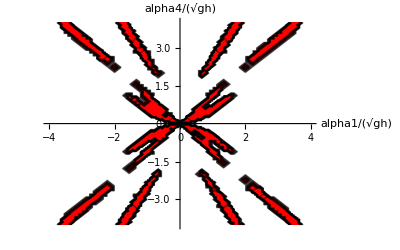

```mathematica
pHypTest[λ]:=CharPol2[λ]/. {alphas[2,t,r,θ]-> 0, alphas[3,t,r,θ]->0};
EVs[alpha1_,alpha4_]:=Solve[pHypTest[λ]==0,λ] /.{alphas[1,t,r,θ]->alpha1,alphas[4,t,r,θ]->alpha4};
ImaginaryPartofEV[alpha1_,alpha4_] := Im[λ]   /.Solve[pHypTest[λ]==0,λ] /.{alphas[1,t,r,θ]->alpha1,alphas[4,t,r,θ]->alpha4};
HypTest[alpha1_,alpha4_]:=HypTest[alpha1,alpha4]=If[Chop[Norm[Chop[N[Chop[ImaginaryPartofEV[alpha1,alpha4]]]]]]==0,0,10];
HypRegion =ContourPlot[HypTest[x,y],{x,-4,4},{y,-4,4},PlotPoints->10,MaxRecursion->2,AspectRatio->0.25/0.4,ColorFunction->(If[#1<1/2,White ,RGBColor[1.0,0.0,0.0]]&),Frame->False,Axes->True,AxesOrigin->{0,0},(*Ticks->{{-0.2,-0.1,0.0,0.1,0.2},{-0.2,-0.1,0.0,0.1,0.2}},*)AxesLabel->{Style[alpha1/√gh,Small,Bold],Style[alpha4/√gh,Small,Bold]},AxesStyle->Thick,LabelStyle->{Bold,Medium}]
```

### Hyperbolicity of (4,0)th order system with α_2,α_3 and α_4 set to zero

```mathematica
CharPol2New[λ_]= CharPol2[λ]/.{alphas[4,t,r,θ]->0, alphas[3,t,r,θ]->0, alphas[2,t,r,θ]->0, alphas[1,t,r,θ]->Subscript[α, 1]}
Solve[CharPol2New[λ]==0,λ]
```

-λ^7+λ^5 (1+(5 α_1^2)/3)+λ^3 (-(2 α_1^2)/3-(5 α_1^4)/7)+λ (α_1^4/21+α_1^6/21)

{{λ→0},{λ→-√(1+α_1^2)},{λ→√(1+α_1^2)},{λ→-√(α_1^2/3+(2 α_1^2)/(3 √7))},{λ→√(α_1^2/3+(2 α_1^2)/(3 √7))},{λ→-(√(7 α_1^2-2 √7 α_1^2))/(√21)},{λ→(√(7 α_1^2-2 √7 α_1^2))/(√21)}}

```mathematica
test[λ_]=CharPol2New[λ]/. Subscript[α, 1]->2
Solve[test[λ]==0,λ]
```

-(16 λ)/63-(344 λ^3)/35+(23 λ^5)/3-λ^7

{{λ→0},{λ→-√(Root-0.0253Root[80+3096 #1-2415 #1^2+315 #1^3&,1]-0.025337367311441473)},{λ→√(Root-0.0253Root[80+3096 #1-2415 #1^2+315 #1^3&,1]-0.025337367311441473)},{λ→-√(Root1.66Root[80+3096 #1-2415 #1^2+315 #1^3&,2]1.662366297702879)},{λ→√(Root1.66Root[80+3096 #1-2415 #1^2+315 #1^3&,2]1.662366297702879)},{λ→-√(Root6.03Root[80+3096 #1-2415 #1^2+315 #1^3&,3]6.029637736275229)},{λ→√(Root6.03Root[80+3096 #1-2415 #1^2+315 #1^3&,3]6.029637736275229)}}

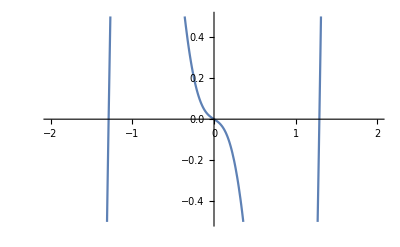

```mathematica
Plot[test[λ],{λ,-4.,4.},PlotRange->{{-2,2},{-.5,.5}}]
```

α_2 to zero

```mathematica
RSystemMatrixDisplay = RSystemMatrix/.{h[t,r,θ]->h,vr[t,r,θ]->vr,vθ[t,r,θ]->vθ,alphas[1,t,r,θ]->Subscript[α, 1], alphas[2,t,r,θ]->0,alphas[3,t,r,θ]->0; alphas[4,t,r,θ]->0};
RSystemMatrixDisplayTest = FullSimplify[RSystemMatrixDisplay /. Subscript[α, 1]->0];

FullSimplify[Eigensystem[RSystemMatrixDisplayTest]]

DiagonalizableMatrixQ[RSystemMatrixDisplayTest]
```

{{vr,vr-1/(1155 h)(√(1334025 h^2 vr^2+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,1])),vr+1/(1155 h)(√(1334025 h^2 vr^2+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,1])),vr-1/(1155 h)(√(1334025 h^2 vr^2+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,2])),vr+1/(1155 h)(√(1334025 h^2 vr^2+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,2])),vr-1/(1155 h)(√(1334025 h^2 vr^2+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,3])),vr+1/(1155 h)(√(1334025 h^2 vr^2+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,3]))},{{0,0,0,0,0,0,1},{(-24045800625 h^4 alphas[3,t,r,θ]^4+1179150 h^2 alphas[3,t,r,θ]^2 (1334025 h^2 vr^2+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,1])-(1334025 h^2 vr^2+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,1])^2)/(360 alphas[3,t,r,θ]^2 √(1334025 h^2 vr^2+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,1]) (1334025 h^2 (vr^2-alphas[3,t,r,θ]^2)+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,1])),295/792-(3328325 h^2 alphas[3,t,r,θ]^2)/(-8004150 h^2 (vr^2-alphas[3,t,r,θ]^2)-6 Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,1])+1/alphas[3,t,r,θ]^2((77 vr^2)/24+1/(415800 h^2)Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,1]),-((5775 h alphas[3,t,r,θ] (2695 h^2 (495 vr^2-alphas[3,t,r,θ]^2)+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,1]))/(4 √(1334025 h^2 vr^2+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,1]) (1334025 h^2 (vr^2-alphas[3,t,r,θ]^2)+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,1]))),55/36 (1+(1815450 h^2 alphas[3,t,r,θ]^2)/(1334025 h^2 (vr^2-alphas[3,t,r,θ]^2)+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,1])),(4902541875 h^4 alphas[3,t,r,θ]^4+811650 h^2 alphas[3,t,r,θ]^2 (1334025 h^2 vr^2+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,1])-(1334025 h^2 vr^2+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,1])^2)/(360 h alphas[3,t,r,θ] √(1334025 h^2 vr^2+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,1]) (1334025 h^2 (vr^2-alphas[3,t,r,θ]^2)+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,1])),1,0},{(24045800625 h^4 alphas[3,t,r,θ]^4-1179150 h^2 alphas[3,t,r,θ]^2 (1334025 h^2 vr^2+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,1])+(1334025 h^2 vr^2+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,1])^2)/(360 alphas[3,t,r,θ]^2 √(1334025 h^2 vr^2+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,1]) (1334025 h^2 (vr^2-alphas[3,t,r,θ]^2)+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,1])),295/792-(3328325 h^2 alphas[3,t,r,θ]^2)/(-8004150 h^2 (vr^2-alphas[3,t,r,θ]^2)-6 Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,1])+1/alphas[3,t,r,θ]^2((77 vr^2)/24+1/(415800 h^2)Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,1]),(5775 h alphas[3,t,r,θ] (2695 h^2 (495 vr^2-alphas[3,t,r,θ]^2)+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,1]))/(4 √(1334025 h^2 vr^2+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,1]) (1334025 h^2 (vr^2-alphas[3,t,r,θ]^2)+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,1])),55/36 (1+(1815450 h^2 alphas[3,t,r,θ]^2)/(1334025 h^2 (vr^2-alphas[3,t,r,θ]^2)+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,1])),(-4902541875 h^4 alphas[3,t,r,θ]^4-811650 h^2 alphas[3,t,r,θ]^2 (1334025 h^2 vr^2+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,1])+(1334025 h^2 vr^2+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,1])^2)/(360 h alphas[3,t,r,θ] √(1334025 h^2 vr^2+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,1]) (1334025 h^2 (vr^2-alphas[3,t,r,θ]^2)+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,1])),1,0},{(-24045800625 h^4 alphas[3,t,r,θ]^4+1179150 h^2 alphas[3,t,r,θ]^2 (1334025 h^2 vr^2+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,2])-(1334025 h^2 vr^2+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,2])^2)/(360 alphas[3,t,r,θ]^2 √(1334025 h^2 vr^2+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,2]) (1334025 h^2 (vr^2-alphas[3,t,r,θ]^2)+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,2])),295/792-(3328325 h^2 alphas[3,t,r,θ]^2)/(-8004150 h^2 (vr^2-alphas[3,t,r,θ]^2)-6 Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,2])+1/alphas[3,t,r,θ]^2((77 vr^2)/24+1/(415800 h^2)Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,2]),-((5775 h alphas[3,t,r,θ] (2695 h^2 (495 vr^2-alphas[3,t,r,θ]^2)+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,2]))/(4 √(1334025 h^2 vr^2+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,2]) (1334025 h^2 (vr^2-alphas[3,t,r,θ]^2)+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,2]))),55/36 (1+(1815450 h^2 alphas[3,t,r,θ]^2)/(1334025 h^2 (vr^2-alphas[3,t,r,θ]^2)+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,2])),(4902541875 h^4 alphas[3,t,r,θ]^4+811650 h^2 alphas[3,t,r,θ]^2 (1334025 h^2 vr^2+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,2])-(1334025 h^2 vr^2+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,2])^2)/(360 h alphas[3,t,r,θ] √(1334025 h^2 vr^2+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,2]) (1334025 h^2 (vr^2-alphas[3,t,r,θ]^2)+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,2])),1,0},{(24045800625 h^4 alphas[3,t,r,θ]^4-1179150 h^2 alphas[3,t,r,θ]^2 (1334025 h^2 vr^2+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,2])+(1334025 h^2 vr^2+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,2])^2)/(360 alphas[3,t,r,θ]^2 √(1334025 h^2 vr^2+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,2]) (1334025 h^2 (vr^2-alphas[3,t,r,θ]^2)+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,2])),295/792-(3328325 h^2 alphas[3,t,r,θ]^2)/(-8004150 h^2 (vr^2-alphas[3,t,r,θ]^2)-6 Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,2])+1/alphas[3,t,r,θ]^2((77 vr^2)/24+1/(415800 h^2)Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,2]),(5775 h alphas[3,t,r,θ] (2695 h^2 (495 vr^2-alphas[3,t,r,θ]^2)+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,2]))/(4 √(1334025 h^2 vr^2+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,2]) (1334025 h^2 (vr^2-alphas[3,t,r,θ]^2)+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,2])),55/36 (1+(1815450 h^2 alphas[3,t,r,θ]^2)/(1334025 h^2 (vr^2-alphas[3,t,r,θ]^2)+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,2])),(-4902541875 h^4 alphas[3,t,r,θ]^4-811650 h^2 alphas[3,t,r,θ]^2 (1334025 h^2 vr^2+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,2])+(1334025 h^2 vr^2+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,2])^2)/(360 h alphas[3,t,r,θ] √(1334025 h^2 vr^2+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,2]) (1334025 h^2 (vr^2-alphas[3,t,r,θ]^2)+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,2])),1,0},{(-24045800625 h^4 alphas[3,t,r,θ]^4+1179150 h^2 alphas[3,t,r,θ]^2 (1334025 h^2 vr^2+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,3])-(1334025 h^2 vr^2+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,3])^2)/(360 alphas[3,t,r,θ]^2 √(1334025 h^2 vr^2+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,3]) (1334025 h^2 (vr^2-alphas[3,t,r,θ]^2)+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,3])),295/792-(3328325 h^2 alphas[3,t,r,θ]^2)/(-8004150 h^2 (vr^2-alphas[3,t,r,θ]^2)-6 Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,3])+1/alphas[3,t,r,θ]^2((77 vr^2)/24+1/(415800 h^2)Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,3]),-((5775 h alphas[3,t,r,θ] (2695 h^2 (495 vr^2-alphas[3,t,r,θ]^2)+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,3]))/(4 √(1334025 h^2 vr^2+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,3]) (1334025 h^2 (vr^2-alphas[3,t,r,θ]^2)+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,3]))),55/36 (1+(1815450 h^2 alphas[3,t,r,θ]^2)/(1334025 h^2 (vr^2-alphas[3,t,r,θ]^2)+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,3])),(4902541875 h^4 alphas[3,t,r,θ]^4+811650 h^2 alphas[3,t,r,θ]^2 (1334025 h^2 vr^2+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,3])-(1334025 h^2 vr^2+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,3])^2)/(360 h alphas[3,t,r,θ] √(1334025 h^2 vr^2+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,3]) (1334025 h^2 (vr^2-alphas[3,t,r,θ]^2)+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,3])),1,0},{(24045800625 h^4 alphas[3,t,r,θ]^4-1179150 h^2 alphas[3,t,r,θ]^2 (1334025 h^2 vr^2+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,3])+(1334025 h^2 vr^2+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,3])^2)/(360 alphas[3,t,r,θ]^2 √(1334025 h^2 vr^2+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,3]) (1334025 h^2 (vr^2-alphas[3,t,r,θ]^2)+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,3])),295/792-(3328325 h^2 alphas[3,t,r,θ]^2)/(-8004150 h^2 (vr^2-alphas[3,t,r,θ]^2)-6 Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,3])+1/alphas[3,t,r,θ]^2((77 vr^2)/24+1/(415800 h^2)Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,3]),(5775 h alphas[3,t,r,θ] (2695 h^2 (495 vr^2-alphas[3,t,r,θ]^2)+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,3]))/(4 √(1334025 h^2 vr^2+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,3]) (1334025 h^2 (vr^2-alphas[3,t,r,θ]^2)+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,3])),55/36 (1+(1815450 h^2 alphas[3,t,r,θ]^2)/(1334025 h^2 (vr^2-alphas[3,t,r,θ]^2)+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,3])),(-4902541875 h^4 alphas[3,t,r,θ]^4-811650 h^2 alphas[3,t,r,θ]^2 (1334025 h^2 vr^2+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,3])+(1334025 h^2 vr^2+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,3])^2)/(360 h alphas[3,t,r,θ] √(1334025 h^2 vr^2+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,3]) (1334025 h^2 (vr^2-alphas[3,t,r,θ]^2)+Root[-2374061173201265625 g h^7 vr^4+2374061173201265625 h^6 vr^6+2098442107441968750 g h^7 vr^2 alphas[3,t,r,θ]^2-3115896895956796875 h^6 vr^4 alphas[3,t,r,θ]^2-32077699178765625 g h^7 alphas[3,t,r,θ]^4+744549647373984375 h^6 vr^2 alphas[3,t,r,θ]^4-2713924618453125 h^6 alphas[3,t,r,θ]^6+(-3559245401250 g h^5 vr^2+5338868101875 h^4 vr^4+1573015578750 g h^5 alphas[3,t,r,θ]^2-4671422043750 h^4 vr^2 alphas[3,t,r,θ]^2+558122709375 h^4 alphas[3,t,r,θ]^4) #1+(-1334025 g h^3+4002075 h^2 vr^2-1750875 h^2 alphas[3,t,r,θ]^2) #1^2+#1^3&,3])),1,0}}}

True

## Hyperbolicity of (3,0)th order system

### Construction system

```mathematica
Clear["Global`*"]
Nr=3;
Nθ=0;

alphas[t,r,θ]=Table[alphas[i,t,r,θ],{i,1,Nr}];
gammas[t,r,θ]=Table[gammas[i,t,r,θ],{i,1,Nθ}];

vars[t_,r_,θ_]= {h[t,r,θ],vr[t,r,θ]};
For[i=1,i<Nr+1,i++,AppendTo[vars[t,r,θ],alphas[i,t,r,θ]]];
AppendTo[vars[t,r,θ],vθ[t,r,θ]];
For[i=1,i<Nθ+1,i++,AppendTo[vars[t,r,θ],gammas[i,t,r,θ]]];

consvars[t,r,θ]= {h[t,r,θ],h[t,r,θ]vr[t,r,θ]};
For[i=1,i<Nr+1,i++,AppendTo[consvars[t,r,θ],h[t,r,θ]alphas[i,t,r,θ]]];
AppendTo[consvars[t,r,θ],h[t,r,θ]vθ[t,r,θ]];
For[i=1,i<Nθ+1,i++,AppendTo[consvars[t,r,θ],h[t,r,θ]gammas[i,t,r,θ]]];

derVars[t_,r_,θ_]=Table[D[consvars[t,r,θ][[i]],vars[t,r,θ][[j]]],{i,1,3+Nr+Nθ},{j,1,3+Nr+Nθ}]; AA=derVars[t,r,θ];

ACoefficients=Table[(2*i+1)*Integrate[(LegendreP[i,2*x-1])*(LegendreP[j,2*x-1])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nr,Nθ]},{j,Max[Nr,Nθ]},{k,Max[Nr,Nθ]}];
BCoefficients=Table[(2*i+1)*Integrate[D[LegendreP[i,2*x-1],x]*(Integrate[LegendreP[j,2*xHat-1],{xHat,0,x}])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nr,Nθ]},{j,Max[Nr,Nθ]},{k,Max[Nr,Nθ]}];
CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Max[Nr,Nθ]},{j,Max[Nr,Nθ]}];

Rflux=ConstantArray[0,3+Nr+Nθ];
θflux=ConstantArray[0,3+Nr+Nθ];

Rflux[[1]]=h[t,r,θ]vr[t,r,θ];
Rflux[[2]]=h[t,r,θ] vr[t,r,θ]^2+h[t,r,θ]Sum[(alphas[i,t,r,θ])^2/(2*i+1),{i,1,Nr}]+g h[t,r,θ]^2/2;
Rflux[[3+Nr]]=h[t,r,θ]vr[t,r,θ]vθ[t,r,θ]+h[t,r,θ]Sum[(alphas[i,t,r,θ]gammas[i,t,r,θ])/(2*i+1),{i,1,Min[Nr,Nθ]}];

For[i=1,i<Nr+1,i++,
	Rflux[[2+i]]=2*h[t,r,θ]vr[t,r,θ]alphas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,r,θ]alphas[k,t,r,θ],{k,1,Nr}
],{j,1,Nr}
]
]

For[i=1,i<Nθ+1,i++,
	Rflux[[3+Nr+i]]=h[t,r,θ]vr[t,r,θ]gammas[i,t,r,θ]+h[t,r,θ]vθ[t,r,θ]alphas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,r,θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nr}
]
]

θflux[[1]]=h[t,r,θ]vθ[t,r,θ];
θflux[[2]]=h[t,r,θ]vr[t,r,θ]vθ[t,r,θ]+h[t,r,θ]Sum[(alphas[i,t,r,θ]gammas[i,t,r,θ])/(2*i+1),{i,1,Min[Nr,Nθ]}];
θflux[[3+Nr]]=h[t,r,θ] vθ[t,r,θ]^2+h[t,r,θ]Sum[(gammas[i,t,r,θ])^2/(2*i+1),{i,1,Nθ}]+g h[t,r,θ]^2/2;
For[i=1,i<Nr+1,i++,
	θflux[[2+i]]=h[t,r,θ]vr[t,r,θ]gammas[i,t,r,θ]+h[t,r,θ]vθ[t,r,θ]alphas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,r,θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nr}
]
]

For[i=1,i<Nθ+1,i++,
	θflux[[3+Nr+i]]=2h[t,r,θ]vθ[t,r,θ]gammas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]gammas[j,t,r,θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nθ}
]
]

Rncflux=ConstantArray[0,3+Nr+Nθ];
θncflux=ConstantArray[0,3+Nr+Nθ];

Rncflux[[1]] = 0; 
Rncflux[[2]] = 0;
Rncflux[[3+Nr]]=0;

For[i=1,i<Nr+1,i++,
	Rncflux[[2+i]]=vr[t,r,θ]D[h[t,r,θ] alphas[i,t,r,θ],r]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] alphas[j,t,r,θ],r]alphas[k,t,r,θ],{k,1,Nr}
],{j,1,Nr}
]
]

For[i=1,i<Nθ+1,i++,
	Rncflux[[3+Nr+i]]=vθ[t,r,θ]D[h[t,r,θ] alphas[i,t,r,θ],r]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] alphas[j,t,r,θ],r]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nr}
]
]

θncflux[[1]] = 0; 
θncflux[[2]] = 0;
θncflux[[3+Nr]] = 0;

For[i=1,i<Nr+1,i++,
	θncflux[[2+i]]=vr[t,r,θ]D[h[t,r,θ] gammas[i,t,r,θ],θ]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] gammas[j,t,r,θ],θ]alphas[k,t,r,θ],{k,1,Nr}
],{j,1,Nθ}
]
]

For[i=1,i<Nθ+1,i++,
	θncflux[[3+Nr+i]]=vθ[t,r,θ]D[h[t,r,θ] gammas[i,t,r,θ],θ]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] gammas[j,t,r,θ],θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nθ}
]
]

{rest,BBR}=CoefficientArrays[D[Rflux,r],D[vars[t,r,θ],r]];

{rest,BBθ}=CoefficientArrays[D[θflux,θ],D[vars[t,r,θ],θ]];

If[Nr==0,CCR=ConstantArray[0,{3+Nr+Nθ,3+Nr+Nθ}],{rest,CCR}=CoefficientArrays[Rncflux,D[vars[t,r,θ],r]]];
(*{rest,CCR}=CoefficientArrays[Rncflux,D[vars[t,r,θ],r]];*)

If[Nθ==0,CCθ=ConstantArray[0,{3+Nr+Nθ,3+Nr+Nθ}],{rest,CCθ}=CoefficientArrays[θncflux,D[vars[t,r,θ],θ]]];
(*{rest,CCθ}=CoefficientArrays[θncflux,D[vars[t,r,θ],θ]];*)


$Assumptions={h[t,r,θ]>=0};
RSystemMatrix = FullSimplify[Inverse[AA].(BBR - CCR)]; RSystemMatrix//MatrixForm
(*FullSimplify[Expand[CharacteristicPolynomial[RSystemMatrix,λ]]]*)
(*Reigenvalues=FullSimplify[NSolve[CharacteristicPolynomial[RSystemMatrix,λ]==0,λ]]//MatrixForm*)
(*FullSimplify[Eigenvalues[RSystemMatrix]]//MatrixForm*)
(*Eigenvectors[Inverse[AA].(BBR - CCR)]//MatrixForm*)

(*θSystemMatrix = FullSimplify[Inverse[AA].(1/r BBθ - CCθ)]; *)
(*Expand[CharacteristicPolynomial[θSystemMatrix,λ]]*)
(*θeigenvalues=FullSimplify[NSolve[CharacteristicPolynomial[θSystemMatrix,λ]==0,λ]]*)


CharPol[λ_]=FullSimplify[Expand[CharacteristicPolynomial[RSystemMatrix,λ]]];
(*CharPol2[λ_]=Collect[Expand[CharPol[λ] /.{ λ ->(λ +vr[t,r,θ]),alphas[1,t,r,θ]-> (7*alphas[1,t,r,θ]),alphas[2,t,r,θ]-> (5*alphas[2,t,r,θ])}],λ]*)

(* Adapt the scaling of the coefficients *)
CharPol2[λ_]=Collect[Expand[CharPol[λ]/(g*h[t,r,θ])^((Nr+Nθ+3)/2) /.{ λ ->(Sqrt[g*h[t,r,θ]]*λ +vr[t,r,θ]),alphas[1,t,r,θ]->alphas[1,t,r,θ]*Sqrt[g*h[t,r,θ]],alphas[2,t,r,θ]->alphas[2,t,r,θ]*Sqrt[g*h[t,r,θ]],alphas[3,t,r,θ]->alphas[3,t,r,θ]*Sqrt[g*h[t,r,θ]]}],λ];
(*Solve[CharPol2[λ]==0,λ]*)
```

(vr[t,r,θ] | h[t,r,θ] | 0 | 0 | 0 | 0
g+(35 alphas[1,t,r,θ]^2+21 alphas[2,t,r,θ]^2+15 alphas[3,t,r,θ]^2)/(105 h[t,r,θ]) | vr[t,r,θ] | 2/3 alphas[1,t,r,θ] | 2/5 alphas[2,t,r,θ] | 2/7 alphas[3,t,r,θ] | 0
(2 alphas[2,t,r,θ] (14 alphas[1,t,r,θ]+9 alphas[3,t,r,θ]))/(35 h[t,r,θ]) | alphas[1,t,r,θ] | alphas[2,t,r,θ]+vr[t,r,θ] | 3/5 (alphas[1,t,r,θ]+alphas[3,t,r,θ]) | 3/7 alphas[2,t,r,θ] | 0
(-7 alphas[1,t,r,θ]^2+21 alphas[1,t,r,θ] alphas[3,t,r,θ]+3 (alphas[2,t,r,θ]^2+alphas[3,t,r,θ]^2))/(21 h[t,r,θ]) | alphas[2,t,r,θ] | 1/3 alphas[1,t,r,θ]+9/7 alphas[3,t,r,θ] | 3/7 alphas[2,t,r,θ]+vr[t,r,θ] | 4/7 alphas[1,t,r,θ]+1/3 alphas[3,t,r,θ] | 0
(alphas[2,t,r,θ] (-4 alphas[1,t,r,θ]+alphas[3,t,r,θ]))/(5 h[t,r,θ]) | alphas[3,t,r,θ] | 0 | 2/5 (alphas[1,t,r,θ]+alphas[3,t,r,θ]) | 1/3 alphas[2,t,r,θ]+vr[t,r,θ] | 0
0 | 0 | 0 | 0 | 0 | vr[t,r,θ])

```mathematica
(2*+1)*Integrate[D[LegendreP[1,2*x-1],x]*(Integrate[LegendreP[2,2*xHat-1],{xHat,0,x}])*(LegendreP[1,2*x-1]),{x,0,1}]
```

-2/15

### Other formulations

#### Notation as in the proof

```mathematica
RSystemMatrix2 = FullSimplify[(BBR - CCR).Inverse[AA]];
SystemMatrixDisplay2=RSystemMatrix2/.{alphas[1,t,r,θ]->Subscript[α, 1],alphas[2,t,r,θ]->Subscript[α, 2],alphas[3,t,r,θ]->Subscript[α, 3],gammas[1,t,r,θ]->Subscript[γ, 1],gammas[2,t,r,θ]->Subscript[γ, 2],gammas[3,t,r,θ]->Subscript[γ, 3],h[t,r,θ]->h,vr[t,r,θ]->vr,vθ[t,r,θ]->vθ};
SystemMatrixLinDisplay=SystemMatrixDisplay2/.{Subscript[α, 2]->0,Subscript[α, 3]->0,Subscript[γ, 2]->0,Subscript[γ, 3]->0};
SystemMatrixLinDisplay//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0
g h-vr^2-α_1^2/3 | 2 vr | (2 α_1)/3 | 0 | 0 | 0
-2 vr α_1 | 2 α_1 | vr | (3 α_1)/5 | 0 | 0
-(2 α_1^2)/3 | 0 | α_1/3 | vr | (4 α_1)/7 | 0
0 | 0 | 0 | (2 α_1)/5 | vr | 0
-vr vθ | vθ | 0 | 0 | 0 | vr)

```mathematica
Eigensystem[SystemMatrixLinDisplay]//MatrixForm
```

(vr | vr | 1/7 (7 vr-√21 α_1) | 1/7 (7 vr+√21 α_1) | vr-√(g h+α_1^2) | vr+√(g h+α_1^2)
{0,0,0,0,0,1} | {(8 α_1)/(7 (g h+α_1^2)),(8 vr α_1)/(7 (g h+α_1^2)),-(4 (3 g h-α_1^2))/(7 (g h+α_1^2)),0,1,0} | {1/vθ,-(-7 vr+√21 α_1)/(7 vθ),-(21 g h-16 α_1^2)/(14 vθ α_1),(5 √(3/7) (7 g h+4 α_1^2))/(14 vθ α_1),-(7 g h+4 α_1^2)/(7 vθ α_1),1} | {1/vθ,-(-7 vr-√21 α_1)/(7 vθ),-(21 g h-16 α_1^2)/(14 vθ α_1),-(5 √(3/7) (7 g h+4 α_1^2))/(14 vθ α_1),-(7 g h+4 α_1^2)/(7 vθ α_1),1} | {1/vθ,-(-vr+√(g h+α_1^2))/vθ,(2 α_1)/vθ,0,0,1} | {1/vθ,-(-vr-√(g h+α_1^2))/vθ,(2 α_1)/vθ,0,0,1})

```mathematica
FullSimplify[Eigenvalues[SystemMatrixLinDisplay]]
```

{vr,vr,vr-√(3/7) α_1,vr+√(3/7) α_1,vr-√(g h+α_1^2),vr+√(g h+α_1^2)}

```mathematica
BCoefficients//MatrixForm
```

((0
1/5
0) | (-1/5
0
3/35) | (0
-3/35
0)
(-1
0
3/7) | (0
-1/7
0) | (-2/7
0
-1/21)
(0
-6/5
0) | (-4/5
0
-2/15) | (0
-1/5
0))

### Hyperbolicity check for (3,0)th order system with α_2 and α_3 set to 0

```mathematica
CharPol2New[λ_]= CharPol2[λ]/.{alphas[3,t,r,θ]->0, alphas[2,t,r,θ]->0, alphas[1,t,r,θ]->Subscript[α, 1]}
FullSimplify[Solve[CharPol2New[λ]==0,λ]]
```

λ^6+λ^4 (-1-(10 α_1^2)/7)+λ^2 ((3 α_1^2)/7+(3 α_1^4)/7)

```mathematica
{{λ->0},{λ->0},{λ->-√(3/7) Subscript[α, 1]},{λ->√(3/7) Subscript[α, 1]},{λ->-√(1+Subscript[α, 1]^2)},{λ->√(1+Subscript[α, 1]^2)}}
```

```mathematica
(*RSystemMatrixNew=RSystemMatrix/.{alphas[2,t,r,θ]->0,alphas[3,t,r,θ]->0,alphas[1,t,r,θ]->Subscript[α, 1],h[t,r,θ]->h,vr[t,r,θ]->vr,vθ[t,r,θ]->vθ};
{eValues,eVectors}=Eigensystem[RSystemMatrixNew];
*)
(*DiagonalizableMatrixQ[RSystemMatrixNew]*)
```

True

α_1 to zero

```mathematica
RSystemMatrixDisplay = RSystemMatrix/.{h[t,r,θ]->h,vr[t,r,θ]->vr,vθ[t,r,θ]->vθ,alphas[1,t,r,θ]->Subscript[α, 1], alphas[2,t,r,θ]->0, alphas[3,t,r,θ]->0};
RSystemMatrixDisplayTest = RSystemMatrixDisplay /. Subscript[α, 1]->0;

Eigensystem[RSystemMatrixDisplayTest] // MatrixForm

DiagonalizableMatrixQ[RSystemMatrixDisplayTest]
```

(vr | vr | vr | vr | -√g √h+vr | √g √h+vr
{0,0,0,0,0,1} | {0,0,0,0,1,0} | {0,0,0,1,0,0} | {0,0,1,0,0,0} | {-(√h)/(√g),1,0,0,0,0} | {(√h)/(√g),1,0,0,0,0})

True

### Hyperbolicity plot for the (3,0)th order system

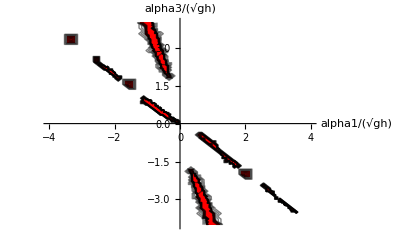

```mathematica
pHypTest[λ]:=CharPol2[λ]/.alphas[2,t,r,θ]->0;
EVs[alpha1_,alpha3_]:=Solve[pHypTest[λ]==0,λ] /.{alphas[1,t,r,θ]->alpha1,alphas[3,t,r,θ]->alpha3};
ImaginaryPartofEV[alpha1_,alpha3_] := Im[λ]   /.Solve[pHypTest[λ]==0,λ] /.{alphas[1,t,r,θ]->alpha1,alphas[3,t,r,θ]->alpha3};
HypTest[alpha1_,alpha3_]:=HypTest[alpha1,alpha3]=If[Chop[Norm[Chop[N[Chop[ImaginaryPartofEV[alpha1,alpha3]]]]]]==0,0,10];
HypRegion =ContourPlot[HypTest[x,y],{x,-4,4},{y,-4,4},PlotPoints->10,MaxRecursion->2,AspectRatio->0.25/0.4,ColorFunction->(If[#1<1/2,White ,RGBColor[1.0,0.0,0.0]]&),Frame->False,Axes->True,AxesOrigin->{0,0},(*Ticks->{{-0.2,-0.1,0.0,0.1,0.2},{-0.2,-0.1,0.0,0.1,0.2}},*)AxesLabel->{Style[alpha1/√gh,Small,Bold],Style[alpha3/√gh,Small,Bold]},AxesStyle->Thick,LabelStyle->{Bold,Medium}]
```

## Hyperbolicity of (5,0)th order system

### Construction system

```mathematica
Clear["Global`*"]
Nr=5;
Nθ=0;

alphas[t,r,θ]=Table[alphas[i,t,r,θ],{i,1,Nr}];
gammas[t,r,θ]=Table[gammas[i,t,r,θ],{i,1,Nθ}];

vars[t_,r_,θ_]= {h[t,r,θ],vr[t,r,θ]};
For[i=1,i<Nr+1,i++,AppendTo[vars[t,r,θ],alphas[i,t,r,θ]]];
AppendTo[vars[t,r,θ],vθ[t,r,θ]];
For[i=1,i<Nθ+1,i++,AppendTo[vars[t,r,θ],gammas[i,t,r,θ]]];

consvars[t,r,θ]= {h[t,r,θ],h[t,r,θ]vr[t,r,θ]};
For[i=1,i<Nr+1,i++,AppendTo[consvars[t,r,θ],h[t,r,θ]alphas[i,t,r,θ]]];
AppendTo[consvars[t,r,θ],h[t,r,θ]vθ[t,r,θ]];
For[i=1,i<Nθ+1,i++,AppendTo[consvars[t,r,θ],h[t,r,θ]gammas[i,t,r,θ]]];

derVars[t_,r_,θ_]=Table[D[consvars[t,r,θ][[i]],vars[t,r,θ][[j]]],{i,1,3+Nr+Nθ},{j,1,3+Nr+Nθ}]; AA=derVars[t,r,θ];

ACoefficients=Table[(2*i+1)*Integrate[(LegendreP[i,2*x-1])*(LegendreP[j,2*x-1])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nr,Nθ]},{j,Max[Nr,Nθ]},{k,Max[Nr,Nθ]}];
BCoefficients=Table[(2*i+1)*Integrate[D[LegendreP[i,2*x-1],x]*(Integrate[LegendreP[j,2*xHat-1],{xHat,0,x}])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nr,Nθ]},{j,Max[Nr,Nθ]},{k,Max[Nr,Nθ]}];
CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Max[Nr,Nθ]},{j,Max[Nr,Nθ]}];

Rflux=ConstantArray[0,3+Nr+Nθ];
θflux=ConstantArray[0,3+Nr+Nθ];

Rflux[[1]]=h[t,r,θ]vr[t,r,θ];
Rflux[[2]]=h[t,r,θ] vr[t,r,θ]^2+h[t,r,θ]Sum[(alphas[i,t,r,θ])^2/(2*i+1),{i,1,Nr}]+g h[t,r,θ]^2/2;
Rflux[[3+Nr]]=h[t,r,θ]vr[t,r,θ]vθ[t,r,θ]+h[t,r,θ]Sum[(alphas[i,t,r,θ]gammas[i,t,r,θ])/(2*i+1),{i,1,Min[Nr,Nθ]}];

For[i=1,i<Nr+1,i++,
	Rflux[[2+i]]=2*h[t,r,θ]vr[t,r,θ]alphas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,r,θ]alphas[k,t,r,θ],{k,1,Nr}
],{j,1,Nr}
]
]

For[i=1,i<Nθ+1,i++,
	Rflux[[3+Nr+i]]=h[t,r,θ]vr[t,r,θ]gammas[i,t,r,θ]+h[t,r,θ]vθ[t,r,θ]alphas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,r,θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nr}
]
]

θflux[[1]]=h[t,r,θ]vθ[t,r,θ];
θflux[[2]]=h[t,r,θ]vr[t,r,θ]vθ[t,r,θ]+h[t,r,θ]Sum[(alphas[i,t,r,θ]gammas[i,t,r,θ])/(2*i+1),{i,1,Min[Nr,Nθ]}];
θflux[[3+Nr]]=h[t,r,θ] vθ[t,r,θ]^2+h[t,r,θ]Sum[(gammas[i,t,r,θ])^2/(2*i+1),{i,1,Nθ}]+g h[t,r,θ]^2/2;
For[i=1,i<Nr+1,i++,
	θflux[[2+i]]=h[t,r,θ]vr[t,r,θ]gammas[i,t,r,θ]+h[t,r,θ]vθ[t,r,θ]alphas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,r,θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nr}
]
]

For[i=1,i<Nθ+1,i++,
	θflux[[3+Nr+i]]=2h[t,r,θ]vθ[t,r,θ]gammas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]gammas[j,t,r,θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nθ}
]
]

Rncflux=ConstantArray[0,3+Nr+Nθ];
θncflux=ConstantArray[0,3+Nr+Nθ];

Rncflux[[1]] = 0; 
Rncflux[[2]] = 0;
Rncflux[[3+Nr]]=0;

For[i=1,i<Nr+1,i++,
	Rncflux[[2+i]]=vr[t,r,θ]D[h[t,r,θ] alphas[i,t,r,θ],r]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] alphas[j,t,r,θ],r]alphas[k,t,r,θ],{k,1,Nr}
],{j,1,Nr}
]
]

For[i=1,i<Nθ+1,i++,
	Rncflux[[3+Nr+i]]=vθ[t,r,θ]D[h[t,r,θ] alphas[i,t,r,θ],r]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] alphas[j,t,r,θ],r]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nr}
]
]

θncflux[[1]] = 0; 
θncflux[[2]] = 0;
θncflux[[3+Nr]] = 0;

For[i=1,i<Nr+1,i++,
	θncflux[[2+i]]=vr[t,r,θ]D[h[t,r,θ] gammas[i,t,r,θ],θ]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] gammas[j,t,r,θ],θ]alphas[k,t,r,θ],{k,1,Nr}
],{j,1,Nθ}
]
]

For[i=1,i<Nθ+1,i++,
	θncflux[[3+Nr+i]]=vθ[t,r,θ]D[h[t,r,θ] gammas[i,t,r,θ],θ]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] gammas[j,t,r,θ],θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nθ}
]
]

{rest,BBR}=CoefficientArrays[D[Rflux,r],D[vars[t,r,θ],r]];

{rest,BBθ}=CoefficientArrays[D[θflux,θ],D[vars[t,r,θ],θ]];

If[Nr==0,CCR=ConstantArray[0,{3+Nr+Nθ,3+Nr+Nθ}],{rest,CCR}=CoefficientArrays[Rncflux,D[vars[t,r,θ],r]]];
(*{rest,CCR}=CoefficientArrays[Rncflux,D[vars[t,r,θ],r]];*)

If[Nθ==0,CCθ=ConstantArray[0,{3+Nr+Nθ,3+Nr+Nθ}],{rest,CCθ}=CoefficientArrays[θncflux,D[vars[t,r,θ],θ]]];
(*{rest,CCθ}=CoefficientArrays[θncflux,D[vars[t,r,θ],θ]];*)


$Assumptions={h[t,r,θ]>=0};
RSystemMatrix = FullSimplify[Inverse[AA].(BBR - CCR)]; RSystemMatrix//MatrixForm
(*FullSimplify[Expand[CharacteristicPolynomial[RSystemMatrix,λ]]]*)
(*Reigenvalues=FullSimplify[NSolve[CharacteristicPolynomial[RSystemMatrix,λ]==0,λ]]//MatrixForm*)
(*FullSimplify[Eigenvalues[RSystemMatrix]]//MatrixForm*)
(*Eigenvectors[Inverse[AA].(BBR - CCR)]//MatrixForm*)

(*θSystemMatrix = FullSimplify[Inverse[AA].(1/r BBθ - CCθ)]; *)
(*Expand[CharacteristicPolynomial[θSystemMatrix,λ]]*)
(*θeigenvalues=FullSimplify[NSolve[CharacteristicPolynomial[θSystemMatrix,λ]==0,λ]]*)


CharPol[λ_]=Expand[CharacteristicPolynomial[RSystemMatrix,λ]];
(*CharPol2[λ_]=Collect[Expand[CharPol[λ] /.{ λ ->(λ +vr[t,r,θ]),alphas[1,t,r,θ]-> (7*alphas[1,t,r,θ]),alphas[2,t,r,θ]-> (5*alphas[2,t,r,θ])}],λ]*)

(* Adapt the scaling of the coefficients *)
CharPol2[λ_]=Collect[Expand[CharPol[λ]/(g*h[t,r,θ])^((Nr+Nθ+3)/2) /.{ λ ->(Sqrt[g*h[t,r,θ]]*λ +vr[t,r,θ]),alphas[1,t,r,θ]->alphas[1,t,r,θ]*Sqrt[g*h[t,r,θ]],alphas[2,t,r,θ]->alphas[2,t,r,θ]*Sqrt[g*h[t,r,θ]],alphas[3,t,r,θ]->alphas[3,t,r,θ]*Sqrt[g*h[t,r,θ]],alphas[4,t,r,θ]->alphas[4,t,r,θ]*Sqrt[g*h[t,r,θ]],alphas[5,t,r,θ]->alphas[5,t,r,θ]*Sqrt[g*h[t,r,θ]]}],λ];
(*Solve[CharPol2[λ]==0,λ]*)
```

(vr[t,r,θ] | h[t,r,θ] | 0 | 0 | 0 | 0 | 0 | 0
g+(1155 alphas[1,t,r,θ]^2+693 alphas[2,t,r,θ]^2+495 alphas[3,t,r,θ]^2+385 alphas[4,t,r,θ]^2+315 alphas[5,t,r,θ]^2)/(3465 h[t,r,θ]) | vr[t,r,θ] | 2/3 alphas[1,t,r,θ] | 2/5 alphas[2,t,r,θ] | 2/7 alphas[3,t,r,θ] | 2/9 alphas[4,t,r,θ] | 2/11 alphas[5,t,r,θ] | 0
(924 alphas[1,t,r,θ] alphas[2,t,r,θ]+594 alphas[2,t,r,θ] alphas[3,t,r,θ]+10 alphas[4,t,r,θ] (44 alphas[3,t,r,θ]+35 alphas[5,t,r,θ]))/(1155 h[t,r,θ]) | alphas[1,t,r,θ] | alphas[2,t,r,θ]+vr[t,r,θ] | 3/5 (alphas[1,t,r,θ]+alphas[3,t,r,θ]) | 3/7 (alphas[2,t,r,θ]+alphas[4,t,r,θ]) | 1/3 (alphas[3,t,r,θ]+alphas[5,t,r,θ]) | 3/11 alphas[4,t,r,θ] | 0
(-3003 alphas[1,t,r,θ]^2+9009 alphas[1,t,r,θ] alphas[3,t,r,θ]+13 (99 (alphas[2,t,r,θ]^2+alphas[3,t,r,θ]^2)+429 alphas[2,t,r,θ] alphas[4,t,r,θ]+85 alphas[4,t,r,θ]^2)+4095 alphas[3,t,r,θ] alphas[5,t,r,θ]+945 alphas[5,t,r,θ]^2)/(9009 h[t,r,θ]) | alphas[2,t,r,θ] | 1/3 alphas[1,t,r,θ]+9/7 alphas[3,t,r,θ] | 3/7 alphas[2,t,r,θ]+16/21 alphas[4,t,r,θ]+vr[t,r,θ] | 4/7 alphas[1,t,r,θ]+1/3 alphas[3,t,r,θ]+125/231 alphas[5,t,r,θ] | 3/7 alphas[2,t,r,θ]+185/693 alphas[4,t,r,θ] | 80/231 alphas[3,t,r,θ]+95/429 alphas[5,t,r,θ] | 0
(1287 alphas[2,t,r,θ] (-4 alphas[1,t,r,θ]+alphas[3,t,r,θ])+65 (121 alphas[1,t,r,θ]+24 alphas[3,t,r,θ]) alphas[4,t,r,θ]+15 (312 alphas[2,t,r,θ]+95 alphas[4,t,r,θ]) alphas[5,t,r,θ])/(6435 h[t,r,θ]) | alphas[3,t,r,θ] | 14/9 alphas[4,t,r,θ] | 2/5 (alphas[1,t,r,θ]+alphas[3,t,r,θ])+10/11 alphas[5,t,r,θ] | 1/3 (alphas[2,t,r,θ]+alphas[4,t,r,θ])+vr[t,r,θ] | 5/9 alphas[1,t,r,θ]+3/11 (alphas[3,t,r,θ]+alphas[5,t,r,θ]) | 14/429 (13 alphas[2,t,r,θ]+7 alphas[4,t,r,θ]) | 0
(-1716 alphas[2,t,r,θ]^2+845 alphas[2,t,r,θ] alphas[4,t,r,θ]+5 (39 alphas[3,t,r,θ]^2+81 alphas[4,t,r,θ]^2+231 alphas[3,t,r,θ] alphas[5,t,r,θ]+84 alphas[5,t,r,θ]^2+91 alphas[1,t,r,θ] (-11 alphas[3,t,r,θ]+16 alphas[5,t,r,θ])))/(5005 h[t,r,θ]) | alphas[4,t,r,θ] | -2/7 alphas[3,t,r,θ]+20/11 alphas[5,t,r,θ] | 6/35 alphas[2,t,r,θ]+30/77 alphas[4,t,r,θ] | (3 (143 alphas[1,t,r,θ]+91 alphas[3,t,r,θ]+115 alphas[5,t,r,θ]))/1001 | 23/77 alphas[2,t,r,θ]+(243 alphas[4,t,r,θ])/1001+vr[t,r,θ] | (6 (91 alphas[1,t,r,θ]+41 alphas[3,t,r,θ]+35 alphas[5,t,r,θ]))/1001 | 0
(9 alphas[2,t,r,θ] (-65 alphas[3,t,r,θ]+14 alphas[5,t,r,θ])+alphas[4,t,r,θ] (-1001 alphas[1,t,r,θ]+24 alphas[3,t,r,θ]+105 alphas[5,t,r,θ]))/(819 h[t,r,θ]) | alphas[5,t,r,θ] | -5/9 alphas[4,t,r,θ] | 5/13 alphas[5,t,r,θ] | 5/21 (alphas[2,t,r,θ]+alphas[4,t,r,θ]) | 4/9 alphas[1,t,r,θ]+3/13 (alphas[3,t,r,θ]+alphas[5,t,r,θ]) | 11/39 alphas[2,t,r,θ]+8/39 alphas[4,t,r,θ]+vr[t,r,θ] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | vr[t,r,θ])

### Hyperbolicity plot of the (5,0)th order system

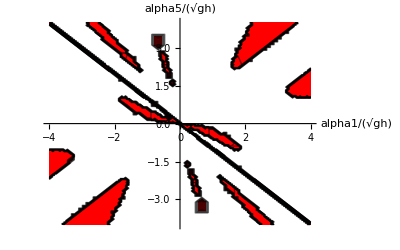

```mathematica
pHypTest[λ]:=CharPol2[λ]/.{alphas[2,t,r,θ]->0,alphas[3,t,r,θ]->0,alphas[4,t,r,θ]->0};
EVs[alpha1_,alpha5_]:=Solve[pHypTest[λ]==0,λ] /.{alphas[1,t,r,θ]->alpha1,alphas[5,t,r,θ]->alpha5};
ImaginaryPartofEV[alpha1_,alpha5_] := Im[λ]   /.Solve[pHypTest[λ]==0,λ] /.{alphas[1,t,r,θ]->alpha1,alphas[5,t,r,θ]->alpha5};
HypTest[alpha1_,alpha5_]:=HypTest[alpha1,alpha5]=If[Chop[Norm[Chop[N[Chop[ImaginaryPartofEV[alpha1,alpha5]]]]]]==0,0,10];
HypRegion =ContourPlot[HypTest[x,y],{x,-4,4},{y,-4,4},PlotPoints->10,MaxRecursion->2,AspectRatio->0.25/0.4,ColorFunction->(If[#1<1/2,White ,RGBColor[1.0,0.0,0.0]]&),Frame->False,Axes->True,AxesOrigin->{0,0},(*Ticks->{{-0.2,-0.1,0.0,0.1,0.2},{-0.2,-0.1,0.0,0.1,0.2}},*)AxesLabel->{Style[alpha1/√gh,Small,Bold],Style[alpha5/√gh,Small,Bold]},AxesStyle->Thick,LabelStyle->{Bold,Medium}]
```

### Hyperbolicity of the (5,0)th order system with higher order methods set to zero

```mathematica
CharPol2New[λ_]=CharPol2[λ]/.{alphas[2,t,r,θ]->0,alphas[3,t,r,θ]->0,alphas[4,t,r,θ]->0,alphas[5,t,r,θ]->0, alphas[1,t,r,θ]->Subscript[α, 1]}
Solve[CharPol2New[λ]==0,λ]
```

λ^8+λ^6 (-1-(21 α_1^2)/11)+λ^4 ((10 α_1^2)/11+(35 α_1^4)/33)+λ^2 (-(5 α_1^4)/33-(5 α_1^6)/33)

{{λ→0},{λ→0},{λ→-√(1+α_1^2)},{λ→√(1+α_1^2)},{λ→-(√(15 α_1^2-2 √15 α_1^2))/(√33)},{λ→(√(15 α_1^2-2 √15 α_1^2))/(√33)},{λ→-(√(15 α_1^2+2 √15 α_1^2))/(√33)},{λ→(√(15 α_1^2+2 √15 α_1^2))/(√33)}}

```mathematica
CharPol2NewTest[λ_]=CharPol2New[λ]/.Subscript[α, 1]->5;
Solve[CharPol2NewTest[λ]==0,λ]
```

{{λ→0},{λ→0},{λ→-√(Root0.974Root[-106250+119875 #1-11256 #1^2+231 #1^3&,1]0.9735598907279107)},{λ→√(Root0.974Root[-106250+119875 #1-11256 #1^2+231 #1^3&,1]0.9735598907279107)},{λ→-√(Root14.0Root[-106250+119875 #1-11256 #1^2+231 #1^3&,2]13.994752496009651)},{λ→√(Root14.0Root[-106250+119875 #1-11256 #1^2+231 #1^3&,2]13.994752496009651)},{λ→-√(Root33.8Root[-106250+119875 #1-11256 #1^2+231 #1^3&,3]33.75896034053517)},{λ→√(Root33.8Root[-106250+119875 #1-11256 #1^2+231 #1^3&,3]33.75896034053517)}}

```mathematica
RSystemMatrixNew=RSystemMatrix/.{alphas[2,t,r,θ]->0,alphas[3,t,r,θ]->0,alphas[4,t,r,θ]->0,alphas[5,t,r,θ]->0, alphas[1,t,r,θ]->Subscript[α, 1],h[t,r,θ]->h,vr[t,r,θ]->vr,vθ[t,r,θ]->vθ};
{eValues,eVectors}=Eigensystem[RSystemMatrixNew];

DiagonalizableMatrixQ[RSystemMatrixNew]
```

True

## (n,n)th order cylindrical axisymmetric systems

## (0,0)th order axisymmetric system

### Construction system

```mathematica
Clear["Global`*"]
Nr=0;
Nθ=0;
NumberOfVariables=3;

alphas[t,r,θ]=Table[alphas[i,t,r,θ],{i,1,Nr}];
gammas[t,r,θ]=Table[gammas[i,t,r,θ],{i,1,Nθ}];

vars[t_,r_,θ_]= {h[t,r,θ],vr[t,r,θ]};
For[i=1,i<Nr+1,i++,AppendTo[vars[t,r,θ],alphas[i,t,r,θ]]];
AppendTo[vars[t,r,θ],vθ[t,r,θ]];
For[i=1,i<Nθ+1,i++,AppendTo[vars[t,r,θ],gammas[i,t,r,θ]]];

consvars[t,r,θ]= {h[t,r,θ],h[t,r,θ]vr[t,r,θ]};
For[i=1,i<Nr+1,i++,AppendTo[consvars[t,r,θ],h[t,r,θ]alphas[i,t,r,θ]]];
AppendTo[consvars[t,r,θ],h[t,r,θ]vθ[t,r,θ]];
For[i=1,i<Nθ+1,i++,AppendTo[consvars[t,r,θ],h[t,r,θ]gammas[i,t,r,θ]]];

derVars[t_,r_,θ_]=Table[D[consvars[t,r,θ][[i]],vars[t,r,θ][[j]]],{i,1,3+Nr+Nθ},{j,1,3+Nr+Nθ}]; AA=derVars[t,r,θ];

ACoefficients=Table[(2*i+1)*Integrate[(LegendreP[i,2*x-1])*(LegendreP[j,2*x-1])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nr,Nθ]},{j,Max[Nr,Nθ]},{k,Max[Nr,Nθ]}];
BCoefficients=Table[(2*i+1)*Integrate[D[LegendreP[i,2*x-1],x]*(Integrate[LegendreP[j,2*xHat-1],{xHat,0,x}])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nr,Nθ]},{j,Max[Nr,Nθ]},{k,Max[Nr,Nθ]}];
CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Max[Nr,Nθ]},{j,Max[Nr,Nθ]}];

Rflux=ConstantArray[0,3+Nr+Nθ];
θflux=ConstantArray[0,3+Nr+Nθ];

Rflux[[1]]=h[t,r,θ]vr[t,r,θ];
Rflux[[2]]=h[t,r,θ] vr[t,r,θ]^2+h[t,r,θ]Sum[(alphas[i,t,r,θ])^2/(2*i+1),{i,1,Nr}]+g h[t,r,θ]^2/2;
Rflux[[3+Nr]]=h[t,r,θ]vr[t,r,θ]vθ[t,r,θ]+h[t,r,θ]Sum[(alphas[i,t,r,θ]gammas[i,t,r,θ])/(2*i+1),{i,1,Min[Nr,Nθ]}];

For[i=1,i<Nr+1,i++,
	Rflux[[2+i]]=2*h[t,r,θ]vr[t,r,θ]alphas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,r,θ]alphas[k,t,r,θ],{k,1,Nr}
],{j,1,Nr}
]
]

For[i=1,i<Nθ+1,i++,
	Rflux[[3+Nr+i]]=h[t,r,θ]vr[t,r,θ]gammas[i,t,r,θ]+h[t,r,θ]vθ[t,r,θ]alphas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,r,θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nr}
]
]

θflux[[1]]=h[t,r,θ]vθ[t,r,θ];
θflux[[2]]=h[t,r,θ]vr[t,r,θ]vθ[t,r,θ]+h[t,r,θ]Sum[(alphas[i,t,r,θ]gammas[i,t,r,θ])/(2*i+1),{i,1,Min[Nr,Nθ]}];
θflux[[3+Nr]]=h[t,r,θ] vθ[t,r,θ]^2+h[t,r,θ]Sum[(gammas[i,t,r,θ])^2/(2*i+1),{i,1,Nθ}]+g h[t,r,θ]^2/2;
For[i=1,i<Nr+1,i++,
	θflux[[2+i]]=h[t,r,θ]vr[t,r,θ]gammas[i,t,r,θ]+h[t,r,θ]vθ[t,r,θ]alphas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,r,θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nr}
]
]

For[i=1,i<Nθ+1,i++,
	θflux[[3+Nr+i]]=2h[t,r,θ]vθ[t,r,θ]gammas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]gammas[j,t,r,θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nθ}
]
]

Rncflux=ConstantArray[0,3+Nr+Nθ];
θncflux=ConstantArray[0,3+Nr+Nθ];

Rncflux[[1]] = 0; 
Rncflux[[2]] = 0;
Rncflux[[3+Nr]]=0;

For[i=1,i<Nr+1,i++,
	Rncflux[[2+i]]=vr[t,r,θ]D[h[t,r,θ] alphas[i,t,r,θ],r]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] alphas[j,t,r,θ],r]alphas[k,t,r,θ],{k,1,Nr}
],{j,1,Nr}
]
]

For[i=1,i<Nθ+1,i++,
	Rncflux[[3+Nr+i]]=vθ[t,r,θ]D[h[t,r,θ] alphas[i,t,r,θ],r]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] alphas[j,t,r,θ],r]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nr}
]
]

θncflux[[1]] = 0; 
θncflux[[2]] = 0;
θncflux[[3+Nr]] = 0;

For[i=1,i<Nr+1,i++,
	θncflux[[2+i]]=vr[t,r,θ]D[h[t,r,θ] gammas[i,t,r,θ],θ]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] gammas[j,t,r,θ],θ]alphas[k,t,r,θ],{k,1,Nr}
],{j,1,Nθ}
]
]

For[i=1,i<Nθ+1,i++,
	θncflux[[3+Nr+i]]=vθ[t,r,θ]D[h[t,r,θ] gammas[i,t,r,θ],θ]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] gammas[j,t,r,θ],θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nθ}
]
]

{rest,BBR}=CoefficientArrays[D[Rflux,r],D[vars[t,r,θ],r]];

{rest,BBθ}=CoefficientArrays[D[θflux,θ],D[vars[t,r,θ],θ]];

If[Nr==0,CCR=ConstantArray[0,{3+Nr+Nθ,3+Nr+Nθ}],{rest,CCR}=CoefficientArrays[Rncflux,D[vars[t,r,θ],r]]];
(*{rest,CCR}=CoefficientArrays[Rncflux,D[vars[t,r,θ],r]];*)

If[Nθ==0,CCθ=ConstantArray[0,{3+Nr+Nθ,3+Nr+Nθ}],{rest,CCθ}=CoefficientArrays[θncflux,D[vars[t,r,θ],θ]]];
(*{rest,CCθ}=CoefficientArrays[θncflux,D[vars[t,r,θ],θ]];*)


$Assumptions={h[t,r,θ]>=0};
RSystemMatrix = FullSimplify[Inverse[AA].(BBR - CCR)];
(*FullSimplify[Expand[CharacteristicPolynomial[RSystemMatrix,λ]]]*)
(*Reigenvalues=FullSimplify[NSolve[CharacteristicPolynomial[RSystemMatrix,λ]==0,λ]]//MatrixForm*)
(*FullSimplify[Eigenvalues[RSystemMatrix]]//MatrixForm*)
(*Eigenvectors[Inverse[AA].(BBR - CCR)]//MatrixForm*)

(*θSystemMatrix = FullSimplify[Inverse[AA].(1/r BBθ - CCθ)]; *)
(*Expand[CharacteristicPolynomial[θSystemMatrix,λ]]*)
(*θeigenvalues=FullSimplify[NSolve[CharacteristicPolynomial[θSystemMatrix,λ]==0,λ]]*)


CharPol[λ_]=FullSimplify[Expand[CharacteristicPolynomial[RSystemMatrix,λ]]];
(*CharPol2[λ_]=Collect[Expand[CharPol[λ] /.{ λ ->(λ +vr[t,r,θ]),alphas[1,t,r,θ]-> (7*alphas[1,t,r,θ]),alphas[2,t,r,θ]-> (5*alphas[2,t,r,θ])}],λ]*)

(* Adapt the scaling of the coefficients *)
CharPol2[λ_]=Collect[Expand[CharPol[λ]/(g*h[t,r,θ])^((Nr+Nθ+3)/2) /.{ λ ->(Sqrt[g*h[t,r,θ]]*λ +vr[t,r,θ])}],λ];
```

### Other formulations

#### Notation as in the proof

```mathematica
RSystemMatrix = FullSimplify[(BBR - CCR).Inverse[AA]];
ThetaSystemMatrix=FullSimplify[(BBθ-CCθ).Inverse[AA]];
RSystemMatrixDisplay = RSystemMatrix/.{h[t,r,θ]->h,vr[t,r,θ]->vr,vθ[t,r,θ]->vθ};
ThetaSystemMatrixDisplay = ThetaSystemMatrix/.{h[t,r,θ]->h,vr[t,r,θ]->vr,vθ[t,r,θ]->vθ};
```

```mathematica
RSystemMatrixDisplay//MatrixForm
```

(0 | 1 | 0
g h-vr^2 | 2 vr | 0
-vr vθ | vθ | vr)

```mathematica
RSystemMatrixDisplay//MatrixForm
```

(0 | 1 | 0
g h-vr^2 | 2 vr | 0
-vr vθ | vθ | vr)

```mathematica
SystemMatrix1D = {{0, 1}, {g h-vr^2, 2 vr}};
Total[Total[SystemMatrix1D /.{g->1,h->11,vr->26}]]
```

-612

### Source term

```mathematica
sourceTerm=ConstantArray[0,3+Nr+Nθ];

CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Max[Nr,Nθ]},{j,Max[Nr,Nθ]}];


sourceTerm[[1]]=0;
sourceTerm[[2]]=-ν/λ*(vr[t,r,θ]+Sum[alphas[i,t,r,θ],{i,1,Nr}]);
For[i=1,i <= Nr,i++,
sourceTerm[[2+i]]=-(2*i+1)ν/λ*(vr[t,r,θ]+Sum[(1+λ/h[t,r,θ]*CCoefficients[[i,j]])*alphas[j,t,r,θ],{j,1,Nr}])
];
sourceTerm[[Nr+3]]=-ν/λ*(vθ[t,r,θ]+Sum[gammas[i,t,r,θ],{i,1,Nθ}]);
For[i=1,i <= Nθ,i++,
sourceTerm[[i+Nr+3]]=-(2*i+1)ν/λ*(vθ[t,r,θ]+Sum[(1+λ/h*CCoefficients[[i,j]])*gammas[j,t,r,θ],{j,1,Nθ}])
];
sourceTermDisplay=sourceTerm /. {h[t,r,θ]->h,vr[t,r,θ]->vr,vθ[t,r,θ]->vθ};
sourceTerm1D=sourceTermDisplay/.{vθ->0};
sourceTermDisplay1D=sourceTerm1D[[1;;Nr+2]];
```

```mathematica
sourceTermDisplay1D//MatrixForm
Total[sourceTermDisplay1D/.{ν->0.5,λ->0.34,g->1,h->17.3,vr->12.6}]
```

(0
-(vr ν)/λ)

-18.5294

### Forcing term

```mathematica
forcingTerm=ConstantArray[0,3+Nr+Nθ];
(*

forcingTerm[[1]]=-1/r*h[t,r,θ]*vr[t,r,θ];
forcingTerm[[2]]=-1/r*h[t,r,θ]*(vr[t,r,θ]^2+Sum[alphas[i,t,r,θ]^2/(2*i+1),{i,1,Nr}]-vθ[t,r,θ]^2-Sum[gammas[i,t,r,θ]^2/(2*i+1),{i,1,Nθ}]);
For[i=1,i <= Nr,i++,
forcingTerm[[2+i]]=-1/r*h[t,r,θ]*(2*vr[t,r,θ]*alphas[i,t,r,θ]+Sum[Sum[(ACoefficients[[i,j]][[k]]+BCoefficients[[i,j]][[k]])*alphas[j,t,r,θ]*alphas[k,t,r,θ],{j,1,Nr}],{k,1,Nr}]-2*vθ[t,r,θ]*gammas[i,t,r,θ]-Sum[Sum[ACoefficients[[i,j]][[k]]*gammas[j,t,r,θ]*gammas[k,t,r,θ],{j,1,Nθ}],{k,1,Nθ}]-vr[t,r,θ]*alphas[i,t,r,θ])
];
forcingTerm[[Nr+3]]=-2/rh[t,r,θ]*(vθ[t,r,θ]*vr[t,r,θ]+Sum[(gammas[i,t,r,θ]*alphas[i,t,r,θ])/(2*i+1),{i,1,Nθ}]);
For[i=1,i <= Nθ,i++,
forcingTerm[[i+Nr+3]]=-1/r*h[t,r,θ]*(2*vr[t,r,θ]*gammas[i,t,r,θ]+2*vθ[t,r,θ]*alphas[i,t,r,θ]+Sum[Sum[(ACoefficients[[i,j]][[k]]+BCoefficients[[i,j]][[k]])*alphas[j,t,r,θ]*gammas[k,t,r,θ],{j,1,Nr}],{k,1,Nθ}]-vθ[t,r,θ]*alphas[i,t,r,θ])
];
*)

forcingTerm[[1]]=0;
forcingTerm[[2]]=1/r*h[t,r,θ]*vθ[t,r,θ]^2;
forcingTerm[[Nr+3]]=-1/r h[t,r,θ]*(vθ[t,r,θ]*vr[t,r,θ]);

forcingTermDisplay=FullSimplify[forcingTerm /. {h[t,r,θ]->h,vr[t,r,θ]->vr,alphas[1,t,r,θ]->Subscript[α, 1],alphas[2,t,r,θ]->Subscript[α, 2],gammas[1,t,r,θ]->Subscript[γ, 1],gammas[2,t,r,θ]->Subscript[γ, 2],vθ[t,r,θ]->vθ}];
forcingTerm1D=forcingTermDisplay/.{vθ->0};
forcingTermDisplay1D=forcingTerm1D[[1;;Nr+2]];
```

```mathematica
forcingTermDisplay//MatrixForm
```

(0
(h vθ^2)/r
-(h vr vθ)/r)

#### Print equations

```mathematica
sourceTermDisplayCombined=sourceTermDisplay+forcingTermDisplay;
sourceTermDisplayCombined1D=sourceTermDisplay1D+forcingTermDisplay1D;
OutputCSourceElements=ConstantArray[0,{NumberOfVariables,1}];
OutputCSourceElements1D=ConstantArray[0,{Nr+2,1}];
For[i=1,i<=NumberOfVariables,i++,
OutputCSourceElements[[i,1]]=sourceTermDisplayCombined[[i]]];
For[i=1,i<=Nr+2,i++,
OutputCSourceElements1D[[i,1]]=sourceTermDisplayCombined1D[[i]]];
OutputCSource = StringReplace[ToString[CForm[OutputCSourceElements]],{"Power"->"pow","vr"->"ur","vθ"->"utheta","List(List("->"sourceTerm()=","),List("->";\nsourceTerm()=","λ"->"xi","ν"->"R","r"->"coords(0)"}];
OutputCSource1D=StringReplace[ToString[CForm[OutputCSourceElements1D]],{"Power"->"pow","vr"->"u","List(List("->"sourceTerm()=","),List("->";\nsourceTerm()=","λ"->"xi","ν"->"R","r"->"coords(0)"}];;
For[i=0,i <NumberOfVariables,i++,
OutputCSource=StringInsert[OutputCSource,ToString[i],StringPosition[OutputCSource,"sourceTerm()",1][[1,2]]]];
For[i=0,i <Nr+2,i++,
OutputCSource1D=StringInsert[OutputCSource1D,ToString[i],StringPosition[OutputCSource1D,"sourceTerm()",1][[1,2]]]];
```

```mathematica
OutputCSource
```

sourceTerm(0)=0;
sourceTerm(1)=(h*pow(utheta,2))/coords(0) - (ur*R)/xi;
sourceTerm(2)=-((h*ur*utheta)/coords(0)) - (utheta*R)/xi))

## (1,1)th order axisymmetric system

### Construction system

```mathematica
Clear["Global`*"]
Nr=1;
Nθ=1;
NumberOfVariables = Nr+Nθ+3;

alphas[t,r,θ]=Table[alphas[i,t,r,θ],{i,1,Nr}];
gammas[t,r,θ]=Table[gammas[i,t,r,θ],{i,1,Nθ}];

vars[t_,r_,θ_]= {h[t,r,θ],vr[t,r,θ]};
For[i=1,i<Nr+1,i++,AppendTo[vars[t,r,θ],alphas[i,t,r,θ]]];
AppendTo[vars[t,r,θ],vθ[t,r,θ]];
For[i=1,i<Nθ+1,i++,AppendTo[vars[t,r,θ],gammas[i,t,r,θ]]];

consvars[t,r,θ]= {h[t,r,θ],h[t,r,θ]vr[t,r,θ]};
For[i=1,i<Nr+1,i++,AppendTo[consvars[t,r,θ],h[t,r,θ]alphas[i,t,r,θ]]];
AppendTo[consvars[t,r,θ],h[t,r,θ]vθ[t,r,θ]];
For[i=1,i<Nθ+1,i++,AppendTo[consvars[t,r,θ],h[t,r,θ]gammas[i,t,r,θ]]];

derVars[t_,r_,θ_]=Table[D[consvars[t,r,θ][[i]],vars[t,r,θ][[j]]],{i,1,3+Nr+Nθ},{j,1,3+Nr+Nθ}]; AA=derVars[t,r,θ];

ACoefficients=Table[(2*i+1)*Integrate[(LegendreP[i,2*x-1])*(LegendreP[j,2*x-1])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nr,Nθ]},{j,Max[Nr,Nθ]},{k,Max[Nr,Nθ]}];
BCoefficients=Table[(2*i+1)*Integrate[D[LegendreP[i,2*x-1],x]*(Integrate[LegendreP[j,2*xHat-1],{xHat,0,x}])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nr,Nθ]},{j,Max[Nr,Nθ]},{k,Max[Nr,Nθ]}];
CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Max[Nr,Nθ]},{j,Max[Nr,Nθ]}];

Rflux=ConstantArray[0,3+Nr+Nθ];
θflux=ConstantArray[0,3+Nr+Nθ];

Rflux[[1]]=h[t,r,θ]vr[t,r,θ];
Rflux[[2]]=h[t,r,θ] vr[t,r,θ]^2+h[t,r,θ]Sum[(alphas[i,t,r,θ])^2/(2*i+1),{i,1,Nr}]+g h[t,r,θ]^2/2;
Rflux[[3+Nr]]=h[t,r,θ]vr[t,r,θ]vθ[t,r,θ]+h[t,r,θ]Sum[(alphas[i,t,r,θ]gammas[i,t,r,θ])/(2*i+1),{i,1,Min[Nr,Nθ]}];

For[i=1,i<Nr+1,i++,
	Rflux[[2+i]]=2*h[t,r,θ]vr[t,r,θ]alphas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,r,θ]alphas[k,t,r,θ],{k,1,Nr}
],{j,1,Nr}
]
]

For[i=1,i<Nθ+1,i++,
	Rflux[[3+Nr+i]]=h[t,r,θ]vr[t,r,θ]gammas[i,t,r,θ]+h[t,r,θ]vθ[t,r,θ]alphas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,r,θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nr}
]
]

θflux[[1]]=h[t,r,θ]vθ[t,r,θ];
θflux[[2]]=h[t,r,θ]vr[t,r,θ]vθ[t,r,θ]+h[t,r,θ]Sum[(alphas[i,t,r,θ]gammas[i,t,r,θ])/(2*i+1),{i,1,Min[Nr,Nθ]}];
θflux[[3+Nr]]=h[t,r,θ] vθ[t,r,θ]^2+h[t,r,θ]Sum[(gammas[i,t,r,θ])^2/(2*i+1),{i,1,Nθ}]+g h[t,r,θ]^2/2;
For[i=1,i<Nr+1,i++,
	θflux[[2+i]]=h[t,r,θ]vr[t,r,θ]gammas[i,t,r,θ]+h[t,r,θ]vθ[t,r,θ]alphas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,r,θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nr}
]
]

For[i=1,i<Nθ+1,i++,
	θflux[[3+Nr+i]]=2h[t,r,θ]vθ[t,r,θ]gammas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]gammas[j,t,r,θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nθ}
]
]

Rncflux=ConstantArray[0,3+Nr+Nθ];
θncflux=ConstantArray[0,3+Nr+Nθ];

Rncflux[[1]] = 0; 
Rncflux[[2]] = 0;
Rncflux[[3+Nr]]=0;

For[i=1,i<Nr+1,i++,
	Rncflux[[2+i]]=vr[t,r,θ]D[h[t,r,θ] alphas[i,t,r,θ],r]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] alphas[j,t,r,θ],r]alphas[k,t,r,θ],{k,1,Nr}
],{j,1,Nr}
]
]

For[i=1,i<Nθ+1,i++,
	Rncflux[[3+Nr+i]]=vθ[t,r,θ]D[h[t,r,θ] alphas[i,t,r,θ],r]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] alphas[j,t,r,θ],r]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nr}
]
]

θncflux[[1]] = 0; 
θncflux[[2]] = 0;
θncflux[[3+Nr]] = 0;

For[i=1,i<Nr+1,i++,
	θncflux[[2+i]]=vr[t,r,θ]D[h[t,r,θ] gammas[i,t,r,θ],θ]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] gammas[j,t,r,θ],θ]alphas[k,t,r,θ],{k,1,Nr}
],{j,1,Nθ}
]
]

For[i=1,i<Nθ+1,i++,
	θncflux[[3+Nr+i]]=vθ[t,r,θ]D[h[t,r,θ] gammas[i,t,r,θ],θ]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] gammas[j,t,r,θ],θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nθ}
]
]

{rest,BBR}=CoefficientArrays[D[Rflux,r],D[vars[t,r,θ],r]];

{rest,BBθ}=CoefficientArrays[D[θflux,θ],D[vars[t,r,θ],θ]];

If[Nr==0,CCR=ConstantArray[0,{3+Nr+Nθ,3+Nr+Nθ}],{rest,CCR}=CoefficientArrays[Rncflux,D[vars[t,r,θ],r]]];
(*{rest,CCR}=CoefficientArrays[Rncflux,D[vars[t,r,θ],r]];*)

If[Nθ==0,CCθ=ConstantArray[0,{3+Nr+Nθ,3+Nr+Nθ}],{rest,CCθ}=CoefficientArrays[θncflux,D[vars[t,r,θ],θ]]];
(*{rest,CCθ}=CoefficientArrays[θncflux,D[vars[t,r,θ],θ]];*)


$Assumptions={h[t,r,θ]>=0};
RSystemMatrix = FullSimplify[Inverse[AA].(BBR - CCR)];
(*FullSimplify[Expand[CharacteristicPolynomial[RSystemMatrix,λ]]]*)
(*Reigenvalues=FullSimplify[NSolve[CharacteristicPolynomial[RSystemMatrix,λ]==0,λ]]//MatrixForm*)
(*FullSimplify[Eigenvalues[RSystemMatrix]]//MatrixForm*)
(*Eigenvectors[Inverse[AA].(BBR - CCR)]//MatrixForm*)

(*θSystemMatrix = FullSimplify[Inverse[AA].(1/r BBθ - CCθ)]; *)
(*Expand[CharacteristicPolynomial[θSystemMatrix,λ]]*)
(*θeigenvalues=FullSimplify[NSolve[CharacteristicPolynomial[θSystemMatrix,λ]==0,λ]]*)


CharPol[λ_]=FullSimplify[Expand[CharacteristicPolynomial[RSystemMatrix,λ]]];
(*CharPol2[λ_]=Collect[Expand[CharPol[λ] /.{ λ ->(λ +vr[t,r,θ]),alphas[1,t,r,θ]-> (7*alphas[1,t,r,θ]),alphas[2,t,r,θ]-> (5*alphas[2,t,r,θ])}],λ]*)

(* Adapt the scaling of the coefficients *)
CharPol2[λ_]=Collect[Expand[CharPol[λ]/(g*h[t,r,θ])^((Nr+Nθ+3)/2) /.{ λ ->(Sqrt[g*h[t,r,θ]]*λ +vr[t,r,θ])}],λ];
```

### Other formulations

#### Notation as in the proof

```mathematica
RSystemMatrix = FullSimplify[(BBR - CCR).Inverse[AA]];
ThetaSystemMatrix = FullSimplify[(BBθ - CCθ).Inverse[AA]];
RSystemMatrixDisplay = RSystemMatrix/.{h[t,r,θ]->h,vr[t,r,θ]->vr,vθ[t,r,θ]->vθ,alphas[1,t,r,θ]->Subscript[α, 1],gammas[1,t,r,θ]->Subscript[γ, 1]};
ThetaSystemMatrixDisplay = ThetaSystemMatrix/.{h[t,r,θ]->h,vr[t,r,θ]->vr,vθ[t,r,θ]->vθ,alphas[1,t,r,θ]->Subscript[α, 1],gammas[1,t,r,θ]->Subscript[γ, 1]};
```

```mathematica
RSystemMatrixDisplay//MatrixForm
```

(0 | 1 | 0 | 0 | 0
g h-vr^2-α_1^2/3 | 2 vr | (2 α_1)/3 | 0 | 0
-2 vr α_1 | 2 α_1 | vr | 0 | 0
-vr vθ-(α_1 γ_1)/3 | vθ | γ_1/3 | vr | α_1/3
-vθ α_1-vr γ_1 | γ_1 | 0 | α_1 | vr)

```mathematica
oneDimensionalMatrix=({{0, 1, 0}, {g h-vr^2-Subscript[α, 1]^2/3, 2 vr, (2 Subscript[α, 1])/3}, {-2 vr Subscript[α, 1], 2 Subscript[α, 1], vr}});
Total[Total[oneDimensionalMatrix /.{g->1,h->11,vr->26,Subscript[α, 1]->-0.25}]]
```

-573.688

#### Print equations

2D C++

```mathematica
NumberOfEntries=NumberOfVariables^2;
OutputCElements=ConstantArray[0,{NumberOfEntries,1}];
k=1;
For[i=1,i<=NumberOfVariables,i++,
For[j=1,j<=NumberOfVariables,j++,
OutputCElements[[k++,1]]=RSystemMatrixDisplay[[i,j]]]]
OutputC = StringReplace[ToString[CForm[OutputCElements]],{"Power"->"pow","vr"->"ur","vθ"->"utheta","Subscript(α,1)"->"alphas[1]","Subscript(γ,1)"->"gammas[1]","List(List("->"JacobianR()=","),List("->";\nJacobianR()="}];
For[i=0,i <NumberOfVariables,i++,
For[j=0,j<NumberOfVariables,j++,
OutputC=StringInsert[OutputC,StringJoin[ToString[i],",",ToString[j]],StringPosition[OutputC,"JacobianR()",1][[1,2]]]]];
OutputC
```

JacobianR()=0;
JacobianR()=1;
JacobianR()=0;
JacobianR()=0;
JacobianR()=0;
JacobianR()=g*h - pow(ur,2) - pow(alphas[1],2)/3.;
JacobianR()=2*ur;
JacobianR()=(2*alphas[1])/3.;
JacobianR()=0;
JacobianR()=0;
JacobianR()=-2*ur*alphas[1];
JacobianR()=2*alphas[1];
JacobianR()=ur;
JacobianR()=0;
JacobianR()=0;
JacobianR()=-(ur*utheta) - (alphas[1]*gammas[1])/3.;
JacobianR()=utheta;
JacobianR()=gammas[1]/3.;
JacobianR()=ur;
JacobianR()=alphas[1]/3.;
JacobianR()=-(utheta*alphas[1]) - ur*gammas[1];
JacobianR()=gammas[1];
JacobianR()=0;
JacobianR()=alphas[1];
JacobianR()=ur))

```mathematica
StringPosition[OutputC,"JacobianR()",1]
```

{{1,11}}

### Hyperbolicity check

#### Hyperbolicity check when α_1 to zero

```mathematica
RSystemMatrixDisplay = RSystemMatrix/.{h[t,r,θ]->h,vr[t,r,θ]->vr,vθ[t,r,θ]->vθ,alphas[1,t,r,θ]->Subscript[α, 1],gammas[1,t,r,θ]->Subscript[γ, 1]};
RSystemMatrixDisplayTest = RSystemMatrixDisplay /. {Subscript[α, 1]->0};
RSystemMatrixDisplayTest//MatrixForm
Eigensystem[RSystemMatrixDisplayTest] // MatrixForm

DiagonalizableMatrixQ[RSystemMatrixDisplayTest]
```

(0 | 1 | 0 | 0 | 0
g h-vr^2 | 2 vr | 0 | 0 | 0
0 | 0 | vr | 0 | 0
-vr vθ | vθ | γ_1/3 | vr | 0
-vr γ_1 | γ_1 | 0 | 0 | vr)

(-√g √h+vr | vr | vr | vr | √g √h+vr
{1/γ_1,-(√g √h-vr)/γ_1,0,vθ/γ_1,1} | {0,0,0,0,1} | {0,0,0,1,0} | {0,0,0,0,0} | {1/γ_1,-(-√g √h-vr)/γ_1,0,vθ/γ_1,1})

False

### Source term

```mathematica
sourceTerm=ConstantArray[0,3+Nr+Nθ];

CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Max[Nr,Nθ]},{j,Max[Nr,Nθ]}];


sourceTerm[[1]]=0;
sourceTerm[[2]]=-ν/λ*(vr[t,r,θ]+Sum[alphas[i,t,r,θ],{i,1,Nr}]);
For[i=1,i <= Nr,i++,
sourceTerm[[2+i]]=-(2*i+1)ν/λ*(vr[t,r,θ]+Sum[(1+λ/h[t,r,θ]*CCoefficients[[i,j]])*alphas[j,t,r,θ],{j,1,Nr}])
];
sourceTerm[[Nr+3]]=-ν/λ*(vθ[t,r,θ]+Sum[gammas[i,t,r,θ],{i,1,Nθ}]);
For[i=1,i <= Nθ,i++,
sourceTerm[[i+Nr+3]]=-(2*i+1)ν/λ*(vθ[t,r,θ]+Sum[(1+λ/h*CCoefficients[[i,j]])*gammas[j,t,r,θ],{j,1,Nθ}])
];
sourceTermDisplay=sourceTerm /. {h[t,r,θ]->h,vr[t,r,θ]->vr,vθ[t,r,θ]->vθ,alphas[1,t,r,θ]->Subscript[α, 1],gammas[1,t,r,θ]->Subscript[γ, 1]};
sourceTermDisplay1D=sourceTermDisplay[[1;;Nr+2]]/.{vθ->0,Subscript[γ, 1]->0};
```

```mathematica
sourceTermDisplay//MatrixForm
Total[sourceTermDisplay1D/.{ν->0.5,λ->0.34,g->1,h->17.3,vr->12.6,Subscript[α, 1]->-0.4}]
```

(0
-(ν (vr+α_1))/λ
-(3 ν (vr+(1+(4 λ)/h) α_1))/λ
-(ν (vθ+γ_1))/λ
-(3 ν (vθ+(1+(4 λ)/h) γ_1))/λ)

-71.626

#### Print equations

```mathematica
OutputCSourceElements=ConstantArray[0,{NumberOfVariables,1}];
For[i=1,i<=NumberOfVariables,i++,
OutputCSourceElements[[i,1]]=sourceTermDisplay[[i]]]
OutputCSource = StringReplace[ToString[CForm[OutputCSourceElements]],{"Power"->"pow","vr"->"ur","vθ"->"utheta","Subscript(α,1)"->"alphas[1]","Subscript(γ,1)"->"gammas[1]","List(List("->"sourceTerm()=","),List("->";\nsourceTerm()=","λ"->"xi","ν"->"R"}];

For[i=0,i <NumberOfVariables,i++,
OutputCSource=StringInsert[OutputCSource,ToString[i],StringPosition[OutputCSource,"sourceTerm()",1][[1,2]]]];
OutputCSource
```

sourceTerm(0)=0;
sourceTerm(1)=-((R*(ur + alphas[1]))/xi);
sourceTerm(2)=(-3*R*(ur + (1 + (4*xi)/h)*alphas[1]))/xi;
sourceTerm(3)=-((R*(utheta + gammas[1]))/xi);
sourceTerm(4)=(-3*R*(utheta + (1 + (4*xi)/h)*gammas[1]))/xi))

```mathematica
sourceTermDisplay//MatrixForm
```

(0
-(ν (vr+α_1))/λ
-(3 ν (vr+(1+(4 λ)/h) α_1))/λ
-(ν (vθ+γ_1))/λ
-(3 ν (vθ+(1+(4 λ)/h) γ_1))/λ)

### Forcing term

```mathematica
(* FORCING TERM NOT INCLUDED IN FLUX FUNCTION *)
```

```mathematica
(* 
forcingTerm=ConstantArray[0,3+Nr+Nθ];

forcingTerm[[1]]=-1/r*h[t,r,θ]*vr[t,r,θ];
forcingTerm[[2]]=-1/r*h[t,r,θ]*(vr[t,r,θ]^2+Sum[alphas[i,t,r,θ]^2/(2*i+1),{i,1,Nr}]-vθ[t,r,θ]^2-Sum[gammas[i,t,r,θ]^2/(2*i+1),{i,1,Nθ}]);
For[i=1,i <= Nr,i++,
forcingTerm[[2+i]]=-1/r*h[t,r,θ]*(2*vr[t,r,θ]*alphas[i,t,r,θ]+Sum[Sum[(ACoefficients[[i,j]][[k]]+BCoefficients[[i,j]][[k]])*alphas[j,t,r,θ]*alphas[k,t,r,θ],{j,1,Nr}],{k,1,Nr}]-2*vθ[t,r,θ]*gammas[i,t,r,θ]-Sum[Sum[ACoefficients[[i,j]][[k]]*gammas[j,t,r,θ]*gammas[k,t,r,θ],{j,1,Nθ}],{k,1,Nθ}]-vr[t,r,θ]*alphas[i,t,r,θ])
];
forcingTerm[[Nr+3]]=-2/rh[t,r,θ]*(vθ[t,r,θ]*vr[t,r,θ]+Sum[(gammas[i,t,r,θ]*alphas[i,t,r,θ])/(2*i+1),{i,1,Nθ}]);
For[i=1,i <= Nθ,i++,
forcingTerm[[i+Nr+3]]=-1/r*h[t,r,θ]*(2*vr[t,r,θ]*gammas[i,t,r,θ]+2*vθ[t,r,θ]*alphas[i,t,r,θ]+Sum[Sum[(ACoefficients[[i,j]][[k]]+BCoefficients[[i,j]][[k]])*alphas[j,t,r,θ]*gammas[k,t,r,θ],{j,1,Nr}],{k,1,Nθ}]-vθ[t,r,θ]*alphas[i,t,r,θ])
];
*)

(* FORCING TERM INCLUDED IN FLUX FUNCTION *)
forcingTerm=ConstantArray[0,3+Nr+Nθ];

forcingTerm[[1]]=0;
forcingTerm[[2]]=1/r*h[t,r,θ]*(vθ[t,r,θ]^2+Sum[gammas[i,t,r,θ]^2/(2*i+1),{i,1,Nθ}]);
For[i=1,i <= Nr,i++,
(*forcingTerm[[2+i]]=1/r*h[t,r,θ]*(2*vθ[t,r,θ]*gammas[i,t,r,θ]+Sum[Sum[ACoefficients[[i,j]][[k]]*gammas[j,t,r,θ]*gammas[k,t,r,θ],{j,1,Nθ}],{k,1,Nθ}])*)
forcingTerm[[2+i]]=1/r*h[t,r,θ]*(2*vθ[t,r,θ]*gammas[i,t,r,θ]-Sum[Sum[ACoefficients[[i,j]][[k]]*gammas[j,t,r,θ]*gammas[k,t,r,θ],{j,1,Nθ}],{k,1,Nθ}]-vr[t,r,θ]*alphas[i,t,r,θ])
];
forcingTerm[[Nr+3]]=-1/r h[t,r,θ]*(vθ[t,r,θ]*vr[t,r,θ]+Sum[(gammas[i,t,r,θ]*alphas[i,t,r,θ])/(2*i+1),{i,1,Nθ}]);

For[i=1,i <= Nθ,i++,
forcingTerm[[i+Nr+3]]=-1/r*h[t,r,θ]*(vr[t,r,θ]*gammas[i,t,r,θ]+vθ[t,r,θ]*alphas[i,t,r,θ]+Sum[Sum[ACoefficients[[i,j]][[k]]*alphas[j,t,r,θ]*gammas[k,t,r,θ],{j,1,Nr}],{k,1,Nθ}])
];



forcingTermDisplay=FullSimplify[forcingTerm /. {h[t,r,θ]->h,vr[t,r,θ]->vr,alphas[1,t,r,θ]->Subscript[α, 1],gammas[1,t,r,θ]->Subscript[γ, 1],vθ[t,r,θ]->vθ}];
forcingTermDisplay1D=forcingTermDisplay[[1;;Nr+2]]/.{vθ->0,Subscript[γ, 1]->0};
```

```mathematica
forcingTermDisplay//MatrixForm
```

(0
(h (vθ^2+γ_1^2/3))/r
(h (g h+4 vθ γ_1))/(2 r)
-(h (3 vr vθ+α_1 γ_1))/(3 r)
-(h (vθ α_1+vr γ_1))/r)

#### Print equations

```mathematica
sourceTermDisplayCombined=sourceTermDisplay+forcingTermDisplay;
sourceTermDisplayCombined1D=sourceTermDisplay1D+forcingTermDisplay1D;
OutputCSourceElements=ConstantArray[0,{NumberOfVariables,1}];
OutputCSourceElements1D=ConstantArray[0,{Nr+2,1}];
For[i=1,i<=NumberOfVariables,i++,
OutputCSourceElements[[i,1]]=sourceTermDisplayCombined[[i]]];
For[i=1,i<=Nr+2,i++,
OutputCSourceElements1D[[i,1]]=sourceTermDisplayCombined1D[[i]]];
OutputCSource = StringReplace[ToString[CForm[OutputCSourceElements]],{"Power"->"pow","vr"->"ur","vθ"->"utheta","Subscript(α,1)"->"alphas[1]","Subscript(γ,1)"->"gammas[1]","List(List("->"sourceTerm()=","),List("->";\nsourceTerm()=","λ"->"xi","ν"->"R","r"->"coords(0)"}];
OutputCSource1D=StringReplace[ToString[CForm[OutputCSourceElements1D]],{"Power"->"pow","vr"->"u","Subscript(α,1)"->"alpha1","List(List("->"sourceTerm()=","),List("->";\nsourceTerm()=","λ"->"xi","ν"->"R","r"->"coords(0)"}];;
For[i=0,i <NumberOfVariables,i++,
OutputCSource=StringInsert[OutputCSource,ToString[i],StringPosition[OutputCSource,"sourceTerm()",1][[1,2]]]];
For[i=0,i <Nr+2,i++,
OutputCSource1D=StringInsert[OutputCSource1D,ToString[i],StringPosition[OutputCSource1D,"sourceTerm()",1][[1,2]]]];

OutputCSource
```

sourceTerm(0)=0;
sourceTerm(1)=-((R*(ur + alphas[1]))/xi) + (h*(pow(utheta,2) + pow(gammas[1],2)/3.))/coords(0);
sourceTerm(2)=(-3*R*(ur + (1 + (4*xi)/h)*alphas[1]))/xi + (h*(-(ur*alphas[1]) + 2*utheta*gammas[1]))/coords(0);
sourceTerm(3)=-((R*(utheta + gammas[1]))/xi) - (h*(3*ur*utheta + alphas[1]*gammas[1]))/(3.*coords(0));
sourceTerm(4)=-((h*(utheta*alphas[1] + ur*gammas[1]))/coords(0)) - (3*R*(utheta + (1 + (4*xi)/h)*gammas[1]))/xi))

```mathematica
OutputCSource1D
```

sourceTerm(0)=-((h*u)/coords(0));
sourceTerm(1)=-((R*(u + alpha1))/xi) + (h*(-3*pow(u,2) - pow(alpha1,2)))/(3.*coords(0));
sourceTerm(2)=-((h*u*alpha1)/coords(0)) - (3*R*(u + (1 + (4*xi)/h)*alpha1))/xi))

## (2,2)th order axisymmetric system

### Construction system

```mathematica
Clear["Global`*"]
Nr=2;
Nθ=2;
NumberOfVariables=Nr+Nθ+3;

alphas[t,r,θ]=Table[alphas[i,t,r,θ],{i,1,Nr}];
gammas[t,r,θ]=Table[gammas[i,t,r,θ],{i,1,Nθ}];

vars[t_,r_,θ_]= {h[t,r,θ],vr[t,r,θ]};
For[i=1,i<Nr+1,i++,AppendTo[vars[t,r,θ],alphas[i,t,r,θ]]];
AppendTo[vars[t,r,θ],vθ[t,r,θ]];
For[i=1,i<Nθ+1,i++,AppendTo[vars[t,r,θ],gammas[i,t,r,θ]]];

consvars[t,r,θ]= {h[t,r,θ],h[t,r,θ]vr[t,r,θ]};
For[i=1,i<Nr+1,i++,AppendTo[consvars[t,r,θ],h[t,r,θ]alphas[i,t,r,θ]]];
AppendTo[consvars[t,r,θ],h[t,r,θ]vθ[t,r,θ]];
For[i=1,i<Nθ+1,i++,AppendTo[consvars[t,r,θ],h[t,r,θ]gammas[i,t,r,θ]]];

derVars[t_,r_,θ_]=Table[D[consvars[t,r,θ][[i]],vars[t,r,θ][[j]]],{i,1,3+Nr+Nθ},{j,1,3+Nr+Nθ}]; AA=derVars[t,r,θ];

ACoefficients=Table[(2*i+1)*Integrate[(LegendreP[i,2*x-1])*(LegendreP[j,2*x-1])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nr,Nθ]},{j,Max[Nr,Nθ]},{k,Max[Nr,Nθ]}];
BCoefficients=Table[(2*i+1)*Integrate[D[LegendreP[i,2*x-1],x]*(Integrate[LegendreP[j,2*xHat-1],{xHat,0,x}])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nr,Nθ]},{j,Max[Nr,Nθ]},{k,Max[Nr,Nθ]}];
CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Max[Nr,Nθ]},{j,Max[Nr,Nθ]}];

Rflux=ConstantArray[0,3+Nr+Nθ];
θflux=ConstantArray[0,3+Nr+Nθ];

Rflux[[1]]=h[t,r,θ]vr[t,r,θ];
Rflux[[2]]=h[t,r,θ] vr[t,r,θ]^2+h[t,r,θ]Sum[(alphas[i,t,r,θ])^2/(2*i+1),{i,1,Nr}]+g h[t,r,θ]^2/2;
Rflux[[3+Nr]]=h[t,r,θ]vr[t,r,θ]vθ[t,r,θ]+h[t,r,θ]Sum[(alphas[i,t,r,θ]gammas[i,t,r,θ])/(2*i+1),{i,1,Min[Nr,Nθ]}];

For[i=1,i<Nr+1,i++,
	Rflux[[2+i]]=2*h[t,r,θ]vr[t,r,θ]alphas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,r,θ]alphas[k,t,r,θ],{k,1,Nr}
],{j,1,Nr}
]
]

For[i=1,i<Nθ+1,i++,
	Rflux[[3+Nr+i]]=h[t,r,θ]vr[t,r,θ]gammas[i,t,r,θ]+h[t,r,θ]vθ[t,r,θ]alphas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,r,θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nr}
]
]

θflux[[1]]=h[t,r,θ]vθ[t,r,θ];
θflux[[2]]=h[t,r,θ]vr[t,r,θ]vθ[t,r,θ]+h[t,r,θ]Sum[(alphas[i,t,r,θ]gammas[i,t,r,θ])/(2*i+1),{i,1,Min[Nr,Nθ]}];
θflux[[3+Nr]]=h[t,r,θ] vθ[t,r,θ]^2+h[t,r,θ]Sum[(gammas[i,t,r,θ])^2/(2*i+1),{i,1,Nθ}]+g h[t,r,θ]^2/2;
For[i=1,i<Nr+1,i++,
	θflux[[2+i]]=h[t,r,θ]vr[t,r,θ]gammas[i,t,r,θ]+h[t,r,θ]vθ[t,r,θ]alphas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,r,θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nr}
]
]

For[i=1,i<Nθ+1,i++,
	θflux[[3+Nr+i]]=2h[t,r,θ]vθ[t,r,θ]gammas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]gammas[j,t,r,θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nθ}
]
]

Rncflux=ConstantArray[0,3+Nr+Nθ];
θncflux=ConstantArray[0,3+Nr+Nθ];

Rncflux[[1]] = 0; 
Rncflux[[2]] = 0;
Rncflux[[3+Nr]]=0;

For[i=1,i<Nr+1,i++,
	Rncflux[[2+i]]=vr[t,r,θ]D[h[t,r,θ] alphas[i,t,r,θ],r]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] alphas[j,t,r,θ],r]alphas[k,t,r,θ],{k,1,Nr}
],{j,1,Nr}
]
]

For[i=1,i<Nθ+1,i++,
	Rncflux[[3+Nr+i]]=vθ[t,r,θ]D[h[t,r,θ] alphas[i,t,r,θ],r]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] alphas[j,t,r,θ],r]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nr}
]
]

θncflux[[1]] = 0; 
θncflux[[2]] = 0;
θncflux[[3+Nr]] = 0;

For[i=1,i<Nr+1,i++,
	θncflux[[2+i]]=vr[t,r,θ]D[h[t,r,θ] gammas[i,t,r,θ],θ]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] gammas[j,t,r,θ],θ]alphas[k,t,r,θ],{k,1,Nr}
],{j,1,Nθ}
]
]

For[i=1,i<Nθ+1,i++,
	θncflux[[3+Nr+i]]=vθ[t,r,θ]D[h[t,r,θ] gammas[i,t,r,θ],θ]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] gammas[j,t,r,θ],θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nθ}
]
]

{rest,BBR}=CoefficientArrays[D[Rflux,r],D[vars[t,r,θ],r]];

{rest,BBθ}=CoefficientArrays[D[θflux,θ],D[vars[t,r,θ],θ]];

If[Nr==0,CCR=ConstantArray[0,{3+Nr+Nθ,3+Nr+Nθ}],{rest,CCR}=CoefficientArrays[Rncflux,D[vars[t,r,θ],r]]];
(*{rest,CCR}=CoefficientArrays[Rncflux,D[vars[t,r,θ],r]];*)

If[Nθ==0,CCθ=ConstantArray[0,{3+Nr+Nθ,3+Nr+Nθ}],{rest,CCθ}=CoefficientArrays[θncflux,D[vars[t,r,θ],θ]]];
(*{rest,CCθ}=CoefficientArrays[θncflux,D[vars[t,r,θ],θ]];*)


$Assumptions={h[t,r,θ]>=0};
RSystemMatrix = FullSimplify[Inverse[AA].(BBR - CCR)];
(*FullSimplify[Expand[CharacteristicPolynomial[RSystemMatrix,λ]]]*)
(*Reigenvalues=FullSimplify[NSolve[CharacteristicPolynomial[RSystemMatrix,λ]==0,λ]]//MatrixForm*)
(*FullSimplify[Eigenvalues[RSystemMatrix]]//MatrixForm*)
(*Eigenvectors[Inverse[AA].(BBR - CCR)]//MatrixForm*)

(*θSystemMatrix = FullSimplify[Inverse[AA].(1/r BBθ - CCθ)]; *)
(*Expand[CharacteristicPolynomial[θSystemMatrix,λ]]*)
(*θeigenvalues=FullSimplify[NSolve[CharacteristicPolynomial[θSystemMatrix,λ]==0,λ]]*)


CharPol[λ_]=FullSimplify[Expand[CharacteristicPolynomial[RSystemMatrix,λ]]];
(*CharPol2[λ_]=Collect[Expand[CharPol[λ] /.{ λ ->(λ +vr[t,r,θ]),alphas[1,t,r,θ]-> (7*alphas[1,t,r,θ]),alphas[2,t,r,θ]-> (5*alphas[2,t,r,θ])}],λ]*)

(* Adapt the scaling of the coefficients *)
CharPol2[λ_]=Collect[Expand[CharPol[λ]/(g*h[t,r,θ])^((Nr+Nθ+3)/2) /.{ λ ->(Sqrt[g*h[t,r,θ]]*λ +vr[t,r,θ]),alphas[1,t,r,θ]->alphas[1,t,r,θ]*Sqrt[g*h[t,r,θ]],alphas[2,t,r,θ]->alphas[2,t,r,θ]*Sqrt[g*h[t,r,θ]],gammas[1,t,r,θ]->gammas[1,t,r,θ]*Sqrt[g*h[t,r,θ]],gammas[2,t,r,θ]->gammas[2,t,r,θ]*Sqrt[g*h[t,r,θ]]}],λ];
(*Solve[CharPol2[λ]==0,λ]*)
```

```mathematica
CharPol2Display[λ_]=CharPol2[λ]/.{alphas[1,t,r,θ]->Subscript[α, 1],alphas[2,t,r,θ]->0,gammas[1,t,r,θ]->Subscript[γ, 1],gammas[2,t,r,θ]->Subscript[γ, 2]}
```

-λ^7+λ^5 (1+(9 α_1^2)/5)+λ^3 (-(4 α_1^2)/5-(23 α_1^4)/25)+λ ((3 α_1^4)/25+(3 α_1^6)/25)

```mathematica
Solve[CharPol2Display[λ]==0,λ]
```

{{λ→0},{λ→-√(3/5) α_1},{λ→√(3/5) α_1},{λ→-α_1/(√5)},{λ→α_1/(√5)},{λ→-√(1+α_1^2)},{λ→√(1+α_1^2)}}

```mathematica
TeXForm[CharPol2Display[λ]]
```

\left(\frac{9 \alpha _1^2}{5}+1\right) \lambda ^5+\left(-\frac{23 \alpha _1^4}{25}-\frac{4 \alpha _1^2}{5}\right) \lambda ^3+\left(\frac{3 \alpha _1^6}{25}+\frac{3 \alpha _1^4}{25}\right) \lambda -\lambda ^7

```mathematica
SystemMatrixDisplay=RSystemMatrix/.{alphas[1,t,r,θ]->Subscript[α, 1],alphas[2,t,r,θ]->Subscript[α, 2],gammas[1,t,r,θ]->Subscript[γ, 1],gammas[2,t,r,θ]->Subscript[γ, 2],h[t,r,θ]->h,vr[t,r,θ]->v,vθ[t,r,θ]->vθ};
```

```mathematica
SystemMatrixDisplay//MatrixForm
```

(v | h | 0 | 0 | 0 | 0 | 0
g+(5 α_1^2+3 α_2^2)/(15 h) | v | (2 α_1)/3 | (2 α_2)/5 | 0 | 0 | 0
(4 α_1 α_2)/(5 h) | α_1 | v+α_2 | (3 α_1)/5 | 0 | 0 | 0
(-7 α_1^2+3 α_2^2)/(21 h) | α_2 | α_1/3 | v+(3 α_2)/7 | 0 | 0 | 0
(5 α_1 γ_1+3 α_2 γ_2)/(15 h) | 0 | γ_1/3 | γ_2/5 | v | α_1/3 | α_2/5
(α_2 γ_1+3 α_1 γ_2)/(5 h) | 0 | (3 γ_2)/5 | γ_1/5 | α_1 | v+(2 α_2)/5 | (2 α_1)/5
(-7 α_1 γ_1+3 α_2 γ_2)/(21 h) | 0 | -γ_1/3 | γ_2/7 | α_2 | (2 α_1)/3 | v+(2 α_2)/7)

```mathematica
testMatrix = {{v, Subscript[α, 1]/3, Subscript[α, 2]/5}, {Subscript[α, 1], v+(2 Subscript[α, 2])/5, (2 Subscript[α, 1])/5}, {Subscript[α, 2], (2 Subscript[α, 1])/3, v+(2 Subscript[α, 2])/7}};
```

```mathematica
CharPolTest[λ_]=CharacteristicPolynomial[testMatrix,λ]/.{Subscript[α, 1]->0};
```

```mathematica
DiagonalMatrixQ[testMatrix]
```

False

```mathematica
FullSimplify[Solve[CharPolTest[λ]==0,λ]]
```

{{λ→v+(2 α_2)/5},{λ→v+1/35 (5-3 √30) α_2},{λ→v+1/35 (5+3 √30) α_2}}

### Other formulations

#### Notation as in the proof

```mathematica
RSystemMatrix = FullSimplify[(BBR - CCR).Inverse[AA]];
ThetaSystemMatrix=FullSimplify[(BBθ-CCθ).Inverse[AA]];
RSystemMatrixDisplay=RSystemMatrix/.{alphas[1,t,r,θ]->Subscript[α, 1],alphas[2,t,r,θ]->Subscript[α, 2],gammas[1,t,r,θ]->Subscript[γ, 1],gammas[2,t,r,θ]->Subscript[γ, 2],h[t,r,θ]->h,vr[t,r,θ]->vr,vθ[t,r,θ]->vθ};
ThetaSystemMatrixDisplay=ThetaSystemMatrix/.{alphas[1,t,r,θ]->Subscript[α, 1],alphas[2,t,r,θ]->Subscript[α, 2],gammas[1,t,r,θ]->Subscript[γ, 1],gammas[2,t,r,θ]->Subscript[γ, 2],h[t,r,θ]->h,vr[t,r,θ]->vr,vθ[t,r,θ]->vθ};
RSystemMatrixDisplay//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0 | 0
g h-vr^2-α_1^2/3-α_2^2/5 | 2 vr | (2 α_1)/3 | (2 α_2)/5 | 0 | 0 | 0
-2/5 α_1 (5 vr+2 α_2) | 2 α_1 | vr+α_2 | (3 α_1)/5 | 0 | 0 | 0
-2/21 (7 α_1^2+3 α_2 (7 vr+α_2)) | 2 α_2 | α_1/3 | vr+(3 α_2)/7 | 0 | 0 | 0
-vr vθ-(α_1 γ_1)/3-(α_2 γ_2)/5 | vθ | γ_1/3 | γ_2/5 | vr | α_1/3 | α_2/5
1/5 (-((5 vr+2 α_2) γ_1)-α_1 (5 vθ+2 γ_2)) | γ_1 | (3 γ_2)/5 | γ_1/5 | α_1 | vr+(2 α_2)/5 | (2 α_1)/5
-2/3 α_1 γ_1-vr γ_2-1/7 α_2 (7 vθ+2 γ_2) | γ_2 | -γ_1/3 | γ_2/7 | α_2 | (2 α_1)/3 | vr+(2 α_2)/7)

```mathematica
FullSimplify[Eigenvalues[RSystemMatrixDisplay/.{Subscript[α, 2]->0}]]
```

{vr,vr-α_1/(√5),vr+α_1/(√5),vr-√(3/5) α_1,vr+√(3/5) α_1,vr-√(g h+α_1^2),vr+√(g h+α_1^2)}

```mathematica
oneDimensionalMatrix=({{0, 1, 0, 0}, {g h-vr^2-Subscript[α, 1]^2/3-Subscript[α, 2]^2/5, 2 vr, (2 Subscript[α, 1])/3, (2 Subscript[α, 2])/5}, {-2/5 Subscript[α, 1] (5 vr+2 Subscript[α, 2]), 2 Subscript[α, 1], vr+Subscript[α, 2], (3 Subscript[α, 1])/5}, {-2/21 (7 Subscript[α, 1]^2+3 Subscript[α, 2] (7 vr+Subscript[α, 2])), 2 Subscript[α, 2], Subscript[α, 1]/3, vr+(3 Subscript[α, 2])/7}});
Total[Total[oneDimensionalMatrix /.{g->1,h->11,vr->26,Subscript[α, 1]->-0.25,Subscript[α, 2]->0.7}]]
```

-581.781

#### Print equation

```mathematica
NumberOfVariables = Nr+Nθ+3;
NumberOfEntries=NumberOfVariables^2;
OutputCElements=ConstantArray[0,{NumberOfEntries,1}];
k=1;
For[i=1,i<=NumberOfVariables,i++,
For[j=1,j<=NumberOfVariables,j++,
OutputCElements[[k++,1]]=ThetaSystemMatrixDisplay[[i,j]]]]
OutputC = StringReplace[ToString[CForm[OutputCElements]],{"Power"->"pow","vr"->"ur","vθ"->"utheta","Subscript(α,1)"->"alphas[1]","Subscript(α,2)"->"alphas[2]","Subscript(γ,1)"->"gammas[1]",
"Subscript(γ,2)"->"gammas[2]","List(List("->"JacobianTheta()=","),List("->";\nJacobianTheta()="}];
For[i=0,i <NumberOfVariables,i++,
For[j=0,j<NumberOfVariables,j++,
OutputC=StringInsert[OutputC,StringJoin[ToString[i],",",ToString[j]],StringPosition[OutputC,"JacobianTheta()",1][[1,2]]]]];
OutputC
```

JacobianTheta(0,0)=0;
JacobianTheta(0,1)=0;
JacobianTheta(0,2)=0;
JacobianTheta(0,3)=0;
JacobianTheta(0,4)=1;
JacobianTheta(0,5)=0;
JacobianTheta(0,6)=0;
JacobianTheta(1,0)=-(ur*utheta) - (alphas[1]*gammas[1])/3. - (alphas[2]*gammas[2])/5.;
JacobianTheta(1,1)=utheta;
JacobianTheta(1,2)=gammas[1]/3.;
JacobianTheta(1,3)=gammas[2]/5.;
JacobianTheta(1,4)=ur;
JacobianTheta(1,5)=alphas[1]/3.;
JacobianTheta(1,6)=alphas[2]/5.;
JacobianTheta(2,0)=(-((5*ur + 2*alphas[2])*gammas[1]) - alphas[1]*(5*utheta + 2*gammas[2]))/5.;
JacobianTheta(2,1)=gammas[1];
JacobianTheta(2,2)=utheta + (2*gammas[2])/5.;
JacobianTheta(2,3)=(2*gammas[1])/5.;
JacobianTheta(2,4)=alphas[1];
JacobianTheta(2,5)=(3*alphas[2])/5.;
JacobianTheta(2,6)=alphas[1]/5.;
JacobianTheta(3,0)=(-2*alphas[1]*gammas[1])/3. - ur*gammas[2] - (alphas[2]*(7*utheta + 2*gammas[2]))/7.;
JacobianTheta(3,1)=gammas[2];
JacobianTheta(3,2)=(2*gammas[1])/3.;
JacobianTheta(3,3)=utheta + (2*gammas[2])/7.;
JacobianTheta(3,4)=alphas[2];
JacobianTheta(3,5)=-0.3333333333333333*alphas[1];
JacobianTheta(3,6)=alphas[2]/7.;
JacobianTheta(4,0)=g*h - pow(utheta,2) - pow(gammas[1],2)/3. - pow(gammas[2],2)/5.;
JacobianTheta(4,1)=0;
JacobianTheta(4,2)=0;
JacobianTheta(4,3)=0;
JacobianTheta(4,4)=2*utheta;
JacobianTheta(4,5)=(2*gammas[1])/3.;
JacobianTheta(4,6)=(2*gammas[2])/5.;
JacobianTheta(5,0)=(-2*gammas[1]*(5*utheta + 2*gammas[2]))/5.;
JacobianTheta(5,1)=0;
JacobianTheta(5,2)=0;
JacobianTheta(5,3)=0;
JacobianTheta(5,4)=2*gammas[1];
JacobianTheta(5,5)=utheta + gammas[2];
JacobianTheta(5,6)=(3*gammas[1])/5.;
JacobianTheta(6,0)=(-2*(7*pow(gammas[1],2) + 3*gammas[2]*(7*utheta + gammas[2])))/21.;
JacobianTheta(6,1)=0;
JacobianTheta(6,2)=0;
JacobianTheta(6,3)=0;
JacobianTheta(6,4)=2*gammas[2];
JacobianTheta(6,5)=gammas[1]/3.;
JacobianTheta(6,6)=utheta + (3*gammas[2])/7.))

### Hyperbolicity plot for the (2,2)th order system

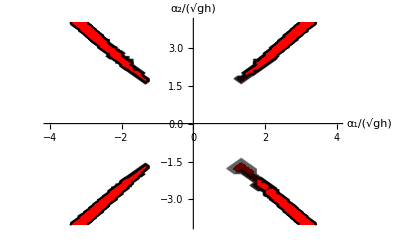

```mathematica
pHypTest[λ]:=CharPol2[λ];
EVs[alpha1_,alpha2_]:=Solve[pHypTest[λ]==0,λ] /.{alphas[1,t,r,θ]->alpha1,alphas[2,t,r,θ]->alpha2};
ImaginaryPartofEV[alpha1_,alpha2_] := Im[λ]   /.Solve[pHypTest[λ]==0,λ] /.{alphas[1,t,r,θ]->alpha1,alphas[2,t,r,θ]->alpha2};
HypTest[alpha1_,alpha2_]:=HypTest[alpha1,alpha2]=If[Chop[Norm[Chop[N[Chop[ImaginaryPartofEV[alpha1,alpha2]]]]]]==0,0,10];
HypRegion =ContourPlot[HypTest[x,y],{x,-4,4},{y,-4,4},PlotPoints->10,MaxRecursion->3,AspectRatio->0.25/0.4,ColorFunction->(If[#1<1/2,White ,RGBColor[1.0,0.0,0.0]]&),Frame->False,Axes->True,AxesOrigin->{0,0},(*Ticks->{{-0.2,-0.1,0.0,0.1,0.2},{-0.2,-0.1,0.0,0.1,0.2}},*)AxesLabel->{Style[Subscript[α, 1]/√gh,Small,Bold],Style[Subscript[α, 2]/√gh,Small,Bold]},AxesStyle->Thick,LabelStyle->{Bold,Medium}]
```

### Hyperbolicity of the (2,2)th order system with α_2 and γ_2 set to 0

```mathematica
CharPol2New[λ_]=CharPol2[λ]/. {alphas[2,t,r,θ]->0,alphas[1,t,r,θ]->Subscript[α, 1]};
Solve[CharPol2New[λ]==0,λ]
```

{{λ→0},{λ→-√(3/5) α_1},{λ→√(3/5) α_1},{λ→-α_1/(√5)},{λ→α_1/(√5)},{λ→-√(1+α_1^2)},{λ→√(1+α_1^2)}}

```mathematica
TeXForm[CharPol2New[λ]]
```

\left(\frac{9 \alpha _1^2}{5}+1\right) \lambda ^5+\left(-\frac{23 \alpha _1^4}{25}-\frac{4 \alpha _1^2}{5}\right) \lambda ^3+\left(\frac{3 \alpha _1^6}{25}+\frac{3 \alpha _1^4}{25}\right) \lambda -\lambda ^7

```mathematica
{{λ->0},{λ->-√(3/5) Subscript[α, 1]},{λ->√(3/5) Subscript[α, 1]},{λ->-Subscript[α, 1]/(√5)},{λ->Subscript[α, 1]/(√5)},{λ->-√(1+Subscript[α, 1]^2)},{λ->√(1+Subscript[α, 1]^2)}}
```

α_1 to zero

```mathematica
RSystemMatrixDisplay = RSystemMatrix2/.{h[t,r,θ]->h,vr[t,r,θ]->vr,vθ[t,r,θ]->vθ,alphas[1,t,r,θ]->Subscript[α, 1],gammas[1,t,r,θ]->Subscript[γ, 1], alphas[2,t,r,θ]->0,gammas[2,t,r,θ]->0};
RSystemMatrixDisplayTest = RSystemMatrixDisplay /. {Subscript[α, 1]->0,Subscript[γ, 1]->0};
RSystemMatrixDisplayTest//MatrixForm
Eigensystem[RSystemMatrixDisplayTest] // MatrixForm

DiagonalizableMatrixQ[RSystemMatrixDisplayTest]
```

(0 | 1 | 0 | 0 | 0 | 0 | 0
g h-vr^2 | 2 vr | 0 | 0 | 0 | 0 | 0
0 | 0 | vr | 0 | 0 | 0 | 0
0 | 0 | 0 | vr | 0 | 0 | 0
-vr vθ | vθ | 0 | 0 | vr | 0 | 0
0 | 0 | 0 | 0 | 0 | vr | 0
0 | 0 | 0 | 0 | 0 | 0 | vr)

(vr | vr | vr | vr | vr | -√g √h+vr | √g √h+vr
{0,0,0,0,0,0,1} | {0,0,0,0,0,1,0} | {0,0,0,0,1,0,0} | {0,0,0,1,0,0,0} | {0,0,1,0,0,0,0} | {1/vθ,-(√g √h-vr)/vθ,0,0,1,0,0} | {1/vθ,-(-√g √h-vr)/vθ,0,0,1,0,0})

True

### Source term

```mathematica
sourceTerm=ConstantArray[0,3+Nr+Nθ];

CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Max[Nr,Nθ]},{j,Max[Nr,Nθ]}];


sourceTerm[[1]]=0;
sourceTerm[[2]]=-ν/λ*(vr[t,r,θ]+Sum[alphas[i,t,r,θ],{i,1,Nr}]);
For[i=1,i <= Nr,i++,
sourceTerm[[2+i]]=-(2*i+1)ν/λ*(vr[t,r,θ]+Sum[(1+λ/h[t,r,θ]*CCoefficients[[i,j]])*alphas[j,t,r,θ],{j,1,Nr}])
];
sourceTerm[[Nr+3]]=-ν/λ*(vθ[t,r,θ]+Sum[gammas[i,t,r,θ],{i,1,Nθ}]);
For[i=1,i <= Nθ,i++,
sourceTerm[[i+Nr+3]]=-(2*i+1)ν/λ*(vθ[t,r,θ]+Sum[(1+λ/h*CCoefficients[[i,j]])*gammas[j,t,r,θ],{j,1,Nθ}])
];
sourceTermDisplay=sourceTerm /. {h[t,r,θ]->h,vr[t,r,θ]->vr,vθ[t,r,θ]->vθ,alphas[1,t,r,θ]->Subscript[α, 1],alphas[2,t,r,θ]->Subscript[α, 2],gammas[1,t,r,θ]->Subscript[γ, 1],gammas[2,t,r,θ]->Subscript[γ, 2]};
sourceTermDisplay1D=sourceTermDisplay[[1;;Nr+2]]/.{vθ->0,Subscript[γ, 1]->0,Subscript[γ, 2]->0};
```

```mathematica
sourceTermDisplay//MatrixForm
```

(0
-(ν (vr+α_1+α_2))/λ
-(3 ν (vr+(1+(4 λ)/h) α_1+α_2))/λ
-(5 ν (vr+α_1+(1+(12 λ)/h) α_2))/λ
-(ν (vθ+γ_1+γ_2))/λ
-(3 ν (vθ+(1+(4 λ)/h) γ_1+γ_2))/λ
-(5 ν (vθ+γ_1+(1+(12 λ)/h) γ_2))/λ)

```mathematica
sourceTermDisplay1D//MatrixForm
Total[sourceTermDisplay1D/.{ν->0.5,λ->0.34,g->1,h->17.3,vr->12.6,Subscript[α, 1]->-0.4,Subscript[α, 2]->2.34}]
```

(0
-(ν (vr+α_1+α_2))/λ
-(3 ν (vr+(1+(4 λ)/h) α_1+α_2))/λ
-(5 ν (vr+α_1+(1+(12 λ)/h) α_2))/λ)

-196.36

### Forcing term

```mathematica
(*forcingTerm=ConstantArray[0,3+Nr+Nθ];

forcingTerm[[1]]=-1/r*h[t,r,θ]*vr[t,r,θ];
forcingTerm[[2]]=-1/r*h[t,r,θ]*(vr[t,r,θ]^2+Sum[alphas[i,t,r,θ]^2/(2*i+1),{i,1,Nr}]-vθ[t,r,θ]^2-Sum[gammas[i,t,r,θ]^2/(2*i+1),{i,1,Nθ}]);
For[i=1,i <= Nr,i++,
forcingTerm[[2+i]]=-1/r*h[t,r,θ]*(2*vr[t,r,θ]*alphas[i,t,r,θ]+Sum[Sum[(ACoefficients[[i,j]][[k]]+BCoefficients[[i,j]][[k]])*alphas[j,t,r,θ]*alphas[k,t,r,θ],{j,1,Nr}],{k,1,Nr}]-2*vθ[t,r,θ]*gammas[i,t,r,θ]-Sum[Sum[ACoefficients[[i,j]][[k]]*gammas[j,t,r,θ]*gammas[k,t,r,θ],{j,1,Nθ}],{k,1,Nθ}]-vr[t,r,θ]*alphas[i,t,r,θ])
];
forcingTerm[[Nr+3]]=-2/rh[t,r,θ]*(vθ[t,r,θ]*vr[t,r,θ]+Sum[1/(2*i+1)gammas[i,t,r,θ]*alphas[i,t,r,θ],{i,1,Nθ}]);
For[i=1,i <= Nθ,i++,
forcingTerm[[i+Nr+3]]=-1/r*h[t,r,θ]*(2*vr[t,r,θ]*gammas[i,t,r,θ]+2*vθ[t,r,θ]*alphas[i,t,r,θ]+Sum[Sum[(ACoefficients[[i,j]][[k]]+BCoefficients[[i,j]][[k]])*alphas[j,t,r,θ]*gammas[k,t,r,θ],{j,1,Nr}],{k,1,Nθ}]-vθ[t,r,θ]*alphas[i,t,r,θ])
];*)

forcingTerm=ConstantArray[0,3+Nr+Nθ];

forcingTerm[[1]]=0;
forcingTerm[[2]]=1/r*h[t,r,θ]*(vθ[t,r,θ]^2+Sum[gammas[i,t,r,θ]^2/(2*i+1),{i,1,Nθ}]);
For[i=1,i <= Nr,i++,
forcingTerm[[2+i]]=1/r*h[t,r,θ]*(2*vθ[t,r,θ]*gammas[i,t,r,θ]-Sum[Sum[ACoefficients[[i,j]][[k]]*gammas[j,t,r,θ]*gammas[k,t,r,θ],{j,1,Nθ}],{k,1,Nθ}]-vr[t,r,θ]*alphas[i,t,r,θ])
];
forcingTerm[[Nr+3]]=-1/r h[t,r,θ]*(vθ[t,r,θ]*vr[t,r,θ]+Sum[(gammas[i,t,r,θ]*alphas[i,t,r,θ])/(2*i+1),{i,1,Nθ}]);
For[i=1,i <= Nθ,i++,
forcingTerm[[i+Nr+3]]=-1/r*h[t,r,θ]*(vr[t,r,θ]*gammas[i,t,r,θ]+Sum[Sum[(ACoefficients[[i,j]][[k]]+BCoefficients[[i,j]][[k]])*alphas[j,t,r,θ]*gammas[k,t,r,θ],{j,1,Nr}],{k,1,Nθ}])
];

forcingTermDisplay=FullSimplify[forcingTerm /. {h[t,r,θ]->h,vr[t,r,θ]->vr,alphas[1,t,r,θ]->Subscript[α, 1],alphas[2,t,r,θ]->Subscript[α, 2],gammas[1,t,r,θ]->Subscript[γ, 1],gammas[2,t,r,θ]->Subscript[γ, 2],vθ[t,r,θ]->vθ}];
forcingTermDisplay1D=forcingTermDisplay[[1;;Nr+2]]/.{vθ->0,Subscript[γ, 1]->0,Subscript[γ, 2]->0};
```

```mathematica
FullSimplify[forcingTermDisplay]//MatrixForm
```

(0
(h (vθ^2-γ_1^2/3-γ_2^2/5))/r
(h (-vr α_1+2/5 γ_1 (5 vθ-2 γ_2)))/r
(h (-vr α_2-(2 γ_1^2)/3+2 vθ γ_2-(2 γ_2^2)/7))/r
-(h (vr vθ+(α_1 γ_1)/3+(α_2 γ_2)/5))/r
-(h ((5 vr+α_2) γ_1+3 α_1 γ_2))/(5 r)
(h (7 α_1 γ_1-3 (7 vr+α_2) γ_2))/(21 r))

#### Print equation

```mathematica
sourceTermDisplayCombined=sourceTermDisplay+forcingTermDisplay;
sourceTermDisplayCombined1D=sourceTermDisplay1D+forcingTermDisplay1D;
OutputCSourceElements=ConstantArray[0,{NumberOfVariables,1}];
OutputCSourceElements1D=ConstantArray[0,{Nr+2,1}];
For[i=1,i<=NumberOfVariables,i++,
OutputCSourceElements[[i,1]]=sourceTermDisplayCombined[[i]]];
For[i=1,i<=Nr+2,i++,
OutputCSourceElements1D[[i,1]]=sourceTermDisplayCombined1D[[i]]];
OutputCSource = StringReplace[ToString[CForm[OutputCSourceElements]],{"Power"->"pow","vr"->"ur","vθ"->"utheta","Subscript(α,1)"->"alphas[1]","Subscript(α,2)"->"alphas[2]","Subscript(γ,1)"->"gammas[1]","Subscript(γ,2)"->"gammas[2]","List(List("->"sourceTerm()=","),List("->";\nsourceTerm()=","λ"->"xi","ν"->"R","r"->"coords(0)"}];
OutputCSource1D=StringReplace[ToString[CForm[OutputCSourceElements1D]],{"Power"->"pow","vr"->"u","Subscript(α,1)"->"alpha1","Subscript(α,2)"->"alpha2","List(List("->"sourceTerm()=","),List("->";\nsourceTerm()=","λ"->"xi","ν"->"R","r"->"coords(0)"}];;
For[i=0,i <NumberOfVariables,i++,
OutputCSource=StringInsert[OutputCSource,ToString[i],StringPosition[OutputCSource,"sourceTerm()",1][[1,2]]]];
For[i=0,i <Nr+2,i++,
OutputCSource1D=StringInsert[OutputCSource1D,ToString[i],StringPosition[OutputCSource1D,"sourceTerm()",1][[1,2]]]];
```

```mathematica
OutputCSource
```

sourceTerm(0)=0;
sourceTerm(1)=-((R*(ur + alphas[1] + alphas[2]))/xi) + (h*(pow(utheta,2) - pow(gammas[1],2)/3. - pow(gammas[2],2)/5.))/coords(0);
sourceTerm(2)=(-3*R*(ur + (1 + (4*xi)/h)*alphas[1] + alphas[2]))/xi + (h*(-(ur*alphas[1]) + (2*gammas[1]*(5*utheta - 2*gammas[2]))/5.))/coords(0);
sourceTerm(3)=(-5*R*(ur + alphas[1] + (1 + (12*xi)/h)*alphas[2]))/xi + (h*(-(ur*alphas[2]) - (2*pow(gammas[1],2))/3. + 2*utheta*gammas[2] - (2*pow(gammas[2],2))/7.))/coords(0);
sourceTerm(4)=-((R*(utheta + gammas[1] + gammas[2]))/xi) - (h*(ur*utheta + (alphas[1]*gammas[1])/3. + (alphas[2]*gammas[2])/5.))/coords(0);
sourceTerm(5)=(-3*R*(utheta + (1 + (4*xi)/h)*gammas[1] + gammas[2]))/xi - (h*((5*ur + alphas[2])*gammas[1] + 3*alphas[1]*gammas[2]))/(5.*coords(0));
sourceTerm(6)=(-5*R*(utheta + gammas[1] + (1 + (12*xi)/h)*gammas[2]))/xi + (h*(7*alphas[1]*gammas[1] - 3*(7*ur + alphas[2])*gammas[2]))/(21.*coords(0))))

## (3,3)th order axisymmetric system

### Construction of system

```mathematica
Clear["Global`*"]
Nr=3;
Nθ=3;
NumberOfVariables=Nr+Nθ+3;

alphas[t,r,θ]=Table[alphas[i,t,r,θ],{i,1,Nr}];
gammas[t,r,θ]=Table[gammas[i,t,r,θ],{i,1,Nθ}];

vars[t_,r_,θ_]= {h[t,r,θ],vr[t,r,θ]};
For[i=1,i<Nr+1,i++,AppendTo[vars[t,r,θ],alphas[i,t,r,θ]]];
AppendTo[vars[t,r,θ],vθ[t,r,θ]];
For[i=1,i<Nθ+1,i++,AppendTo[vars[t,r,θ],gammas[i,t,r,θ]]];

consvars[t,r,θ]= {h[t,r,θ],h[t,r,θ]vr[t,r,θ]};
For[i=1,i<Nr+1,i++,AppendTo[consvars[t,r,θ],h[t,r,θ]alphas[i,t,r,θ]]];
AppendTo[consvars[t,r,θ],h[t,r,θ]vθ[t,r,θ]];
For[i=1,i<Nθ+1,i++,AppendTo[consvars[t,r,θ],h[t,r,θ]gammas[i,t,r,θ]]];

derVars[t_,r_,θ_]=Table[D[consvars[t,r,θ][[i]],vars[t,r,θ][[j]]],{i,1,3+Nr+Nθ},{j,1,3+Nr+Nθ}]; AA=derVars[t,r,θ];

ACoefficients=Table[(2*i+1)*Integrate[(LegendreP[i,2*x-1])*(LegendreP[j,2*x-1])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nr,Nθ]},{j,Max[Nr,Nθ]},{k,Max[Nr,Nθ]}];
BCoefficients=Table[(2*i+1)*Integrate[D[LegendreP[i,2*x-1],x]*(Integrate[LegendreP[j,2*xHat-1],{xHat,0,x}])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nr,Nθ]},{j,Max[Nr,Nθ]},{k,Max[Nr,Nθ]}];
CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Max[Nr,Nθ]},{j,Max[Nr,Nθ]}];

Rflux=ConstantArray[0,3+Nr+Nθ];
θflux=ConstantArray[0,3+Nr+Nθ];

Rflux[[1]]=h[t,r,θ]vr[t,r,θ];
Rflux[[2]]=h[t,r,θ] vr[t,r,θ]^2+h[t,r,θ]Sum[(alphas[i,t,r,θ])^2/(2*i+1),{i,1,Nr}]+g(h[t,r,θ]^2/2);
Rflux[[3+Nr]]=h[t,r,θ]vr[t,r,θ]vθ[t,r,θ]+h[t,r,θ]Sum[(alphas[i,t,r,θ]gammas[i,t,r,θ])/(2*i+1),{i,1,Min[Nr,Nθ]}];

For[i=1,i<Nr+1,i++,
	Rflux[[2+i]]=2*h[t,r,θ]vr[t,r,θ]alphas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,r,θ]alphas[k,t,r,θ],{k,1,Nr}
],{j,1,Nr}
]
]

For[i=1,i<Nθ+1,i++,
	Rflux[[3+Nr+i]]=h[t,r,θ]vr[t,r,θ]gammas[i,t,r,θ]+h[t,r,θ]vθ[t,r,θ]alphas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,r,θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nr}
]
]

θflux[[1]]=h[t,r,θ]vθ[t,r,θ];
θflux[[2]]=h[t,r,θ]vr[t,r,θ]vθ[t,r,θ]+h[t,r,θ]Sum[(alphas[i,t,r,θ]gammas[i,t,r,θ])/(2*i+1),{i,1,Min[Nr,Nθ]}];
θflux[[3+Nr]]=h[t,r,θ] vθ[t,r,θ]^2+h[t,r,θ]Sum[(gammas[i,t,r,θ])^2/(2*i+1),{i,1,Nθ}]+g(h[t,r,θ]^2/2);
For[i=1,i<Nr+1,i++,
	θflux[[2+i]]=h[t,r,θ]vr[t,r,θ]gammas[i,t,r,θ]+h[t,r,θ]vθ[t,r,θ]alphas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,r,θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nr}
]
]

For[i=1,i<Nθ+1,i++,
	θflux[[3+Nr+i]]=2h[t,r,θ]vθ[t,r,θ]gammas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]gammas[j,t,r,θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nθ}
]
]

Rncflux=ConstantArray[0,3+Nr+Nθ];
θncflux=ConstantArray[0,3+Nr+Nθ];

Rncflux[[1]] = 0; 
Rncflux[[2]] = 0;
Rncflux[[3+Nr]]=0;

For[i=1,i<Nr+1,i++,
	Rncflux[[2+i]]=vr[t,r,θ]D[h[t,r,θ] alphas[i,t,r,θ],r]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] alphas[j,t,r,θ],r]alphas[k,t,r,θ],{k,1,Nr}
],{j,1,Nr}
]
]

For[i=1,i<Nθ+1,i++,
	Rncflux[[3+Nr+i]]=vθ[t,r,θ]D[h[t,r,θ] alphas[i,t,r,θ],r]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] alphas[j,t,r,θ],r]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nr}
]
]

θncflux[[1]] = 0; 
θncflux[[2]] = 0;
θncflux[[3+Nr]] = 0;

For[i=1,i<Nr+1,i++,
	θncflux[[2+i]]=vr[t,r,θ]D[h[t,r,θ] gammas[i,t,r,θ],θ]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] gammas[j,t,r,θ],θ]alphas[k,t,r,θ],{k,1,Nr}
],{j,1,Nθ}
]
]

For[i=1,i<Nθ+1,i++,
	θncflux[[3+Nr+i]]=vθ[t,r,θ]D[h[t,r,θ] gammas[i,t,r,θ],θ]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] gammas[j,t,r,θ],θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nθ}
]
]

{rest,BBR}=CoefficientArrays[D[Rflux,r],D[vars[t,r,θ],r]];

{rest,BBθ}=CoefficientArrays[D[θflux,θ],D[vars[t,r,θ],θ]];

If[Nr==0,CCR=ConstantArray[0,{3+Nr+Nθ,3+Nr+Nθ}],{rest,CCR}=CoefficientArrays[Rncflux,D[vars[t,r,θ],r]]];
(*{rest,CCR}=CoefficientArrays[Rncflux,D[vars[t,r,θ],r]];*)

If[Nθ==0,CCθ=ConstantArray[0,{3+Nr+Nθ,3+Nr+Nθ}],{rest,CCθ}=CoefficientArrays[θncflux,D[vars[t,r,θ],θ]]];
(*{rest,CCθ}=CoefficientArrays[θncflux,D[vars[t,r,θ],θ]];*)


$Assumptions={h[t,r,θ]>=0};
RSystemMatrix = FullSimplify[Inverse[AA].(BBR - CCR)]; RSystemMatrix//MatrixForm
(*FullSimplify[Expand[CharacteristicPolynomial[RSystemMatrix,λ]]]*)
(*Reigenvalues=FullSimplify[NSolve[CharacteristicPolynomial[RSystemMatrix,λ]==0,λ]]//MatrixForm*)
(*FullSimplify[Eigenvalues[RSystemMatrix]]//MatrixForm*)
(*Eigenvectors[Inverse[AA].(BBR - CCR)]//MatrixForm*)

(*θSystemMatrix = FullSimplify[Inverse[AA].((1/r)BBθ - CCθ)]; *)
(*Expand[CharacteristicPolynomial[θSystemMatrix,λ]]*)
(*θeigenvalues=FullSimplify[NSolve[CharacteristicPolynomial[θSystemMatrix,λ]==0,λ]]*)


CharPol[λ_]=FullSimplify[Expand[CharacteristicPolynomial[RSystemMatrix,λ]]];
(*CharPol2[λ_]=Collect[Expand[CharPol[λ] /.{ λ ->(λ +vr[t,r,θ]),alphas[1,t,r,θ]-> (7*alphas[1,t,r,θ]),alphas[2,t,r,θ]-> (5*alphas[2,t,r,θ])}],λ]*)

(* Adapt the scaling of the coefficients *)
CharPol2[λ_]=Collect[Expand[CharPol[λ]/(g*h[t,r,θ])^((Nr+Nθ+3)/2) /.{ λ ->(Sqrt[g*h[t,r,θ]]*λ +vr[t,r,θ]),alphas[1,t,r,θ]->alphas[1,t,r,θ]*Sqrt[g*h[t,r,θ]],alphas[2,t,r,θ]->alphas[2,t,r,θ]*Sqrt[g*h[t,r,θ]],gammas[1,t,r,θ]->gammas[1,t,r,θ]*Sqrt[g*h[t,r,θ]],gammas[2,t,r,θ]->gammas[2,t,r,θ]*Sqrt[g*h[t,r,θ]],alphas[3,t,r,θ]->alphas[3,t,r,θ]*Sqrt[g*h[t,r,θ]],gammas[3,t,r,θ]->gammas[3,t,r,θ]*Sqrt[g*h[t,r,θ]]}],λ];
```

(vr[t,r,θ] | h[t,r,θ] | 0 | 0 | 0 | 0 | 0 | 0 | 0
g+(35 alphas[1,t,r,θ]^2+21 alphas[2,t,r,θ]^2+15 alphas[3,t,r,θ]^2)/(105 h[t,r,θ]) | vr[t,r,θ] | 2/3 alphas[1,t,r,θ] | 2/5 alphas[2,t,r,θ] | 2/7 alphas[3,t,r,θ] | 0 | 0 | 0 | 0
(2 alphas[2,t,r,θ] (14 alphas[1,t,r,θ]+9 alphas[3,t,r,θ]))/(35 h[t,r,θ]) | alphas[1,t,r,θ] | alphas[2,t,r,θ]+vr[t,r,θ] | 3/5 (alphas[1,t,r,θ]+alphas[3,t,r,θ]) | 3/7 alphas[2,t,r,θ] | 0 | 0 | 0 | 0
(-7 alphas[1,t,r,θ]^2+21 alphas[1,t,r,θ] alphas[3,t,r,θ]+3 (alphas[2,t,r,θ]^2+alphas[3,t,r,θ]^2))/(21 h[t,r,θ]) | alphas[2,t,r,θ] | 1/3 alphas[1,t,r,θ]+9/7 alphas[3,t,r,θ] | 3/7 alphas[2,t,r,θ]+vr[t,r,θ] | 4/7 alphas[1,t,r,θ]+1/3 alphas[3,t,r,θ] | 0 | 0 | 0 | 0
(alphas[2,t,r,θ] (-4 alphas[1,t,r,θ]+alphas[3,t,r,θ]))/(5 h[t,r,θ]) | alphas[3,t,r,θ] | 0 | 2/5 (alphas[1,t,r,θ]+alphas[3,t,r,θ]) | 1/3 alphas[2,t,r,θ]+vr[t,r,θ] | 0 | 0 | 0 | 0
(35 alphas[1,t,r,θ] gammas[1,t,r,θ]+21 alphas[2,t,r,θ] gammas[2,t,r,θ]+15 alphas[3,t,r,θ] gammas[3,t,r,θ])/(105 h[t,r,θ]) | 0 | 1/3 gammas[1,t,r,θ] | 1/5 gammas[2,t,r,θ] | 1/7 gammas[3,t,r,θ] | vr[t,r,θ] | 1/3 alphas[1,t,r,θ] | 1/5 alphas[2,t,r,θ] | 1/7 alphas[3,t,r,θ]
(3 (7 alphas[1,t,r,θ]+2 alphas[3,t,r,θ]) gammas[2,t,r,θ]+alphas[2,t,r,θ] (7 gammas[1,t,r,θ]+12 gammas[3,t,r,θ]))/(35 h[t,r,θ]) | 0 | 3/5 gammas[2,t,r,θ] | 1/35 (7 gammas[1,t,r,θ]+12 gammas[3,t,r,θ]) | 6/35 gammas[2,t,r,θ] | alphas[1,t,r,θ] | 2/5 alphas[2,t,r,θ]+vr[t,r,θ] | 2/5 alphas[1,t,r,θ]+9/35 alphas[3,t,r,θ] | 9/35 alphas[2,t,r,θ]
(3 alphas[2,t,r,θ] gammas[2,t,r,θ]+3 alphas[3,t,r,θ] (gammas[1,t,r,θ]+gammas[3,t,r,θ])+alphas[1,t,r,θ] (-7 gammas[1,t,r,θ]+18 gammas[3,t,r,θ]))/(21 h[t,r,θ]) | 0 | -1/3 gammas[1,t,r,θ]+6/7 gammas[3,t,r,θ] | 1/7 gammas[2,t,r,θ] | 1/7 (gammas[1,t,r,θ]+gammas[3,t,r,θ]) | alphas[2,t,r,θ] | 2/3 alphas[1,t,r,θ]+3/7 alphas[3,t,r,θ] | 2/7 alphas[2,t,r,θ]+vr[t,r,θ] | 1/21 (9 alphas[1,t,r,θ]+4 alphas[3,t,r,θ])
((-9 alphas[1,t,r,θ]+alphas[3,t,r,θ]) gammas[2,t,r,θ]+alphas[2,t,r,θ] (-3 gammas[1,t,r,θ]+2 gammas[3,t,r,θ]))/(15 h[t,r,θ]) | 0 | -3/5 gammas[2,t,r,θ] | 1/15 (-3 gammas[1,t,r,θ]+2 gammas[3,t,r,θ]) | 1/15 gammas[2,t,r,θ] | alphas[3,t,r,θ] | 3/5 alphas[2,t,r,θ] | 1/15 (9 alphas[1,t,r,θ]+4 alphas[3,t,r,θ]) | 4/15 alphas[2,t,r,θ]+vr[t,r,θ])

```mathematica
CharPol2[λ]
```

### Other formulations

#### Notation as in the proof

```mathematica
RSystemMatrix2 = FullSimplify[(BBR - CCR).Inverse[AA]];
SystemMatrixDisplay2=RSystemMatrix2/.{alphas[1,t,r,θ]->Subscript[α, 1],alphas[2,t,r,θ]->Subscript[α, 2],alphas[3,t,r,θ]->Subscript[α, 3],gammas[1,t,r,θ]->Subscript[γ, 1],gammas[2,t,r,θ]->Subscript[γ, 2],gammas[3,t,r,θ]->Subscript[γ, 3],h[t,r,θ]->h,vr[t,r,θ]->vr,vθ[t,r,θ]->vθ};
ThetaSystemMatrix = FullSimplify[(BBθ- CCθ).Inverse[AA]];
ThetaSystemMatrixDisplay=ThetaSystemMatrix2/.{alphas[1,t,r,θ]->Subscript[α, 1],alphas[2,t,r,θ]->Subscript[α, 2],alphas[3,t,r,θ]->Subscript[α, 3],gammas[1,t,r,θ]->Subscript[γ, 1],gammas[2,t,r,θ]->Subscript[γ, 2],gammas[3,t,r,θ]->Subscript[γ, 3],h[t,r,θ]->h,vr[t,r,θ]->vr,vθ[t,r,θ]->vθ};
SystemMatrixLinDisplay=SystemMatrixDisplay2/.{Subscript[α, 2]->0,Subscript[α, 3]->0,Subscript[γ, 2]->0,Subscript[γ, 3]->0};
FullSimplify[SystemMatrixDisplay2]//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
g h-vr^2-α_1^2/3-α_2^2/5-α_3^2/7 | 2 vr | (2 α_1)/3 | (2 α_2)/5 | (2 α_3)/7 | 0 | 0 | 0 | 0
-2/35 (7 α_1 (5 vr+2 α_2)+9 α_2 α_3) | 2 α_1 | vr+α_2 | 3/5 (α_1+α_3) | (3 α_2)/7 | 0 | 0 | 0 | 0
-2/21 (3 α_2 (7 vr+α_2)+(α_1+α_3) (7 α_1+2 α_3)) | 2 α_2 | α_1/3+(9 α_3)/7 | vr+(3 α_2)/7 | (4 α_1)/7+α_3/3 | 0 | 0 | 0 | 0
-2 vr α_3-2/15 α_2 (9 α_1+4 α_3) | 2 α_3 | 0 | 2/5 (α_1+α_3) | vr+α_2/3 | 0 | 0 | 0 | 0
-vr vθ-(α_1 γ_1)/3-(α_2 γ_2)/5-(α_3 γ_3)/7 | vθ | γ_1/3 | γ_2/5 | γ_3/7 | vr | α_1/3 | α_2/5 | α_3/7
1/35 (-7 (5 vr+2 α_2) γ_1-7 α_1 (5 vθ+2 γ_2)-9 (α_3 γ_2+α_2 γ_3)) | γ_1 | (3 γ_2)/5 | 1/35 (7 γ_1+12 γ_3) | (6 γ_2)/35 | α_1 | vr+(2 α_2)/5 | (2 α_1)/5+(9 α_3)/35 | (9 α_2)/35
1/21 (-21 vr γ_2-3 α_2 (7 vθ+2 γ_2)-α_3 (9 γ_1+4 γ_3)-α_1 (14 γ_1+9 γ_3)) | γ_2 | -γ_1/3+(6 γ_3)/7 | γ_2/7 | 1/7 (γ_1+γ_3) | α_2 | (2 α_1)/3+(3 α_3)/7 | vr+(2 α_2)/7 | 1/21 (9 α_1+4 α_3)
1/15 (-α_3 (15 vθ+4 γ_2)-9 (α_2 γ_1+α_1 γ_2)-(15 vr+4 α_2) γ_3) | γ_3 | -(3 γ_2)/5 | 1/15 (-3 γ_1+2 γ_3) | γ_2/15 | α_3 | (3 α_2)/5 | 1/15 (9 α_1+4 α_3) | vr+(4 α_2)/15)

```mathematica
ThetaystemMatrixDisplay2//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
-vr vθ-(α_1 γ_1)/3-(α_2 γ_2)/5-(α_3 γ_3)/7 | vθ | γ_1/3 | γ_2/5 | γ_3/7 | vr | α_1/3 | α_2/5 | α_3/7
1/35 (-35 vr γ_1-9 α_3 γ_2-7 α_1 (5 vθ+2 γ_2)-α_2 (14 γ_1+9 γ_3)) | γ_1 | vθ+(2 γ_2)/5 | (2 γ_1)/5+(9 γ_3)/35 | (9 γ_2)/35 | α_1 | (3 α_2)/5 | 1/35 (7 α_1+12 α_3) | (6 α_2)/35
1/21 (-21 vθ α_2-3 (7 vr+2 α_2) γ_2-α_3 (9 γ_1+4 γ_3)-α_1 (14 γ_1+9 γ_3)) | γ_2 | (2 γ_1)/3+(3 γ_3)/7 | vθ+(2 γ_2)/7 | 1/21 (9 γ_1+4 γ_3) | α_2 | -α_1/3+(6 α_3)/7 | α_2/7 | 1/7 (α_1+α_3)
1/15 (-9 α_1 γ_2-α_3 (15 vθ+4 γ_2)-15 vr γ_3-α_2 (9 γ_1+4 γ_3)) | γ_3 | (3 γ_2)/5 | 1/15 (9 γ_1+4 γ_3) | vθ+(4 γ_2)/15 | α_3 | -(3 α_2)/5 | 1/15 (-3 α_1+2 α_3) | α_2/15
g h-vθ^2-γ_1^2/3-γ_2^2/5-γ_3^2/7 | 0 | 0 | 0 | 0 | 2 vθ | (2 γ_1)/3 | (2 γ_2)/5 | (2 γ_3)/7
-2/35 (7 γ_1 (5 vθ+2 γ_2)+9 γ_2 γ_3) | 0 | 0 | 0 | 0 | 2 γ_1 | vθ+γ_2 | 3/5 (γ_1+γ_3) | (3 γ_2)/7
-2/21 (3 γ_2 (7 vθ+γ_2)+(γ_1+γ_3) (7 γ_1+2 γ_3)) | 0 | 0 | 0 | 0 | 2 γ_2 | γ_1/3+(9 γ_3)/7 | vθ+(3 γ_2)/7 | (4 γ_1)/7+γ_3/3
-2 vθ γ_3-2/15 γ_2 (9 γ_1+4 γ_3) | 0 | 0 | 0 | 0 | 2 γ_3 | 0 | 2/5 (γ_1+γ_3) | vθ+γ_2/3)

```mathematica
oneDimensionalMatrix=({{0, 1, 0, 0, 0}, {g h-vr^2-Subscript[α, 1]^2/3-Subscript[α, 2]^2/5-Subscript[α, 3]^2/7, 2 vr, (2 Subscript[α, 1])/3, (2 Subscript[α, 2])/5, (2 Subscript[α, 3])/7}, {-2/35 (7 Subscript[α, 1] (5 vr+2 Subscript[α, 2])+9 Subscript[α, 2] Subscript[α, 3]), 2 Subscript[α, 1], vr+Subscript[α, 2], 3/5 (Subscript[α, 1]+Subscript[α, 3]), (3 Subscript[α, 2])/7}, {-2/21 (3 Subscript[α, 2] (7 vr+Subscript[α, 2])+(Subscript[α, 1]+Subscript[α, 3]) (7 Subscript[α, 1]+2 Subscript[α, 3])), 2 Subscript[α, 2], Subscript[α, 1]/3+(9 Subscript[α, 3])/7, vr+(3 Subscript[α, 2])/7, (4 Subscript[α, 1])/7+Subscript[α, 3]/3}, {-2 vr Subscript[α, 3]-2/15 Subscript[α, 2] (9 Subscript[α, 1]+4 Subscript[α, 3]), 2 Subscript[α, 3], 0, 2/5 (Subscript[α, 1]+Subscript[α, 3]), vr+Subscript[α, 2]/3}});
Total[Total[oneDimensionalMatrix /.{g->1,h->11,vr->26,Subscript[α, 1]->-0.25,Subscript[α, 2]->0.7,Subscript[α, 3]->-1.69}]]
```

-475.764

```mathematica
FullSimplify[Eigenvalues[oneDimensionalMatrix/.{Subscript[α, 2]-> 0,Subscript[α, 3]->0}]]
```

{vr,vr-√(3/7) α_1,vr+√(3/7) α_1,vr-√(g h+α_1^2),vr+√(g h+α_1^2)}

#### Print equation

```mathematica
NumberOfVariables = Nr+Nθ+3;
NumberOfEntries=NumberOfVariables^2;
OutputCElements=ConstantArray[0,{NumberOfEntries,1}];
k=1;
For[i=1,i<=NumberOfVariables,i++,
For[j=1,j<=NumberOfVariables,j++,
OutputCElements[[k++,1]]=ThetaSystemMatrixDisplay[[i,j]]]]
OutputC = StringReplace[ToString[CForm[OutputCElements]],{"Power"->"pow","vr"->"ur","vθ"->"utheta","Subscript(α,1)"->"alphas[1]","Subscript(α,2)"->"alphas[2]","Subscript(α,3)"->"alphas[3]","Subscript(γ,1)"->"gammas[1]",
"Subscript(γ,2)"->"gammas[2]","Subscript(γ,3)"->"gammas[3]","List(List("->"JacobianTheta()=","),List("->";\nJacobianTheta()="}];
For[i=0,i <NumberOfVariables,i++,
For[j=0,j<NumberOfVariables,j++,
OutputC=StringInsert[OutputC,StringJoin[ToString[i],",",ToString[j]],StringPosition[OutputC,"JacobianTheta()",1][[1,2]]]]];
OutputC
```

JacobianTheta(0,0)=0;
JacobianTheta(0,1)=0;
JacobianTheta(0,2)=0;
JacobianTheta(0,3)=0;
JacobianTheta(0,4)=0;
JacobianTheta(0,5)=1;
JacobianTheta(0,6)=0;
JacobianTheta(0,7)=0;
JacobianTheta(0,8)=0;
JacobianTheta(1,0)=-(ur*utheta) - (alphas[1]*gammas[1])/3. - (alphas[2]*gammas[2])/5. - (alphas[3]*gammas[3])/7.;
JacobianTheta(1,1)=utheta;
JacobianTheta(1,2)=gammas[1]/3.;
JacobianTheta(1,3)=gammas[2]/5.;
JacobianTheta(1,4)=gammas[3]/7.;
JacobianTheta(1,5)=ur;
JacobianTheta(1,6)=alphas[1]/3.;
JacobianTheta(1,7)=alphas[2]/5.;
JacobianTheta(1,8)=alphas[3]/7.;
JacobianTheta(2,0)=(-35*ur*gammas[1] - 9*alphas[3]*gammas[2] - 7*alphas[1]*(5*utheta + 2*gammas[2]) - alphas[2]*(14*gammas[1] + 9*gammas[3]))/35.;
JacobianTheta(2,1)=gammas[1];
JacobianTheta(2,2)=utheta + (2*gammas[2])/5.;
JacobianTheta(2,3)=(2*gammas[1])/5. + (9*gammas[3])/35.;
JacobianTheta(2,4)=(9*gammas[2])/35.;
JacobianTheta(2,5)=alphas[1];
JacobianTheta(2,6)=(3*alphas[2])/5.;
JacobianTheta(2,7)=(7*alphas[1] + 12*alphas[3])/35.;
JacobianTheta(2,8)=(6*alphas[2])/35.;
JacobianTheta(3,0)=(-21*utheta*alphas[2] - 3*(7*ur + 2*alphas[2])*gammas[2] - alphas[3]*(9*gammas[1] + 4*gammas[3]) - alphas[1]*(14*gammas[1] + 9*gammas[3]))/21.;
JacobianTheta(3,1)=gammas[2];
JacobianTheta(3,2)=(2*gammas[1])/3. + (3*gammas[3])/7.;
JacobianTheta(3,3)=utheta + (2*gammas[2])/7.;
JacobianTheta(3,4)=(9*gammas[1] + 4*gammas[3])/21.;
JacobianTheta(3,5)=alphas[2];
JacobianTheta(3,6)=-0.3333333333333333*alphas[1] + (6*alphas[3])/7.;
JacobianTheta(3,7)=alphas[2]/7.;
JacobianTheta(3,8)=(alphas[1] + alphas[3])/7.;
JacobianTheta(4,0)=(-9*alphas[1]*gammas[2] - alphas[3]*(15*utheta + 4*gammas[2]) - 15*ur*gammas[3] - alphas[2]*(9*gammas[1] + 4*gammas[3]))/15.;
JacobianTheta(4,1)=gammas[3];
JacobianTheta(4,2)=(3*gammas[2])/5.;
JacobianTheta(4,3)=(9*gammas[1] + 4*gammas[3])/15.;
JacobianTheta(4,4)=utheta + (4*gammas[2])/15.;
JacobianTheta(4,5)=alphas[3];
JacobianTheta(4,6)=(-3*alphas[2])/5.;
JacobianTheta(4,7)=(-3*alphas[1] + 2*alphas[3])/15.;
JacobianTheta(4,8)=alphas[2]/15.;
JacobianTheta(5,0)=g*h - pow(utheta,2) - pow(gammas[1],2)/3. - pow(gammas[2],2)/5. - pow(gammas[3],2)/7.;
JacobianTheta(5,1)=0;
JacobianTheta(5,2)=0;
JacobianTheta(5,3)=0;
JacobianTheta(5,4)=0;
JacobianTheta(5,5)=2*utheta;
JacobianTheta(5,6)=(2*gammas[1])/3.;
JacobianTheta(5,7)=(2*gammas[2])/5.;
JacobianTheta(5,8)=(2*gammas[3])/7.;
JacobianTheta(6,0)=(-2*(7*gammas[1]*(5*utheta + 2*gammas[2]) + 9*gammas[2]*gammas[3]))/35.;
JacobianTheta(6,1)=0;
JacobianTheta(6,2)=0;
JacobianTheta(6,3)=0;
JacobianTheta(6,4)=0;
JacobianTheta(6,5)=2*gammas[1];
JacobianTheta(6,6)=utheta + gammas[2];
JacobianTheta(6,7)=(3*(gammas[1] + gammas[3]))/5.;
JacobianTheta(6,8)=(3*gammas[2])/7.;
JacobianTheta(7,0)=(-2*(3*gammas[2]*(7*utheta + gammas[2]) + (gammas[1] + gammas[3])*(7*gammas[1] + 2*gammas[3])))/21.;
JacobianTheta(7,1)=0;
JacobianTheta(7,2)=0;
JacobianTheta(7,3)=0;
JacobianTheta(7,4)=0;
JacobianTheta(7,5)=2*gammas[2];
JacobianTheta(7,6)=gammas[1]/3. + (9*gammas[3])/7.;
JacobianTheta(7,7)=utheta + (3*gammas[2])/7.;
JacobianTheta(7,8)=(4*gammas[1])/7. + gammas[3]/3.;
JacobianTheta(8,0)=-2*utheta*gammas[3] - (2*gammas[2]*(9*gammas[1] + 4*gammas[3]))/15.;
JacobianTheta(8,1)=0;
JacobianTheta(8,2)=0;
JacobianTheta(8,3)=0;
JacobianTheta(8,4)=0;
JacobianTheta(8,5)=2*gammas[3];
JacobianTheta(8,6)=0;
JacobianTheta(8,7)=(2*(gammas[1] + gammas[3]))/5.;
JacobianTheta(8,8)=utheta + gammas[2]/3.))

### Hyperbolicity plot for the (3,3)th order system

```mathematica
pHypTest[λ]:=CharPol2[λ]/.alphas[2,t,r,θ]->0;
EVs[alpha1_,alpha3_]:=Solve[pHypTest[λ]==0,λ] /.{alphas[1,t,r,θ]->alpha1,alphas[3,t,r,θ]->alpha3};
ImaginaryPartofEV[alpha1_,alpha3_] := Im[λ]   /.Solve[pHypTest[λ]==0,λ] /.{alphas[1,t,r,θ]->alpha1,alphas[3,t,r,θ]->alpha3};
HypTest[alpha1_,alpha3_]:=HypTest[alpha1,alpha3]=If[Chop[Norm[Chop[N[Chop[ImaginaryPartofEV[alpha1,alpha3]]]]]]==0,0,10];
HypRegion =ContourPlot[HypTest[x,y],{x,-4,4},{y,-4,4},PlotPoints->10,MaxRecursion->2,AspectRatio->0.25/0.4,ColorFunction->(If[#1<1/2,White ,RGBColor[1.0,0.0,0.0]]&),Frame->False,Axes->True,AxesOrigin->{0,0},(*Ticks->{{-0.2,-0.1,0.0,0.1,0.2},{-0.2,-0.1,0.0,0.1,0.2}},*)AxesLabel->{Style[Subscript[α, 1]/√gh,Small,Bold],Style[Subscript[α, 3]/√gh,Small,Bold]},AxesStyle->Thick,LabelStyle->{Bold,Large}]
```

$Aborted

### Hyperbolicity of the (3,3)th order system with higher order coefficients set to 0

```mathematica
CharPol2New[λ_]=CharPol2[λ]/. {alphas[2,t,r,θ]->0,alphas[3,t,r,θ]->0,alphas[1,t,r,θ]->Subscript[α, 1]};
Solve[CharPol2New[λ]==0,λ]
```

{{λ→0},{λ→-√(3/7) α_1},{λ→√(3/7) α_1},{λ→-√(1+α_1^2)},{λ→√(1+α_1^2)},{λ→-(√(15 α_1^2-2 √30 α_1^2))/(√35)},{λ→(√(15 α_1^2-2 √30 α_1^2))/(√35)},{λ→-(√(15 α_1^2+2 √30 α_1^2))/(√35)},{λ→(√(15 α_1^2+2 √30 α_1^2))/(√35)}}

```mathematica
Solve[CharPol[λ]==0,λ]
```

$Aborted

```mathematica
CharPolTest[λ_]=CharPol[λ]/. {alphas[2,t,r,θ]->0,alphas[3,t,r,θ]->0,alphas[1,t,r,θ]->Subscript[α, 1]};
```

```mathematica
Solve[CharPolTest[λ]==0,λ]
```

$Aborted

α_1 to zero

```mathematica
RSystemMatrixDisplay = RSystemMatrix/.{h[t,r,θ]->h,vr[t,r,θ]->vr,vθ[t,r,θ]->vθ,alphas[1,t,r,θ]->Subscript[α, 1],gammas[1,t,r,θ]->Subscript[γ, 1], alphas[2,t,r,θ]->0,gammas[2,t,r,θ]->0, alphas[3,t,r,θ]->0,gammas[3,t,r,θ]->0};
RSystemMatrixDisplayTest = RSystemMatrixDisplay /. Subscript[α, 1]->0;

Eigensystem[RSystemMatrixDisplayTest] // MatrixForm

DiagonalizableMatrixQ[RSystemMatrixDisplayTest]
```

(-√g √h+vr | vr | vr | vr | vr | vr | vr | vr | √g √h+vr
{-(√h)/(√g),1,0,0,0,0,0,0,0} | {0,0,0,0,0,0,0,0,1} | {0,0,0,0,0,0,0,1,0} | {0,0,0,0,0,0,1,0,0} | {0,0,0,0,0,1,0,0,0} | {0,0,0,0,0,0,0,0,0} | {0,0,0,0,0,0,0,0,0} | {0,0,0,0,0,0,0,0,0} | {(√h)/(√g),1,0,0,0,0,0,0,0})

False

### Extra

```mathematica
CharPol3[λ_]=CharPol2[λ]/.{alphas[1,t,r,θ]->-0.25,alphas[2,t,r,θ]->0,alphas[3,t,r,θ]->0.19};
Solve[CharPol3[λ]==0,λ]
```

{{λ→-1.03801},{λ→-0.163669},{λ→-0.103006},{λ→0.},{λ→0.-0.0580592 ⅈ},{λ→0.+0.0580592 ⅈ},{λ→0.103006},{λ→0.163669},{λ→1.03801}}

{{λ→-1.03885},{λ→-0.16447},{λ→-0.100518},{λ→0.},{λ→0.-0.0570042 ⅈ},{λ→0.+0.0570042 ⅈ},{λ→0.100518},{λ→0.16447},{λ→1.03885}}

### Source term

```mathematica
sourceTerm=ConstantArray[0,3+Nr+Nθ];

CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Max[Nr,Nθ]},{j,Max[Nr,Nθ]}];


sourceTerm[[1]]=0;
sourceTerm[[2]]=-ν/λ*(vr[t,r,θ]+Sum[alphas[i,t,r,θ],{i,1,Nr}]);
For[i=1,i <= Nr,i++,
sourceTerm[[2+i]]=-(2*i+1)ν/λ*(vr[t,r,θ]+Sum[(1+λ/h[t,r,θ]*CCoefficients[[i,j]])*alphas[j,t,r,θ],{j,1,Nr}])
];
sourceTerm[[Nr+3]]=-ν/λ*(vθ[t,r,θ]+Sum[gammas[i,t,r,θ],{i,1,Nθ}]);
For[i=1,i <= Nθ,i++,
sourceTerm[[i+Nr+3]]=-(2*i+1)ν/λ*(vθ[t,r,θ]+Sum[(1+λ/h*CCoefficients[[i,j]])*gammas[j,t,r,θ],{j,1,Nθ}])
];
sourceTermDisplay=sourceTerm /. {h[t,r,θ]->h,vr[t,r,θ]->vr,vθ[t,r,θ]->vθ,alphas[1,t,r,θ]->Subscript[α, 1],alphas[2,t,r,θ]->Subscript[α, 2],alphas[3,t,r,θ]->Subscript[α, 3],gammas[1,t,r,θ]->Subscript[γ, 1],gammas[2,t,r,θ]->Subscript[γ, 2],gammas[3,t,r,θ]->Subscript[γ, 3]};
sourceTermDisplay1D=sourceTermDisplay[[1;;Nr+2]]/.{vθ->0,Subscript[γ, 1]->0,Subscript[γ, 2]->0,Subscript[γ, 3]->0};
```

```mathematica
FullSimplify[sourceTermDisplay1D]//MatrixForm
Total[sourceTermDisplay1D/.{ν->0.5,λ->0.34,g->1,h->17.3,vr->12.6,Subscript[α, 1]->-0.4,Subscript[α, 2]->2.34,Subscript[α, 3]->-0.91}]
```

(0
-(ν (vr+α_1+α_2+α_3))/λ
-(3 ν ((h+4 λ) α_1+h (vr+α_2)+(h+4 λ) α_3))/(h λ)
-(5 ν (vr+α_1+((h+12 λ) α_2)/h+α_3))/λ
-(7 ν ((h+4 λ) α_1+h (vr+α_2)+(h+24 λ) α_3))/(h λ))

-319.567

### Forcing term

```mathematica
forcingTerm=ConstantArray[0,3+Nr+Nθ];


forcingTerm[[1]]=-1/r*h[t,r,θ]*vr[t,r,θ];
forcingTerm[[2]]=-1/r*h[t,r,θ]*(vr[t,r,θ]^2+Sum[alphas[i,t,r,θ]^2/(2*i+1),{i,1,Nr}]-vθ[t,r,θ]^2-Sum[gammas[i,t,r,θ]^2/(2*i+1),{i,1,Nθ}]);
For[i=1,i <= Nr,i++,
forcingTerm[[2+i]]=-1/r*h[t,r,θ]*(2*vr[t,r,θ]*alphas[i,t,r,θ]+Sum[Sum[(ACoefficients[[i,j]][[k]]+BCoefficients[[i,j]][[k]])*alphas[j,t,r,θ]*alphas[k,t,r,θ],{j,1,Nr}],{k,1,Nr}]-2*vθ[t,r,θ]*gammas[i,t,r,θ]-Sum[Sum[ACoefficients[[i,j]][[k]]*gammas[j,t,r,θ]*gammas[k,t,r,θ],{j,1,Nθ}],{k,1,Nθ}]-vr[t,r,θ]*alphas[i,t,r,θ])
];
forcingTerm[[Nr+3]]=-2/r h[t,r,θ]*(vθ[t,r,θ]*vr[t,r,θ]+Sum[(gammas[i,t,r,θ]*alphas[i,t,r,θ])/(2*i+1),{i,1,Nθ}]);
For[i=1,i <= Nθ,i++,
forcingTerm[[i+Nr+3]]=-1/r*h[t,r,θ]*(2*vr[t,r,θ]*gammas[i,t,r,θ]+2*vθ[t,r,θ]*alphas[i,t,r,θ]+Sum[Sum[(2*ACoefficients[[i,j]][[k]]+BCoefficients[[i,j]][[k]])*alphas[j,t,r,θ]*gammas[k,t,r,θ],{j,1,Nr}],{k,1,Nθ}]-vθ[t,r,θ]*alphas[i,t,r,θ])
];

(*
forcingTerm[[1]]=0;
forcingTerm[[2]]=1/r*h[t,r,θ]*(vθ[t,r,θ]^2+Sum[gammas[i,t,r,θ]^2/(2*i+1),{i,1,Nθ}]);
For[i=1,i <= Nr,i++,
forcingTerm[[2+i]]=1/r*h[t,r,θ]*(2*vθ[t,r,θ]*gammas[i,t,r,θ]-Sum[Sum[ACoefficients[[i,j]][[k]]*gammas[j,t,r,θ]*gammas[k,t,r,θ],{j,1,Nθ}],{k,1,Nθ}]-vr[t,r,θ]*alphas[i,t,r,θ])
];
forcingTerm[[Nr+3]]=-1/rh[t,r,θ]*(vθ[t,r,θ]*vr[t,r,θ]+Sum[(gammas[i,t,r,θ]*alphas[i,t,r,θ])/(2*i+1),{i,1,Nθ}]);
For[i=1,i <= Nθ,i++,
forcingTerm[[i+Nr+3]]=-1/r*h[t,r,θ]*(vr[t,r,θ]*gammas[i,t,r,θ]+Sum[Sum[(ACoefficients[[i,j]][[k]]+BCoefficients[[i,j]][[k]])*alphas[j,t,r,θ]*gammas[k,t,r,θ],{j,1,Nr}],{k,1,Nθ}])
];*)

forcingTermDisplay=FullSimplify[forcingTerm /. {h[t,r,θ]->h,vr[t,r,θ]->vr,alphas[1,t,r,θ]->Subscript[α, 1],alphas[2,t,r,θ]->Subscript[α, 2],alphas[3,t,r,θ]->Subscript[α, 3],gammas[1,t,r,θ]->Subscript[γ, 1],gammas[2,t,r,θ]->Subscript[γ, 2],gammas[3,t,r,θ]->Subscript[γ, 3],vθ[t,r,θ]->vθ}];
forcingTermDisplay1D=forcingTermDisplay[[1;;Nr+2]]/.{vθ->0,Subscript[γ, 1]->0,Subscript[γ, 2]->0,Subscript[γ, 3]->0};
```

```mathematica
FullSimplify[forcingTermDisplay]//MatrixForm
```

(-(h vr)/r
-(h (vr^2-vθ^2+α_1^2/3+α_2^2/5+α_3^2/7-γ_1^2/3-γ_2^2/5-γ_3^2/7))/r
(h (-7 α_1 (5 vr+4 α_2)+2 (-9 α_2 α_3+7 γ_1 (5 vθ+2 γ_2)+9 γ_2 γ_3)))/(35 r)
(h (7 α_1^2-3 α_2 (7 vr+α_2)-21 α_1 α_3-3 α_3^2+6 γ_2 (7 vθ+γ_2)+2 (γ_1+γ_3) (7 γ_1+2 γ_3)))/(21 r)
(h (12 α_1 α_2-3 (5 vr+α_2) α_3+30 vθ γ_3+2 γ_2 (9 γ_1+4 γ_3)))/(15 r)
-(2 h (vr vθ+(α_1 γ_1)/3+(α_2 γ_2)/5+(α_3 γ_3)/7))/r
-(h ((2 vr+(3 α_2)/5) γ_1+(3 α_3 γ_2)/7+α_1 (vθ+γ_2)+(3 α_2 γ_3)/5))/r
-(h (42 vr γ_2+3 α_2 (7 vθ+3 γ_2)+α_3 (12 γ_1+7 γ_3)+α_1 (7 γ_1+27 γ_3)))/(21 r)
-(h (5 α_3 (3 vθ+γ_2)+30 vr γ_3+6 α_2 (γ_1+γ_3)))/(15 r))

#### Print equation

```mathematica
sourceTermDisplayCombined=sourceTermDisplay+forcingTermDisplay;
sourceTermDisplayCombined1D=sourceTermDisplay1D+forcingTermDisplay1D;
OutputCSourceElements=ConstantArray[0,{NumberOfVariables,1}];
OutputCSourceElements1D=ConstantArray[0,{Nr+2,1}];
For[i=1,i<=NumberOfVariables,i++,
OutputCSourceElements[[i,1]]=sourceTermDisplayCombined[[i]]];
For[i=1,i<=Nr+2,i++,
OutputCSourceElements1D[[i,1]]=sourceTermDisplayCombined1D[[i]]];
OutputCSource = StringReplace[ToString[CForm[OutputCSourceElements]],{"Power"->"pow","vr"->"ur","vθ"->"utheta","Subscript(α,1)"->"alphas[1]","Subscript(α,2)"->"alphas[2]","Subscript(α,3)"->"alphas[3]","Subscript(γ,1)"->"gammas[1]","Subscript(γ,2)"->"gammas[2]","Subscript(γ,3)"->"gammas[3]","List(List("->"sourceTerm()=","),List("->";\nsourceTerm()=","λ"->"xi","ν"->"R","r"->"coords(0)"}];
OutputCSource1D=StringReplace[ToString[CForm[OutputCSourceElements1D]],{"Power"->"pow","vr"->"u","Subscript(α,1)"->"alpha1","Subscript(α,2)"->"alpha2","Subscript(α,3)"->"alpha3","List(List("->"sourceTerm()=","),List("->";\nsourceTerm()=","λ"->"xi","ν"->"R","r"->"coords(0)"}];;
For[i=0,i <NumberOfVariables,i++,
OutputCSource=StringInsert[OutputCSource,ToString[i],StringPosition[OutputCSource,"sourceTerm()",1][[1,2]]]];
For[i=0,i <Nr+2,i++,
OutputCSource1D=StringInsert[OutputCSource1D,ToString[i],StringPosition[OutputCSource1D,"sourceTerm()",1][[1,2]]]];
```

```mathematica
OutputCSource
```

sourceTerm(0)=-((h*ur)/coords(0));
sourceTerm(1)=-((R*(ur + alphas[1] + alphas[2] + alphas[3]))/xi) - (h*(pow(ur,2) - pow(utheta,2) + pow(alphas[1],2)/3. + pow(alphas[2],2)/5. + pow(alphas[3],2)/7. - pow(gammas[1],2)/3. - pow(gammas[2],2)/5. - pow(gammas[3],2)/7.))/coords(0);
sourceTerm(2)=(-3*R*(ur + (1 + (4*xi)/h)*alphas[1] + alphas[2] + (1 + (4*xi)/h)*alphas[3]))/xi + (h*(-7*alphas[1]*(5*ur + 4*alphas[2]) + 2*(-9*alphas[2]*alphas[3] + 7*gammas[1]*(5*utheta + 2*gammas[2]) + 9*gammas[2]*gammas[3])))/(35.*coords(0));
sourceTerm(3)=(-5*R*(ur + alphas[1] + (1 + (12*xi)/h)*alphas[2] + alphas[3]))/xi + (h*(7*pow(alphas[1],2) - 3*alphas[2]*(7*ur + alphas[2]) - 21*alphas[1]*alphas[3] - 3*pow(alphas[3],2) + 6*gammas[2]*(7*utheta + gammas[2]) + 2*(gammas[1] + gammas[3])*(7*gammas[1] + 2*gammas[3])))/(21.*coords(0));
sourceTerm(4)=(-7*R*(ur + (1 + (4*xi)/h)*alphas[1] + alphas[2] + (1 + (24*xi)/h)*alphas[3]))/xi + (h*(12*alphas[1]*alphas[2] - 3*(5*ur + alphas[2])*alphas[3] + 30*utheta*gammas[3] + 2*gammas[2]*(9*gammas[1] + 4*gammas[3])))/(15.*coords(0));
sourceTerm(5)=-((R*(utheta + gammas[1] + gammas[2] + gammas[3]))/xi) - (2*h*(ur*utheta + (alphas[1]*gammas[1])/3. + (alphas[2]*gammas[2])/5. + (alphas[3]*gammas[3])/7.))/coords(0);
sourceTerm(6)=(-3*R*(utheta + (1 + (4*xi)/h)*gammas[1] + gammas[2] + (1 + (4*xi)/h)*gammas[3]))/xi - (h*((2*ur + (3*alphas[2])/5.)*gammas[1] + (3*alphas[3]*gammas[2])/7. + alphas[1]*(utheta + gammas[2]) + (3*alphas[2]*gammas[3])/5.))/coords(0);
sourceTerm(7)=(-5*R*(utheta + gammas[1] + (1 + (12*xi)/h)*gammas[2] + gammas[3]))/xi - (h*(42*ur*gammas[2] + 3*alphas[2]*(7*utheta + 3*gammas[2]) + alphas[3]*(12*gammas[1] + 7*gammas[3]) + alphas[1]*(7*gammas[1] + 27*gammas[3])))/(21.*coords(0));
sourceTerm(8)=(-7*R*(utheta + (1 + (4*xi)/h)*gammas[1] + gammas[2] + (1 + (24*xi)/h)*gammas[3]))/xi - (h*(5*alphas[3]*(3*utheta + gammas[2]) + 30*ur*gammas[3] + 6*alphas[2]*(gammas[1] + gammas[3])))/(15.*coords(0))))

## (4,4)th order axisymmetric system

### Construction of system

```mathematica
Clear["Global`*"]
Nr=4;
Nθ=4;
NumberOfVariables = Nr+Nθ+3

alphas[t,r,θ]=Table[alphas[i,t,r,θ],{i,1,Nr}];
gammas[t,r,θ]=Table[gammas[i,t,r,θ],{i,1,Nθ}];

vars[t_,r_,θ_]= {h[t,r,θ],vr[t,r,θ]};
For[i=1,i<Nr+1,i++,AppendTo[vars[t,r,θ],alphas[i,t,r,θ]]];
AppendTo[vars[t,r,θ],vθ[t,r,θ]];
For[i=1,i<Nθ+1,i++,AppendTo[vars[t,r,θ],gammas[i,t,r,θ]]];

consvars[t,r,θ]= {h[t,r,θ],h[t,r,θ]vr[t,r,θ]};
For[i=1,i<Nr+1,i++,AppendTo[consvars[t,r,θ],h[t,r,θ]alphas[i,t,r,θ]]];
AppendTo[consvars[t,r,θ],h[t,r,θ]vθ[t,r,θ]];
For[i=1,i<Nθ+1,i++,AppendTo[consvars[t,r,θ],h[t,r,θ]gammas[i,t,r,θ]]];

derVars[t_,r_,θ_]=Table[D[consvars[t,r,θ][[i]],vars[t,r,θ][[j]]],{i,1,3+Nr+Nθ},{j,1,3+Nr+Nθ}]; AA=derVars[t,r,θ];

ACoefficients=Table[(2*i+1)*Integrate[(LegendreP[i,2*x-1])*(LegendreP[j,2*x-1])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nr,Nθ]},{j,Max[Nr,Nθ]},{k,Max[Nr,Nθ]}];
BCoefficients=Table[(2*i+1)*Integrate[D[LegendreP[i,2*x-1],x]*(Integrate[LegendreP[j,2*xHat-1],{xHat,0,x}])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nr,Nθ]},{j,Max[Nr,Nθ]},{k,Max[Nr,Nθ]}];
CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Max[Nr,Nθ]},{j,Max[Nr,Nθ]}];

Rflux=ConstantArray[0,3+Nr+Nθ];
θflux=ConstantArray[0,3+Nr+Nθ];

Rflux[[1]]=h[t,r,θ]vr[t,r,θ];
Rflux[[2]]=h[t,r,θ] vr[t,r,θ]^2+h[t,r,θ]Sum[(alphas[i,t,r,θ])^2/(2*i+1),{i,1,Nr}]+g(h[t,r,θ]^2/2);
Rflux[[3+Nr]]=h[t,r,θ]vr[t,r,θ]vθ[t,r,θ]+h[t,r,θ]Sum[(alphas[i,t,r,θ]gammas[i,t,r,θ])/(2*i+1),{i,1,Min[Nr,Nθ]}];

For[i=1,i<Nr+1,i++,
	Rflux[[2+i]]=2*h[t,r,θ]vr[t,r,θ]alphas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,r,θ]alphas[k,t,r,θ],{k,1,Nr}
],{j,1,Nr}
]
]

For[i=1,i<Nθ+1,i++,
	Rflux[[3+Nr+i]]=h[t,r,θ]vr[t,r,θ]gammas[i,t,r,θ]+h[t,r,θ]vθ[t,r,θ]alphas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,r,θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nr}
]
]

θflux[[1]]=h[t,r,θ]vθ[t,r,θ];
θflux[[2]]=h[t,r,θ]vr[t,r,θ]vθ[t,r,θ]+h[t,r,θ]Sum[(alphas[i,t,r,θ]gammas[i,t,r,θ])/(2*i+1),{i,1,Min[Nr,Nθ]}];
θflux[[3+Nr]]=h[t,r,θ] vθ[t,r,θ]^2+h[t,r,θ]Sum[(gammas[i,t,r,θ])^2/(2*i+1),{i,1,Nθ}]+g(h[t,r,θ]^2/2);
For[i=1,i<Nr+1,i++,
	θflux[[2+i]]=h[t,r,θ]vr[t,r,θ]gammas[i,t,r,θ]+h[t,r,θ]vθ[t,r,θ]alphas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,r,θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nr}
]
]

For[i=1,i<Nθ+1,i++,
	θflux[[3+Nr+i]]=2h[t,r,θ]vθ[t,r,θ]gammas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]gammas[j,t,r,θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nθ}
]
]

Rncflux=ConstantArray[0,3+Nr+Nθ];
θncflux=ConstantArray[0,3+Nr+Nθ];

Rncflux[[1]] = 0; 
Rncflux[[2]] = 0;
Rncflux[[3+Nr]]=0;

For[i=1,i<Nr+1,i++,
	Rncflux[[2+i]]=vr[t,r,θ]D[h[t,r,θ] alphas[i,t,r,θ],r]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] alphas[j,t,r,θ],r]alphas[k,t,r,θ],{k,1,Nr}
],{j,1,Nr}
]
]

For[i=1,i<Nθ+1,i++,
	Rncflux[[3+Nr+i]]=vθ[t,r,θ]D[h[t,r,θ] alphas[i,t,r,θ],r]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] alphas[j,t,r,θ],r]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nr}
]
]

θncflux[[1]] = 0; 
θncflux[[2]] = 0;
θncflux[[3+Nr]] = 0;

For[i=1,i<Nr+1,i++,
	θncflux[[2+i]]=vr[t,r,θ]D[h[t,r,θ] gammas[i,t,r,θ],θ]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] gammas[j,t,r,θ],θ]alphas[k,t,r,θ],{k,1,Nr}
],{j,1,Nθ}
]
]

For[i=1,i<Nθ+1,i++,
	θncflux[[3+Nr+i]]=vθ[t,r,θ]D[h[t,r,θ] gammas[i,t,r,θ],θ]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] gammas[j,t,r,θ],θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nθ}
]
]

{rest,BBR}=CoefficientArrays[D[Rflux,r],D[vars[t,r,θ],r]];

{rest,BBθ}=CoefficientArrays[D[θflux,θ],D[vars[t,r,θ],θ]];

If[Nr==0,CCR=ConstantArray[0,{3+Nr+Nθ,3+Nr+Nθ}],{rest,CCR}=CoefficientArrays[Rncflux,D[vars[t,r,θ],r]]];
(*{rest,CCR}=CoefficientArrays[Rncflux,D[vars[t,r,θ],r]];*)

If[Nθ==0,CCθ=ConstantArray[0,{3+Nr+Nθ,3+Nr+Nθ}],{rest,CCθ}=CoefficientArrays[θncflux,D[vars[t,r,θ],θ]]];
(*{rest,CCθ}=CoefficientArrays[θncflux,D[vars[t,r,θ],θ]];*)


$Assumptions={h[t,r,θ]>=0};
RSystemMatrix = FullSimplify[Inverse[AA].(BBR - CCR)]; RSystemMatrix//MatrixForm
(*FullSimplify[Expand[CharacteristicPolynomial[RSystemMatrix,λ]]]*)
(*Reigenvalues=FullSimplify[NSolve[CharacteristicPolynomial[RSystemMatrix,λ]==0,λ]]//MatrixForm*)
(*FullSimplify[Eigenvalues[RSystemMatrix]]//MatrixForm*)
(*Eigenvectors[Inverse[AA].(BBR - CCR)]//MatrixForm*)

(*θSystemMatrix = FullSimplify[Inverse[AA].((1/r)BBθ - CCθ)]; *)
(*Expand[CharacteristicPolynomial[θSystemMatrix,λ]]*)
(*θeigenvalues=FullSimplify[NSolve[CharacteristicPolynomial[θSystemMatrix,λ]==0,λ]]*)


CharPol[λ_]=FullSimplify[Expand[CharacteristicPolynomial[RSystemMatrix,λ]]];
(*CharPol2[λ_]=Collect[Expand[CharPol[λ] /.{ λ ->(λ +vr[t,r,θ]),alphas[1,t,r,θ]-> (7*alphas[1,t,r,θ]),alphas[2,t,r,θ]-> (5*alphas[2,t,r,θ])}],λ]*)

(* Adapt the scaling of the coefficients *)
CharPol2[λ_]=Collect[Expand[CharPol[λ]/(g*h[t,r,θ])^((Nr+Nθ+3)/2) /.{ λ ->(Sqrt[g*h[t,r,θ]]*λ +vr[t,r,θ]),alphas[1,t,r,θ]->alphas[1,t,r,θ]*Sqrt[g*h[t,r,θ]],alphas[2,t,r,θ]->alphas[2,t,r,θ]*Sqrt[g*h[t,r,θ]],alphas[3,t,r,θ]->alphas[3,t,r,θ]*Sqrt[g*h[t,r,θ]],alphas[4,t,r,θ]->alphas[4,t,r,θ]*Sqrt[g*h[t,r,θ]],gammas[1,t,r,θ]->gammas[1,t,r,θ]*Sqrt[g*h[t,r,θ]],gammas[2,t,r,θ]->gammas[2,t,r,θ]*Sqrt[g*h[t,r,θ]],gammas[3,t,r,θ]->gammas[3,t,r,θ]*Sqrt[g*h[t,r,θ]],gammas[4,t,r,θ]->gammas[4,t,r,θ]*Sqrt[g*h[t,r,θ]]}],λ];
```

11

(vr[t,r,θ] | h[t,r,θ] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
g+(105 alphas[1,t,r,θ]^2+63 alphas[2,t,r,θ]^2+45 alphas[3,t,r,θ]^2+35 alphas[4,t,r,θ]^2)/(315 h[t,r,θ]) | vr[t,r,θ] | 2/3 alphas[1,t,r,θ] | 2/5 alphas[2,t,r,θ] | 2/7 alphas[3,t,r,θ] | 2/9 alphas[4,t,r,θ] | 0 | 0 | 0 | 0 | 0
(6 alphas[2,t,r,θ] (14 alphas[1,t,r,θ]+9 alphas[3,t,r,θ])+40 alphas[3,t,r,θ] alphas[4,t,r,θ])/(105 h[t,r,θ]) | alphas[1,t,r,θ] | alphas[2,t,r,θ]+vr[t,r,θ] | 3/5 (alphas[1,t,r,θ]+alphas[3,t,r,θ]) | 3/7 (alphas[2,t,r,θ]+alphas[4,t,r,θ]) | 1/3 alphas[3,t,r,θ] | 0 | 0 | 0 | 0 | 0
(-231 alphas[1,t,r,θ]^2+693 alphas[1,t,r,θ] alphas[3,t,r,θ]+99 (alphas[2,t,r,θ]^2+alphas[3,t,r,θ]^2)+429 alphas[2,t,r,θ] alphas[4,t,r,θ]+85 alphas[4,t,r,θ]^2)/(693 h[t,r,θ]) | alphas[2,t,r,θ] | 1/3 alphas[1,t,r,θ]+9/7 alphas[3,t,r,θ] | 3/7 alphas[2,t,r,θ]+16/21 alphas[4,t,r,θ]+vr[t,r,θ] | 4/7 alphas[1,t,r,θ]+1/3 alphas[3,t,r,θ] | 3/7 alphas[2,t,r,θ]+185/693 alphas[4,t,r,θ] | 0 | 0 | 0 | 0 | 0
(99 alphas[2,t,r,θ] (-4 alphas[1,t,r,θ]+alphas[3,t,r,θ])+5 (121 alphas[1,t,r,θ]+24 alphas[3,t,r,θ]) alphas[4,t,r,θ])/(495 h[t,r,θ]) | alphas[3,t,r,θ] | 14/9 alphas[4,t,r,θ] | 2/5 (alphas[1,t,r,θ]+alphas[3,t,r,θ]) | 1/3 (alphas[2,t,r,θ]+alphas[4,t,r,θ])+vr[t,r,θ] | 5/9 alphas[1,t,r,θ]+3/11 alphas[3,t,r,θ] | 0 | 0 | 0 | 0 | 0
(-1716 alphas[2,t,r,θ]^2+65 alphas[3,t,r,θ] (-77 alphas[1,t,r,θ]+3 alphas[3,t,r,θ])+845 alphas[2,t,r,θ] alphas[4,t,r,θ]+405 alphas[4,t,r,θ]^2)/(5005 h[t,r,θ]) | alphas[4,t,r,θ] | -2/7 alphas[3,t,r,θ] | 6/35 alphas[2,t,r,θ]+30/77 alphas[4,t,r,θ] | 3/7 alphas[1,t,r,θ]+3/11 alphas[3,t,r,θ] | 23/77 alphas[2,t,r,θ]+(243 alphas[4,t,r,θ])/1001+vr[t,r,θ] | 0 | 0 | 0 | 0 | 0
(105 alphas[1,t,r,θ] gammas[1,t,r,θ]+63 alphas[2,t,r,θ] gammas[2,t,r,θ]+45 alphas[3,t,r,θ] gammas[3,t,r,θ]+35 alphas[4,t,r,θ] gammas[4,t,r,θ])/(315 h[t,r,θ]) | 0 | 1/3 gammas[1,t,r,θ] | 1/5 gammas[2,t,r,θ] | 1/7 gammas[3,t,r,θ] | 1/9 gammas[4,t,r,θ] | vr[t,r,θ] | 1/3 alphas[1,t,r,θ] | 1/5 alphas[2,t,r,θ] | 1/7 alphas[3,t,r,θ] | 1/9 alphas[4,t,r,θ]
(9 (7 alphas[1,t,r,θ]+2 alphas[3,t,r,θ]) gammas[2,t,r,θ]+15 alphas[4,t,r,θ] gammas[3,t,r,θ]+3 alphas[2,t,r,θ] (7 gammas[1,t,r,θ]+12 gammas[3,t,r,θ])+25 alphas[3,t,r,θ] gammas[4,t,r,θ])/(105 h[t,r,θ]) | 0 | 3/5 gammas[2,t,r,θ] | 1/35 (7 gammas[1,t,r,θ]+12 gammas[3,t,r,θ]) | 6/35 gammas[2,t,r,θ]+5/21 gammas[4,t,r,θ] | 1/7 gammas[3,t,r,θ] | alphas[1,t,r,θ] | 2/5 alphas[2,t,r,θ]+vr[t,r,θ] | 2/5 alphas[1,t,r,θ]+9/35 alphas[3,t,r,θ] | 9/35 alphas[2,t,r,θ]+4/21 alphas[4,t,r,θ] | 4/21 alphas[3,t,r,θ]
(99 (alphas[2,t,r,θ]+alphas[4,t,r,θ]) gammas[2,t,r,θ]+99 alphas[3,t,r,θ] (gammas[1,t,r,θ]+gammas[3,t,r,θ])+33 alphas[1,t,r,θ] (-7 gammas[1,t,r,θ]+18 gammas[3,t,r,θ])+5 (66 alphas[2,t,r,θ]+17 alphas[4,t,r,θ]) gammas[4,t,r,θ])/(693 h[t,r,θ]) | 0 | -1/3 gammas[1,t,r,θ]+6/7 gammas[3,t,r,θ] | 1/21 (3 gammas[2,t,r,θ]+10 gammas[4,t,r,θ]) | 1/7 (gammas[1,t,r,θ]+gammas[3,t,r,θ]) | 1/7 gammas[2,t,r,θ]+85/693 gammas[4,t,r,θ] | alphas[2,t,r,θ] | 2/3 alphas[1,t,r,θ]+3/7 alphas[3,t,r,θ] | 2/7 (alphas[2,t,r,θ]+alphas[4,t,r,θ])+vr[t,r,θ] | 1/21 (9 alphas[1,t,r,θ]+4 alphas[3,t,r,θ]) | 2/693 (99 alphas[2,t,r,θ]+50 alphas[4,t,r,θ])
(33 (-9 alphas[1,t,r,θ]+alphas[3,t,r,θ]) gammas[2,t,r,θ]+5 alphas[4,t,r,θ] (11 gammas[1,t,r,θ]+9 gammas[3,t,r,θ])+alphas[2,t,r,θ] (-99 gammas[1,t,r,θ]+66 gammas[3,t,r,θ])+25 (22 alphas[1,t,r,θ]+3 alphas[3,t,r,θ]) gammas[4,t,r,θ])/(495 h[t,r,θ]) | 0 | -3/5 gammas[2,t,r,θ]+10/9 gammas[4,t,r,θ] | 1/15 (-3 gammas[1,t,r,θ]+2 gammas[3,t,r,θ]) | 1/15 gammas[2,t,r,θ]+5/33 gammas[4,t,r,θ] | 1/9 gammas[1,t,r,θ]+1/11 gammas[3,t,r,θ] | alphas[3,t,r,θ] | 3/5 alphas[2,t,r,θ]+4/9 alphas[4,t,r,θ] | 1/15 (9 alphas[1,t,r,θ]+4 alphas[3,t,r,θ]) | 4/15 alphas[2,t,r,θ]+2/11 alphas[4,t,r,θ]+vr[t,r,θ] | 4/9 alphas[1,t,r,θ]+2/11 alphas[3,t,r,θ]
(39 (-44 alphas[2,t,r,θ]+5 alphas[4,t,r,θ]) gammas[2,t,r,θ]-4290 alphas[1,t,r,θ] gammas[3,t,r,θ]+65 alphas[3,t,r,θ] (-11 gammas[1,t,r,θ]+3 gammas[3,t,r,θ])+5 (130 alphas[2,t,r,θ]+81 alphas[4,t,r,θ]) gammas[4,t,r,θ])/(5005 h[t,r,θ]) | 0 | -6/7 gammas[3,t,r,θ] | -12/35 gammas[2,t,r,θ]+10/77 gammas[4,t,r,θ] | -1/7 gammas[1,t,r,θ]+3/77 gammas[3,t,r,θ] | (3 (13 gammas[2,t,r,θ]+27 gammas[4,t,r,θ]))/1001 | alphas[4,t,r,θ] | 4/7 alphas[3,t,r,θ] | 2/385 (99 alphas[2,t,r,θ]+50 alphas[4,t,r,θ]) | 2/77 (22 alphas[1,t,r,θ]+9 alphas[3,t,r,θ]) | 20/77 alphas[2,t,r,θ]+(162 alphas[4,t,r,θ])/1001+vr[t,r,θ])

### Other formulations

#### Notation as in the proof

```mathematica
RSystemMatrix2 = FullSimplify[(BBR - CCR).Inverse[AA]];
RSystemMatrixDisplay=RSystemMatrix2/.{alphas[1,t,r,θ]->Subscript[α, 1],alphas[2,t,r,θ]->Subscript[α, 2],alphas[3,t,r,θ]->Subscript[α, 3],alphas[4,t,r,θ]->Subscript[α, 4],gammas[1,t,r,θ]->Subscript[γ, 1],gammas[2,t,r,θ]->Subscript[γ, 2],gammas[3,t,r,θ]->Subscript[γ, 3],gammas[4,t,r,θ]->Subscript[γ, 4],h[t,r,θ]->h,vr[t,r,θ]->vr,vθ[t,r,θ]->vθ};
ThetaSystemMatrix = FullSimplify[(BBθ - CCθ).Inverse[AA]];
ThetaSystemMatrixDisplay=ThetaSystemMatrix/.{alphas[1,t,r,θ]->Subscript[α, 1],alphas[2,t,r,θ]->Subscript[α, 2],alphas[3,t,r,θ]->Subscript[α, 3],alphas[4,t,r,θ]->Subscript[α, 4],gammas[1,t,r,θ]->Subscript[γ, 1],gammas[2,t,r,θ]->Subscript[γ, 2],gammas[3,t,r,θ]->Subscript[γ, 3],gammas[4,t,r,θ]->Subscript[γ, 4],h[t,r,θ]->h,vr[t,r,θ]->vr,vθ[t,r,θ]->vθ};
RSystemMatrixLinDisplay=RSystemMatrixDisplay/.{Subscript[α, 2]->0,Subscript[α, 3]->0,Subscript[γ, 2]->0,Subscript[γ, 3]->0};
FullSimplify[RSystemMatrixLinDisplay]//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
g h-vr^2-α_1^2/3-α_4^2/9 | 2 vr | (2 α_1)/3 | 0 | 0 | (2 α_4)/9 | 0 | 0 | 0 | 0 | 0
-2 vr α_1 | 2 α_1 | vr | (3 α_1)/5 | (3 α_4)/7 | 0 | 0 | 0 | 0 | 0 | 0
-2/693 (231 α_1^2+50 α_4^2) | 0 | α_1/3 | vr+(16 α_4)/21 | (4 α_1)/7 | (185 α_4)/693 | 0 | 0 | 0 | 0 | 0
-8/9 α_1 α_4 | 0 | (14 α_4)/9 | (2 α_1)/5 | vr+α_4/3 | (5 α_1)/9 | 0 | 0 | 0 | 0 | 0
-2 vr α_4-(162 α_4^2)/1001 | 2 α_4 | 0 | (30 α_4)/77 | (3 α_1)/7 | vr+(243 α_4)/1001 | 0 | 0 | 0 | 0 | 0
1/9 (-9 vr vθ-3 α_1 γ_1-α_4 γ_4) | vθ | γ_1/3 | 0 | 0 | γ_4/9 | vr | α_1/3 | 0 | 0 | α_4/9
-vθ α_1-vr γ_1 | γ_1 | 0 | γ_1/5 | (5 γ_4)/21 | 0 | α_1 | vr | (2 α_1)/5 | (4 α_4)/21 | 0
-2/693 (231 α_1 γ_1+50 α_4 γ_4) | 0 | -γ_1/3 | (10 γ_4)/21 | γ_1/7 | (85 γ_4)/693 | 0 | (2 α_1)/3 | vr+(2 α_4)/7 | (3 α_1)/7 | (100 α_4)/693
-4/9 (α_4 γ_1+α_1 γ_4) | 0 | (10 γ_4)/9 | -γ_1/5 | (5 γ_4)/33 | γ_1/9 | 0 | (4 α_4)/9 | (3 α_1)/5 | vr+(2 α_4)/11 | (4 α_1)/9
α_4 (-vθ-(162 γ_4)/1001)-vr γ_4 | γ_4 | 0 | (10 γ_4)/77 | -γ_1/7 | (81 γ_4)/1001 | α_4 | 0 | (20 α_4)/77 | (4 α_1)/7 | vr+(162 α_4)/1001)

```mathematica
FullSimplify[ThetaSystemMatrixDisplay]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
-vr vθ-(α_1 γ_1)/3-(α_2 γ_2)/5-(α_3 γ_3)/7-(α_4 γ_4)/9 | vθ | γ_1/3 | γ_2/5 | γ_3/7 | γ_4/9 | vr | α_1/3 | α_2/5 | α_3/7 | α_4/9
1/105 (-21 (5 vr+2 α_2) γ_1-21 α_1 (5 vθ+2 γ_2)-(27 α_2+20 α_4) γ_3-α_3 (27 γ_2+20 γ_4)) | γ_1 | vθ+(2 γ_2)/5 | (2 γ_1)/5+(9 γ_3)/35 | (9 γ_2)/35+(4 γ_4)/21 | (4 γ_3)/21 | α_1 | (3 α_2)/5 | 1/35 (7 α_1+12 α_3) | (6 α_2)/35+(5 α_4)/21 | α_3/7
1/693 (-33 (21 vθ α_2+21 vr γ_2+6 (α_2+α_4) γ_2+α_3 (9 γ_1+4 γ_3)+α_1 (14 γ_1+9 γ_3))-2 (99 α_2+50 α_4) γ_4) | γ_2 | (2 γ_1)/3+(3 γ_3)/7 | vθ+2/7 (γ_2+γ_4) | 1/21 (9 γ_1+4 γ_3) | 2/693 (99 γ_2+50 γ_4) | α_2 | -α_1/3+(6 α_3)/7 | 1/21 (3 α_2+10 α_4) | 1/7 (α_1+α_3) | α_2/7+(85 α_4)/693
-vr γ_3-1/15 α_2 (9 γ_1+4 γ_3)-2/99 α_4 (22 γ_1+9 γ_3)+α_1 (-(3 γ_2)/5-(4 γ_4)/9)+α_3 (-vθ-(4 γ_2)/15-(2 γ_4)/11) | γ_3 | (3 γ_2)/5+(4 γ_4)/9 | 1/15 (9 γ_1+4 γ_3) | vθ+(4 γ_2)/15+(2 γ_4)/11 | (4 γ_1)/9+(2 γ_3)/11 | α_3 | -(3 α_2)/5+(10 α_4)/9 | 1/15 (-3 α_1+2 α_3) | α_2/15+(5 α_4)/33 | α_1/9+α_3/11
-4/7 α_1 γ_3-2/77 α_3 (22 γ_1+9 γ_3)-vr γ_4-2/385 α_2 (99 γ_2+50 γ_4)-(α_4 (1001 vθ+260 γ_2+162 γ_4))/1001 | γ_4 | (4 γ_3)/7 | 2/385 (99 γ_2+50 γ_4) | 2/77 (22 γ_1+9 γ_3) | vθ+(20 γ_2)/77+(162 γ_4)/1001 | α_4 | -(6 α_3)/7 | -(12 α_2)/35+(10 α_4)/77 | -α_1/7+(3 α_3)/77 | (3 (13 α_2+27 α_4))/1001
g h-vθ^2-γ_1^2/3-γ_2^2/5-γ_3^2/7-γ_4^2/9 | 0 | 0 | 0 | 0 | 0 | 2 vθ | (2 γ_1)/3 | (2 γ_2)/5 | (2 γ_3)/7 | (2 γ_4)/9
-2/105 (21 γ_1 (5 vθ+2 γ_2)+γ_3 (27 γ_2+20 γ_4)) | 0 | 0 | 0 | 0 | 0 | 2 γ_1 | vθ+γ_2 | 3/5 (γ_1+γ_3) | 3/7 (γ_2+γ_4) | γ_3/3
-2/693 (99 γ_2^2+33 (γ_1+γ_3) (7 γ_1+2 γ_3)+50 γ_4^2+99 γ_2 (7 vθ+2 γ_4)) | 0 | 0 | 0 | 0 | 0 | 2 γ_2 | γ_1/3+(9 γ_3)/7 | vθ+(3 γ_2)/7+(16 γ_4)/21 | (4 γ_1)/7+γ_3/3 | (3 γ_2)/7+(185 γ_4)/693
-2 vθ γ_3-2/15 γ_2 (9 γ_1+4 γ_3)-4/99 (22 γ_1+9 γ_3) γ_4 | 0 | 0 | 0 | 0 | 0 | 2 γ_3 | (14 γ_4)/9 | 2/5 (γ_1+γ_3) | vθ+1/3 (γ_2+γ_4) | (5 γ_1)/9+(3 γ_3)/11
-2 vθ γ_4-(2 (1287 γ_2^2+65 γ_3 (44 γ_1+9 γ_3)+1300 γ_2 γ_4+405 γ_4^2))/5005 | 0 | 0 | 0 | 0 | 0 | 2 γ_4 | -(2 γ_3)/7 | (6 γ_2)/35+(30 γ_4)/77 | (3 γ_1)/7+(3 γ_3)/11 | vθ+(23 γ_2)/77+(243 γ_4)/1001)

#### Print equation

```mathematica
NumberOfVariables = Nr+Nθ+3;
NumberOfEntries=NumberOfVariables^2;
OutputCElements=ConstantArray[0,{NumberOfEntries,1}];
k=1;
For[i=1,i<=NumberOfVariables,i++,
For[j=1,j<=NumberOfVariables,j++,
OutputCElements[[k++,1]]=ThetaSystemMatrixDisplay[[i,j]]]]
OutputC = StringReplace[ToString[CForm[OutputCElements]],{"Power"->"pow","vr"->"ur","vθ"->"utheta","Subscript(α,1)"->"alphas[1]","Subscript(α,2)"->"alphas[2]","Subscript(α,3)"->"alphas[3]","Subscript(α,4)"->"alphas[4]","Subscript(γ,1)"->"gammas[1]","Subscript(γ,2)"->"gammas[2]","Subscript(γ,3)"->"gammas[3]",
"Subscript(γ,4)"->"gammas[4]","List(List("->"JacobianTheta()=","),List("->";\nJacobianTheta()="}];
For[i=0,i <NumberOfVariables,i++,
For[j=0,j<NumberOfVariables,j++,
OutputC=StringInsert[OutputC,StringJoin[ToString[i],",",ToString[j]],StringPosition[OutputC,"JacobianTheta()",1][[1,2]]]]];
OutputC
```

JacobianTheta(0,0)=0;
JacobianTheta(0,1)=0;
JacobianTheta(0,2)=0;
JacobianTheta(0,3)=0;
JacobianTheta(0,4)=0;
JacobianTheta(0,5)=0;
JacobianTheta(0,6)=1;
JacobianTheta(0,7)=0;
JacobianTheta(0,8)=0;
JacobianTheta(0,9)=0;
JacobianTheta(0,10)=0;
JacobianTheta(1,0)=-(ur*utheta) - (alphas[1]*gammas[1])/3. - (alphas[2]*gammas[2])/5. - (alphas[3]*gammas[3])/7. - (alphas[4]*gammas[4])/9.;
JacobianTheta(1,1)=utheta;
JacobianTheta(1,2)=gammas[1]/3.;
JacobianTheta(1,3)=gammas[2]/5.;
JacobianTheta(1,4)=gammas[3]/7.;
JacobianTheta(1,5)=gammas[4]/9.;
JacobianTheta(1,6)=ur;
JacobianTheta(1,7)=alphas[1]/3.;
JacobianTheta(1,8)=alphas[2]/5.;
JacobianTheta(1,9)=alphas[3]/7.;
JacobianTheta(1,10)=alphas[4]/9.;
JacobianTheta(2,0)=(-21*alphas[1]*(5*utheta + 2*gammas[2]) - 3*alphas[2]*(14*gammas[1] + 9*gammas[3]) - 5*(21*ur*gammas[1] + 4*alphas[4]*gammas[3]) - alphas[3]*(27*gammas[2] + 20*gammas[4]))/105.;
JacobianTheta(2,1)=gammas[1];
JacobianTheta(2,2)=utheta + (2*gammas[2])/5.;
JacobianTheta(2,3)=(2*gammas[1])/5. + (9*gammas[3])/35.;
JacobianTheta(2,4)=(9*gammas[2])/35. + (4*gammas[4])/21.;
JacobianTheta(2,5)=(4*gammas[3])/21.;
JacobianTheta(2,6)=alphas[1];
JacobianTheta(2,7)=(3*alphas[2])/5.;
JacobianTheta(2,8)=(7*alphas[1] + 12*alphas[3])/35.;
JacobianTheta(2,9)=(6*alphas[2])/35. + (5*alphas[4])/21.;
JacobianTheta(2,10)=alphas[3]/7.;
JacobianTheta(3,0)=(-693*ur*gammas[2] - 33*alphas[3]*(9*gammas[1] + 4*gammas[3]) - 33*alphas[1]*(14*gammas[1] + 9*gammas[3]) - 2*alphas[4]*(99*gammas[2] + 50*gammas[4]) - 99*alphas[2]*(7*utheta + 2*(gammas[2] + gammas[4])))/693.;
JacobianTheta(3,1)=gammas[2];
JacobianTheta(3,2)=(2*gammas[1])/3. + (3*gammas[3])/7.;
JacobianTheta(3,3)=utheta + (2*(gammas[2] + gammas[4]))/7.;
JacobianTheta(3,4)=(9*gammas[1] + 4*gammas[3])/21.;
JacobianTheta(3,5)=(2*(99*gammas[2] + 50*gammas[4]))/693.;
JacobianTheta(3,6)=alphas[2];
JacobianTheta(3,7)=-0.3333333333333333*alphas[1] + (6*alphas[3])/7.;
JacobianTheta(3,8)=(3*alphas[2] + 10*alphas[4])/21.;
JacobianTheta(3,9)=(alphas[1] + alphas[3])/7.;
JacobianTheta(3,10)=alphas[2]/7. + (85*alphas[4])/693.;
JacobianTheta(4,0)=-(ur*gammas[3]) - (alphas[2]*(9*gammas[1] + 4*gammas[3]))/15. - (2*alphas[4]*(22*gammas[1] + 9*gammas[3]))/99. + alphas[1]*((-3*gammas[2])/5. - (4*gammas[4])/9.) - (alphas[3]*(165*utheta + 44*gammas[2] + 30*gammas[4]))/165.;
JacobianTheta(4,1)=gammas[3];
JacobianTheta(4,2)=(3*gammas[2])/5. + (4*gammas[4])/9.;
JacobianTheta(4,3)=(9*gammas[1] + 4*gammas[3])/15.;
JacobianTheta(4,4)=utheta + (4*gammas[2])/15. + (2*gammas[4])/11.;
JacobianTheta(4,5)=(4*gammas[1])/9. + (2*gammas[3])/11.;
JacobianTheta(4,6)=alphas[3];
JacobianTheta(4,7)=(-3*alphas[2])/5. + (10*alphas[4])/9.;
JacobianTheta(4,8)=(-3*alphas[1] + 2*alphas[3])/15.;
JacobianTheta(4,9)=alphas[2]/15. + (5*alphas[4])/33.;
JacobianTheta(4,10)=alphas[1]/9. + alphas[3]/11.;
JacobianTheta(5,0)=(-4*alphas[1]*gammas[3])/7. - (2*alphas[3]*(22*gammas[1] + 9*gammas[3]))/77. - ur*gammas[4] - (2*alphas[2]*(99*gammas[2] + 50*gammas[4]))/385. - (alphas[4]*(1001*utheta + 260*gammas[2] + 162*gammas[4]))/1001.;
JacobianTheta(5,1)=gammas[4];
JacobianTheta(5,2)=(4*gammas[3])/7.;
JacobianTheta(5,3)=(2*(99*gammas[2] + 50*gammas[4]))/385.;
JacobianTheta(5,4)=(2*(22*gammas[1] + 9*gammas[3]))/77.;
JacobianTheta(5,5)=utheta + (20*gammas[2])/77. + (162*gammas[4])/1001.;
JacobianTheta(5,6)=alphas[4];
JacobianTheta(5,7)=(-6*alphas[3])/7.;
JacobianTheta(5,8)=(-12*alphas[2])/35. + (10*alphas[4])/77.;
JacobianTheta(5,9)=-0.14285714285714285*alphas[1] + (3*alphas[3])/77.;
JacobianTheta(5,10)=(3*(13*alphas[2] + 27*alphas[4]))/1001.;
JacobianTheta(6,0)=g*h - pow(utheta,2) - pow(gammas[1],2)/3. - pow(gammas[2],2)/5. - pow(gammas[3],2)/7. - pow(gammas[4],2)/9.;
JacobianTheta(6,1)=0;
JacobianTheta(6,2)=0;
JacobianTheta(6,3)=0;
JacobianTheta(6,4)=0;
JacobianTheta(6,5)=0;
JacobianTheta(6,6)=2*utheta;
JacobianTheta(6,7)=(2*gammas[1])/3.;
JacobianTheta(6,8)=(2*gammas[2])/5.;
JacobianTheta(6,9)=(2*gammas[3])/7.;
JacobianTheta(6,10)=(2*gammas[4])/9.;
JacobianTheta(7,0)=(-2*(21*gammas[1]*(5*utheta + 2*gammas[2]) + gammas[3]*(27*gammas[2] + 20*gammas[4])))/105.;
JacobianTheta(7,1)=0;
JacobianTheta(7,2)=0;
JacobianTheta(7,3)=0;
JacobianTheta(7,4)=0;
JacobianTheta(7,5)=0;
JacobianTheta(7,6)=2*gammas[1];
JacobianTheta(7,7)=utheta + gammas[2];
JacobianTheta(7,8)=(3*(gammas[1] + gammas[3]))/5.;
JacobianTheta(7,9)=(3*(gammas[2] + gammas[4]))/7.;
JacobianTheta(7,10)=gammas[3]/3.;
JacobianTheta(8,0)=(-2*(99*pow(gammas[2],2) + 33*(gammas[1] + gammas[3])*(7*gammas[1] + 2*gammas[3]) + 50*pow(gammas[4],2) + 99*gammas[2]*(7*utheta + 2*gammas[4])))/693.;
JacobianTheta(8,1)=0;
JacobianTheta(8,2)=0;
JacobianTheta(8,3)=0;
JacobianTheta(8,4)=0;
JacobianTheta(8,5)=0;
JacobianTheta(8,6)=2*gammas[2];
JacobianTheta(8,7)=gammas[1]/3. + (9*gammas[3])/7.;
JacobianTheta(8,8)=utheta + (3*gammas[2])/7. + (16*gammas[4])/21.;
JacobianTheta(8,9)=(4*gammas[1])/7. + gammas[3]/3.;
JacobianTheta(8,10)=(3*gammas[2])/7. + (185*gammas[4])/693.;
JacobianTheta(9,0)=gammas[1]*((-6*gammas[2])/5. - (8*gammas[4])/9.) - (2*gammas[3]*(165*utheta + 44*gammas[2] + 30*gammas[4]))/165.;
JacobianTheta(9,1)=0;
JacobianTheta(9,2)=0;
JacobianTheta(9,3)=0;
JacobianTheta(9,4)=0;
JacobianTheta(9,5)=0;
JacobianTheta(9,6)=2*gammas[3];
JacobianTheta(9,7)=(14*gammas[4])/9.;
JacobianTheta(9,8)=(2*(gammas[1] + gammas[3]))/5.;
JacobianTheta(9,9)=utheta + (gammas[2] + gammas[4])/3.;
JacobianTheta(9,10)=(5*gammas[1])/9. + (3*gammas[3])/11.;
JacobianTheta(10,0)=-2*utheta*gammas[4] - (2*(1287*pow(gammas[2],2) + 65*gammas[3]*(44*gammas[1] + 9*gammas[3]) + 1300*gammas[2]*gammas[4] + 405*pow(gammas[4],2)))/5005.;
JacobianTheta(10,1)=0;
JacobianTheta(10,2)=0;
JacobianTheta(10,3)=0;
JacobianTheta(10,4)=0;
JacobianTheta(10,5)=0;
JacobianTheta(10,6)=2*gammas[4];
JacobianTheta(10,7)=(-2*gammas[3])/7.;
JacobianTheta(10,8)=(6*gammas[2])/35. + (30*gammas[4])/77.;
JacobianTheta(10,9)=(3*gammas[1])/7. + (3*gammas[3])/11.;
JacobianTheta(10,10)=utheta + (23*gammas[2])/77. + (243*gammas[4])/1001.))

### Hyperbolicity of the (4,4)th order system with higher moments set to 0

```mathematica
CharPol2New[λ_]=CharPol2[λ]/. {alphas[2,t,r,θ]->0,alphas[3,t,r,θ]->0,alphas[4,t,r,θ]->0,alphas[1,t,r,θ]->Subscript[α, 1]};
Solve[CharPol2New[λ]==0,λ]
```

{{λ→0},{λ→-√(1+α_1^2)},{λ→√(1+α_1^2)},{λ→-√(α_1^2/3+(2 α_1^2)/(3 √7))},{λ→√(α_1^2/3+(2 α_1^2)/(3 √7))},{λ→-(√(7 α_1^2-2 √7 α_1^2))/(√21)},{λ→(√(7 α_1^2-2 √7 α_1^2))/(√21)},{λ→-(√(35 α_1^2-2 √70 α_1^2))/(3 √7)},{λ→(√(35 α_1^2-2 √70 α_1^2))/(3 √7)},{λ→-(√(35 α_1^2+2 √70 α_1^2))/(3 √7)},{λ→(√(35 α_1^2+2 √70 α_1^2))/(3 √7)}}

### Hyperbolicity plot of the (4,4)th order system

```mathematica
pHypTest[λ]:=CharPol2[λ]/.{alphas[2,t,r,θ]->0,alphas[3,t,r,θ]->0};
EVs[alpha1_,alpha4_]:=Solve[pHypTest[λ]==0,λ] /.{alphas[1,t,r,θ]->alpha1,alphas[4,t,r,θ]->alpha4};
ImaginaryPartofEV[alpha1_,alpha4_] := Im[λ]   /.Solve[pHypTest[λ]==0,λ] /.{alphas[1,t,r,θ]->alpha1,alphas[4,t,r,θ]->alpha4};
HypTest[alpha1_,alpha4_]:=HypTest[alpha1,alpha4]=If[Chop[Norm[Chop[N[Chop[ImaginaryPartofEV[alpha1,alpha4]]]]]]==0,0,10];
HypRegion =ContourPlot[HypTest[x,y],{x,-4,4},{y,-4,4},PlotPoints->10,MaxRecursion->2,AspectRatio->0.25/0.4,ColorFunction->(If[#1<1/2,White ,RGBColor[1.0,0.0,0.0]]&),Frame->False,Axes->True,AxesOrigin->{0,0},(*Ticks->{{-0.2,-0.1,0.0,0.1,0.2},{-0.2,-0.1,0.0,0.1,0.2}},*)AxesLabel->{Style[alpha1/√gh,Small,Bold],Style[alpha4/√gh,Small,Bold]},AxesStyle->Thick,LabelStyle->{Bold,Medium}]
```

-Graphics-

### Source term

```mathematica
sourceTerm=ConstantArray[0,3+Nr+Nθ];

CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Max[Nr,Nθ]},{j,Max[Nr,Nθ]}];


sourceTerm[[1]]=0;
sourceTerm[[2]]=-ν/λ*(vr[t,r,θ]+Sum[alphas[i,t,r,θ],{i,1,Nr}]);
For[i=1,i <= Nr,i++,
sourceTerm[[2+i]]=-(2*i+1)ν/λ*(vr[t,r,θ]+Sum[(1+λ/h[t,r,θ]*CCoefficients[[i,j]])*alphas[j,t,r,θ],{j,1,Nr}])
];
sourceTerm[[Nr+3]]=-ν/λ*(vθ[t,r,θ]+Sum[gammas[i,t,r,θ],{i,1,Nθ}]);
For[i=1,i <= Nθ,i++,
sourceTerm[[i+Nr+3]]=-(2*i+1)ν/λ*(vθ[t,r,θ]+Sum[(1+λ/h*CCoefficients[[i,j]])*gammas[j,t,r,θ],{j,1,Nθ}])
];
sourceTermDisplay=sourceTerm /. {h[t,r,θ]->h,vr[t,r,θ]->vr,vθ[t,r,θ]->vθ,alphas[1,t,r,θ]->Subscript[α, 1],alphas[2,t,r,θ]->Subscript[α, 2],alphas[3,t,r,θ]->Subscript[α, 3],alphas[4,t,r,θ]->Subscript[α, 4],gammas[1,t,r,θ]->Subscript[γ, 1],gammas[2,t,r,θ]->Subscript[γ, 2],gammas[3,t,r,θ]->Subscript[γ, 3],gammas[4,t,r,θ]->Subscript[γ, 4]};
sourceTermDisplay1D=sourceTermDisplay/.{vθ->0,Subscript[γ, 1]->0,Subscript[γ, 2]->0,Subscript[γ, 3]->0,Subscript[γ, 4]->0};
```

```mathematica
FullSimplify[sourceTermDisplay]//MatrixForm
```

(0
-(ν (vr+α_1+α_2+α_3+α_4))/λ
-(3 ν (vr+α_2+α_3+((h+4 λ) α_1+4 λ α_3)/h+α_4))/λ
-(5 ν (vr+α_1+α_3+α_4+((h+12 λ) α_2+12 λ α_4)/h))/λ
-(7 ν (vr+α_2+α_3+((h+4 λ) α_1+24 λ α_3)/h+α_4))/λ
-(9 ν (vr+α_1+α_3+α_4+((h+12 λ) α_2+40 λ α_4)/h))/λ
-(ν (vθ+γ_1+γ_2+γ_3+γ_4))/λ
-(3 ν (vθ+γ_2+γ_3+((h+4 λ) γ_1+4 λ γ_3)/h+γ_4))/λ
-(5 ν (vθ+γ_1+γ_3+γ_4+((h+12 λ) γ_2+12 λ γ_4)/h))/λ
-(7 ν (vθ+γ_2+γ_3+((h+4 λ) γ_1+24 λ γ_3)/h+γ_4))/λ
-(9 ν (vθ+γ_1+γ_3+γ_4+((h+12 λ) γ_2+40 λ γ_4)/h))/λ)

### Forcing term

```mathematica
forcingTerm=ConstantArray[0,3+Nr+Nθ];

forcingTerm[[1]]=0;
forcingTerm[[2]]=1/r*h[t,r,θ]*(vθ[t,r,θ]^2+Sum[gammas[i,t,r,θ]^2/(2*i+1),{i,1,Nθ}]);
For[i=1,i <= Nr,i++,
forcingTerm[[2+i]]=1/r*h[t,r,θ]*(2*vθ[t,r,θ]*gammas[i,t,r,θ]-Sum[Sum[ACoefficients[[i,j]][[k]]*gammas[j,t,r,θ]*gammas[k,t,r,θ],{j,1,Nθ}],{k,1,Nθ}]-vr[t,r,θ]*alphas[i,t,r,θ])
];
forcingTerm[[Nr+3]]=-1/r h[t,r,θ]*(vθ[t,r,θ]*vr[t,r,θ]+Sum[(gammas[i,t,r,θ]*alphas[i,t,r,θ])/(2*i+1),{i,1,Nθ}]);
For[i=1,i <= Nθ,i++,
forcingTerm[[i+Nr+3]]=-1/r*h[t,r,θ]*(vr[t,r,θ]*gammas[i,t,r,θ]+Sum[Sum[(ACoefficients[[i,j]][[k]]+BCoefficients[[i,j]][[k]])*alphas[j,t,r,θ]*gammas[k,t,r,θ],{j,1,Nr}],{k,1,Nθ}])];
forcingTermDisplay=FullSimplify[forcingTerm /. {h[t,r,θ]->h,vr[t,r,θ]->vr,alphas[1,t,r,θ]->Subscript[α, 1],alphas[2,t,r,θ]->Subscript[α, 2],alphas[3,t,r,θ]->Subscript[α, 3],alphas[4,t,r,θ]->Subscript[α, 4],gammas[1,t,r,θ]->Subscript[γ, 1],gammas[2,t,r,θ]->Subscript[γ, 2],gammas[3,t,r,θ]->Subscript[γ, 3],vθ[t,r,θ]->vθ,gammas[4,t,r,θ]->Subscript[γ, 4]}];
forcingTermDisplay1D=forcingTermDisplay/.{vθ->0,Subscript[γ, 1]->0,Subscript[γ, 2]->0,Subscript[γ, 3]->0,Subscript[γ, 4]->0};
```

```mathematica
FullSimplify[forcingTermDisplay]//MatrixForm
```

(-(h vr)/r
-(h (vr^2-vθ^2+α_1^2/3+α_2^2/5+α_3^2/7+α_4^2/9-γ_1^2/3-γ_2^2/5-γ_3^2/7-γ_4^2/9))/r
(h (-21 α_1 (5 vr+4 α_2)-2 α_3 (27 α_2+20 α_4)+42 γ_1 (5 vθ+2 γ_2)+2 γ_3 (27 γ_2+20 γ_4)))/(105 r)
(h (231 α_1^2-99 α_2 (7 vr+α_2)-693 α_1 α_3-99 α_3^2-429 α_2 α_4-85 α_4^2+66 (3 γ_2 (7 vθ+γ_2)+(γ_1+γ_3) (7 γ_1+2 γ_3))+396 γ_2 γ_4+100 γ_4^2))/(693 r)
(h (11 α_1 (36 α_2-55 α_4)-3 α_3 (33 (5 vr+α_2)+40 α_4)+22 γ_1 (27 γ_2+20 γ_4)+6 γ_3 (165 vθ+44 γ_2+30 γ_4)))/(495 r)
(h (1716 α_2^2+65 (77 α_1-3 α_3) α_3-845 α_2 α_4-5 α_4 (1001 vr+81 α_4)+26 (99 γ_2^2+5 γ_3 (44 γ_1+9 γ_3))+130 (77 vθ+20 γ_2) γ_4+810 γ_4^2))/(5005 r)
-(2 h (vr vθ+(α_1 γ_1)/3+(α_2 γ_2)/5+(α_3 γ_3)/7+(α_4 γ_4)/9))/r
-(h (21 (10 vr+3 α_2) γ_1+105 α_1 (vθ+γ_2)+7 (9 α_2+5 α_4) γ_3+45 α_3 (γ_2+γ_4)))/(105 r)
-(33 h (21 vθ α_2+42 vr γ_2+9 (α_2+α_4) γ_2+α_3 (12 γ_1+7 γ_3)+α_1 (7 γ_1+27 γ_3))+h (528 α_2+185 α_4) γ_4)/(693 r)
-(h (198 α_2 (γ_1+γ_3)+5 α_4 (55 γ_1+27 γ_3)+165 α_3 (3 vθ+γ_2+γ_4)+110 (9 vr γ_3+7 α_1 γ_4)))/(495 r)
-(h (195 α_3 (11 γ_1+7 γ_3)+5 α_4 (1001 vθ+299 γ_2+243 γ_4)+26 (33 α_2 γ_2-55 α_1 γ_3+385 vr γ_4+75 α_2 γ_4)))/(5005 r))

#### Print equation

```mathematica
sourceTermDisplayCombined=sourceTermDisplay+forcingTermDisplay;
sourceTermDisplayCombined1D=sourceTermDisplay1D+forcingTermDisplay1D;
OutputCSourceElements=ConstantArray[0,{NumberOfVariables,1}];
OutputCSourceElements1D=ConstantArray[0,{Nr+2,1}];
For[i=1,i<=NumberOfVariables,i++,
OutputCSourceElements[[i,1]]=sourceTermDisplayCombined[[i]]];
For[i=1,i<=Nr+2,i++,
OutputCSourceElements1D[[i,1]]=sourceTermDisplayCombined1D[[i]]];
OutputCSource = StringReplace[ToString[CForm[OutputCSourceElements]],{"Power"->"pow","vr"->"ur","vθ"->"utheta","Subscript(α,1)"->"alphas[1]","Subscript(α,2)"->"alphas[2]","Subscript(α,3)"->"alphas[3]","Subscript(α,4)"->"alphas[4]","Subscript(γ,1)"->"gammas[1]","Subscript(γ,2)"->"gammas[2]","Subscript(γ,3)"->"gammas[3]","Subscript(γ,4)"->"gammas[4]","List(List("->"sourceTerm()=","),List("->";\nsourceTerm()=","λ"->"xi","ν"->"R","r"->"coords(0)"}];
OutputCSource1D=StringReplace[ToString[CForm[OutputCSourceElements1D]],{"Power"->"pow","vr"->"u","Subscript(α,1)"->"alpha1","Subscript(α,2)"->"alpha2","Subscript(α,3)"->"alpha3","Subscript(α,4)"->"alpha4","List(List("->"sourceTerm()=","),List("->";\nsourceTerm()=","λ"->"xi","ν"->"R","r"->"coords(0)"}];;
For[i=0,i <NumberOfVariables,i++,
OutputCSource=StringInsert[OutputCSource,ToString[i],StringPosition[OutputCSource,"sourceTerm()",1][[1,2]]]];
For[i=0,i <Nr+2,i++,
OutputCSource1D=StringInsert[OutputCSource1D,ToString[i],StringPosition[OutputCSource1D,"sourceTerm()",1][[1,2]]]];
```

```mathematica
OutputCSource
```

sourceTerm(0)=0;
sourceTerm(1)=-((R*(ur + alphas[1] + alphas[2] + alphas[3] + alphas[4]))/xi) + (h*(pow(utheta,2) + pow(gammas[1],2)/3. + pow(gammas[2],2)/5. + pow(gammas[3],2)/7. + pow(gammas[4],2)/9.))/coords(0);
sourceTerm(2)=(-3*R*(ur + (1 + (4*xi)/h)*alphas[1] + alphas[2] + (1 + (4*xi)/h)*alphas[3] + alphas[4]))/xi + (h*(-(ur*alphas[1]) + gammas[1]*(2*utheta - (4*gammas[2])/5.) - (2*gammas[3]*(27*gammas[2] + 20*gammas[4]))/105.))/coords(0);
sourceTerm(3)=(-5*R*(ur + alphas[1] + (1 + (12*xi)/h)*alphas[2] + alphas[3] + (1 + (12*xi)/h)*alphas[4]))/xi + (h*(-33*(21*ur*alphas[2] + 6*gammas[2]*(-7*utheta + gammas[2]) + 2*(gammas[1] + gammas[3])*(7*gammas[1] + 2*gammas[3])) - 396*gammas[2]*gammas[4] - 100*pow(gammas[4],2)))/(693.*coords(0));
sourceTerm(4)=(-7*R*(ur + (1 + (4*xi)/h)*alphas[1] + alphas[2] + (1 + (24*xi)/h)*alphas[3] + alphas[4]))/xi - (h*(495*ur*alphas[3] + 22*gammas[1]*(27*gammas[2] + 20*gammas[4]) + 6*gammas[3]*(-165*utheta + 44*gammas[2] + 30*gammas[4])))/(495.*coords(0));
sourceTerm(5)=(-9*R*(ur + alphas[1] + (1 + (12*xi)/h)*alphas[2] + alphas[3] + (1 + (40*xi)/h)*alphas[4]))/xi + (h*(-5005*ur*alphas[4] - 26*(99*pow(gammas[2],2) + 5*gammas[3]*(44*gammas[1] + 9*gammas[3])) + 130*(77*utheta - 20*gammas[2])*gammas[4] - 810*pow(gammas[4],2)))/(5005.*coords(0));
sourceTerm(6)=-((R*(utheta + gammas[1] + gammas[2] + gammas[3] + gammas[4]))/xi) - (h*(ur*utheta + (alphas[1]*gammas[1])/3. + (alphas[2]*gammas[2])/5. + (alphas[3]*gammas[3])/7. + (alphas[4]*gammas[4])/9.))/coords(0);
sourceTerm(7)=(-3*R*(utheta + (1 + (4*xi)/h)*gammas[1] + gammas[2] + (1 + (4*xi)/h)*gammas[3] + gammas[4]))/xi - (h*(21*(5*ur + alphas[2])*gammas[1] + 9*(7*alphas[1] + 2*alphas[3])*gammas[2] + 3*(12*alphas[2] + 5*alphas[4])*gammas[3] + 25*alphas[3]*gammas[4]))/(105.*coords(0));
sourceTerm(8)=(-5*R*(utheta + gammas[1] + (1 + (12*xi)/h)*gammas[2] + gammas[3] + (1 + (12*xi)/h)*gammas[4]))/xi - (33*h*(3*(7*ur + alphas[2] + alphas[4])*gammas[2] + 3*alphas[3]*(gammas[1] + gammas[3]) + alphas[1]*(-7*gammas[1] + 18*gammas[3])) + 5*h*(66*alphas[2] + 17*alphas[4])*gammas[4])/(693.*coords(0));
sourceTerm(9)=(-7*R*(utheta + (1 + (4*xi)/h)*gammas[1] + gammas[2] + (1 + (24*xi)/h)*gammas[3] + gammas[4]))/xi + (h*(33*alphas[2]*(3*gammas[1] - 2*gammas[3]) - 5*alphas[4]*(11*gammas[1] + 9*gammas[3]) - 33*((-9*alphas[1] + alphas[3])*gammas[2] + 15*ur*gammas[3]) - 25*(22*alphas[1] + 3*alphas[3])*gammas[4]))/(495.*coords(0));
sourceTerm(10)=(-9*R*(utheta + gammas[1] + (1 + (12*xi)/h)*gammas[2] + gammas[3] + (1 + (40*xi)/h)*gammas[4]))/xi + (13*h*(3*(44*alphas[2] - 5*alphas[4])*gammas[2] + 5*alphas[3]*(11*gammas[1] - 3*gammas[3]) + 330*alphas[1]*gammas[3]) - 5*h*(1001*ur + 130*alphas[2] + 81*alphas[4])*gammas[4])/(5005.*coords(0))))

## (5,5)th order axisymmetric system

### Construction of system

```mathematica
Clear["Global`*"]
Nr=5;
Nθ=5;
NumberOfVariables=Nr+Nθ+3;

alphas[t,r,θ]=Table[alphas[i,t,r,θ],{i,1,Nr}];
gammas[t,r,θ]=Table[gammas[i,t,r,θ],{i,1,Nθ}];

vars[t_,r_,θ_]= {h[t,r,θ],vr[t,r,θ]};
For[i=1,i<Nr+1,i++,AppendTo[vars[t,r,θ],alphas[i,t,r,θ]]];
AppendTo[vars[t,r,θ],vθ[t,r,θ]];
For[i=1,i<Nθ+1,i++,AppendTo[vars[t,r,θ],gammas[i,t,r,θ]]];

consvars[t,r,θ]= {h[t,r,θ],h[t,r,θ]vr[t,r,θ]};
For[i=1,i<Nr+1,i++,AppendTo[consvars[t,r,θ],h[t,r,θ]alphas[i,t,r,θ]]];
AppendTo[consvars[t,r,θ],h[t,r,θ]vθ[t,r,θ]];
For[i=1,i<Nθ+1,i++,AppendTo[consvars[t,r,θ],h[t,r,θ]gammas[i,t,r,θ]]];

derVars[t_,r_,θ_]=Table[D[consvars[t,r,θ][[i]],vars[t,r,θ][[j]]],{i,1,3+Nr+Nθ},{j,1,3+Nr+Nθ}]; AA=derVars[t,r,θ];

ACoefficients=Table[(2*i+1)*Integrate[(LegendreP[i,2*x-1])*(LegendreP[j,2*x-1])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nr,Nθ]},{j,Max[Nr,Nθ]},{k,Max[Nr,Nθ]}];
BCoefficients=Table[(2*i+1)*Integrate[D[LegendreP[i,2*x-1],x]*(Integrate[LegendreP[j,2*xHat-1],{xHat,0,x}])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nr,Nθ]},{j,Max[Nr,Nθ]},{k,Max[Nr,Nθ]}];
CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Max[Nr,Nθ]},{j,Max[Nr,Nθ]}];

Rflux=ConstantArray[0,3+Nr+Nθ];
θflux=ConstantArray[0,3+Nr+Nθ];

Rflux[[1]]=h[t,r,θ]vr[t,r,θ];
Rflux[[2]]=h[t,r,θ] vr[t,r,θ]^2+h[t,r,θ]Sum[(alphas[i,t,r,θ])^2/(2*i+1),{i,1,Nr}]+g(h[t,r,θ]^2/2);
Rflux[[3+Nr]]=h[t,r,θ]vr[t,r,θ]vθ[t,r,θ]+h[t,r,θ]Sum[(alphas[i,t,r,θ]gammas[i,t,r,θ])/(2*i+1),{i,1,Min[Nr,Nθ]}];

For[i=1,i<Nr+1,i++,
	Rflux[[2+i]]=2*h[t,r,θ]vr[t,r,θ]alphas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,r,θ]alphas[k,t,r,θ],{k,1,Nr}
],{j,1,Nr}
]
]

For[i=1,i<Nθ+1,i++,
	Rflux[[3+Nr+i]]=h[t,r,θ]vr[t,r,θ]gammas[i,t,r,θ]+h[t,r,θ]vθ[t,r,θ]alphas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,r,θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nr}
]
]

θflux[[1]]=h[t,r,θ]vθ[t,r,θ];
θflux[[2]]=h[t,r,θ]vr[t,r,θ]vθ[t,r,θ]+h[t,r,θ]Sum[(alphas[i,t,r,θ]gammas[i,t,r,θ])/(2*i+1),{i,1,Min[Nr,Nθ]}];
θflux[[3+Nr]]=h[t,r,θ] vθ[t,r,θ]^2+h[t,r,θ]Sum[(gammas[i,t,r,θ])^2/(2*i+1),{i,1,Nθ}]+g(h[t,r,θ]^2/2);
For[i=1,i<Nr+1,i++,
	θflux[[2+i]]=h[t,r,θ]vr[t,r,θ]gammas[i,t,r,θ]+h[t,r,θ]vθ[t,r,θ]alphas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,r,θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nr}
]
]

For[i=1,i<Nθ+1,i++,
	θflux[[3+Nr+i]]=2h[t,r,θ]vθ[t,r,θ]gammas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]gammas[j,t,r,θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nθ}
]
]

Rncflux=ConstantArray[0,3+Nr+Nθ];
θncflux=ConstantArray[0,3+Nr+Nθ];

Rncflux[[1]] = 0; 
Rncflux[[2]] = 0;
Rncflux[[3+Nr]]=0;

For[i=1,i<Nr+1,i++,
	Rncflux[[2+i]]=vr[t,r,θ]D[h[t,r,θ] alphas[i,t,r,θ],r]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] alphas[j,t,r,θ],r]alphas[k,t,r,θ],{k,1,Nr}
],{j,1,Nr}
]
]

For[i=1,i<Nθ+1,i++,
	Rncflux[[3+Nr+i]]=vθ[t,r,θ]D[h[t,r,θ] alphas[i,t,r,θ],r]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] alphas[j,t,r,θ],r]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nr}
]
]

θncflux[[1]] = 0; 
θncflux[[2]] = 0;
θncflux[[3+Nr]] = 0;

For[i=1,i<Nr+1,i++,
	θncflux[[2+i]]=vr[t,r,θ]D[h[t,r,θ] gammas[i,t,r,θ],θ]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] gammas[j,t,r,θ],θ]alphas[k,t,r,θ],{k,1,Nr}
],{j,1,Nθ}
]
]

For[i=1,i<Nθ+1,i++,
	θncflux[[3+Nr+i]]=vθ[t,r,θ]D[h[t,r,θ] gammas[i,t,r,θ],θ]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] gammas[j,t,r,θ],θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nθ}
]
]

{rest,BBR}=CoefficientArrays[D[Rflux,r],D[vars[t,r,θ],r]];

{rest,BBθ}=CoefficientArrays[D[θflux,θ],D[vars[t,r,θ],θ]];

If[Nr==0,CCR=ConstantArray[0,{3+Nr+Nθ,3+Nr+Nθ}],{rest,CCR}=CoefficientArrays[Rncflux,D[vars[t,r,θ],r]]];
(*{rest,CCR}=CoefficientArrays[Rncflux,D[vars[t,r,θ],r]];*)

If[Nθ==0,CCθ=ConstantArray[0,{3+Nr+Nθ,3+Nr+Nθ}],{rest,CCθ}=CoefficientArrays[θncflux,D[vars[t,r,θ],θ]]];
(*{rest,CCθ}=CoefficientArrays[θncflux,D[vars[t,r,θ],θ]];*)


$Assumptions={h[t,r,θ]>=0};
RSystemMatrix = FullSimplify[Inverse[AA].(BBR - CCR)]; RSystemMatrix//MatrixForm
(*FullSimplify[Expand[CharacteristicPolynomial[RSystemMatrix,λ]]]*)
(*Reigenvalues=FullSimplify[NSolve[CharacteristicPolynomial[RSystemMatrix,λ]==0,λ]]//MatrixForm*)
(*FullSimplify[Eigenvalues[RSystemMatrix]]//MatrixForm*)
(*Eigenvectors[Inverse[AA].(BBR - CCR)]//MatrixForm*)

(*θSystemMatrix = FullSimplify[Inverse[AA].((1/r)BBθ - CCθ)]; *)
(*Expand[CharacteristicPolynomial[θSystemMatrix,λ]]*)
(*θeigenvalues=FullSimplify[NSolve[CharacteristicPolynomial[θSystemMatrix,λ]==0,λ]]*)


CharPol[λ_]=Expand[CharacteristicPolynomial[RSystemMatrix,λ]];
(*CharPol2[λ_]=Collect[Expand[CharPol[λ] /.{ λ ->(λ +vr[t,r,θ]),alphas[1,t,r,θ]-> (7*alphas[1,t,r,θ]),alphas[2,t,r,θ]-> (5*alphas[2,t,r,θ])}],λ]*)

(* Adapt the scaling of the coefficients *)
CharPol2[λ_]=Collect[Expand[CharPol[λ]/(g*h[t,r,θ])^((Nr+Nθ+3)/2) /.{ λ ->(Sqrt[g*h[t,r,θ]]*λ +vr[t,r,θ]),alphas[1,t,r,θ]->alphas[1,t,r,θ]*Sqrt[g*h[t,r,θ]],alphas[2,t,r,θ]->alphas[2,t,r,θ]*Sqrt[g*h[t,r,θ]],alphas[3,t,r,θ]->alphas[3,t,r,θ]*Sqrt[g*h[t,r,θ]],alphas[4,t,r,θ]->alphas[4,t,r,θ]*Sqrt[g*h[t,r,θ]],alphas[5,t,r,θ]->alphas[5,t,r,θ]*Sqrt[g*h[t,r,θ]],gammas[1,t,r,θ]->gammas[1,t,r,θ]*Sqrt[g*h[t,r,θ]],gammas[2,t,r,θ]->gammas[2,t,r,θ]*Sqrt[g*h[t,r,θ]],gammas[3,t,r,θ]->gammas[3,t,r,θ]*Sqrt[g*h[t,r,θ]],gammas[4,t,r,θ]->gammas[4,t,r,θ]*Sqrt[g*h[t,r,θ]],gammas[5,t,r,θ]->gammas[5,t,r,θ]*Sqrt[g*h[t,r,θ]]}],λ];
```

(vr[t,r,θ] | h[t,r,θ] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
g+(1155 alphas[1,t,r,θ]^2+693 alphas[2,t,r,θ]^2+495 alphas[3,t,r,θ]^2+385 alphas[4,t,r,θ]^2+315 alphas[5,t,r,θ]^2)/(3465 h[t,r,θ]) | vr[t,r,θ] | 2/3 alphas[1,t,r,θ] | 2/5 alphas[2,t,r,θ] | 2/7 alphas[3,t,r,θ] | 2/9 alphas[4,t,r,θ] | 2/11 alphas[5,t,r,θ] | 0 | 0 | 0 | 0 | 0 | 0
(924 alphas[1,t,r,θ] alphas[2,t,r,θ]+594 alphas[2,t,r,θ] alphas[3,t,r,θ]+10 alphas[4,t,r,θ] (44 alphas[3,t,r,θ]+35 alphas[5,t,r,θ]))/(1155 h[t,r,θ]) | alphas[1,t,r,θ] | alphas[2,t,r,θ]+vr[t,r,θ] | 3/5 (alphas[1,t,r,θ]+alphas[3,t,r,θ]) | 3/7 (alphas[2,t,r,θ]+alphas[4,t,r,θ]) | 1/3 (alphas[3,t,r,θ]+alphas[5,t,r,θ]) | 3/11 alphas[4,t,r,θ] | 0 | 0 | 0 | 0 | 0 | 0
(-3003 alphas[1,t,r,θ]^2+9009 alphas[1,t,r,θ] alphas[3,t,r,θ]+13 (99 (alphas[2,t,r,θ]^2+alphas[3,t,r,θ]^2)+429 alphas[2,t,r,θ] alphas[4,t,r,θ]+85 alphas[4,t,r,θ]^2)+4095 alphas[3,t,r,θ] alphas[5,t,r,θ]+945 alphas[5,t,r,θ]^2)/(9009 h[t,r,θ]) | alphas[2,t,r,θ] | 1/3 alphas[1,t,r,θ]+9/7 alphas[3,t,r,θ] | 3/7 alphas[2,t,r,θ]+16/21 alphas[4,t,r,θ]+vr[t,r,θ] | 4/7 alphas[1,t,r,θ]+1/3 alphas[3,t,r,θ]+125/231 alphas[5,t,r,θ] | 3/7 alphas[2,t,r,θ]+185/693 alphas[4,t,r,θ] | 80/231 alphas[3,t,r,θ]+95/429 alphas[5,t,r,θ] | 0 | 0 | 0 | 0 | 0 | 0
(1287 alphas[2,t,r,θ] (-4 alphas[1,t,r,θ]+alphas[3,t,r,θ])+65 (121 alphas[1,t,r,θ]+24 alphas[3,t,r,θ]) alphas[4,t,r,θ]+15 (312 alphas[2,t,r,θ]+95 alphas[4,t,r,θ]) alphas[5,t,r,θ])/(6435 h[t,r,θ]) | alphas[3,t,r,θ] | 14/9 alphas[4,t,r,θ] | 2/5 (alphas[1,t,r,θ]+alphas[3,t,r,θ])+10/11 alphas[5,t,r,θ] | 1/3 (alphas[2,t,r,θ]+alphas[4,t,r,θ])+vr[t,r,θ] | 5/9 alphas[1,t,r,θ]+3/11 (alphas[3,t,r,θ]+alphas[5,t,r,θ]) | 14/429 (13 alphas[2,t,r,θ]+7 alphas[4,t,r,θ]) | 0 | 0 | 0 | 0 | 0 | 0
(-1716 alphas[2,t,r,θ]^2+845 alphas[2,t,r,θ] alphas[4,t,r,θ]+5 (39 alphas[3,t,r,θ]^2+81 alphas[4,t,r,θ]^2+231 alphas[3,t,r,θ] alphas[5,t,r,θ]+84 alphas[5,t,r,θ]^2+91 alphas[1,t,r,θ] (-11 alphas[3,t,r,θ]+16 alphas[5,t,r,θ])))/(5005 h[t,r,θ]) | alphas[4,t,r,θ] | -2/7 alphas[3,t,r,θ]+20/11 alphas[5,t,r,θ] | 6/35 alphas[2,t,r,θ]+30/77 alphas[4,t,r,θ] | (3 (143 alphas[1,t,r,θ]+91 alphas[3,t,r,θ]+115 alphas[5,t,r,θ]))/1001 | 23/77 alphas[2,t,r,θ]+(243 alphas[4,t,r,θ])/1001+vr[t,r,θ] | (6 (91 alphas[1,t,r,θ]+41 alphas[3,t,r,θ]+35 alphas[5,t,r,θ]))/1001 | 0 | 0 | 0 | 0 | 0 | 0
(9 alphas[2,t,r,θ] (-65 alphas[3,t,r,θ]+14 alphas[5,t,r,θ])+alphas[4,t,r,θ] (-1001 alphas[1,t,r,θ]+24 alphas[3,t,r,θ]+105 alphas[5,t,r,θ]))/(819 h[t,r,θ]) | alphas[5,t,r,θ] | -5/9 alphas[4,t,r,θ] | 5/13 alphas[5,t,r,θ] | 5/21 (alphas[2,t,r,θ]+alphas[4,t,r,θ]) | 4/9 alphas[1,t,r,θ]+3/13 (alphas[3,t,r,θ]+alphas[5,t,r,θ]) | 11/39 alphas[2,t,r,θ]+8/39 alphas[4,t,r,θ]+vr[t,r,θ] | 0 | 0 | 0 | 0 | 0 | 0
(1155 alphas[1,t,r,θ] gammas[1,t,r,θ]+693 alphas[2,t,r,θ] gammas[2,t,r,θ]+495 alphas[3,t,r,θ] gammas[3,t,r,θ]+385 alphas[4,t,r,θ] gammas[4,t,r,θ]+315 alphas[5,t,r,θ] gammas[5,t,r,θ])/(3465 h[t,r,θ]) | 0 | 1/3 gammas[1,t,r,θ] | 1/5 gammas[2,t,r,θ] | 1/7 gammas[3,t,r,θ] | 1/9 gammas[4,t,r,θ] | 1/11 gammas[5,t,r,θ] | vr[t,r,θ] | 1/3 alphas[1,t,r,θ] | 1/5 alphas[2,t,r,θ] | 1/7 alphas[3,t,r,θ] | 1/9 alphas[4,t,r,θ] | 1/11 alphas[5,t,r,θ]
(99 (7 alphas[1,t,r,θ]+2 alphas[3,t,r,θ]) gammas[2,t,r,θ]+33 alphas[2,t,r,θ] (7 gammas[1,t,r,θ]+12 gammas[3,t,r,θ])+5 (55 alphas[3,t,r,θ]+28 alphas[5,t,r,θ]) gammas[4,t,r,θ]+15 alphas[4,t,r,θ] (11 gammas[3,t,r,θ]+14 gammas[5,t,r,θ]))/(1155 h[t,r,θ]) | 0 | 3/5 gammas[2,t,r,θ] | 1/35 (7 gammas[1,t,r,θ]+12 gammas[3,t,r,θ]) | 6/35 gammas[2,t,r,θ]+5/21 gammas[4,t,r,θ] | 1/7 gammas[3,t,r,θ]+2/11 gammas[5,t,r,θ] | 4/33 gammas[4,t,r,θ] | alphas[1,t,r,θ] | 2/5 alphas[2,t,r,θ]+vr[t,r,θ] | 2/5 alphas[1,t,r,θ]+9/35 alphas[3,t,r,θ] | 9/35 alphas[2,t,r,θ]+4/21 alphas[4,t,r,θ] | 4/21 alphas[3,t,r,θ]+5/33 alphas[5,t,r,θ] | 5/33 alphas[4,t,r,θ]
(13 (33 (-7 alphas[1,t,r,θ]+3 alphas[3,t,r,θ]) gammas[1,t,r,θ]+99 (alphas[2,t,r,θ]+alphas[4,t,r,θ]) gammas[2,t,r,θ]+9 (66 alphas[1,t,r,θ]+11 alphas[3,t,r,θ]+10 alphas[5,t,r,θ]) gammas[3,t,r,θ]+5 (66 alphas[2,t,r,θ]+17 alphas[4,t,r,θ]) gammas[4,t,r,θ])+45 (65 alphas[3,t,r,θ]+21 alphas[5,t,r,θ]) gammas[5,t,r,θ])/(9009 h[t,r,θ]) | 0 | -1/3 gammas[1,t,r,θ]+6/7 gammas[3,t,r,θ] | 1/21 (3 gammas[2,t,r,θ]+10 gammas[4,t,r,θ]) | 1/7 (gammas[1,t,r,θ]+gammas[3,t,r,θ])+25/77 gammas[5,t,r,θ] | 1/7 gammas[2,t,r,θ]+85/693 gammas[4,t,r,θ] | (5 (26 gammas[3,t,r,θ]+21 gammas[5,t,r,θ]))/1001 | alphas[2,t,r,θ] | 2/3 alphas[1,t,r,θ]+3/7 alphas[3,t,r,θ] | 2/7 (alphas[2,t,r,θ]+alphas[4,t,r,θ])+vr[t,r,θ] | 1/231 (99 alphas[1,t,r,θ]+44 alphas[3,t,r,θ]+50 alphas[5,t,r,θ]) | 2/693 (99 alphas[2,t,r,θ]+50 alphas[4,t,r,θ]) | (50 (13 alphas[3,t,r,θ]+7 alphas[5,t,r,θ]))/3003
(39 (-99 alphas[1,t,r,θ]+11 alphas[3,t,r,θ]+20 alphas[5,t,r,θ]) gammas[2,t,r,θ]+5 (1430 alphas[1,t,r,θ]+195 alphas[3,t,r,θ]+114 alphas[5,t,r,θ]) gammas[4,t,r,θ]+39 alphas[2,t,r,θ] (-33 gammas[1,t,r,θ]+22 gammas[3,t,r,θ]+100 gammas[5,t,r,θ])+alphas[4,t,r,θ] (715 gammas[1,t,r,θ]+585 gammas[3,t,r,θ]+855 gammas[5,t,r,θ]))/(6435 h[t,r,θ]) | 0 | -3/5 gammas[2,t,r,θ]+10/9 gammas[4,t,r,θ] | -1/5 gammas[1,t,r,θ]+2/15 gammas[3,t,r,θ]+20/33 gammas[5,t,r,θ] | 1/15 gammas[2,t,r,θ]+5/33 gammas[4,t,r,θ] | 1/9 gammas[1,t,r,θ]+1/11 gammas[3,t,r,θ]+19/143 gammas[5,t,r,θ] | 2/429 (26 gammas[2,t,r,θ]+19 gammas[4,t,r,θ]) | alphas[3,t,r,θ] | 3/5 alphas[2,t,r,θ]+4/9 alphas[4,t,r,θ] | 1/165 (99 alphas[1,t,r,θ]+44 alphas[3,t,r,θ]+50 alphas[5,t,r,θ]) | 4/15 alphas[2,t,r,θ]+2/11 alphas[4,t,r,θ]+vr[t,r,θ] | 4/9 alphas[1,t,r,θ]+2/11 alphas[3,t,r,θ]+20/143 alphas[5,t,r,θ] | 10/429 (13 alphas[2,t,r,θ]+6 alphas[4,t,r,θ])
(39 (-44 alphas[2,t,r,θ]+5 alphas[4,t,r,θ]) gammas[2,t,r,θ]+5 (130 alphas[2,t,r,θ]+81 alphas[4,t,r,θ]) gammas[4,t,r,θ]+195 alphas[1,t,r,θ] (-22 gammas[3,t,r,θ]+35 gammas[5,t,r,θ])+5 alphas[5,t,r,θ] (91 gammas[1,t,r,θ]+66 gammas[3,t,r,θ]+84 gammas[5,t,r,θ])+alphas[3,t,r,θ] (-715 gammas[1,t,r,θ]+195 gammas[3,t,r,θ]+825 gammas[5,t,r,θ]))/(5005 h[t,r,θ]) | 0 | -6/7 gammas[3,t,r,θ]+15/11 gammas[5,t,r,θ] | -12/35 gammas[2,t,r,θ]+10/77 gammas[4,t,r,θ] | -1/7 gammas[1,t,r,θ]+3/77 gammas[3,t,r,θ]+15/91 gammas[5,t,r,θ] | (3 (13 gammas[2,t,r,θ]+27 gammas[4,t,r,θ]))/1001 | (91 gammas[1,t,r,θ]+66 gammas[3,t,r,θ]+84 gammas[5,t,r,θ])/1001 | alphas[4,t,r,θ] | 4/7 alphas[3,t,r,θ]+5/11 alphas[5,t,r,θ] | 2/385 (99 alphas[2,t,r,θ]+50 alphas[4,t,r,θ]) | (2 (286 alphas[1,t,r,θ]+117 alphas[3,t,r,θ]+90 alphas[5,t,r,θ]))/1001 | 20/77 alphas[2,t,r,θ]+(162 alphas[4,t,r,θ])/1001+vr[t,r,θ] | (455 alphas[1,t,r,θ]+180 alphas[3,t,r,θ]+126 alphas[5,t,r,θ])/1001
(-910 alphas[1,t,r,θ] gammas[4,t,r,θ]+15 alphas[3,t,r,θ] (-13 gammas[2,t,r,θ]+gammas[4,t,r,θ])+21 alphas[5,t,r,θ] (gammas[2,t,r,θ]+2 gammas[4,t,r,θ])+15 alphas[2,t,r,θ] (-26 gammas[3,t,r,θ]+7 gammas[5,t,r,θ])+alphas[4,t,r,θ] (-91 gammas[1,t,r,θ]+9 (gammas[3,t,r,θ]+7 gammas[5,t,r,θ])))/(819 h[t,r,θ]) | 0 | -10/9 gammas[4,t,r,θ] | -10/21 gammas[3,t,r,θ]+5/39 gammas[5,t,r,θ] | 5/273 (-13 gammas[2,t,r,θ]+gammas[4,t,r,θ]) | -1/9 gammas[1,t,r,θ]+1/91 (gammas[3,t,r,θ]+7 gammas[5,t,r,θ]) | 1/39 (gammas[2,t,r,θ]+2 gammas[4,t,r,θ]) | alphas[5,t,r,θ] | 5/9 alphas[4,t,r,θ] | 10/273 (13 alphas[3,t,r,θ]+7 alphas[5,t,r,θ]) | 10/273 (13 alphas[2,t,r,θ]+6 alphas[4,t,r,θ]) | 5/9 alphas[1,t,r,θ]+2/91 (10 alphas[3,t,r,θ]+7 alphas[5,t,r,θ]) | 2/39 (5 alphas[2,t,r,θ]+3 alphas[4,t,r,θ])+vr[t,r,θ])

### Other formulations

#### Notation as in the proof

```mathematica
RSystemMatrix2 = FullSimplify[(BBR - CCR).Inverse[AA]];
RSystemMatrixDisplay2=RSystemMatrix2/.{alphas[1,t,r,θ]->Subscript[α, 1],alphas[2,t,r,θ]->Subscript[α, 2],alphas[3,t,r,θ]->Subscript[α, 3],alphas[4,t,r,θ]->Subscript[α, 4],alphas[5,t,r,θ]->Subscript[α, 5],gammas[1,t,r,θ]->Subscript[γ, 1],gammas[2,t,r,θ]->Subscript[γ, 2],gammas[3,t,r,θ]->Subscript[γ, 3],gammas[4,t,r,θ]->Subscript[γ, 4],gammas[5,t,r,θ]->Subscript[γ, 5],h[t,r,θ]->h,vr[t,r,θ]->vr,vθ[t,r,θ]->vθ};
ThetaSystemMatrix = FullSimplify[(BBθ - CCθ).Inverse[AA]];
ThetaSystemMatrixDisplay=ThetaSystemMatrix/.{alphas[1,t,r,θ]->Subscript[α, 1],alphas[2,t,r,θ]->Subscript[α, 2],alphas[3,t,r,θ]->Subscript[α, 3],alphas[4,t,r,θ]->Subscript[α, 4],alphas[5,t,r,θ]->Subscript[α, 5],gammas[1,t,r,θ]->Subscript[γ, 1],gammas[2,t,r,θ]->Subscript[γ, 2],gammas[3,t,r,θ]->Subscript[γ, 3],gammas[4,t,r,θ]->Subscript[γ, 4],gammas[5,t,r,θ]->Subscript[γ, 5],h[t,r,θ]->h,vr[t,r,θ]->vr,vθ[t,r,θ]->vθ};
RSystemMatrixLinDisplay=RSystemMatrixDisplay2/.{Subscript[α, 2]->0,Subscript[α, 3]->0,Subscript[α, 4]->0,Subscript[α, 5]->0,Subscript[γ, 2]->0,Subscript[γ, 3]->0,Subscript[γ, 4]->0,Subscript[γ, 5]->0};
FullSimplify[RSystemMatrixLinDisplay]//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
g h-vr^2-α_1^2/3 | 2 vr | (2 α_1)/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2 vr α_1 | 2 α_1 | vr | (3 α_1)/5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(2 α_1^2)/3 | 0 | α_1/3 | vr | (4 α_1)/7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (2 α_1)/5 | vr | (5 α_1)/9 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (3 α_1)/7 | vr | (6 α_1)/11 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | (4 α_1)/9 | vr | 0 | 0 | 0 | 0 | 0 | 0
-vr vθ-(α_1 γ_1)/3 | vθ | γ_1/3 | 0 | 0 | 0 | 0 | vr | α_1/3 | 0 | 0 | 0 | 0
-vθ α_1-vr γ_1 | γ_1 | 0 | γ_1/5 | 0 | 0 | 0 | α_1 | vr | (2 α_1)/5 | 0 | 0 | 0
-2/3 α_1 γ_1 | 0 | -γ_1/3 | 0 | γ_1/7 | 0 | 0 | 0 | (2 α_1)/3 | vr | (3 α_1)/7 | 0 | 0
0 | 0 | 0 | -γ_1/5 | 0 | γ_1/9 | 0 | 0 | 0 | (3 α_1)/5 | vr | (4 α_1)/9 | 0
0 | 0 | 0 | 0 | -γ_1/7 | 0 | γ_1/11 | 0 | 0 | 0 | (4 α_1)/7 | vr | (5 α_1)/11
0 | 0 | 0 | 0 | 0 | -γ_1/9 | 0 | 0 | 0 | 0 | 0 | (5 α_1)/9 | vr)

```mathematica
ThetaSystemMatrixDisplay//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
-vr vθ-(α_1 γ_1)/3-(α_2 γ_2)/5-(α_3 γ_3)/7-(α_4 γ_4)/9-(α_5 γ_5)/11 | vθ | γ_1/3 | γ_2/5 | γ_3/7 | γ_4/9 | γ_5/11 | vr | α_1/3 | α_2/5 | α_3/7 | α_4/9 | α_5/11
(-1155 vr γ_1-297 α_3 γ_2-231 α_1 (5 vθ+2 γ_2)-33 α_2 (14 γ_1+9 γ_3)-5 (44 α_3+35 α_5) γ_4-5 α_4 (44 γ_3+35 γ_5))/1155 | γ_1 | vθ+(2 γ_2)/5 | (2 γ_1)/5+(9 γ_3)/35 | (9 γ_2)/35+(4 γ_4)/21 | (4 γ_3)/21+(5 γ_5)/33 | (5 γ_4)/33 | α_1 | (3 α_2)/5 | 1/35 (7 α_1+12 α_3) | (6 α_2)/35+(5 α_4)/21 | α_3/7+(2 α_5)/11 | (4 α_4)/33
-vr γ_2-2/693 α_4 (99 γ_2+50 γ_4)-1/7 α_2 (7 vθ+2 (γ_2+γ_4))+(-143 α_1 (14 γ_1+9 γ_3)-50 α_5 (13 γ_3+7 γ_5)-13 α_3 (99 γ_1+44 γ_3+50 γ_5))/3003 | γ_2 | (2 γ_1)/3+(3 γ_3)/7 | vθ+2/7 (γ_2+γ_4) | 1/231 (99 γ_1+44 γ_3+50 γ_5) | 2/693 (99 γ_2+50 γ_4) | (50 (13 γ_3+7 γ_5))/3003 | α_2 | -α_1/3+(6 α_3)/7 | 1/21 (3 α_2+10 α_4) | 1/7 (α_1+α_3)+(25 α_5)/77 | α_2/7+(85 α_4)/693 | (5 (26 α_3+21 α_5))/1001
-vr γ_3+α_1 (-(3 γ_2)/5-(4 γ_4)/9)+α_3 (-vθ-(4 γ_2)/15-(2 γ_4)/11)-10/429 α_5 (13 γ_2+6 γ_4)-1/165 α_2 (99 γ_1+44 γ_3+50 γ_5)-(2 α_4 (286 γ_1+117 γ_3+90 γ_5))/1287 | γ_3 | (3 γ_2)/5+(4 γ_4)/9 | 1/165 (99 γ_1+44 γ_3+50 γ_5) | vθ+(4 γ_2)/15+(2 γ_4)/11 | (4 γ_1)/9+(2 γ_3)/11+(20 γ_5)/143 | 10/429 (13 γ_2+6 γ_4) | α_3 | -(3 α_2)/5+(10 α_4)/9 | -α_1/5+(2 α_3)/15+(20 α_5)/33 | α_2/15+(5 α_4)/33 | α_1/9+α_3/11+(19 α_5)/143 | 2/429 (26 α_2+19 α_4)
(-26 α_2 (99 γ_2+50 γ_4)-5 α_4 (1001 vθ+260 γ_2+162 γ_4)-10 α_3 (286 γ_1+117 γ_3+90 γ_5)-5 α_5 (455 γ_1+180 γ_3+126 γ_5)-65 (77 vr γ_4+α_1 (44 γ_3+35 γ_5)))/5005 | γ_4 | (4 γ_3)/7+(5 γ_5)/11 | 2/385 (99 γ_2+50 γ_4) | (2 (286 γ_1+117 γ_3+90 γ_5))/1001 | vθ+(20 γ_2)/77+(162 γ_4)/1001 | (455 γ_1+180 γ_3+126 γ_5)/1001 | α_4 | -(6 α_3)/7+(15 α_5)/11 | -(12 α_2)/35+(10 α_4)/77 | -α_1/7+(3 α_3)/77+(15 α_5)/91 | (3 (13 α_2+27 α_4))/1001 | (91 α_1+66 α_3+84 α_5)/1001
1/819 (-21 α_5 (39 vθ+10 γ_2+6 γ_4)-30 α_3 (13 γ_2+6 γ_4)-819 vr γ_5-α_4 (455 γ_1+180 γ_3+126 γ_5)-5 (91 α_1 γ_4+6 α_2 (13 γ_3+7 γ_5))) | γ_5 | (5 γ_4)/9 | 10/273 (13 γ_3+7 γ_5) | 10/273 (13 γ_2+6 γ_4) | (5 γ_1)/9+2/91 (10 γ_3+7 γ_5) | vθ+2/39 (5 γ_2+3 γ_4) | α_5 | -(10 α_4)/9 | -(10 α_3)/21+(5 α_5)/39 | 5/273 (-13 α_2+α_4) | -α_1/9+1/91 (α_3+7 α_5) | 1/39 (α_2+2 α_4)
g h-vθ^2-γ_1^2/3-γ_2^2/5-γ_3^2/7-γ_4^2/9-γ_5^2/11 | 0 | 0 | 0 | 0 | 0 | 0 | 2 vθ | (2 γ_1)/3 | (2 γ_2)/5 | (2 γ_3)/7 | (2 γ_4)/9 | (2 γ_5)/11
-2/5 γ_1 (5 vθ+2 γ_2)-(18 γ_2 γ_3)/35-2/231 γ_4 (44 γ_3+35 γ_5) | 0 | 0 | 0 | 0 | 0 | 0 | 2 γ_1 | vθ+γ_2 | 3/5 (γ_1+γ_3) | 3/7 (γ_2+γ_4) | 1/3 (γ_3+γ_5) | (3 γ_4)/11
-(2 (429 (γ_1+γ_3) (7 γ_1+2 γ_3)+13 (99 γ_2^2+50 γ_4^2+99 γ_2 (7 vθ+2 γ_4))+1950 γ_3 γ_5+525 γ_5^2))/9009 | 0 | 0 | 0 | 0 | 0 | 0 | 2 γ_2 | γ_1/3+(9 γ_3)/7 | vθ+(3 γ_2)/7+(16 γ_4)/21 | (4 γ_1)/7+γ_3/3+(125 γ_5)/231 | (3 γ_2)/7+(185 γ_4)/693 | (80 γ_3)/231+(95 γ_5)/429
-2 vθ γ_3+γ_1 (-(6 γ_2)/5-(8 γ_4)/9)-4/143 γ_4 (13 γ_3+10 γ_5)-4/165 γ_2 (22 γ_3+25 γ_5) | 0 | 0 | 0 | 0 | 0 | 0 | 2 γ_3 | (14 γ_4)/9 | 2/5 (γ_1+γ_3)+(10 γ_5)/11 | vθ+1/3 (γ_2+γ_4) | (5 γ_1)/9+3/11 (γ_3+γ_5) | 14/429 (13 γ_2+7 γ_4)
-(2 (1287 γ_2^2+5005 vθ γ_4+1300 γ_2 γ_4+405 γ_4^2+45 (γ_3+γ_5) (13 γ_3+7 γ_5)+65 γ_1 (44 γ_3+35 γ_5)))/5005 | 0 | 0 | 0 | 0 | 0 | 0 | 2 γ_4 | -(2 γ_3)/7+(20 γ_5)/11 | (6 γ_2)/35+(30 γ_4)/77 | (3 (143 γ_1+91 γ_3+115 γ_5))/1001 | vθ+(23 γ_2)/77+(243 γ_4)/1001 | (6 (91 γ_1+41 γ_3+35 γ_5))/1001
-2/819 (819 vθ γ_5+30 γ_2 (13 γ_3+7 γ_5)+γ_4 (455 γ_1+180 γ_3+126 γ_5)) | 0 | 0 | 0 | 0 | 0 | 0 | 2 γ_5 | -(5 γ_4)/9 | (5 γ_5)/13 | 5/21 (γ_2+γ_4) | (4 γ_1)/9+3/13 (γ_3+γ_5) | vθ+(11 γ_2)/39+(8 γ_4)/39)

#### Print equation

```mathematica
NumberOfVariables = Nr+Nθ+3;
NumberOfEntries=NumberOfVariables^2;
OutputCElements=ConstantArray[0,{NumberOfEntries,1}];
k=1;
For[i=1,i<=NumberOfVariables,i++,
For[j=1,j<=NumberOfVariables,j++,
OutputCElements[[k++,1]]=ThetaSystemMatrixDisplay[[i,j]]]]
OutputC = StringReplace[ToString[CForm[OutputCElements]],{"Power"->"pow","vr"->"ur","vθ"->"utheta","Subscript(α,1)"->"alphas[1]","Subscript(α,2)"->"alphas[2]","Subscript(α,3)"->"alphas[3]","Subscript(α,4)"->"alphas[4]","Subscript(α,5)"->"alphas[5]","Subscript(γ,1)"->"gammas[1]","Subscript(γ,2)"->"gammas[2]","Subscript(γ,3)"->"gammas[3]",
"Subscript(γ,4)"->"gammas[4]","Subscript(γ,5)"->"gammas[5]","List(List("->"JacobianTheta()=","),List("->";\nJacobianTheta()="}];
For[i=0,i <NumberOfVariables,i++,
For[j=0,j<NumberOfVariables,j++,
OutputC=StringInsert[OutputC,StringJoin[ToString[i],",",ToString[j]],StringPosition[OutputC,"JacobianTheta()",1][[1,2]]]]];
OutputC
```

JacobianTheta(0,0)=0;
JacobianTheta(0,1)=0;
JacobianTheta(0,2)=0;
JacobianTheta(0,3)=0;
JacobianTheta(0,4)=0;
JacobianTheta(0,5)=0;
JacobianTheta(0,6)=0;
JacobianTheta(0,7)=1;
JacobianTheta(0,8)=0;
JacobianTheta(0,9)=0;
JacobianTheta(0,10)=0;
JacobianTheta(0,11)=0;
JacobianTheta(0,12)=0;
JacobianTheta(1,0)=-(ur*utheta) - (alphas[1]*gammas[1])/3. - (alphas[2]*gammas[2])/5. - (alphas[3]*gammas[3])/7. - (alphas[4]*gammas[4])/9. - (alphas[5]*gammas[5])/11.;
JacobianTheta(1,1)=utheta;
JacobianTheta(1,2)=gammas[1]/3.;
JacobianTheta(1,3)=gammas[2]/5.;
JacobianTheta(1,4)=gammas[3]/7.;
JacobianTheta(1,5)=gammas[4]/9.;
JacobianTheta(1,6)=gammas[5]/11.;
JacobianTheta(1,7)=ur;
JacobianTheta(1,8)=alphas[1]/3.;
JacobianTheta(1,9)=alphas[2]/5.;
JacobianTheta(1,10)=alphas[3]/7.;
JacobianTheta(1,11)=alphas[4]/9.;
JacobianTheta(1,12)=alphas[5]/11.;
JacobianTheta(2,0)=(-1155*ur*gammas[1] - 297*alphas[3]*gammas[2] - 231*alphas[1]*(5*utheta + 2*gammas[2]) - 33*alphas[2]*(14*gammas[1] + 9*gammas[3]) - 5*(44*alphas[3] + 35*alphas[5])*gammas[4] - 5*alphas[4]*(44*gammas[3] + 35*gammas[5]))/1155.;
JacobianTheta(2,1)=gammas[1];
JacobianTheta(2,2)=utheta + (2*gammas[2])/5.;
JacobianTheta(2,3)=(2*gammas[1])/5. + (9*gammas[3])/35.;
JacobianTheta(2,4)=(9*gammas[2])/35. + (4*gammas[4])/21.;
JacobianTheta(2,5)=(4*gammas[3])/21. + (5*gammas[5])/33.;
JacobianTheta(2,6)=(5*gammas[4])/33.;
JacobianTheta(2,7)=alphas[1];
JacobianTheta(2,8)=(3*alphas[2])/5.;
JacobianTheta(2,9)=(7*alphas[1] + 12*alphas[3])/35.;
JacobianTheta(2,10)=(6*alphas[2])/35. + (5*alphas[4])/21.;
JacobianTheta(2,11)=alphas[3]/7. + (2*alphas[5])/11.;
JacobianTheta(2,12)=(4*alphas[4])/33.;
JacobianTheta(3,0)=-(ur*gammas[2]) - (2*alphas[4]*(99*gammas[2] + 50*gammas[4]))/693. - (alphas[2]*(7*utheta + 2*(gammas[2] + gammas[4])))/7. + (-143*alphas[1]*(14*gammas[1] + 9*gammas[3]) - 50*alphas[5]*(13*gammas[3] + 7*gammas[5]) - 13*alphas[3]*(99*gammas[1] + 44*gammas[3] + 50*gammas[5]))/3003.;
JacobianTheta(3,1)=gammas[2];
JacobianTheta(3,2)=(2*gammas[1])/3. + (3*gammas[3])/7.;
JacobianTheta(3,3)=utheta + (2*(gammas[2] + gammas[4]))/7.;
JacobianTheta(3,4)=(99*gammas[1] + 44*gammas[3] + 50*gammas[5])/231.;
JacobianTheta(3,5)=(2*(99*gammas[2] + 50*gammas[4]))/693.;
JacobianTheta(3,6)=(50*(13*gammas[3] + 7*gammas[5]))/3003.;
JacobianTheta(3,7)=alphas[2];
JacobianTheta(3,8)=-0.3333333333333333*alphas[1] + (6*alphas[3])/7.;
JacobianTheta(3,9)=(3*alphas[2] + 10*alphas[4])/21.;
JacobianTheta(3,10)=(alphas[1] + alphas[3])/7. + (25*alphas[5])/77.;
JacobianTheta(3,11)=alphas[2]/7. + (85*alphas[4])/693.;
JacobianTheta(3,12)=(5*(26*alphas[3] + 21*alphas[5]))/1001.;
JacobianTheta(4,0)=-(ur*gammas[3]) + alphas[1]*((-3*gammas[2])/5. - (4*gammas[4])/9.) + alphas[3]*(-utheta - (4*gammas[2])/15. - (2*gammas[4])/11.) - (10*alphas[5]*(13*gammas[2] + 6*gammas[4]))/429. - (alphas[2]*(99*gammas[1] + 44*gammas[3] + 50*gammas[5]))/165. - (2*alphas[4]*(286*gammas[1] + 117*gammas[3] + 90*gammas[5]))/1287.;
JacobianTheta(4,1)=gammas[3];
JacobianTheta(4,2)=(3*gammas[2])/5. + (4*gammas[4])/9.;
JacobianTheta(4,3)=(99*gammas[1] + 44*gammas[3] + 50*gammas[5])/165.;
JacobianTheta(4,4)=utheta + (4*gammas[2])/15. + (2*gammas[4])/11.;
JacobianTheta(4,5)=(4*gammas[1])/9. + (2*gammas[3])/11. + (20*gammas[5])/143.;
JacobianTheta(4,6)=(10*(13*gammas[2] + 6*gammas[4]))/429.;
JacobianTheta(4,7)=alphas[3];
JacobianTheta(4,8)=(-3*alphas[2])/5. + (10*alphas[4])/9.;
JacobianTheta(4,9)=-0.2*alphas[1] + (2*alphas[3])/15. + (20*alphas[5])/33.;
JacobianTheta(4,10)=alphas[2]/15. + (5*alphas[4])/33.;
JacobianTheta(4,11)=alphas[1]/9. + alphas[3]/11. + (19*alphas[5])/143.;
JacobianTheta(4,12)=(2*(26*alphas[2] + 19*alphas[4]))/429.;
JacobianTheta(5,0)=(-26*alphas[2]*(99*gammas[2] + 50*gammas[4]) - 5*alphas[4]*(1001*utheta + 260*gammas[2] + 162*gammas[4]) - 10*alphas[3]*(286*gammas[1] + 117*gammas[3] + 90*gammas[5]) - 5*alphas[5]*(455*gammas[1] + 180*gammas[3] + 126*gammas[5]) - 65*(77*ur*gammas[4] + alphas[1]*(44*gammas[3] + 35*gammas[5])))/5005.;
JacobianTheta(5,1)=gammas[4];
JacobianTheta(5,2)=(4*gammas[3])/7. + (5*gammas[5])/11.;
JacobianTheta(5,3)=(2*(99*gammas[2] + 50*gammas[4]))/385.;
JacobianTheta(5,4)=(2*(286*gammas[1] + 117*gammas[3] + 90*gammas[5]))/1001.;
JacobianTheta(5,5)=utheta + (20*gammas[2])/77. + (162*gammas[4])/1001.;
JacobianTheta(5,6)=(455*gammas[1] + 180*gammas[3] + 126*gammas[5])/1001.;
JacobianTheta(5,7)=alphas[4];
JacobianTheta(5,8)=(-6*alphas[3])/7. + (15*alphas[5])/11.;
JacobianTheta(5,9)=(-12*alphas[2])/35. + (10*alphas[4])/77.;
JacobianTheta(5,10)=-0.14285714285714285*alphas[1] + (3*alphas[3])/77. + (15*alphas[5])/91.;
JacobianTheta(5,11)=(3*(13*alphas[2] + 27*alphas[4]))/1001.;
JacobianTheta(5,12)=(91*alphas[1] + 66*alphas[3] + 84*alphas[5])/1001.;
JacobianTheta(6,0)=(-21*alphas[5]*(39*utheta + 10*gammas[2] + 6*gammas[4]) - 30*alphas[3]*(13*gammas[2] + 6*gammas[4]) - 819*ur*gammas[5] - alphas[4]*(455*gammas[1] + 180*gammas[3] + 126*gammas[5]) - 5*(91*alphas[1]*gammas[4] + 6*alphas[2]*(13*gammas[3] + 7*gammas[5])))/819.;
JacobianTheta(6,1)=gammas[5];
JacobianTheta(6,2)=(5*gammas[4])/9.;
JacobianTheta(6,3)=(10*(13*gammas[3] + 7*gammas[5]))/273.;
JacobianTheta(6,4)=(10*(13*gammas[2] + 6*gammas[4]))/273.;
JacobianTheta(6,5)=(5*gammas[1])/9. + (2*(10*gammas[3] + 7*gammas[5]))/91.;
JacobianTheta(6,6)=utheta + (2*(5*gammas[2] + 3*gammas[4]))/39.;
JacobianTheta(6,7)=alphas[5];
JacobianTheta(6,8)=(-10*alphas[4])/9.;
JacobianTheta(6,9)=(-10*alphas[3])/21. + (5*alphas[5])/39.;
JacobianTheta(6,10)=(5*(-13*alphas[2] + alphas[4]))/273.;
JacobianTheta(6,11)=-0.1111111111111111*alphas[1] + (alphas[3] + 7*alphas[5])/91.;
JacobianTheta(6,12)=(alphas[2] + 2*alphas[4])/39.;
JacobianTheta(7,0)=g*h - pow(utheta,2) - pow(gammas[1],2)/3. - pow(gammas[2],2)/5. - pow(gammas[3],2)/7. - pow(gammas[4],2)/9. - pow(gammas[5],2)/11.;
JacobianTheta(7,1)=0;
JacobianTheta(7,2)=0;
JacobianTheta(7,3)=0;
JacobianTheta(7,4)=0;
JacobianTheta(7,5)=0;
JacobianTheta(7,6)=0;
JacobianTheta(7,7)=2*utheta;
JacobianTheta(7,8)=(2*gammas[1])/3.;
JacobianTheta(7,9)=(2*gammas[2])/5.;
JacobianTheta(7,10)=(2*gammas[3])/7.;
JacobianTheta(7,11)=(2*gammas[4])/9.;
JacobianTheta(7,12)=(2*gammas[5])/11.;
JacobianTheta(8,0)=(-2*gammas[1]*(5*utheta + 2*gammas[2]))/5. - (18*gammas[2]*gammas[3])/35. - (2*gammas[4]*(44*gammas[3] + 35*gammas[5]))/231.;
JacobianTheta(8,1)=0;
JacobianTheta(8,2)=0;
JacobianTheta(8,3)=0;
JacobianTheta(8,4)=0;
JacobianTheta(8,5)=0;
JacobianTheta(8,6)=0;
JacobianTheta(8,7)=2*gammas[1];
JacobianTheta(8,8)=utheta + gammas[2];
JacobianTheta(8,9)=(3*(gammas[1] + gammas[3]))/5.;
JacobianTheta(8,10)=(3*(gammas[2] + gammas[4]))/7.;
JacobianTheta(8,11)=(gammas[3] + gammas[5])/3.;
JacobianTheta(8,12)=(3*gammas[4])/11.;
JacobianTheta(9,0)=(-2*(429*(gammas[1] + gammas[3])*(7*gammas[1] + 2*gammas[3]) + 13*(99*pow(gammas[2],2) + 50*pow(gammas[4],2) + 99*gammas[2]*(7*utheta + 2*gammas[4])) + 1950*gammas[3]*gammas[5] + 525*pow(gammas[5],2)))/9009.;
JacobianTheta(9,1)=0;
JacobianTheta(9,2)=0;
JacobianTheta(9,3)=0;
JacobianTheta(9,4)=0;
JacobianTheta(9,5)=0;
JacobianTheta(9,6)=0;
JacobianTheta(9,7)=2*gammas[2];
JacobianTheta(9,8)=gammas[1]/3. + (9*gammas[3])/7.;
JacobianTheta(9,9)=utheta + (3*gammas[2])/7. + (16*gammas[4])/21.;
JacobianTheta(9,10)=(4*gammas[1])/7. + gammas[3]/3. + (125*gammas[5])/231.;
JacobianTheta(9,11)=(3*gammas[2])/7. + (185*gammas[4])/693.;
JacobianTheta(9,12)=(80*gammas[3])/231. + (95*gammas[5])/429.;
JacobianTheta(10,0)=-2*utheta*gammas[3] + gammas[1]*((-6*gammas[2])/5. - (8*gammas[4])/9.) - (4*gammas[4]*(13*gammas[3] + 10*gammas[5]))/143. - (4*gammas[2]*(22*gammas[3] + 25*gammas[5]))/165.;
JacobianTheta(10,1)=0;
JacobianTheta(10,2)=0;
JacobianTheta(10,3)=0;
JacobianTheta(10,4)=0;
JacobianTheta(10,5)=0;
JacobianTheta(10,6)=0;
JacobianTheta(10,7)=2*gammas[3];
JacobianTheta(10,8)=(14*gammas[4])/9.;
JacobianTheta(10,9)=(2*(gammas[1] + gammas[3]))/5. + (10*gammas[5])/11.;
JacobianTheta(10,10)=utheta + (gammas[2] + gammas[4])/3.;
JacobianTheta(10,11)=(5*gammas[1])/9. + (3*(gammas[3] + gammas[5]))/11.;
JacobianTheta(10,12)=(14*(13*gammas[2] + 7*gammas[4]))/429.;
JacobianTheta(11,0)=(-2*(1287*pow(gammas[2],2) + 5005*utheta*gammas[4] + 1300*gammas[2]*gammas[4] + 405*pow(gammas[4],2) + 45*(gammas[3] + gammas[5])*(13*gammas[3] + 7*gammas[5]) + 65*gammas[1]*(44*gammas[3] + 35*gammas[5])))/5005.;
JacobianTheta(11,1)=0;
JacobianTheta(11,2)=0;
JacobianTheta(11,3)=0;
JacobianTheta(11,4)=0;
JacobianTheta(11,5)=0;
JacobianTheta(11,6)=0;
JacobianTheta(11,7)=2*gammas[4];
JacobianTheta(11,8)=(-2*gammas[3])/7. + (20*gammas[5])/11.;
JacobianTheta(11,9)=(6*gammas[2])/35. + (30*gammas[4])/77.;
JacobianTheta(11,10)=(3*(143*gammas[1] + 91*gammas[3] + 115*gammas[5]))/1001.;
JacobianTheta(11,11)=utheta + (23*gammas[2])/77. + (243*gammas[4])/1001.;
JacobianTheta(11,12)=(6*(91*gammas[1] + 41*gammas[3] + 35*gammas[5]))/1001.;
JacobianTheta(12,0)=(-2*(819*utheta*gammas[5] + 30*gammas[2]*(13*gammas[3] + 7*gammas[5]) + gammas[4]*(455*gammas[1] + 180*gammas[3] + 126*gammas[5])))/819.;
JacobianTheta(12,1)=0;
JacobianTheta(12,2)=0;
JacobianTheta(12,3)=0;
JacobianTheta(12,4)=0;
JacobianTheta(12,5)=0;
JacobianTheta(12,6)=0;
JacobianTheta(12,7)=2*gammas[5];
JacobianTheta(12,8)=(-5*gammas[4])/9.;
JacobianTheta(12,9)=(5*gammas[5])/13.;
JacobianTheta(12,10)=(5*(gammas[2] + gammas[4]))/21.;
JacobianTheta(12,11)=(4*gammas[1])/9. + (3*(gammas[3] + gammas[5]))/13.;
JacobianTheta(12,12)=utheta + (11*gammas[2])/39. + (8*gammas[4])/39.))

### Source term

```mathematica
sourceTerm=ConstantArray[0,3+Nr+Nθ];

CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Max[Nr,Nθ]},{j,Max[Nr,Nθ]}];


sourceTerm[[1]]=0;
sourceTerm[[2]]=-ν/λ*(vr[t,r,θ]+Sum[alphas[i,t,r,θ],{i,1,Nr}]);
For[i=1,i <= Nr,i++,
sourceTerm[[2+i]]=-(2*i+1)ν/λ*(vr[t,r,θ]+Sum[(1+λ/h[t,r,θ]*CCoefficients[[i,j]])*alphas[j,t,r,θ],{j,1,Nr}])
];
sourceTerm[[Nr+3]]=-ν/λ*(vθ[t,r,θ]+Sum[gammas[i,t,r,θ],{i,1,Nθ}]);
For[i=1,i <= Nθ,i++,
sourceTerm[[i+Nr+3]]=-(2*i+1)ν/λ*(vθ[t,r,θ]+Sum[(1+λ/h*CCoefficients[[i,j]])*gammas[j,t,r,θ],{j,1,Nθ}])
];
sourceTermDisplay=sourceTerm /. {h[t,r,θ]->h,vr[t,r,θ]->vr,vθ[t,r,θ]->vθ,alphas[1,t,r,θ]->Subscript[α, 1],alphas[2,t,r,θ]->Subscript[α, 2],alphas[3,t,r,θ]->Subscript[α, 3],alphas[4,t,r,θ]->Subscript[α, 4],alphas[5,t,r,θ]->Subscript[α, 5],gammas[1,t,r,θ]->Subscript[γ, 1],gammas[2,t,r,θ]->Subscript[γ, 2],gammas[3,t,r,θ]->Subscript[γ, 3],gammas[4,t,r,θ]->Subscript[γ, 4],gammas[5,t,r,θ]->Subscript[γ, 5]};
sourceTermDisplay1D=sourceTermDisplay/.{vθ->0,Subscript[γ, 1]->0,Subscript[γ, 2]->0,Subscript[γ, 3]->0,Subscript[γ, 4]->0,Subscript[γ, 5]->0};
```

```mathematica
FullSimplify[sourceTermDisplay]//MatrixForm
```

(0
-(ν (vr+α_1+α_2+α_3+α_4+α_5))/λ
-(3 ν (h vr+(h+4 λ) α_1+h α_2+(h+4 λ) α_3+h α_4+(h+4 λ) α_5))/(h λ)
-(5 ν (vr+α_1+α_3+α_4+((h+12 λ) α_2+12 λ α_4)/h+α_5))/λ
-(7 ν (h vr+(h+4 λ) α_1+h α_2+(h+24 λ) α_3+h α_4+(h+24 λ) α_5))/(h λ)
-(9 ν (vr+α_1+α_3+α_4+((h+12 λ) α_2+40 λ α_4)/h+α_5))/λ
-(11 ν (h vr+(h+4 λ) α_1+h α_2+(h+24 λ) α_3+h α_4+(h+60 λ) α_5))/(h λ)
-(ν (vθ+γ_1+γ_2+γ_3+γ_4+γ_5))/λ
-(3 ν (h vθ+(h+4 λ) γ_1+h γ_2+(h+4 λ) γ_3+h γ_4+(h+4 λ) γ_5))/(h λ)
-(5 ν (vθ+γ_1+γ_3+γ_4+((h+12 λ) γ_2+12 λ γ_4)/h+γ_5))/λ
-(7 ν (h vθ+(h+4 λ) γ_1+h γ_2+(h+24 λ) γ_3+h γ_4+(h+24 λ) γ_5))/(h λ)
-(9 ν (vθ+γ_1+γ_3+γ_4+((h+12 λ) γ_2+40 λ γ_4)/h+γ_5))/λ
-(11 ν (h vθ+(h+4 λ) γ_1+h γ_2+(h+24 λ) γ_3+h γ_4+(h+60 λ) γ_5))/(h λ))

### Forcing term

```mathematica
forcingTerm=ConstantArray[0,3+Nr+Nθ];

forcingTerm[[1]]=-1/r*h[t,r,θ]*vr[t,r,θ];
forcingTerm[[2]]=-1/r*h[t,r,θ]*(vr[t,r,θ]^2+Sum[alphas[i,t,r,θ]^2/(2*i+1),{i,1,Nr}]-vθ[t,r,θ]^2-Sum[gammas[i,t,r,θ]^2/(2*i+1),{i,1,Nθ}]);
For[i=1,i <= Nr,i++,
forcingTerm[[2+i]]=-1/r*h[t,r,θ]*(2*vr[t,r,θ]*alphas[i,t,r,θ]+Sum[Sum[(ACoefficients[[i,j]][[k]]+BCoefficients[[i,j]][[k]])*alphas[j,t,r,θ]*alphas[k,t,r,θ],{j,1,Nr}],{k,1,Nr}]-2*vθ[t,r,θ]*gammas[i,t,r,θ]-Sum[Sum[ACoefficients[[i,j]][[k]]*gammas[j,t,r,θ]*gammas[k,t,r,θ],{j,1,Nθ}],{k,1,Nθ}]-vr[t,r,θ]*alphas[i,t,r,θ])
];
forcingTerm[[Nr+3]]=-2/r h[t,r,θ]*(vθ[t,r,θ]*vr[t,r,θ]+Sum[(gammas[i,t,r,θ]*alphas[i,t,r,θ])/(2*i+1),{i,1,Nθ}]);
For[i=1,i <= Nθ,i++,
forcingTerm[[i+Nr+3]]=-1/r*h[t,r,θ]*(2*vr[t,r,θ]*gammas[i,t,r,θ]+2*vθ[t,r,θ]*alphas[i,t,r,θ]+Sum[Sum[(2*ACoefficients[[i,j]][[k]]+BCoefficients[[i,j]][[k]])*alphas[j,t,r,θ]*gammas[k,t,r,θ],{j,1,Nr}],{k,1,Nθ}]-vθ[t,r,θ]*alphas[i,t,r,θ])
];
forcingTermDisplay=FullSimplify[forcingTerm /. {h[t,r,θ]->h,vr[t,r,θ]->vr,alphas[1,t,r,θ]->Subscript[α, 1],alphas[2,t,r,θ]->Subscript[α, 2],alphas[3,t,r,θ]->Subscript[α, 3],alphas[4,t,r,θ]->Subscript[α, 4],alphas[5,t,r,θ]->Subscript[α, 5],gammas[1,t,r,θ]->Subscript[γ, 1],gammas[2,t,r,θ]->Subscript[γ, 2],gammas[3,t,r,θ]->Subscript[γ, 3],vθ[t,r,θ]->vθ,gammas[4,t,r,θ]->Subscript[γ, 4],gammas[5,t,r,θ]->Subscript[γ, 5]}];
forcingTermDisplay1D=forcingTermDisplay/.{vθ->0,Subscript[γ, 1]->0,Subscript[γ, 2]->0,Subscript[γ, 3]->0,Subscript[γ, 4]->0,Subscript[γ, 5]->0};
```

```mathematica
FullSimplify[forcingTermDisplay]//MatrixForm
```

(-(h vr)/r
-(h (vr^2-vθ^2+α_1^2/3+α_2^2/5+α_3^2/7+α_4^2/9-γ_1^2/3-γ_2^2/5-γ_3^2/7-γ_4^2/9))/r
(h (-21 α_1 (5 vr+4 α_2)-2 α_3 (27 α_2+20 α_4)+42 γ_1 (5 vθ+2 γ_2)+2 γ_3 (27 γ_2+20 γ_4)))/(105 r)
(h (231 α_1^2-99 α_2 (7 vr+α_2)-693 α_1 α_3-99 α_3^2-429 α_2 α_4-85 α_4^2+66 (3 γ_2 (7 vθ+γ_2)+(γ_1+γ_3) (7 γ_1+2 γ_3))+396 γ_2 γ_4+100 γ_4^2))/(693 r)
(h (11 α_1 (36 α_2-55 α_4)-3 α_3 (33 (5 vr+α_2)+40 α_4)+22 γ_1 (27 γ_2+20 γ_4)+6 γ_3 (165 vθ+44 γ_2+30 γ_4)))/(495 r)
(h (1716 α_2^2+65 (77 α_1-3 α_3) α_3-845 α_2 α_4-5 α_4 (1001 vr+81 α_4)+26 (99 γ_2^2+5 γ_3 (44 γ_1+9 γ_3))+130 (77 vθ+20 γ_2) γ_4+810 γ_4^2))/(5005 r)
-(2 h (vr vθ+(α_1 γ_1)/3+(α_2 γ_2)/5+(α_3 γ_3)/7+(α_4 γ_4)/9))/r
-(h (21 (10 vr+3 α_2) γ_1+105 α_1 (vθ+γ_2)+7 (9 α_2+5 α_4) γ_3+45 α_3 (γ_2+γ_4)))/(105 r)
-(33 h (21 vθ α_2+42 vr γ_2+9 (α_2+α_4) γ_2+α_3 (12 γ_1+7 γ_3)+α_1 (7 γ_1+27 γ_3))+h (528 α_2+185 α_4) γ_4)/(693 r)
-(h (198 α_2 (γ_1+γ_3)+5 α_4 (55 γ_1+27 γ_3)+165 α_3 (3 vθ+γ_2+γ_4)+110 (9 vr γ_3+7 α_1 γ_4)))/(495 r)
-(h (195 α_3 (11 γ_1+7 γ_3)+5 α_4 (1001 vθ+299 γ_2+243 γ_4)+26 (33 α_2 γ_2-55 α_1 γ_3+385 vr γ_4+75 α_2 γ_4)))/(5005 r))

#### Print equation

```mathematica
sourceTermDisplayCombined=sourceTermDisplay+forcingTermDisplay;
sourceTermDisplayCombined1D=sourceTermDisplay1D+forcingTermDisplay1D;
OutputCSourceElements=ConstantArray[0,{NumberOfVariables,1}];
OutputCSourceElements1D=ConstantArray[0,{Nr+2,1}];
For[i=1,i<=NumberOfVariables,i++,
OutputCSourceElements[[i,1]]=sourceTermDisplayCombined[[i]]];
For[i=1,i<=Nr+2,i++,
OutputCSourceElements1D[[i,1]]=sourceTermDisplayCombined1D[[i]]];
OutputCSource = StringReplace[ToString[CForm[OutputCSourceElements]],{"Power"->"pow","vr"->"ur","vθ"->"utheta","Subscript(α,1)"->"alphas[1]","Subscript(α,2)"->"alphas[2]","Subscript(α,3)"->"alphas[3]","Subscript(α,4)"->"alphas[4]","Subscript(α,5)"->"alphas[5]","Subscript(γ,1)"->"gammas[1]","Subscript(γ,2)"->"gammas[2]","Subscript(γ,3)"->"gammas[3]","Subscript(γ,4)"->"gammas[4]","Subscript(γ,5)"->"gammas[5]","List(List("->"sourceTerm()=","),List("->";\nsourceTerm()=","λ"->"xi","ν"->"R","r"->"coords(0)"}];
OutputCSource1D=StringReplace[ToString[CForm[OutputCSourceElements1D]],{"Power"->"pow","vr"->"u","Subscript(α,1)"->"alpha1","Subscript(α,2)"->"alpha2","Subscript(α,3)"->"alpha3","Subscript(α,4)"->"alpha4","Subscript(α,5)"->"alpha5","List(List("->"sourceTerm()=","),List("->";\nsourceTerm()=","λ"->"xi","ν"->"R","r"->"coords(0)"}];;
For[i=0,i <NumberOfVariables,i++,
OutputCSource=StringInsert[OutputCSource,ToString[i],StringPosition[OutputCSource,"sourceTerm()",1][[1,2]]]];
For[i=0,i <Nr+2,i++,
OutputCSource1D=StringInsert[OutputCSource1D,ToString[i],StringPosition[OutputCSource1D,"sourceTerm()",1][[1,2]]]];
```

```mathematica
OutputCSource
```

sourceTerm(0)=-((h*ur)/coords(0));
sourceTerm(1)=-((R*(ur + alphas[1] + alphas[2] + alphas[3] + alphas[4] + alphas[5]))/xi) - (h*(pow(ur,2) - pow(utheta,2) + pow(alphas[1],2)/3. + pow(alphas[2],2)/5. + pow(alphas[3],2)/7. + pow(alphas[4],2)/9. + pow(alphas[5],2)/11. - pow(gammas[1],2)/3. - pow(gammas[2],2)/5. - pow(gammas[3],2)/7. - pow(gammas[4],2)/9. - pow(gammas[5],2)/11.))/coords(0);
sourceTerm(2)=(-3*R*(ur + (1 + (4*xi)/h)*alphas[1] + alphas[2] + (1 + (4*xi)/h)*alphas[3] + alphas[4] + (1 + (4*xi)/h)*alphas[5]))/xi + (h*(-231*alphas[1]*(5*ur + 4*alphas[2]) - 594*alphas[2]*alphas[3] - 10*alphas[4]*(44*alphas[3] + 35*alphas[5]) + 462*gammas[1]*(5*utheta + 2*gammas[2]) + 22*gammas[3]*(27*gammas[2] + 20*gammas[4]) + 350*gammas[4]*gammas[5]))/(1155.*coords(0));
sourceTerm(3)=(-5*R*(ur + alphas[1] + (1 + (12*xi)/h)*alphas[2] + alphas[3] + (1 + (12*xi)/h)*alphas[4] + alphas[5]))/xi + (h*(429*(7*pow(alphas[1],2) - 21*alphas[1]*alphas[3] - 3*pow(alphas[3],2)) - 13*(99*alphas[2]*(7*ur + alphas[2]) + 429*alphas[2]*alphas[4] + 85*pow(alphas[4],2)) - 4095*alphas[3]*alphas[5] - 945*pow(alphas[5],2) + 26*(99*gammas[2]*(7*utheta + gammas[2]) + 33*(gammas[1] + gammas[3])*(7*gammas[1] + 2*gammas[3]) + 198*gammas[2]*gammas[4] + 50*pow(gammas[4],2)) + 3900*gammas[3]*gammas[5] + 1050*pow(gammas[5],2)))/(9009.*coords(0));
sourceTerm(4)=(-7*R*(ur + (1 + (4*xi)/h)*alphas[1] + alphas[2] + (1 + (24*xi)/h)*alphas[3] + alphas[4] + (1 + (24*xi)/h)*alphas[5]))/xi + (h*(143*alphas[1]*(36*alphas[2] - 55*alphas[4]) - 39*alphas[3]*(33*(5*ur + alphas[2]) + 40*alphas[4]) - 15*(312*alphas[2] + 95*alphas[4])*alphas[5] + 286*gammas[1]*(27*gammas[2] + 20*gammas[4]) + 78*gammas[3]*(165*utheta + 44*gammas[2] + 30*gammas[4]) + 300*(13*gammas[2] + 6*gammas[4])*gammas[5]))/(6435.*coords(0));
sourceTerm(5)=(-9*R*(ur + alphas[1] + (1 + (12*xi)/h)*alphas[2] + alphas[3] + (1 + (40*xi)/h)*alphas[4] + alphas[5]))/xi + (h*(1716*pow(alphas[2],2) + 65*(77*alphas[1] - 3*alphas[3])*alphas[3] - 845*alphas[2]*alphas[4] - 5*alphas[4]*(1001*ur + 81*alphas[4]) - 35*(208*alphas[1] + 33*alphas[3])*alphas[5] - 420*pow(alphas[5],2) + 2574*pow(gammas[2],2) + 2600*gammas[2]*gammas[4] + 10*gammas[4]*(1001*utheta + 81*gammas[4]) + 90*(gammas[3] + gammas[5])*(13*gammas[3] + 7*gammas[5]) + 130*gammas[1]*(44*gammas[3] + 35*gammas[5])))/(5005.*coords(0));
sourceTerm(6)=(-11*R*(ur + (1 + (4*xi)/h)*alphas[1] + alphas[2] + (1 + (24*xi)/h)*alphas[3] + alphas[4] + (1 + (60*xi)/h)*alphas[5]))/xi + (h*(9*alphas[2]*(65*alphas[3] - 14*alphas[5]) - 819*ur*alphas[5] + alphas[4]*(1001*alphas[1] - 3*(8*alphas[3] + 35*alphas[5])) + 910*gammas[1]*gammas[4] + 60*gammas[3]*(13*gammas[2] + 6*gammas[4]) + 42*(39*utheta + 10*gammas[2] + 6*gammas[4])*gammas[5]))/(819.*coords(0));
sourceTerm(7)=-((R*(utheta + gammas[1] + gammas[2] + gammas[3] + gammas[4] + gammas[5]))/xi) - (2*h*(ur*utheta + (alphas[1]*gammas[1])/3. + (alphas[2]*gammas[2])/5. + (alphas[3]*gammas[3])/7. + (alphas[4]*gammas[4])/9. + (alphas[5]*gammas[5])/11.))/coords(0);
sourceTerm(8)=(-3*R*(utheta + (1 + (4*xi)/h)*gammas[1] + gammas[2] + (1 + (4*xi)/h)*gammas[3] + gammas[4] + (1 + (4*xi)/h)*gammas[5]))/xi - (h*(1155*alphas[1]*(utheta + gammas[2]) + 315*alphas[5]*gammas[4] + 495*alphas[3]*(gammas[2] + gammas[4]) + 77*((30*ur + 9*alphas[2])*gammas[1] + 9*alphas[2]*gammas[3] + 5*alphas[4]*(gammas[3] + gammas[5]))))/(1155.*coords(0));
sourceTerm(9)=(-5*R*(utheta + gammas[1] + (1 + (12*xi)/h)*gammas[2] + gammas[3] + (1 + (12*xi)/h)*gammas[4] + gammas[5]))/xi + (13*h*(-33*(21*utheta*alphas[2] + (7*alphas[1] + 12*alphas[3])*gammas[1] + 42*ur*gammas[2] + 9*(alphas[2] + alphas[4])*gammas[2]) - 3*(297*alphas[1] + 77*alphas[3] + 80*alphas[5])*gammas[3] - (528*alphas[2] + 185*alphas[4])*gammas[4]) - 15*h*(325*alphas[3] + 133*alphas[5])*gammas[5])/(9009.*coords(0));
sourceTerm(10)=(-7*R*(utheta + (1 + (4*xi)/h)*gammas[1] + gammas[2] + (1 + (24*xi)/h)*gammas[3] + gammas[4] + (1 + (24*xi)/h)*gammas[5]))/xi - (h*(2145*alphas[3]*(3*utheta + gammas[2] + gammas[4]) + 210*alphas[5]*(13*gammas[2] + 7*gammas[4]) + 1430*(9*ur*gammas[3] + 7*alphas[1]*gammas[4]) + 234*alphas[2]*(11*(gammas[1] + gammas[3]) + 25*gammas[5]) + 65*alphas[4]*(55*gammas[1] + 27*(gammas[3] + gammas[5]))))/(6435.*coords(0));
sourceTerm(11)=(-9*R*(utheta + gammas[1] + (1 + (12*xi)/h)*gammas[2] + gammas[3] + (1 + (40*xi)/h)*gammas[4] + gammas[5]))/xi - (h*(5*alphas[4]*(1001*utheta + 299*gammas[2] + 243*gammas[4]) + 30*alphas[5]*(91*gammas[1] + 41*gammas[3] + 35*gammas[5]) + 15*alphas[3]*(143*gammas[1] + 91*gammas[3] + 115*gammas[5]) + 26*(385*ur*gammas[4] + alphas[2]*(33*gammas[2] + 75*gammas[4]) + 5*alphas[1]*(-11*gammas[3] + 70*gammas[5]))))/(5005.*coords(0));
sourceTerm(12)=(-11*R*(utheta + (1 + (4*xi)/h)*gammas[1] + gammas[2] + (1 + (24*xi)/h)*gammas[3] + gammas[4] + (1 + (60*xi)/h)*gammas[5]))/xi + (h*(-21*alphas[5]*(39*utheta + 11*gammas[2] + 8*gammas[4]) + 65*(7*alphas[1]*gammas[4] - 3*alphas[3]*(gammas[2] + gammas[4])) - 63*(26*ur + 5*alphas[2])*gammas[5] - 7*alphas[4]*(52*gammas[1] + 27*(gammas[3] + gammas[5]))))/(819.*coords(0))))

### Hyperbolicity plot of the (5,5)th order system

```mathematica
pHypTest[λ]:=CharPol2[λ]/.{alphas[2,t,r,θ]->0,alphas[3,t,r,θ]->0,alphas[4,t,r,θ]->0};
EVs[alpha1_,alpha5_]:=Solve[pHypTest[λ]==0,λ] /.{alphas[1,t,r,θ]->alpha1,alphas[5,t,r,θ]->alpha5};
ImaginaryPartofEV[alpha1_,alpha5_] := Im[λ]   /.Solve[pHypTest[λ]==0,λ] /.{alphas[1,t,r,θ]->alpha1,alphas[5,t,r,θ]->alpha5};
HypTest[alpha1_,alpha5_]:=HypTest[alpha1,alpha5]=If[Chop[Norm[Chop[N[Chop[ImaginaryPartofEV[alpha1,alpha5]]]]]]==0,0,10];
HypRegion =ContourPlot[HypTest[x,y],{x,-4,4},{y,-4,4},PlotPoints->10,MaxRecursion->2,AspectRatio->0.25/0.4,ColorFunction->(If[#1<1/2,White ,RGBColor[1.0,0.0,0.0]]&),Frame->False,Axes->True,AxesOrigin->{0,0},(*Ticks->{{-0.2,-0.1,0.0,0.1,0.2},{-0.2,-0.1,0.0,0.1,0.2}},*)AxesLabel->{Style[alpha1/√gh,Small,Bold],Style[alpha5/√gh,Small,Bold]},AxesStyle->Thick,LabelStyle->{Bold,Medium}]
```

-Graphics-

### Hyperbolicity of (5,5)th order system with higher order coefficients set to 0

```mathematica
CharPol2New[λ_]=CharPol2[λ]/.{alphas[2,t,r,θ]->0,alphas[3,t,r,θ]->0,alphas[4,t,r,θ]->0,alphas[5,t,r,θ]->0,alphas[1,t,r,θ]->Subscript[α, 1]}
```

```mathematica
-λ^13+λ^11 (1+(36 Subscript[α, 1]^2)/11)+λ^9 (-(25 Subscript[α, 1]^2)/11-(1495 Subscript[α, 1]^4)/363)+λ^7 ((670 Subscript[α, 1]^4)/363+(6320 Subscript[α, 1]^6)/2541)+λ^5 (-(1630 Subscript[α, 1]^6)/2541-(265 Subscript[α, 1]^8)/363)+λ^3 ((75 Subscript[α, 1]^8)/847+(100 Subscript[α, 1]^10)/1089)+λ (-(25 Subscript[α, 1]^10)/7623-(25 Subscript[α, 1]^12)/7623)
CharPol2NewTest[λ_]=CharPol2New[λ]/.Subscript[α, 1]->1;
Solve[CharPol2NewTest[λ]==0,λ]
```

-λ^13+λ^11 (1+(36 α_1^2)/11)+λ^9 (-(25 α_1^2)/11-(1495 α_1^4)/363)+λ^7 ((670 α_1^4)/363+(6320 α_1^6)/2541)+λ^5 (-(1630 α_1^6)/2541-(265 α_1^8)/363)+λ^3 ((75 α_1^8)/847+(100 α_1^10)/1089)+λ (-(25 α_1^10)/7623-(25 α_1^12)/7623)

{{λ→0},{λ→-√2},{λ→√2},{λ→-√(1/33 (15-2 √15))},{λ→√(1/33 (15-2 √15))},{λ→-√(1/33 (15+2 √15))},{λ→√(1/33 (15+2 √15))},{λ→-√(Root0.0569Root[-5+105 #1-315 #1^2+231 #1^3&,1]0.056939115967007355)},{λ→√(Root0.0569Root[-5+105 #1-315 #1^2+231 #1^3&,1]0.056939115967007355)},{λ→-√(Root0.437Root[-5+105 #1-315 #1^2+231 #1^3&,2]0.43719785275109396)},{λ→√(Root0.437Root[-5+105 #1-315 #1^2+231 #1^3&,2]0.43719785275109396)},{λ→-√(Root0.869Root[-5+105 #1-315 #1^2+231 #1^3&,3]0.8694993949182623)},{λ→√(Root0.869Root[-5+105 #1-315 #1^2+231 #1^3&,3]0.8694993949182623)}}

## (8,8)th order axisymmetric system

### Construction of system

```mathematica
Clear["Global`*"]
Nr=8;
Nθ=8;
NumberOfVariables=Nr+Nθ+3;

alphas[t,r,θ]=Table[alphas[i,t,r,θ],{i,1,Nr}];
gammas[t,r,θ]=Table[gammas[i,t,r,θ],{i,1,Nθ}];

vars[t_,r_,θ_]= {h[t,r,θ],vr[t,r,θ]};
For[i=1,i<Nr+1,i++,AppendTo[vars[t,r,θ],alphas[i,t,r,θ]]];
AppendTo[vars[t,r,θ],vθ[t,r,θ]];
For[i=1,i<Nθ+1,i++,AppendTo[vars[t,r,θ],gammas[i,t,r,θ]]];

consvars[t,r,θ]= {h[t,r,θ],h[t,r,θ]vr[t,r,θ]};
For[i=1,i<Nr+1,i++,AppendTo[consvars[t,r,θ],h[t,r,θ]alphas[i,t,r,θ]]];
AppendTo[consvars[t,r,θ],h[t,r,θ]vθ[t,r,θ]];
For[i=1,i<Nθ+1,i++,AppendTo[consvars[t,r,θ],h[t,r,θ]gammas[i,t,r,θ]]];

derVars[t_,r_,θ_]=Table[D[consvars[t,r,θ][[i]],vars[t,r,θ][[j]]],{i,1,3+Nr+Nθ},{j,1,3+Nr+Nθ}]; AA=derVars[t,r,θ];

ACoefficients=Table[(2*i+1)*Integrate[(LegendreP[i,2*x-1])*(LegendreP[j,2*x-1])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nr,Nθ]},{j,Max[Nr,Nθ]},{k,Max[Nr,Nθ]}];
BCoefficients=Table[(2*i+1)*Integrate[D[LegendreP[i,2*x-1],x]*(Integrate[LegendreP[j,2*xHat-1],{xHat,0,x}])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nr,Nθ]},{j,Max[Nr,Nθ]},{k,Max[Nr,Nθ]}];
CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Max[Nr,Nθ]},{j,Max[Nr,Nθ]}];

Rflux=ConstantArray[0,3+Nr+Nθ];
θflux=ConstantArray[0,3+Nr+Nθ];

Rflux[[1]]=h[t,r,θ]vr[t,r,θ];
Rflux[[2]]=h[t,r,θ] vr[t,r,θ]^2+h[t,r,θ]Sum[(alphas[i,t,r,θ])^2/(2*i+1),{i,1,Nr}]+g(h[t,r,θ]^2/2);
Rflux[[3+Nr]]=h[t,r,θ]vr[t,r,θ]vθ[t,r,θ]+h[t,r,θ]Sum[(alphas[i,t,r,θ]gammas[i,t,r,θ])/(2*i+1),{i,1,Min[Nr,Nθ]}];

For[i=1,i<Nr+1,i++,
	Rflux[[2+i]]=2*h[t,r,θ]vr[t,r,θ]alphas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,r,θ]alphas[k,t,r,θ],{k,1,Nr}
],{j,1,Nr}
]
]

For[i=1,i<Nθ+1,i++,
	Rflux[[3+Nr+i]]=h[t,r,θ]vr[t,r,θ]gammas[i,t,r,θ]+h[t,r,θ]vθ[t,r,θ]alphas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,r,θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nr}
]
]

θflux[[1]]=h[t,r,θ]vθ[t,r,θ];
θflux[[2]]=h[t,r,θ]vr[t,r,θ]vθ[t,r,θ]+h[t,r,θ]Sum[(alphas[i,t,r,θ]gammas[i,t,r,θ])/(2*i+1),{i,1,Min[Nr,Nθ]}];
θflux[[3+Nr]]=h[t,r,θ] vθ[t,r,θ]^2+h[t,r,θ]Sum[(gammas[i,t,r,θ])^2/(2*i+1),{i,1,Nθ}]+g(h[t,r,θ]^2/2);
For[i=1,i<Nr+1,i++,
	θflux[[2+i]]=h[t,r,θ]vr[t,r,θ]gammas[i,t,r,θ]+h[t,r,θ]vθ[t,r,θ]alphas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,r,θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nr}
]
]

For[i=1,i<Nθ+1,i++,
	θflux[[3+Nr+i]]=2h[t,r,θ]vθ[t,r,θ]gammas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]gammas[j,t,r,θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nθ}
]
]

Rncflux=ConstantArray[0,3+Nr+Nθ];
θncflux=ConstantArray[0,3+Nr+Nθ];

Rncflux[[1]] = 0; 
Rncflux[[2]] = 0;
Rncflux[[3+Nr]]=0;

For[i=1,i<Nr+1,i++,
	Rncflux[[2+i]]=vr[t,r,θ]D[h[t,r,θ] alphas[i,t,r,θ],r]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] alphas[j,t,r,θ],r]alphas[k,t,r,θ],{k,1,Nr}
],{j,1,Nr}
]
]

For[i=1,i<Nθ+1,i++,
	Rncflux[[3+Nr+i]]=vθ[t,r,θ]D[h[t,r,θ] alphas[i,t,r,θ],r]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] alphas[j,t,r,θ],r]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nr}
]
]

θncflux[[1]] = 0; 
θncflux[[2]] = 0;
θncflux[[3+Nr]] = 0;

For[i=1,i<Nr+1,i++,
	θncflux[[2+i]]=vr[t,r,θ]D[h[t,r,θ] gammas[i,t,r,θ],θ]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] gammas[j,t,r,θ],θ]alphas[k,t,r,θ],{k,1,Nr}
],{j,1,Nθ}
]
]

For[i=1,i<Nθ+1,i++,
	θncflux[[3+Nr+i]]=vθ[t,r,θ]D[h[t,r,θ] gammas[i,t,r,θ],θ]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] gammas[j,t,r,θ],θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nθ}
]
]

{rest,BBR}=CoefficientArrays[D[Rflux,r],D[vars[t,r,θ],r]];

{rest,BBθ}=CoefficientArrays[D[θflux,θ],D[vars[t,r,θ],θ]];

If[Nr==0,CCR=ConstantArray[0,{3+Nr+Nθ,3+Nr+Nθ}],{rest,CCR}=CoefficientArrays[Rncflux,D[vars[t,r,θ],r]]];
(*{rest,CCR}=CoefficientArrays[Rncflux,D[vars[t,r,θ],r]];*)

If[Nθ==0,CCθ=ConstantArray[0,{3+Nr+Nθ,3+Nr+Nθ}],{rest,CCθ}=CoefficientArrays[θncflux,D[vars[t,r,θ],θ]]];
(*{rest,CCθ}=CoefficientArrays[θncflux,D[vars[t,r,θ],θ]];*)


$Assumptions={h[t,r,θ]>=0};
RSystemMatrix = FullSimplify[Inverse[AA].(BBR - CCR)]; RSystemMatrix//MatrixForm
(*FullSimplify[Expand[CharacteristicPolynomial[RSystemMatrix,λ]]]*)
(*Reigenvalues=FullSimplify[NSolve[CharacteristicPolynomial[RSystemMatrix,λ]==0,λ]]//MatrixForm*)
(*FullSimplify[Eigenvalues[RSystemMatrix]]//MatrixForm*)
(*Eigenvectors[Inverse[AA].(BBR - CCR)]//MatrixForm*)

(*θSystemMatrix = FullSimplify[Inverse[AA].((1/r)BBθ - CCθ)]; *)
(*Expand[CharacteristicPolynomial[θSystemMatrix,λ]]*)
(*θeigenvalues=FullSimplify[NSolve[CharacteristicPolynomial[θSystemMatrix,λ]==0,λ]]*)

(*
CharPol[λ_]=Expand[CharacteristicPolynomial[RSystemMatrix,λ]];
(*CharPol2[λ_]=Collect[Expand[CharPol[λ] /.{ λ ->(λ +vr[t,r,θ]),alphas[1,t,r,θ]-> (7*alphas[1,t,r,θ]),alphas[2,t,r,θ]-> (5*alphas[2,t,r,θ])}],λ]*)

(* Adapt the scaling of the coefficients *)
CharPol2[λ_]=Collect[Expand[CharPol[λ]/(g*h[t,r,θ])^((Nr+Nθ+3)/2) /.{ λ ->(Sqrt[g*h[t,r,θ]]*λ +vr[t,r,θ]),alphas[1,t,r,θ]->alphas[1,t,r,θ]*Sqrt[g*h[t,r,θ]],alphas[2,t,r,θ]->alphas[2,t,r,θ]*Sqrt[g*h[t,r,θ]],alphas[3,t,r,θ]->alphas[3,t,r,θ]*Sqrt[g*h[t,r,θ]],alphas[4,t,r,θ]->alphas[4,t,r,θ]*Sqrt[g*h[t,r,θ]],alphas[5,t,r,θ]->alphas[5,t,r,θ]*Sqrt[g*h[t,r,θ]],gammas[1,t,r,θ]->gammas[1,t,r,θ]*Sqrt[g*h[t,r,θ]],gammas[2,t,r,θ]->gammas[2,t,r,θ]*Sqrt[g*h[t,r,θ]],gammas[3,t,r,θ]->gammas[3,t,r,θ]*Sqrt[g*h[t,r,θ]],gammas[4,t,r,θ]->gammas[4,t,r,θ]*Sqrt[g*h[t,r,θ]],gammas[5,t,r,θ]->gammas[5,t,r,θ]*Sqrt[g*h[t,r,θ]]}],λ]; *)
```

(vr[t,r,θ] | h[t,r,θ] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(1/3 alphas[1,t,r,θ]^2+1/5 alphas[2,t,r,θ]^2+1/7 alphas[3,t,r,θ]^2+1/9 alphas[4,t,r,θ]^2+1/11 alphas[5,t,r,θ]^2+1/13 alphas[6,t,r,θ]^2+1/15 alphas[7,t,r,θ]^2+1/17 alphas[8,t,r,θ]^2+g h[t,r,θ])/h[t,r,θ] | vr[t,r,θ] | 2/3 alphas[1,t,r,θ] | 2/5 alphas[2,t,r,θ] | 2/7 alphas[3,t,r,θ] | 2/9 alphas[4,t,r,θ] | 2/11 alphas[5,t,r,θ] | 2/13 alphas[6,t,r,θ] | 2/15 alphas[7,t,r,θ] | 2/17 alphas[8,t,r,θ] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(34 (6006 alphas[1,t,r,θ] alphas[2,t,r,θ]+3861 alphas[2,t,r,θ] alphas[3,t,r,θ]+2860 alphas[3,t,r,θ] alphas[4,t,r,θ]+2275 alphas[4,t,r,θ] alphas[5,t,r,θ]+1890 alphas[5,t,r,θ] alphas[6,t,r,θ]+1617 alphas[6,t,r,θ] alphas[7,t,r,θ])+48048 alphas[7,t,r,θ] alphas[8,t,r,θ])/(255255 h[t,r,θ]) | alphas[1,t,r,θ] | alphas[2,t,r,θ]+vr[t,r,θ] | 3/5 (alphas[1,t,r,θ]+alphas[3,t,r,θ]) | 3/7 (alphas[2,t,r,θ]+alphas[4,t,r,θ]) | 1/3 (alphas[3,t,r,θ]+alphas[5,t,r,θ]) | 3/11 (alphas[4,t,r,θ]+alphas[6,t,r,θ]) | 3/13 (alphas[5,t,r,θ]+alphas[7,t,r,θ]) | 1/5 (alphas[6,t,r,θ]+alphas[8,t,r,θ]) | 3/17 alphas[7,t,r,θ] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(-1/3 alphas[1,t,r,θ]^2+1/7 alphas[2,t,r,θ]^2+alphas[1,t,r,θ] alphas[3,t,r,θ]+1/7 alphas[3,t,r,θ]^2+13/21 alphas[2,t,r,θ] alphas[4,t,r,θ]+85/693 alphas[4,t,r,θ]^2+5/11 alphas[3,t,r,θ] alphas[5,t,r,θ]+15/143 alphas[5,t,r,θ]^2+155/429 alphas[4,t,r,θ] alphas[6,t,r,θ]+1/11 alphas[6,t,r,θ]^2+43/143 alphas[5,t,r,θ] alphas[7,t,r,θ]+53/663 alphas[7,t,r,θ]^2+57/221 alphas[6,t,r,θ] alphas[8,t,r,θ]+23/323 alphas[8,t,r,θ]^2)/h[t,r,θ] | alphas[2,t,r,θ] | 1/3 alphas[1,t,r,θ]+9/7 alphas[3,t,r,θ] | 3/7 alphas[2,t,r,θ]+16/21 alphas[4,t,r,θ]+vr[t,r,θ] | 4/7 alphas[1,t,r,θ]+1/3 alphas[3,t,r,θ]+125/231 alphas[5,t,r,θ] | 3/7 alphas[2,t,r,θ]+185/693 alphas[4,t,r,θ]+60/143 alphas[6,t,r,θ] | (1040 alphas[3,t,r,θ]+665 alphas[5,t,r,θ]+1029 alphas[7,t,r,θ])/3003 | 1/429 (125 alphas[4,t,r,θ]+81 alphas[6,t,r,θ])+64/221 alphas[8,t,r,θ] | 36/143 alphas[5,t,r,θ]+109/663 alphas[7,t,r,θ] | 49/221 alphas[6,t,r,θ]+47/323 alphas[8,t,r,θ] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(323 (143 alphas[1,t,r,θ] (-36 alphas[2,t,r,θ]+55 alphas[4,t,r,θ])+117 alphas[2,t,r,θ] (11 alphas[3,t,r,θ]+40 alphas[5,t,r,θ])+15 alphas[4,t,r,θ] (104 alphas[3,t,r,θ]+95 alphas[5,t,r,θ])+45 (75 alphas[3,t,r,θ]+28 alphas[5,t,r,θ]) alphas[6,t,r,θ])+133 (6460 alphas[4,t,r,θ]+2709 alphas[6,t,r,θ]) alphas[7,t,r,θ]+63 (11305 alphas[5,t,r,θ]+5104 alphas[7,t,r,θ]) alphas[8,t,r,θ])/(2078505 h[t,r,θ]) | alphas[3,t,r,θ] | 14/9 alphas[4,t,r,θ] | 2/5 (alphas[1,t,r,θ]+alphas[3,t,r,θ])+10/11 alphas[5,t,r,θ] | 1/3 alphas[2,t,r,θ]+1/3 alphas[4,t,r,θ]+25/39 alphas[6,t,r,θ]+vr[t,r,θ] | 1/99 (55 alphas[1,t,r,θ]+27 (alphas[3,t,r,θ]+alphas[5,t,r,θ])+49 alphas[7,t,r,θ]) | (14 (221 alphas[2,t,r,θ]+119 (alphas[4,t,r,θ]+alphas[6,t,r,θ])+210 alphas[8,t,r,θ]))/7293 | 2/143 (25 alphas[3,t,r,θ]+14 (alphas[5,t,r,θ]+alphas[7,t,r,θ])) | (7 (425 alphas[4,t,r,θ]+243 (alphas[6,t,r,θ]+alphas[8,t,r,θ])))/9945 | (49 (19 alphas[5,t,r,θ]+11 alphas[7,t,r,θ]))/3553 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(1615 (39 alphas[3,t,r,θ]^2+231 alphas[3,t,r,θ] alphas[5,t,r,θ]+84 alphas[5,t,r,θ]^2+91 alphas[1,t,r,θ] (-11 alphas[3,t,r,θ]+16 alphas[5,t,r,θ]))+19 (-29172 alphas[2,t,r,θ]^2+6885 alphas[4,t,r,θ]^2+18445 alphas[4,t,r,θ] alphas[6,t,r,θ]+6720 alphas[6,t,r,θ]^2+85 alphas[2,t,r,θ] (169 alphas[4,t,r,θ]+840 alphas[6,t,r,θ]))+665 (1445 alphas[3,t,r,θ]+473 alphas[5,t,r,θ]) alphas[7,t,r,θ]+117369 alphas[7,t,r,θ]^2+665 (1127 alphas[4,t,r,θ]+423 alphas[6,t,r,θ]) alphas[8,t,r,θ]+107415 alphas[8,t,r,θ]^2)/(1616615 h[t,r,θ]) | alphas[4,t,r,θ] | -2/7 alphas[3,t,r,θ]+20/11 alphas[5,t,r,θ] | (6 (143 alphas[2,t,r,θ]+325 alphas[4,t,r,θ]+875 alphas[6,t,r,θ]))/5005 | (3 (143 alphas[1,t,r,θ]+91 alphas[3,t,r,θ]+115 alphas[5,t,r,θ]+245 alphas[7,t,r,θ]))/1001 | (5083 alphas[2,t,r,θ]+4131 alphas[4,t,r,θ]+4879 alphas[6,t,r,θ]+9604 alphas[8,t,r,θ])/17017+vr[t,r,θ] | (6 (1547 alphas[1,t,r,θ]+697 alphas[3,t,r,θ]+595 alphas[5,t,r,θ]+686 alphas[7,t,r,θ]))/17017 | (6 (19 (85 (2 alphas[2,t,r,θ]+alphas[4,t,r,θ])+74 alphas[6,t,r,θ])+1602 alphas[8,t,r,θ]))/46189 | (5 (170 alphas[3,t,r,θ]+89 alphas[5,t,r,θ]))/2431+(2187 alphas[7,t,r,θ])/13585 | (3 (4655 alphas[4,t,r,θ]+2499 alphas[6,t,r,θ]+2211 alphas[8,t,r,θ]))/46189 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(-2907 alphas[2,t,r,θ] (325 alphas[3,t,r,θ]-70 alphas[5,t,r,θ]-434 alphas[7,t,r,θ])+5 (-24871 alphas[1,t,r,θ] (13 alphas[4,t,r,θ]-18 alphas[6,t,r,θ])+7 (19 alphas[4,t,r,θ] (255 alphas[5,t,r,θ]+437 alphas[7,t,r,θ])+9 alphas[6,t,r,θ] (608 alphas[5,t,r,θ]+595 alphas[7,t,r,θ])+63 (119 alphas[5,t,r,θ]+80 alphas[7,t,r,θ]) alphas[8,t,r,θ])+57 alphas[3,t,r,θ] (136 alphas[4,t,r,θ]+63 (17 alphas[6,t,r,θ]+49 alphas[8,t,r,θ]))))/(1322685 h[t,r,θ]) | alphas[5,t,r,θ] | -5/9 alphas[4,t,r,θ]+27/13 alphas[6,t,r,θ] | 1/65 (25 alphas[5,t,r,θ]+77 alphas[7,t,r,θ]) | 5/21 alphas[2,t,r,θ]+5/21 alphas[4,t,r,θ]+14/39 alphas[6,t,r,θ]+14/17 alphas[8,t,r,θ] | 4/9 alphas[1,t,r,θ]+3/13 (alphas[3,t,r,θ]+alphas[5,t,r,θ])+(602 alphas[7,t,r,θ])/1989 | 11/39 alphas[2,t,r,θ]+8/39 alphas[4,t,r,θ]+8/39 alphas[6,t,r,θ]+(1078 alphas[8,t,r,θ])/4199+vr[t,r,θ] | 1/221 (119 alphas[1,t,r,θ]+51 alphas[3,t,r,θ]+40 (alphas[5,t,r,θ]+alphas[7,t,r,θ])) | 27/65 alphas[2,t,r,θ]+(395 alphas[4,t,r,θ])/1989+(675 (alphas[6,t,r,θ]+alphas[8,t,r,θ]))/4199 | (1463 alphas[3,t,r,θ]+735 alphas[5,t,r,θ]+605 alphas[7,t,r,θ])/4199 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(-8357625 alphas[3,t,r,θ]^2+6084351 alphas[3,t,r,θ] alphas[7,t,r,θ]+7 (23 (-1615 alphas[4,t,r,θ] (78 alphas[2,t,r,θ]+alphas[4,t,r,θ])-6840 (34 alphas[1,t,r,θ]-alphas[5,t,r,θ]) alphas[5,t,r,θ]+114 (204 alphas[2,t,r,θ]+155 alphas[4,t,r,θ]) alphas[6,t,r,θ]+9000 alphas[6,t,r,θ]^2+33 (9367 alphas[1,t,r,θ]+645 alphas[5,t,r,θ]) alphas[7,t,r,θ]+9375 alphas[7,t,r,θ]^2)+207 (19019 alphas[2,t,r,θ]+4025 alphas[4,t,r,θ]+2375 alphas[6,t,r,θ]) alphas[8,t,r,θ]+210375 alphas[8,t,r,θ]^2))/(25741485 h[t,r,θ]) | alphas[6,t,r,θ] | -9/11 alphas[5,t,r,θ]+7/3 alphas[7,t,r,θ] | -5/33 alphas[4,t,r,θ]+21/55 alphas[6,t,r,θ]+112/85 alphas[8,t,r,θ] | 25/231 alphas[3,t,r,θ]+7/33 alphas[5,t,r,θ]+70/187 alphas[7,t,r,θ] | 3/11 alphas[2,t,r,θ]+19/99 alphas[4,t,r,θ]+(42 (19 alphas[6,t,r,θ]+27 alphas[8,t,r,θ]))/3553 | 5/11 alphas[1,t,r,θ]+7/33 alphas[3,t,r,θ]+(104 (19 alphas[5,t,r,θ]+21 alphas[7,t,r,θ]))/10659 | 3/11 alphas[2,t,r,θ]+(2 (988 alphas[4,t,r,θ]+900 alphas[6,t,r,θ]+975 alphas[8,t,r,θ]))/10659+vr[t,r,θ] | (28424 alphas[1,t,r,θ]+11799 alphas[3,t,r,θ]+8775 alphas[5,t,r,θ]+8125 alphas[7,t,r,θ])/53295 | (7 (209 alphas[2,t,r,θ]+97 alphas[4,t,r,θ]+75 alphas[6,t,r,θ]))/3553+(1025 alphas[8,t,r,θ])/7429 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(23 (-266 (459 alphas[2,t,r,θ] alphas[5,t,r,θ]+5 alphas[4,t,r,θ] (68 alphas[3,t,r,θ]+5 alphas[5,t,r,θ]))-6 (39083 alphas[1,t,r,θ]+513 alphas[3,t,r,θ]-1440 alphas[5,t,r,θ]) alphas[6,t,r,θ]+3 (6479 alphas[2,t,r,θ]+4617 alphas[4,t,r,θ]+4375 alphas[6,t,r,θ]) alphas[7,t,r,θ])+3 (2312167 alphas[1,t,r,θ]+260337 alphas[3,t,r,θ]+134895 alphas[5,t,r,θ]+110000 alphas[7,t,r,θ]) alphas[8,t,r,θ])/(3187041 h[t,r,θ]) | alphas[7,t,r,θ] | -14/13 alphas[6,t,r,θ]+44/17 alphas[8,t,r,θ] | -42/143 alphas[5,t,r,θ]+84/221 alphas[7,t,r,θ] | (42 (19 alphas[6,t,r,θ]+39 alphas[8,t,r,θ]))/4199 | 70/429 (alphas[3,t,r,θ]+alphas[5,t,r,θ])+(10206 alphas[7,t,r,θ])/46189 | (6 (2261 alphas[2,t,r,θ]+1330 (alphas[4,t,r,θ]+alphas[6,t,r,θ])+1590 alphas[8,t,r,θ]))/46189 | (6 (3553 alphas[1,t,r,θ]+1558 alphas[3,t,r,θ]+1250 (alphas[5,t,r,θ]+alphas[7,t,r,θ])))/46189 | (1121 alphas[2,t,r,θ]+729 alphas[4,t,r,θ]+625 (alphas[6,t,r,θ]+alphas[8,t,r,θ]))/4199+vr[t,r,θ] | (3 (187473 alphas[1,t,r,θ]+76153 alphas[3,t,r,θ]+54625 alphas[5,t,r,θ]+48125 alphas[7,t,r,θ]))/1062347 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(-3 (33810 alphas[5,t,r,θ] (19 alphas[3,t,r,θ]+alphas[5,t,r,θ])+207 (187 alphas[3,t,r,θ]-215 alphas[5,t,r,θ]) alphas[7,t,r,θ]-34375 alphas[7,t,r,θ]^2+253 (7163 alphas[1,t,r,θ] alphas[7,t,r,θ]+alphas[2,t,r,θ] (3648 alphas[6,t,r,θ]-507 alphas[8,t,r,θ])))+5 (-46 (19 alphas[4,t,r,θ]-3 alphas[6,t,r,θ]) (196 alphas[4,t,r,θ]+75 alphas[6,t,r,θ])+99 (529 alphas[4,t,r,θ]+475 alphas[6,t,r,θ]) alphas[8,t,r,θ]+24255 alphas[8,t,r,θ]^2))/(2812095 h[t,r,θ]) | alphas[8,t,r,θ] | -4/3 alphas[7,t,r,θ] | -28/65 alphas[6,t,r,θ]+36/95 alphas[8,t,r,θ] | -14/143 alphas[5,t,r,θ]+42/247 alphas[7,t,r,θ] | (2 (931 alphas[4,t,r,θ]+243 (7 alphas[6,t,r,θ]+11 alphas[8,t,r,θ])))/24453 | (4 (133 alphas[3,t,r,θ]+98 alphas[5,t,r,θ]+111 alphas[7,t,r,θ]))/2717 | (4 (4807 alphas[2,t,r,θ]+2553 alphas[4,t,r,θ]+25 (92 alphas[6,t,r,θ]+99 alphas[8,t,r,θ])))/62491 | 7/15 alphas[1,t,r,θ]+(81 (33 alphas[3,t,r,θ]+25 alphas[5,t,r,θ]))/13585+125/897 alphas[7,t,r,θ] | 5/19 alphas[2,t,r,θ]+(943 alphas[4,t,r,θ]+775 alphas[6,t,r,θ]+735 alphas[8,t,r,θ])/5681+vr[t,r,θ] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(17 (15015 alphas[1,t,r,θ] gammas[1,t,r,θ]+9009 alphas[2,t,r,θ] gammas[2,t,r,θ]+6435 alphas[3,t,r,θ] gammas[3,t,r,θ]+7 (715 alphas[4,t,r,θ] gammas[4,t,r,θ]+585 alphas[5,t,r,θ] gammas[5,t,r,θ]+495 alphas[6,t,r,θ] gammas[6,t,r,θ]+429 alphas[7,t,r,θ] gammas[7,t,r,θ]))+45045 alphas[8,t,r,θ] gammas[8,t,r,θ])/(765765 h[t,r,θ]) | 0 | 1/3 gammas[1,t,r,θ] | 1/5 gammas[2,t,r,θ] | 1/7 gammas[3,t,r,θ] | 1/9 gammas[4,t,r,θ] | 1/11 gammas[5,t,r,θ] | 1/13 gammas[6,t,r,θ] | 1/15 gammas[7,t,r,θ] | 1/17 gammas[8,t,r,θ] | vr[t,r,θ] | 1/3 alphas[1,t,r,θ] | 1/5 alphas[2,t,r,θ] | 1/7 alphas[3,t,r,θ] | 1/9 alphas[4,t,r,θ] | 1/11 alphas[5,t,r,θ] | 1/13 alphas[6,t,r,θ] | 1/15 alphas[7,t,r,θ] | 1/17 alphas[8,t,r,θ]
(7293 (5 alphas[4,t,r,θ] gammas[3,t,r,θ]+alphas[2,t,r,θ] (7 gammas[1,t,r,θ]+12 gammas[3,t,r,θ]))+221 (99 (7 alphas[1,t,r,θ]+2 alphas[3,t,r,θ]) gammas[2,t,r,θ]+5 (55 alphas[3,t,r,θ]+28 alphas[5,t,r,θ]) gammas[4,t,r,θ])+1785 (26 alphas[4,t,r,θ]+15 alphas[6,t,r,θ]) gammas[5,t,r,θ]+1071 (35 alphas[5,t,r,θ]+22 alphas[7,t,r,θ]) gammas[6,t,r,θ]+231 (136 alphas[6,t,r,θ]+91 alphas[8,t,r,θ]) gammas[7,t,r,θ]+27027 alphas[7,t,r,θ] gammas[8,t,r,θ])/(255255 h[t,r,θ]) | 0 | 3/5 gammas[2,t,r,θ] | 1/35 (7 gammas[1,t,r,θ]+12 gammas[3,t,r,θ]) | 6/35 gammas[2,t,r,θ]+5/21 gammas[4,t,r,θ] | 1/7 gammas[3,t,r,θ]+2/11 gammas[5,t,r,θ] | 1/429 (52 gammas[4,t,r,θ]+63 gammas[6,t,r,θ]) | 1/715 (75 gammas[5,t,r,θ]+88 gammas[7,t,r,θ]) | 6/65 gammas[6,t,r,θ]+9/85 gammas[8,t,r,θ] | 7/85 gammas[7,t,r,θ] | alphas[1,t,r,θ] | 2/5 alphas[2,t,r,θ]+vr[t,r,θ] | 2/5 alphas[1,t,r,θ]+9/35 alphas[3,t,r,θ] | 9/35 alphas[2,t,r,θ]+4/21 alphas[4,t,r,θ] | 4/21 alphas[3,t,r,θ]+5/33 alphas[5,t,r,θ] | 1/429 (65 alphas[4,t,r,θ]+54 alphas[6,t,r,θ]) | 1/715 (90 alphas[5,t,r,θ]+77 alphas[7,t,r,θ]) | 7/65 alphas[6,t,r,θ]+8/85 alphas[8,t,r,θ] | 8/85 alphas[7,t,r,θ]
(19 (21879 (alphas[2,t,r,θ]+alphas[4,t,r,θ]) gammas[2,t,r,θ]+663 (11 (-7 alphas[1,t,r,θ]+3 alphas[3,t,r,θ]) gammas[1,t,r,θ]+3 (66 alphas[1,t,r,θ]+11 alphas[3,t,r,θ]+10 alphas[5,t,r,θ]) gammas[3,t,r,θ])+85 (858 alphas[2,t,r,θ]+221 alphas[4,t,r,θ]+210 alphas[6,t,r,θ]) gammas[4,t,r,θ]+765 (65 alphas[3,t,r,θ]+21 (alphas[5,t,r,θ]+alphas[7,t,r,θ])) gammas[5,t,r,θ]+63 (595 alphas[4,t,r,θ]+221 alphas[6,t,r,θ]+231 alphas[8,t,r,θ]) gammas[6,t,r,θ]+21 (1428 alphas[5,t,r,θ]+583 alphas[7,t,r,θ]) gammas[7,t,r,θ])+693 (684 alphas[6,t,r,θ]+299 alphas[8,t,r,θ]) gammas[8,t,r,θ])/(2909907 h[t,r,θ]) | 0 | -1/3 gammas[1,t,r,θ]+6/7 gammas[3,t,r,θ] | 1/21 (3 gammas[2,t,r,θ]+10 gammas[4,t,r,θ]) | 1/7 (gammas[1,t,r,θ]+gammas[3,t,r,θ])+25/77 gammas[5,t,r,θ] | 1/7 gammas[2,t,r,θ]+85/693 gammas[4,t,r,θ]+35/143 gammas[6,t,r,θ] | (130 gammas[3,t,r,θ]+105 gammas[5,t,r,θ]+196 gammas[7,t,r,θ])/1001 | 50/429 gammas[4,t,r,θ]+1/11 gammas[6,t,r,θ]+36/221 gammas[8,t,r,θ] | 15/143 gammas[5,t,r,θ]+53/663 gammas[7,t,r,θ] | 21/221 gammas[6,t,r,θ]+23/323 gammas[8,t,r,θ] | alphas[2,t,r,θ] | 2/3 alphas[1,t,r,θ]+3/7 alphas[3,t,r,θ] | 2/7 (alphas[2,t,r,θ]+alphas[4,t,r,θ])+vr[t,r,θ] | 1/231 (99 alphas[1,t,r,θ]+44 alphas[3,t,r,θ]+50 alphas[5,t,r,θ]) | 2/7 alphas[2,t,r,θ]+(25 (52 alphas[4,t,r,θ]+63 alphas[6,t,r,θ]))/9009 | (650 alphas[3,t,r,θ]+350 alphas[5,t,r,θ]+441 alphas[7,t,r,θ])/3003 | (425 alphas[4,t,r,θ]+238 alphas[6,t,r,θ]+308 alphas[8,t,r,θ])/2431 | (7 (153 alphas[5,t,r,θ]+88 alphas[7,t,r,θ]))/7293 | (4 (133 alphas[6,t,r,θ]+78 alphas[8,t,r,θ]))/4199
(-46189 (9 alphas[2,t,r,θ]-5 alphas[4,t,r,θ]) gammas[1,t,r,θ]+969 (286 alphas[2,t,r,θ]+195 alphas[4,t,r,θ]+250 alphas[6,t,r,θ]) gammas[3,t,r,θ]+323 (39 (-99 alphas[1,t,r,θ]+11 alphas[3,t,r,θ]+20 alphas[5,t,r,θ]) gammas[2,t,r,θ]+5 (1430 alphas[1,t,r,θ]+195 alphas[3,t,r,θ]+114 alphas[5,t,r,θ]+140 alphas[7,t,r,θ]) gammas[4,t,r,θ])+285 (4420 alphas[2,t,r,θ]+969 alphas[4,t,r,θ]+595 alphas[6,t,r,θ]+735 alphas[8,t,r,θ]) gammas[5,t,r,θ]+399 (2125 alphas[3,t,r,θ]+595 alphas[5,t,r,θ]+387 alphas[7,t,r,θ]) gammas[6,t,r,θ]+7 (90440 alphas[4,t,r,θ]+29412 alphas[6,t,r,θ]+20097 alphas[8,t,r,θ]) gammas[7,t,r,θ]+189 (2660 alphas[5,t,r,θ]+957 alphas[7,t,r,θ]) gammas[8,t,r,θ])/(2078505 h[t,r,θ]) | 0 | -3/5 gammas[2,t,r,θ]+10/9 gammas[4,t,r,θ] | -1/5 gammas[1,t,r,θ]+2/15 gammas[3,t,r,θ]+20/33 gammas[5,t,r,θ] | 1/15 gammas[2,t,r,θ]+5/429 (13 gammas[4,t,r,θ]+35 gammas[6,t,r,θ]) | (143 gammas[1,t,r,θ]+117 gammas[3,t,r,θ]+171 gammas[5,t,r,θ]+392 gammas[7,t,r,θ])/1287 | (884 gammas[2,t,r,θ]+646 gammas[4,t,r,θ]+833 gammas[6,t,r,θ]+1764 gammas[8,t,r,θ])/7293 | (4250 gammas[3,t,r,θ]+2975 gammas[5,t,r,θ]+3612 gammas[7,t,r,θ])/36465 | (7 (32300 gammas[4,t,r,θ]+27 (817 gammas[6,t,r,θ]+957 gammas[8,t,r,θ])))/2078505 | (49 (475 gammas[5,t,r,θ]+319 gammas[7,t,r,θ]))/230945 | alphas[3,t,r,θ] | 3/5 alphas[2,t,r,θ]+4/9 alphas[4,t,r,θ] | 1/165 (99 alphas[1,t,r,θ]+44 alphas[3,t,r,θ]+50 alphas[5,t,r,θ]) | 4/15 alphas[2,t,r,θ]+2/11 alphas[4,t,r,θ]+100/429 alphas[6,t,r,θ]+vr[t,r,θ] | (572 alphas[1,t,r,θ]+234 alphas[3,t,r,θ]+180 alphas[5,t,r,θ]+245 alphas[7,t,r,θ])/1287 | (2210 alphas[2,t,r,θ]+1020 alphas[4,t,r,θ]+833 alphas[6,t,r,θ]+1176 alphas[8,t,r,θ])/7293 | (8500 alphas[3,t,r,θ]+49 (85 alphas[5,t,r,θ]+72 alphas[7,t,r,θ]))/36465 | (49 (8075 alphas[4,t,r,θ]+4104 alphas[6,t,r,θ]+3564 alphas[8,t,r,θ]))/2078505 | (196 (190 alphas[5,t,r,θ]+99 alphas[7,t,r,θ]))/230945
(-323 alphas[2,t,r,θ] (1716 gammas[2,t,r,θ]-650 gammas[4,t,r,θ]-3675 gammas[6,t,r,θ])-1615 alphas[3,t,r,θ] (143 gammas[1,t,r,θ]-39 gammas[3,t,r,θ]-165 gammas[5,t,r,θ]-490 gammas[7,t,r,θ])+95 alphas[5,t,r,θ] (17 (91 gammas[1,t,r,θ]+66 gammas[3,t,r,θ]+84 gammas[5,t,r,θ])+2156 gammas[7,t,r,θ])+21 alphas[7,t,r,θ] (8075 gammas[3,t,r,θ]+5225 gammas[5,t,r,θ]+5589 gammas[7,t,r,θ])+5 (-12597 alphas[1,t,r,θ] (22 gammas[3,t,r,θ]-35 gammas[5,t,r,θ])+57 alphas[4,t,r,θ] (221 gammas[2,t,r,θ]+459 gammas[4,t,r,θ]+833 gammas[6,t,r,θ]+2058 gammas[8,t,r,θ])+7 alphas[8,t,r,θ] (4655 gammas[4,t,r,θ]+2961 gammas[6,t,r,θ]+3069 gammas[8,t,r,θ])+7 alphas[6,t,r,θ] (4845 gammas[2,t,r,θ]+3230 gammas[4,t,r,θ]+3648 gammas[6,t,r,θ]+5076 gammas[8,t,r,θ])))/(1616615 h[t,r,θ]) | 0 | -6/7 gammas[3,t,r,θ]+15/11 gammas[5,t,r,θ] | -12/35 gammas[2,t,r,θ]+10/77 gammas[4,t,r,θ]+105/143 gammas[6,t,r,θ] | (-143 gammas[1,t,r,θ]+39 gammas[3,t,r,θ]+165 gammas[5,t,r,θ]+490 gammas[7,t,r,θ])/1001 | (3 (221 gammas[2,t,r,θ]+459 gammas[4,t,r,θ]+833 gammas[6,t,r,θ]+2058 gammas[8,t,r,θ]))/17017 | 1/11 gammas[1,t,r,θ]+6/91 gammas[3,t,r,θ]+(4 (51 gammas[5,t,r,θ]+77 gammas[7,t,r,θ]))/2431 | (4845 gammas[2,t,r,θ]+3230 gammas[4,t,r,θ]+3648 gammas[6,t,r,θ]+5076 gammas[8,t,r,θ])/46189 | (3 (8075 gammas[3,t,r,θ]+5225 gammas[5,t,r,θ]+5589 gammas[7,t,r,θ]))/230945 | (4655 gammas[4,t,r,θ]+2961 gammas[6,t,r,θ]+3069 gammas[8,t,r,θ])/46189 | alphas[4,t,r,θ] | 4/7 alphas[3,t,r,θ]+5/11 alphas[5,t,r,θ] | 18/35 alphas[2,t,r,θ]+20/77 alphas[4,t,r,θ]+45/143 alphas[6,t,r,θ] | (572 alphas[1,t,r,θ]+234 alphas[3,t,r,θ]+180 alphas[5,t,r,θ]+245 alphas[7,t,r,θ])/1001 | (2 (130 alphas[2,t,r,θ]+81 alphas[4,t,r,θ]+70 alphas[6,t,r,θ]))/1001+(490 alphas[8,t,r,θ])/2431+vr[t,r,θ] | (7735 alphas[1,t,r,θ]+3060 alphas[3,t,r,θ]+2142 alphas[5,t,r,θ]+1960 alphas[7,t,r,θ])/17017 | (14535 alphas[2,t,r,θ]+6460 alphas[4,t,r,θ]+4788 alphas[6,t,r,θ]+4536 alphas[8,t,r,θ])/46189 | (7 (8075 alphas[3,t,r,θ]+3800 alphas[5,t,r,θ]+2916 alphas[7,t,r,θ]))/230945 | (2 (4655 alphas[4,t,r,θ]+2268 alphas[6,t,r,θ]+1782 alphas[8,t,r,θ]))/46189
(95 alphas[4,t,r,θ] (-1547 gammas[1,t,r,θ]+153 (gammas[3,t,r,θ]+7 gammas[5,t,r,θ])+2254 gammas[7,t,r,θ])+105 (alphas[6,t,r,θ] (969 gammas[1,t,r,θ]+646 gammas[3,t,r,θ]+760 gammas[5,t,r,θ]+1020 gammas[7,t,r,θ])+21 alphas[8,t,r,θ] (57 gammas[3,t,r,θ]+35 (gammas[5,t,r,θ]+gammas[7,t,r,θ])))-323 (35 alphas[1,t,r,θ] (130 gammas[4,t,r,θ]-189 gammas[6,t,r,θ])+3 alphas[2,t,r,θ] (650 gammas[3,t,r,θ]-7 (25 gammas[5,t,r,θ]+168 gammas[7,t,r,θ])))+105 alphas[5,t,r,θ] (323 gammas[2,t,r,θ]+646 gammas[4,t,r,θ]+1064 gammas[6,t,r,θ]+1764 gammas[8,t,r,θ])-285 alphas[3,t,r,θ] (1105 gammas[2,t,r,θ]-85 gammas[4,t,r,θ]-49 (17 gammas[6,t,r,θ]+54 gammas[8,t,r,θ]))+7 alphas[7,t,r,θ] (17442 gammas[2,t,r,θ]+25 (437 gammas[4,t,r,θ]+459 gammas[6,t,r,θ]+567 gammas[8,t,r,θ])))/(1322685 h[t,r,θ]) | 0 | -10/9 gammas[4,t,r,θ]+21/13 gammas[6,t,r,θ] | -10/21 gammas[3,t,r,θ]+5/39 gammas[5,t,r,θ]+56/65 gammas[7,t,r,θ] | 1/273 (-65 gammas[2,t,r,θ]+5 gammas[4,t,r,θ]+49 gammas[6,t,r,θ])+126/221 gammas[8,t,r,θ] | -1/9 gammas[1,t,r,θ]+1/91 (gammas[3,t,r,θ]+7 gammas[5,t,r,θ])+(322 gammas[7,t,r,θ])/1989 | 1/663 (17 gammas[2,t,r,θ]+34 gammas[4,t,r,θ]+56 gammas[6,t,r,θ])+(588 gammas[8,t,r,θ])/4199 | 1/663 (51 gammas[1,t,r,θ]+34 gammas[3,t,r,θ]+40 gammas[5,t,r,θ])+20/247 gammas[7,t,r,θ] | 6/65 gammas[2,t,r,θ]+(5 (437 gammas[4,t,r,θ]+459 gammas[6,t,r,θ]+567 gammas[8,t,r,θ]))/37791 | (7 (57 gammas[3,t,r,θ]+35 (gammas[5,t,r,θ]+gammas[7,t,r,θ])))/4199 | alphas[5,t,r,θ] | 5/9 alphas[4,t,r,θ]+6/13 alphas[6,t,r,θ] | 10/21 alphas[3,t,r,θ]+10/39 alphas[5,t,r,θ]+21/65 alphas[7,t,r,θ] | 10/21 alphas[2,t,r,θ]+20/91 alphas[4,t,r,θ]+7/39 alphas[6,t,r,θ]+56/221 alphas[8,t,r,θ] | 5/9 alphas[1,t,r,θ]+20/91 alphas[3,t,r,θ]+2/13 alphas[5,t,r,θ]+(280 alphas[7,t,r,θ])/1989 | (2 (1615 alphas[2,t,r,θ]+969 alphas[4,t,r,θ]+760 alphas[6,t,r,θ]+735 alphas[8,t,r,θ]))/12597+vr[t,r,θ] | 6/13 alphas[1,t,r,θ]+7/39 alphas[3,t,r,θ]+(20 (76 alphas[5,t,r,θ]+63 alphas[7,t,r,θ]))/12597 | 21/65 alphas[2,t,r,θ]+(20 (266 alphas[4,t,r,θ]+27 (7 alphas[6,t,r,θ]+6 alphas[8,t,r,θ])))/37791 | (2 (532 alphas[3,t,r,θ]+245 alphas[5,t,r,θ]+180 alphas[7,t,r,θ]))/4199
(483 (15 alphas[5,t,r,θ] (-323 gammas[1,t,r,θ]+152 gammas[5,t,r,θ]+308 gammas[7,t,r,θ])+alphas[7,t,r,θ] (3553 gammas[1,t,r,θ]+2223 gammas[3,t,r,θ]+2475 gammas[5,t,r,θ]+3125 gammas[7,t,r,θ]))-1311 (alphas[3,t,r,θ] (6375 gammas[3,t,r,θ]-3822 gammas[7,t,r,θ])+119 alphas[1,t,r,θ] (225 gammas[5,t,r,θ]-308 gammas[7,t,r,θ])+7 alphas[2,t,r,θ] (1700 gammas[4,t,r,θ]-357 gammas[6,t,r,θ]-2772 gammas[8,t,r,θ]))+63 alphas[8,t,r,θ] (33649 gammas[2,t,r,θ]+20125 (gammas[4,t,r,θ]+gammas[6,t,r,θ])+23375 gammas[8,t,r,θ])-805 alphas[4,t,r,θ] (5814 gammas[2,t,r,θ]+323 gammas[4,t,r,θ]-126 (19 gammas[6,t,r,θ]+45 gammas[8,t,r,θ]))+483 alphas[6,t,r,θ] (969 gammas[2,t,r,θ]+100 (19 gammas[4,t,r,θ]+30 gammas[6,t,r,θ]+45 gammas[8,t,r,θ])))/(25741485 h[t,r,θ]) | 0 | -15/11 gammas[5,t,r,θ]+28/15 gammas[7,t,r,θ] | -20/33 gammas[4,t,r,θ]+7/55 gammas[6,t,r,θ]+84/85 gammas[8,t,r,θ] | -25/77 gammas[3,t,r,θ]+182/935 gammas[7,t,r,θ] | -2/11 gammas[2,t,r,θ]-1/99 gammas[4,t,r,θ]+(14 (19 gammas[6,t,r,θ]+45 gammas[8,t,r,θ]))/3553 | -1/11 gammas[1,t,r,θ]+8/187 gammas[5,t,r,θ]+28/323 gammas[7,t,r,θ] | 1/55 gammas[2,t,r,θ]+(20 (19 gammas[4,t,r,θ]+30 gammas[6,t,r,θ]+45 gammas[8,t,r,θ]))/10659 | (3553 gammas[1,t,r,θ]+2223 gammas[3,t,r,θ]+2475 gammas[5,t,r,θ]+3125 gammas[7,t,r,θ])/53295 | 7/85 gammas[2,t,r,θ]+(175 (gammas[4,t,r,θ]+gammas[6,t,r,θ]))/3553+25/437 gammas[8,t,r,θ] | alphas[6,t,r,θ] | 6/11 alphas[5,t,r,θ]+7/15 alphas[7,t,r,θ] | 5/11 alphas[4,t,r,θ]+14/55 alphas[6,t,r,θ]+28/85 alphas[8,t,r,θ] | 100/231 alphas[3,t,r,θ]+7/33 alphas[5,t,r,θ]+168/935 alphas[7,t,r,θ] | 5/11 alphas[2,t,r,θ]+20/99 alphas[4,t,r,θ]+(28 (19 alphas[6,t,r,θ]+18 alphas[8,t,r,θ]))/3553 | 6/11 alphas[1,t,r,θ]+7/33 alphas[3,t,r,θ]+(20 (76 alphas[5,t,r,θ]+63 alphas[7,t,r,θ]))/10659 | 14/55 alphas[2,t,r,θ]+28/187 alphas[4,t,r,θ]+(50 (8 alphas[6,t,r,θ]+7 alphas[8,t,r,θ]))/3553+vr[t,r,θ] | (24871 alphas[1,t,r,θ]+9576 alphas[3,t,r,θ]+6300 alphas[5,t,r,θ]+5000 alphas[7,t,r,θ])/53295 | 28/85 alphas[2,t,r,θ]+(2 (5796 alphas[4,t,r,θ]+4025 alphas[6,t,r,θ]+3300 alphas[8,t,r,θ]))/81719
(-69 alphas[6,t,r,θ] (3553 gammas[1,t,r,θ]+4 (57 gammas[3,t,r,θ]-300 gammas[5,t,r,θ]-625 gammas[7,t,r,θ]))+3 alphas[8,t,r,θ] (62491 gammas[1,t,r,θ]+37191 gammas[3,t,r,θ]+39675 gammas[5,t,r,θ]+48125 gammas[7,t,r,θ])+23 (-7 alphas[5,t,r,θ] (2907 gammas[2,t,r,θ]+380 gammas[4,t,r,θ]-720 gammas[6,t,r,θ])+9 alphas[7,t,r,θ] (209 gammas[2,t,r,θ]+405 gammas[4,t,r,θ]+625 gammas[6,t,r,θ])-133 (1683 alphas[1,t,r,θ] gammas[6,t,r,θ]+alphas[3,t,r,θ] (425 gammas[4,t,r,θ]+18 gammas[6,t,r,θ])+3 alphas[2,t,r,θ] (255 gammas[5,t,r,θ]-44 gammas[7,t,r,θ]))+21 alphas[4,t,r,θ] (-95 (17 gammas[3,t,r,θ]+2 gammas[5,t,r,θ])+486 gammas[7,t,r,θ]))+27 (46 (5434 alphas[1,t,r,θ]+539 alphas[3,t,r,θ]+230 alphas[5,t,r,θ])+6875 alphas[7,t,r,θ]) gammas[8,t,r,θ])/(3187041 h[t,r,θ]) | 0 | -21/13 gammas[6,t,r,θ]+36/17 gammas[8,t,r,θ] | (7 (-255 gammas[5,t,r,θ]+44 gammas[7,t,r,θ]))/2431 | -(7 (8075 gammas[4,t,r,θ]+342 gammas[6,t,r,θ]-4158 gammas[8,t,r,θ]))/138567 | -(7 (1615 gammas[3,t,r,θ]+190 gammas[5,t,r,θ]-486 gammas[7,t,r,θ]))/46189 | -21/143 gammas[2,t,r,θ]+(20 (-133 gammas[4,t,r,θ]+252 gammas[6,t,r,θ]+621 gammas[8,t,r,θ]))/138567 | -1/13 gammas[1,t,r,θ]+(4 (-57 gammas[3,t,r,θ]+300 gammas[5,t,r,θ]+625 gammas[7,t,r,θ]))/46189 | (3 (4807 gammas[2,t,r,θ]+9315 gammas[4,t,r,θ]+14375 gammas[6,t,r,θ]+20625 gammas[8,t,r,θ]))/1062347 | (62491 gammas[1,t,r,θ]+37191 gammas[3,t,r,θ]+39675 gammas[5,t,r,θ]+48125 gammas[7,t,r,θ])/1062347 | alphas[7,t,r,θ] | 7/13 alphas[6,t,r,θ]+8/17 alphas[8,t,r,θ] | (7 (153 alphas[5,t,r,θ]+88 alphas[7,t,r,θ]))/2431 | (7 (8075 alphas[4,t,r,θ]+4104 alphas[6,t,r,θ]+3564 alphas[8,t,r,θ]))/138567 | (7 (8075 alphas[3,t,r,θ]+3800 alphas[5,t,r,θ]+2916 alphas[7,t,r,θ]))/138567 | (61047 alphas[2,t,r,θ]+26600 alphas[4,t,r,θ]+2700 (7 alphas[6,t,r,θ]+6 alphas[8,t,r,θ]))/138567 | (24871 alphas[1,t,r,θ]+9576 alphas[3,t,r,θ]+6300 alphas[5,t,r,θ]+5000 alphas[7,t,r,θ])/46189 | 56/221 alphas[2,t,r,θ]+(2 (78246 alphas[4,t,r,θ]+625 (92 alphas[6,t,r,θ]+77 alphas[8,t,r,θ])))/1062347+vr[t,r,θ] | (2 (249964 alphas[1,t,r,θ]+95634 alphas[3,t,r,θ]+62100 alphas[5,t,r,θ]+48125 alphas[7,t,r,θ]))/1062347
(3 alphas[7,t,r,θ] (-62491 gammas[1,t,r,θ]-6831 gammas[3,t,r,θ]+15525 gammas[5,t,r,θ]+34375 gammas[7,t,r,θ])-18 alphas[6,t,r,θ] (19228 gammas[2,t,r,θ]+575 (6 gammas[4,t,r,θ]-5 gammas[6,t,r,θ])-8250 gammas[8,t,r,θ])+99 alphas[8,t,r,θ] (299 gammas[2,t,r,θ]+575 gammas[4,t,r,θ]+875 gammas[6,t,r,θ]+1225 gammas[8,t,r,θ])+46 (-315 alphas[5,t,r,θ] (38 gammas[3,t,r,θ]+7 gammas[5,t,r,θ]-6 gammas[7,t,r,θ])-63 alphas[3,t,r,θ] (475 gammas[5,t,r,θ]+33 gammas[7,t,r,θ])-5 alphas[4,t,r,θ] (3724 gammas[4,t,r,θ]+567 gammas[6,t,r,θ]-891 gammas[8,t,r,θ])+66 (-1729 alphas[1,t,r,θ] gammas[7,t,r,θ]+3 alphas[2,t,r,θ] (-266 gammas[6,t,r,θ]+39 gammas[8,t,r,θ]))))/(2812095 h[t,r,θ]) | 0 | -28/15 gammas[7,t,r,θ] | -56/65 gammas[6,t,r,θ]+12/95 gammas[8,t,r,θ] | -(14 (475 gammas[5,t,r,θ]+33 gammas[7,t,r,θ]))/13585 | -(2 (3724 gammas[4,t,r,θ]+567 gammas[6,t,r,θ]-891 gammas[8,t,r,θ]))/24453 | -(14 (38 gammas[3,t,r,θ]+7 gammas[5,t,r,θ]-6 gammas[7,t,r,θ]))/2717 | -8/65 gammas[2,t,r,θ]-(10 (138 gammas[4,t,r,θ]-5 (23 gammas[6,t,r,θ]+66 gammas[8,t,r,θ])))/62491 | -1/15 gammas[1,t,r,θ]-(9 gammas[3,t,r,θ])/1235+(45 gammas[5,t,r,θ])/2717+(625 gammas[7,t,r,θ])/17043 | 1/95 gammas[2,t,r,θ]+(5 (23 gammas[4,t,r,θ]+35 gammas[6,t,r,θ]+49 gammas[8,t,r,θ]))/5681 | alphas[8,t,r,θ] | 8/15 alphas[7,t,r,θ] | 28/65 alphas[6,t,r,θ]+24/95 alphas[8,t,r,θ] | (28 (190 alphas[5,t,r,θ]+99 alphas[7,t,r,θ]))/13585 | (2 (4655 alphas[4,t,r,θ]+2268 alphas[6,t,r,θ]+1782 alphas[8,t,r,θ]))/24453 | (2 (532 alphas[3,t,r,θ]+245 alphas[5,t,r,θ]+180 alphas[7,t,r,θ]))/2717 | 28/65 alphas[2,t,r,θ]+(2 (5796 alphas[4,t,r,θ]+4025 alphas[6,t,r,θ]+3300 alphas[8,t,r,θ]))/62491 | (2 (249964 alphas[1,t,r,θ]+95634 alphas[3,t,r,θ]+62100 alphas[5,t,r,θ]+48125 alphas[7,t,r,θ]))/937365 | 24/95 alphas[2,t,r,θ]+(2 (414 alphas[4,t,r,θ]+300 alphas[6,t,r,θ]+245 alphas[8,t,r,θ]))/5681+vr[t,r,θ])

### Other formulations

#### Notation as in the proof

```mathematica
RSystemMatrix2 = FullSimplify[(BBR - CCR).Inverse[AA]];
RSystemMatrixDisplay2=RSystemMatrix2/.{alphas[1,t,r,θ]->Subscript[α, 1],alphas[2,t,r,θ]->Subscript[α, 2],alphas[3,t,r,θ]->Subscript[α, 3],alphas[4,t,r,θ]->Subscript[α, 4],alphas[5,t,r,θ]->Subscript[α, 5],alphas[6,t,r,θ]->Subscript[α, 6],alphas[7,t,r,θ]->Subscript[α, 7],alphas[8,t,r,θ]->Subscript[α, 8],gammas[1,t,r,θ]->Subscript[γ, 1],gammas[2,t,r,θ]->Subscript[γ, 2],gammas[3,t,r,θ]->Subscript[γ, 3],gammas[4,t,r,θ]->Subscript[γ, 4],gammas[5,t,r,θ]->Subscript[γ, 5],gammas[6,t,r,θ]->Subscript[γ, 6],gammas[7,t,r,θ]->Subscript[γ, 7],gammas[8,t,r,θ]->Subscript[γ, 8],h[t,r,θ]->h,vr[t,r,θ]->vr,vθ[t,r,θ]->vθ};
ThetaSystemMatrix = FullSimplify[(BBθ - CCθ).Inverse[AA]];
ThetaSystemMatrixDisplay=ThetaSystemMatrix/.{alphas[1,t,r,θ]->Subscript[α, 1],alphas[2,t,r,θ]->Subscript[α, 2],alphas[3,t,r,θ]->Subscript[α, 3],alphas[4,t,r,θ]->Subscript[α, 4],alphas[5,t,r,θ]->Subscript[α, 5],alphas[6,t,r,θ]->Subscript[α, 6],alphas[7,t,r,θ]->Subscript[α, 7],alphas[8,t,r,θ]->Subscript[α, 8],gammas[1,t,r,θ]->Subscript[γ, 1],gammas[2,t,r,θ]->Subscript[γ, 2],gammas[3,t,r,θ]->Subscript[γ, 3],gammas[4,t,r,θ]->Subscript[γ, 4],gammas[5,t,r,θ]->Subscript[γ, 5],gammas[6,t,r,θ]->Subscript[γ, 6],gammas[7,t,r,θ]->Subscript[γ, 7],gammas[8,t,r,θ]->Subscript[γ, 8],h[t,r,θ]->h,vr[t,r,θ]->vr,vθ[t,r,θ]->vθ};
RSystemMatrixLinDisplay=RSystemMatrixDisplay2/.{Subscript[α, 2]->0,Subscript[α, 3]->0,Subscript[α, 4]->0,Subscript[α, 5]->0,Subscript[γ, 2]->0,Subscript[γ, 3]->0,Subscript[γ, 4]->0,Subscript[γ, 5]->0};
FullSimplify[RSystemMatrixLinDisplay]//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
g h-vr^2-α_1^2/3-α_6^2/13-α_7^2/15-α_8^2/17 | 2 vr | (2 α_1)/3 | 0 | 0 | 0 | 0 | (2 α_6)/13 | (2 α_7)/15 | (2 α_8)/17 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2 vr α_1-(2 α_7 (119 α_6+104 α_8))/1105 | 2 α_1 | vr | (3 α_1)/5 | 0 | 0 | (3 α_6)/11 | (3 α_7)/13 | 1/5 (α_6+α_8) | (3 α_7)/17 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(2 (46189 α_1^2+6783 α_6^2+5852 α_7^2+17556 α_6 α_8+5148 α_8^2))/138567 | 0 | α_1/3 | vr | (4 α_1)/7 | (60 α_6)/143 | (49 α_7)/143 | (27 α_6)/143+(64 α_8)/221 | (109 α_7)/663 | (49 α_6)/221+(47 α_8)/323 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(1176 α_7 (38 α_6+33 α_8))/230945 | 0 | 0 | (2 α_1)/5 | vr+(25 α_6)/39 | (5 α_1)/9+(49 α_7)/99 | (98 (17 α_6+30 α_8))/7293 | (28 α_7)/143 | (189 (α_6+α_8))/1105 | (49 α_7)/323 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(36 (665 α_6^2+567 α_7^2+1260 α_6 α_8+495 α_8^2))/230945 | 0 | 0 | (150 α_6)/143 | (3 α_1)/7+(105 α_7)/143 | vr+(41 α_6)/143+(1372 α_8)/2431 | (6 (221 α_1+98 α_7))/2431 | (12 (703 α_6+801 α_8))/46189 | (2187 α_7)/13585 | (9 (833 α_6+737 α_8))/46189 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(12 (323 α_1 α_6+10 α_7 (7 α_6+6 α_8)))/4199 | 0 | (27 α_6)/13 | (77 α_7)/65 | (14 α_6)/39+(14 α_8)/17 | (4 α_1)/9+(602 α_7)/1989 | vr+(8 α_6)/39+(1078 α_8)/4199 | (7 α_1)/13+(40 α_7)/221 | (675 (α_6+α_8))/4199 | (605 α_7)/4199 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(400 α_6^2)/3553-(14 α_1 α_7)/15+α_6 (-2 vr-(700 α_8)/3553)-(200 (115 α_7^2+99 α_8^2))/245157 | 2 α_6 | (7 α_7)/3 | 7/935 (51 α_6+176 α_8) | (70 α_7)/187 | (42 (19 α_6+27 α_8))/3553 | (5 α_1)/11+(728 α_7)/3553 | vr+(50 (12 α_6+13 α_8))/3553 | (8 α_1)/15+(1625 α_7)/10659 | (25 (483 α_6+451 α_8))/81719 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(2 (4807 α_1 (119 α_6+104 α_8)+α_7 (1062347 vr+115000 α_6+96250 α_8)))/1062347 | 2 α_7 | -(14 α_6)/13+(44 α_8)/17 | (84 α_7)/221 | (42 (19 α_6+39 α_8))/4199 | (10206 α_7)/46189 | (60 (133 α_6+159 α_8))/46189 | (6 α_1)/13+(7500 α_7)/46189 | vr+(625 (α_6+α_8))/4199 | (9 α_1)/17+(13125 α_7)/96577 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(2 (60375 α_6^2+499928 α_1 α_7+48125 α_7^2+165 (5681 vr+600 α_6) α_8+40425 α_8^2))/937365 | 2 α_8 | -(4 α_7)/3 | -(28 α_6)/65+(36 α_8)/95 | (42 α_7)/247 | (54 (7 α_6+11 α_8))/2717 | (444 α_7)/2717 | (100 (92 α_6+99 α_8))/62491 | (7 α_1)/15+(125 α_7)/897 | vr+(5 (155 α_6+147 α_8))/5681 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-vr vθ-(α_1 γ_1)/3-(α_6 γ_6)/13-(α_7 γ_7)/15-(α_8 γ_8)/17 | vθ | γ_1/3 | 0 | 0 | 0 | 0 | γ_6/13 | γ_7/15 | γ_8/17 | vr | α_1/3 | 0 | 0 | 0 | 0 | α_6/13 | α_7/15 | α_8/17
-vθ α_1-vr γ_1-(7 α_6 γ_7)/65-(8 α_8 γ_7)/85+α_7 (-(7 γ_6)/65-(8 γ_8)/85) | γ_1 | 0 | γ_1/5 | 0 | 0 | (21 γ_6)/143 | (8 γ_7)/65 | (6 γ_6)/65+(9 γ_8)/85 | (7 γ_7)/85 | α_1 | vr | (2 α_1)/5 | 0 | 0 | (18 α_6)/143 | (7 α_7)/65 | (7 α_6)/65+(8 α_8)/85 | (8 α_7)/85
-(2 (46189 α_1 γ_1+5852 α_7 γ_7+399 α_6 (17 γ_6+22 γ_8)+66 α_8 (133 γ_6+78 γ_8)))/138567 | 0 | -γ_1/3 | 0 | γ_1/7 | (35 γ_6)/143 | (28 γ_7)/143 | γ_6/11+(36 γ_8)/221 | (53 γ_7)/663 | (21 γ_6)/221+(23 γ_8)/323 | 0 | (2 α_1)/3 | vr | (3 α_1)/7 | (25 α_6)/143 | (21 α_7)/143 | (14 (17 α_6+22 α_8))/2431 | (56 α_7)/663 | (4 (133 α_6+78 α_8))/4199
-(588 ((38 α_6+33 α_8) γ_7+α_7 (38 γ_6+33 γ_8)))/230945 | 0 | 0 | -γ_1/5 | (175 γ_6)/429 | γ_1/9+(392 γ_7)/1287 | (49 (17 γ_6+36 γ_8))/7293 | (1204 γ_7)/12155 | (21 (817 γ_6+957 γ_8))/230945 | (1421 γ_7)/20995 | 0 | 0 | (3 α_1)/5 | vr+(100 α_6)/429 | (4 α_1)/9+(245 α_7)/1287 | (49 (17 α_6+24 α_8))/7293 | (1176 α_7)/12155 | (588 (38 α_6+33 α_8))/230945 | (1764 α_7)/20995
-(36 (567 α_7 γ_7+35 α_6 (19 γ_6+18 γ_8)+9 α_8 (70 γ_6+55 γ_8)))/230945 | 0 | 0 | (105 γ_6)/143 | -γ_1/7+(70 γ_7)/143 | (21 (17 γ_6+42 γ_8))/2431 | γ_1/11+(28 γ_7)/221 | (12 (304 γ_6+423 γ_8))/46189 | (16767 γ_7)/230945 | (9 (329 γ_6+341 γ_8))/46189 | 0 | 0 | (45 α_6)/143 | (4 α_1)/7+(35 α_7)/143 | vr+(20 α_6)/143+(490 α_8)/2431 | (5 (221 α_1+56 α_7))/2431 | (252 (19 α_6+18 α_8))/46189 | (20412 α_7)/230945 | (324 (14 α_6+11 α_8))/46189
-(6 (323 α_1 γ_6+60 α_8 γ_7+α_6 (323 γ_1+70 γ_7)+10 α_7 (7 γ_6+6 γ_8)))/4199 | 0 | (21 γ_6)/13 | (56 γ_7)/65 | 7/663 (17 γ_6+54 γ_8) | -γ_1/9+(322 γ_7)/1989 | (28 (38 γ_6+63 γ_8))/12597 | 1/247 (19 γ_1+20 γ_7) | (15 (17 γ_6+21 γ_8))/4199 | (245 γ_7)/4199 | 0 | (6 α_6)/13 | (21 α_7)/65 | 7/663 (17 α_6+24 α_8) | (5 α_1)/9+(280 α_7)/1989 | vr+(80 α_6)/663+(490 α_8)/4199 | (6 (323 α_1+70 α_7))/4199 | (60 (7 α_6+6 α_8))/4199 | (360 α_7)/4199
-vr γ_6+α_7 (-(7 γ_1)/15-(1000 γ_7)/10659)-(7 α_1 γ_7)/15+(-50 α_8 (161 γ_6+132 γ_8)-23 α_6 (3553 vθ+400 γ_6+350 γ_8))/81719 | γ_6 | (28 γ_7)/15 | (7 γ_6)/55+(84 γ_8)/85 | (182 γ_7)/935 | (14 (19 γ_6+45 γ_8))/3553 | -γ_1/11+(28 γ_7)/323 | (100 (2 γ_6+3 γ_8))/3553 | γ_1/15+(625 γ_7)/10659 | (175 γ_6)/3553+(25 γ_8)/437 | α_6 | (7 α_7)/15 | (14 α_6)/55+(28 α_8)/85 | (168 α_7)/935 | (28 (19 α_6+18 α_8))/3553 | (6 (323 α_1+70 α_7))/3553 | vr+(50 (8 α_6+7 α_8))/3553 | (7 α_1)/15+(1000 α_7)/10659 | (50 (161 α_6+132 α_8))/81719
(-4807 (119 α_6+104 α_8) γ_1-1250 (92 α_6+77 α_8) γ_7-α_7 (1062347 vθ+115000 γ_6+96250 γ_8)-4807 (221 vr γ_7+α_1 (119 γ_6+104 γ_8)))/1062347 | γ_7 | -(21 γ_6)/13+(36 γ_8)/17 | (28 γ_7)/221 | (42 (-19 γ_6+231 γ_8))/46189 | (3402 γ_7)/46189 | (60 (28 γ_6+69 γ_8))/46189 | -γ_1/13+(2500 γ_7)/46189 | (1875 (23 γ_6+33 γ_8))/1062347 | γ_1/17+(4375 γ_7)/96577 | α_7 | (7 α_6)/13+(8 α_8)/17 | (56 α_7)/221 | (252 (38 α_6+33 α_8))/46189 | (6804 α_7)/46189 | (900 (7 α_6+6 α_8))/46189 | (7 α_1)/13+(5000 α_7)/46189 | vr+(1250 (92 α_6+77 α_8))/1062347 | (8 α_1)/17+(8750 α_7)/96577
(-22 α_7 (22724 γ_1+4375 γ_7)-750 α_6 (161 γ_6+132 γ_8)-165 α_8 (5681 vθ+600 γ_6+490 γ_8)-62491 (8 α_1 γ_7+15 vr γ_8))/937365 | γ_8 | -(28 γ_7)/15 | -(56 γ_6)/65+(12 γ_8)/95 | -(42 γ_7)/1235 | -(18 (7 γ_6-11 γ_8))/2717 | (84 γ_7)/2717 | (50 (23 γ_6+66 γ_8))/62491 | -γ_1/15+(625 γ_7)/17043 | (35 (5 γ_6+7 γ_8))/5681 | α_8 | (8 α_7)/15 | (28 α_6)/65+(24 α_8)/95 | (252 α_7)/1235 | (36 (14 α_6+11 α_8))/2717 | (360 α_7)/2717 | (50 (161 α_6+132 α_8))/62491 | (8 α_1)/15+(1750 α_7)/17043 | vr+(10 (60 α_6+49 α_8))/5681)

```mathematica
ThetaSystemMatrixDisplay//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
-vr vθ-(α_1 γ_1)/3-(α_2 γ_2)/5-(α_3 γ_3)/7-(α_4 γ_4)/9-(α_5 γ_5)/11 | vθ | γ_1/3 | γ_2/5 | γ_3/7 | γ_4/9 | γ_5/11 | vr | α_1/3 | α_2/5 | α_3/7 | α_4/9 | α_5/11
(-1155 vr γ_1-297 α_3 γ_2-231 α_1 (5 vθ+2 γ_2)-33 α_2 (14 γ_1+9 γ_3)-5 (44 α_3+35 α_5) γ_4-5 α_4 (44 γ_3+35 γ_5))/1155 | γ_1 | vθ+(2 γ_2)/5 | (2 γ_1)/5+(9 γ_3)/35 | (9 γ_2)/35+(4 γ_4)/21 | (4 γ_3)/21+(5 γ_5)/33 | (5 γ_4)/33 | α_1 | (3 α_2)/5 | 1/35 (7 α_1+12 α_3) | (6 α_2)/35+(5 α_4)/21 | α_3/7+(2 α_5)/11 | (4 α_4)/33
-vr γ_2-2/693 α_4 (99 γ_2+50 γ_4)-1/7 α_2 (7 vθ+2 (γ_2+γ_4))+(-143 α_1 (14 γ_1+9 γ_3)-50 α_5 (13 γ_3+7 γ_5)-13 α_3 (99 γ_1+44 γ_3+50 γ_5))/3003 | γ_2 | (2 γ_1)/3+(3 γ_3)/7 | vθ+2/7 (γ_2+γ_4) | 1/231 (99 γ_1+44 γ_3+50 γ_5) | 2/693 (99 γ_2+50 γ_4) | (50 (13 γ_3+7 γ_5))/3003 | α_2 | -α_1/3+(6 α_3)/7 | 1/21 (3 α_2+10 α_4) | 1/7 (α_1+α_3)+(25 α_5)/77 | α_2/7+(85 α_4)/693 | (5 (26 α_3+21 α_5))/1001
-vr γ_3+α_1 (-(3 γ_2)/5-(4 γ_4)/9)+α_3 (-vθ-(4 γ_2)/15-(2 γ_4)/11)-10/429 α_5 (13 γ_2+6 γ_4)-1/165 α_2 (99 γ_1+44 γ_3+50 γ_5)-(2 α_4 (286 γ_1+117 γ_3+90 γ_5))/1287 | γ_3 | (3 γ_2)/5+(4 γ_4)/9 | 1/165 (99 γ_1+44 γ_3+50 γ_5) | vθ+(4 γ_2)/15+(2 γ_4)/11 | (4 γ_1)/9+(2 γ_3)/11+(20 γ_5)/143 | 10/429 (13 γ_2+6 γ_4) | α_3 | -(3 α_2)/5+(10 α_4)/9 | -α_1/5+(2 α_3)/15+(20 α_5)/33 | α_2/15+(5 α_4)/33 | α_1/9+α_3/11+(19 α_5)/143 | 2/429 (26 α_2+19 α_4)
(-26 α_2 (99 γ_2+50 γ_4)-5 α_4 (1001 vθ+260 γ_2+162 γ_4)-10 α_3 (286 γ_1+117 γ_3+90 γ_5)-5 α_5 (455 γ_1+180 γ_3+126 γ_5)-65 (77 vr γ_4+α_1 (44 γ_3+35 γ_5)))/5005 | γ_4 | (4 γ_3)/7+(5 γ_5)/11 | 2/385 (99 γ_2+50 γ_4) | (2 (286 γ_1+117 γ_3+90 γ_5))/1001 | vθ+(20 γ_2)/77+(162 γ_4)/1001 | (455 γ_1+180 γ_3+126 γ_5)/1001 | α_4 | -(6 α_3)/7+(15 α_5)/11 | -(12 α_2)/35+(10 α_4)/77 | -α_1/7+(3 α_3)/77+(15 α_5)/91 | (3 (13 α_2+27 α_4))/1001 | (91 α_1+66 α_3+84 α_5)/1001
1/819 (-21 α_5 (39 vθ+10 γ_2+6 γ_4)-30 α_3 (13 γ_2+6 γ_4)-819 vr γ_5-α_4 (455 γ_1+180 γ_3+126 γ_5)-5 (91 α_1 γ_4+6 α_2 (13 γ_3+7 γ_5))) | γ_5 | (5 γ_4)/9 | 10/273 (13 γ_3+7 γ_5) | 10/273 (13 γ_2+6 γ_4) | (5 γ_1)/9+2/91 (10 γ_3+7 γ_5) | vθ+2/39 (5 γ_2+3 γ_4) | α_5 | -(10 α_4)/9 | -(10 α_3)/21+(5 α_5)/39 | 5/273 (-13 α_2+α_4) | -α_1/9+1/91 (α_3+7 α_5) | 1/39 (α_2+2 α_4)
g h-vθ^2-γ_1^2/3-γ_2^2/5-γ_3^2/7-γ_4^2/9-γ_5^2/11 | 0 | 0 | 0 | 0 | 0 | 0 | 2 vθ | (2 γ_1)/3 | (2 γ_2)/5 | (2 γ_3)/7 | (2 γ_4)/9 | (2 γ_5)/11
-2/5 γ_1 (5 vθ+2 γ_2)-(18 γ_2 γ_3)/35-2/231 γ_4 (44 γ_3+35 γ_5) | 0 | 0 | 0 | 0 | 0 | 0 | 2 γ_1 | vθ+γ_2 | 3/5 (γ_1+γ_3) | 3/7 (γ_2+γ_4) | 1/3 (γ_3+γ_5) | (3 γ_4)/11
-(2 (429 (γ_1+γ_3) (7 γ_1+2 γ_3)+13 (99 γ_2^2+50 γ_4^2+99 γ_2 (7 vθ+2 γ_4))+1950 γ_3 γ_5+525 γ_5^2))/9009 | 0 | 0 | 0 | 0 | 0 | 0 | 2 γ_2 | γ_1/3+(9 γ_3)/7 | vθ+(3 γ_2)/7+(16 γ_4)/21 | (4 γ_1)/7+γ_3/3+(125 γ_5)/231 | (3 γ_2)/7+(185 γ_4)/693 | (80 γ_3)/231+(95 γ_5)/429
-2 vθ γ_3+γ_1 (-(6 γ_2)/5-(8 γ_4)/9)-4/143 γ_4 (13 γ_3+10 γ_5)-4/165 γ_2 (22 γ_3+25 γ_5) | 0 | 0 | 0 | 0 | 0 | 0 | 2 γ_3 | (14 γ_4)/9 | 2/5 (γ_1+γ_3)+(10 γ_5)/11 | vθ+1/3 (γ_2+γ_4) | (5 γ_1)/9+3/11 (γ_3+γ_5) | 14/429 (13 γ_2+7 γ_4)
-(2 (1287 γ_2^2+5005 vθ γ_4+1300 γ_2 γ_4+405 γ_4^2+45 (γ_3+γ_5) (13 γ_3+7 γ_5)+65 γ_1 (44 γ_3+35 γ_5)))/5005 | 0 | 0 | 0 | 0 | 0 | 0 | 2 γ_4 | -(2 γ_3)/7+(20 γ_5)/11 | (6 γ_2)/35+(30 γ_4)/77 | (3 (143 γ_1+91 γ_3+115 γ_5))/1001 | vθ+(23 γ_2)/77+(243 γ_4)/1001 | (6 (91 γ_1+41 γ_3+35 γ_5))/1001
-2/819 (819 vθ γ_5+30 γ_2 (13 γ_3+7 γ_5)+γ_4 (455 γ_1+180 γ_3+126 γ_5)) | 0 | 0 | 0 | 0 | 0 | 0 | 2 γ_5 | -(5 γ_4)/9 | (5 γ_5)/13 | 5/21 (γ_2+γ_4) | (4 γ_1)/9+3/13 (γ_3+γ_5) | vθ+(11 γ_2)/39+(8 γ_4)/39)

#### Print equation

```mathematica
NumberOfVariables = Nr+Nθ+3;
NumberOfEntries=NumberOfVariables^2;
OutputCElements=ConstantArray[0,{NumberOfEntries,1}];
k=1;
For[i=1,i<=NumberOfVariables,i++,
For[j=1,j<=NumberOfVariables,j++,
OutputCElements[[k++,1]]=RSystemMatrixDisplay2[[i,j]]]]
OutputC = StringReplace[ToString[CForm[OutputCElements]],{"Power"->"pow","vr"->"ur","vθ"->"utheta","Subscript(α,1)"->"alphas[1]","Subscript(α,2)"->"alphas[2]","Subscript(α,3)"->"alphas[3]","Subscript(α,4)"->"alphas[4]","Subscript(α,5)"->"alphas[5]","Subscript(α,6)"->"alphas[6]","Subscript(α,7)"->"alphas[7]","Subscript(α,8)"->"alphas[8]","Subscript(γ,1)"->"gammas[1]","Subscript(γ,2)"->"gammas[2]","Subscript(γ,3)"->"gammas[3]",
"Subscript(γ,4)"->"gammas[4]","Subscript(γ,5)"->"gammas[5]","Subscript(γ,6)"->"gammas[6]","Subscript(γ,7)"->"gammas[7]","Subscript(γ,8)"->"gammas[8]","List(List("->"JacobianR()=","),List("->";\nJacobianR()="}];
For[i=0,i <NumberOfVariables,i++,
For[j=0,j<NumberOfVariables,j++,
OutputC=StringInsert[OutputC,StringJoin[ToString[i],",",ToString[j]],StringPosition[OutputC,"JacobianR()",1][[1,2]]]]];
OutputC
```

JacobianR(0,0)=0;
JacobianR(0,1)=1;
JacobianR(0,2)=0;
JacobianR(0,3)=0;
JacobianR(0,4)=0;
JacobianR(0,5)=0;
JacobianR(0,6)=0;
JacobianR(0,7)=0;
JacobianR(0,8)=0;
JacobianR(0,9)=0;
JacobianR(0,10)=0;
JacobianR(0,11)=0;
JacobianR(0,12)=0;
JacobianR(0,13)=0;
JacobianR(0,14)=0;
JacobianR(0,15)=0;
JacobianR(0,16)=0;
JacobianR(0,17)=0;
JacobianR(0,18)=0;
JacobianR(1,0)=g*h - pow(ur,2) - pow(alphas[1],2)/3. - pow(alphas[2],2)/5. - pow(alphas[3],2)/7. - pow(alphas[4],2)/9. - pow(alphas[5],2)/11. - pow(alphas[6],2)/13. - pow(alphas[7],2)/15. - pow(alphas[8],2)/17.;
JacobianR(1,1)=2*ur;
JacobianR(1,2)=(2*alphas[1])/3.;
JacobianR(1,3)=(2*alphas[2])/5.;
JacobianR(1,4)=(2*alphas[3])/7.;
JacobianR(1,5)=(2*alphas[4])/9.;
JacobianR(1,6)=(2*alphas[5])/11.;
JacobianR(1,7)=(2*alphas[6])/13.;
JacobianR(1,8)=(2*alphas[7])/15.;
JacobianR(1,9)=(2*alphas[8])/17.;
JacobianR(1,10)=0;
JacobianR(1,11)=0;
JacobianR(1,12)=0;
JacobianR(1,13)=0;
JacobianR(1,14)=0;
JacobianR(1,15)=0;
JacobianR(1,16)=0;
JacobianR(1,17)=0;
JacobianR(1,18)=0;
JacobianR(2,0)=(-2*alphas[1]*(5*ur + 2*alphas[2]))/5. - (18*alphas[2]*alphas[3])/35. - (8*alphas[3]*alphas[4])/21. - (10*alphas[4]*alphas[5])/33. - (36*alphas[5]*alphas[6])/143. - (14*alphas[6]*alphas[7])/65. - (16*alphas[7]*alphas[8])/85.;
JacobianR(2,1)=2*alphas[1];
JacobianR(2,2)=ur + alphas[2];
JacobianR(2,3)=(3*(alphas[1] + alphas[3]))/5.;
JacobianR(2,4)=(3*(alphas[2] + alphas[4]))/7.;
JacobianR(2,5)=(alphas[3] + alphas[5])/3.;
JacobianR(2,6)=(3*(alphas[4] + alphas[6]))/11.;
JacobianR(2,7)=(3*(alphas[5] + alphas[7]))/13.;
JacobianR(2,8)=(alphas[6] + alphas[8])/5.;
JacobianR(2,9)=(3*alphas[7])/17.;
JacobianR(2,10)=0;
JacobianR(2,11)=0;
JacobianR(2,12)=0;
JacobianR(2,13)=0;
JacobianR(2,14)=0;
JacobianR(2,15)=0;
JacobianR(2,16)=0;
JacobianR(2,17)=0;
JacobianR(2,18)=0;
JacobianR(3,0)=(-2*pow(alphas[2],2))/7. - (2*alphas[2]*(7*ur + 2*alphas[4]))/7. - (2*(10*alphas[4] + 21*alphas[6])*(65*alphas[4] + 21*alphas[6]))/9009. - (2*(17*(143*(alphas[1] + alphas[3])*(7*alphas[1] + 2*alphas[3]) + 650*alphas[3]*alphas[5] + 175*pow(alphas[5],2)) + 7497*alphas[5]*alphas[7] + 2156*pow(alphas[7],2)))/51051. - (56*alphas[6]*alphas[8])/221. - (24*pow(alphas[8],2))/323.;
JacobianR(3,1)=2*alphas[2];
JacobianR(3,2)=alphas[1]/3. + (9*alphas[3])/7.;
JacobianR(3,3)=ur + (3*alphas[2])/7. + (16*alphas[4])/21.;
JacobianR(3,4)=(4*alphas[1])/7. + alphas[3]/3. + (125*alphas[5])/231.;
JacobianR(3,5)=(3*alphas[2])/7. + (185*alphas[4])/693. + (60*alphas[6])/143.;
JacobianR(3,6)=(1040*alphas[3] + 665*alphas[5] + 1029*alphas[7])/3003.;
JacobianR(3,7)=(125*alphas[4] + 81*alphas[6])/429. + (64*alphas[8])/221.;
JacobianR(3,8)=(36*alphas[5])/143. + (109*alphas[7])/663.;
JacobianR(3,9)=(49*alphas[6])/221. + (47*alphas[8])/323.;
JacobianR(3,10)=0;
JacobianR(3,11)=0;
JacobianR(3,12)=0;
JacobianR(3,13)=0;
JacobianR(3,14)=0;
JacobianR(3,15)=0;
JacobianR(3,16)=0;
JacobianR(3,17)=0;
JacobianR(3,18)=0;
JacobianR(4,0)=alphas[1]*((-6*alphas[2])/5. - (8*alphas[4])/9.) - (2*(25194*alphas[2]*(22*alphas[3] + 25*alphas[5]) + 4845*alphas[5]*(60*alphas[4] + 49*alphas[6]) + 4845*alphas[3]*(429*ur + 78*alphas[4] + 100*alphas[6]) + 931*(425*alphas[4] + 216*alphas[6])*alphas[7] + 1764*(190*alphas[5] + 99*alphas[7])*alphas[8]))/2.078505e6;
JacobianR(4,1)=2*alphas[3];
JacobianR(4,2)=(14*alphas[4])/9.;
JacobianR(4,3)=(2*(alphas[1] + alphas[3]))/5. + (10*alphas[5])/11.;
JacobianR(4,4)=ur + alphas[2]/3. + alphas[4]/3. + (25*alphas[6])/39.;
JacobianR(4,5)=(55*alphas[1] + 27*(alphas[3] + alphas[5]) + 49*alphas[7])/99.;
JacobianR(4,6)=(14*(221*alphas[2] + 119*(alphas[4] + alphas[6]) + 210*alphas[8]))/7293.;
JacobianR(4,7)=(2*(25*alphas[3] + 14*(alphas[5] + alphas[7])))/143.;
JacobianR(4,8)=(7*(425*alphas[4] + 243*(alphas[6] + alphas[8])))/9945.;
JacobianR(4,9)=(49*(19*alphas[5] + 11*alphas[7]))/3553.;
JacobianR(4,10)=0;
JacobianR(4,11)=0;
JacobianR(4,12)=0;
JacobianR(4,13)=0;
JacobianR(4,14)=0;
JacobianR(4,15)=0;
JacobianR(4,16)=0;
JacobianR(4,17)=0;
JacobianR(4,18)=0;
JacobianR(5,0)=(-2*(415701*pow(alphas[2],2) + 130815*pow(alphas[4],2) + 1615*(9*(alphas[3] + alphas[5])*(13*alphas[3] + 7*alphas[5]) + 13*alphas[1]*(44*alphas[3] + 35*alphas[5])) + 8075*alphas[2]*(52*alphas[4] + 63*alphas[6]) + 23275*(17*alphas[3] + 8*alphas[5])*alphas[7] + 71442*pow(alphas[7],2) + 665*alphas[4]*(2431*ur + 340*alphas[6] + 490*alphas[8]) + 630*(133*pow(alphas[6],2) + 252*alphas[6]*alphas[8] + 99*pow(alphas[8],2))))/1.616615e6;
JacobianR(5,1)=2*alphas[4];
JacobianR(5,2)=(-2*alphas[3])/7. + (20*alphas[5])/11.;
JacobianR(5,3)=(6*(143*alphas[2] + 325*alphas[4] + 875*alphas[6]))/5005.;
JacobianR(5,4)=(3*(143*alphas[1] + 91*alphas[3] + 115*alphas[5] + 245*alphas[7]))/1001.;
JacobianR(5,5)=ur + (5083*alphas[2] + 4131*alphas[4] + 4879*alphas[6] + 9604*alphas[8])/17017.;
JacobianR(5,6)=(6*(1547*alphas[1] + 697*alphas[3] + 595*alphas[5] + 686*alphas[7]))/17017.;
JacobianR(5,7)=(6*(19*(85*(2*alphas[2] + alphas[4]) + 74*alphas[6]) + 1602*alphas[8]))/46189.;
JacobianR(5,8)=(5*(170*alphas[3] + 89*alphas[5]))/2431. + (2187*alphas[7])/13585.;
JacobianR(5,9)=(3*(4655*alphas[4] + 2499*alphas[6] + 2211*alphas[8]))/46189.;
JacobianR(5,10)=0;
JacobianR(5,11)=0;
JacobianR(5,12)=0;
JacobianR(5,13)=0;
JacobianR(5,14)=0;
JacobianR(5,15)=0;
JacobianR(5,16)=0;
JacobianR(5,17)=0;
JacobianR(5,18)=0;
JacobianR(6,0)=-2*ur*alphas[5] - (2*alphas[2]*(650*alphas[3] + 350*alphas[5] + 441*alphas[7]))/1365. + (-646*alphas[4]*(455*alphas[1] + 180*alphas[3] + 126*alphas[5]) - 798*(306*alphas[1] + 119*alphas[3] + 80*alphas[5])*alphas[6] - 1960*(38*alphas[4] + 27*alphas[6])*alphas[7] - 252*(532*alphas[3] + 245*alphas[5] + 180*alphas[7])*alphas[8])/264537.;
JacobianR(6,1)=2*alphas[5];
JacobianR(6,2)=(-5*alphas[4])/9. + (27*alphas[6])/13.;
JacobianR(6,3)=(25*alphas[5] + 77*alphas[7])/65.;
JacobianR(6,4)=(5*alphas[2])/21. + (5*alphas[4])/21. + (14*alphas[6])/39. + (14*alphas[8])/17.;
JacobianR(6,5)=(4*alphas[1])/9. + (3*(alphas[3] + alphas[5]))/13. + (602*alphas[7])/1989.;
JacobianR(6,6)=ur + (11*alphas[2])/39. + (8*alphas[4])/39. + (8*alphas[6])/39. + (1078*alphas[8])/4199.;
JacobianR(6,7)=(119*alphas[1] + 51*alphas[3] + 40*(alphas[5] + alphas[7]))/221.;
JacobianR(6,8)=(27*alphas[2])/65. + (395*alphas[4])/1989. + (675*(alphas[6] + alphas[8]))/4199.;
JacobianR(6,9)=(1463*alphas[3] + 735*alphas[5] + 605*alphas[7])/4199.;
JacobianR(6,10)=0;
JacobianR(6,11)=0;
JacobianR(6,12)=0;
JacobianR(6,13)=0;
JacobianR(6,14)=0;
JacobianR(6,15)=0;
JacobianR(6,16)=0;
JacobianR(6,17)=0;
JacobianR(6,18)=0;
JacobianR(7,0)=(-100*pow(alphas[3],2))/231. - 2*ur*alphas[6] - (14*alphas[3]*(85*alphas[5] + 72*alphas[7]))/2805. + (-46*(8075*alphas[4]*(9*alphas[2] + 2*alphas[4]) + 2394*(17*alphas[2] + 10*alphas[4])*alphas[6] + 9000*pow(alphas[6],2) + 300*(alphas[5] + alphas[7])*(38*alphas[5] + 25*alphas[7]) + 969*alphas[1]*(90*alphas[5] + 77*alphas[7])) - 5796*(418*alphas[2] + 180*alphas[4] + 125*alphas[6])*alphas[8] - 297000*pow(alphas[8],2))/3.677355e6;
JacobianR(7,1)=2*alphas[6];
JacobianR(7,2)=(-9*alphas[5])/11. + (7*alphas[7])/3.;
JacobianR(7,3)=(-5*alphas[4])/33. + (21*alphas[6])/55. + (112*alphas[8])/85.;
JacobianR(7,4)=(25*alphas[3])/231. + (7*alphas[5])/33. + (70*alphas[7])/187.;
JacobianR(7,5)=(3*alphas[2])/11. + (19*alphas[4])/99. + (42*(19*alphas[6] + 27*alphas[8]))/3553.;
JacobianR(7,6)=(5*alphas[1])/11. + (7*alphas[3])/33. + (104*(19*alphas[5] + 21*alphas[7]))/10659.;
JacobianR(7,7)=ur + (3*alphas[2])/11. + (2*(988*alphas[4] + 900*alphas[6] + 975*alphas[8]))/10659.;
JacobianR(7,8)=(28424*alphas[1] + 11799*alphas[3] + 8775*alphas[5] + 8125*alphas[7])/53295.;
JacobianR(7,9)=(7*(209*alphas[2] + 97*alphas[4] + 75*alphas[6]))/3553. + (1025*alphas[8])/7429.;
JacobianR(7,10)=0;
JacobianR(7,11)=0;
JacobianR(7,12)=0;
JacobianR(7,13)=0;
JacobianR(7,14)=0;
JacobianR(7,15)=0;
JacobianR(7,16)=0;
JacobianR(7,17)=0;
JacobianR(7,18)=0;
JacobianR(8,0)=(-2*(3187041*ur*alphas[7] + 644*alphas[4]*(950*alphas[5] + 729*alphas[7]) + 62100*alphas[5]*(7*alphas[6] + 6*alphas[8]) + 3750*alphas[7]*(92*alphas[6] + 77*alphas[8]) + 161*alphas[3]*(8075*alphas[4] + 4104*alphas[6] + 3564*alphas[8]) + 1311*(7*alphas[2]*(153*alphas[5] + 88*alphas[7]) + 11*alphas[1]*(119*alphas[6] + 104*alphas[8]))))/3.187041e6;
JacobianR(8,1)=2*alphas[7];
JacobianR(8,2)=(-14*alphas[6])/13. + (44*alphas[8])/17.;
JacobianR(8,3)=(-42*alphas[5])/143. + (84*alphas[7])/221.;
JacobianR(8,4)=(42*(19*alphas[6] + 39*alphas[8]))/4199.;
JacobianR(8,5)=(70*(alphas[3] + alphas[5]))/429. + (10206*alphas[7])/46189.;
JacobianR(8,6)=(6*(2261*alphas[2] + 1330*(alphas[4] + alphas[6]) + 1590*alphas[8]))/46189.;
JacobianR(8,7)=(6*(3553*alphas[1] + 1558*alphas[3] + 1250*(alphas[5] + alphas[7])))/46189.;
JacobianR(8,8)=ur + (1121*alphas[2] + 729*alphas[4] + 625*(alphas[6] + alphas[8]))/4199.;
JacobianR(8,9)=(3*(187473*alphas[1] + 76153*alphas[3] + 54625*alphas[5] + 48125*alphas[7]))/1.062347e6;
JacobianR(8,10)=0;
JacobianR(8,11)=0;
JacobianR(8,12)=0;
JacobianR(8,13)=0;
JacobianR(8,14)=0;
JacobianR(8,15)=0;
JacobianR(8,16)=0;
JacobianR(8,17)=0;
JacobianR(8,18)=0;
JacobianR(9,0)=(-2*(7245*alphas[5]*(152*alphas[3] + 35*alphas[5]) + 7452*(77*alphas[3] + 50*alphas[5])*alphas[7] + 144375*pow(alphas[7],2) + 3036*(494*alphas[1]*alphas[7] + 3*alphas[2]*(133*alphas[6] + 78*alphas[8])) + 5*(107065*pow(alphas[4],2) + 36225*pow(alphas[6],2) + 59400*alphas[6]*alphas[8] + 7452*alphas[4]*(14*alphas[6] + 11*alphas[8]) + 99*alphas[8]*(5681*ur + 245*alphas[8]))))/2.812095e6;
JacobianR(9,1)=2*alphas[8];
JacobianR(9,2)=(-4*alphas[7])/3.;
JacobianR(9,3)=(-28*alphas[6])/65. + (36*alphas[8])/95.;
JacobianR(9,4)=(-14*alphas[5])/143. + (42*alphas[7])/247.;
JacobianR(9,5)=(2*(931*alphas[4] + 243*(7*alphas[6] + 11*alphas[8])))/24453.;
JacobianR(9,6)=(4*(133*alphas[3] + 98*alphas[5] + 111*alphas[7]))/2717.;
JacobianR(9,7)=(4*(4807*alphas[2] + 2553*alphas[4] + 25*(92*alphas[6] + 99*alphas[8])))/62491.;
JacobianR(9,8)=(7*alphas[1])/15. + (81*(33*alphas[3] + 25*alphas[5]))/13585. + (125*alphas[7])/897.;
JacobianR(9,9)=ur + (5*alphas[2])/19. + (943*alphas[4] + 775*alphas[6] + 735*alphas[8])/5681.;
JacobianR(9,10)=0;
JacobianR(9,11)=0;
JacobianR(9,12)=0;
JacobianR(9,13)=0;
JacobianR(9,14)=0;
JacobianR(9,15)=0;
JacobianR(9,16)=0;
JacobianR(9,17)=0;
JacobianR(9,18)=0;
JacobianR(10,0)=-(ur*utheta) - (alphas[1]*gammas[1])/3. - (alphas[2]*gammas[2])/5. - (alphas[3]*gammas[3])/7. - (alphas[4]*gammas[4])/9. - (alphas[5]*gammas[5])/11. - (alphas[6]*gammas[6])/13. - (alphas[7]*gammas[7])/15. - (alphas[8]*gammas[8])/17.;
JacobianR(10,1)=utheta;
JacobianR(10,2)=gammas[1]/3.;
JacobianR(10,3)=gammas[2]/5.;
JacobianR(10,4)=gammas[3]/7.;
JacobianR(10,5)=gammas[4]/9.;
JacobianR(10,6)=gammas[5]/11.;
JacobianR(10,7)=gammas[6]/13.;
JacobianR(10,8)=gammas[7]/15.;
JacobianR(10,9)=gammas[8]/17.;
JacobianR(10,10)=ur;
JacobianR(10,11)=alphas[1]/3.;
JacobianR(10,12)=alphas[2]/5.;
JacobianR(10,13)=alphas[3]/7.;
JacobianR(10,14)=alphas[4]/9.;
JacobianR(10,15)=alphas[5]/11.;
JacobianR(10,16)=alphas[6]/13.;
JacobianR(10,17)=alphas[7]/15.;
JacobianR(10,18)=alphas[8]/17.;
JacobianR(11,0)=-(ur*gammas[1]) - (alphas[1]*(5*utheta + 2*gammas[2]))/5. - (alphas[2]*(14*gammas[1] + 9*gammas[3]))/35. - (5*alphas[5]*gammas[4])/33. - (alphas[3]*(27*gammas[2] + 20*gammas[4]))/105. - (18*alphas[6]*gammas[5])/143. - (alphas[4]*(44*gammas[3] + 35*gammas[5]))/231. - (18*alphas[5]*gammas[6])/143. - (7*alphas[7]*gammas[6])/65. - (7*alphas[6]*gammas[7])/65. - (8*alphas[8]*gammas[7])/85. - (8*alphas[7]*gammas[8])/85.;
JacobianR(11,1)=gammas[1];
JacobianR(11,2)=(3*gammas[2])/5.;
JacobianR(11,3)=(7*gammas[1] + 12*gammas[3])/35.;
JacobianR(11,4)=(6*gammas[2])/35. + (5*gammas[4])/21.;
JacobianR(11,5)=gammas[3]/7. + (2*gammas[5])/11.;
JacobianR(11,6)=(52*gammas[4] + 63*gammas[6])/429.;
JacobianR(11,7)=(75*gammas[5] + 88*gammas[7])/715.;
JacobianR(11,8)=(6*gammas[6])/65. + (9*gammas[8])/85.;
JacobianR(11,9)=(7*gammas[7])/85.;
JacobianR(11,10)=alphas[1];
JacobianR(11,11)=ur + (2*alphas[2])/5.;
JacobianR(11,12)=(2*alphas[1])/5. + (9*alphas[3])/35.;
JacobianR(11,13)=(9*alphas[2])/35. + (4*alphas[4])/21.;
JacobianR(11,14)=(4*alphas[3])/21. + (5*alphas[5])/33.;
JacobianR(11,15)=(65*alphas[4] + 54*alphas[6])/429.;
JacobianR(11,16)=(90*alphas[5] + 77*alphas[7])/715.;
JacobianR(11,17)=(7*alphas[6])/65. + (8*alphas[8])/85.;
JacobianR(11,18)=(8*alphas[7])/85.;
JacobianR(12,0)=-(ur*gammas[2]) - (alphas[2]*(7*utheta + 2*(gammas[2] + gammas[4])))/7. + (-143*(14*alphas[1] + 9*alphas[3])*gammas[1] - 13*(99*alphas[1] + 44*alphas[3] + 50*alphas[5])*gammas[3] - (650*alphas[3] + 350*alphas[5] + 441*alphas[7])*gammas[5])/3003. - (28*alphas[8]*gammas[6])/221. - (alphas[6]*(25*gammas[4] + 14*gammas[6]))/143. - (alphas[4]*(2574*gammas[2] + 25*(52*gammas[4] + 63*gammas[6])))/9009. - (7*(153*alphas[5] + 88*alphas[7])*gammas[7])/7293. - (4*(133*alphas[6] + 78*alphas[8])*gammas[8])/4199.;
JacobianR(12,1)=gammas[2];
JacobianR(12,2)=-0.3333333333333333*gammas[1] + (6*gammas[3])/7.;
JacobianR(12,3)=(3*gammas[2] + 10*gammas[4])/21.;
JacobianR(12,4)=(gammas[1] + gammas[3])/7. + (25*gammas[5])/77.;
JacobianR(12,5)=gammas[2]/7. + (85*gammas[4])/693. + (35*gammas[6])/143.;
JacobianR(12,6)=(130*gammas[3] + 105*gammas[5] + 196*gammas[7])/1001.;
JacobianR(12,7)=(50*gammas[4])/429. + gammas[6]/11. + (36*gammas[8])/221.;
JacobianR(12,8)=(15*gammas[5])/143. + (53*gammas[7])/663.;
JacobianR(12,9)=(21*gammas[6])/221. + (23*gammas[8])/323.;
JacobianR(12,10)=alphas[2];
JacobianR(12,11)=(2*alphas[1])/3. + (3*alphas[3])/7.;
JacobianR(12,12)=ur + (2*(alphas[2] + alphas[4]))/7.;
JacobianR(12,13)=(99*alphas[1] + 44*alphas[3] + 50*alphas[5])/231.;
JacobianR(12,14)=(2*alphas[2])/7. + (25*(52*alphas[4] + 63*alphas[6]))/9009.;
JacobianR(12,15)=(650*alphas[3] + 350*alphas[5] + 441*alphas[7])/3003.;
JacobianR(12,16)=(425*alphas[4] + 238*alphas[6] + 308*alphas[8])/2431.;
JacobianR(12,17)=(7*(153*alphas[5] + 88*alphas[7]))/7293.;
JacobianR(12,18)=(4*(133*alphas[6] + 78*alphas[8]))/4199.;
JacobianR(13,0)=-(ur*gammas[3]) + alphas[1]*((-3*gammas[2])/5. - (4*gammas[4])/9.) - (alphas[2]*(99*gammas[1] + 44*gammas[3] + 50*gammas[5]))/165. - (alphas[4]*(572*gammas[1] + 234*gammas[3] + 180*gammas[5] + 245*gammas[7]))/1287. + (-588*alphas[8]*(190*gammas[5] + 99*gammas[7]) - 19*alphas[6]*(8500*gammas[3] + 49*(85*gammas[5] + 72*gammas[7])))/692835. + (-969*alphas[3]*(2145*utheta + 572*gammas[2] + 390*gammas[4] + 500*gammas[6]) - 285*alphas[5]*(2210*gammas[2] + 1020*gammas[4] + 833*gammas[6] + 1176*gammas[8]) - 49*alphas[7]*(8075*gammas[4] + 4104*gammas[6] + 3564*gammas[8]))/2.078505e6;
JacobianR(13,1)=gammas[3];
JacobianR(13,2)=(-3*gammas[2])/5. + (10*gammas[4])/9.;
JacobianR(13,3)=-0.2*gammas[1] + (2*gammas[3])/15. + (20*gammas[5])/33.;
JacobianR(13,4)=gammas[2]/15. + (5*(13*gammas[4] + 35*gammas[6]))/429.;
JacobianR(13,5)=(143*gammas[1] + 117*gammas[3] + 171*gammas[5] + 392*gammas[7])/1287.;
JacobianR(13,6)=(884*gammas[2] + 646*gammas[4] + 833*gammas[6] + 1764*gammas[8])/7293.;
JacobianR(13,7)=(4250*gammas[3] + 2975*gammas[5] + 3612*gammas[7])/36465.;
JacobianR(13,8)=(7*(32300*gammas[4] + 27*(817*gammas[6] + 957*gammas[8])))/2.078505e6;
JacobianR(13,9)=(49*(475*gammas[5] + 319*gammas[7]))/230945.;
JacobianR(13,10)=alphas[3];
JacobianR(13,11)=(3*alphas[2])/5. + (4*alphas[4])/9.;
JacobianR(13,12)=(99*alphas[1] + 44*alphas[3] + 50*alphas[5])/165.;
JacobianR(13,13)=ur + (4*alphas[2])/15. + (2*alphas[4])/11. + (100*alphas[6])/429.;
JacobianR(13,14)=(572*alphas[1] + 234*alphas[3] + 180*alphas[5] + 245*alphas[7])/1287.;
JacobianR(13,15)=(2210*alphas[2] + 1020*alphas[4] + 833*alphas[6] + 1176*alphas[8])/7293.;
JacobianR(13,16)=(8500*alphas[3] + 49*(85*alphas[5] + 72*alphas[7]))/36465.;
JacobianR(13,17)=(49*(8075*alphas[4] + 4104*alphas[6] + 3564*alphas[8]))/2.078505e6;
JacobianR(13,18)=(196*(190*alphas[5] + 99*alphas[7]))/230945.;
JacobianR(14,0)=(-323*alphas[2]*(2574*gammas[2] + 25*(52*gammas[4] + 63*gammas[6])) - 1615*alphas[3]*(572*gammas[1] + 234*gammas[3] + 180*gammas[5] + 245*gammas[7]) - 95*alphas[5]*(7735*gammas[1] + 3060*gammas[3] + 2142*gammas[5] + 1960*gammas[7]) - 49*alphas[7]*(8075*gammas[3] + 3800*gammas[5] + 2916*gammas[7]) - 5*(4199*alphas[1]*(44*gammas[3] + 35*gammas[5]) + 19*alphas[4]*(4420*gammas[2] + 2754*gammas[4] + 7*(2431*utheta + 340*gammas[6] + 490*gammas[8])) + 7*(46189*ur*gammas[4] + alphas[8]*(9310*gammas[4] + 4536*gammas[6] + 3564*gammas[8]) + alphas[6]*(14535*gammas[2] + 6460*gammas[4] + 4788*gammas[6] + 4536*gammas[8]))))/1.616615e6;
JacobianR(14,1)=gammas[4];
JacobianR(14,2)=(-6*gammas[3])/7. + (15*gammas[5])/11.;
JacobianR(14,3)=(-12*gammas[2])/35. + (10*gammas[4])/77. + (105*gammas[6])/143.;
JacobianR(14,4)=(-143*gammas[1] + 39*gammas[3] + 165*gammas[5] + 490*gammas[7])/1001.;
JacobianR(14,5)=(3*(221*gammas[2] + 459*gammas[4] + 833*gammas[6] + 2058*gammas[8]))/17017.;
JacobianR(14,6)=gammas[1]/11. + (6*gammas[3])/91. + (4*(51*gammas[5] + 77*gammas[7]))/2431.;
JacobianR(14,7)=(4845*gammas[2] + 3230*gammas[4] + 3648*gammas[6] + 5076*gammas[8])/46189.;
JacobianR(14,8)=(3*(8075*gammas[3] + 5225*gammas[5] + 5589*gammas[7]))/230945.;
JacobianR(14,9)=(4655*gammas[4] + 2961*gammas[6] + 3069*gammas[8])/46189.;
JacobianR(14,10)=alphas[4];
JacobianR(14,11)=(4*alphas[3])/7. + (5*alphas[5])/11.;
JacobianR(14,12)=(18*alphas[2])/35. + (20*alphas[4])/77. + (45*alphas[6])/143.;
JacobianR(14,13)=(572*alphas[1] + 234*alphas[3] + 180*alphas[5] + 245*alphas[7])/1001.;
JacobianR(14,14)=ur + (2*(130*alphas[2] + 81*alphas[4] + 70*alphas[6]))/1001. + (490*alphas[8])/2431.;
JacobianR(14,15)=(7735*alphas[1] + 3060*alphas[3] + 2142*alphas[5] + 1960*alphas[7])/17017.;
JacobianR(14,16)=(14535*alphas[2] + 6460*alphas[4] + 4788*alphas[6] + 4536*alphas[8])/46189.;
JacobianR(14,17)=(7*(8075*alphas[3] + 3800*alphas[5] + 2916*alphas[7]))/230945.;
JacobianR(14,18)=(2*(4655*alphas[4] + 2268*alphas[6] + 1782*alphas[8]))/46189.;
JacobianR(15,0)=(-95*alphas[4]*(7735*gammas[1] + 3060*gammas[3] + 2142*gammas[5] + 1960*gammas[7]) - 323*(35*alphas[1]*(65*gammas[4] + 54*gammas[6]) + 3*alphas[2]*(650*gammas[3] + 350*gammas[5] + 441*gammas[7])) - 105*(12597*ur*gammas[5] + 6*alphas[8]*(532*gammas[3] + 245*gammas[5] + 180*gammas[7]) + alphas[6]*(5814*gammas[1] + 2261*gammas[3] + 1520*gammas[5] + 1260*gammas[7])) - 285*alphas[3]*(2210*gammas[2] + 1020*gammas[4] + 833*gammas[6] + 1176*gammas[8]) - 7*(15*alphas[5]*(12597*utheta + 3230*gammas[2] + 1938*gammas[4] + 1520*gammas[6] + 1470*gammas[8]) + alphas[7]*(61047*gammas[2] + 26600*gammas[4] + 2700*(7*gammas[6] + 6*gammas[8]))))/1.322685e6;
JacobianR(15,1)=gammas[5];
JacobianR(15,2)=(-10*gammas[4])/9. + (21*gammas[6])/13.;
JacobianR(15,3)=(-10*gammas[3])/21. + (5*gammas[5])/39. + (56*gammas[7])/65.;
JacobianR(15,4)=(-65*gammas[2] + 5*gammas[4] + 49*gammas[6])/273. + (126*gammas[8])/221.;
JacobianR(15,5)=-0.1111111111111111*gammas[1] + (gammas[3] + 7*gammas[5])/91. + (322*gammas[7])/1989.;
JacobianR(15,6)=(17*gammas[2] + 34*gammas[4] + 56*gammas[6])/663. + (588*gammas[8])/4199.;
JacobianR(15,7)=(51*gammas[1] + 34*gammas[3] + 40*gammas[5])/663. + (20*gammas[7])/247.;
JacobianR(15,8)=(6*gammas[2])/65. + (5*(437*gammas[4] + 459*gammas[6] + 567*gammas[8]))/37791.;
JacobianR(15,9)=(7*(57*gammas[3] + 35*(gammas[5] + gammas[7])))/4199.;
JacobianR(15,10)=alphas[5];
JacobianR(15,11)=(5*alphas[4])/9. + (6*alphas[6])/13.;
JacobianR(15,12)=(10*alphas[3])/21. + (10*alphas[5])/39. + (21*alphas[7])/65.;
JacobianR(15,13)=(10*alphas[2])/21. + (20*alphas[4])/91. + (7*alphas[6])/39. + (56*alphas[8])/221.;
JacobianR(15,14)=(5*alphas[1])/9. + (20*alphas[3])/91. + (2*alphas[5])/13. + (280*alphas[7])/1989.;
JacobianR(15,15)=ur + (2*(1615*alphas[2] + 969*alphas[4] + 760*alphas[6] + 735*alphas[8]))/12597.;
JacobianR(15,16)=(6*alphas[1])/13. + (7*alphas[3])/39. + (20*(76*alphas[5] + 63*alphas[7]))/12597.;
JacobianR(15,17)=(21*alphas[2])/65. + (20*(266*alphas[4] + 27*(7*alphas[6] + 6*alphas[8])))/37791.;
JacobianR(15,18)=(2*(532*alphas[3] + 245*alphas[5] + 180*alphas[7]))/4199.;
JacobianR(16,0)=(-483*(5*alphas[5]*(5814*gammas[1] + 2261*gammas[3] + 1520*gammas[5] + 1260*gammas[7]) + alphas[7]*(24871*gammas[1] + 9576*gammas[3] + 6300*gammas[5] + 5000*gammas[7])) - 805*alphas[4]*(14535*gammas[2] + 6460*gammas[4] + 4788*gammas[6] + 4536*gammas[8]) - 3*(42*alphas[8]*(161*(418*gammas[2] + 180*gammas[4] + 125*gammas[6]) + 16500*gammas[8]) + 483*alphas[6]*(4522*gammas[2] + 5*(3553*utheta + 532*gammas[4] + 400*gammas[6] + 350*gammas[8])) + 437*(alphas[3]*(8500*gammas[3] + 4165*gammas[5] + 3528*gammas[7]) + 7*(2805*ur*gammas[6] + 17*alphas[1]*(90*gammas[5] + 77*gammas[7]) + 3*alphas[2]*(425*gammas[4] + 238*gammas[6] + 308*gammas[8])))))/2.5741485e7;
JacobianR(16,1)=gammas[6];
JacobianR(16,2)=(-15*gammas[5])/11. + (28*gammas[7])/15.;
JacobianR(16,3)=(-20*gammas[4])/33. + (7*gammas[6])/55. + (84*gammas[8])/85.;
JacobianR(16,4)=(-25*gammas[3])/77. + (182*gammas[7])/935.;
JacobianR(16,5)=(-2*gammas[2])/11. - gammas[4]/99. + (14*(19*gammas[6] + 45*gammas[8]))/3553.;
JacobianR(16,6)=-0.09090909090909091*gammas[1] + (8*gammas[5])/187. + (28*gammas[7])/323.;
JacobianR(16,7)=gammas[2]/55. + (20*(19*gammas[4] + 30*gammas[6] + 45*gammas[8]))/10659.;
JacobianR(16,8)=(3553*gammas[1] + 2223*gammas[3] + 2475*gammas[5] + 3125*gammas[7])/53295.;
JacobianR(16,9)=(7*gammas[2])/85. + (175*(gammas[4] + gammas[6]))/3553. + (25*gammas[8])/437.;
JacobianR(16,10)=alphas[6];
JacobianR(16,11)=(6*alphas[5])/11. + (7*alphas[7])/15.;
JacobianR(16,12)=(5*alphas[4])/11. + (14*alphas[6])/55. + (28*alphas[8])/85.;
JacobianR(16,13)=(100*alphas[3])/231. + (7*alphas[5])/33. + (168*alphas[7])/935.;
JacobianR(16,14)=(5*alphas[2])/11. + (20*alphas[4])/99. + (28*(19*alphas[6] + 18*alphas[8]))/3553.;
JacobianR(16,15)=(6*alphas[1])/11. + (7*alphas[3])/33. + (20*(76*alphas[5] + 63*alphas[7]))/10659.;
JacobianR(16,16)=ur + (14*alphas[2])/55. + (28*alphas[4])/187. + (50*(8*alphas[6] + 7*alphas[8]))/3553.;
JacobianR(16,17)=(24871*alphas[1] + 9576*alphas[3] + 6300*alphas[5] + 5000*alphas[7])/53295.;
JacobianR(16,18)=(28*alphas[2])/85. + (2*(5796*alphas[4] + 4025*alphas[6] + 3300*alphas[8]))/81719.;
JacobianR(17,0)=(-3187041*ur*gammas[7] - 69*alphas[6]*(24871*gammas[1] + 9576*gammas[3] + 6300*gammas[5] + 5000*gammas[7]) - 6*alphas[8]*(249964*gammas[1] + 95634*gammas[3] + 62100*gammas[5] + 48125*gammas[7]) - 23*alphas[5]*(61047*gammas[2] + 26600*gammas[4] + 2700*(7*gammas[6] + 6*gammas[8])) - 3*alphas[7]*(1062347*utheta + 269192*gammas[2] + 156492*gammas[4] + 1250*(92*gammas[6] + 77*gammas[8])) + 23*(-7*alphas[4]*(8075*gammas[3] + 3800*gammas[5] + 2916*gammas[7]) - 7*alphas[3]*(8075*gammas[4] + 4104*gammas[6] + 3564*gammas[8]) - 57*(7*alphas[2]*(153*gammas[5] + 88*gammas[7]) + 11*alphas[1]*(119*gammas[6] + 104*gammas[8]))))/3.187041e6;
JacobianR(17,1)=gammas[7];
JacobianR(17,2)=(-21*gammas[6])/13. + (36*gammas[8])/17.;
JacobianR(17,3)=(7*(-255*gammas[5] + 44*gammas[7]))/2431.;
JacobianR(17,4)=(-7*(8075*gammas[4] + 342*gammas[6] - 4158*gammas[8]))/138567.;
JacobianR(17,5)=(-7*(1615*gammas[3] + 190*gammas[5] - 486*gammas[7]))/46189.;
JacobianR(17,6)=(-21*gammas[2])/143. + (20*(-133*gammas[4] + 252*gammas[6] + 621*gammas[8]))/138567.;
JacobianR(17,7)=-0.07692307692307693*gammas[1] + (4*(-57*gammas[3] + 300*gammas[5] + 625*gammas[7]))/46189.;
JacobianR(17,8)=(3*(4807*gammas[2] + 9315*gammas[4] + 14375*gammas[6] + 20625*gammas[8]))/1.062347e6;
JacobianR(17,9)=(62491*gammas[1] + 37191*gammas[3] + 39675*gammas[5] + 48125*gammas[7])/1.062347e6;
JacobianR(17,10)=alphas[7];
JacobianR(17,11)=(7*alphas[6])/13. + (8*alphas[8])/17.;
JacobianR(17,12)=(7*(153*alphas[5] + 88*alphas[7]))/2431.;
JacobianR(17,13)=(7*(8075*alphas[4] + 4104*alphas[6] + 3564*alphas[8]))/138567.;
JacobianR(17,14)=(7*(8075*alphas[3] + 3800*alphas[5] + 2916*alphas[7]))/138567.;
JacobianR(17,15)=(61047*alphas[2] + 26600*alphas[4] + 2700*(7*alphas[6] + 6*alphas[8]))/138567.;
JacobianR(17,16)=(24871*alphas[1] + 9576*alphas[3] + 6300*alphas[5] + 5000*alphas[7])/46189.;
JacobianR(17,17)=ur + (56*alphas[2])/221. + (2*(78246*alphas[4] + 625*(92*alphas[6] + 77*alphas[8])))/1.062347e6;
JacobianR(17,18)=(2*(249964*alphas[1] + 95634*alphas[3] + 62100*alphas[5] + 48125*alphas[7]))/1.062347e6;
JacobianR(18,0)=(-6*alphas[7]*(249964*gammas[1] + 95634*gammas[3] + 62100*gammas[5] + 48125*gammas[7]) - 18*alphas[6]*(161*(418*gammas[2] + 180*gammas[4] + 125*gammas[6]) + 16500*gammas[8]) - 99*alphas[8]*(7176*gammas[2] + 5*(5681*utheta + 828*gammas[4] + 600*gammas[6] + 490*gammas[8])) - 23*(252*alphas[3]*(190*gammas[5] + 99*gammas[7]) + 90*alphas[5]*(532*gammas[3] + 245*gammas[5] + 180*gammas[7]) + 396*alphas[2]*(133*gammas[6] + 78*gammas[8]) + 10*alphas[4]*(4655*gammas[4] + 2268*gammas[6] + 1782*gammas[8]) + 8151*(8*alphas[1]*gammas[7] + 15*ur*gammas[8])))/2.812095e6;
JacobianR(18,1)=gammas[8];
JacobianR(18,2)=(-28*gammas[7])/15.;
JacobianR(18,3)=(-56*gammas[6])/65. + (12*gammas[8])/95.;
JacobianR(18,4)=(-14*(475*gammas[5] + 33*gammas[7]))/13585.;
JacobianR(18,5)=(-2*(3724*gammas[4] + 567*gammas[6] - 891*gammas[8]))/24453.;
JacobianR(18,6)=(-14*(38*gammas[3] + 7*gammas[5] - 6*gammas[7]))/2717.;
JacobianR(18,7)=(-8*gammas[2])/65. - (10*(138*gammas[4] - 5*(23*gammas[6] + 66*gammas[8])))/62491.;
JacobianR(18,8)=-0.06666666666666667*gammas[1] - (9*gammas[3])/1235. + (45*gammas[5])/2717. + (625*gammas[7])/17043.;
JacobianR(18,9)=gammas[2]/95. + (5*(23*gammas[4] + 35*gammas[6] + 49*gammas[8]))/5681.;
JacobianR(18,10)=alphas[8];
JacobianR(18,11)=(8*alphas[7])/15.;
JacobianR(18,12)=(28*alphas[6])/65. + (24*alphas[8])/95.;
JacobianR(18,13)=(28*(190*alphas[5] + 99*alphas[7]))/13585.;
JacobianR(18,14)=(2*(4655*alphas[4] + 2268*alphas[6] + 1782*alphas[8]))/24453.;
JacobianR(18,15)=(2*(532*alphas[3] + 245*alphas[5] + 180*alphas[7]))/2717.;
JacobianR(18,16)=(28*alphas[2])/65. + (2*(5796*alphas[4] + 4025*alphas[6] + 3300*alphas[8]))/62491.;
JacobianR(18,17)=(2*(249964*alphas[1] + 95634*alphas[3] + 62100*alphas[5] + 48125*alphas[7]))/937365.;
JacobianR(18,18)=ur + (24*alphas[2])/95. + (2*(414*alphas[4] + 300*alphas[6] + 245*alphas[8]))/5681.))

### Source term

```mathematica
sourceTerm=ConstantArray[0,3+Nr+Nθ];

CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Max[Nr,Nθ]},{j,Max[Nr,Nθ]}];


sourceTerm[[1]]=0;
sourceTerm[[2]]=-ν/λ*(vr[t,r,θ]+Sum[alphas[i,t,r,θ],{i,1,Nr}]);
For[i=1,i <= Nr,i++,
sourceTerm[[2+i]]=-(2*i+1)ν/λ*(vr[t,r,θ]+Sum[(1+λ/h[t,r,θ]*CCoefficients[[i,j]])*alphas[j,t,r,θ],{j,1,Nr}])
];
sourceTerm[[Nr+3]]=-ν/λ*(vθ[t,r,θ]+Sum[gammas[i,t,r,θ],{i,1,Nθ}]);
For[i=1,i <= Nθ,i++,
sourceTerm[[i+Nr+3]]=-(2*i+1)ν/λ*(vθ[t,r,θ]+Sum[(1+λ/h*CCoefficients[[i,j]])*gammas[j,t,r,θ],{j,1,Nθ}])
];
sourceTermDisplay=sourceTerm /. {alphas[1,t,r,θ]->Subscript[α, 1],alphas[2,t,r,θ]->Subscript[α, 2],alphas[3,t,r,θ]->Subscript[α, 3],alphas[4,t,r,θ]->Subscript[α, 4],alphas[5,t,r,θ]->Subscript[α, 5],alphas[6,t,r,θ]->Subscript[α, 6],alphas[7,t,r,θ]->Subscript[α, 7],alphas[8,t,r,θ]->Subscript[α, 8],gammas[1,t,r,θ]->Subscript[γ, 1],gammas[2,t,r,θ]->Subscript[γ, 2],gammas[3,t,r,θ]->Subscript[γ, 3],gammas[4,t,r,θ]->Subscript[γ, 4],gammas[5,t,r,θ]->Subscript[γ, 5],gammas[6,t,r,θ]->Subscript[γ, 6],gammas[7,t,r,θ]->Subscript[γ, 7],gammas[8,t,r,θ]->Subscript[γ, 8],h[t,r,θ]->h,vr[t,r,θ]->vr,vθ[t,r,θ]->vθ};
sourceTermDisplay1D=sourceTermDisplay/.{vθ->0,Subscript[γ, 1]->0,Subscript[γ, 2]->0,Subscript[γ, 3]->0,Subscript[γ, 4]->0,Subscript[γ, 5]->0,Subscript[γ, 6]->0,Subscript[γ, 7]->0,Subscript[γ, 8]->0};
```

```mathematica
FullSimplify[sourceTermDisplay]//MatrixForm
```

(0
-(ν (vr+alphas[6,t,r,θ]+alphas[7,t,r,θ]+alphas[8,t,r,θ]+α_1+α_2+α_3+α_4+α_5))/λ
-(3 ν (h vr+h alphas[6,t,r,θ]+(h+4 λ) alphas[7,t,r,θ]+h alphas[8,t,r,θ]+(h+4 λ) α_1+h α_2+(h+4 λ) α_3+h α_4+(h+4 λ) α_5))/(h λ)
-(5 ν (h vr+(h+12 λ) alphas[6,t,r,θ]+h alphas[7,t,r,θ]+(h+12 λ) alphas[8,t,r,θ]+h α_1+(h+12 λ) α_2+h α_3+(h+12 λ) α_4+h α_5))/(h λ)
-(7 ν (h vr+h alphas[6,t,r,θ]+(h+24 λ) alphas[7,t,r,θ]+h alphas[8,t,r,θ]+(h+4 λ) α_1+h α_2+(h+24 λ) α_3+h α_4+(h+24 λ) α_5))/(h λ)
-(9 ν (h vr+(h+40 λ) alphas[6,t,r,θ]+h alphas[7,t,r,θ]+(h+40 λ) alphas[8,t,r,θ]+h α_1+(h+12 λ) α_2+h α_3+(h+40 λ) α_4+h α_5))/(h λ)
-(11 ν (h vr+h alphas[6,t,r,θ]+(h+60 λ) alphas[7,t,r,θ]+h alphas[8,t,r,θ]+(h+4 λ) α_1+h α_2+(h+24 λ) α_3+h α_4+(h+60 λ) α_5))/(h λ)
-(13 ν (h vr+(h+84 λ) alphas[6,t,r,θ]+h alphas[7,t,r,θ]+(h+84 λ) alphas[8,t,r,θ]+h α_1+(h+12 λ) α_2+h α_3+(h+40 λ) α_4+h α_5))/(h λ)
-(15 ν (h vr+h alphas[6,t,r,θ]+(h+112 λ) alphas[7,t,r,θ]+h alphas[8,t,r,θ]+(h+4 λ) α_1+h α_2+(h+24 λ) α_3+h α_4+(h+60 λ) α_5))/(h λ)
-(17 ν (h vr+(h+84 λ) alphas[6,t,r,θ]+h alphas[7,t,r,θ]+(h+144 λ) alphas[8,t,r,θ]+h α_1+(h+12 λ) α_2+h α_3+(h+40 λ) α_4+h α_5))/(h λ)
-(ν (vθ+gammas[6,t,r,θ]+gammas[7,t,r,θ]+gammas[8,t,r,θ]+γ_1+γ_2+γ_3+γ_4+γ_5))/λ
-(3 ν (h vθ+h gammas[6,t,r,θ]+(h+4 λ) gammas[7,t,r,θ]+h gammas[8,t,r,θ]+(h+4 λ) γ_1+h γ_2+(h+4 λ) γ_3+h γ_4+(h+4 λ) γ_5))/(h λ)
-(5 ν (h vθ+(h+12 λ) gammas[6,t,r,θ]+h gammas[7,t,r,θ]+(h+12 λ) gammas[8,t,r,θ]+h γ_1+(h+12 λ) γ_2+h γ_3+(h+12 λ) γ_4+h γ_5))/(h λ)
-(7 ν (h vθ+h gammas[6,t,r,θ]+(h+24 λ) gammas[7,t,r,θ]+h gammas[8,t,r,θ]+(h+4 λ) γ_1+h γ_2+(h+24 λ) γ_3+h γ_4+(h+24 λ) γ_5))/(h λ)
-(9 ν (h vθ+(h+40 λ) gammas[6,t,r,θ]+h gammas[7,t,r,θ]+(h+40 λ) gammas[8,t,r,θ]+h γ_1+(h+12 λ) γ_2+h γ_3+(h+40 λ) γ_4+h γ_5))/(h λ)
-(11 ν (h vθ+h gammas[6,t,r,θ]+(h+60 λ) gammas[7,t,r,θ]+h gammas[8,t,r,θ]+(h+4 λ) γ_1+h γ_2+(h+24 λ) γ_3+h γ_4+(h+60 λ) γ_5))/(h λ)
-(13 ν (h vθ+(h+84 λ) gammas[6,t,r,θ]+h gammas[7,t,r,θ]+(h+84 λ) gammas[8,t,r,θ]+h γ_1+(h+12 λ) γ_2+h γ_3+(h+40 λ) γ_4+h γ_5))/(h λ)
-(15 ν (h vθ+h gammas[6,t,r,θ]+(h+112 λ) gammas[7,t,r,θ]+h gammas[8,t,r,θ]+(h+4 λ) γ_1+h γ_2+(h+24 λ) γ_3+h γ_4+(h+60 λ) γ_5))/(h λ)
-(17 ν (h vθ+(h+84 λ) gammas[6,t,r,θ]+h gammas[7,t,r,θ]+(h+144 λ) gammas[8,t,r,θ]+h γ_1+(h+12 λ) γ_2+h γ_3+(h+40 λ) γ_4+h γ_5))/(h λ))

### Forcing term

```mathematica
forcingTerm=ConstantArray[0,3+Nr+Nθ];

(*
forcingTerm[[1]]=-1/r*h[t,r,θ]*vr[t,r,θ];
forcingTerm[[2]]=-1/r*h[t,r,θ]*(vr[t,r,θ]^2+Sum[alphas[i,t,r,θ]^2/(2*i+1),{i,1,Nr}]-vθ[t,r,θ]^2-Sum[gammas[i,t,r,θ]^2/(2*i+1),{i,1,Nθ}]);
For[i=1,i <= Nr,i++,
forcingTerm[[2+i]]=-1/r*h[t,r,θ]*(2*vr[t,r,θ]*alphas[i,t,r,θ]+Sum[Sum[(ACoefficients[[i,j]][[k]]+BCoefficients[[i,j]][[k]])*alphas[j,t,r,θ]*alphas[k,t,r,θ],{j,1,Nr}],{k,1,Nr}]-2*vθ[t,r,θ]*gammas[i,t,r,θ]-Sum[Sum[ACoefficients[[i,j]][[k]]*gammas[j,t,r,θ]*gammas[k,t,r,θ],{j,1,Nθ}],{k,1,Nθ}]-vr[t,r,θ]*alphas[i,t,r,θ])
];
forcingTerm[[Nr+3]]=-2/rh[t,r,θ]*(vθ[t,r,θ]*vr[t,r,θ]+Sum[(gammas[i,t,r,θ]*alphas[i,t,r,θ])/(2*i+1),{i,1,Nθ}]);
For[i=1,i <= Nθ,i++,
forcingTerm[[i+Nr+3]]=-1/r*h[t,r,θ]*(2*vr[t,r,θ]*gammas[i,t,r,θ]+2*vθ[t,r,θ]*alphas[i,t,r,θ]+Sum[Sum[(2*ACoefficients[[i,j]][[k]]+BCoefficients[[i,j]][[k]])*alphas[j,t,r,θ]*gammas[k,t,r,θ],{j,1,Nr}],{k,1,Nθ}]-vθ[t,r,θ]*alphas[i,t,r,θ])
];*)


forcingTerm[[1]]=0;
forcingTerm[[2]]=1/r*h[t,r,θ]*(vθ[t,r,θ]^2+Sum[gammas[i,t,r,θ]^2/(2*i+1),{i,1,Nθ}]);
For[i=1,i <= Nr,i++,
forcingTerm[[2+i]]=1/r*h[t,r,θ]*(2*vθ[t,r,θ]*gammas[i,t,r,θ]-Sum[Sum[ACoefficients[[i,j]][[k]]*gammas[j,t,r,θ]*gammas[k,t,r,θ],{j,1,Nθ}],{k,1,Nθ}]-vr[t,r,θ]*alphas[i,t,r,θ])
];
forcingTerm[[Nr+3]]=-1/r h[t,r,θ]*(vθ[t,r,θ]*vr[t,r,θ]+Sum[(gammas[i,t,r,θ]*alphas[i,t,r,θ])/(2*i+1),{i,1,Nθ}]);
For[i=1,i <= Nθ,i++,
forcingTerm[[i+Nr+3]]=-1/r*h[t,r,θ]*(vr[t,r,θ]*gammas[i,t,r,θ]+Sum[Sum[(ACoefficients[[i,j]][[k]]+BCoefficients[[i,j]][[k]])*alphas[j,t,r,θ]*gammas[k,t,r,θ],{j,1,Nr}],{k,1,Nθ}])
];
forcingTermDisplay=FullSimplify[forcingTerm /. {alphas[1,t,r,θ]->Subscript[α, 1],alphas[2,t,r,θ]->Subscript[α, 2],alphas[3,t,r,θ]->Subscript[α, 3],alphas[4,t,r,θ]->Subscript[α, 4],alphas[5,t,r,θ]->Subscript[α, 5],alphas[6,t,r,θ]->Subscript[α, 6],alphas[7,t,r,θ]->Subscript[α, 7],alphas[8,t,r,θ]->Subscript[α, 8],gammas[1,t,r,θ]->Subscript[γ, 1],gammas[2,t,r,θ]->Subscript[γ, 2],gammas[3,t,r,θ]->Subscript[γ, 3],gammas[4,t,r,θ]->Subscript[γ, 4],gammas[5,t,r,θ]->Subscript[γ, 5],gammas[6,t,r,θ]->Subscript[γ, 6],gammas[7,t,r,θ]->Subscript[γ, 7],gammas[8,t,r,θ]->Subscript[γ, 8],h[t,r,θ]->h,vr[t,r,θ]->vr,vθ[t,r,θ]->vθ}];
forcingTermDisplay1D=forcingTermDisplay/.{vθ->0,Subscript[γ, 1]->0,Subscript[γ, 2]->0,Subscript[γ, 3]->0,Subscript[γ, 4]->0,Subscript[γ, 5]->0};
```

```mathematica
FullSimplify[forcingTermDisplay]//MatrixForm
```

(-(h vr)/r
-(h (vr^2-vθ^2+α_1^2/3+α_2^2/5+α_3^2/7+α_4^2/9+α_5^2/11+α_6^2/13+α_7^2/15+α_8^2/17-γ_1^2/3-γ_2^2/5-γ_3^2/7-γ_4^2/9-γ_5^2/11-γ_6^2/13-γ_7^2/15-γ_8^2/17))/r
-(h (α_1 (vr+(4 α_2)/5)+(18 α_2 α_3)/35+(8 α_3 α_4)/21+(10 α_4 α_5)/33+(36 α_5 α_6)/143+(14 α_6 α_7)/65+(16 α_7 α_8)/85-2/5 γ_1 (5 vθ+2 γ_2)-(18 γ_2 γ_3)/35-(8 γ_3 γ_4)/21-(10 γ_4 γ_5)/33-(36 γ_5 γ_6)/143-(14 γ_6 γ_7)/65-(16 γ_7 γ_8)/85))/r
(h (-323 (13 (99 α_2 (7 vr+α_2)+429 α_2 α_4+85 α_4^2)+3255 α_4 α_6+819 α_6^2)+57 (2431 (7 α_1^2-21 α_1 α_3-3 α_3^2)-23205 α_3 α_5-5355 α_5^2-15351 α_5 α_7-4081 α_7^2)-750519 α_6 α_8-207207 α_8^2+38 (17 (1287 γ_2^2+429 (γ_1+γ_3) (7 γ_1+2 γ_3)+1287 γ_2 (7 vθ+2 γ_4)+1950 γ_3 γ_5+525 γ_5^2+(10 γ_4+21 γ_6) (65 γ_4+21 γ_6))+22491 γ_5 γ_7+6468 γ_7^2)+737352 γ_6 γ_8+216216 γ_8^2))/(2909907 r)
(h (46189 α_1 (36 α_2-55 α_4)-969 (5 α_5 (312 α_2+95 α_4+84 α_6)+α_3 (2145 vr+429 α_2+520 α_4+1125 α_6))-133 (6460 α_4+2709 α_6) α_7-63 (11305 α_5+5104 α_7) α_8+646 (143 γ_1 (27 γ_2+20 γ_4)+15 γ_5 (130 γ_2+60 γ_4+49 γ_6)+3 γ_3 (2145 vθ+572 γ_2+390 γ_4+500 γ_6))+1862 (425 γ_4+216 γ_6) γ_7+3528 (190 γ_5+99 γ_7) γ_8))/(2078505 r)
(h (554268 α_2^2-130815 α_4^2+1615 (13 (77 α_1-3 α_3) α_3-7 (208 α_1+33 α_3) α_5-84 α_5^2)-1615 α_2 (169 α_4+840 α_6)-665 (1445 α_3+473 α_5) α_7-117369 α_7^2-665 α_4 (2431 vr+527 α_6+1127 α_8)-105 (1216 α_6^2+2679 α_6 α_8+1023 α_8^2)+2 (415701 γ_2^2+130815 γ_4^2+1615 (9 (γ_3+γ_5) (13 γ_3+7 γ_5)+13 γ_1 (44 γ_3+35 γ_5))+8075 γ_2 (52 γ_4+63 γ_6)+23275 (17 γ_3+8 γ_5) γ_7+71442 γ_7^2+665 γ_4 (2431 vθ+340 γ_6+490 γ_8)+630 (133 γ_6^2+252 γ_6 γ_8+99 γ_8^2))))/(1616615 r)
(h (-1322685 vr α_5+124355 α_1 (13 α_4-18 α_6)+2907 α_2 (325 α_3-70 α_5-434 α_7)+5 (-969 α_3 (8 α_4+63 α_6)-399 α_5 (85 α_4+96 α_6)-7 (8303 α_4+5355 α_6) α_7-441 (399 α_3+119 α_5+80 α_7) α_8)+1938 γ_2 (650 γ_3+350 γ_5+441 γ_7)+10 (2261 γ_1 (65 γ_4+54 γ_6)+57 γ_3 (1020 γ_4+833 γ_6+1176 γ_8)+7 γ_5 (57 (663 vθ+102 γ_4+80 γ_6)+4410 γ_8)+140 γ_7 (266 γ_4+27 (7 γ_6+6 γ_8)))))/(1322685 r)
(h (8357625 α_3^2-6084351 α_3 α_7+9177 α_2 (2210 α_4-408 α_6-3003 α_8)+35 (7429 α_4^2-69 α_4 (1178 α_6+2415 α_8)-225 (184 α_6^2+437 α_6 α_8+187 α_8^2))+23 (47880 (34 α_1-α_5) α_5-1119195 vr α_6-231 (9367 α_1+645 α_5) α_7-65625 α_7^2+6 (80750 γ_3^2+700 (γ_5+γ_7) (38 γ_5+25 γ_7)+931 γ_3 (85 γ_5+72 γ_7))+14 (8075 γ_4 (9 γ_2+2 γ_4)+2394 (17 γ_2+10 γ_4) γ_6+9000 γ_6^2+969 (165 vθ γ_6+γ_1 (90 γ_5+77 γ_7))))+40572 (418 γ_2+180 γ_4+125 γ_6) γ_8+2079000 γ_8^2))/(25741485 r)
(h (46 α_5 (61047 α_2+3325 α_4-4320 α_6)-69 (6479 α_2+4617 α_4+4375 α_6) α_7+23 α_3 (90440 α_4+3078 α_6-33957 α_8)-15 (26979 α_5+22000 α_7) α_8+23 (-138567 vr α_7+627 α_1 (374 α_6-481 α_8)+266 (459 γ_2 γ_5+25 γ_4 (17 γ_3+8 γ_5))+42 (3553 γ_1+1368 γ_3+900 γ_5) γ_6+6 (46189 vθ+11704 γ_2+6804 γ_4+5000 γ_6) γ_7)+12 (249964 γ_1+95634 γ_3+62100 γ_5+48125 γ_7) γ_8))/(3187041 r)
(h (101430 α_5 (19 α_3+α_5)+5436717 α_1 α_7+621 (187 α_3-215 α_5) α_7-103125 α_7^2+2277 α_2 (1216 α_6-169 α_8)-2812095 vr α_8+5 (46 (19 α_4-3 α_6) (196 α_4+75 α_6)-99 (529 α_4+475 α_6) α_8-24255 α_8^2)+2 (7245 γ_5 (152 γ_3+35 γ_5)+805 (665 γ_4^2+648 γ_4 γ_6+225 γ_6^2)+7452 (77 γ_3+50 γ_5) γ_7+144375 γ_7^2+5940 (69 γ_4+50 γ_6) γ_8+121275 γ_8^2+759 (76 (21 γ_2 γ_6+26 γ_1 γ_7)+39 (95 vθ+24 γ_2) γ_8))))/(2812095 r)
-(2 h (vr vθ+(α_1 γ_1)/3+(α_2 γ_2)/5+(α_3 γ_3)/7+(α_4 γ_4)/9+(α_5 γ_5)/11+(α_6 γ_6)/13+(α_7 γ_7)/15+(α_8 γ_8)/17))/r
-(h (1/5 (10 vr+α_2) γ_1+α_1 (vθ+(3 γ_2)/5)+(12 α_2 γ_3)/35+(α_4 γ_3)/7+α_3 ((6 γ_2)/35+(5 γ_4)/21)+(4 α_5 γ_4)/33+(2 α_4 γ_5)/11+(15 α_6 γ_5)/143+(21 α_5 γ_6)/143+(6 α_7 γ_6)/65+(8 α_6 γ_7)/65+(7 α_8 γ_7)/85+(9 α_7 γ_8)/85))/r
-(19 h (21879 (7 vθ α_2+(α_2+α_4) γ_2)+663 (462 vr γ_2+30 α_5 γ_3+33 α_3 (γ_1+γ_3)+α_1 (-77 γ_1+198 γ_3))+85 (858 α_2+221 α_4+210 α_6) γ_4+765 (65 α_3+21 (α_5+α_7)) γ_5+63 (595 α_4+221 α_6+231 α_8) γ_6+21 (1428 α_5+583 α_7) γ_7)+693 h (684 α_6+299 α_8) γ_8)/(2909907 r)
-(h (323 (30 (429 vr+25 α_6) γ_3+429 α_2 (-3 γ_1+2 γ_3)+65 α_4 (11 γ_1+9 γ_3)+143 α_1 (-27 γ_2+50 γ_4))+285 (4420 α_2+969 α_4+595 α_6+735 α_8) γ_5+969 α_3 (2145 vθ+143 γ_2+325 γ_4+875 γ_6)+7 (90440 α_4+29412 α_6+20097 α_8) γ_7+285 α_5 (884 γ_2+646 γ_4+833 γ_6+1764 γ_8)+7 α_7 (32300 γ_4+27 (817 γ_6+957 γ_8))))/(2078505 r)
(h (19 (17 (65 (11 α_3-7 α_5) γ_1+1716 α_2 γ_2-525 α_6 γ_2-65 α_4 (77 vθ+3 γ_2)-15 (-286 α_1+13 α_3+22 α_5+35 α_7) γ_3)-5 (17 (2002 vr+130 α_2+81 α_4+70 α_6)+1715 α_8) γ_4-15 (7735 α_1+935 α_3+476 α_5+385 α_7) γ_5)-105 (2261 (5 α_2+α_4)+1216 α_6+987 α_8) γ_6-7 (1330 (85 α_3+22 α_5)+16767 α_7) γ_7-315 (1862 α_4+564 α_6+341 α_8) γ_8))/(1616615 r)
(h (-1995 α_5 (17 (39 vθ+γ_2+2 γ_4)+56 γ_6)-7 α_7 (17442 γ_2+25 (437 γ_4+459 γ_6))+95 α_4 (1547 γ_1-153 (γ_3+7 γ_5)-2254 γ_7)-323 (8190 vr γ_5+15 α_3 (-65 γ_2+5 γ_4+49 γ_6)+35 α_1 (-130 γ_4+189 γ_6)+α_2 (-1950 γ_3+525 γ_5+3528 γ_7))-105 (α_6 (969 γ_1+646 γ_3+760 γ_5+1020 γ_7)+21 α_8 (57 γ_3+35 (γ_5+γ_7)))-6615 (114 α_3+28 α_5+15 α_7) γ_8))/(1322685 r)
(23 h (5985 α_5 (17 γ_1-8 γ_5)-21 α_7 (3553 γ_1+2223 γ_3+2475 γ_5)-21 α_6 (53295 vθ+969 γ_2+1900 γ_4+3000 γ_6)+19 (85 (7 α_4 (18 γ_2+γ_4)+15 (15 α_3 γ_3+28 α_2 γ_4+63 α_1 γ_5))-63 (1870 vr+119 α_2+70 α_4) γ_6)-441 α_8 (209 γ_2+125 (γ_4+γ_6))-21 (99484 α_1+10374 α_3+4620 α_5+3125 α_7) γ_7)-63 h (138 (2926 α_2+525 α_4+250 α_6)+23375 α_8) γ_8)/(25741485 r)
(h (23 (3 α_6 (3553 γ_1+228 γ_3-1200 γ_5)-3 α_8 (2717 γ_1+1617 γ_3+1725 γ_5)+133 (α_5 (153 γ_2+20 γ_4)+5 α_4 (51 γ_3+6 γ_5)+85 (5 α_3 γ_4+9 α_2 γ_5))+63 (3553 α_1+38 α_3-80 α_5) γ_6-3 α_7 (46189 vθ+627 γ_2+1215 γ_4+1875 γ_6))-3 (46 (46189 vr+2926 α_2+1701 α_4+1250 α_6)+48125 α_8) γ_7-27 (46 (5434 α_1+539 α_3+230 α_5)+6875 α_7) γ_8))/(3187041 r)
(h (3 α_7 (62491 γ_1+6831 γ_3-15525 γ_5-34375 γ_7)+46 (9 α_6 (836 γ_2+150 γ_4-125 γ_6)+7 (5 α_4 (532 γ_4+81 γ_6)+171 (25 α_3 γ_5+44 α_2 γ_6)+45 α_5 (38 γ_3+7 γ_5-6 γ_7)+33 (494 α_1+9 α_3) γ_7))-198 (23 (1235 vr+78 α_2+45 α_4)+750 α_6) γ_8-99 α_8 (28405 vθ+299 γ_2+575 γ_4+875 γ_6+1225 γ_8)))/(2812095 r))

#### Print equation

```mathematica
sourceTermDisplayCombined=sourceTermDisplay+forcingTermDisplay;
sourceTermDisplayCombined1D=sourceTermDisplay1D+forcingTermDisplay1D;
OutputCSourceElements=ConstantArray[0,{NumberOfVariables,1}];
OutputCSourceElements1D=ConstantArray[0,{Nr+2,1}];
For[i=1,i<=NumberOfVariables,i++,
OutputCSourceElements[[i,1]]=sourceTermDisplayCombined[[i]]];
For[i=1,i<=Nr+2,i++,
OutputCSourceElements1D[[i,1]]=sourceTermDisplayCombined1D[[i]]];
OutputCSource = StringReplace[ToString[CForm[OutputCSourceElements]],{"Power"->"pow","vr"->"ur","vθ"->"utheta","Subscript(α,1)"->"alphas[1]","Subscript(α,2)"->"alphas[2]","Subscript(α,3)"->"alphas[3]","Subscript(α,4)"->"alphas[4]","Subscript(α,5)"->"alphas[5]","Subscript(α,6)"->"alphas[6]","Subscript(α,7)"->"alphas[7]","Subscript(α,8)"->"alphas[8]","Subscript(γ,1)"->"gammas[1]","Subscript(γ,2)"->"gammas[2]","Subscript(γ,3)"->"gammas[3]","Subscript(γ,4)"->"gammas[4]","Subscript(γ,5)"->"gammas[5]","Subscript(γ,6)"->"gammas[6]","Subscript(γ,7)"->"gammas[7]","Subscript(γ,8)"->"gammas[8]","List(List("->"sourceTerm()=","),List("->";\nsourceTerm()=","λ"->"xi","ν"->"R","r"->"coords(0)"}];
OutputCSource1D=StringReplace[ToString[CForm[OutputCSourceElements1D]],{"Power"->"pow","vr"->"u","Subscript(α,1)"->"alpha1","Subscript(α,2)"->"alpha2","Subscript(α,3)"->"alpha3","Subscript(α,4)"->"alpha4","Subscript(α,5)"->"alpha5","Subscript(α,6)"->"alphas[6]","Subscript(α,7)"->"alphas[7]","Subscript(α,8)"->"alphas[8]","List(List("->"sourceTerm()=","),List("->";\nsourceTerm()=","λ"->"xi","ν"->"R","r"->"coords(0)"}];;
For[i=0,i <NumberOfVariables,i++,
OutputCSource=StringInsert[OutputCSource,ToString[i],StringPosition[OutputCSource,"sourceTerm()",1][[1,2]]]];
For[i=0,i <Nr+2,i++,
OutputCSource1D=StringInsert[OutputCSource1D,ToString[i],StringPosition[OutputCSource1D,"sourceTerm()",1][[1,2]]]];
```

```mathematica
OutputCSource
```

sourceTerm(0)=0;
sourceTerm(1)=-((R*(ur + alphas[1] + alphas[2] + alphas[3] + alphas[4] + alphas[5] + alphas[6] + alphas[7] + alphas[8]))/xi) + (h*(pow(utheta,2) + pow(gammas[1],2)/3. + pow(gammas[2],2)/5. + pow(gammas[3],2)/7. + pow(gammas[4],2)/9. + pow(gammas[5],2)/11. + pow(gammas[6],2)/13. + pow(gammas[7],2)/15. + pow(gammas[8],2)/17.))/coords(0);
sourceTerm(2)=(-3*R*(ur + (1 + (4*xi)/h)*alphas[1] + alphas[2] + (1 + (4*xi)/h)*alphas[3] + alphas[4] + (1 + (4*xi)/h)*alphas[5] + alphas[6] + (1 + (4*xi)/h)*alphas[7] + alphas[8]))/xi + (h*(-(ur*alphas[1]) + gammas[1]*(2*utheta - (4*gammas[2])/5.) - (18*gammas[2]*gammas[3])/35. - (8*gammas[3]*gammas[4])/21. - (10*gammas[4]*gammas[5])/33. - (36*gammas[5]*gammas[6])/143. - (14*gammas[6]*gammas[7])/65. - (16*gammas[7]*gammas[8])/85.))/coords(0);
sourceTerm(3)=(-5*R*(ur + alphas[1] + (1 + (12*xi)/h)*alphas[2] + alphas[3] + (1 + (12*xi)/h)*alphas[4] + alphas[5] + (1 + (12*xi)/h)*alphas[6] + alphas[7] + (1 + (12*xi)/h)*alphas[8]))/xi + (h*(-323*(9009*ur*alphas[2] + 2574*pow(gammas[2],2) + 858*(gammas[1] + gammas[3])*(7*gammas[1] + 2*gammas[3]) + 2574*gammas[2]*(-7*utheta + 2*gammas[4]) + 3900*gammas[3]*gammas[5] + 1050*pow(gammas[5],2) + 2*(10*gammas[4] + 21*gammas[6])*(65*gammas[4] + 21*gammas[6])) - 854658*gammas[5]*gammas[7] - 245784*pow(gammas[7],2) - 737352*gammas[6]*gammas[8] - 216216*pow(gammas[8],2)))/(2.909907e6*coords(0));
sourceTerm(4)=(-7*R*(ur + (1 + (4*xi)/h)*alphas[1] + alphas[2] + (1 + (24*xi)/h)*alphas[3] + alphas[4] + (1 + (24*xi)/h)*alphas[5] + alphas[6] + (1 + (24*xi)/h)*alphas[7] + alphas[8]))/xi + (19*h*(-17*(6435*ur*alphas[3] + 286*gammas[1]*(27*gammas[2] + 20*gammas[4]) + 30*gammas[5]*(130*gammas[2] + 60*gammas[4] + 49*gammas[6]) + 6*gammas[3]*(-2145*utheta + 572*gammas[2] + 390*gammas[4] + 500*gammas[6])) - 98*(425*gammas[4] + 216*gammas[6])*gammas[7]) - 3528*h*(190*gammas[5] + 99*gammas[7])*gammas[8])/(2.078505e6*coords(0));
sourceTerm(5)=-((h*ur*alphas[4])/coords(0)) - (9*R*(ur + alphas[1] + (1 + (12*xi)/h)*alphas[2] + alphas[3] + (1 + (40*xi)/h)*alphas[4] + alphas[5] + (1 + (40*xi)/h)*alphas[6] + alphas[7] + (1 + (40*xi)/h)*alphas[8]))/xi - (2*h*(415701*pow(gammas[2],2) + 130815*pow(gammas[4],2) + 1615*(9*(gammas[3] + gammas[5])*(13*gammas[3] + 7*gammas[5]) + 13*gammas[1]*(44*gammas[3] + 35*gammas[5])) + 8075*gammas[2]*(52*gammas[4] + 63*gammas[6]) + 23275*(17*gammas[3] + 8*gammas[5])*gammas[7] + 71442*pow(gammas[7],2) - 665*gammas[4]*(2431*utheta - 340*gammas[6] - 490*gammas[8]) + 630*(133*pow(gammas[6],2) + 252*gammas[6]*gammas[8] + 99*pow(gammas[8],2))))/(1.616615e6*coords(0));
sourceTerm(6)=(-11*R*(ur + (1 + (4*xi)/h)*alphas[1] + alphas[2] + (1 + (24*xi)/h)*alphas[3] + alphas[4] + (1 + (60*xi)/h)*alphas[5] + alphas[6] + (1 + (60*xi)/h)*alphas[7] + alphas[8]))/xi + (h*(95*(-17*(819*ur*alphas[5] + 910*gammas[1]*gammas[4] + 60*gammas[3]*(13*gammas[2] + 6*gammas[4])) + 714*(39*utheta - 10*gammas[2] - 6*gammas[4])*gammas[5] - 42*(306*gammas[1] + 119*gammas[3] + 80*gammas[5])*gammas[6]) - 98*(8721*gammas[2] + 3800*gammas[4] + 2700*gammas[6])*gammas[7] - 1260*(532*gammas[3] + 245*gammas[5] + 180*gammas[7])*gammas[8]))/(1.322685e6*coords(0));
sourceTerm(7)=(-13*R*(ur + alphas[1] + (1 + (12*xi)/h)*alphas[2] + alphas[3] + (1 + (40*xi)/h)*alphas[4] + alphas[5] + (1 + (84*xi)/h)*alphas[6] + alphas[7] + (1 + (84*xi)/h)*alphas[8]))/xi + (h*(-25741485*ur*alphas[6] - 138*(80750*pow(gammas[3],2) + 700*(gammas[5] + gammas[7])*(38*gammas[5] + 25*gammas[7]) + 931*gammas[3]*(85*gammas[5] + 72*gammas[7])) - 322*(8075*gammas[4]*(9*gammas[2] + 2*gammas[4]) + 2394*(17*gammas[2] + 10*gammas[4])*gammas[6] + 9000*pow(gammas[6],2) + 969*(-165*utheta*gammas[6] + gammas[1]*(90*gammas[5] + 77*gammas[7]))) - 40572*(418*gammas[2] + 180*gammas[4] + 125*gammas[6])*gammas[8] - 2079000*pow(gammas[8],2)))/(2.5741485e7*coords(0));
sourceTerm(8)=(-15*R*(ur + (1 + (4*xi)/h)*alphas[1] + alphas[2] + (1 + (24*xi)/h)*alphas[3] + alphas[4] + (1 + (60*xi)/h)*alphas[5] + alphas[6] + (1 + (112*xi)/h)*alphas[7] + alphas[8]))/xi + (23*h*(-19*(7293*ur*alphas[7] + 6426*gammas[2]*gammas[5] + 350*gammas[4]*(17*gammas[3] + 8*gammas[5])) - 42*(3553*gammas[1] + 1368*gammas[3] + 900*gammas[5])*gammas[6] - 6*(-46189*utheta + 11704*gammas[2] + 6804*gammas[4] + 5000*gammas[6])*gammas[7]) - 12*h*(249964*gammas[1] + 95634*gammas[3] + 62100*gammas[5] + 48125*gammas[7])*gammas[8])/(3.187041e6*coords(0));
sourceTerm(9)=(-17*R*(ur + alphas[1] + (1 + (12*xi)/h)*alphas[2] + alphas[3] + (1 + (40*xi)/h)*alphas[4] + alphas[5] + (1 + (84*xi)/h)*alphas[6] + alphas[7] + (1 + (144*xi)/h)*alphas[8]))/xi + (h*(-2812095*ur*alphas[8] - 322*(3325*pow(gammas[4],2) + 45*gammas[5]*(152*gammas[3] + 35*gammas[5]) + 36*(209*gammas[2] + 90*gammas[4])*gammas[6] + 1125*pow(gammas[6],2)) - 552*(5434*gammas[1] + 27*(77*gammas[3] + 50*gammas[5]))*gammas[7] - 288750*pow(gammas[7],2) - 198*(7176*gammas[2] + 5*(-5681*utheta + 828*gammas[4] + 600*gammas[6]))*gammas[8] - 242550*pow(gammas[8],2)))/(2.812095e6*coords(0));
sourceTerm(10)=-((R*(utheta + gammas[1] + gammas[2] + gammas[3] + gammas[4] + gammas[5] + gammas[6] + gammas[7] + gammas[8]))/xi) - (h*(ur*utheta + (alphas[1]*gammas[1])/3. + (alphas[2]*gammas[2])/5. + (alphas[3]*gammas[3])/7. + (alphas[4]*gammas[4])/9. + (alphas[5]*gammas[5])/11. + (alphas[6]*gammas[6])/13. + (alphas[7]*gammas[7])/15. + (alphas[8]*gammas[8])/17.))/coords(0);
sourceTerm(11)=(-3*R*(utheta + (1 + (4*xi)/h)*gammas[1] + gammas[2] + (1 + (4*xi)/h)*gammas[3] + gammas[4] + (1 + (4*xi)/h)*gammas[5] + gammas[6] + (1 + (4*xi)/h)*gammas[7] + gammas[8]))/xi - (h*(7293*(7*(5*ur + alphas[2])*gammas[1] + (12*alphas[2] + 5*alphas[4])*gammas[3]) + 221*(99*(7*alphas[1] + 2*alphas[3])*gammas[2] + 5*(55*alphas[3] + 28*alphas[5])*gammas[4]) + 1785*(26*alphas[4] + 15*alphas[6])*gammas[5] + 1071*(35*alphas[5] + 22*alphas[7])*gammas[6] + 231*(136*alphas[6] + 91*alphas[8])*gammas[7] + 27027*alphas[7]*gammas[8]))/(255255.*coords(0));
sourceTerm(12)=(-5*R*(utheta + gammas[1] + (1 + (12*xi)/h)*gammas[2] + gammas[3] + (1 + (12*xi)/h)*gammas[4] + gammas[5] + (1 + (12*xi)/h)*gammas[6] + gammas[7] + (1 + (12*xi)/h)*gammas[8]))/xi - (19*h*(21879*(7*ur + alphas[2] + alphas[4])*gammas[2] - 7293*alphas[1]*(7*gammas[1] - 18*gammas[3]) + 85*(858*alphas[2] + 221*alphas[4] + 210*alphas[6])*gammas[4] + 1989*alphas[3]*(11*(gammas[1] + gammas[3]) + 25*gammas[5]) + 765*(26*alphas[5]*gammas[3] + 21*(alphas[5] + alphas[7])*gammas[5]) + 63*(595*alphas[4] + 221*alphas[6] + 231*alphas[8])*gammas[6] + 21*(1428*alphas[5] + 583*alphas[7])*gammas[7]) + 693*h*(684*alphas[6] + 299*alphas[8])*gammas[8])/(2.909907e6*coords(0));
sourceTerm(13)=(-7*R*(utheta + (1 + (4*xi)/h)*gammas[1] + gammas[2] + (1 + (24*xi)/h)*gammas[3] + gammas[4] + (1 + (24*xi)/h)*gammas[5] + gammas[6] + (1 + (24*xi)/h)*gammas[7] + gammas[8]))/xi + (h*(46189*(9*alphas[2] - 5*alphas[4])*gammas[1] - 969*(286*alphas[2] + 195*alphas[4] + 250*alphas[6])*gammas[3] + 323*(39*(99*alphas[1] - 11*alphas[3] - 20*alphas[5])*gammas[2] - 6435*ur*gammas[3] - 5*(1430*alphas[1] + 195*alphas[3] + 114*alphas[5] + 140*alphas[7])*gammas[4]) - 285*(4420*alphas[2] + 969*alphas[4] + 595*alphas[6] + 735*alphas[8])*gammas[5] - 399*(2125*alphas[3] + 595*alphas[5] + 387*alphas[7])*gammas[6] - 7*(90440*alphas[4] + 29412*alphas[6] + 20097*alphas[8])*gammas[7] - 189*(2660*alphas[5] + 957*alphas[7])*gammas[8]))/(2.078505e6*coords(0));
sourceTerm(14)=(-9*R*(utheta + gammas[1] + (1 + (12*xi)/h)*gammas[2] + gammas[3] + (1 + (40*xi)/h)*gammas[4] + gammas[5] + (1 + (40*xi)/h)*gammas[6] + gammas[7] + (1 + (40*xi)/h)*gammas[8]))/xi + (h*(323*alphas[2]*(1716*gammas[2] - 650*gammas[4] - 3675*gammas[6]) - 95*alphas[5]*(17*(91*gammas[1] + 66*gammas[3] + 84*gammas[5]) + 2156*gammas[7]) - 21*alphas[7]*(8075*gammas[3] + 5225*gammas[5] + 5589*gammas[7]) + 1615*alphas[3]*(143*gammas[1] - 39*gammas[3] - 5*(33*gammas[5] + 98*gammas[7])) + 5*(-4199*(77*ur*gammas[4] + alphas[1]*(-66*gammas[3] + 105*gammas[5])) - 57*alphas[4]*(221*gammas[2] + 459*gammas[4] + 833*gammas[6] + 2058*gammas[8]) - 7*(alphas[8]*(4655*gammas[4] + 2961*gammas[6] + 3069*gammas[8]) + alphas[6]*(4845*gammas[2] + 3230*gammas[4] + 3648*gammas[6] + 5076*gammas[8])))))/(1.616615e6*coords(0));
sourceTerm(15)=(-11*R*(utheta + (1 + (4*xi)/h)*gammas[1] + gammas[2] + (1 + (24*xi)/h)*gammas[3] + gammas[4] + (1 + (60*xi)/h)*gammas[5] + gammas[6] + (1 + (60*xi)/h)*gammas[7] + gammas[8]))/xi + (h*(95*alphas[4]*(1547*gammas[1] - 153*(gammas[3] + 7*gammas[5]) - 2254*gammas[7]) - 323*(4095*ur*gammas[5] + 35*alphas[1]*(-130*gammas[4] + 189*gammas[6]) + 3*alphas[2]*(-650*gammas[3] + 175*gammas[5] + 1176*gammas[7])) - 105*(alphas[6]*(969*gammas[1] + 646*gammas[3] + 760*gammas[5] + 1020*gammas[7]) + 21*alphas[8]*(57*gammas[3] + 35*(gammas[5] + gammas[7]))) + 285*alphas[3]*(1105*gammas[2] - 85*gammas[4] - 833*gammas[6] - 2646*gammas[8]) - 105*alphas[5]*(323*gammas[2] + 646*gammas[4] + 1064*gammas[6] + 1764*gammas[8]) - 7*alphas[7]*(17442*gammas[2] + 25*(437*gammas[4] + 459*gammas[6] + 567*gammas[8]))))/(1.322685e6*coords(0));
sourceTerm(16)=(-13*R*(utheta + gammas[1] + (1 + (12*xi)/h)*gammas[2] + gammas[3] + (1 + (40*xi)/h)*gammas[4] + gammas[5] + (1 + (84*xi)/h)*gammas[6] + gammas[7] + (1 + (84*xi)/h)*gammas[8]))/xi - (23*h*(-665*alphas[4]*(306*gammas[2] + 17*gammas[4] - 126*gammas[6]) + 21*alphas[6]*(969*gammas[2] + 1900*gammas[4] + 3000*gammas[6]) + 441*alphas[8]*(209*gammas[2] + 125*(gammas[4] + gammas[6])) + 57*(-425*(15*alphas[3]*gammas[3] + 28*alphas[2]*gammas[4] + 63*alphas[1]*gammas[5]) + 357*(55*ur + 7*alphas[2])*gammas[6] + 98*(374*alphas[1] + 39*alphas[3])*gammas[7]) + 21*(15*alphas[5]*(-323*gammas[1] + 152*gammas[5] + 308*gammas[7]) + alphas[7]*(3553*gammas[1] + 2223*gammas[3] + 2475*gammas[5] + 3125*gammas[7]))) + 63*h*(138*(2926*alphas[2] + 525*alphas[4] + 250*alphas[6]) + 23375*alphas[8])*gammas[8])/(2.5741485e7*coords(0));
sourceTerm(17)=(-15*R*(utheta + (1 + (4*xi)/h)*gammas[1] + gammas[2] + (1 + (24*xi)/h)*gammas[3] + gammas[4] + (1 + (60*xi)/h)*gammas[5] + gammas[6] + (1 + (112*xi)/h)*gammas[7] + gammas[8]))/xi + (h*(69*alphas[6]*(3553*gammas[1] + 4*(57*gammas[3] - 300*gammas[5] - 625*gammas[7])) - 3*alphas[8]*(62491*gammas[1] + 37191*gammas[3] + 39675*gammas[5] + 48125*gammas[7]) + 23*(7*alphas[5]*(2907*gammas[2] + 380*gammas[4] - 720*gammas[6]) - 9*alphas[7]*(209*gammas[2] + 405*gammas[4] + 625*gammas[6]) + 133*(5*alphas[4]*(51*gammas[3] + 6*gammas[5]) + 85*(5*alphas[3]*gammas[4] + 9*alphas[2]*gammas[5]) + 9*(187*alphas[1] + 2*alphas[3])*gammas[6]) - 3*(46189*ur + 5852*alphas[2] + 3402*alphas[4])*gammas[7]) - 27*(46*(5434*alphas[1] + 539*alphas[3] + 230*alphas[5]) + 6875*alphas[7])*gammas[8]))/(3.187041e6*coords(0));
sourceTerm(18)=(-17*R*(utheta + gammas[1] + (1 + (12*xi)/h)*gammas[2] + gammas[3] + (1 + (40*xi)/h)*gammas[4] + gammas[5] + (1 + (84*xi)/h)*gammas[6] + gammas[7] + (1 + (144*xi)/h)*gammas[8]))/xi + (h*(3*alphas[7]*(62491*gammas[1] + 6831*gammas[3] - 15525*gammas[5] - 34375*gammas[7]) + 322*(5*alphas[4]*(532*gammas[4] + 81*gammas[6]) + 171*(25*alphas[3]*gammas[5] + 44*alphas[2]*gammas[6]) + 45*alphas[5]*(38*gammas[3] + 7*gammas[5] - 6*gammas[7]) + 33*(494*alphas[1] + 9*alphas[3])*gammas[7]) + 18*alphas[6]*(19228*gammas[2] + 575*(6*gammas[4] - 5*gammas[6]) - 8250*gammas[8]) - 2277*(1235*ur + 156*alphas[2] + 90*alphas[4])*gammas[8] - 99*alphas[8]*(299*gammas[2] + 575*gammas[4] + 875*gammas[6] + 1225*gammas[8])))/(2.812095e6*coords(0))))

### Hyperbolicity plot of the (5,5)th order system

```mathematica
pHypTest[λ]:=CharPol2[λ]/.{alphas[2,t,r,θ]->0,alphas[3,t,r,θ]->0,alphas[4,t,r,θ]->0};
EVs[alpha1_,alpha5_]:=Solve[pHypTest[λ]==0,λ] /.{alphas[1,t,r,θ]->alpha1,alphas[5,t,r,θ]->alpha5};
ImaginaryPartofEV[alpha1_,alpha5_] := Im[λ]   /.Solve[pHypTest[λ]==0,λ] /.{alphas[1,t,r,θ]->alpha1,alphas[5,t,r,θ]->alpha5};
HypTest[alpha1_,alpha5_]:=HypTest[alpha1,alpha5]=If[Chop[Norm[Chop[N[Chop[ImaginaryPartofEV[alpha1,alpha5]]]]]]==0,0,10];
HypRegion =ContourPlot[HypTest[x,y],{x,-4,4},{y,-4,4},PlotPoints->10,MaxRecursion->2,AspectRatio->0.25/0.4,ColorFunction->(If[#1<1/2,White ,RGBColor[1.0,0.0,0.0]]&),Frame->False,Axes->True,AxesOrigin->{0,0},(*Ticks->{{-0.2,-0.1,0.0,0.1,0.2},{-0.2,-0.1,0.0,0.1,0.2}},*)AxesLabel->{Style[alpha1/√gh,Small,Bold],Style[alpha5/√gh,Small,Bold]},AxesStyle->Thick,LabelStyle->{Bold,Medium}]
```

-Graphics-

### Hyperbolicity of (5,5)th order system with higher order coefficients set to 0

```mathematica
CharPol2New[λ_]=CharPol2[λ]/.{alphas[2,t,r,θ]->0,alphas[3,t,r,θ]->0,alphas[4,t,r,θ]->0,alphas[5,t,r,θ]->0,alphas[1,t,r,θ]->Subscript[α, 1]}
```

```mathematica
-λ^13+λ^11 (1+(36 Subscript[α, 1]^2)/11)+λ^9 (-(25 Subscript[α, 1]^2)/11-(1495 Subscript[α, 1]^4)/363)+λ^7 ((670 Subscript[α, 1]^4)/363+(6320 Subscript[α, 1]^6)/2541)+λ^5 (-(1630 Subscript[α, 1]^6)/2541-(265 Subscript[α, 1]^8)/363)+λ^3 ((75 Subscript[α, 1]^8)/847+(100 Subscript[α, 1]^10)/1089)+λ (-(25 Subscript[α, 1]^10)/7623-(25 Subscript[α, 1]^12)/7623)
CharPol2NewTest[λ_]=CharPol2New[λ]/.Subscript[α, 1]->1;
Solve[CharPol2NewTest[λ]==0,λ]
```

-λ^13+λ^11 (1+(36 α_1^2)/11)+λ^9 (-(25 α_1^2)/11-(1495 α_1^4)/363)+λ^7 ((670 α_1^4)/363+(6320 α_1^6)/2541)+λ^5 (-(1630 α_1^6)/2541-(265 α_1^8)/363)+λ^3 ((75 α_1^8)/847+(100 α_1^10)/1089)+λ (-(25 α_1^10)/7623-(25 α_1^12)/7623)

{{λ→0},{λ→-√2},{λ→√2},{λ→-√(1/33 (15-2 √15))},{λ→√(1/33 (15-2 √15))},{λ→-√(1/33 (15+2 √15))},{λ→√(1/33 (15+2 √15))},{λ→-√(Root0.0569Root[-5+105 #1-315 #1^2+231 #1^3&,1]0.056939115967007355)},{λ→√(Root0.0569Root[-5+105 #1-315 #1^2+231 #1^3&,1]0.056939115967007355)},{λ→-√(Root0.437Root[-5+105 #1-315 #1^2+231 #1^3&,2]0.43719785275109396)},{λ→√(Root0.437Root[-5+105 #1-315 #1^2+231 #1^3&,2]0.43719785275109396)},{λ→-√(Root0.869Root[-5+105 #1-315 #1^2+231 #1^3&,3]0.8694993949182623)},{λ→√(Root0.869Root[-5+105 #1-315 #1^2+231 #1^3&,3]0.8694993949182623)}}

## (N_r,N_θ)th order cylindrical axisymmetric system

## (2,1)th order axisymmetric system

### Construction system

```mathematica
Clear["Global`*"]
Nr=2;
Nθ=1;

alphas[t,r,θ]=Table[alphas[i,t,r,θ],{i,1,Nr}];
gammas[t,r,θ]=Table[gammas[i,t,r,θ],{i,1,Nθ}];

vars[t_,r_,θ_]= {h[t,r,θ],vr[t,r,θ]};
For[i=1,i<Nr+1,i++,AppendTo[vars[t,r,θ],alphas[i,t,r,θ]]];
AppendTo[vars[t,r,θ],vθ[t,r,θ]];
For[i=1,i<Nθ+1,i++,AppendTo[vars[t,r,θ],gammas[i,t,r,θ]]];

consvars[t,r,θ]= {h[t,r,θ],h[t,r,θ]vr[t,r,θ]};
For[i=1,i<Nr+1,i++,AppendTo[consvars[t,r,θ],h[t,r,θ]alphas[i,t,r,θ]]];
AppendTo[consvars[t,r,θ],h[t,r,θ]vθ[t,r,θ]];
For[i=1,i<Nθ+1,i++,AppendTo[consvars[t,r,θ],h[t,r,θ]gammas[i,t,r,θ]]];

derVars[t_,r_,θ_]=Table[D[consvars[t,r,θ][[i]],vars[t,r,θ][[j]]],{i,1,3+Nr+Nθ},{j,1,3+Nr+Nθ}]; AA=derVars[t,r,θ];

ACoefficients=Table[(2*i+1)*Integrate[(LegendreP[i,2*x-1])*(LegendreP[j,2*x-1])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nr,Nθ]},{j,Max[Nr,Nθ]},{k,Max[Nr,Nθ]}];
BCoefficients=Table[(2*i+1)*Integrate[D[LegendreP[i,2*x-1],x]*(Integrate[LegendreP[j,2*xHat-1],{xHat,0,x}])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nr,Nθ]},{j,Max[Nr,Nθ]},{k,Max[Nr,Nθ]}];
CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Max[Nr,Nθ]},{j,Max[Nr,Nθ]}];

Rflux=ConstantArray[0,3+Nr+Nθ];
θflux=ConstantArray[0,3+Nr+Nθ];

Rflux[[1]]=h[t,r,θ]vr[t,r,θ];
Rflux[[2]]=h[t,r,θ] vr[t,r,θ]^2+h[t,r,θ]Sum[(alphas[i,t,r,θ])^2/(2*i+1),{i,1,Nr}]+g h[t,r,θ]^2/2;
Rflux[[3+Nr]]=h[t,r,θ]vr[t,r,θ]vθ[t,r,θ]+h[t,r,θ]Sum[(alphas[i,t,r,θ]gammas[i,t,r,θ])/(2*i+1),{i,1,Min[Nr,Nθ]}];

For[i=1,i<Nr+1,i++,
	Rflux[[2+i]]=2*h[t,r,θ]vr[t,r,θ]alphas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,r,θ]alphas[k,t,r,θ],{k,1,Nr}
],{j,1,Nr}
]
]

For[i=1,i<Nθ+1,i++,
	Rflux[[3+Nr+i]]=h[t,r,θ]vr[t,r,θ]gammas[i,t,r,θ]+h[t,r,θ]vθ[t,r,θ]alphas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,r,θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nr}
]
]

θflux[[1]]=h[t,r,θ]vθ[t,r,θ];
θflux[[2]]=h[t,r,θ]vr[t,r,θ]vθ[t,r,θ]+h[t,r,θ]Sum[(alphas[i,t,r,θ]gammas[i,t,r,θ])/(2*i+1),{i,1,Min[Nr,Nθ]}];
θflux[[3+Nr]]=h[t,r,θ] vθ[t,r,θ]^2+h[t,r,θ]Sum[(gammas[i,t,r,θ])^2/(2*i+1),{i,1,Nθ}]+g h[t,r,θ]^2/2;
For[i=1,i<Nr+1,i++,
	θflux[[2+i]]=h[t,r,θ]vr[t,r,θ]gammas[i,t,r,θ]+h[t,r,θ]vθ[t,r,θ]alphas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,r,θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nr}
]
]

For[i=1,i<Nθ+1,i++,
	θflux[[3+Nr+i]]=2h[t,r,θ]vθ[t,r,θ]gammas[i,t,r,θ]+h[t,r,θ]Sum[
	Sum[ACoefficients[[i,j]][[k]]gammas[j,t,r,θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nθ}
]
]

Rncflux=ConstantArray[0,3+Nr+Nθ];
θncflux=ConstantArray[0,3+Nr+Nθ];

Rncflux[[1]] = 0; 
Rncflux[[2]] = 0;
Rncflux[[3+Nr]]=0;

For[i=1,i<Nr+1,i++,
	Rncflux[[2+i]]=vr[t,r,θ]D[h[t,r,θ] alphas[i,t,r,θ],r]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] alphas[j,t,r,θ],r]alphas[k,t,r,θ],{k,1,Nr}
],{j,1,Nr}
]
]

For[i=1,i<Nθ+1,i++,
	Rncflux[[3+Nr+i]]=vθ[t,r,θ]D[h[t,r,θ] alphas[i,t,r,θ],r]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] alphas[j,t,r,θ],r]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nr}
]
]

θncflux[[1]] = 0; 
θncflux[[2]] = 0;
θncflux[[3+Nr]] = 0;

For[i=1,i<Nr+1,i++,
	θncflux[[2+i]]=vr[t,r,θ]D[h[t,r,θ] gammas[i,t,r,θ],θ]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] gammas[j,t,r,θ],θ]alphas[k,t,r,θ],{k,1,Nr}
],{j,1,Nθ}
]
]

For[i=1,i<Nθ+1,i++,
	θncflux[[3+Nr+i]]=vθ[t,r,θ]D[h[t,r,θ] gammas[i,t,r,θ],θ]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,r,θ] gammas[j,t,r,θ],θ]gammas[k,t,r,θ],{k,1,Nθ}
],{j,1,Nθ}
]
]

{rest,BBR}=CoefficientArrays[D[Rflux,r],D[vars[t,r,θ],r]];

{rest,BBθ}=CoefficientArrays[D[θflux,θ],D[vars[t,r,θ],θ]];

If[Nr==0,CCR=ConstantArray[0,{3+Nr+Nθ,3+Nr+Nθ}],{rest,CCR}=CoefficientArrays[Rncflux,D[vars[t,r,θ],r]]];
(*{rest,CCR}=CoefficientArrays[Rncflux,D[vars[t,r,θ],r]];*)

If[Nθ==0,CCθ=ConstantArray[0,{3+Nr+Nθ,3+Nr+Nθ}],{rest,CCθ}=CoefficientArrays[θncflux,D[vars[t,r,θ],θ]]];
(*{rest,CCθ}=CoefficientArrays[θncflux,D[vars[t,r,θ],θ]];*)


$Assumptions={h[t,r,θ]>=0};
RSystemMatrix = FullSimplify[Inverse[AA].(BBR - CCR)];
(*FullSimplify[Expand[CharacteristicPolynomial[RSystemMatrix,λ]]]*)
(*Reigenvalues=FullSimplify[NSolve[CharacteristicPolynomial[RSystemMatrix,λ]==0,λ]]//MatrixForm*)
(*FullSimplify[Eigenvalues[RSystemMatrix]]//MatrixForm*)
(*Eigenvectors[Inverse[AA].(BBR - CCR)]//MatrixForm*)

(*θSystemMatrix = FullSimplify[Inverse[AA].(1/r BBθ - CCθ)]; *)
(*Expand[CharacteristicPolynomial[θSystemMatrix,λ]]*)
(*θeigenvalues=FullSimplify[NSolve[CharacteristicPolynomial[θSystemMatrix,λ]==0,λ]]*)


CharPol[λ_]=FullSimplify[Expand[CharacteristicPolynomial[RSystemMatrix,λ]]];
(*CharPol2[λ_]=Collect[Expand[CharPol[λ] /.{ λ ->(λ +vr[t,r,θ]),alphas[1,t,r,θ]-> (7*alphas[1,t,r,θ]),alphas[2,t,r,θ]-> (5*alphas[2,t,r,θ])}],λ]*)

(* Adapt the scaling of the coefficients *)
CharPol2[λ_]=Collect[Expand[CharPol[λ]/(g*h[t,r,θ])^((Nr+Nθ+3)/2) /.{ λ ->(Sqrt[g*h[t,r,θ]]*λ +vr[t,r,θ]),alphas[1,t,r,θ]->alphas[1,t,r,θ]*Sqrt[g*h[t,r,θ]],alphas[2,t,r,θ]->alphas[2,t,r,θ]*Sqrt[g*h[t,r,θ]],gammas[1,t,r,θ]->gammas[1,t,r,θ]*Sqrt[g*h[t,r,θ]],gammas[2,t,r,θ]->gammas[2,t,r,θ]*Sqrt[g*h[t,r,θ]]}],λ];
(*Solve[CharPol2[λ]==0,λ]*)
CharPol2Display[λ_]=CharPol2[λ]/.{alphas[1,t,r,θ]->Subscript[α, 1],alphas[2,t,r,θ]->Subscript[α, 2],gammas[1,t,r,θ]->Subscript[γ, 1],gammas[2,t,r,θ]->Subscript[γ, 2]}

SystemMatrixDisplay=RSystemMatrix/.{alphas[1,t,r,θ]->Subscript[α, 1],alphas[2,t,r,θ]->0,gammas[1,t,r,θ]->Subscript[γ, 1],gammas[2,t,r,θ]->0,h[t,r,θ]->h,vr[t,r,θ]->v,vθ[t,r,θ]->vθ};

SystemMatrixDisplay // MatrixForm
```

λ^6-α_1^4/15-α_1^6/15-(64 λ^5 α_2)/35+1/7 α_1^2 α_2^2+2/35 α_1^4 α_2^2+1/105 α_1^2 α_2^4+λ^4 (-1-(23 α_1^2)/15+(2 α_2^2)/5)+λ^3 ((64 α_2)/35+412/525 α_1^2 α_2+(122 α_2^3)/175)+λ^2 ((8 α_1^2)/15+(3 α_1^4)/5-α_2^2-8/175 α_1^2 α_2^2-(7 α_2^4)/25)+λ (-292/525 α_1^2 α_2-4/175 α_1^4 α_2+(6 α_2^3)/35-74/525 α_1^2 α_2^3+(2 α_2^5)/175)

(v | h | 0 | 0 | 0 | 0
g+α_1^2/(3 h) | v | (2 α_1)/3 | 0 | 0 | 0
0 | α_1 | v | (3 α_1)/5 | 0 | 0
-α_1^2/(3 h) | 0 | α_1/3 | v | 0 | 0
(α_1 γ_1)/(3 h) | 0 | γ_1/3 | 0 | v | α_1/3
0 | 0 | 0 | γ_1/5 | α_1 | v)

### System matrix with higher order coefficients set to zero

```mathematica
CharPol2New[λ_]=CharPol2[λ]/. {alphas[2,t,r,θ]->0,alphas[1,t,r,θ]->Subscript[α, 1]};
Solve[CharPol2New[λ]==0,λ]
```

{{λ→-α_1/(√3)},{λ→α_1/(√3)},{λ→-α_1/(√5)},{λ→α_1/(√5)},{λ→-√(1+α_1^2)},{λ→√(1+α_1^2)}}

## (1,2)th order axisymmetric system

### Construction system

### System matrix with higher order coefficients set to zero

## (n,0)th order Cartesian systems

## (1,0)th order Cartesian system

### Construction system

```mathematica
Clear["Global`*"]
Nx=1;
Ny=0;

alphas[t,x,y]=Table[alphas[i,t,x,y],{i,1,Nx}];
gammas[t,x,y]=Table[gammas[i,t,x,y],{i,1,Ny}];
If[Nx<Ny,
	For[i=Nx+1,i<Ny+1,i++,alphas[i,t,x,y]=0],
	For[i=Ny+1,i<Nx+1,i++,gammas[i,t,x,y]=0]
]

vars[t_,x_,y_]= {h[t,x,y],u[t,x,y]};
For[i=1,i<Nx+1,i++,AppendTo[vars[t,x,y],alphas[i,t,x,y]]];
AppendTo[vars[t,x,y],v[t,x,y]];
For[i=1,i<Ny+1,i++,AppendTo[vars[t,x,y],gammas[i,t,x,y]]];

consvars[t,x,y]= {h[t,x,y],h[t,x,y]u[t,x,y]};
For[i=1,i<Nx+1,i++,AppendTo[consvars[t,x,y],h[t,x,y]alphas[i,t,x,y]]];
AppendTo[consvars[t,x,y],h[t,x,y]v[t,x,y]];
For[i=1,i<Ny+1,i++,AppendTo[consvars[t,x,y],h[t,x,y]gammas[i,t,x,y]]];

derVars[t_,x_,y_]=Table[D[consvars[t,x,y][[i]],vars[t,x,y][[j]]],{i,1,3+Nx+Ny},{j,1,3+Nx+Ny}]; AA=derVars[t,x,y];

ACoefficients=Table[(2*i+1)*Integrate[(LegendreP[i,2*x-1])*(LegendreP[j,2*x-1])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]},{k,Max[Nx,Ny]}];
BCoefficients=Table[(2*i+1)*Integrate[D[LegendreP[i,2*x-1],x]*(Integrate[LegendreP[j,2*xHat-1],{xHat,0,x}])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]},{k,Max[Nx,Ny]}];
CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]}];

Xflux=ConstantArray[0,3+Nx+Ny];
Yflux=ConstantArray[0,3+Nx+Ny];

Xflux[[1]]=h[t,x,y]u[t,x,y];
Xflux[[2]]=h[t,x,y] u[t,x,y]^2+h[t,x,y]Sum[(alphas[i,t,x,y])^2/(2*i+1),{i,1,Nx}]+g h[t,x,y]^2/2;
Xflux[[3+Nx]]=h[t,x,y]u[t,x,y]v[t,x,y]+h[t,x,y]Sum[(alphas[i,t,x,y]gammas[i,t,x,y])/(2*i+1),{i,1,Min[Nx,Ny]}];

For[i=1,i<Nx+1,i++,
	Xflux[[2+i]]=2*h[t,x,y]u[t,x,y]alphas[i,t,x,y]+h[t,x,y]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,x,y]alphas[k,t,x,y],{k,1,Nx}
],{j,1,Nx}
]
]

For[i=1,i<Ny+1,i++,
	Xflux[[3+Nx+i]]=h[t,x,y]u[t,x,y]gammas[i,t,x,y]+h[t,x,y]v[t,x,y]alphas[i,t,x,y]+h[t,x,y]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,x,y]gammas[k,t,x,y],{k,1,Ny}
],{j,1,Nx}
]
]

Yflux[[1]]=h[t,x,y]v[t,x,y];
Yflux[[2]]=h[t,x,y]u[t,x,y]v[t,x,y]+h[t,x,y]Sum[(alphas[i,t,x,y]gammas[i,t,x,y])/(2*i+1),{i,1,Min[Nx,Ny]}];
Yflux[[3+Nx]]=h[t,x,y] v[t,x,y]^2+h[t,x,y]Sum[(gammas[i,t,x,y])^2/(2*i+1),{i,1,Ny}]+g h[t,x,y]^2/2;
For[i=1,i<Nx+1,i++,
	Yflux[[2+i]]=h[t,x,y]u[t,x,y]gammas[i,t,x,y]+h[t,x,y]v[t,x,y]alphas[i,t,x,y]+h[t,x,y]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,x,y]gammas[k,t,x,y],{k,1,Ny}
],{j,1,Nx}
]
]

For[i=1,i<Ny+1,i++,
	Yflux[[3+Nx+i]]=2h[t,x,y]v[t,x,y]gammas[i,t,x,y]+h[t,x,y]Sum[
	Sum[ACoefficients[[i,j]][[k]]gammas[j,t,x,y]gammas[k,t,x,y],{k,1,Ny}
],{j,1,Ny}
]
]

Xncflux=ConstantArray[0,3+Nx+Ny];
Yncflux=ConstantArray[0,3+Nx+Ny];

Xncflux[[1]] = 0; 
Xncflux[[2]] = 0;
Xncflux[[3+Nx]]=0;

For[i=1,i<Nx+1,i++,
	Xncflux[[2+i]]=u[t,x,y]D[h[t,x,y] alphas[i,t,x,y],x]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,x,y] alphas[j,t,x,y],x]alphas[k,t,x,y],{k,1,Nx}
],{j,1,Nx}
]
]

For[i=1,i<Ny+1,i++,
	Xncflux[[3+Nx+i]]=v[t,x,y]D[h[t,x,y] alphas[i,t,x,y],x]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,x,y] alphas[j,t,x,y],x]gammas[k,t,x,y],{k,1,Ny}
],{j,1,Nx}
]
]

Yncflux[[1]] = 0; 
Yncflux[[2]] = 0;
Yncflux[[3+Nx]] = 0;

For[i=1,i<Nx+1,i++,
	Yncflux[[2+i]]=u[t,x,y]D[h[t,x,y] gammas[i,t,x,y],y]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,x,y] gammas[j,t,x,y],y]alphas[k,t,x,y],{k,1,Nx}
],{j,1,Ny}
]
]

For[i=1,i<Ny+1,i++,
	Yncflux[[3+Nx+i]]=v[t,x,y]D[h[t,x,y] gammas[i,t,x,y],y]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,x,y] gammas[j,t,x,y],y]gammas[k,t,x,y],{k,1,Ny}
],{j,1,Ny}
]
]

{rest,BBX}=CoefficientArrays[D[Xflux,x],D[vars[t,x,y],x]];

{rest,BBY}=CoefficientArrays[D[Yflux,y],D[vars[t,x,y],y]];

If[Nx==0,CCX=ConstantArray[0,{3+Nx+Ny,3+Nx+Ny}],{rest,CCX}=CoefficientArrays[Xncflux,D[vars[t,x,y],x]]];

If[Ny==0,CCY=ConstantArray[0,{3+Nx+Ny,3+Nx+Ny}],{rest,CCY}=CoefficientArrays[Yncflux,D[vars[t,x,y],y]]];

XSystemMatrix=FullSimplify[Inverse[AA].(BBX - CCX)];
YSystemMatrix=FullSimplify[Inverse[AA].(BBY - CCY)];

SystemMatrix=FullSimplify[XSystemMatrix*β1+YSystemMatrix*β2]; 

CharPol[λ_]=FullSimplify[Expand[CharacteristicPolynomial[SystemMatrix,λ]]]/. β1^2 +β2^2->1;
(*CharPol2[λ_]=Collect[Expand[CharPol[λ] /.{ λ ->(λ +vr[t,r,θ]),alphas[1,t,r,θ]-> (7*alphas[1,t,r,θ]),alphas[2,t,r,θ]-> (5*alphas[2,t,r,θ])}],λ]*)

(* Adapt the scaling of the coefficients *)
CharPol2[λ_]=Collect[Expand[CharPol[λ]/(g*h[t,x,y])^((Nx+Ny+3)/2) /.{ λ ->(Sqrt[g*h[t,x,y]]*λ +β1*u[t,x,y]+β2*v[t,x,y]),alphas[1,t,x,y]->alphas[1,t,x,y]*Sqrt[g*h[t,x,y]]}],λ];
```

### Other formulations

```mathematica
XSystemMatrix2=FullSimplify[(BBX - CCX).Inverse[AA]];
YSystemMatrix2=FullSimplify[(BBY - CCY).Inverse[AA]];
XSystemMatrix2Display=XSystemMatrix2/.{h[t,x,y]->h,u[t,x,y]->u,v[t,x,y]->v,alphas[1,t,x,y]->Subscript[α, 1]};
YSystemMatrix2Display=YSystemMatrix2/.{h[t,x,y]->h,u[t,x,y]->u,v[t,x,y]->v,alphas[1,t,x,y]->Subscript[α, 1]};
SystemMatrix2=FullSimplify[XSystemMatrix2*β1+YSystemMatrix2*β2]; 
SystemMatrix2Display=SystemMatrix2/.{h[t,x,y]->h,u[t,x,y]->u,v[t,x,y]->v,alphas[1,t,x,y]->Subscript[α, 1]};
```

```mathematica
FullSimplify[Eigenvalues[XSystemMatrix2]]
```

{u[t,x,y],u[t,x,y],-√(alphas[1,t,x,y]^2+g h[t,x,y])+u[t,x,y],√(alphas[1,t,x,y]^2+g h[t,x,y])+u[t,x,y]}

## (2,0)th order Cartesian system

### Construction system

```mathematica
Clear["Global`*"]
Nx=2;
Ny=0;

alphas[t,x,y]=Table[alphas[i,t,x,y],{i,1,Nx}];
gammas[t,x,y]=Table[gammas[i,t,x,y],{i,1,Ny}];
If[Nx<Ny,
	For[i=Nx+1,i<Ny+1,i++,alphas[i,t,x,y]=0],
	For[i=Ny+1,i<Nx+1,i++,gammas[i,t,x,y]=0]
]

vars[t_,x_,y_]= {h[t,x,y],u[t,x,y]};
For[i=1,i<Nx+1,i++,AppendTo[vars[t,x,y],alphas[i,t,x,y]]];
AppendTo[vars[t,x,y],v[t,x,y]];
For[i=1,i<Ny+1,i++,AppendTo[vars[t,x,y],gammas[i,t,x,y]]];

consvars[t,x,y]= {h[t,x,y],h[t,x,y]u[t,x,y]};
For[i=1,i<Nx+1,i++,AppendTo[consvars[t,x,y],h[t,x,y]alphas[i,t,x,y]]];
AppendTo[consvars[t,x,y],h[t,x,y]v[t,x,y]];
For[i=1,i<Ny+1,i++,AppendTo[consvars[t,x,y],h[t,x,y]gammas[i,t,x,y]]];

derVars[t_,x_,y_]=Table[D[consvars[t,x,y][[i]],vars[t,x,y][[j]]],{i,1,3+Nx+Ny},{j,1,3+Nx+Ny}]; AA=derVars[t,x,y];

ACoefficients=Table[(2*i+1)*Integrate[(LegendreP[i,2*x-1])*(LegendreP[j,2*x-1])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]},{k,Max[Nx,Ny]}];
BCoefficients=Table[(2*i+1)*Integrate[D[LegendreP[i,2*x-1],x]*(Integrate[LegendreP[j,2*xHat-1],{xHat,0,x}])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]},{k,Max[Nx,Ny]}];
CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]}];

Xflux=ConstantArray[0,3+Nx+Ny];
Yflux=ConstantArray[0,3+Nx+Ny];

Xflux[[1]]=h[t,x,y]u[t,x,y];
Xflux[[2]]=h[t,x,y] u[t,x,y]^2+h[t,x,y]Sum[(alphas[i,t,x,y])^2/(2*i+1),{i,1,Nx}]+g h[t,x,y]^2/2;
Xflux[[3+Nx]]=h[t,x,y]u[t,x,y]v[t,x,y]+h[t,x,y]Sum[(alphas[i,t,x,y]gammas[i,t,x,y])/(2*i+1),{i,1,Min[Nx,Ny]}];

For[i=1,i<Nx+1,i++,
	Xflux[[2+i]]=2*h[t,x,y]u[t,x,y]alphas[i,t,x,y]+h[t,x,y]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,x,y]alphas[k,t,x,y],{k,1,Nx}
],{j,1,Nx}
]
]

For[i=1,i<Ny+1,i++,
	Xflux[[3+Nx+i]]=h[t,x,y]u[t,x,y]gammas[i,t,x,y]+h[t,x,y]v[t,x,y]alphas[i,t,x,y]+h[t,x,y]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,x,y]gammas[k,t,x,y],{k,1,Ny}
],{j,1,Nx}
]
]

Yflux[[1]]=h[t,x,y]v[t,x,y];
Yflux[[2]]=h[t,x,y]u[t,x,y]v[t,x,y]+h[t,x,y]Sum[(alphas[i,t,x,y]gammas[i,t,x,y])/(2*i+1),{i,1,Min[Nx,Ny]}];
Yflux[[3+Nx]]=h[t,x,y] v[t,x,y]^2+h[t,x,y]Sum[(gammas[i,t,x,y])^2/(2*i+1),{i,1,Ny}]+g h[t,x,y]^2/2;
For[i=1,i<Nx+1,i++,
	Yflux[[2+i]]=h[t,x,y]u[t,x,y]gammas[i,t,x,y]+h[t,x,y]v[t,x,y]alphas[i,t,x,y]+h[t,x,y]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,x,y]gammas[k,t,x,y],{k,1,Ny}
],{j,1,Nx}
]
]

For[i=1,i<Ny+1,i++,
	Yflux[[3+Nx+i]]=2h[t,x,y]v[t,x,y]gammas[i,t,x,y]+h[t,x,y]Sum[
	Sum[ACoefficients[[i,j]][[k]]gammas[j,t,x,y]gammas[k,t,x,y],{k,1,Ny}
],{j,1,Ny}
]
]

Xncflux=ConstantArray[0,3+Nx+Ny];
Yncflux=ConstantArray[0,3+Nx+Ny];

Xncflux[[1]] = 0; 
Xncflux[[2]] = 0;
Xncflux[[3+Nx]]=0;

For[i=1,i<Nx+1,i++,
	Xncflux[[2+i]]=u[t,x,y]D[h[t,x,y] alphas[i,t,x,y],x]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,x,y] alphas[j,t,x,y],x]alphas[k,t,x,y],{k,1,Nx}
],{j,1,Nx}
]
]

For[i=1,i<Ny+1,i++,
	Xncflux[[3+Nx+i]]=v[t,x,y]D[h[t,x,y] alphas[i,t,x,y],x]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,x,y] alphas[j,t,x,y],x]gammas[k,t,x,y],{k,1,Ny}
],{j,1,Nx}
]
]

Yncflux[[1]] = 0; 
Yncflux[[2]] = 0;
Yncflux[[3+Nx]] = 0;

For[i=1,i<Nx+1,i++,
	Yncflux[[2+i]]=u[t,x,y]D[h[t,x,y] gammas[i,t,x,y],y]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,x,y] gammas[j,t,x,y],y]alphas[k,t,x,y],{k,1,Nx}
],{j,1,Ny}
]
]

For[i=1,i<Ny+1,i++,
	Yncflux[[3+Nx+i]]=v[t,x,y]D[h[t,x,y] gammas[i,t,x,y],y]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,x,y] gammas[j,t,x,y],y]gammas[k,t,x,y],{k,1,Ny}
],{j,1,Ny}
]
]

{rest,BBX}=CoefficientArrays[D[Xflux,x],D[vars[t,x,y],x]];

{rest,BBY}=CoefficientArrays[D[Yflux,y],D[vars[t,x,y],y]];

If[Nx==0,CCX=ConstantArray[0,{3+Nx+Ny,3+Nx+Ny}],{rest,CCX}=CoefficientArrays[Xncflux,D[vars[t,x,y],x]]];

If[Ny==0,CCY=ConstantArray[0,{3+Nx+Ny,3+Nx+Ny}],{rest,CCY}=CoefficientArrays[Yncflux,D[vars[t,x,y],y]]];

XSystemMatrix=FullSimplify[Inverse[AA].(BBX - CCX)];
YSystemMatrix=FullSimplify[Inverse[AA].(BBY - CCY)];

SystemMatrix=FullSimplify[XSystemMatrix*β1+YSystemMatrix*β2]; 

CharPol[λ_]=FullSimplify[Expand[CharacteristicPolynomial[SystemMatrix,λ]]];
(*CharPol2[λ_]=Collect[Expand[CharPol[λ] /.{ λ ->(λ +vr[t,r,θ]),alphas[1,t,r,θ]-> (7*alphas[1,t,r,θ]),alphas[2,t,r,θ]-> (5*alphas[2,t,r,θ])}],λ]*)

(* Adapt the scaling of the coefficients *)
CharPol2[λ_]=Collect[Expand[CharPol[λ]/(g*h[t,x,y])^((Nx+Ny+3)/2) /.{ λ ->(Sqrt[g*h[t,x,y]]*λ +β1*u[t,x,y]+β2*v[t,x,y]),alphas[1,t,x,y]->alphas[1,t,x,y]*Sqrt[g*h[t,x,y]],alphas[2,t,x,y]->alphas[2,t,x,y]*Sqrt[g*h[t,x,y]]}],λ];
```

```mathematica
CharPol3[λ_]=CharPol2[λ]/.{alphas[1,t,x,y]->Subscript[α, 1],alphas[2,t,x,y]->0}
```

-λ^5+λ^3 (β1^2+β2^2+6/5 β1^2 α_1^2)+λ (-1/5 β1^4 α_1^2-13/15 β1^2 β2^2 α_1^2-1/5 β1^4 α_1^4)

```mathematica
Solve[CharPol3[λ]==0,λ]
```

{{λ→0},{λ→-(√(15 β1^2+15 β2^2+18 β1^2 α_1^2-√3 √(75 β1^4+150 β1^2 β2^2+75 β2^4+120 β1^4 α_1^2-80 β1^2 β2^2 α_1^2+48 β1^4 α_1^4)))/(√30)},{λ→(√(15 β1^2+15 β2^2+18 β1^2 α_1^2-√3 √(75 β1^4+150 β1^2 β2^2+75 β2^4+120 β1^4 α_1^2-80 β1^2 β2^2 α_1^2+48 β1^4 α_1^4)))/(√30)},{λ→-(√(15 β1^2+15 β2^2+18 β1^2 α_1^2+√3 √(75 β1^4+150 β1^2 β2^2+75 β2^4+120 β1^4 α_1^2-80 β1^2 β2^2 α_1^2+48 β1^4 α_1^4)))/(√30)},{λ→(√(15 β1^2+15 β2^2+18 β1^2 α_1^2+√3 √(75 β1^4+150 β1^2 β2^2+75 β2^4+120 β1^4 α_1^2-80 β1^2 β2^2 α_1^2+48 β1^4 α_1^4)))/(√30)}}

```mathematica
SystemMatrixNew=SystemMatrix/.{alphas[1,t,x,y]->Subscript[α, 1],alphas[2,t,x,y]->0,v[t,x,y]->v,u[t,x,y]->u,h[t,x,y]->h};
```

```mathematica
SystemMatrixNew//MatrixForm
```

(u β1+v β2 | h β1 | 0 | 0 | h β2
β1 (g+α_1^2/(3 h)) | u β1+v β2 | (2 β1 α_1)/3 | 0 | 0
0 | β1 α_1 | u β1+v β2 | (3 β1 α_1)/5 | 0
-(β1 α_1^2)/(3 h) | 0 | (β1 α_1)/3 | u β1+v β2 | 0
g β2 | 0 | 0 | 0 | u β1+v β2)

```mathematica
SystemMatrixNew2//MatrixForm
```

(u β_1+v β_2 | h β_1 | 0 | 0 | h β_2 | 0 | 0
((15 g h+5 α_1^2) β_1+5 α_1 β_2 γ_1)/(15 h) | u β_1+v β_2 | 1/3 (2 α_1 β_1+β_2 γ_1) | 0 | 0 | (α_1 β_2)/3 | 0
0 | α_1 β_1+β_2 γ_1 | u β_1+v β_2 | 1/5 (3 α_1 β_1+2 β_2 γ_1) | 0 | 0 | (α_1 β_2)/5
(-7 α_1^2 β_1-7 α_1 β_2 γ_1)/(21 h) | 0 | 1/3 (α_1 β_1+2 β_2 γ_1) | u β_1+v β_2 | 0 | -1/3 α_1 β_2 | 0
(5 α_1 β_1 γ_1+β_2 (15 g h+5 γ_1^2))/(15 h) | 0 | (β_1 γ_1)/3 | 0 | u β_1+v β_2 | 1/3 (α_1 β_1+2 β_2 γ_1) | 0
0 | 0 | 0 | (β_1 γ_1)/5 | α_1 β_1+β_2 γ_1 | u β_1+v β_2 | 1/5 (2 α_1 β_1+3 β_2 γ_1)
(-7 α_1 β_1 γ_1-7 β_2 γ_1^2)/(21 h) | 0 | -1/3 β_1 γ_1 | 0 | 0 | 1/3 (2 α_1 β_1+β_2 γ_1) | u β_1+v β_2)

```mathematica
CharPolX[λ_]=FullSimplify[Expand[CharacteristicPolynomial[XSystemMatrix,λ]]];
CharPolX2[λ_]=Collect[Expand[CharPolX[λ]/(g*h[t,x,y])^((Nx+Ny+3)/2) /.{ λ ->(Sqrt[g*h[t,x,y]]*λ +u[t,x,y]),alphas[1,t,x,y]->alphas[1,t,x,y]*Sqrt[g*h[t,x,y]],alphas[2,t,x,y]->alphas[2,t,x,y]*Sqrt[g*h[t,x,y]]}],λ];
CharPolX3[λ_]=CharPolX2[λ]/.{alphas[1,t,x,y]->Subscript[α, 1],alphas[2,t,x,y]->0,v[t,x,y]->v,u[t,x,y]->u,h[t,x,y]->h};
Solve[CharPolX3[λ]==0,λ]
```

{{λ→0},{λ→-α_1/(√5)},{λ→α_1/(√5)},{λ→-√(1+α_1^2)},{λ→√(1+α_1^2)}}

## (3,0)th order Cartesian system

### Construction system

```mathematica
Clear["Global`*"]
Nx=3;
Ny=0;

alphas[t,x,y]=Table[alphas[i,t,x,y],{i,1,Nx}];
gammas[t,x,y]=Table[gammas[i,t,x,y],{i,1,Ny}];
If[Nx<Ny,
	For[i=Nx+1,i<Ny+1,i++,alphas[i,t,x,y]=0],
	For[i=Ny+1,i<Nx+1,i++,gammas[i,t,x,y]=0]
]

vars[t_,x_,y_]= {h[t,x,y],u[t,x,y]};
For[i=1,i<Nx+1,i++,AppendTo[vars[t,x,y],alphas[i,t,x,y]]];
AppendTo[vars[t,x,y],v[t,x,y]];
For[i=1,i<Ny+1,i++,AppendTo[vars[t,x,y],gammas[i,t,x,y]]];

consvars[t,x,y]= {h[t,x,y],h[t,x,y]u[t,x,y]};
For[i=1,i<Nx+1,i++,AppendTo[consvars[t,x,y],h[t,x,y]alphas[i,t,x,y]]];
AppendTo[consvars[t,x,y],h[t,x,y]v[t,x,y]];
For[i=1,i<Ny+1,i++,AppendTo[consvars[t,x,y],h[t,x,y]gammas[i,t,x,y]]];

derVars[t_,x_,y_]=Table[D[consvars[t,x,y][[i]],vars[t,x,y][[j]]],{i,1,3+Nx+Ny},{j,1,3+Nx+Ny}]; AA=derVars[t,x,y];

ACoefficients=Table[(2*i+1)*Integrate[(LegendreP[i,2*x-1])*(LegendreP[j,2*x-1])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]},{k,Max[Nx,Ny]}];
BCoefficients=Table[(2*i+1)*Integrate[D[LegendreP[i,2*x-1],x]*(Integrate[LegendreP[j,2*xHat-1],{xHat,0,x}])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]},{k,Max[Nx,Ny]}];
CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]}];

Xflux=ConstantArray[0,3+Nx+Ny];
Yflux=ConstantArray[0,3+Nx+Ny];

Xflux[[1]]=h[t,x,y]u[t,x,y];
Xflux[[2]]=h[t,x,y] u[t,x,y]^2+h[t,x,y]Sum[(alphas[i,t,x,y])^2/(2*i+1),{i,1,Nx}]+g h[t,x,y]^2/2;
Xflux[[3+Nx]]=h[t,x,y]u[t,x,y]v[t,x,y]+h[t,x,y]Sum[(alphas[i,t,x,y]gammas[i,t,x,y])/(2*i+1),{i,1,Min[Nx,Ny]}];

For[i=1,i<Nx+1,i++,
	Xflux[[2+i]]=2*h[t,x,y]u[t,x,y]alphas[i,t,x,y]+h[t,x,y]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,x,y]alphas[k,t,x,y],{k,1,Nx}
],{j,1,Nx}
]
]

For[i=1,i<Ny+1,i++,
	Xflux[[3+Nx+i]]=h[t,x,y]u[t,x,y]gammas[i,t,x,y]+h[t,x,y]v[t,x,y]alphas[i,t,x,y]+h[t,x,y]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,x,y]gammas[k,t,x,y],{k,1,Ny}
],{j,1,Nx}
]
]

Yflux[[1]]=h[t,x,y]v[t,x,y];
Yflux[[2]]=h[t,x,y]u[t,x,y]v[t,x,y]+h[t,x,y]Sum[(alphas[i,t,x,y]gammas[i,t,x,y])/(2*i+1),{i,1,Min[Nx,Ny]}];
Yflux[[3+Nx]]=h[t,x,y] v[t,x,y]^2+h[t,x,y]Sum[(gammas[i,t,x,y])^2/(2*i+1),{i,1,Ny}]+g h[t,x,y]^2/2;
For[i=1,i<Nx+1,i++,
	Yflux[[2+i]]=h[t,x,y]u[t,x,y]gammas[i,t,x,y]+h[t,x,y]v[t,x,y]alphas[i,t,x,y]+h[t,x,y]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,x,y]gammas[k,t,x,y],{k,1,Ny}
],{j,1,Nx}
]
]

For[i=1,i<Ny+1,i++,
	Yflux[[3+Nx+i]]=2h[t,x,y]v[t,x,y]gammas[i,t,x,y]+h[t,x,y]Sum[
	Sum[ACoefficients[[i,j]][[k]]gammas[j,t,x,y]gammas[k,t,x,y],{k,1,Ny}
],{j,1,Ny}
]
]

Xncflux=ConstantArray[0,3+Nx+Ny];
Yncflux=ConstantArray[0,3+Nx+Ny];

Xncflux[[1]] = 0; 
Xncflux[[2]] = 0;
Xncflux[[3+Nx]]=0;

For[i=1,i<Nx+1,i++,
	Xncflux[[2+i]]=u[t,x,y]D[h[t,x,y] alphas[i,t,x,y],x]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,x,y] alphas[j,t,x,y],x]alphas[k,t,x,y],{k,1,Nx}
],{j,1,Nx}
]
]

For[i=1,i<Ny+1,i++,
	Xncflux[[3+Nx+i]]=v[t,x,y]D[h[t,x,y] alphas[i,t,x,y],x]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,x,y] alphas[j,t,x,y],x]gammas[k,t,x,y],{k,1,Ny}
],{j,1,Nx}
]
]

Yncflux[[1]] = 0; 
Yncflux[[2]] = 0;
Yncflux[[3+Nx]] = 0;

For[i=1,i<Nx+1,i++,
	Yncflux[[2+i]]=u[t,x,y]D[h[t,x,y] gammas[i,t,x,y],y]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,x,y] gammas[j,t,x,y],y]alphas[k,t,x,y],{k,1,Nx}
],{j,1,Ny}
]
]

For[i=1,i<Ny+1,i++,
	Yncflux[[3+Nx+i]]=v[t,x,y]D[h[t,x,y] gammas[i,t,x,y],y]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,x,y] gammas[j,t,x,y],y]gammas[k,t,x,y],{k,1,Ny}
],{j,1,Ny}
]
]

{rest,BBX}=CoefficientArrays[D[Xflux,x],D[vars[t,x,y],x]];

{rest,BBY}=CoefficientArrays[D[Yflux,y],D[vars[t,x,y],y]];

If[Nx==0,CCX=ConstantArray[0,{3+Nx+Ny,3+Nx+Ny}],{rest,CCX}=CoefficientArrays[Xncflux,D[vars[t,x,y],x]]];

If[Ny==0,CCY=ConstantArray[0,{3+Nx+Ny,3+Nx+Ny}],{rest,CCY}=CoefficientArrays[Yncflux,D[vars[t,x,y],y]]];

XSystemMatrix=FullSimplify[Inverse[AA].(BBX - CCX)];
YSystemMatrix=FullSimplify[Inverse[AA].(BBY - CCY)];

SystemMatrix=FullSimplify[XSystemMatrix*β1+YSystemMatrix*β2]; 

CharPol[λ_]=FullSimplify[Expand[CharacteristicPolynomial[SystemMatrix,λ]]]/. β1^2 +β2^2->1;
(*CharPol2[λ_]=Collect[Expand[CharPol[λ] /.{ λ ->(λ +vr[t,r,θ]),alphas[1,t,r,θ]-> (7*alphas[1,t,r,θ]),alphas[2,t,r,θ]-> (5*alphas[2,t,r,θ])}],λ]*)

(* Adapt the scaling of the coefficients *)
CharPol2[λ_]=Collect[Expand[CharPol[λ]/(g*h[t,x,y])^((Nx+Ny+3)/2) /.{ λ ->(Sqrt[g*h[t,x,y]]*λ +β1*u[t,x,y]+β2*v[t,x,y]),alphas[1,t,x,y]->alphas[1,t,x,y]*Sqrt[g*h[t,x,y]],alphas[2,t,x,y]->alphas[2,t,x,y]*Sqrt[g*h[t,x,y]],alphas[3,t,x,y]->alphas[3,t,x,y]*Sqrt[g*h[t,x,y]]}],λ];
```

### Linearizing system matrix, then computing characteristic polynomial

```mathematica
SystemMatrixLin=SystemMatrix/.{alphas[2,t,x,y]->0,alphas[3,t,x,y]->0};
SystemMatrixLin//MatrixForm
```

(β1 u[t,x,y]+β2 v[t,x,y] | β1 h[t,x,y] | 0 | 0 | 0 | β2 h[t,x,y]
β1 (g+alphas[1,t,x,y]^2/(3 h[t,x,y])) | β1 u[t,x,y]+β2 v[t,x,y] | 2/3 β1 alphas[1,t,x,y] | 0 | 0 | 0
0 | β1 alphas[1,t,x,y] | β1 u[t,x,y]+β2 v[t,x,y] | 3/5 β1 alphas[1,t,x,y] | 0 | 0
-(β1 alphas[1,t,x,y]^2)/(3 h[t,x,y]) | 0 | 1/3 β1 alphas[1,t,x,y] | β1 u[t,x,y]+β2 v[t,x,y] | 4/7 β1 alphas[1,t,x,y] | 0
0 | 0 | 0 | 2/5 β1 alphas[1,t,x,y] | β1 u[t,x,y]+β2 v[t,x,y] | 0
g β2 | 0 | 0 | 0 | 0 | β1 u[t,x,y]+β2 v[t,x,y])

```mathematica
CharPolLin[λ_]=FullSimplify[CharacteristicPolynomial[SystemMatrixLin,λ]];
```

```mathematica
CharPolLin2[λ_]=Collect[Expand[CharPolLin[λ]/(g*h[t,x,y])^((Nx+Ny+3)/2)/.{λ ->(Sqrt[g*h[t,x,y]]*λ +β1*u[t,x,y]+β2*v[t,x,y]),alphas[1,t,x,y]->alphas[1,t,x,y]*Sqrt[g*h[t,x,y]],β1^2+β2^2->1}],λ];
```

```mathematica
CharPolLin2[λ]
```

λ^6-16/105 β1^4 β2^2 alphas[1,t,x,y]^4+λ^4 (-1-10/7 β1^2 alphas[1,t,x,y]^2)+λ^2 (3/7 β1^4 alphas[1,t,x,y]^2+23/21 β1^2 β2^2 alphas[1,t,x,y]^2+3/7 β1^4 alphas[1,t,x,y]^4)

## (n,n)th order Cartesian systems

## (0,0)th order Cartesian system

### Construction system

```mathematica
Clear["Global`*"]
Nx=0;
Ny=0;
NumberOfVariables = Nx+Ny +3;

alphas[t,x,y]=Table[alphas[i,t,x,y],{i,1,Nx}];
gammas[t,x,y]=Table[gammas[i,t,x,y],{i,1,Ny}];
If[Nx<Ny,
	For[i=Nx+1,i<Ny+1,i++,alphas[i,t,x,y]=0],
	For[i=Ny+1,i<Nx+1,i++,gammas[i,t,x,y]=0]
]

vars[t_,x_,y_]= {h[t,x,y],u[t,x,y]};
For[i=1,i<Nx+1,i++,AppendTo[vars[t,x,y],alphas[i,t,x,y]]];
AppendTo[vars[t,x,y],v[t,x,y]];
For[i=1,i<Ny+1,i++,AppendTo[vars[t,x,y],gammas[i,t,x,y]]];

consvars[t,x,y]= {h[t,x,y],h[t,x,y]u[t,x,y]};
For[i=1,i<Nx+1,i++,AppendTo[consvars[t,x,y],h[t,x,y]alphas[i,t,x,y]]];
AppendTo[consvars[t,x,y],h[t,x,y]v[t,x,y]];
For[i=1,i<Ny+1,i++,AppendTo[consvars[t,x,y],h[t,x,y]gammas[i,t,x,y]]];

derVars[t_,x_,y_]=Table[D[consvars[t,x,y][[i]],vars[t,x,y][[j]]],{i,1,3+Nx+Ny},{j,1,3+Nx+Ny}]; AA=derVars[t,x,y];

ACoefficients=Table[(2*i+1)*Integrate[(LegendreP[i,2*x-1])*(LegendreP[j,2*x-1])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]},{k,Max[Nx,Ny]}];
BCoefficients=Table[(2*i+1)*Integrate[D[LegendreP[i,2*x-1],x]*(Integrate[LegendreP[j,2*xHat-1],{xHat,0,x}])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]},{k,Max[Nx,Ny]}];
CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]}];

Xflux=ConstantArray[0,3+Nx+Ny];
Yflux=ConstantArray[0,3+Nx+Ny];

Xflux[[1]]=h[t,x,y]u[t,x,y];
Xflux[[2]]=h[t,x,y] u[t,x,y]^2+h[t,x,y]Sum[(alphas[i,t,x,y])^2/(2*i+1),{i,1,Nx}]+g h[t,x,y]^2/2;
Xflux[[3+Nx]]=h[t,x,y]u[t,x,y]v[t,x,y]+h[t,x,y]Sum[(alphas[i,t,x,y]gammas[i,t,x,y])/(2*i+1),{i,1,Min[Nx,Ny]}];

For[i=1,i<Nx+1,i++,
	Xflux[[2+i]]=2*h[t,x,y]u[t,x,y]alphas[i,t,x,y]+h[t,x,y]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,x,y]alphas[k,t,x,y],{k,1,Nx}
],{j,1,Nx}
]
]

For[i=1,i<Ny+1,i++,
	Xflux[[3+Nx+i]]=h[t,x,y]u[t,x,y]gammas[i,t,x,y]+h[t,x,y]v[t,x,y]alphas[i,t,x,y]+h[t,x,y]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,x,y]gammas[k,t,x,y],{k,1,Ny}
],{j,1,Nx}
]
]

Yflux[[1]]=h[t,x,y]v[t,x,y];
Yflux[[2]]=h[t,x,y]u[t,x,y]v[t,x,y]+h[t,x,y]Sum[(alphas[i,t,x,y]gammas[i,t,x,y])/(2*i+1),{i,1,Min[Nx,Ny]}];
Yflux[[3+Nx]]=h[t,x,y] v[t,x,y]^2+h[t,x,y]Sum[(gammas[i,t,x,y])^2/(2*i+1),{i,1,Ny}]+g h[t,x,y]^2/2;
For[i=1,i<Nx+1,i++,
	Yflux[[2+i]]=h[t,x,y]u[t,x,y]gammas[i,t,x,y]+h[t,x,y]v[t,x,y]alphas[i,t,x,y]+h[t,x,y]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,x,y]gammas[k,t,x,y],{k,1,Ny}
],{j,1,Nx}
]
]

For[i=1,i<Ny+1,i++,
	Yflux[[3+Nx+i]]=2h[t,x,y]v[t,x,y]gammas[i,t,x,y]+h[t,x,y]Sum[
	Sum[ACoefficients[[i,j]][[k]]gammas[j,t,x,y]gammas[k,t,x,y],{k,1,Ny}
],{j,1,Ny}
]
]

Xncflux=ConstantArray[0,3+Nx+Ny];
Yncflux=ConstantArray[0,3+Nx+Ny];

Xncflux[[1]] = 0; 
Xncflux[[2]] = 0;
Xncflux[[3+Nx]]=0;

For[i=1,i<Nx+1,i++,
	Xncflux[[2+i]]=u[t,x,y]D[h[t,x,y] alphas[i,t,x,y],x]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,x,y] alphas[j,t,x,y],x]alphas[k,t,x,y],{k,1,Nx}
],{j,1,Nx}
]
]

For[i=1,i<Ny+1,i++,
	Xncflux[[3+Nx+i]]=v[t,x,y]D[h[t,x,y] alphas[i,t,x,y],x]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,x,y] alphas[j,t,x,y],x]gammas[k,t,x,y],{k,1,Ny}
],{j,1,Nx}
]
]

Yncflux[[1]] = 0; 
Yncflux[[2]] = 0;
Yncflux[[3+Nx]] = 0;

For[i=1,i<Nx+1,i++,
	Yncflux[[2+i]]=u[t,x,y]D[h[t,x,y] gammas[i,t,x,y],y]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,x,y] gammas[j,t,x,y],y]alphas[k,t,x,y],{k,1,Nx}
],{j,1,Ny}
]
]

For[i=1,i<Ny+1,i++,
	Yncflux[[3+Nx+i]]=v[t,x,y]D[h[t,x,y] gammas[i,t,x,y],y]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,x,y] gammas[j,t,x,y],y]gammas[k,t,x,y],{k,1,Ny}
],{j,1,Ny}
]
]

{rest,BBX}=CoefficientArrays[D[Xflux,x],D[vars[t,x,y],x]];

{rest,BBY}=CoefficientArrays[D[Yflux,y],D[vars[t,x,y],y]];

If[Nx==0,CCX=ConstantArray[0,{3+Nx+Ny,3+Nx+Ny}],{rest,CCX}=CoefficientArrays[Xncflux,D[vars[t,x,y],x]]];

If[Ny==0,CCY=ConstantArray[0,{3+Nx+Ny,3+Nx+Ny}],{rest,CCY}=CoefficientArrays[Yncflux,D[vars[t,x,y],y]]];

XSystemMatrix=FullSimplify[Inverse[AA].(BBX - CCX)];
YSystemMatrix=FullSimplify[Inverse[AA].(BBY - CCY)];

SystemMatrix=FullSimplify[XSystemMatrix*β1+YSystemMatrix*β2]; 

CharPol[λ_]=FullSimplify[Expand[CharacteristicPolynomial[SystemMatrix,λ]]]/. β1^2 +β2^2->1;
(*CharPol2[λ_]=Collect[Expand[CharPol[λ] /.{ λ ->(λ +vr[t,r,θ]),alphas[1,t,r,θ]-> (7*alphas[1,t,r,θ]),alphas[2,t,r,θ]-> (5*alphas[2,t,r,θ])}],λ]*)

(* Adapt the scaling of the coefficients *)
CharPol2[λ_]=Collect[Expand[CharPol[λ]/(g*h[t,x,y])^((Nx+Ny+3)/2) /.{ λ ->(Sqrt[g*h[t,x,y]]*λ +β1*u[t,x,y]+β2*v[t,x,y])}],λ];
```

```mathematica
SystemMatrix//MatrixForm
```

(β1 u[t,x,y]+β2 v[t,x,y] | β1 h[t,x,y] | β2 h[t,x,y]
g β1 | β1 u[t,x,y]+β2 v[t,x,y] | 0
g β2 | 0 | β1 u[t,x,y]+β2 v[t,x,y])

```mathematica
CharPol2[λ]
```

λ-λ^3

### Other formulations

```mathematica
XSystemMatrix2=FullSimplify[(BBX - CCX).Inverse[AA]]; 
YSystemMatrix2=FullSimplify[(BBY- CCY).Inverse[AA]];
SystemMatrix2=FullSimplify[XSystemMatrix2*Subscript[β, 1]+YSystemMatrix2*Subscript[β, 2]]; 
SystemMatrixDisplay=SystemMatrix2/.{h[t,x,y]->h,v[t,x,y]->v,u[t,x,y]->u};
XSystemMatrixDisplay=XSystemMatrix2/.{h[t,x,y]->h,v[t,x,y]->v,u[t,x,y]->u};
YSystemMatrixDisplay=YSystemMatrix2/.{h[t,x,y]->h,v[t,x,y]->v,u[t,x,y]->u};
```

```mathematica
FullSimplify[XSystemMatrixDisplay]//MatrixForm
```

(0 | 1 | 0
g h-u^2 | 2 u | 0
-u v | v | u)

```mathematica
FullSimplify[YSystemMatrixDisplay]//MatrixForm
```

(0 | 0 | 1
-u v | v | u
g h-v^2 | 0 | 2 v)

```mathematica
FullSimplify[SystemMatrixDisplay]//MatrixForm
```

(0 | β_1 | β_2
g h β_1-u (u β_1+v β_2) | 2 u β_1+v β_2 | u β_2
g h β_2-v (u β_1+v β_2) | v β_1 | u β_1+2 v β_2)

#### Print equations

1D python

```mathematica
NumberOfVariables1D= NumberOfVariables - Ny - 1;
NumberOfEntries=NumberOfVariables1D^2;
OutputPythonElements=ConstantArray[0,{NumberOfEntries,1}];
k=1;
For[i=1,i<=NumberOfVariables1D,i++,
For[j=1,j<=NumberOfVariables1D,j++,
OutputPythonElements[[k++,1]]=XSystemMatrixDisplay[[i,j]]]]
OutputPython = StringReplace[ToString[CForm[OutputPythonElements]],{"Power(u,2)"->"um*um","u"->"um","List(List("->"A[] = ","),List("->"\nA[] = "}];
For[i=0,i <NumberOfVariables1D,i++,
For[j=0,j<NumberOfVariables1D,j++,
OutputPython=StringInsert[OutputPython,StringJoin[ToString[i],"][",ToString[j]],StringPosition[OutputPython,"A[]",1][[1,2]]]]];
OutputPython
```

A[0][0] = 0
A[0][1] = 1
A[1][0] = g*h - um*um
A[1][1] = 2*um

### Source term

```mathematica
sourceTerm=ConstantArray[0,3+Nx+Ny];

CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]}];


sourceTerm[[1]]=0;
sourceTerm[[2]]=-ν/λ*(u[t,x,y]+Sum[alphas[i,t,x,y],{i,1,Nx}]);
For[i=1,i <= Nx,i++,
sourceTerm[[2+i]]=-(2*i+1)ν/λ*(u[t,x,y]+Sum[(1+λ/h*CCoefficients[[i,j]])*alphas[j,t,x,y],{j,1,Nx}])
];
sourceTerm[[Nx+3]]=-ν/λ*(v[t,x,y]+Sum[gammas[i,t,x,y],{i,1,Ny}]);
For[i=1,i <= Ny,i++,
sourceTerm[[i+Nx+3]]=-(2*i+1)ν/λ*(v[t,x,y]+Sum[(1+λ/h*CCoefficients[[i,j]])*gammas[j,t,x,y],{j,1,Ny}])
];
sourceTermDisplay=sourceTerm /. {h[t,x,y]->h,u[t,x,y]->u,v[t,x,y]->v};
```

```mathematica
sourceTermDisplay//MatrixForm
```

(0
-(u ν)/λ
-(v ν)/λ)

#### Print equations

Python 1D

```mathematica
OutputPythonSourceElements=ConstantArray[0,{NumberOfVariables-1,1}];
For[i=1,i<=NumberOfVariables-1,i++,
OutputPythonSourceElements[[i,1]]=sourceTermDisplay[[i]]]
OutputPythonSource = StringReplace[ToString[CForm[OutputPythonSourceElements]],{"u"->"um","List(List("->"S[] = ","),List("->"\nS[] = ","λ"->"self.slip_length","ν"->"self.viscosity"}];

For[i=0,i <NumberOfVariables-1,i++,
OutputPythonSource=StringInsert[OutputPythonSource,ToString[i],StringPosition[OutputPythonSource,"S[]",1][[1,2]]]];
OutputPythonSource
```

S[0] = 0
S[1] = -((um*self.viscosity)/self.slip_length)))

```mathematica
sourceTermDisplay//MatrixForm
```

(0
-(ν (vr+α_1))/λ
-(3 ν (vr+(1+(4 λ)/h) α_1))/λ
-(ν (vθ+γ_1))/λ
-(3 ν (vθ+(1+(4 λ)/h) γ_1))/λ)

## (1,1)th order Cartesian system

### Construction system

```mathematica
Clear["Global`*"]
Nx=1;
Ny=1;
NumberOfVariables = Nx+Ny+3

alphas[t,x,y]=Table[alphas[i,t,x,y],{i,1,Nx}];
gammas[t,x,y]=Table[gammas[i,t,x,y],{i,1,Ny}];
If[Nx<Ny,
	For[i=Nx+1,i<Ny+1,i++,alphas[i,t,x,y]=0],
	For[i=Ny+1,i<Nx+1,i++,gammas[i,t,x,y]=0]
]

vars[t_,x_,y_]= {h[t,x,y],u[t,x,y]};
For[i=1,i<Nx+1,i++,AppendTo[vars[t,x,y],alphas[i,t,x,y]]];
AppendTo[vars[t,x,y],v[t,x,y]];
For[i=1,i<Ny+1,i++,AppendTo[vars[t,x,y],gammas[i,t,x,y]]];

consvars[t,x,y]= {h[t,x,y],h[t,x,y]u[t,x,y]};
For[i=1,i<Nx+1,i++,AppendTo[consvars[t,x,y],h[t,x,y]alphas[i,t,x,y]]];
AppendTo[consvars[t,x,y],h[t,x,y]v[t,x,y]];
For[i=1,i<Ny+1,i++,AppendTo[consvars[t,x,y],h[t,x,y]gammas[i,t,x,y]]];

derVars[t_,x_,y_]=Table[D[consvars[t,x,y][[i]],vars[t,x,y][[j]]],{i,1,3+Nx+Ny},{j,1,3+Nx+Ny}]; AA=derVars[t,x,y];

ACoefficients=Table[(2*i+1)*Integrate[(LegendreP[i,2*x-1])*(LegendreP[j,2*x-1])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]},{k,Max[Nx,Ny]}];
BCoefficients=Table[(2*i+1)*Integrate[D[LegendreP[i,2*x-1],x]*(Integrate[LegendreP[j,2*xHat-1],{xHat,0,x}])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]},{k,Max[Nx,Ny]}];
CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]}];

Xflux=ConstantArray[0,3+Nx+Ny];
Yflux=ConstantArray[0,3+Nx+Ny];

Xflux[[1]]=h[t,x,y]u[t,x,y];
Xflux[[2]]=h[t,x,y] u[t,x,y]^2+h[t,x,y]Sum[(alphas[i,t,x,y])^2/(2*i+1),{i,1,Nx}]+g h[t,x,y]^2/2;
Xflux[[3+Nx]]=h[t,x,y]u[t,x,y]v[t,x,y]+h[t,x,y]Sum[(alphas[i,t,x,y]gammas[i,t,x,y])/(2*i+1),{i,1,Min[Nx,Ny]}];

For[i=1,i<Nx+1,i++,
	Xflux[[2+i]]=2*h[t,x,y]u[t,x,y]alphas[i,t,x,y]+h[t,x,y]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,x,y]alphas[k,t,x,y],{k,1,Nx}
],{j,1,Nx}
]
]

For[i=1,i<Ny+1,i++,
	Xflux[[3+Nx+i]]=h[t,x,y]u[t,x,y]gammas[i,t,x,y]+h[t,x,y]v[t,x,y]alphas[i,t,x,y]+h[t,x,y]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,x,y]gammas[k,t,x,y],{k,1,Ny}
],{j,1,Nx}
]
]

Yflux[[1]]=h[t,x,y]v[t,x,y];
Yflux[[2]]=h[t,x,y]u[t,x,y]v[t,x,y]+h[t,x,y]Sum[(alphas[i,t,x,y]gammas[i,t,x,y])/(2*i+1),{i,1,Min[Nx,Ny]}];
Yflux[[3+Nx]]=h[t,x,y] v[t,x,y]^2+h[t,x,y]Sum[(gammas[i,t,x,y])^2/(2*i+1),{i,1,Ny}]+g h[t,x,y]^2/2;
For[i=1,i<Nx+1,i++,
	Yflux[[2+i]]=h[t,x,y]u[t,x,y]gammas[i,t,x,y]+h[t,x,y]v[t,x,y]alphas[i,t,x,y]+h[t,x,y]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,x,y]gammas[k,t,x,y],{k,1,Ny}
],{j,1,Nx}
]
]

For[i=1,i<Ny+1,i++,
	Yflux[[3+Nx+i]]=2h[t,x,y]v[t,x,y]gammas[i,t,x,y]+h[t,x,y]Sum[
	Sum[ACoefficients[[i,j]][[k]]gammas[j,t,x,y]gammas[k,t,x,y],{k,1,Ny}
],{j,1,Ny}
]
]

Xncflux=ConstantArray[0,3+Nx+Ny];
Yncflux=ConstantArray[0,3+Nx+Ny];

Xncflux[[1]] = 0; 
Xncflux[[2]] = 0;
Xncflux[[3+Nx]]=0;

For[i=1,i<Nx+1,i++,
	Xncflux[[2+i]]=u[t,x,y]D[h[t,x,y] alphas[i,t,x,y],x]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,x,y] alphas[j,t,x,y],x]alphas[k,t,x,y],{k,1,Nx}
],{j,1,Nx}
]
]

For[i=1,i<Ny+1,i++,
	Xncflux[[3+Nx+i]]=v[t,x,y]D[h[t,x,y] alphas[i,t,x,y],x]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,x,y] alphas[j,t,x,y],x]gammas[k,t,x,y],{k,1,Ny}
],{j,1,Nx}
]
]

Yncflux[[1]] = 0; 
Yncflux[[2]] = 0;
Yncflux[[3+Nx]] = 0;

For[i=1,i<Nx+1,i++,
	Yncflux[[2+i]]=u[t,x,y]D[h[t,x,y] gammas[i,t,x,y],y]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,x,y] gammas[j,t,x,y],y]alphas[k,t,x,y],{k,1,Nx}
],{j,1,Ny}
]
]

For[i=1,i<Ny+1,i++,
	Yncflux[[3+Nx+i]]=v[t,x,y]D[h[t,x,y] gammas[i,t,x,y],y]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,x,y] gammas[j,t,x,y],y]gammas[k,t,x,y],{k,1,Ny}
],{j,1,Ny}
]
]

{rest,BBX}=CoefficientArrays[D[Xflux,x],D[vars[t,x,y],x]];

{rest,BBY}=CoefficientArrays[D[Yflux,y],D[vars[t,x,y],y]];

If[Nx==0,CCX=ConstantArray[0,{3+Nx+Ny,3+Nx+Ny}],{rest,CCX}=CoefficientArrays[Xncflux,D[vars[t,x,y],x]]];

If[Ny==0,CCY=ConstantArray[0,{3+Nx+Ny,3+Nx+Ny}],{rest,CCY}=CoefficientArrays[Yncflux,D[vars[t,x,y],y]]];

XSystemMatrix=FullSimplify[Inverse[AA].(BBX - CCX)];
YSystemMatrix=FullSimplify[Inverse[AA].(BBY - CCY)];

SystemMatrix=FullSimplify[XSystemMatrix*Subscript[β, 1]+YSystemMatrix*Subscript[β, 2]]; 

CharPol[λ_]=FullSimplify[Expand[CharacteristicPolynomial[SystemMatrix,λ]]]/. Subscript[β, 1]^2 +Subscript[β, 2]^2->1;
(*CharPol2[λ_]=Collect[Expand[CharPol[λ] /.{ λ ->(λ +vr[t,r,θ]),alphas[1,t,r,θ]-> (7*alphas[1,t,r,θ]),alphas[2,t,r,θ]-> (5*alphas[2,t,r,θ])}],λ]*)

(* Adapt the scaling of the coefficients *)
CharPol2[λ_]=Collect[Expand[CharPol[λ]/(g*h[t,x,y])^((Nx+Ny+3)/2) /.{ λ ->(Sqrt[g*h[t,x,y]]*λ +Subscript[β, 1]*u[t,x,y]+Subscript[β, 2]*v[t,x,y]),alphas[1,t,x,y]->alphas[1,t,x,y]*Sqrt[g*h[t,x,y]],gammas[1,t,x,y]->gammas[1,t,x,y]*Sqrt[g*h[t,x,y]]}],λ];
```

5

```mathematica
CharPol3[λ_]=CharPol2[λ]/.{alphas[1,t,x,y]->Subscript[α, 1],gammas[1,t,x,y]->Subscript[γ, 1]}
```

-λ^5+λ^3 (1+4/3 α_1^2 β_1^2+8/3 α_1 β_1 β_2 γ_1+4/3 β_2^2 γ_1^2)+λ (-1/3 α_1^2 β_1^2-1/3 α_1^4 β_1^4-2/3 α_1 β_1 β_2 γ_1-4/3 α_1^3 β_1^3 β_2 γ_1-1/3 β_2^2 γ_1^2-2 α_1^2 β_1^2 β_2^2 γ_1^2-4/3 α_1 β_1 β_2^3 γ_1^3-1/3 β_2^4 γ_1^4)

```mathematica
CharPol4[λ_]=Collect[Expand[CharPol[λ] /.{alphas[1,t,x,y]->Subscript[α, 1],gammas[1,t,x,y]->Subscript[γ, 1],u[t,x,y]->u,v[t,x,y]->v,h[t,x,y]->h}],λ];
FullSimplify[CharPol4[λ]]
```

1/3 (λ-u β_1-v β_2) ((3 u^2-α_1^2) β_1^2+3 (λ-v β_2)^2-β_2^2 γ_1^2-2 β_1 (3 u λ+β_2 (-3 u v+α_1 γ_1))) (g h-λ^2+(-u^2+α_1^2) β_1^2+2 v λ β_2+β_2^2 (-v^2+γ_1^2)+2 β_1 (u λ+β_2 (-u v+α_1 γ_1)))

```mathematica
CCYNew=FullSimplify[CCY/.{h[t,x,y]->h,u[t,x,y]->u,v[t,x,y]->v,alphas[1,t,x,y]->Subscript[α, 1],gammas[1,t,x,y]->Subscript[γ, 1]}];
CCYNew//MatrixForm
```

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
gammas[1,t,x,y] u[t,x,y] | 0 | 0 | 0 | h[t,x,y] u[t,x,y]
0 | 0 | 0 | 0 | 0
gammas[1,t,x,y] v[t,x,y] | 0 | 0 | 0 | h[t,x,y] v[t,x,y])

```mathematica
XSystemMatrix//MatrixForm
```

(u[t,x,y] | h[t,x,y] | 0 | 0 | 0
g+alphas[1,t,x,y]^2/(3 h[t,x,y]) | u[t,x,y] | 2/3 alphas[1,t,x,y] | 0 | 0
0 | alphas[1,t,x,y] | u[t,x,y] | 0 | 0
(alphas[1,t,x,y] gammas[1,t,x,y])/(3 h[t,x,y]) | 0 | 1/3 gammas[1,t,x,y] | u[t,x,y] | 1/3 alphas[1,t,x,y]
0 | 0 | 0 | alphas[1,t,x,y] | u[t,x,y])

#### Comparison between one-dimensional system matrices and two-dimensional system matrix

```mathematica
CharPolX[λ_]=FullSimplify[Expand[CharacteristicPolynomial[XSystemMatrix,λ]]];
CharPolX2[λ_]=Collect[Expand[CharPolX[λ]/(g*h[t,x,y])^((Nx+4)/2) /.{ λ ->(Sqrt[g*h[t,x,y]]*λ +u[t,x,y]),alphas[1,t,x,y]->Sqrt[g*h[t,x,y]]*alphas[1,t,x,y],alphas[2,t,x,y]->Sqrt[g*h[t,x,y]]*alphas[2,t,x,y],gammas[1,t,x,y]->Sqrt[g*h[t,x,y]]*gammas[1,t,x,y],gammas[2,t,x,y]->Sqrt[g*h[t,x,y]]*gammas[2,t,x,y]}],λ];
CharPolX3[λ_]=CharPolX2[λ]/.{alphas[1,t,x,y]->Subscript[α, 1],alphas[2,t,x,y]->0,gammas[1,t,x,y]->Subscript[γ, 1],gammas[2,t,x,y]->0};
TeXForm[CharPolX3[λ]]
Solve[CharPolX3[λ]==0,λ]
```

{{λ→0},{λ→-α_1/(√3)},{λ→α_1/(√3)},{λ→-√(1+α_1^2)},{λ→√(1+α_1^2)}}

\left(\frac{4 \alpha _1^2}{3}+1\right) \lambda ^3+\left(-\frac{\alpha _1^4}{3}-\frac{\alpha _1^2}{3}\right) \lambda -\lambda ^5

```mathematica
CharPolY[λ_]=FullSimplify[Expand[CharacteristicPolynomial[YSystemMatrix,λ]]];
CharPolY2[λ_]=Collect[Expand[CharPolY[λ]/(g*h[t,x,y])^((Ny+4)/2) /.{ λ ->(Sqrt[g*h[t,x,y]]*λ +v[t,x,y]),alphas[1,t,x,y]->Sqrt[g*h[t,x,y]]*alphas[1,t,x,y],alphas[2,t,x,y]->Sqrt[g*h[t,x,y]]*alphas[2,t,x,y],gammas[1,t,x,y]->Sqrt[g*h[t,x,y]]*gammas[1,t,x,y],gammas[2,t,x,y]->Sqrt[g*h[t,x,y]]*gammas[2,t,x,y]}],λ];
CharPolY3[λ_]=CharPolY2[λ]/.{alphas[1,t,x,y]->Subscript[α, 1],alphas[2,t,x,y]->0,gammas[1,t,x,y]->Subscript[γ, 1],gammas[2,t,x,y]->0};
CharPolY3[λ]
Solve[CharPolY3[λ]==0,λ]
```

-λ^5+λ^3 (1+(4 γ_1^2)/3)+λ (-γ_1^2/3-γ_1^4/3)

{{λ→0},{λ→-γ_1/(√3)},{λ→γ_1/(√3)},{λ→-√(1+γ_1^2)},{λ→√(1+γ_1^2)}}

```mathematica
CharPol3[λ]
```

-λ^5+λ^3 (1+4/3 α_1^2 β_1^2+8/3 α_1 β_1 β_2 γ_1+4/3 β_2^2 γ_1^2)+λ (-1/3 α_1^2 β_1^2-1/3 α_1^4 β_1^4-2/3 α_1 β_1 β_2 γ_1-4/3 α_1^3 β_1^3 β_2 γ_1-1/3 β_2^2 γ_1^2-2 α_1^2 β_1^2 β_2^2 γ_1^2-4/3 α_1 β_1 β_2^3 γ_1^3-1/3 β_2^4 γ_1^4)

```mathematica
f= -1/3 Subscript[α, 1]^2 Subscript[β, 1]^2-1/3 Subscript[α, 1]^4 Subscript[β, 1]^4-2/3 Subscript[α, 1] Subscript[β, 1] Subscript[β, 2] Subscript[γ, 1]-4/3 Subscript[α, 1]^3 Subscript[β, 1]^3 Subscript[β, 2] Subscript[γ, 1]-1/3 Subscript[β, 2]^2 Subscript[γ, 1]^2-2 Subscript[α, 1]^2 Subscript[β, 1]^2 Subscript[β, 2]^2 Subscript[γ, 1]^2-4/3 Subscript[α, 1] Subscript[β, 1] Subscript[β, 2]^3 Subscript[γ, 1]^3-1/3 Subscript[β, 2]^4 Subscript[γ, 1]^4-(-(Subscript[β, 1] Subscript[α, 1]+Subscript[β, 2] Subscript[γ, 1])^2/3-(Subscript[β, 1] Subscript[α, 1]+Subscript[β, 2] Subscript[γ, 1])^4/3)
```

-1/3 α_1^2 β_1^2-1/3 α_1^4 β_1^4-2/3 α_1 β_1 β_2 γ_1-4/3 α_1^3 β_1^3 β_2 γ_1-1/3 β_2^2 γ_1^2-2 α_1^2 β_1^2 β_2^2 γ_1^2-4/3 α_1 β_1 β_2^3 γ_1^3-1/3 β_2^4 γ_1^4+1/3 (α_1 β_1+β_2 γ_1)^2+1/3 (α_1 β_1+β_2 γ_1)^4

```mathematica
FullSimplify[f]
```

0

### Other formulations

#### Notation as in the proof

```mathematica
XSystemMatrix2=FullSimplify[(BBX - CCX).Inverse[AA]]; 
YSystemMatrix2=FullSimplify[(BBY- CCY).Inverse[AA]];
SystemMatrix2=FullSimplify[XSystemMatrix2*Subscript[β, 1]+YSystemMatrix2*Subscript[β, 2]]; 
SystemMatrixDisplay=SystemMatrix2/.{alphas[1,t,x,y]->Subscript[α, 1],gammas[1,t,x,y]->Subscript[γ, 1],h[t,x,y]->h,v[t,x,y]->v,u[t,x,y]->u};
XSystemMatrixDisplay=XSystemMatrix2/.{alphas[1,t,x,y]->Subscript[α, 1],gammas[1,t,x,y]->Subscript[γ, 1],h[t,x,y]->h,v[t,x,y]->v,u[t,x,y]->u};
YSystemMatrixDisplay=YSystemMatrix2/.{alphas[1,t,x,y]->Subscript[α, 1],gammas[1,t,x,y]->Subscript[γ, 1],h[t,x,y]->h,v[t,x,y]->v,u[t,x,y]->u};
```

```mathematica
FullSimplify[XSystemMatrixDisplay]//MatrixForm
```

(0 | 1 | 0 | 0 | 0
g h-u^2-α_1^2/3 | 2 u | (2 α_1)/3 | 0 | 0
-2 u α_1 | 2 α_1 | u | 0 | 0
-u v-(α_1 γ_1)/3 | v | γ_1/3 | u | α_1/3
-v α_1-u γ_1 | γ_1 | 0 | α_1 | u)

```mathematica
FullSimplify[XSystemMatrixDisplay]//MatrixForm
```

(0 | 1 | 0 | 0 | 0
g h-u^2-α_1^2/3 | 2 u | (2 α_1)/3 | 0 | 0
-2 u α_1 | 2 α_1 | u | 0 | 0
-u v-(α_1 γ_1)/3 | v | γ_1/3 | u | α_1/3
-v α_1-u γ_1 | γ_1 | 0 | α_1 | u)

```mathematica
FullSimplify[YSystemMatrixDisplay]//MatrixForm
```

(0 | 0 | 0 | 1 | 0
-u v-(α_1 γ_1)/3 | v | γ_1/3 | u | α_1/3
-v α_1-u γ_1 | γ_1 | v | α_1 | 0
g h-v^2-γ_1^2/3 | 0 | 0 | 2 v | (2 γ_1)/3
-2 v γ_1 | 0 | 0 | 2 γ_1 | v)

```mathematica
FullSimplify[Eigenvalues[XSystemMatrixDisplay]]
```

{u,u-α_1/(√3),u+α_1/(√3),u-√(g h+α_1^2),u+√(g h+α_1^2)}

```mathematica
FullSimplify[Eigenvalues[YSystemMatrixDisplay]]
```

{v,v-γ_1/(√3),v+γ_1/(√3),v-√(g h+γ_1^2),v+√(g h+γ_1^2)}

```mathematica
FullSimplify[Eigenvalues[SystemMatrixDisplay]]
```

{u β_1+v β_2,u β_1+v β_2-(√((α_1 β_1+β_2 γ_1)^2))/(√3),u β_1+v β_2+(√((α_1 β_1+β_2 γ_1)^2))/(√3),u β_1+v β_2-√((g h+α_1^2) β_1^2+2 α_1 β_1 β_2 γ_1+β_2^2 (g h+γ_1^2)),u β_1+v β_2+√((g h+α_1^2) β_1^2+2 α_1 β_1 β_2 γ_1+β_2^2 (g h+γ_1^2))}

```mathematica
CharPolX[λ_]=FullSimplify[Expand[CharacteristicPolynomial[XSystemMatrix,λ]]];
CharPolX2[λ_]=Collect[Expand[CharPolX[λ]/(g*h[t,x,y])^((Nx+Ny+3)/2) /.{ λ ->(Sqrt[g*h[t,x,y]]*λ +u[t,x,y]),alphas[1,t,x,y]->alphas[1,t,x,y]*Sqrt[g*h[t,x,y]],gammas[1,t,x,y]->gammas[1,t,x,y]*Sqrt[g*h[t,x,y]]}],λ];
CharPolx3[λ_]=CharPolX2[λ]/.{alphas[1,t,x,y]->Subscript[α, 1],gammas[1,t,x,y]->Subscript[γ, 1]}
```

-λ^5+λ^3 (1+(4 α_1^2)/3)+λ (-α_1^2/3-α_1^4/3)

Latex output

```mathematica
TeXForm[FullSimplify[SystemMatrixDisplay]//MatrixForm]
```

\left(
\begin{array}{ccccc}
 0 & \beta _1 & 0 & \beta _2 & 0 \\
 \beta _1 \left(-\frac{\alpha _1^2}{3}+g h-u^2\right)-\frac{1}{3} \beta _2 \left(\alpha _1 \gamma _1+3 u v\right) & 2 \beta _1 u+\beta _2 v & \frac{1}{3} \left(2 \alpha _1 \beta _1+\beta _2 \gamma _1\right) & \beta _2 u & \frac{\alpha _1 \beta _2}{3} \\
 -\beta _2 \gamma _1 u-\alpha _1 \left(2 \beta _1 u+\beta _2 v\right) & 2 \alpha _1 \beta _1+\beta _2 \gamma _1 & \beta _1 u+\beta _2 v & \alpha _1 \beta _2 & 0 \\
 -\frac{1}{3} \beta _2 \left(\gamma _1^2-3 g h+3 v^2\right)-\frac{1}{3} \beta _1 \left(\alpha _1 \gamma _1+3 u v\right) & \beta _1 v & \frac{\beta _1 \gamma _1}{3} & \beta _1 u+2 \beta _2 v & \frac{1}{3} \left(\alpha _1 \beta _1+2 \beta _2 \gamma _1\right) \\
 \alpha _1 \beta _1 (-v)-\gamma _1 \left(\beta _1 u+2 \beta _2 v\right) & \beta _1 \gamma _1 & 0 & \alpha _1 \beta _1+2 \beta _2 \gamma _1 & \beta _1 u+\beta _2 v \\
\end{array}
\right)

```mathematica
SystemMatrixShifted=SystemMatrixDisplay-(Subscript[β, 1]*u+Subscript[β, 2]*v)*IdentityMatrix[5];
SystemMatrixShiftedLambda=SystemMatrixShifted-λ*IdentityMatrix[5];
SystemMatrixShiftedLambda//MatrixForm
```

(-λ-u β_1-v β_2 | β_1 | 0 | β_2 | 0
-1/3 (-3 g h+3 u^2+α_1^2) β_1-1/3 β_2 (3 u v+α_1 γ_1) | -λ+u β_1 | 1/3 (2 α_1 β_1+β_2 γ_1) | u β_2 | (α_1 β_2)/3
-α_1 (2 u β_1+v β_2)-u β_2 γ_1 | 2 α_1 β_1+β_2 γ_1 | -λ | α_1 β_2 | 0
-1/3 β_1 (3 u v+α_1 γ_1)-1/3 β_2 (-3 g h+3 v^2+γ_1^2) | v β_1 | (β_1 γ_1)/3 | -λ+v β_2 | 1/3 (α_1 β_1+2 β_2 γ_1)
-v α_1 β_1-(u β_1+2 v β_2) γ_1 | β_1 γ_1 | 0 | α_1 β_1+2 β_2 γ_1 | -λ)

#### Print equations

Python 1D

```mathematica
NumberOfVariables1D= NumberOfVariables - Ny - 1;
NumberOfEntries=NumberOfVariables1D^2;
OutputPythonElements=ConstantArray[0,{NumberOfEntries,1}];
k=1;
For[i=1,i<=NumberOfVariables1D,i++,
For[j=1,j<=NumberOfVariables1D,j++,
OutputPythonElements[[k++,1]]=XSystemMatrixDisplay[[i,j]]]]
OutputPython = StringReplace[ToString[CForm[OutputPythonElements]],{"Power(Subscript(α,1),2)"->"alpha1*alpha1","Subscript(α,1)"->"alpha1","Power(u,2)"->"um*um","u"->"um","List(List("->"A[] = ","),List("->"\nA[] = "}];
For[i=0,i <NumberOfVariables1D,i++,
For[j=0,j<NumberOfVariables1D,j++,
OutputPython=StringInsert[OutputPython,StringJoin[ToString[i],"][",ToString[j]],StringPosition[OutputPython,"A[]",1][[1,2]]]]];
OutputPython
```

A[0][0] = 0
A[0][1] = 1
A[0][2] = 0
A[1][0] = g*h - um*um - alpha1*alpha1/3.
A[1][1] = 2*um
A[1][2] = (2*alpha1)/3.
A[2][0] = -2*um*alpha1
A[2][1] = 2*alpha1
A[2][2] = um

#### System matrix if α_1=0 or γ_1=0

```mathematica
SystemMatrixNew = SystemMatrixDisplay/.{Subscript[β, 1]->1,Subscript[β, 2]->0,Subscript[α, 1]->0};
Eigenvalues[SystemMatrixNew]
Eigensystem[SystemMatrixNew]//MatrixForm
```

{-√g √h+u,u,u,u,√g √h+u}

(-√g √h+u | u | u | u | √g √h+u
{1/γ_1,-(√g √h-u)/γ_1,0,v/γ_1,1} | {0,0,0,0,1} | {0,0,0,1,0} | {0,0,0,0,0} | {1/γ_1,-(-√g √h-u)/γ_1,0,v/γ_1,1})

```mathematica
DiagonalizableMatrixQ[SystemMatrixNew]
```

False

```mathematica
SystemMatrixNew//MatrixForm
```

(0 | 1/(√2) | 0 | 1/(√2) | 0
-(-3 g h+3 u^2)/(3 √2)-(u v)/(√2) | √2 u+v/(√2) | γ_1/(3 √2) | u/(√2) | 0
-(u γ_1)/(√2) | γ_1/(√2) | u/(√2)+v/(√2) | 0 | 0
-(u v)/(√2)-(-3 g h+3 v^2+γ_1^2)/(3 √2) | v/(√2) | γ_1/(3 √2) | u/(√2)+√2 v | (√2 γ_1)/3
-((u/(√2)+√2 v) γ_1) | γ_1/(√2) | 0 | √2 γ_1 | u/(√2)+v/(√2))

#### System matrix and positive-definite symmetrizer in the water-at-rest equilibrium

Two-dimensional system matrix

```mathematica
SystemMatrixEq1=SystemMatrixDisplay/.{Subscript[α, 1]->0,Subscript[γ, 1]->0,u->0,v->0};
L1={{1/(√g √h Subscript[β, 2]), Subscript[β, 1]/Subscript[β, 2], 0, 1, 0}, {-1/(√g √h Subscript[β, 2]), Subscript[β, 1]/Subscript[β, 2], 0, 1, 0}, {0, 0, 1, 0, 0}, {0, -Subscript[β, 2]/Subscript[β, 1], 0, 1, 0}, {0, 0, 0, 0, 1}};
L2=Transpose[L1];
L3=Inverse[L2];
A0=Transpose[L3].L3;
FullSimplify[A0.SystemMatrixEq1-Transpose[SystemMatrixEq1].A0/.{Subscript[β, 1]^2+Subscript[β, 2]^2->1}]//MatrixForm
```

(0 | (g h β_1 β_2^2 (-1+β_1^2+β_2^2))/(2 (β_1^2+β_2^2)) | 0 | (g h β_2^3 (-1+β_1^2+β_2^2))/(2 (β_1^2+β_2^2)) | 0
-(g h β_1 β_2^2 (-1+β_1^2+β_2^2))/(2 (β_1^2+β_2^2)) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
-(g h β_2^3 (-1+β_1^2+β_2^2))/(2 (β_1^2+β_2^2)) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

```mathematica
FullSimplify[Eigenvalues[A0]]
```

{β_2^2/(2 (β_1^2+β_2^2)),1,1,1/2 g h β_2^2,β_1^2/(β_1^2+β_2^2)}

```mathematica
FullSimplify[A0]//MatrixForm
```

(1/2 g h β_2^2 | 0 | 0 | 0 | 0
0 | (3 β_1^2 β_2^2)/(2 (β_1^2+β_2^2)^2) | 0 | (-2 β_1^3 β_2+β_1 β_2^3)/(2 (β_1^2+β_2^2)^2) | 0
0 | 0 | 1 | 0 | 0
0 | (-2 β_1^3 β_2+β_1 β_2^3)/(2 (β_1^2+β_2^2)^2) | 0 | (2 β_1^4+β_2^4)/(2 (β_1^2+β_2^2)^2) | 0
0 | 0 | 0 | 0 | 1)

```mathematica
Eigenvectors[SystemMatrixEq1]//MatrixForm
```

(0 | 0 | 0 | 0 | 1
0 | -β_2/β_1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
-(√(β_1^2+β_2^2))/(√g √h β_2) | β_1/β_2 | 0 | 1 | 0
(√(β_1^2+β_2^2))/(√g √h β_2) | β_1/β_2 | 0 | 1 | 0)

One-dimensional system matrix A_x

```mathematica
XSystemMatrixEq1=XSystemMatrixDisplay/.{Subscript[α, 1]->0,Subscript[γ, 1]->0,u->0,v->0};
XL1={{1/Sqrt[g*h], 1, 0, 0, 0}, {-1/Sqrt[g*h], 1, 0, 0, 0}, {0, 0, 1, 0, 0}, {0, 0, 0, 1, 0}, {0, 0, 0, 0, 1}};
XL2=Transpose[XL1];
XL3=Inverse[XL2];
XA0=Transpose[XL3].XL3;
FullSimplify[XA0.XSystemMatrixEq1-Transpose[XSystemMatrixEq1].XA0]//MatrixForm
```

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

```mathematica
FullSimplify[XA0]//MatrixForm
```

((g h)/2 | 0 | 0 | 0 | 0
0 | 1/2 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1)

One-dimensional system matrix A_y

```mathematica
YSystemMatrixEq1=YSystemMatrixDisplay/.{Subscript[α, 1]->0,Subscript[γ, 1]->0,v->0,u->0};
YL1={{1/(√(g h)), 0, 0, 1, 0}, {-1/(√(g h)), 0, 0, 1, 0}, {0, 1, 0, 0, 0}, {0, 0, 1, 0, 0}, {0, 0, 0, 0, 1}};
YL2=Transpose[YL1];
YL3=Inverse[YL2];
YA0=Transpose[YL3].YL3;
FullSimplify[YA0.YSystemMatrixEq1-Transpose[YSystemMatrixEq1].YA0]//MatrixForm
```

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

```mathematica
FullSimplify[YA0]//MatrixForm
```

((g h)/2 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1/2 | 0
0 | 0 | 0 | 0 | 1)

```mathematica
FullSimplify[Eigenvectors[YSystemMatrixEq1]]//MatrixForm
```

(0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0
-1/(√g √h) | 0 | 0 | 1 | 0
1/(√g √h) | 0 | 0 | 1 | 0)

#### System matrix and positive-definite symmetrizer in constant-velocity equilibrium

```mathematica
SystemMatrixEq2=SystemMatrixDisplay/.{Subscript[α, 1]->0,Subscript[γ, 1]->0};
L1={{1/(v+√(g h) Subscript[β, 2]), (√(g h) u+g h Subscript[β, 1])/(√(g h) v+g h Subscript[β, 2]), 0, 1, 0}, {1/(v-√(g h) Subscript[β, 2]), (√(g h) u-g h Subscript[β, 1])/(√(g h) v-g h Subscript[β, 2]), 0, 1, 0}, {0, 0, 1, 0, 0}, {0, -Subscript[β, 2]/Subscript[β, 1], 0, 1, 0}, {0, 0, 0, 0, 1}};
L2=Transpose[L1];
L3=Inverse[L2];
A0=Transpose[L3].L3;
FullSimplify[A0.SystemMatrixEq2-Transpose[SystemMatrixEq2].A0]//MatrixForm
```

(0 | (β_1 (-1+β_1^2+β_2^2) (v^2+g h β_2^2))/(2 (β_1^2+β_2^2)) | 0 | (β_2 (-1+β_1^2+β_2^2) (v^2+g h β_2^2))/(2 (β_1^2+β_2^2)) | 0
-(β_1 (-1+β_1^2+β_2^2) (v^2+g h β_2^2))/(2 (β_1^2+β_2^2)) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
-(β_2 (-1+β_1^2+β_2^2) (v^2+g h β_2^2))/(2 (β_1^2+β_2^2)) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

```mathematica
FullSimplify[L3]//MatrixForm
```

((-v^2 β_2+g h β_2^3+β_1^2 (√(g h) v+g h β_2)-u β_1 (v+√(g h) β_2))/(2 √(g h) (β_1^2+β_2^2)) | (β_1 (v+√(g h) β_2))/(2 √(g h) (β_1^2+β_2^2)) | 0 | (β_2 (v+√(g h) β_2))/(2 √(g h) (β_1^2+β_2^2)) | 0
(β_1^2 (√(g h) v-g h β_2)+u β_1 (v-√(g h) β_2)+β_2 (v^2-g h β_2^2))/(2 √(g h) (β_1^2+β_2^2)) | (β_1 (-v+√(g h) β_2))/(2 √(g h) (β_1^2+β_2^2)) | 0 | (β_2 (-v+√(g h) β_2))/(2 √(g h) (β_1^2+β_2^2)) | 0
0 | 0 | 1 | 0 | 0
(β_1 (-v β_1+u β_2))/(β_1^2+β_2^2) | -(β_1 β_2)/(β_1^2+β_2^2) | 0 | β_1^2/(β_1^2+β_2^2) | 0
0 | 0 | 0 | 0 | 1)

```mathematica
FullSimplify[Transpose[L3].L3]//MatrixForm
```

((-8 g h u v β_1^3 β_2+2 u v β_1 β_2 (v^2-g h β_2^2)+β_2^2 (v^2-g h β_2^2)^2+g h β_1^4 (3 v^2+g h β_2^2)+β_1^2 (u^2 v^2+g h β_2^2 (3 u^2-2 v^2+2 g h β_2^2)))/(2 g h (β_1^2+β_2^2)^2) | (β_1 (-v^3 β_2+4 g h v β_1^2 β_2+g h v β_2^3-u β_1 (v^2+3 g h β_2^2)))/(2 g h (β_1^2+β_2^2)^2) | 0 | (-2 g h v β_1^4+2 g h u β_1^3 β_2-v^3 β_2^2+2 g h v β_1^2 β_2^2+g h v β_2^4-u β_1 β_2 (v^2+g h β_2^2))/(2 g h (β_1^2+β_2^2)^2) | 0
(β_1 (-v^3 β_2+4 g h v β_1^2 β_2+g h v β_2^3-u β_1 (v^2+3 g h β_2^2)))/(2 g h (β_1^2+β_2^2)^2) | (β_1^2 (v^2+3 g h β_2^2))/(2 g h (β_1^2+β_2^2)^2) | 0 | (β_1 β_2 (v^2+g h (-2 β_1^2+β_2^2)))/(2 g h (β_1^2+β_2^2)^2) | 0
0 | 0 | 1 | 0 | 0
(-2 g h v β_1^4+2 g h u β_1^3 β_2-v^3 β_2^2+2 g h v β_1^2 β_2^2+g h v β_2^4-u β_1 β_2 (v^2+g h β_2^2))/(2 g h (β_1^2+β_2^2)^2) | (β_1 β_2 (v^2+g h (-2 β_1^2+β_2^2)))/(2 g h (β_1^2+β_2^2)^2) | 0 | (v^2 β_2^2+g h (2 β_1^4+β_2^4))/(2 g h (β_1^2+β_2^2)^2) | 0
0 | 0 | 0 | 0 | 1)

```mathematica
FullSimplify[Eigenvectors[XSystemMatrixEq2]]//MatrixForm
```

$Aborted

#### Instability of bottom-at-rest equilibrium for no-slip limit

Make sure to run Source term section before running this

```mathematica
SystemMatrixEq3=SystemMatrixDisplay;
A1=sourceTermJacobianEq3Display+ⅈ*z*SystemMatrixEq3/.{Subscript[β, 1]->1,Subscript[β, 2]->0};
A2=A1/.{ν/λ->κ};
A3=A2/.{κ->h,g*h->4/3*u^2,Subscript[α, 1]->-u,z->1/u,Subscript[γ, 1]->0,v->0};
A4=A2/.{κ->h,g*h->2*u^2,Subscript[α, 1]->-u,z->1/u};
A3//MatrixForm
```

(0 | ⅈ/u | 0 | 0 | 0
0 | -1+2 ⅈ | -1-(2 ⅈ)/3 | 0 | 0
2 ⅈ u | -3-2 ⅈ | -3+ⅈ | 0 | 0
0 | 0 | 0 | -1+ⅈ | -1-ⅈ/3
0 | 0 | 0 | -3-ⅈ | -3+ⅈ)

```mathematica
A1//MatrixForm
```

(0 | ⅈ z | 0 | 0 | 0
(u ν)/(h λ)+(ν α_1)/(h λ)+1/3 ⅈ z (3 g h-3 u^2-α_1^2) | 2 ⅈ u z-ν/(h λ) | -ν/(h λ)+2/3 ⅈ z α_1 | 0 | 0
(3 u ν)/(h λ)-2 ⅈ u z α_1+(3 ν α_1)/(h λ) | -(3 ν)/(h λ)+2 ⅈ z α_1 | ⅈ u z-(3 ν)/(h λ) | 0 | 0
(v ν)/(h λ)+(ν γ_1)/(h λ)+1/3 ⅈ z (-3 u v-α_1 γ_1) | ⅈ v z | 1/3 ⅈ z γ_1 | ⅈ u z-ν/(h λ) | -ν/(h λ)+1/3 ⅈ z α_1
(3 v ν)/(h λ)+(3 ν γ_1)/(h λ)+ⅈ z (-v α_1-u γ_1) | ⅈ z γ_1 | 0 | -(3 ν)/(h λ)+ⅈ z α_1 | ⅈ u z-(3 ν)/(h λ))

```mathematica
CharPolA3[λ_]=CharacteristicPolynomial[A3,λ];
CharPolA4[λ_]=CharacteristicPolynomial[A4,λ];
```

```mathematica
TeXForm[Expand[Collect[CharPolA3[λ],λ]]]
```

-\lambda ^5-(8-5 i) \lambda ^4-\left(\frac{26}{3}-37 i\right) \lambda ^3+\left(\frac{142}{3}+66 i\right) \lambda ^2+\left(\frac{686}{9}-10 i\right) \lambda +\left(\frac{20}{3}-\frac{116 i}{9}\right)

```mathematica
NSolve[CharPolA3[λ]==0,λ]
```

{{λ→-3.98032+0.495031 ⅈ},{λ→-0.0196817+1.50497 ⅈ},{λ→-3.86149+0.258597 ⅈ},{λ→-0.149227+0.192644 ⅈ},{λ→0.0107173+2.54876 ⅈ}}

### For the proof

#### For the proof, idea 1: bring YSystemMatrix in the same form as XSystemMatrix

```mathematica
SystemMatrixDisplay//MatrixForm
```

(0 | β_1 | 0 | β_2 | 0
-1/3 (-3 g h+3 u^2+α_1^2) β_1-1/3 β_2 (3 u v+α_1 γ_1) | 2 u β_1+v β_2 | 1/3 (2 α_1 β_1+β_2 γ_1) | u β_2 | (α_1 β_2)/3
-α_1 (2 u β_1+v β_2)-u β_2 γ_1 | 2 α_1 β_1+β_2 γ_1 | u β_1+v β_2 | α_1 β_2 | 0
-1/3 β_1 (3 u v+α_1 γ_1)-1/3 β_2 (-3 g h+3 v^2+γ_1^2) | v β_1 | (β_1 γ_1)/3 | u β_1+2 v β_2 | 1/3 (α_1 β_1+2 β_2 γ_1)
-v α_1 β_1-(u β_1+2 v β_2) γ_1 | β_1 γ_1 | 0 | α_1 β_1+2 β_2 γ_1 | u β_1+v β_2)

```mathematica
P1={{1, 0, 0, 0, 0}, {0, 0, 0, 1, 0}, {0, 0, 1, 0, 0}, {0, 1, 0, 0, 0}, {0, 0, 0, 0, 1}};
P2={{1, 0, 0, 0, 0}, {0, 1, 0, 0, 0}, {0, 0, 0, 0, 1}, {0, 0, 0, 1, 0}, {0, 0, 1, 0, 0}};
SystemMatrixDisplay2=Subscript[β, 1]*XSystemMatrixDisplay+Subscript[β, 2]*P1.P2.YSystemMatrixDisplay.P2.P1;
```

```mathematica
CharPolPermutation[λ_]=FullSimplify[CharacteristicPolynomial[SystemMatrixDisplay2,λ]]
```

1/9 (3 (-λ+u β_1+v β_2)^2-(α_1 β_1+β_2 γ_1)^2) (-4 (α_1 β_1+β_2 γ_1) (α_1 β_1 (-λ+u (β_1+β_2))+β_2 (-λ+v (β_1+β_2)) γ_1)+(-λ+u β_1+v β_2) (3 λ (λ-2 u β_1-2 v β_2)-(β_1+β_2) ((3 g h-3 u^2-α_1^2) β_1+β_2 (3 g h-3 v^2-γ_1^2))))

```mathematica
FullSimplify[Solve[CharPolPermutation[λ]==0,λ]]
```

$Aborted

```mathematica
SystemMatrixDisplay2//MatrixForm
```

(0 | β_1+β_2 | 0 | 0 | 0
(g h-u^2-α_1^2/3) β_1+β_2 (g h-v^2-γ_1^2/3) | 2 u β_1+2 v β_2 | (2 α_1 β_1)/3+(2 β_2 γ_1)/3 | 0 | 0
-2 u α_1 β_1-2 v β_2 γ_1 | 2 α_1 β_1+2 β_2 γ_1 | u β_1+v β_2 | 0 | 0
β_1 (-u v-(α_1 γ_1)/3)+β_2 (-u v-(α_1 γ_1)/3) | v β_1+u β_2 | (α_1 β_2)/3+(β_1 γ_1)/3 | u β_1+v β_2 | (α_1 β_1)/3+(β_2 γ_1)/3
β_1 (-v α_1-u γ_1)+β_2 (-v α_1-u γ_1) | α_1 β_2+β_1 γ_1 | 0 | α_1 β_1+β_2 γ_1 | u β_1+v β_2)

```mathematica
FullSimplify[CharPol4[λ]]
```

1/3 (λ-u β_1-v β_2) ((3 u^2-α_1^2) β_1^2+3 (λ-v β_2)^2-β_2^2 γ_1^2-2 β_1 (3 u λ+β_2 (-3 u v+α_1 γ_1))) (g h-λ^2+(-u^2+α_1^2) β_1^2+2 v λ β_2+β_2^2 (-v^2+γ_1^2)+2 β_1 (u λ+β_2 (-u v+α_1 γ_1)))

```mathematica
SystemMatrixDisplay-(λ+(Subscript[β, 1]*u+Subscript[β, 2]*v))*IdentityMatrix[5]//MatrixForm
```

(-λ-u β_1-v β_2 | β_1 | 0 | β_2 | 0
-1/3 (-3 g h+3 u^2+α_1^2) β_1-1/3 β_2 (3 u v+α_1 γ_1) | -λ+u β_1 | 1/3 (2 α_1 β_1+β_2 γ_1) | u β_2 | (α_1 β_2)/3
-α_1 (2 u β_1+v β_2)-u β_2 γ_1 | 2 α_1 β_1+β_2 γ_1 | -λ | α_1 β_2 | 0
-1/3 β_1 (3 u v+α_1 γ_1)-1/3 β_2 (-3 g h+3 v^2+γ_1^2) | v β_1 | (β_1 γ_1)/3 | -λ+v β_2 | 1/3 (α_1 β_1+2 β_2 γ_1)
-v α_1 β_1-(u β_1+2 v β_2) γ_1 | β_1 γ_1 | 0 | α_1 β_1+2 β_2 γ_1 | -λ)

```mathematica
XSystemMatrixDisplay//MatrixForm
```

(0 | 1 | 0 | 0 | 0
g h-u^2-α_1^2/3 | 2 u | (2 α_1)/3 | 0 | 0
-2 u α_1 | 2 α_1 | u | 0 | 0
-u v-(α_1 γ_1)/3 | v | γ_1/3 | u | α_1/3
-v α_1-u γ_1 | γ_1 | 0 | α_1 | u)

#### For the proof, idea 2: bring only part of YSystemMatrix in the same form as (part of) XSystemMatrix

```mathematica
PartOfXSystemMatrix={{2 u, (2 Subscript[α, 1])/3, 0, 0}, {2 Subscript[α, 1], u, 0, 0}, {v, Subscript[γ, 1]/3, u, Subscript[α, 1]/3}, {Subscript[γ, 1], 0, Subscript[α, 1], u}};
PartOfYSystemMatrix={{v, Subscript[γ, 1]/3, u, Subscript[α, 1]/3}, {Subscript[γ, 1], v, Subscript[α, 1], 0}, {0, 0, 2 v, (2 Subscript[γ, 1])/3}, {0, 0, 2 Subscript[γ, 1], v}};
P1={{0, 0, 1, 0}, {0, 1, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, 1}};
P2={{1, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}, {0, 1, 0, 0}};
PartOfSystemMatrix=Subscript[β, 1]*PartOfXSystemMatrix+Subscript[β, 2]*PartOfYSystemMatrix;
PartOfSystemMatrix2=Subscript[β, 1]*PartOfXSystemMatrix+Subscript[β, 2]*P1.P2.PartOfYSystemMatrix.P2.P1;
CharPolTest[λ_]=FullSimplify[CharacteristicPolynomial[PartOfSystemMatrix,λ]];
CharPolTest2[λ_]=FullSimplify[CharacteristicPolynomial[PartOfSystemMatrix2,λ]];
FullSimplify[Solve[CharPolTest[λ]==0,λ]]
FullSimplify[Solve[CharPolTest2[λ]==0,λ]]
CharPolDiff[λ_]=FullSimplify[CharPolTest[λ]-CharPolTest2[λ]]
```

{{λ→u β_1+v β_2-(√((α_1 β_1+β_2 γ_1)^2))/(√3)},{λ→u β_1+v β_2+(√((α_1 β_1+β_2 γ_1)^2))/(√3)},{λ→1/6 (9 u β_1+9 v β_2-√((9 u^2+48 α_1^2) β_1^2+6 β_1 β_2 (3 u v+16 α_1 γ_1)+3 β_2^2 (3 v^2+16 γ_1^2)))},{λ→1/6 (9 u β_1+9 v β_2+√((9 u^2+48 α_1^2) β_1^2+6 β_1 β_2 (3 u v+16 α_1 γ_1)+3 β_2^2 (3 v^2+16 γ_1^2)))}}

{{λ→u β_1+v β_2-(√((α_1 β_1+β_2 γ_1)^2))/(√3)},{λ→u β_1+v β_2+(√((α_1 β_1+β_2 γ_1)^2))/(√3)},{λ→1/6 (9 u β_1+9 v β_2-√((9 u^2+48 α_1^2) β_1^2+6 β_1 β_2 (3 u v+16 α_1 γ_1)+3 β_2^2 (3 v^2+16 γ_1^2)))},{λ→1/6 (9 u β_1+9 v β_2+√((9 u^2+48 α_1^2) β_1^2+6 β_1 β_2 (3 u v+16 α_1 γ_1)+3 β_2^2 (3 v^2+16 γ_1^2)))}}

0

```mathematica
PartOfSystemMatrix2//MatrixForm
```

(2 u β_1+2 v β_2 | (2 α_1 β_1)/3+(2 β_2 γ_1)/3 | 0 | 0
2 α_1 β_1+2 β_2 γ_1 | u β_1+v β_2 | 0 | 0
v β_1+u β_2 | (α_1 β_2)/3+(β_1 γ_1)/3 | u β_1+v β_2 | (α_1 β_1)/3+(β_2 γ_1)/3
α_1 β_2+β_1 γ_1 | 0 | α_1 β_1+β_2 γ_1 | u β_1+v β_2)

```mathematica
PartOfXSystemMatrix={{2 u, (2 Subscript[α, 1])/3, 0, 0}, {2 Subscript[α, 1], u, 0, 0}, {v, Subscript[γ, 1]/3, u, Subscript[α, 1]/3}, {Subscript[γ, 1], 0, Subscript[α, 1], u}};
PartOfYSystemMatrix={{v, Subscript[γ, 1]/3, u, Subscript[α, 1]/3}, {Subscript[γ, 1], v, Subscript[α, 1], 0}, {0, 0, 2 v, (2 Subscript[γ, 1])/3}, {0, 0, 2 Subscript[γ, 1], v}};
P1={{0, 0, 1, 0}, {0, 1, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, 1}};
P2={{1, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}, {0, 1, 0, 0}};
TestSys=Subscript[β, 1]*PartOfXSystemMatrix+Subscript[β, 2]*PartOfYSystemMatrix-(Subscript[β, 1]*u+Subscript[β, 2]*v)*IdentityMatrix[4];
TestSys2=Subscript[β, 1]*PartOfXSystemMatrix+Subscript[β, 2]*P1.P2.PartOfYSystemMatrix.P2.P1-(Subscript[β, 1]*u+Subscript[β, 2]*v)*IdentityMatrix[4];
CharPolTest[λ_]=FullSimplify[CharacteristicPolynomial[TestSys,λ]];
CharPolTest2[λ_]=FullSimplify[CharacteristicPolynomial[TestSys2,λ]];
FullSimplify[Solve[CharPolTest[λ]==0,λ]]
FullSimplify[Solve[CharPolTest2[λ]==0,λ]]
CharPolDiff[λ_]=FullSimplify[CharPolTest[λ]-CharPolTest2[λ]]
```

{{λ→-(α_1 β_1+β_2 γ_1)/(√3)},{λ→(α_1 β_1+β_2 γ_1)/(√3)},{λ→1/6 (3 u β_1+3 v β_2-√(9 (u β_1+v β_2)^2+48 (α_1 β_1+β_2 γ_1)^2))},{λ→1/6 (3 u β_1+3 v β_2+√(9 (u β_1+v β_2)^2+48 (α_1 β_1+β_2 γ_1)^2))}}

{{λ→-(α_1 β_1+β_2 γ_1)/(√3)},{λ→(α_1 β_1+β_2 γ_1)/(√3)},{λ→1/6 (3 u β_1+3 v β_2-√(9 (u β_1+v β_2)^2+48 (α_1 β_1+β_2 γ_1)^2))},{λ→1/6 (3 u β_1+3 v β_2+√(9 (u β_1+v β_2)^2+48 (α_1 β_1+β_2 γ_1)^2))}}

0

```mathematica
FullSimplify[TestSys]//MatrixForm
```

(u β_1 | 1/3 (2 α_1 β_1+β_2 γ_1) | u β_2 | (α_1 β_2)/3
2 α_1 β_1+β_2 γ_1 | 0 | α_1 β_2 | 0
v β_1 | (β_1 γ_1)/3 | v β_2 | 1/3 (α_1 β_1+2 β_2 γ_1)
β_1 γ_1 | 0 | α_1 β_1+2 β_2 γ_1 | 0)

```mathematica
FullSimplify[TestSys2]//MatrixForm
```

(u β_1+v β_2 | 2/3 (α_1 β_1+β_2 γ_1) | 0 | 0
2 (α_1 β_1+β_2 γ_1) | 0 | 0 | 0
v β_1+u β_2 | 1/3 (α_1 β_2+β_1 γ_1) | 0 | 1/3 (α_1 β_1+β_2 γ_1)
α_1 β_2+β_1 γ_1 | 0 | α_1 β_1+β_2 γ_1 | 0)

```mathematica
PartOfXSystemMatrix3x3={{u, 0, 0}, {Subscript[γ, 1]/3, u, Subscript[α, 1]/3}, {0, Subscript[α, 1], u}};
PartOfYSystemMatrix3x3={{v, Subscript[α, 1], 0}, {0, 2 v, (2 Subscript[γ, 1])/3}, {0, 2 Subscript[γ, 1], v}};
PartOfSystemMatrix3x32={{u Subscript[β, 1]+v Subscript[β, 2], 0, 0}, {(Subscript[α, 1] Subscript[β, 2])/3+(Subscript[β, 1] Subscript[γ, 1])/3, u Subscript[β, 1]+v Subscript[β, 2], (Subscript[α, 1] Subscript[β, 1])/3+(Subscript[β, 2] Subscript[γ, 1])/3}, {0, Subscript[α, 1] Subscript[β, 1]+Subscript[β, 2] Subscript[γ, 1], u Subscript[β, 1]+v Subscript[β, 2]}};
PartOfSystemMatrix3x3=Subscript[β, 1]*PartOfXSystemMatrix3x3+Subscript[β, 2]*PartOfYSystemMatrix3x3;
CharPolTest[λ_]=FullSimplify[CharacteristicPolynomial[PartOfSystemMatrix3x3,λ]];
CharPolTest2[λ_]=FullSimplify[CharacteristicPolynomial[PartOfSystemMatrix3x32,λ]];
FullSimplify[Solve[CharPolTest[λ]==0,λ]]
FullSimplify[Solve[CharPolTest2[λ]==0,λ]]
CharPolDiff[λ_]=FullSimplify[CharPolTest[λ]-CharPolTest2[λ]]
```

{{λ→u β_1+v β_2},{λ→1/6 (6 u β_1+9 v β_2-√(9 v^2 β_2^2+12 (α_1 β_1+β_2 γ_1) (α_1 β_1+4 β_2 γ_1)))},{λ→1/6 (6 u β_1+9 v β_2+√(9 v^2 β_2^2+12 (α_1 β_1+β_2 γ_1) (α_1 β_1+4 β_2 γ_1)))}}

{{λ→u β_1+v β_2},{λ→u β_1+v β_2-(√((α_1 β_1+β_2 γ_1)^2))/(√3)},{λ→u β_1+v β_2+(√((α_1 β_1+β_2 γ_1)^2))/(√3)}}

β_2 (λ-u β_1-v β_2) (v λ+β_1 (-u v+α_1 γ_1)+β_2 (-v^2+γ_1^2))

```mathematica
SystemMatrixShiftedLambda//MatrixForm
```

(-λ-u β_1-v β_2 | β_1 | 0 | β_2 | 0
-1/3 (-3 g h+3 u^2+α_1^2) β_1-1/3 β_2 (3 u v+α_1 γ_1) | -λ+u β_1 | 1/3 (2 α_1 β_1+β_2 γ_1) | u β_2 | (α_1 β_2)/3
-α_1 (2 u β_1+v β_2)-u β_2 γ_1 | 2 α_1 β_1+β_2 γ_1 | -λ | α_1 β_2 | 0
-1/3 β_1 (3 u v+α_1 γ_1)-1/3 β_2 (-3 g h+3 v^2+γ_1^2) | v β_1 | (β_1 γ_1)/3 | -λ+v β_2 | 1/3 (α_1 β_1+2 β_2 γ_1)
-v α_1 β_1-(u β_1+2 v β_2) γ_1 | β_1 γ_1 | 0 | α_1 β_1+2 β_2 γ_1 | -λ)

```mathematica
d1=SystemMatrixShiftedLambda[[2,1]];
d2=SystemMatrixShiftedLambda[[3,1]];
e1=SystemMatrixShiftedLambda[[4,1]];
e2=SystemMatrixShiftedLambda[[5,1]];
a22=SystemMatrixShiftedLambda[[2,2]];
a32=SystemMatrixShiftedLambda[[3,2]];
a42=SystemMatrixShiftedLambda[[4,2]];
a52=SystemMatrixShiftedLambda[[5,2]];
a24=SystemMatrixShiftedLambda[[2,4]];
a34=SystemMatrixShiftedLambda[[3,4]];
a44=SystemMatrixShiftedLambda[[4,4]];
a54=SystemMatrixShiftedLambda[[5,4]];

a23=SystemMatrixShiftedLambda[[2,3]];
a33=SystemMatrixShiftedLambda[[3,3]];
a43=SystemMatrixShiftedLambda[[4,3]];
a53=SystemMatrixShiftedLambda[[5,3]];
a25=SystemMatrixShiftedLambda[[2,5]];
a35=SystemMatrixShiftedLambda[[3,5]];
a45=SystemMatrixShiftedLambda[[4,5]];
a55=SystemMatrixShiftedLambda[[5,5]];
```

```mathematica
c=1/3 (-Subscript[α, 1]^2 Subscript[β, 1]^2 Subscript[β, 2] Subscript[γ, 1]+Subscript[α, 1] Subscript[β, 1] (Subscript[β, 1] (6 u λ-9 u v Subscript[β, 2])+Subscript[β, 2] (3 v λ+Subscript[β, 2] (3 g h-6 v^2-2 Subscript[γ, 1]^2)))-Subscript[β, 2] (3 v Subscript[d, 2] Subscript[β, 1]+Subscript[γ, 1] (-3 u Subscript[β, 1] (λ-2 v Subscript[β, 2])+Subscript[β, 2]^2 (-3 g h+3 v^2+Subscript[γ, 1]^2))))/.{Subscript[α, 1]->Subscript[γ, 1],Subscript[γ, 1]->Subscript[α, 1],u->v,v->u,Subscript[β, 1]->Subscript[β, 2],Subscript[β, 2]->Subscript[β, 1]};
a=1/3 Subscript[β, 2] (Subscript[α, 1] (Subscript[β, 1] (6 u λ+(-3 g h+3 u^2+Subscript[α, 1]^2) Subscript[β, 1])+3 v (λ+u Subscript[β, 1]) Subscript[β, 2])+Subscript[β, 2] ((-3 g h+3 u^2+2 Subscript[α, 1]^2) Subscript[β, 1]+3 u (λ+v Subscript[β, 2])) Subscript[γ, 1]+Subscript[α, 1] Subscript[β, 2]^2 Subscript[γ, 1]^2);
```

```mathematica
FullSimplify[c-a]
```

1/3 (-α_1^3 β_1^2 (β_1+β_2)-2 α_1^2 β_1 β_2 (β_1+β_2) γ_1+3 β_2 (-u d_2 β_1+((g h-2 u^2) β_1^2-β_2 (u λ-2 v λ+u v β_2)+β_1 (u λ+(g h-u (u+3 v)) β_2)) γ_1)+α_1 (3 (g h-u^2) β_1^3+3 β_1 ((-2 u+v) λ+(g h-u (u+2 v)) β_1) β_2-3 v (λ+u β_1) β_2^2-β_2^2 (β_1+β_2) γ_1^2))

```mathematica
FullSimplify[a]
```

1/3 β_2 (α_1 (β_1 (6 u λ+(-3 g h+3 u^2+α_1^2) β_1)+3 v (λ+u β_1) β_2)+β_2 ((-3 g h+3 u^2+2 α_1^2) β_1+3 u (λ+v β_2)) γ_1+α_1 β_2^2 γ_1^2)

#### For the proof, idea 3: transform all variables (velocities and h too)

```mathematica
XSystemMatrixDisplayTest=XSystemMatrixDisplay/.{Subscript[α, 1]->Subscript[β, 1]*Subscript[α, 1],u->Subscript[β, 1]*u,v->Subscript[β, 1]*v,Subscript[γ, 1]->Subscript[β, 1]*Subscript[γ, 1],h->Subscript[β, 1]*h};
YSystemMatrixDisplayTest=YSystemMatrixDisplay/.{Subscript[α, 1]->Subscript[β, 2]*Subscript[α, 1],u->Subscript[β, 2]*u,v->Subscript[β, 2]*v,Subscript[γ, 1]->Subscript[β, 2]*Subscript[γ, 1],h->Subscript[β, 2]*h};
CharPolTest[λ_]=FullSimplify[CharacteristicPolynomial[XSystemMatrixDisplayTest+YSystemMatrixDisplayTest,λ]];
FullSimplify[Solve[CharPolTest[λ]==0,λ]];
```

{{λ→Root[9 #1^5+9 g h u^3 β_1^4-9 g h u^2 v β_1^4-3 g h u α_1^2 β_1^4-9 u^5 β_1^5-9 u^4 v β_1^5+12 u^3 α_1^2 β_1^5+9 u^2 v α_1^2 β_1^5-3 u α_1^4 β_1^5-4 v α_1^4 β_1^5+18 g h u^3 β_1^3 β_2+36 g h u^2 v β_1^3 β_2-18 g h u v^2 β_1^3 β_2-12 g h u α_1^2 β_1^3 β_2-3 g h v α_1^2 β_1^3 β_2-27 u^4 v β_1^4 β_2-27 u^3 v^2 β_1^4 β_2+18 u^2 v α_1^2 β_1^4 β_2+12 u v^2 α_1^2 β_1^4 β_2+3 v α_1^4 β_1^4 β_2-9 g h u^3 β_1^2 β_2^2+45 g h u^2 v β_1^2 β_2^2+45 g h u v^2 β_1^2 β_2^2-9 g h v^3 β_1^2 β_2^2+9 g h u α_1^2 β_1^2 β_2^2-12 g h v α_1^2 β_1^2 β_2^2-9 u^4 v β_1^3 β_2^2-36 u^3 v^2 β_1^3 β_2^2-27 u^2 v^3 β_1^3 β_2^2+9 u^2 v α_1^2 β_1^3 β_2^2+12 u v^2 α_1^2 β_1^3 β_2^2+3 v^3 α_1^2 β_1^3 β_2^2-2 v α_1^4 β_1^3 β_2^2-18 g h u^2 v β_1 β_2^3+36 g h u v^2 β_1 β_2^3+18 g h v^3 β_1 β_2^3+9 g h v α_1^2 β_1 β_2^3-27 u^3 v^2 β_1^2 β_2^3-36 u^2 v^3 β_1^2 β_2^3-9 u v^4 β_1^2 β_2^3+12 u v^2 α_1^2 β_1^2 β_2^3+6 v^3 α_1^2 β_1^2 β_2^3-9 g h u v^2 β_2^4+9 g h v^3 β_2^4-27 u^2 v^3 β_1 β_2^4-27 u v^4 β_1 β_2^4+3 v^3 α_1^2 β_1 β_2^4-9 u v^4 β_2^5-9 v^5 β_2^5+#1^4 (-45 u β_1-45 v β_2)+9 g h u α_1 β_1^4 γ_1+3 u^3 α_1 β_1^5 γ_1+u α_1^3 β_1^5 γ_1-15 g h u α_1 β_1^3 β_2 γ_1+9 g h v α_1 β_1^3 β_2 γ_1+18 u^3 α_1 β_1^4 β_2 γ_1+21 u^2 v α_1 β_1^4 β_2 γ_1-12 u α_1^3 β_1^4 β_2 γ_1-9 v α_1^3 β_1^4 β_2 γ_1-15 g h u α_1 β_1^2 β_2^2 γ_1-15 g h v α_1 β_1^2 β_2^2 γ_1+3 u^3 α_1 β_1^3 β_2^2 γ_1+30 u^2 v α_1 β_1^3 β_2^2 γ_1+21 u v^2 α_1 β_1^3 β_2^2 γ_1-u α_1^3 β_1^3 β_2^2 γ_1+9 g h u α_1 β_1 β_2^3 γ_1-15 g h v α_1 β_1 β_2^3 γ_1+21 u^2 v α_1 β_1^2 β_2^3 γ_1+30 u v^2 α_1 β_1^2 β_2^3 γ_1+3 v^3 α_1 β_1^2 β_2^3 γ_1-3 v α_1^3 β_1^2 β_2^3 γ_1+9 g h v α_1 β_2^4 γ_1+21 u v^2 α_1 β_1 β_2^4 γ_1+18 v^3 α_1 β_1 β_2^4 γ_1+3 v^3 α_1 β_2^5 γ_1+9 g h u β_1^3 β_2 γ_1^2+3 u^3 β_1^4 β_2 γ_1^2-12 g h u β_1^2 β_2^2 γ_1^2+9 g h v β_1^2 β_2^2 γ_1^2+6 u^3 β_1^3 β_2^2 γ_1^2+12 u^2 v β_1^3 β_2^2 γ_1^2-12 u α_1^2 β_1^3 β_2^2 γ_1^2-6 v α_1^2 β_1^3 β_2^2 γ_1^2-3 g h u β_1 β_2^3 γ_1^2-12 g h v β_1 β_2^3 γ_1^2+3 u^3 β_1^2 β_2^3 γ_1^2+12 u^2 v β_1^2 β_2^3 γ_1^2+9 u v^2 β_1^2 β_2^3 γ_1^2-6 u α_1^2 β_1^2 β_2^3 γ_1^2-12 v α_1^2 β_1^2 β_2^3 γ_1^2-3 g h v β_2^4 γ_1^2+12 u^2 v β_1 β_2^4 γ_1^2+18 u v^2 β_1 β_2^4 γ_1^2+9 u v^2 β_2^5 γ_1^2+12 v^3 β_2^5 γ_1^2-3 u α_1 β_1^3 β_2^2 γ_1^3-v α_1 β_1^2 β_2^3 γ_1^3-9 u α_1 β_1 β_2^4 γ_1^3-12 v α_1 β_1 β_2^4 γ_1^3+v α_1 β_2^5 γ_1^3-2 u β_1^2 β_2^3 γ_1^4+3 u β_1 β_2^4 γ_1^4-4 u β_2^5 γ_1^4-3 v β_2^5 γ_1^4+#1^3 (-9 g h β_1+90 u^2 β_1^2+9 u v β_1^2-12 α_1^2 β_1^2-9 g h β_2+162 u v β_1 β_2+9 u v β_2^2+90 v^2 β_2^2+3 α_1 β_1^2 γ_1-30 α_1 β_1 β_2 γ_1+3 α_1 β_2^2 γ_1-12 β_2^2 γ_1^2)+#1^2 (27 g h u β_1^2-9 g h v β_1^2-90 u^3 β_1^3-27 u^2 v β_1^3+36 u α_1^2 β_1^3+6 v α_1^2 β_1^3+36 g h u β_1 β_2+36 g h v β_1 β_2-216 u^2 v β_1^2 β_2-27 u v^2 β_1^2 β_2+24 v α_1^2 β_1^2 β_2-9 g h u β_2^2+27 g h v β_2^2-27 u^2 v β_1 β_2^2-216 u v^2 β_1 β_2^2+6 v α_1^2 β_1 β_2^2-27 u v^2 β_2^3-90 v^3 β_2^3-3 u α_1 β_1^3 γ_1+78 u α_1 β_1^2 β_2 γ_1-3 v α_1 β_1^2 β_2 γ_1-3 u α_1 β_1 β_2^2 γ_1+78 v α_1 β_1 β_2^2 γ_1-3 v α_1 β_2^3 γ_1+6 u β_1^2 β_2 γ_1^2+24 u β_1 β_2^2 γ_1^2+6 u β_2^3 γ_1^2+36 v β_2^3 γ_1^2)+#1 (-27 g h u^2 β_1^3+18 g h u v β_1^3+3 g h α_1^2 β_1^3+45 u^4 β_1^4+27 u^3 v β_1^4-36 u^2 α_1^2 β_1^4-15 u v α_1^2 β_1^4+3 α_1^4 β_1^4-45 g h u^2 β_1^2 β_2-72 g h u v β_1^2 β_2+18 g h v^2 β_1^2 β_2+12 g h α_1^2 β_1^2 β_2+126 u^3 v β_1^3 β_2+54 u^2 v^2 β_1^3 β_2-42 u v α_1^2 β_1^3 β_2-9 v^2 α_1^2 β_1^3 β_2+18 g h u^2 β_1 β_2^2-72 g h u v β_1 β_2^2-45 g h v^2 β_1 β_2^2-9 g h α_1^2 β_1 β_2^2+27 u^3 v β_1^2 β_2^2+162 u^2 v^2 β_1^2 β_2^2+27 u v^3 β_1^2 β_2^2-15 u v α_1^2 β_1^2 β_2^2-18 v^2 α_1^2 β_1^2 β_2^2+18 g h u v β_2^3-27 g h v^2 β_2^3+54 u^2 v^2 β_1 β_2^3+126 u v^3 β_1 β_2^3-9 v^2 α_1^2 β_1 β_2^3+27 u v^3 β_2^4+45 v^4 β_2^4-9 g h α_1 β_1^3 γ_1-3 u^2 α_1 β_1^4 γ_1-α_1^3 β_1^4 γ_1+15 g h α_1 β_1^2 β_2 γ_1-66 u^2 α_1 β_1^3 β_2 γ_1-18 u v α_1 β_1^3 β_2 γ_1+14 α_1^3 β_1^3 β_2 γ_1+15 g h α_1 β_1 β_2^2 γ_1-3 u^2 α_1 β_1^2 β_2^2 γ_1-108 u v α_1 β_1^2 β_2^2 γ_1-3 v^2 α_1 β_1^2 β_2^2 γ_1-α_1^3 β_1^2 β_2^2 γ_1-9 g h α_1 β_2^3 γ_1-18 u v α_1 β_1 β_2^3 γ_1-66 v^2 α_1 β_1 β_2^3 γ_1-3 v^2 α_1 β_2^4 γ_1-9 g h β_1^2 β_2 γ_1^2-9 u^2 β_1^3 β_2 γ_1^2-2 α_1^2 β_1^3 β_2 γ_1^2+12 g h β_1 β_2^2 γ_1^2-18 u^2 β_1^2 β_2^2 γ_1^2-15 u v β_1^2 β_2^2 γ_1^2+22 α_1^2 β_1^2 β_2^2 γ_1^2+3 g h β_2^3 γ_1^2-9 u^2 β_1 β_2^3 γ_1^2-42 u v β_1 β_2^3 γ_1^2-2 α_1^2 β_1 β_2^3 γ_1^2-15 u v β_2^4 γ_1^2-36 v^2 β_2^4 γ_1^2-α_1 β_1^2 β_2^2 γ_1^3+14 α_1 β_1 β_2^3 γ_1^3-α_1 β_2^4 γ_1^3+3 β_2^4 γ_1^4)&,1]},{λ→Root[9 #1^5+9 g h u^3 β_1^4-9 g h u^2 v β_1^4-3 g h u α_1^2 β_1^4-9 u^5 β_1^5-9 u^4 v β_1^5+12 u^3 α_1^2 β_1^5+9 u^2 v α_1^2 β_1^5-3 u α_1^4 β_1^5-4 v α_1^4 β_1^5+18 g h u^3 β_1^3 β_2+36 g h u^2 v β_1^3 β_2-18 g h u v^2 β_1^3 β_2-12 g h u α_1^2 β_1^3 β_2-3 g h v α_1^2 β_1^3 β_2-27 u^4 v β_1^4 β_2-27 u^3 v^2 β_1^4 β_2+18 u^2 v α_1^2 β_1^4 β_2+12 u v^2 α_1^2 β_1^4 β_2+3 v α_1^4 β_1^4 β_2-9 g h u^3 β_1^2 β_2^2+45 g h u^2 v β_1^2 β_2^2+45 g h u v^2 β_1^2 β_2^2-9 g h v^3 β_1^2 β_2^2+9 g h u α_1^2 β_1^2 β_2^2-12 g h v α_1^2 β_1^2 β_2^2-9 u^4 v β_1^3 β_2^2-36 u^3 v^2 β_1^3 β_2^2-27 u^2 v^3 β_1^3 β_2^2+9 u^2 v α_1^2 β_1^3 β_2^2+12 u v^2 α_1^2 β_1^3 β_2^2+3 v^3 α_1^2 β_1^3 β_2^2-2 v α_1^4 β_1^3 β_2^2-18 g h u^2 v β_1 β_2^3+36 g h u v^2 β_1 β_2^3+18 g h v^3 β_1 β_2^3+9 g h v α_1^2 β_1 β_2^3-27 u^3 v^2 β_1^2 β_2^3-36 u^2 v^3 β_1^2 β_2^3-9 u v^4 β_1^2 β_2^3+12 u v^2 α_1^2 β_1^2 β_2^3+6 v^3 α_1^2 β_1^2 β_2^3-9 g h u v^2 β_2^4+9 g h v^3 β_2^4-27 u^2 v^3 β_1 β_2^4-27 u v^4 β_1 β_2^4+3 v^3 α_1^2 β_1 β_2^4-9 u v^4 β_2^5-9 v^5 β_2^5+#1^4 (-45 u β_1-45 v β_2)+9 g h u α_1 β_1^4 γ_1+3 u^3 α_1 β_1^5 γ_1+u α_1^3 β_1^5 γ_1-15 g h u α_1 β_1^3 β_2 γ_1+9 g h v α_1 β_1^3 β_2 γ_1+18 u^3 α_1 β_1^4 β_2 γ_1+21 u^2 v α_1 β_1^4 β_2 γ_1-12 u α_1^3 β_1^4 β_2 γ_1-9 v α_1^3 β_1^4 β_2 γ_1-15 g h u α_1 β_1^2 β_2^2 γ_1-15 g h v α_1 β_1^2 β_2^2 γ_1+3 u^3 α_1 β_1^3 β_2^2 γ_1+30 u^2 v α_1 β_1^3 β_2^2 γ_1+21 u v^2 α_1 β_1^3 β_2^2 γ_1-u α_1^3 β_1^3 β_2^2 γ_1+9 g h u α_1 β_1 β_2^3 γ_1-15 g h v α_1 β_1 β_2^3 γ_1+21 u^2 v α_1 β_1^2 β_2^3 γ_1+30 u v^2 α_1 β_1^2 β_2^3 γ_1+3 v^3 α_1 β_1^2 β_2^3 γ_1-3 v α_1^3 β_1^2 β_2^3 γ_1+9 g h v α_1 β_2^4 γ_1+21 u v^2 α_1 β_1 β_2^4 γ_1+18 v^3 α_1 β_1 β_2^4 γ_1+3 v^3 α_1 β_2^5 γ_1+9 g h u β_1^3 β_2 γ_1^2+3 u^3 β_1^4 β_2 γ_1^2-12 g h u β_1^2 β_2^2 γ_1^2+9 g h v β_1^2 β_2^2 γ_1^2+6 u^3 β_1^3 β_2^2 γ_1^2+12 u^2 v β_1^3 β_2^2 γ_1^2-12 u α_1^2 β_1^3 β_2^2 γ_1^2-6 v α_1^2 β_1^3 β_2^2 γ_1^2-3 g h u β_1 β_2^3 γ_1^2-12 g h v β_1 β_2^3 γ_1^2+3 u^3 β_1^2 β_2^3 γ_1^2+12 u^2 v β_1^2 β_2^3 γ_1^2+9 u v^2 β_1^2 β_2^3 γ_1^2-6 u α_1^2 β_1^2 β_2^3 γ_1^2-12 v α_1^2 β_1^2 β_2^3 γ_1^2-3 g h v β_2^4 γ_1^2+12 u^2 v β_1 β_2^4 γ_1^2+18 u v^2 β_1 β_2^4 γ_1^2+9 u v^2 β_2^5 γ_1^2+12 v^3 β_2^5 γ_1^2-3 u α_1 β_1^3 β_2^2 γ_1^3-v α_1 β_1^2 β_2^3 γ_1^3-9 u α_1 β_1 β_2^4 γ_1^3-12 v α_1 β_1 β_2^4 γ_1^3+v α_1 β_2^5 γ_1^3-2 u β_1^2 β_2^3 γ_1^4+3 u β_1 β_2^4 γ_1^4-4 u β_2^5 γ_1^4-3 v β_2^5 γ_1^4+#1^3 (-9 g h β_1+90 u^2 β_1^2+9 u v β_1^2-12 α_1^2 β_1^2-9 g h β_2+162 u v β_1 β_2+9 u v β_2^2+90 v^2 β_2^2+3 α_1 β_1^2 γ_1-30 α_1 β_1 β_2 γ_1+3 α_1 β_2^2 γ_1-12 β_2^2 γ_1^2)+#1^2 (27 g h u β_1^2-9 g h v β_1^2-90 u^3 β_1^3-27 u^2 v β_1^3+36 u α_1^2 β_1^3+6 v α_1^2 β_1^3+36 g h u β_1 β_2+36 g h v β_1 β_2-216 u^2 v β_1^2 β_2-27 u v^2 β_1^2 β_2+24 v α_1^2 β_1^2 β_2-9 g h u β_2^2+27 g h v β_2^2-27 u^2 v β_1 β_2^2-216 u v^2 β_1 β_2^2+6 v α_1^2 β_1 β_2^2-27 u v^2 β_2^3-90 v^3 β_2^3-3 u α_1 β_1^3 γ_1+78 u α_1 β_1^2 β_2 γ_1-3 v α_1 β_1^2 β_2 γ_1-3 u α_1 β_1 β_2^2 γ_1+78 v α_1 β_1 β_2^2 γ_1-3 v α_1 β_2^3 γ_1+6 u β_1^2 β_2 γ_1^2+24 u β_1 β_2^2 γ_1^2+6 u β_2^3 γ_1^2+36 v β_2^3 γ_1^2)+#1 (-27 g h u^2 β_1^3+18 g h u v β_1^3+3 g h α_1^2 β_1^3+45 u^4 β_1^4+27 u^3 v β_1^4-36 u^2 α_1^2 β_1^4-15 u v α_1^2 β_1^4+3 α_1^4 β_1^4-45 g h u^2 β_1^2 β_2-72 g h u v β_1^2 β_2+18 g h v^2 β_1^2 β_2+12 g h α_1^2 β_1^2 β_2+126 u^3 v β_1^3 β_2+54 u^2 v^2 β_1^3 β_2-42 u v α_1^2 β_1^3 β_2-9 v^2 α_1^2 β_1^3 β_2+18 g h u^2 β_1 β_2^2-72 g h u v β_1 β_2^2-45 g h v^2 β_1 β_2^2-9 g h α_1^2 β_1 β_2^2+27 u^3 v β_1^2 β_2^2+162 u^2 v^2 β_1^2 β_2^2+27 u v^3 β_1^2 β_2^2-15 u v α_1^2 β_1^2 β_2^2-18 v^2 α_1^2 β_1^2 β_2^2+18 g h u v β_2^3-27 g h v^2 β_2^3+54 u^2 v^2 β_1 β_2^3+126 u v^3 β_1 β_2^3-9 v^2 α_1^2 β_1 β_2^3+27 u v^3 β_2^4+45 v^4 β_2^4-9 g h α_1 β_1^3 γ_1-3 u^2 α_1 β_1^4 γ_1-α_1^3 β_1^4 γ_1+15 g h α_1 β_1^2 β_2 γ_1-66 u^2 α_1 β_1^3 β_2 γ_1-18 u v α_1 β_1^3 β_2 γ_1+14 α_1^3 β_1^3 β_2 γ_1+15 g h α_1 β_1 β_2^2 γ_1-3 u^2 α_1 β_1^2 β_2^2 γ_1-108 u v α_1 β_1^2 β_2^2 γ_1-3 v^2 α_1 β_1^2 β_2^2 γ_1-α_1^3 β_1^2 β_2^2 γ_1-9 g h α_1 β_2^3 γ_1-18 u v α_1 β_1 β_2^3 γ_1-66 v^2 α_1 β_1 β_2^3 γ_1-3 v^2 α_1 β_2^4 γ_1-9 g h β_1^2 β_2 γ_1^2-9 u^2 β_1^3 β_2 γ_1^2-2 α_1^2 β_1^3 β_2 γ_1^2+12 g h β_1 β_2^2 γ_1^2-18 u^2 β_1^2 β_2^2 γ_1^2-15 u v β_1^2 β_2^2 γ_1^2+22 α_1^2 β_1^2 β_2^2 γ_1^2+3 g h β_2^3 γ_1^2-9 u^2 β_1 β_2^3 γ_1^2-42 u v β_1 β_2^3 γ_1^2-2 α_1^2 β_1 β_2^3 γ_1^2-15 u v β_2^4 γ_1^2-36 v^2 β_2^4 γ_1^2-α_1 β_1^2 β_2^2 γ_1^3+14 α_1 β_1 β_2^3 γ_1^3-α_1 β_2^4 γ_1^3+3 β_2^4 γ_1^4)&,2]},{λ→Root[9 #1^5+9 g h u^3 β_1^4-9 g h u^2 v β_1^4-3 g h u α_1^2 β_1^4-9 u^5 β_1^5-9 u^4 v β_1^5+12 u^3 α_1^2 β_1^5+9 u^2 v α_1^2 β_1^5-3 u α_1^4 β_1^5-4 v α_1^4 β_1^5+18 g h u^3 β_1^3 β_2+36 g h u^2 v β_1^3 β_2-18 g h u v^2 β_1^3 β_2-12 g h u α_1^2 β_1^3 β_2-3 g h v α_1^2 β_1^3 β_2-27 u^4 v β_1^4 β_2-27 u^3 v^2 β_1^4 β_2+18 u^2 v α_1^2 β_1^4 β_2+12 u v^2 α_1^2 β_1^4 β_2+3 v α_1^4 β_1^4 β_2-9 g h u^3 β_1^2 β_2^2+45 g h u^2 v β_1^2 β_2^2+45 g h u v^2 β_1^2 β_2^2-9 g h v^3 β_1^2 β_2^2+9 g h u α_1^2 β_1^2 β_2^2-12 g h v α_1^2 β_1^2 β_2^2-9 u^4 v β_1^3 β_2^2-36 u^3 v^2 β_1^3 β_2^2-27 u^2 v^3 β_1^3 β_2^2+9 u^2 v α_1^2 β_1^3 β_2^2+12 u v^2 α_1^2 β_1^3 β_2^2+3 v^3 α_1^2 β_1^3 β_2^2-2 v α_1^4 β_1^3 β_2^2-18 g h u^2 v β_1 β_2^3+36 g h u v^2 β_1 β_2^3+18 g h v^3 β_1 β_2^3+9 g h v α_1^2 β_1 β_2^3-27 u^3 v^2 β_1^2 β_2^3-36 u^2 v^3 β_1^2 β_2^3-9 u v^4 β_1^2 β_2^3+12 u v^2 α_1^2 β_1^2 β_2^3+6 v^3 α_1^2 β_1^2 β_2^3-9 g h u v^2 β_2^4+9 g h v^3 β_2^4-27 u^2 v^3 β_1 β_2^4-27 u v^4 β_1 β_2^4+3 v^3 α_1^2 β_1 β_2^4-9 u v^4 β_2^5-9 v^5 β_2^5+#1^4 (-45 u β_1-45 v β_2)+9 g h u α_1 β_1^4 γ_1+3 u^3 α_1 β_1^5 γ_1+u α_1^3 β_1^5 γ_1-15 g h u α_1 β_1^3 β_2 γ_1+9 g h v α_1 β_1^3 β_2 γ_1+18 u^3 α_1 β_1^4 β_2 γ_1+21 u^2 v α_1 β_1^4 β_2 γ_1-12 u α_1^3 β_1^4 β_2 γ_1-9 v α_1^3 β_1^4 β_2 γ_1-15 g h u α_1 β_1^2 β_2^2 γ_1-15 g h v α_1 β_1^2 β_2^2 γ_1+3 u^3 α_1 β_1^3 β_2^2 γ_1+30 u^2 v α_1 β_1^3 β_2^2 γ_1+21 u v^2 α_1 β_1^3 β_2^2 γ_1-u α_1^3 β_1^3 β_2^2 γ_1+9 g h u α_1 β_1 β_2^3 γ_1-15 g h v α_1 β_1 β_2^3 γ_1+21 u^2 v α_1 β_1^2 β_2^3 γ_1+30 u v^2 α_1 β_1^2 β_2^3 γ_1+3 v^3 α_1 β_1^2 β_2^3 γ_1-3 v α_1^3 β_1^2 β_2^3 γ_1+9 g h v α_1 β_2^4 γ_1+21 u v^2 α_1 β_1 β_2^4 γ_1+18 v^3 α_1 β_1 β_2^4 γ_1+3 v^3 α_1 β_2^5 γ_1+9 g h u β_1^3 β_2 γ_1^2+3 u^3 β_1^4 β_2 γ_1^2-12 g h u β_1^2 β_2^2 γ_1^2+9 g h v β_1^2 β_2^2 γ_1^2+6 u^3 β_1^3 β_2^2 γ_1^2+12 u^2 v β_1^3 β_2^2 γ_1^2-12 u α_1^2 β_1^3 β_2^2 γ_1^2-6 v α_1^2 β_1^3 β_2^2 γ_1^2-3 g h u β_1 β_2^3 γ_1^2-12 g h v β_1 β_2^3 γ_1^2+3 u^3 β_1^2 β_2^3 γ_1^2+12 u^2 v β_1^2 β_2^3 γ_1^2+9 u v^2 β_1^2 β_2^3 γ_1^2-6 u α_1^2 β_1^2 β_2^3 γ_1^2-12 v α_1^2 β_1^2 β_2^3 γ_1^2-3 g h v β_2^4 γ_1^2+12 u^2 v β_1 β_2^4 γ_1^2+18 u v^2 β_1 β_2^4 γ_1^2+9 u v^2 β_2^5 γ_1^2+12 v^3 β_2^5 γ_1^2-3 u α_1 β_1^3 β_2^2 γ_1^3-v α_1 β_1^2 β_2^3 γ_1^3-9 u α_1 β_1 β_2^4 γ_1^3-12 v α_1 β_1 β_2^4 γ_1^3+v α_1 β_2^5 γ_1^3-2 u β_1^2 β_2^3 γ_1^4+3 u β_1 β_2^4 γ_1^4-4 u β_2^5 γ_1^4-3 v β_2^5 γ_1^4+#1^3 (-9 g h β_1+90 u^2 β_1^2+9 u v β_1^2-12 α_1^2 β_1^2-9 g h β_2+162 u v β_1 β_2+9 u v β_2^2+90 v^2 β_2^2+3 α_1 β_1^2 γ_1-30 α_1 β_1 β_2 γ_1+3 α_1 β_2^2 γ_1-12 β_2^2 γ_1^2)+#1^2 (27 g h u β_1^2-9 g h v β_1^2-90 u^3 β_1^3-27 u^2 v β_1^3+36 u α_1^2 β_1^3+6 v α_1^2 β_1^3+36 g h u β_1 β_2+36 g h v β_1 β_2-216 u^2 v β_1^2 β_2-27 u v^2 β_1^2 β_2+24 v α_1^2 β_1^2 β_2-9 g h u β_2^2+27 g h v β_2^2-27 u^2 v β_1 β_2^2-216 u v^2 β_1 β_2^2+6 v α_1^2 β_1 β_2^2-27 u v^2 β_2^3-90 v^3 β_2^3-3 u α_1 β_1^3 γ_1+78 u α_1 β_1^2 β_2 γ_1-3 v α_1 β_1^2 β_2 γ_1-3 u α_1 β_1 β_2^2 γ_1+78 v α_1 β_1 β_2^2 γ_1-3 v α_1 β_2^3 γ_1+6 u β_1^2 β_2 γ_1^2+24 u β_1 β_2^2 γ_1^2+6 u β_2^3 γ_1^2+36 v β_2^3 γ_1^2)+#1 (-27 g h u^2 β_1^3+18 g h u v β_1^3+3 g h α_1^2 β_1^3+45 u^4 β_1^4+27 u^3 v β_1^4-36 u^2 α_1^2 β_1^4-15 u v α_1^2 β_1^4+3 α_1^4 β_1^4-45 g h u^2 β_1^2 β_2-72 g h u v β_1^2 β_2+18 g h v^2 β_1^2 β_2+12 g h α_1^2 β_1^2 β_2+126 u^3 v β_1^3 β_2+54 u^2 v^2 β_1^3 β_2-42 u v α_1^2 β_1^3 β_2-9 v^2 α_1^2 β_1^3 β_2+18 g h u^2 β_1 β_2^2-72 g h u v β_1 β_2^2-45 g h v^2 β_1 β_2^2-9 g h α_1^2 β_1 β_2^2+27 u^3 v β_1^2 β_2^2+162 u^2 v^2 β_1^2 β_2^2+27 u v^3 β_1^2 β_2^2-15 u v α_1^2 β_1^2 β_2^2-18 v^2 α_1^2 β_1^2 β_2^2+18 g h u v β_2^3-27 g h v^2 β_2^3+54 u^2 v^2 β_1 β_2^3+126 u v^3 β_1 β_2^3-9 v^2 α_1^2 β_1 β_2^3+27 u v^3 β_2^4+45 v^4 β_2^4-9 g h α_1 β_1^3 γ_1-3 u^2 α_1 β_1^4 γ_1-α_1^3 β_1^4 γ_1+15 g h α_1 β_1^2 β_2 γ_1-66 u^2 α_1 β_1^3 β_2 γ_1-18 u v α_1 β_1^3 β_2 γ_1+14 α_1^3 β_1^3 β_2 γ_1+15 g h α_1 β_1 β_2^2 γ_1-3 u^2 α_1 β_1^2 β_2^2 γ_1-108 u v α_1 β_1^2 β_2^2 γ_1-3 v^2 α_1 β_1^2 β_2^2 γ_1-α_1^3 β_1^2 β_2^2 γ_1-9 g h α_1 β_2^3 γ_1-18 u v α_1 β_1 β_2^3 γ_1-66 v^2 α_1 β_1 β_2^3 γ_1-3 v^2 α_1 β_2^4 γ_1-9 g h β_1^2 β_2 γ_1^2-9 u^2 β_1^3 β_2 γ_1^2-2 α_1^2 β_1^3 β_2 γ_1^2+12 g h β_1 β_2^2 γ_1^2-18 u^2 β_1^2 β_2^2 γ_1^2-15 u v β_1^2 β_2^2 γ_1^2+22 α_1^2 β_1^2 β_2^2 γ_1^2+3 g h β_2^3 γ_1^2-9 u^2 β_1 β_2^3 γ_1^2-42 u v β_1 β_2^3 γ_1^2-2 α_1^2 β_1 β_2^3 γ_1^2-15 u v β_2^4 γ_1^2-36 v^2 β_2^4 γ_1^2-α_1 β_1^2 β_2^2 γ_1^3+14 α_1 β_1 β_2^3 γ_1^3-α_1 β_2^4 γ_1^3+3 β_2^4 γ_1^4)&,3]},{λ→Root[9 #1^5+9 g h u^3 β_1^4-9 g h u^2 v β_1^4-3 g h u α_1^2 β_1^4-9 u^5 β_1^5-9 u^4 v β_1^5+12 u^3 α_1^2 β_1^5+9 u^2 v α_1^2 β_1^5-3 u α_1^4 β_1^5-4 v α_1^4 β_1^5+18 g h u^3 β_1^3 β_2+36 g h u^2 v β_1^3 β_2-18 g h u v^2 β_1^3 β_2-12 g h u α_1^2 β_1^3 β_2-3 g h v α_1^2 β_1^3 β_2-27 u^4 v β_1^4 β_2-27 u^3 v^2 β_1^4 β_2+18 u^2 v α_1^2 β_1^4 β_2+12 u v^2 α_1^2 β_1^4 β_2+3 v α_1^4 β_1^4 β_2-9 g h u^3 β_1^2 β_2^2+45 g h u^2 v β_1^2 β_2^2+45 g h u v^2 β_1^2 β_2^2-9 g h v^3 β_1^2 β_2^2+9 g h u α_1^2 β_1^2 β_2^2-12 g h v α_1^2 β_1^2 β_2^2-9 u^4 v β_1^3 β_2^2-36 u^3 v^2 β_1^3 β_2^2-27 u^2 v^3 β_1^3 β_2^2+9 u^2 v α_1^2 β_1^3 β_2^2+12 u v^2 α_1^2 β_1^3 β_2^2+3 v^3 α_1^2 β_1^3 β_2^2-2 v α_1^4 β_1^3 β_2^2-18 g h u^2 v β_1 β_2^3+36 g h u v^2 β_1 β_2^3+18 g h v^3 β_1 β_2^3+9 g h v α_1^2 β_1 β_2^3-27 u^3 v^2 β_1^2 β_2^3-36 u^2 v^3 β_1^2 β_2^3-9 u v^4 β_1^2 β_2^3+12 u v^2 α_1^2 β_1^2 β_2^3+6 v^3 α_1^2 β_1^2 β_2^3-9 g h u v^2 β_2^4+9 g h v^3 β_2^4-27 u^2 v^3 β_1 β_2^4-27 u v^4 β_1 β_2^4+3 v^3 α_1^2 β_1 β_2^4-9 u v^4 β_2^5-9 v^5 β_2^5+#1^4 (-45 u β_1-45 v β_2)+9 g h u α_1 β_1^4 γ_1+3 u^3 α_1 β_1^5 γ_1+u α_1^3 β_1^5 γ_1-15 g h u α_1 β_1^3 β_2 γ_1+9 g h v α_1 β_1^3 β_2 γ_1+18 u^3 α_1 β_1^4 β_2 γ_1+21 u^2 v α_1 β_1^4 β_2 γ_1-12 u α_1^3 β_1^4 β_2 γ_1-9 v α_1^3 β_1^4 β_2 γ_1-15 g h u α_1 β_1^2 β_2^2 γ_1-15 g h v α_1 β_1^2 β_2^2 γ_1+3 u^3 α_1 β_1^3 β_2^2 γ_1+30 u^2 v α_1 β_1^3 β_2^2 γ_1+21 u v^2 α_1 β_1^3 β_2^2 γ_1-u α_1^3 β_1^3 β_2^2 γ_1+9 g h u α_1 β_1 β_2^3 γ_1-15 g h v α_1 β_1 β_2^3 γ_1+21 u^2 v α_1 β_1^2 β_2^3 γ_1+30 u v^2 α_1 β_1^2 β_2^3 γ_1+3 v^3 α_1 β_1^2 β_2^3 γ_1-3 v α_1^3 β_1^2 β_2^3 γ_1+9 g h v α_1 β_2^4 γ_1+21 u v^2 α_1 β_1 β_2^4 γ_1+18 v^3 α_1 β_1 β_2^4 γ_1+3 v^3 α_1 β_2^5 γ_1+9 g h u β_1^3 β_2 γ_1^2+3 u^3 β_1^4 β_2 γ_1^2-12 g h u β_1^2 β_2^2 γ_1^2+9 g h v β_1^2 β_2^2 γ_1^2+6 u^3 β_1^3 β_2^2 γ_1^2+12 u^2 v β_1^3 β_2^2 γ_1^2-12 u α_1^2 β_1^3 β_2^2 γ_1^2-6 v α_1^2 β_1^3 β_2^2 γ_1^2-3 g h u β_1 β_2^3 γ_1^2-12 g h v β_1 β_2^3 γ_1^2+3 u^3 β_1^2 β_2^3 γ_1^2+12 u^2 v β_1^2 β_2^3 γ_1^2+9 u v^2 β_1^2 β_2^3 γ_1^2-6 u α_1^2 β_1^2 β_2^3 γ_1^2-12 v α_1^2 β_1^2 β_2^3 γ_1^2-3 g h v β_2^4 γ_1^2+12 u^2 v β_1 β_2^4 γ_1^2+18 u v^2 β_1 β_2^4 γ_1^2+9 u v^2 β_2^5 γ_1^2+12 v^3 β_2^5 γ_1^2-3 u α_1 β_1^3 β_2^2 γ_1^3-v α_1 β_1^2 β_2^3 γ_1^3-9 u α_1 β_1 β_2^4 γ_1^3-12 v α_1 β_1 β_2^4 γ_1^3+v α_1 β_2^5 γ_1^3-2 u β_1^2 β_2^3 γ_1^4+3 u β_1 β_2^4 γ_1^4-4 u β_2^5 γ_1^4-3 v β_2^5 γ_1^4+#1^3 (-9 g h β_1+90 u^2 β_1^2+9 u v β_1^2-12 α_1^2 β_1^2-9 g h β_2+162 u v β_1 β_2+9 u v β_2^2+90 v^2 β_2^2+3 α_1 β_1^2 γ_1-30 α_1 β_1 β_2 γ_1+3 α_1 β_2^2 γ_1-12 β_2^2 γ_1^2)+#1^2 (27 g h u β_1^2-9 g h v β_1^2-90 u^3 β_1^3-27 u^2 v β_1^3+36 u α_1^2 β_1^3+6 v α_1^2 β_1^3+36 g h u β_1 β_2+36 g h v β_1 β_2-216 u^2 v β_1^2 β_2-27 u v^2 β_1^2 β_2+24 v α_1^2 β_1^2 β_2-9 g h u β_2^2+27 g h v β_2^2-27 u^2 v β_1 β_2^2-216 u v^2 β_1 β_2^2+6 v α_1^2 β_1 β_2^2-27 u v^2 β_2^3-90 v^3 β_2^3-3 u α_1 β_1^3 γ_1+78 u α_1 β_1^2 β_2 γ_1-3 v α_1 β_1^2 β_2 γ_1-3 u α_1 β_1 β_2^2 γ_1+78 v α_1 β_1 β_2^2 γ_1-3 v α_1 β_2^3 γ_1+6 u β_1^2 β_2 γ_1^2+24 u β_1 β_2^2 γ_1^2+6 u β_2^3 γ_1^2+36 v β_2^3 γ_1^2)+#1 (-27 g h u^2 β_1^3+18 g h u v β_1^3+3 g h α_1^2 β_1^3+45 u^4 β_1^4+27 u^3 v β_1^4-36 u^2 α_1^2 β_1^4-15 u v α_1^2 β_1^4+3 α_1^4 β_1^4-45 g h u^2 β_1^2 β_2-72 g h u v β_1^2 β_2+18 g h v^2 β_1^2 β_2+12 g h α_1^2 β_1^2 β_2+126 u^3 v β_1^3 β_2+54 u^2 v^2 β_1^3 β_2-42 u v α_1^2 β_1^3 β_2-9 v^2 α_1^2 β_1^3 β_2+18 g h u^2 β_1 β_2^2-72 g h u v β_1 β_2^2-45 g h v^2 β_1 β_2^2-9 g h α_1^2 β_1 β_2^2+27 u^3 v β_1^2 β_2^2+162 u^2 v^2 β_1^2 β_2^2+27 u v^3 β_1^2 β_2^2-15 u v α_1^2 β_1^2 β_2^2-18 v^2 α_1^2 β_1^2 β_2^2+18 g h u v β_2^3-27 g h v^2 β_2^3+54 u^2 v^2 β_1 β_2^3+126 u v^3 β_1 β_2^3-9 v^2 α_1^2 β_1 β_2^3+27 u v^3 β_2^4+45 v^4 β_2^4-9 g h α_1 β_1^3 γ_1-3 u^2 α_1 β_1^4 γ_1-α_1^3 β_1^4 γ_1+15 g h α_1 β_1^2 β_2 γ_1-66 u^2 α_1 β_1^3 β_2 γ_1-18 u v α_1 β_1^3 β_2 γ_1+14 α_1^3 β_1^3 β_2 γ_1+15 g h α_1 β_1 β_2^2 γ_1-3 u^2 α_1 β_1^2 β_2^2 γ_1-108 u v α_1 β_1^2 β_2^2 γ_1-3 v^2 α_1 β_1^2 β_2^2 γ_1-α_1^3 β_1^2 β_2^2 γ_1-9 g h α_1 β_2^3 γ_1-18 u v α_1 β_1 β_2^3 γ_1-66 v^2 α_1 β_1 β_2^3 γ_1-3 v^2 α_1 β_2^4 γ_1-9 g h β_1^2 β_2 γ_1^2-9 u^2 β_1^3 β_2 γ_1^2-2 α_1^2 β_1^3 β_2 γ_1^2+12 g h β_1 β_2^2 γ_1^2-18 u^2 β_1^2 β_2^2 γ_1^2-15 u v β_1^2 β_2^2 γ_1^2+22 α_1^2 β_1^2 β_2^2 γ_1^2+3 g h β_2^3 γ_1^2-9 u^2 β_1 β_2^3 γ_1^2-42 u v β_1 β_2^3 γ_1^2-2 α_1^2 β_1 β_2^3 γ_1^2-15 u v β_2^4 γ_1^2-36 v^2 β_2^4 γ_1^2-α_1 β_1^2 β_2^2 γ_1^3+14 α_1 β_1 β_2^3 γ_1^3-α_1 β_2^4 γ_1^3+3 β_2^4 γ_1^4)&,4]},{λ→Root[9 #1^5+9 g h u^3 β_1^4-9 g h u^2 v β_1^4-3 g h u α_1^2 β_1^4-9 u^5 β_1^5-9 u^4 v β_1^5+12 u^3 α_1^2 β_1^5+9 u^2 v α_1^2 β_1^5-3 u α_1^4 β_1^5-4 v α_1^4 β_1^5+18 g h u^3 β_1^3 β_2+36 g h u^2 v β_1^3 β_2-18 g h u v^2 β_1^3 β_2-12 g h u α_1^2 β_1^3 β_2-3 g h v α_1^2 β_1^3 β_2-27 u^4 v β_1^4 β_2-27 u^3 v^2 β_1^4 β_2+18 u^2 v α_1^2 β_1^4 β_2+12 u v^2 α_1^2 β_1^4 β_2+3 v α_1^4 β_1^4 β_2-9 g h u^3 β_1^2 β_2^2+45 g h u^2 v β_1^2 β_2^2+45 g h u v^2 β_1^2 β_2^2-9 g h v^3 β_1^2 β_2^2+9 g h u α_1^2 β_1^2 β_2^2-12 g h v α_1^2 β_1^2 β_2^2-9 u^4 v β_1^3 β_2^2-36 u^3 v^2 β_1^3 β_2^2-27 u^2 v^3 β_1^3 β_2^2+9 u^2 v α_1^2 β_1^3 β_2^2+12 u v^2 α_1^2 β_1^3 β_2^2+3 v^3 α_1^2 β_1^3 β_2^2-2 v α_1^4 β_1^3 β_2^2-18 g h u^2 v β_1 β_2^3+36 g h u v^2 β_1 β_2^3+18 g h v^3 β_1 β_2^3+9 g h v α_1^2 β_1 β_2^3-27 u^3 v^2 β_1^2 β_2^3-36 u^2 v^3 β_1^2 β_2^3-9 u v^4 β_1^2 β_2^3+12 u v^2 α_1^2 β_1^2 β_2^3+6 v^3 α_1^2 β_1^2 β_2^3-9 g h u v^2 β_2^4+9 g h v^3 β_2^4-27 u^2 v^3 β_1 β_2^4-27 u v^4 β_1 β_2^4+3 v^3 α_1^2 β_1 β_2^4-9 u v^4 β_2^5-9 v^5 β_2^5+#1^4 (-45 u β_1-45 v β_2)+9 g h u α_1 β_1^4 γ_1+3 u^3 α_1 β_1^5 γ_1+u α_1^3 β_1^5 γ_1-15 g h u α_1 β_1^3 β_2 γ_1+9 g h v α_1 β_1^3 β_2 γ_1+18 u^3 α_1 β_1^4 β_2 γ_1+21 u^2 v α_1 β_1^4 β_2 γ_1-12 u α_1^3 β_1^4 β_2 γ_1-9 v α_1^3 β_1^4 β_2 γ_1-15 g h u α_1 β_1^2 β_2^2 γ_1-15 g h v α_1 β_1^2 β_2^2 γ_1+3 u^3 α_1 β_1^3 β_2^2 γ_1+30 u^2 v α_1 β_1^3 β_2^2 γ_1+21 u v^2 α_1 β_1^3 β_2^2 γ_1-u α_1^3 β_1^3 β_2^2 γ_1+9 g h u α_1 β_1 β_2^3 γ_1-15 g h v α_1 β_1 β_2^3 γ_1+21 u^2 v α_1 β_1^2 β_2^3 γ_1+30 u v^2 α_1 β_1^2 β_2^3 γ_1+3 v^3 α_1 β_1^2 β_2^3 γ_1-3 v α_1^3 β_1^2 β_2^3 γ_1+9 g h v α_1 β_2^4 γ_1+21 u v^2 α_1 β_1 β_2^4 γ_1+18 v^3 α_1 β_1 β_2^4 γ_1+3 v^3 α_1 β_2^5 γ_1+9 g h u β_1^3 β_2 γ_1^2+3 u^3 β_1^4 β_2 γ_1^2-12 g h u β_1^2 β_2^2 γ_1^2+9 g h v β_1^2 β_2^2 γ_1^2+6 u^3 β_1^3 β_2^2 γ_1^2+12 u^2 v β_1^3 β_2^2 γ_1^2-12 u α_1^2 β_1^3 β_2^2 γ_1^2-6 v α_1^2 β_1^3 β_2^2 γ_1^2-3 g h u β_1 β_2^3 γ_1^2-12 g h v β_1 β_2^3 γ_1^2+3 u^3 β_1^2 β_2^3 γ_1^2+12 u^2 v β_1^2 β_2^3 γ_1^2+9 u v^2 β_1^2 β_2^3 γ_1^2-6 u α_1^2 β_1^2 β_2^3 γ_1^2-12 v α_1^2 β_1^2 β_2^3 γ_1^2-3 g h v β_2^4 γ_1^2+12 u^2 v β_1 β_2^4 γ_1^2+18 u v^2 β_1 β_2^4 γ_1^2+9 u v^2 β_2^5 γ_1^2+12 v^3 β_2^5 γ_1^2-3 u α_1 β_1^3 β_2^2 γ_1^3-v α_1 β_1^2 β_2^3 γ_1^3-9 u α_1 β_1 β_2^4 γ_1^3-12 v α_1 β_1 β_2^4 γ_1^3+v α_1 β_2^5 γ_1^3-2 u β_1^2 β_2^3 γ_1^4+3 u β_1 β_2^4 γ_1^4-4 u β_2^5 γ_1^4-3 v β_2^5 γ_1^4+#1^3 (-9 g h β_1+90 u^2 β_1^2+9 u v β_1^2-12 α_1^2 β_1^2-9 g h β_2+162 u v β_1 β_2+9 u v β_2^2+90 v^2 β_2^2+3 α_1 β_1^2 γ_1-30 α_1 β_1 β_2 γ_1+3 α_1 β_2^2 γ_1-12 β_2^2 γ_1^2)+#1^2 (27 g h u β_1^2-9 g h v β_1^2-90 u^3 β_1^3-27 u^2 v β_1^3+36 u α_1^2 β_1^3+6 v α_1^2 β_1^3+36 g h u β_1 β_2+36 g h v β_1 β_2-216 u^2 v β_1^2 β_2-27 u v^2 β_1^2 β_2+24 v α_1^2 β_1^2 β_2-9 g h u β_2^2+27 g h v β_2^2-27 u^2 v β_1 β_2^2-216 u v^2 β_1 β_2^2+6 v α_1^2 β_1 β_2^2-27 u v^2 β_2^3-90 v^3 β_2^3-3 u α_1 β_1^3 γ_1+78 u α_1 β_1^2 β_2 γ_1-3 v α_1 β_1^2 β_2 γ_1-3 u α_1 β_1 β_2^2 γ_1+78 v α_1 β_1 β_2^2 γ_1-3 v α_1 β_2^3 γ_1+6 u β_1^2 β_2 γ_1^2+24 u β_1 β_2^2 γ_1^2+6 u β_2^3 γ_1^2+36 v β_2^3 γ_1^2)+#1 (-27 g h u^2 β_1^3+18 g h u v β_1^3+3 g h α_1^2 β_1^3+45 u^4 β_1^4+27 u^3 v β_1^4-36 u^2 α_1^2 β_1^4-15 u v α_1^2 β_1^4+3 α_1^4 β_1^4-45 g h u^2 β_1^2 β_2-72 g h u v β_1^2 β_2+18 g h v^2 β_1^2 β_2+12 g h α_1^2 β_1^2 β_2+126 u^3 v β_1^3 β_2+54 u^2 v^2 β_1^3 β_2-42 u v α_1^2 β_1^3 β_2-9 v^2 α_1^2 β_1^3 β_2+18 g h u^2 β_1 β_2^2-72 g h u v β_1 β_2^2-45 g h v^2 β_1 β_2^2-9 g h α_1^2 β_1 β_2^2+27 u^3 v β_1^2 β_2^2+162 u^2 v^2 β_1^2 β_2^2+27 u v^3 β_1^2 β_2^2-15 u v α_1^2 β_1^2 β_2^2-18 v^2 α_1^2 β_1^2 β_2^2+18 g h u v β_2^3-27 g h v^2 β_2^3+54 u^2 v^2 β_1 β_2^3+126 u v^3 β_1 β_2^3-9 v^2 α_1^2 β_1 β_2^3+27 u v^3 β_2^4+45 v^4 β_2^4-9 g h α_1 β_1^3 γ_1-3 u^2 α_1 β_1^4 γ_1-α_1^3 β_1^4 γ_1+15 g h α_1 β_1^2 β_2 γ_1-66 u^2 α_1 β_1^3 β_2 γ_1-18 u v α_1 β_1^3 β_2 γ_1+14 α_1^3 β_1^3 β_2 γ_1+15 g h α_1 β_1 β_2^2 γ_1-3 u^2 α_1 β_1^2 β_2^2 γ_1-108 u v α_1 β_1^2 β_2^2 γ_1-3 v^2 α_1 β_1^2 β_2^2 γ_1-α_1^3 β_1^2 β_2^2 γ_1-9 g h α_1 β_2^3 γ_1-18 u v α_1 β_1 β_2^3 γ_1-66 v^2 α_1 β_1 β_2^3 γ_1-3 v^2 α_1 β_2^4 γ_1-9 g h β_1^2 β_2 γ_1^2-9 u^2 β_1^3 β_2 γ_1^2-2 α_1^2 β_1^3 β_2 γ_1^2+12 g h β_1 β_2^2 γ_1^2-18 u^2 β_1^2 β_2^2 γ_1^2-15 u v β_1^2 β_2^2 γ_1^2+22 α_1^2 β_1^2 β_2^2 γ_1^2+3 g h β_2^3 γ_1^2-9 u^2 β_1 β_2^3 γ_1^2-42 u v β_1 β_2^3 γ_1^2-2 α_1^2 β_1 β_2^3 γ_1^2-15 u v β_2^4 γ_1^2-36 v^2 β_2^4 γ_1^2-α_1 β_1^2 β_2^2 γ_1^3+14 α_1 β_1 β_2^3 γ_1^3-α_1 β_2^4 γ_1^3+3 β_2^4 γ_1^4)&,5]}}

### Source term

#### Construction of source term vector

```mathematica
sourceTerm=ConstantArray[0,3+Nx+Ny];

CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]}];


sourceTerm[[1]]=0;
sourceTerm[[2]]=-ν/λ*(u[t,x,y]+Sum[alphas[i,t,x,y],{i,1,Nx}]);
For[i=1,i <= Nx,i++,
sourceTerm[[2+i]]=-(2*i+1)ν/λ*(u[t,x,y]+Sum[(1+λ/h*CCoefficients[[i,j]])*alphas[j,t,x,y],{j,1,Nx}])
];
sourceTerm[[Nx+3]]=-ν/λ*(v[t,x,y]+Sum[gammas[i,t,x,y],{i,1,Ny}]);
For[i=1,i <= Ny,i++,
sourceTerm[[i+Nx+3]]=-(2*i+1)ν/λ*(v[t,x,y]+Sum[(1+λ/h*CCoefficients[[i,j]])*gammas[j,t,x,y],{j,1,Ny}])
];
sourceTermDisplay=FullSimplify[sourceTerm /. {h[t,x,y]->h,u[t,x,y]->u,alphas[1,t,x,y]->Subscript[α, 1],v[t,x,y]->v,gammas[1,t,x,y]->Subscript[γ, 1]}];

{rest,DD}=CoefficientArrays[D[sourceTerm,y],D[vars[t,x,y],y]];
sourceTermJacobian=DD.Inverse[AA];
sourceTermJacobianDisplay=sourceTermJacobian/.{h[t,x,y]->h,u[t,x,y]->u,alphas[1,t,x,y]->Subscript[α, 1],gammas[1,t,x,y]->Subscript[γ, 1],v[t,x,y]->v,h[t,x,y]->h};
```

```mathematica
FullSimplify[sourceTermJacobianDisplay]//MatrixForm
```

(0 | 0 | 0 | 0 | 0
(ν (u+α_1))/(h λ) | -ν/(h λ) | -ν/(h λ) | 0 | 0
(3 ν (h u+(h+4 λ) α_1))/(h^2 λ) | -(3 ν)/(h λ) | -(3 (h+4 λ) ν)/(h^2 λ) | 0 | 0
(ν (v+γ_1))/(h λ) | 0 | 0 | -ν/(h λ) | -ν/(h λ)
(3 ν (h v+(h+4 λ) γ_1))/(h^2 λ) | 0 | 0 | -(3 ν)/(h λ) | -(3 (h+4 λ) ν)/(h^2 λ))

#### Print equations

Python 1D

```mathematica
OutputPythonSourceElements=ConstantArray[0,{NumberOfVariables-1-Ny,1}];
For[i=1,i<=NumberOfVariables-1-Ny,i++,
OutputPythonSourceElements[[i,1]]=sourceTermDisplay[[i]]]
OutputPythonSource = StringReplace[ToString[CForm[OutputPythonSourceElements]],{"Subscript(α,1)"->"alpha1","u"->"um","List(List("->"S[] = ","),List("->"\nS[] = ","λ"->"self.slip_length","ν"->"self.viscosity"}];

For[i=0,i <NumberOfVariables-1-Ny,i++,
OutputPythonSource=StringInsert[OutputPythonSource,ToString[i],StringPosition[OutputPythonSource,"S[]",1][[1,2]]]];
OutputPythonSource
```

S[0] = 0
S[1] = -((self.viscosity*(um + alpha1))/self.slip_length)
S[2] = (-3*self.viscosity*(um + ((h + 4*self.slip_length)*alpha1)/h))/self.slip_length))

```mathematica
sourceTermDisplay//MatrixForm
```

(0
-(ν (u+α_1))/λ
-(3 ν (u+((h+4 λ) α_1)/h))/λ
-(ν (v+γ_1))/λ
-(3 ν (v+((h+4 λ) γ_1)/h))/λ)

#### Source term vector in bottom-at-rest equilibrium for no-slip limit

```mathematica
sourceTermEq3=ConstantArray[0,3+Nx+Ny];

CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]}];


sourceTermEq3[[1]]=0;
sourceTermEq3[[2]]=-ν/λ*(u[t,x,y]+Sum[alphas[i,t,x,y],{i,1,Nx}]);
For[i=1,i <= Nx,i++,
sourceTermEq3[[2+i]]=-(2*i+1)ν/λ*(u[t,x,y]+Sum[alphas[j,t,x,y],{j,1,Nx}])
];
sourceTermEq3[[Nx+3]]=-ν/λ*(v[t,x,y]+Sum[gammas[i,t,x,y],{i,1,Ny}]);
For[i=1,i <= Ny,i++,
sourceTermEq3[[i+Nx+3]]=-(2*i+1)ν/λ*(v[t,x,y]+Sum[gammas[j,t,x,y],{j,1,Ny}])
];
sourceTermEq3Display=FullSimplify[sourceTermEq3 /. {h[t,x,y]->h,u[t,x,y]->u,alphas[1,t,x,y]->Subscript[α, 1],v[t,x,y]->v,gammas[1,t,x,y]->Subscript[γ, 1]}];

{rest,DDEq3}=CoefficientArrays[D[sourceTermEq3,y],D[vars[t,x,y],y]];
sourceTermJacobianEq3=DDEq3.Inverse[AA];
sourceTermJacobianEq3Display=sourceTermJacobianEq3/.{h[t,x,y]->h,u[t,x,y]->u,alphas[1,t,x,y]->Subscript[α, 1],gammas[1,t,x,y]->Subscript[γ, 1],v[t,x,y]->v,h[t,x,y]->h};
```

### Latex output

```mathematica
TeXForm[Sol[[5,1]]]
```

\lambda \to \sqrt{\alpha _1^2 \beta _1^2+1}

## (2,2)th order Cartesian system

### Construction system

```mathematica
Clear["Global`*"]
Nx=2;
Ny=2;
NumberOfVariables = Nx+Ny+3;

alphas[t,x,y]=Table[alphas[i,t,x,y],{i,1,Nx}];
gammas[t,x,y]=Table[gammas[i,t,x,y],{i,1,Ny}];
If[Nx<Ny,
	For[i=Nx+1,i<Ny+1,i++,alphas[i,t,x,y]=0],
	For[i=Ny+1,i<Nx+1,i++,gammas[i,t,x,y]=0]
]

vars[t_,x_,y_]= {h[t,x,y],u[t,x,y]};
For[i=1,i<Nx+1,i++,AppendTo[vars[t,x,y],alphas[i,t,x,y]]];
AppendTo[vars[t,x,y],v[t,x,y]];
For[i=1,i<Ny+1,i++,AppendTo[vars[t,x,y],gammas[i,t,x,y]]];

consvars[t,x,y]= {h[t,x,y],h[t,x,y]u[t,x,y]};
For[i=1,i<Nx+1,i++,AppendTo[consvars[t,x,y],h[t,x,y]alphas[i,t,x,y]]];
AppendTo[consvars[t,x,y],h[t,x,y]v[t,x,y]];
For[i=1,i<Ny+1,i++,AppendTo[consvars[t,x,y],h[t,x,y]gammas[i,t,x,y]]];

derVars[t_,x_,y_]=Table[D[consvars[t,x,y][[i]],vars[t,x,y][[j]]],{i,1,3+Nx+Ny},{j,1,3+Nx+Ny}]; AA=derVars[t,x,y];

ACoefficients=Table[(2*i+1)*Integrate[(LegendreP[i,2*x-1])*(LegendreP[j,2*x-1])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]},{k,Max[Nx,Ny]}];
BCoefficients=Table[(2*i+1)*Integrate[D[LegendreP[i,2*x-1],x]*(Integrate[LegendreP[j,2*xHat-1],{xHat,0,x}])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]},{k,Max[Nx,Ny]}];
CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]}];

Xflux=ConstantArray[0,3+Nx+Ny];
Yflux=ConstantArray[0,3+Nx+Ny];

Xflux[[1]]=h[t,x,y]u[t,x,y];
Xflux[[2]]=h[t,x,y] u[t,x,y]^2+h[t,x,y]Sum[(alphas[i,t,x,y])^2/(2*i+1),{i,1,Nx}]+g h[t,x,y]^2/2;
Xflux[[3+Nx]]=h[t,x,y]u[t,x,y]v[t,x,y]+h[t,x,y]Sum[(alphas[i,t,x,y]gammas[i,t,x,y])/(2*i+1),{i,1,Min[Nx,Ny]}];

For[i=1,i<Nx+1,i++,
	Xflux[[2+i]]=2*h[t,x,y]u[t,x,y]alphas[i,t,x,y]+h[t,x,y]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,x,y]alphas[k,t,x,y],{k,1,Nx}
],{j,1,Nx}
]
]

For[i=1,i<Ny+1,i++,
	Xflux[[3+Nx+i]]=h[t,x,y]u[t,x,y]gammas[i,t,x,y]+h[t,x,y]v[t,x,y]alphas[i,t,x,y]+h[t,x,y]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,x,y]gammas[k,t,x,y],{k,1,Ny}
],{j,1,Nx}
]
]

Yflux[[1]]=h[t,x,y]v[t,x,y];
Yflux[[2]]=h[t,x,y]u[t,x,y]v[t,x,y]+h[t,x,y]Sum[(alphas[i,t,x,y]gammas[i,t,x,y])/(2*i+1),{i,1,Min[Nx,Ny]}];
Yflux[[3+Nx]]=h[t,x,y] v[t,x,y]^2+h[t,x,y]Sum[(gammas[i,t,x,y])^2/(2*i+1),{i,1,Ny}]+g h[t,x,y]^2/2;
For[i=1,i<Nx+1,i++,
	Yflux[[2+i]]=h[t,x,y]u[t,x,y]gammas[i,t,x,y]+h[t,x,y]v[t,x,y]alphas[i,t,x,y]+h[t,x,y]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,x,y]gammas[k,t,x,y],{k,1,Ny}
],{j,1,Nx}
]
]

For[i=1,i<Ny+1,i++,
	Yflux[[3+Nx+i]]=2h[t,x,y]v[t,x,y]gammas[i,t,x,y]+h[t,x,y]Sum[
	Sum[ACoefficients[[i,j]][[k]]gammas[j,t,x,y]gammas[k,t,x,y],{k,1,Ny}
],{j,1,Ny}
]
]

Xncflux=ConstantArray[0,3+Nx+Ny];
Yncflux=ConstantArray[0,3+Nx+Ny];

Xncflux[[1]] = 0; 
Xncflux[[2]] = 0;
Xncflux[[3+Nx]]=0;

For[i=1,i<Nx+1,i++,
	Xncflux[[2+i]]=u[t,x,y]D[h[t,x,y] alphas[i,t,x,y],x]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,x,y] alphas[j,t,x,y],x]alphas[k,t,x,y],{k,1,Nx}
],{j,1,Nx}
]
]

For[i=1,i<Ny+1,i++,
	Xncflux[[3+Nx+i]]=v[t,x,y]D[h[t,x,y] alphas[i,t,x,y],x]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,x,y] alphas[j,t,x,y],x]gammas[k,t,x,y],{k,1,Ny}
],{j,1,Nx}
]
]

Yncflux[[1]] = 0; 
Yncflux[[2]] = 0;
Yncflux[[3+Nx]] = 0;

For[i=1,i<Nx+1,i++,
	Yncflux[[2+i]]=u[t,x,y]D[h[t,x,y] gammas[i,t,x,y],y]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,x,y] gammas[j,t,x,y],y]alphas[k,t,x,y],{k,1,Nx}
],{j,1,Ny}
]
]

For[i=1,i<Ny+1,i++,
	Yncflux[[3+Nx+i]]=v[t,x,y]D[h[t,x,y] gammas[i,t,x,y],y]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,x,y] gammas[j,t,x,y],y]gammas[k,t,x,y],{k,1,Ny}
],{j,1,Ny}
]
]

{rest,BBX}=CoefficientArrays[D[Xflux,x],D[vars[t,x,y],x]];

{rest,BBY}=CoefficientArrays[D[Yflux,y],D[vars[t,x,y],y]];

If[Nx==0,CCX=ConstantArray[0,{3+Nx+Ny,3+Nx+Ny}],{rest,CCX}=CoefficientArrays[Xncflux,D[vars[t,x,y],x]]];

If[Ny==0,CCY=ConstantArray[0,{3+Nx+Ny,3+Nx+Ny}],{rest,CCY}=CoefficientArrays[Yncflux,D[vars[t,x,y],y]]];

XSystemMatrix=FullSimplify[Inverse[AA].(BBX - CCX)];
YSystemMatrix=FullSimplify[Inverse[AA].(BBY - CCY)];

SystemMatrix=FullSimplify[XSystemMatrix*Subscript[β, 1]+YSystemMatrix*Subscript[β, 2]]; 

CharPol[λ_]=FullSimplify[Expand[CharacteristicPolynomial[SystemMatrix,λ]]];
(*CharPol2[λ_]=Collect[Expand[CharPol[λ] /.{ λ ->(λ +vr[t,r,θ]),alphas[1,t,r,θ]-> (7*alphas[1,t,r,θ]),alphas[2,t,r,θ]-> (5*alphas[2,t,r,θ])}],λ]*)

(* Adapt the scaling of the coefficients *)
CharPol2[λ_]=Collect[Expand[CharPol[λ]/(g*h[t,x,y])^((Nx+Ny+3)/2) /.{ λ ->(Sqrt[g*h[t,x,y]]*λ +Subscript[β, 1]*u[t,x,y]+Subscript[β, 2]*v[t,x,y]),alphas[1,t,x,y]->Sqrt[g*h[t,x,y]]*alphas[1,t,x,y],alphas[2,t,x,y]->Sqrt[g*h[t,x,y]]*alphas[2,t,x,y],gammas[1,t,x,y]->Sqrt[g*h[t,x,y]]*gammas[1,t,x,y],gammas[2,t,x,y]->Sqrt[g*h[t,x,y]]*gammas[2,t,x,y]}],λ];
```

```mathematica
CharPol3[λ_]=CharPol2[λ]/.{alphas[1,t,x,y]->Subscript[α, 1],alphas[2,t,x,y]->0,gammas[1,t,x,y]->Subscript[γ, 1],gammas[2,t,x,y]->0}
```

-λ^7+λ^5 (β_1^2+9/5 α_1^2 β_1^2+β_2^2+18/5 α_1 β_1 β_2 γ_1+9/5 β_2^2 γ_1^2)+λ^3 (-4/5 α_1^2 β_1^4-23/25 α_1^4 β_1^4-4/5 α_1^2 β_1^2 β_2^2-8/5 α_1 β_1^3 β_2 γ_1-92/25 α_1^3 β_1^3 β_2 γ_1-8/5 α_1 β_1 β_2^3 γ_1-4/5 β_1^2 β_2^2 γ_1^2-138/25 α_1^2 β_1^2 β_2^2 γ_1^2-4/5 β_2^4 γ_1^2-92/25 α_1 β_1 β_2^3 γ_1^3-23/25 β_2^4 γ_1^4)+λ (3/25 α_1^4 β_1^6+3/25 α_1^6 β_1^6+3/25 α_1^4 β_1^4 β_2^2+12/25 α_1^3 β_1^5 β_2 γ_1+18/25 α_1^5 β_1^5 β_2 γ_1+12/25 α_1^3 β_1^3 β_2^3 γ_1+18/25 α_1^2 β_1^4 β_2^2 γ_1^2+9/5 α_1^4 β_1^4 β_2^2 γ_1^2+18/25 α_1^2 β_1^2 β_2^4 γ_1^2+12/25 α_1 β_1^3 β_2^3 γ_1^3+12/5 α_1^3 β_1^3 β_2^3 γ_1^3+12/25 α_1 β_1 β_2^5 γ_1^3+3/25 β_1^2 β_2^4 γ_1^4+9/5 α_1^2 β_1^2 β_2^4 γ_1^4+3/25 β_2^6 γ_1^4+18/25 α_1 β_1 β_2^5 γ_1^5+3/25 β_2^6 γ_1^6)

```mathematica
Sol=FullSimplify[Solve[CharPol3[λ]==0,λ]]
```

{{λ→0},{λ→-√(3/5) (α_1 β_1+β_2 γ_1)},{λ→√(3/5) (α_1 β_1+β_2 γ_1)},{λ→-(α_1 β_1+β_2 γ_1)/(√5)},{λ→(α_1 β_1+β_2 γ_1)/(√5)},{λ→-√((1+α_1^2) β_1^2+2 α_1 β_1 β_2 γ_1+β_2^2 (1+γ_1^2))},{λ→√((1+α_1^2) β_1^2+2 α_1 β_1 β_2 γ_1+β_2^2 (1+γ_1^2))}}

#### Comparison with the eigenvalues of the one-dimensional system matrix

```mathematica
CharPolX[λ_]=FullSimplify[Expand[CharacteristicPolynomial[XSystemMatrix,λ]]];
CharPolX2[λ_]=Collect[Expand[CharPolX[λ]/(g*h[t,x,y])^((Nx+5)/2) /.{ λ ->(Sqrt[g*h[t,x,y]]*λ +u[t,x,y]),alphas[1,t,x,y]->Sqrt[g*h[t,x,y]]*alphas[1,t,x,y],alphas[2,t,x,y]->Sqrt[g*h[t,x,y]]*alphas[2,t,x,y],gammas[1,t,x,y]->Sqrt[g*h[t,x,y]]*gammas[1,t,x,y],gammas[2,t,x,y]->Sqrt[g*h[t,x,y]]*gammas[2,t,x,y]}],λ];
CharPolX3[λ_]=CharPolX2[λ]/.{alphas[1,t,x,y]->Subscript[α, 1],alphas[2,t,x,y]->0,gammas[1,t,x,y]->Subscript[γ, 1],gammas[2,t,x,y]->0};
CharPolX3[λ]
Solve[CharPolX3[λ]==0,λ]
```

-λ^7+λ^5 (1+(9 α_1^2)/5)+λ^3 (-(4 α_1^2)/5-(23 α_1^4)/25)+λ ((3 α_1^4)/25+(3 α_1^6)/25)

{{λ→0},{λ→-√(3/5) α_1},{λ→√(3/5) α_1},{λ→-α_1/(√5)},{λ→α_1/(√5)},{λ→-√(1+α_1^2)},{λ→√(1+α_1^2)}}

```mathematica
SystemMatrixNew2=SystemMatrix/.{alphas[1,t,x,y]->Subscript[α, 1],alphas[2,t,x,y]-> 0,gammas[1,t,x,y]->Subscript[γ, 1],gammas[2,t,x,y]->0,v[t,x,y]->v,u[t,x,y]->u,h[t,x,y]->h};
```

```mathematica
XSystemMatrixNew2=XSystemMatrix/.{alphas[1,t,x,y]->Subscript[α, 1],alphas[2,t,x,y]-> 0,gammas[1,t,x,y]->Subscript[γ, 1],gammas[2,t,x,y]->0,v[t,x,y]->v,u[t,x,y]->u,h[t,x,y]->h};
```

### Other formulations

#### Notation as in the proof

```mathematica
XSystemMatrix2=FullSimplify[(BBX - CCX).Inverse[AA]]; 
YSystemMatrix2=FullSimplify[(BBY- CCY).Inverse[AA]];
SystemMatrix2=FullSimplify[XSystemMatrix2*Subscript[β, 1]+YSystemMatrix2*Subscript[β, 2]]; 
SystemMatrixDisplay=SystemMatrix2/.{alphas[1,t,x,y]->Subscript[α, 1],gammas[1,t,x,y]->Subscript[γ, 1],alphas[2,t,x,y]->Subscript[α, 2],gammas[2,t,x,y]->Subscript[γ, 2],h[t,x,y]->h,v[t,x,y]->v,u[t,x,y]->u};
XSystemMatrixDisplay=XSystemMatrix2/.{alphas[1,t,x,y]->Subscript[α, 1],gammas[1,t,x,y]->Subscript[γ, 1],alphas[2,t,x,y]->Subscript[α, 2],gammas[2,t,x,y]->Subscript[γ, 2],h[t,x,y]->h,v[t,x,y]->v,u[t,x,y]->u};
YSystemMatrixDisplay=YSystemMatrix2/.{alphas[1,t,x,y]->Subscript[α, 1],gammas[1,t,x,y]->Subscript[γ, 1],alphas[2,t,x,y]->Subscript[α, 2],gammas[2,t,x,y]->Subscript[γ, 2],h[t,x,y]->h,v[t,x,y]->v,u[t,x,y]->u};

SystemMatrixLinDisplay = SystemMatrixDisplay/.{Subscript[α, 2]->0,Subscript[γ, 2]->0};
XSystemMatrixLinDisplay = XSystemMatrixDisplay/.{Subscript[α, 2]->0,Subscript[γ, 2]->0};
YSystemMatrixLinDisplay = YSystemMatrixDisplay/.{Subscript[α, 2]->0,Subscript[γ, 2]->0};
```

```mathematica
TeXForm[YSystemMatrixLinDisplay//MatrixForm]
```

\left(
\begin{array}{ccccccc}
 0 & 0 & 0 & 0 & 1 & 0 & 0 \\
 -\frac{\alpha _1 \gamma _1}{3}-u v & v & \frac{\gamma _1}{3} & 0 & u & \frac{\alpha _1}{3} & 0 \\
 \frac{1}{5} \left(-5 \gamma _1 u-5 \alpha _1 v\right) & \gamma _1 & v & \frac{2 \gamma _1}{5} & \alpha _1 & 0 & \frac{\alpha _1}{5} \\
 -\frac{2}{3} \alpha _1 \gamma _1 & 0 & \frac{2 \gamma _1}{3} & v & 0 & -\frac{\alpha _1}{3} & 0 \\
 -\frac{\gamma _1^2}{3}+g h-v^2 & 0 & 0 & 0 & 2 v & \frac{2 \gamma _1}{3} & 0 \\
 -2 \gamma _1 v & 0 & 0 & 0 & 2 \gamma _1 & v & \frac{3 \gamma _1}{5} \\
 -\frac{2 \gamma _1^2}{3} & 0 & 0 & 0 & 0 & \frac{\gamma _1}{3} & v \\
\end{array}
\right)

```mathematica
XSystemMatrixLinDisplay//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0 | 0
g h-u^2-α_1^2/3 | 2 u | (2 α_1)/3 | 0 | 0 | 0 | 0
-2 u α_1 | 2 α_1 | u | (3 α_1)/5 | 0 | 0 | 0
-(2 α_1^2)/3 | 0 | α_1/3 | u | 0 | 0 | 0
-u v-(α_1 γ_1)/3 | v | γ_1/3 | 0 | u | α_1/3 | 0
1/5 (-5 v α_1-5 u γ_1) | γ_1 | 0 | γ_1/5 | α_1 | u | (2 α_1)/5
-2/3 α_1 γ_1 | 0 | -γ_1/3 | 0 | 0 | (2 α_1)/3 | u)

```mathematica
FullSimplify[Eigenvalues[XSystemMatrixLinDisplay]]
```

{u,u-α_1/(√5),u+α_1/(√5),u-√(3/5) α_1,u+√(3/5) α_1,u-√(g h+α_1^2),u+√(g h+α_1^2)}

#### Print equations

Python 1D

```mathematica
NumberOfVariables1D= NumberOfVariables - Ny - 1;
NumberOfEntries=NumberOfVariables1D^2;
OutputPythonElements=ConstantArray[0,{NumberOfEntries,1}];
k=1;
For[i=1,i<=NumberOfVariables1D,i++,
For[j=1,j<=NumberOfVariables1D,j++,
OutputPythonElements[[k++,1]]=XSystemMatrixDisplay[[i,j]]]]
OutputPython = StringReplace[ToString[CForm[OutputPythonElements]],{"Power(Subscript(α,1),2)"->"alpha1*alpha1","Subscript(α,1)"->"alpha1","Power(Subscript(α,2),2)"->"alpha2*alpha2","Subscript(α,2)"->"alpha2","Power(u,2)"->"um*um","u"->"um","List(List("->"A[] = ","),List("->"\nA[] = "}];
For[i=0,i <NumberOfVariables1D,i++,
For[j=0,j<NumberOfVariables1D,j++,
OutputPython=StringInsert[OutputPython,StringJoin[ToString[i],"][",ToString[j]],StringPosition[OutputPython,"A[]",1][[1,2]]]]];
OutputPython
```

A[0][0] = 0
A[0][1] = 1
A[0][2] = 0
A[0][3] = 0
A[1][0] = g*h - um*um - alpha1*alpha1/3. - alpha2*alpha2/5.
A[1][1] = 2*um
A[1][2] = (2*alpha1)/3.
A[1][3] = (2*alpha2)/5.
A[2][0] = (-2*alpha1*(5*um + 2*alpha2/5.
A[2][1] = 2*alpha1
A[2][2] = um + alpha2
A[2][3] = (3*alpha1)/5.
A[3][0] = (-2*(7*alpha1*alpha1 + 3*alpha2*(7*um + alpha2)/21.
A[3][1] = 2*alpha2
A[3][2] = alpha1/3.
A[3][3] = um + (3*alpha2)/7.

#### Instability of bottom-at-rest for no-slip limit

Make sure to run the Source term section before running this

```mathematica
SystemMatrixEq3=SystemMatrixDisplay;
A1=sourceTermJacobianEq3Display+ⅈ*z*SystemMatrixEq3/.{Subscript[β, 1]->1,Subscript[β, 2]->0};
A2=A1/.{ν/λ->κ};
A3=A2/.{κ->h,g*h->4/3*u^2,Subscript[α, 1]->-u,z->2*1/u,Subscript[γ, 1]->0,v->0,Subscript[α, 2]->0,Subscript[γ, 2]->0};
A4=A2/.{κ->h,g*h->2*u^2,Subscript[α, 2]->-u,z->1/u,Subscript[γ, 1]->0,v->0,Subscript[α, 1]->0,Subscript[γ, 2]->0};
A3//MatrixForm
```

(0 | (2 ⅈ)/u | 0 | 0 | 0 | 0 | 0
0 | -1+4 ⅈ | -1-(4 ⅈ)/3 | -1 | 0 | 0 | 0
4 ⅈ u | -3-4 ⅈ | -3+2 ⅈ | -3-(6 ⅈ)/5 | 0 | 0 | 0
-(4 ⅈ u)/3 | -5 | -5-(2 ⅈ)/3 | -5+2 ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | -1+2 ⅈ | -1-(2 ⅈ)/3 | -1
0 | 0 | 0 | 0 | -3-2 ⅈ | -3+2 ⅈ | -3-(4 ⅈ)/5
0 | 0 | 0 | 0 | -5 | -5-(4 ⅈ)/3 | -5+2 ⅈ)

```mathematica
TeXForm[A3//MatrixForm]
```

\left(
\begin{array}{ccccccc}
 0 & \frac{2 i}{u} & 0 & 0 & 0 & 0 & 0 \\
 0 & -1+4 i & -1-\frac{4 i}{3} & -1 & 0 & 0 & 0 \\
 4 i u & -3-4 i & -3+2 i & -3-\frac{6 i}{5} & 0 & 0 & 0 \\
 -\frac{4 i u}{3} & -5 & -5-\frac{2 i}{3} & -5+2 i & 0 & 0 & 0 \\
 0 & 0 & 0 & 0 & -1+2 i & -1-\frac{2 i}{3} & -1 \\
 0 & 0 & 0 & 0 & -3-2 i & -3+2 i & -3-\frac{4 i}{5} \\
 0 & 0 & 0 & 0 & -5 & -5-\frac{4 i}{3} & -5+2 i \\
\end{array}
\right)

```mathematica
CharPolA3[λ_]=Expand[Collect[FullSimplify[CharacteristicPolynomial[A3,λ]],λ]];
CharPolA4[λ_]=FullSimplify[CharacteristicPolynomial[A4,λ]];
Solve[CharPolA3[λ]==0,λ]
Solve[CharPolA4[λ]==0,λ];
```

{{λ→Root-8.96+0.660 ⅈRoot[{1+#1^2&,-288+16 #1-48 #2-240 #1 #2+45 #2^2-30 #1 #2^2+5 #2^3&},{2,1}]-8.961886715646806},{λ→Root-0.0271+1.83 ⅈRoot[{1+#1^2&,-288+16 #1-48 #2-240 #1 #2+45 #2^2-30 #1 #2^2+5 #2^3&},{2,2}]-0.02714229799501707},{λ→Root-0.0110+3.51 ⅈRoot[{1+#1^2&,-288+16 #1-48 #2-240 #1 #2+45 #2^2-30 #1 #2^2+5 #2^3&},{2,3}]-0.010970986358178149},{λ→Root-8.88+0.448 ⅈRoot[{1+#1^2&,-256-768 #1-1568 #2-128 #1 #2-208 #2^2-1020 #1 #2^2+135 #2^3-120 #1 #2^3+15 #2^4&},{2,1}]-8.880336607083544},{λ→Root-0.111-0.398 ⅈRoot[{1+#1^2&,-256-768 #1-1568 #2-128 #1 #2-208 #2^2-1020 #1 #2^2+135 #2^3-120 #1 #2^3+15 #2^4&},{2,2}]-0.11082549166126901},{λ→Root-0.0175+5.02 ⅈRoot[{1+#1^2&,-256-768 #1-1568 #2-128 #1 #2-208 #2^2-1020 #1 #2^2+135 #2^3-120 #1 #2^3+15 #2^4&},{2,3}]-0.017498820980260763},{λ→Root8.66 × 10^-3+2.93 ⅈRoot[{1+#1^2&,-256-768 #1-1568 #2-128 #1 #2-208 #2^2-1020 #1 #2^2+135 #2^3-120 #1 #2^3+15 #2^4&},{2,4}]0.008660919725074075}}

```mathematica
TeXForm[CharPolA3[λ]]
```

-\lambda ^7-(18-14 i) \lambda ^6-\left(\frac{143}{15}-242 i\right) \lambda ^5+\left(\frac{3496}{3}+\frac{2668 i}{3}\right) \lambda ^4+\left(\frac{347456}{75}-\frac{11536 i}{5}\right) \lambda ^3-\left(\frac{28736}{25}+\frac{646016
   i}{75}\right) \lambda ^2-\left(\frac{11264}{3}+\frac{22016 i}{15}\right) \lambda -\left(\frac{28672}{25}+\frac{217088 i}{75}\right)

```mathematica
N[%311]
```

{{λ→-8.96189+0.659667 ⅈ},{λ→-0.0271423+1.8271 ⅈ},{λ→-0.010971+3.51324 ⅈ},{λ→-8.88034+0.448361 ⅈ},{λ→-0.110825-0.397604 ⅈ},{λ→-0.0174988+5.01993 ⅈ},{λ→0.00866092+2.92931 ⅈ}}

```mathematica
TeXForm[CharPolA3[λ]]
```

-\frac{1}{75} (\lambda  (5 \lambda  (\lambda +(9-6 i))-(48+240 i))-(288-16 i)) (\lambda  (\lambda  (15 \lambda  (\lambda +(9-8 i))-(208+1020 i))-(1568+128 i))-(256+768 i))

Numerical simulation done in thesis

```mathematica
SystemMatrixEq3=SystemMatrixDisplay;
A1=sourceTermJacobianEq3Display+ⅈ*z*SystemMatrixEq3/.{Subscript[β, 1]->1,Subscript[β, 2]->0};
A2=A1/.{ν/λ->κ};
A3=A2/.{κ->1,u->0.25,Subscript[α, 1]->-0.1,Subscript[α, 2]->-0.1,Subscript[γ, 1]->-0.1,v->0.25,Subscript[γ, 2]->-0.1,g->1,h->1,z->1};
A3//MatrixForm
```

(0 | ⅈ | 0 | 0 | 0 | 0 | 0
0.05+0.932167 ⅈ | -1.+0.5 ⅈ | -1.-0.0666667 ⅈ | -1.-0.04 ⅈ | 0 | 0.+0. ⅈ | 0.+0. ⅈ
0.15+0.042 ⅈ | -3.-0.2 ⅈ | -3.+0.15 ⅈ | -3.-0.06 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.25+0.0404762 ⅈ | -5.-0.2 ⅈ | -5.-0.0333333 ⅈ | -5.+0.207143 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.05-0.0678333 ⅈ | 0.+0.25 ⅈ | 0.-0.0333333 ⅈ | 0.-0.02 ⅈ | -1.+0.25 ⅈ | -1.-0.0333333 ⅈ | -1.-0.02 ⅈ
0.15+0.042 ⅈ | 0.-0.1 ⅈ | 0.-0.06 ⅈ | 0.-0.02 ⅈ | -3.-0.1 ⅈ | -3.+0.21 ⅈ | -3.-0.04 ⅈ
0.25+0.0404762 ⅈ | 0.-0.1 ⅈ | 0.+0.0333333 ⅈ | 0.-0.0142857 ⅈ | -5.-0.1 ⅈ | -5.-0.0666667 ⅈ | -5.+0.221429 ⅈ)

```mathematica
CharPolA3[λ_]=Expand[Collect[FullSimplify[CharacteristicPolynomial[A3,λ]],λ]];
NSolve[CharPolA3[λ]==0,λ]
```

{{λ→-8.99985+0.131902 ⅈ},{λ→-8.98732+0.0818775 ⅈ},{λ→-0.00820775-0.669017 ⅈ},{λ→-0.00435025+1.22273 ⅈ},{λ→-0.000121037+0.259526 ⅈ},{λ→-0.000120781+0.221556 ⅈ},{λ→-0.0000333274+0.29 ⅈ}}

### First linearizing system matrix, then computing characteristic polynomial

```mathematica
SystemMatrix2=SystemMatrix/.{alphas[2,t,x,y]->0,gammas[2,t,x,y]->0};
```

```mathematica
CharPolNew[λ_]=FullSimplify[Expand[CharacteristicPolynomial[SystemMatrix2,λ]]];
CharPolNew2[λ_]=Collect[
Expand[CharPolNew[λ]/(g*h[t,x,y])^((Nx+Ny+3)/2)/.{λ ->(Sqrt[g*h[t,x,y]]*λ +Subscript[β, 1]*u[t,x,y]+Subscript[β, 2]*v[t,x,y]),alphas[1,t,x,y]->Sqrt[g*h[t,x,y]]*alphas[1,t,x,y],gammas[1,t,x,y]->Sqrt[g*h[t,x,y]]*gammas[1,t,x,y],Subscript[β, 1]^2+Subscript[β, 2]^2->1}],λ];
```

```mathematica
Solve[CharPolNew2[λ]==0,λ]
```

{{λ→0},{λ→-√(3/5) (alphas[1,t,x,y] β_1+gammas[1,t,x,y] β_2)},{λ→√(3/5) (alphas[1,t,x,y] β_1+gammas[1,t,x,y] β_2)},{λ→-(alphas[1,t,x,y] β_1+gammas[1,t,x,y] β_2)/(√5)},{λ→(alphas[1,t,x,y] β_1+gammas[1,t,x,y] β_2)/(√5)},{λ→-√(1+alphas[1,t,x,y]^2 β_1^2+2 alphas[1,t,x,y] gammas[1,t,x,y] β_1 β_2+gammas[1,t,x,y]^2 β_2^2)},{λ→√(1+alphas[1,t,x,y]^2 β_1^2+2 alphas[1,t,x,y] gammas[1,t,x,y] β_1 β_2+gammas[1,t,x,y]^2 β_2^2)}}

So now both approaches give the same result.

### For the proof

#### For the proof, idea 2: bring only part of YSystemMatrix in the same form as (part of) XSystemMatrix

```mathematica
PartOfXSystemMatrixLin={{2 u, (2 Subscript[α, 1])/3, 0, 0, 0, 0}, {2 Subscript[α, 1], u, (3 Subscript[α, 1])/5, 0, 0, 0}, {0, Subscript[α, 1]/3, u, 0, 0, 0}, {v, Subscript[γ, 1]/3, 0, u, Subscript[α, 1]/3, 0}, {Subscript[γ, 1], 0, Subscript[γ, 1]/5, Subscript[α, 1], u, (2 Subscript[α, 1])/5}, {0, -Subscript[γ, 1]/3, 0, 0, (2 Subscript[α, 1])/3, u}};
PartOfYSystemMatrixLin={{v, Subscript[γ, 1]/3, 0, u, Subscript[α, 1]/3, 0}, {Subscript[γ, 1], v, (2 Subscript[γ, 1])/5, Subscript[α, 1], 0, Subscript[α, 1]/5}, {0, (2 Subscript[γ, 1])/3, v, 0, -Subscript[α, 1]/3, 0}, {0, 0, 0, 2 v, (2 Subscript[γ, 1])/3, 0}, {0, 0, 0, 2 Subscript[γ, 1], v, (3 Subscript[γ, 1])/5}, {0, 0, 0, 0, Subscript[γ, 1]/3, v}};
P1={{0, 0, 0, 1, 0, 0}, {0, 1, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0}, {1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 1}};
P2={{1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0}, {0, 0, 1, 0, 0, 0}, {0, 0, 0, 1, 0, 0}, {0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1}};
P3={{1, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1}, {0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 1, 0}, {0, 0, 1, 0, 0, 0}};

PartOfSystemMatrixLin=Subscript[β, 1]*PartOfXSystemMatrixLin+Subscript[β, 2]*PartOfYSystemMatrixLin;
PartOfSystemMatrixLin2=Subscript[β, 1]*PartOfXSystemMatrixLin+Subscript[β, 2]*P1.P2.P3.PartOfYSystemMatrixLin.P3.P2.P1;
CharPolTestLin[λ_]=FullSimplify[CharacteristicPolynomial[PartOfSystemMatrixLin,λ]/.{Subscript[β, 1]^2+Subscript[β, 2]^2->1}];
CharPolTestLin2[λ_]=FullSimplify[CharacteristicPolynomial[PartOfSystemMatrixLin2,λ]/.{Subscript[β, 1]^2+Subscript[β, 2]^2->1}];
FullSimplify[Solve[CharPolTestLin[λ]==0,λ]];
FullSimplify[Solve[CharPolTestLin2[λ]==0,λ]];
CharPolDiffLin[λ_]=FullSimplify[CharPolTestLin[λ]-CharPolTestLin2[λ]]
```

0

```mathematica
SystemMatrixLinDisplay//MatrixForm
```

(0 | β_1 | 0 | 0 | β_2 | 0 | 0
(g h-u^2-α_1^2/3) β_1-1/15 β_2 (15 u v+5 α_1 γ_1) | 2 u β_1+v β_2 | 1/3 (2 α_1 β_1+β_2 γ_1) | 0 | u β_2 | (α_1 β_2)/3 | 0
1/5 (-α_1 (10 u β_1+5 v β_2)-5 u β_2 γ_1) | 2 α_1 β_1+β_2 γ_1 | u β_1+v β_2 | 1/5 (3 α_1 β_1+2 β_2 γ_1) | α_1 β_2 | 0 | (α_1 β_2)/5
-2/3 α_1^2 β_1-2/3 α_1 β_2 γ_1 | 0 | 1/3 (α_1 β_1+2 β_2 γ_1) | u β_1+v β_2 | 0 | -1/3 α_1 β_2 | 0
-1/15 β_1 (15 u v+5 α_1 γ_1)+β_2 (g h-v^2-γ_1^2/3) | v β_1 | (β_1 γ_1)/3 | 0 | u β_1+2 v β_2 | 1/3 (α_1 β_1+2 β_2 γ_1) | 0
1/5 (-10 v β_2 γ_1+β_1 (-5 v α_1-5 u γ_1)) | β_1 γ_1 | 0 | (β_1 γ_1)/5 | α_1 β_1+2 β_2 γ_1 | u β_1+v β_2 | 1/5 (2 α_1 β_1+3 β_2 γ_1)
-2/3 α_1 β_1 γ_1-2/3 β_2 γ_1^2 | 0 | -1/3 β_1 γ_1 | 0 | 0 | 1/3 (2 α_1 β_1+β_2 γ_1) | u β_1+v β_2)

### Source term

#### Construction source term vector

```mathematica
sourceTerm=ConstantArray[0,3+Nx+Ny];

CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]}];


sourceTerm[[1]]=0;
sourceTerm[[2]]=-ν/λ*(u[t,x,y]+Sum[alphas[i,t,x,y],{i,1,Nx}]);
For[i=1,i <= Nx,i++,
sourceTerm[[2+i]]=-(2*i+1)ν/λ*(u[t,x,y]+Sum[(1+λ/h*CCoefficients[[i,j]])*alphas[j,t,x,y],{j,1,Nx}])
];
sourceTerm[[Nx+3]]=-ν/λ*(v[t,x,y]+Sum[gammas[i,t,x,y],{i,1,Ny}]);
For[i=1,i <= Ny,i++,
sourceTerm[[i+Nx+3]]=-(2*i+1)ν/λ*(v[t,x,y]+Sum[(1+λ/h*CCoefficients[[i,j]])*gammas[j,t,x,y],{j,1,Ny}])
];
sourceTermDisplay=FullSimplify[sourceTerm /. {h[t,x,y]->h,u[t,x,y]->u,alphas[1,t,x,y]->Subscript[α, 1],alphas[2,t,x,y]->Subscript[α, 2],gammas[1,t,x,y]->Subscript[γ, 1],gammas[2,t,x,y]->Subscript[γ, 2],v[t,x,y]->v}];
```

```mathematica
sourceTermDisplay//MatrixForm
```

(0
-(ν (u+α_1+α_2))/λ
-(3 ν (u+((h+4 λ) α_1)/h+α_2))/λ
-(5 ν (u+α_1+((h+12 λ) α_2)/h))/λ
-(ν (v+γ_1+γ_2))/λ
-(3 ν (v+((h+4 λ) γ_1)/h+γ_2))/λ
-(5 ν (v+γ_1+((h+12 λ) γ_2)/h))/λ)

#### Source term vector in bottom-at-rest equilibrium for no-slip limit

```mathematica
sourceTermEq3=ConstantArray[0,3+Nx+Ny];

CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]}];


sourceTermEq3[[1]]=0;
sourceTermEq3[[2]]=-ν/λ*(u[t,x,y]+Sum[alphas[i,t,x,y],{i,1,Nx}]);
For[i=1,i <= Nx,i++,
sourceTermEq3[[2+i]]=-(2*i+1)ν/λ*(u[t,x,y]+Sum[alphas[j,t,x,y],{j,1,Nx}])
];
sourceTermEq3[[Nx+3]]=-ν/λ*(v[t,x,y]+Sum[gammas[i,t,x,y],{i,1,Ny}]);
For[i=1,i <= Ny,i++,
sourceTermEq3[[i+Nx+3]]=-(2*i+1)ν/λ*(v[t,x,y]+Sum[gammas[j,t,x,y],{j,1,Ny}])
];
sourceTermEq3Display=FullSimplify[sourceTermEq3 /. {h[t,x,y]->h,u[t,x,y]->u,alphas[1,t,x,y]->Subscript[α, 1],alphas[2,t,x,y]->Subscript[α, 2],v[t,x,y]->v,gammas[1,t,x,y]->Subscript[γ, 1],gammas[2,t,x,y]->Subscript[γ, 2]}];

{rest,DDEq3}=CoefficientArrays[D[sourceTermEq3,y],D[vars[t,x,y],y]];
sourceTermJacobianEq3=DDEq3.Inverse[AA];
sourceTermJacobianEq3Display=sourceTermJacobianEq3/.{h[t,x,y]->h,u[t,x,y]->u,alphas[1,t,x,y]->Subscript[α, 1],alphas[2,t,x,y]->Subscript[α, 2],gammas[1,t,x,y]->Subscript[γ, 1],gammas[2,t,x,y]->Subscript[γ, 2],v[t,x,y]->v,h[t,x,y]->h};
```

#### Print equations

Python 1D

```mathematica
OutputPythonSourceElements=ConstantArray[0,{NumberOfVariables-1-Ny,1}];
For[i=1,i<=NumberOfVariables-1-Ny,i++,
OutputPythonSourceElements[[i,1]]=sourceTermDisplay[[i]]]
OutputPythonSource = StringReplace[ToString[CForm[OutputPythonSourceElements]],{"Subscript(α,1)"->"alpha1","Subscript(α,2)"->"alpha2","u"->"um","List(List("->"S[] = ","),List("->"\nS[] = ","λ"->"self.slip_length","ν"->"self.viscosity"}];

For[i=0,i <NumberOfVariables-1-Ny,i++,
OutputPythonSource=StringInsert[OutputPythonSource,ToString[i],StringPosition[OutputPythonSource,"S[]",1][[1,2]]]];
OutputPythonSource
```

S[0] = 0
S[1] = -((self.viscosity*(um + alpha1 + alpha2))/self.slip_length)
S[2] = (-3*self.viscosity*(um + ((h + 4*self.slip_length)*alpha1)/h + alpha2))/self.slip_length
S[3] = (-5*self.viscosity*(um + alpha1 + ((h + 12*self.slip_length)*alpha2)/h))/self.slip_length))

```mathematica
sourceTermDisplay//MatrixForm
```

(0
-(ν (u+α_1))/λ
-(3 ν (u+((h+4 λ) α_1)/h))/λ
-(ν (v+γ_1))/λ
-(3 ν (v+((h+4 λ) γ_1)/h))/λ)

### Latex output

```mathematica
TeXForm[Sol[[7,1]]]
```

\lambda \to \sqrt{2 \alpha _1 \beta _2 \beta _1 \gamma _1+\left(\alpha _1^2+1\right) \beta _1^2+\beta _2^2 \left(\gamma _1^2+1\right)}

## (3,3)th order Cartesian system

### Construction system

```mathematica
Clear["Global`*"]
Nx=3;
Ny=3;
NumberOfVariables=Nx+Ny+3;

alphas[t,x,y]=Table[alphas[i,t,x,y],{i,1,Nx}];
gammas[t,x,y]=Table[gammas[i,t,x,y],{i,1,Ny}];
If[Nx<Ny,
	For[i=Nx+1,i<Ny+1,i++,alphas[i,t,x,y]=0],
	For[i=Ny+1,i<Nx+1,i++,gammas[i,t,x,y]=0]
]

vars[t_,x_,y_]= {h[t,x,y],u[t,x,y]};
For[i=1,i<Nx+1,i++,AppendTo[vars[t,x,y],alphas[i,t,x,y]]];
AppendTo[vars[t,x,y],v[t,x,y]];
For[i=1,i<Ny+1,i++,AppendTo[vars[t,x,y],gammas[i,t,x,y]]];

consvars[t,x,y]= {h[t,x,y],h[t,x,y]u[t,x,y]};
For[i=1,i<Nx+1,i++,AppendTo[consvars[t,x,y],h[t,x,y]alphas[i,t,x,y]]];
AppendTo[consvars[t,x,y],h[t,x,y]v[t,x,y]];
For[i=1,i<Ny+1,i++,AppendTo[consvars[t,x,y],h[t,x,y]gammas[i,t,x,y]]];

derVars[t_,x_,y_]=Table[D[consvars[t,x,y][[i]],vars[t,x,y][[j]]],{i,1,3+Nx+Ny},{j,1,3+Nx+Ny}]; AA=derVars[t,x,y];

ACoefficients=Table[(2*i+1)*Integrate[(LegendreP[i,2*x-1])*(LegendreP[j,2*x-1])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]},{k,Max[Nx,Ny]}];
BCoefficients=Table[(2*i+1)*Integrate[D[LegendreP[i,2*x-1],x]*(Integrate[LegendreP[j,2*xHat-1],{xHat,0,x}])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]},{k,Max[Nx,Ny]}];
CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]}];

Xflux=ConstantArray[0,3+Nx+Ny];
Yflux=ConstantArray[0,3+Nx+Ny];

Xflux[[1]]=h[t,x,y]u[t,x,y];
Xflux[[2]]=h[t,x,y] u[t,x,y]^2+h[t,x,y]Sum[(alphas[i,t,x,y])^2/(2*i+1),{i,1,Nx}]+g h[t,x,y]^2/2;
Xflux[[3+Nx]]=h[t,x,y]u[t,x,y]v[t,x,y]+h[t,x,y]Sum[(alphas[i,t,x,y]gammas[i,t,x,y])/(2*i+1),{i,1,Min[Nx,Ny]}];

For[i=1,i<Nx+1,i++,
	Xflux[[2+i]]=2*h[t,x,y]u[t,x,y]alphas[i,t,x,y]+h[t,x,y]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,x,y]alphas[k,t,x,y],{k,1,Nx}
],{j,1,Nx}
]
]

For[i=1,i<Ny+1,i++,
	Xflux[[3+Nx+i]]=h[t,x,y]u[t,x,y]gammas[i,t,x,y]+h[t,x,y]v[t,x,y]alphas[i,t,x,y]+h[t,x,y]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,x,y]gammas[k,t,x,y],{k,1,Ny}
],{j,1,Nx}
]
]

Yflux[[1]]=h[t,x,y]v[t,x,y];
Yflux[[2]]=h[t,x,y]u[t,x,y]v[t,x,y]+h[t,x,y]Sum[(alphas[i,t,x,y]gammas[i,t,x,y])/(2*i+1),{i,1,Min[Nx,Ny]}];
Yflux[[3+Nx]]=h[t,x,y] v[t,x,y]^2+h[t,x,y]Sum[(gammas[i,t,x,y])^2/(2*i+1),{i,1,Ny}]+g h[t,x,y]^2/2;
For[i=1,i<Nx+1,i++,
	Yflux[[2+i]]=h[t,x,y]u[t,x,y]gammas[i,t,x,y]+h[t,x,y]v[t,x,y]alphas[i,t,x,y]+h[t,x,y]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,x,y]gammas[k,t,x,y],{k,1,Ny}
],{j,1,Nx}
]
]

For[i=1,i<Ny+1,i++,
	Yflux[[3+Nx+i]]=2h[t,x,y]v[t,x,y]gammas[i,t,x,y]+h[t,x,y]Sum[
	Sum[ACoefficients[[i,j]][[k]]gammas[j,t,x,y]gammas[k,t,x,y],{k,1,Ny}
],{j,1,Ny}
]
]

Xncflux=ConstantArray[0,3+Nx+Ny];
Yncflux=ConstantArray[0,3+Nx+Ny];

Xncflux[[1]] = 0; 
Xncflux[[2]] = 0;
Xncflux[[3+Nx]]=0;

For[i=1,i<Nx+1,i++,
	Xncflux[[2+i]]=u[t,x,y]D[h[t,x,y] alphas[i,t,x,y],x]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,x,y] alphas[j,t,x,y],x]alphas[k,t,x,y],{k,1,Nx}
],{j,1,Nx}
]
]

For[i=1,i<Ny+1,i++,
	Xncflux[[3+Nx+i]]=v[t,x,y]D[h[t,x,y] alphas[i,t,x,y],x]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,x,y] alphas[j,t,x,y],x]gammas[k,t,x,y],{k,1,Ny}
],{j,1,Nx}
]
]

Yncflux[[1]] = 0; 
Yncflux[[2]] = 0;
Yncflux[[3+Nx]] = 0;

For[i=1,i<Nx+1,i++,
	Yncflux[[2+i]]=u[t,x,y]D[h[t,x,y] gammas[i,t,x,y],y]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,x,y] gammas[j,t,x,y],y]alphas[k,t,x,y],{k,1,Nx}
],{j,1,Ny}
]
]

For[i=1,i<Ny+1,i++,
	Yncflux[[3+Nx+i]]=v[t,x,y]D[h[t,x,y] gammas[i,t,x,y],y]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,x,y] gammas[j,t,x,y],y]gammas[k,t,x,y],{k,1,Ny}
],{j,1,Ny}
]
]

{rest,BBX}=CoefficientArrays[D[Xflux,x],D[vars[t,x,y],x]];

{rest,BBY}=CoefficientArrays[D[Yflux,y],D[vars[t,x,y],y]];

If[Nx==0,CCX=ConstantArray[0,{3+Nx+Ny,3+Nx+Ny}],{rest,CCX}=CoefficientArrays[Xncflux,D[vars[t,x,y],x]]];

If[Ny==0,CCY=ConstantArray[0,{3+Nx+Ny,3+Nx+Ny}],{rest,CCY}=CoefficientArrays[Yncflux,D[vars[t,x,y],y]]];

XSystemMatrix=FullSimplify[Inverse[AA].(BBX - CCX)];
YSystemMatrix=FullSimplify[Inverse[AA].(BBY - CCY)];

SystemMatrix=FullSimplify[XSystemMatrix*Subscript[β, 1]+YSystemMatrix*Subscript[β, 2]]; 
SystemMatrixLin=SystemMatrix/.{alphas[2,t,x,y]->0,alphas[3,t,x,y]->0,gammas[2,t,x,y]->0,gammas[3,t,x,y]->0};

CharPolLin[λ_]=FullSimplify[Expand[CharacteristicPolynomial[SystemMatrixLin,λ]]];
(*CharPol2[λ_]=Collect[Expand[CharPol[λ] /.{ λ ->(λ +vr[t,r,θ]),alphas[1,t,r,θ]-> (7*alphas[1,t,r,θ]),alphas[2,t,r,θ]-> (5*alphas[2,t,r,θ])}],λ]*)

(* Adapt the scaling of the coefficients *)
CharPolLin2[λ_]=Collect[Expand[CharPolLin[λ]/(g*h[t,x,y])^((Nx+Ny+3)/2) /.{ λ ->(Sqrt[g*h[t,x,y]]*λ +Subscript[β, 1]*u[t,x,y]+Subscript[β, 2]*v[t,x,y]),alphas[1,t,x,y]->Sqrt[g*h[t,x,y]]*alphas[1,t,x,y],gammas[1,t,x,y]->Sqrt[g*h[t,x,y]]*gammas[1,t,x,y]}],λ];
```

```mathematica
CharPolLin3[λ_]=CharPolLin2[λ]/.{alphas[1,t,x,y]->Subscript[α, 1],gammas[1,t,x,y]->Subscript[γ, 1]};
Solve[CharPolLin3[λ]==0,λ]
```

{{λ→0},{λ→-√(3/7) (α_1 β_1+β_2 γ_1)},{λ→√(3/7) (α_1 β_1+β_2 γ_1)},{λ→-√(β_1^2+α_1^2 β_1^2+β_2^2+2 α_1 β_1 β_2 γ_1+β_2^2 γ_1^2)},{λ→√(β_1^2+α_1^2 β_1^2+β_2^2+2 α_1 β_1 β_2 γ_1+β_2^2 γ_1^2)},{λ→-(√(15 α_1^2 β_1^2+30 α_1 β_1 β_2 γ_1+15 β_2^2 γ_1^2-2 √30 √((α_1 β_1+β_2 γ_1)^4)))/(√35)},{λ→(√(15 α_1^2 β_1^2+30 α_1 β_1 β_2 γ_1+15 β_2^2 γ_1^2-2 √30 √((α_1 β_1+β_2 γ_1)^4)))/(√35)},{λ→-(√(15 α_1^2 β_1^2+30 α_1 β_1 β_2 γ_1+15 β_2^2 γ_1^2+2 √30 √((α_1 β_1+β_2 γ_1)^4)))/(√35)},{λ→(√(15 α_1^2 β_1^2+30 α_1 β_1 β_2 γ_1+15 β_2^2 γ_1^2+2 √30 √((α_1 β_1+β_2 γ_1)^4)))/(√35)}}

#### Some specific values for the coefficients

```mathematica
CharPolTest[λ_]=CharacteristicPolynomial[SystemMatrix,λ];
CharPolTest2[λ_]=Collect[Expand[CharPolTest[λ]/(g*h[t,x,y])^((Nx+Ny+3)/2) /.{ λ ->(Sqrt[g*h[t,x,y]]*λ +Subscript[β, 1]*u[t,x,y]+Subscript[β, 2]*v[t,x,y]),alphas[1,t,x,y]->Sqrt[g*h[t,x,y]]*alphas[1,t,x,y],gammas[1,t,x,y]->Sqrt[g*h[t,x,y]]*gammas[1,t,x,y],alphas[2,t,x,y]->Sqrt[g*h[t,x,y]]*alphas[2,t,x,y],gammas[2,t,x,y]->Sqrt[g*h[t,x,y]]*gammas[2,t,x,y],alphas[3,t,x,y]->Sqrt[g*h[t,x,y]]*alphas[3,t,x,y],gammas[3,t,x,y]->Sqrt[g*h[t,x,y]]*gammas[3,t,x,y]}],λ];
```

```mathematica
CharPolTest3[λ_]=CharPolTest2[λ]/.{alphas[1,t,x,y]->-0.25,gammas[1,t,x,y]->-0.3,u[t,x,y]->0.25,v[t,x,y]->0.3,alphas[2,t,x,y]->-0.2,gammas[2,t,x,y]->-0.2,alphas[3,t,x,y]->0.18,gammas[3,t,x,y]->0.18,Subscript[β, 1]->Sqrt[2]/2,Subscript[β, 2]->Sqrt[2]/2};
NSolve[CharPolTest3[λ]==0,λ]
```

{{λ→-1.11535},{λ→-0.412666},{λ→-0.236554-0.0975765 ⅈ},{λ→-0.236554+0.0975765 ⅈ},{λ→-0.158805},{λ→-0.00696468},{λ→0.0368467},{λ→0.26525},{λ→1.09708}}

```mathematica
CharPolTestLin[λ_]=CharacteristicPolynomial[SystemMatrixLin,λ];
CharPolTestLin2[λ_]=Collect[Expand[CharPolTestLin[λ]/(g*h[t,x,y])^((Nx+Ny+3)/2) /.{ λ ->(Sqrt[g*h[t,x,y]]*λ +Subscript[β, 1]*u[t,x,y]+Subscript[β, 2]*v[t,x,y]),alphas[1,t,x,y]->Sqrt[g*h[t,x,y]]*alphas[1,t,x,y],gammas[1,t,x,y]->Sqrt[g*h[t,x,y]]*gammas[1,t,x,y],alphas[2,t,x,y]->Sqrt[g*h[t,x,y]]*alphas[2,t,x,y],gammas[2,t,x,y]->Sqrt[g*h[t,x,y]]*gammas[2,t,x,y],alphas[3,t,x,y]->Sqrt[g*h[t,x,y]]*alphas[3,t,x,y],gammas[3,t,x,y]->Sqrt[g*h[t,x,y]]*gammas[3,t,x,y]}],λ];
```

```mathematica
CharPolTestLin3[λ_]=CharPolTestLin2[λ]/.{alphas[1,t,x,y]->-0.25,gammas[1,t,x,y]->-0.3,u[t,x,y]->0.25,v[t,x,y]->0.3,Subscript[β, 1]->Sqrt[2]/2,Subscript[β, 2]->Sqrt[2]/2};
Solve[CharPolTestLin3[λ]==0,λ]
```

{{λ→-1.07296},{λ→-0.334903},{λ→-0.254601},{λ→-0.132222},{λ→0.},{λ→0.132222},{λ→0.254601},{λ→0.334903},{λ→1.07296}}

#### Comparison between one-dimensional system matrix and two-dimensional system matrix

```mathematica
XSystemMatrixLin=XSystemMatrix/.{alphas[2,t,x,y]->0,alphas[3,t,x,y]->0,gammas[2,t,x,y]->0,gammas[3,t,x,y]->0};
YSystemMatrixLin=YSystemMatrix/.{alphas[2,t,x,y]->0,alphas[3,t,x,y]->0,gammas[2,t,x,y]->0,gammas[3,t,x,y]->0};
CharPolX[λ_]=FullSimplify[Expand[CharacteristicPolynomial[XSystemMatrixLin,λ]]];
CharPolX2[λ_]=Collect[Expand[CharPolX[λ]/(g*h[t,x,y])^((Nx+Ny+3)/2) /.{ λ ->(Sqrt[g*h[t,x,y]]*λ +u[t,x,y]),alphas[1,t,x,y]->Sqrt[g*h[t,x,y]]*alphas[1,t,x,y],gammas[1,t,x,y]->Sqrt[g*h[t,x,y]]*gammas[1,t,x,y]}],λ];
CharPolX3[λ_]=CharPolX2[λ]/.{alphas[1,t,x,y]->Subscript[α, 1],gammas[1,t,x,y]->Subscript[γ, 1]};
SolX=Solve[CharPolX3[λ]==0,λ]
```

{{λ→0},{λ→-√(3/7) α_1},{λ→√(3/7) α_1},{λ→-√(1+α_1^2)},{λ→√(1+α_1^2)},{λ→-(√(15 α_1^2-2 √30 α_1^2))/(√35)},{λ→(√(15 α_1^2-2 √30 α_1^2))/(√35)},{λ→-(√(15 α_1^2+2 √30 α_1^2))/(√35)},{λ→(√(15 α_1^2+2 √30 α_1^2))/(√35)}}

```mathematica
SystemMatrixLinDisplay=SystemMatrixLin/.{alphas[1,t,x,y]->Subscript[α, 1],gammas[1,t,x,y]->Subscript[γ, 1],v[t,x,y]->v,u[t,x,y]->u,h[t,x,y]->h};
```

```mathematica
FullSimplify[SystemMatrixLinDisplay]//MatrixForm
```

(u β_1+v β_2 | h β_1 | 0 | 0 | 0 | h β_2 | 0 | 0 | 0
((3 g h+α_1^2) β_1+α_1 β_2 γ_1)/(3 h) | u β_1+v β_2 | 1/3 (2 α_1 β_1+β_2 γ_1) | 0 | 0 | 0 | (α_1 β_2)/3 | 0 | 0
0 | α_1 β_1+β_2 γ_1 | u β_1+v β_2 | 1/5 (3 α_1 β_1+2 β_2 γ_1) | 0 | 0 | 0 | (α_1 β_2)/5 | 0
-(α_1 (α_1 β_1+β_2 γ_1))/(3 h) | 0 | 1/3 (α_1 β_1+2 β_2 γ_1) | u β_1+v β_2 | 1/7 (4 α_1 β_1+3 β_2 γ_1) | 0 | -1/3 α_1 β_2 | 0 | (α_1 β_2)/7
0 | 0 | 0 | 1/5 (2 α_1 β_1+3 β_2 γ_1) | u β_1+v β_2 | 0 | 0 | -1/5 α_1 β_2 | 0
(α_1 β_1 γ_1+β_2 (3 g h+γ_1^2))/(3 h) | 0 | (β_1 γ_1)/3 | 0 | 0 | u β_1+v β_2 | 1/3 (α_1 β_1+2 β_2 γ_1) | 0 | 0
0 | 0 | 0 | (β_1 γ_1)/5 | 0 | α_1 β_1+β_2 γ_1 | u β_1+v β_2 | 1/5 (2 α_1 β_1+3 β_2 γ_1) | 0
-(γ_1 (α_1 β_1+β_2 γ_1))/(3 h) | 0 | -1/3 β_1 γ_1 | 0 | (β_1 γ_1)/7 | 0 | 1/3 (2 α_1 β_1+β_2 γ_1) | u β_1+v β_2 | 1/7 (3 α_1 β_1+4 β_2 γ_1)
0 | 0 | 0 | -1/5 β_1 γ_1 | 0 | 0 | 0 | 1/5 (3 α_1 β_1+2 β_2 γ_1) | u β_1+v β_2)

```mathematica
XSystemMatrixLin2=XSystemMatrixLin/.{alphas[1,t,x,y]->Subscript[α, 1],gammas[1,t,x,y]->Subscript[γ, 1],v[t,x,y]->v,u[t,x,y]->u,h[t,x,y]->h};
YSystemMatrixLin2=YSystemMatrixLin/.{alphas[1,t,x,y]->Subscript[α, 1],gammas[1,t,x,y]->Subscript[γ, 1],v[t,x,y]->v,u[t,x,y]->u,h[t,x,y]->h};
```

### other formulations

#### Notation as in the proof

```mathematica
XSystemMatrixDisplay=FullSimplify[(BBX - CCX).Inverse[AA]]/.{alphas[1,t,x,y]->Subscript[α, 1],alphas[2,t,x,y]->Subscript[α, 2],alphas[3,t,x,y]->Subscript[α, 3],gammas[1,t,x,y]->Subscript[γ, 1],gammas[2,t,x,y]->Subscript[γ, 2],gammas[3,t,x,y]->Subscript[γ, 3],h[t,x,y]->h,v[t,x,y]->v,u[t,x,y]->u};
YSystemMatrixDisplay = FullSimplify[(BBY- CCY).Inverse[AA]]/.{alphas[1,t,x,y]->Subscript[α, 1],alphas[2,t,x,y]->Subscript[α, 2],alphas[3,t,x,y]->Subscript[α, 3],gammas[1,t,x,y]->Subscript[γ, 1],gammas[2,t,x,y]->Subscript[γ, 2],gammas[3,t,x,y]->Subscript[γ, 3],h[t,x,y]->h,v[t,x,y]->v,u[t,x,y]->u};
XSystemMatrixLin2=FullSimplify[(BBX - CCX).Inverse[AA]]; 
YSystemMatrixLin2=FullSimplify[(BBY- CCY).Inverse[AA]];
SystemMatrixLin2=FullSimplify[XSystemMatrixLin2*Subscript[β, 1]+YSystemMatrixLin2*Subscript[β, 2]]; 
SystemMatrixLinDisplay=SystemMatrixLin2/.{alphas[1,t,x,y]->Subscript[α, 1],gammas[1,t,x,y]->Subscript[γ, 1],alphas[2,t,x,y]->0,alphas[3,t,x,y]->0,gammas[2,t,x,y]->0,gammas[3,t,x,y]->0,h[t,x,y]->h,v[t,x,y]->v,u[t,x,y]->u};
XSystemMatrixLinDisplay=XSystemMatrixLin2/.{alphas[1,t,x,y]->Subscript[α, 1],gammas[1,t,x,y]->Subscript[γ, 1],alphas[2,t,x,y]->0,alphas[3,t,x,y]->0,gammas[2,t,x,y]->0,gammas[3,t,x,y]->0,h[t,x,y]->h,v[t,x,y]->v,u[t,x,y]->u};
YSystemMatrixLinDisplay=YSystemMatrixLin2/.{alphas[1,t,x,y]->Subscript[α, 1],gammas[1,t,x,y]->Subscript[γ, 1],alphas[2,t,x,y]->0,alphas[3,t,x,y]->0,gammas[2,t,x,y]->0,gammas[3,t,x,y]->0,h[t,x,y]->h,v[t,x,y]->v,u[t,x,y]->u};
```

```mathematica
FullSimplify[YSystemMatrixDisplay]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
-u v-(α_1 γ_1)/3-(α_2 γ_2)/5-(α_3 γ_3)/7 | v | γ_1/3 | γ_2/5 | γ_3/7 | u | α_1/3 | α_2/5 | α_3/7
1/35 (-7 (5 u+2 α_2) γ_1-7 α_1 (5 v+2 γ_2)-9 (α_3 γ_2+α_2 γ_3)) | γ_1 | v+(2 γ_2)/5 | (2 γ_1)/5+(9 γ_3)/35 | (9 γ_2)/35 | α_1 | (3 α_2)/5 | 1/35 (7 α_1+12 α_3) | (6 α_2)/35
1/21 (-21 u γ_2-3 α_2 (7 v+2 γ_2)-α_3 (9 γ_1+4 γ_3)-α_1 (14 γ_1+9 γ_3)) | γ_2 | (2 γ_1)/3+(3 γ_3)/7 | v+(2 γ_2)/7 | 1/21 (9 γ_1+4 γ_3) | α_2 | -α_1/3+(6 α_3)/7 | α_2/7 | 1/7 (α_1+α_3)
1/15 (-α_3 (15 v+4 γ_2)-9 (α_2 γ_1+α_1 γ_2)-(15 u+4 α_2) γ_3) | γ_3 | (3 γ_2)/5 | 1/15 (9 γ_1+4 γ_3) | v+(4 γ_2)/15 | α_3 | -(3 α_2)/5 | 1/15 (-3 α_1+2 α_3) | α_2/15
g h-v^2-γ_1^2/3-γ_2^2/5-γ_3^2/7 | 0 | 0 | 0 | 0 | 2 v | (2 γ_1)/3 | (2 γ_2)/5 | (2 γ_3)/7
-2/35 (7 γ_1 (5 v+2 γ_2)+9 γ_2 γ_3) | 0 | 0 | 0 | 0 | 2 γ_1 | v+γ_2 | 3/5 (γ_1+γ_3) | (3 γ_2)/7
-2/21 (3 γ_2 (7 v+γ_2)+(γ_1+γ_3) (7 γ_1+2 γ_3)) | 0 | 0 | 0 | 0 | 2 γ_2 | γ_1/3+(9 γ_3)/7 | v+(3 γ_2)/7 | (4 γ_1)/7+γ_3/3
-2 v γ_3-2/15 γ_2 (9 γ_1+4 γ_3) | 0 | 0 | 0 | 0 | 2 γ_3 | 0 | 2/5 (γ_1+γ_3) | v+γ_2/3)

```mathematica
Eigenvalues[XSystemMatrix]
```

#### Print equation

Python 1D

```mathematica
NumberOfVariables1D= NumberOfVariables - Ny - 1;
NumberOfEntries=NumberOfVariables1D^2;
OutputPythonElements=ConstantArray[0,{NumberOfEntries,1}];
k=1;
For[i=1,i<=NumberOfVariables1D,i++,
For[j=1,j<=NumberOfVariables1D,j++,
OutputPythonElements[[k++,1]]=XSystemMatrixDisplay[[i,j]]]]
OutputPython = StringReplace[ToString[CForm[OutputPythonElements]],{"Power(Subscript(α,1),2)"->"alpha1*alpha1","Subscript(α,1)"->"alpha1","Power(Subscript(α,2),2)"->"alpha2*alpha2","Subscript(α,2)"->"alpha2","Power(Subscript(α,3),2)"->"alpha3*alpha3","Subscript(α,3)"->"alpha3","Power(u,2)"->"um*um","u"->"um","List(List("->"A[] = ","),List("->"\nA[] = "}];
For[i=0,i <NumberOfVariables1D,i++,
For[j=0,j<NumberOfVariables1D,j++,
OutputPython=StringInsert[OutputPython,StringJoin[ToString[i],"][",ToString[j]],StringPosition[OutputPython,"A[]",1][[1,2]]]]];
OutputPython
```

A[0][0] = 0
A[0][1] = 1
A[0][2] = 0
A[0][3] = 0
A[0][4] = 0
A[1][0] = g*h - um*um - alpha1*alpha1/3. - alpha2*alpha2/5. - Power(alpha3,2)/7.
A[1][1] = 2*um
A[1][2] = (2*alpha1)/3.
A[1][3] = (2*alpha2)/5.
A[1][4] = (2*alpha3)/7.
A[2][0] = (-2*(7*alpha1*(5*um + 2*alpha2) + 9*alpha2*alpha3/35.
A[2][1] = 2*alpha1
A[2][2] = um + alpha2
A[2][3] = (3*(alpha1 + alpha3/5.
A[2][4] = (3*alpha2)/7.
A[3][0] = (-2*(3*alpha2*(7*um + alpha2) + (alpha1 + alpha3)*(7*alpha1 + 2*alpha3)/21.
A[3][1] = 2*alpha2
A[3][2] = alpha1/3. + (9*alpha3)/7.
A[3][3] = um + (3*alpha2)/7.
A[3][4] = (4*alpha1)/7. + alpha3/3.
A[4][0] = -2*um*alpha3 - (2*alpha2*(9*alpha1 + 4*alpha3/15.
A[4][1] = 2*alpha3
A[4][2] = 0
A[4][3] = (2*(alpha1 + alpha3/5.
A[4][4] = um + alpha2/3.

#### System matrix and positive-definite symmetrizer in the water-at-rest equilibrium with 0<β_1,β_2<1

```mathematica
SystemMatrixEq1=SystemMatrixLinDisplay/.{Subscript[α, 1]->0,Subscript[α, 2]->0,Subscript[α, 3]->0,Subscript[γ, 1]->0,Subscript[γ, 2]->0,Subscript[γ, 3]->0,u->0,v->0};
L1={{1/(√g √h Subscript[β, 2]), Subscript[β, 1]/Subscript[β, 2], 0, 0, 0, 1, 0, 0, 0}, {-1/(√g √h Subscript[β, 2]), Subscript[β, 1]/Subscript[β, 2], 0, 0, 0, 1, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, -Subscript[β, 2]/Subscript[β, 1], 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1}};
L2=Transpose[L1];
L3=Inverse[L2];
A0=Transpose[L3].L3;
FullSimplify[L2]//MatrixForm
```

(1/(√g √h β_2) | -1/(√g √h β_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0
β_1/β_2 | β_1/β_2 | 0 | 0 | 0 | -β_2/β_1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
FullSimplify[Eigenvalues[A0]]
```

{β_2^2/(2 (β_1^2+β_2^2)),1,1,1,1,1,1,1/2 g h β_2^2,β_1^2/(β_1^2+β_2^2)}

```mathematica
FullSimplify[L2]//MatrixForm
```

(1/(√g √h β_2) | -1/(√g √h β_2) | 0 | 0 | 0 | 0 | 0 | 0 | 0
β_1/β_2 | β_1/β_2 | 0 | 0 | 0 | -β_2/β_1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Eigenvectors[SystemMatrixEq1]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | -β_2/β_1 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-(√(β_1^2+β_2^2))/(√g √h β_2) | β_1/β_2 | 0 | 0 | 0 | 1 | 0 | 0 | 0
(√(β_1^2+β_2^2))/(√g √h β_2) | β_1/β_2 | 0 | 0 | 0 | 1 | 0 | 0 | 0)

```mathematica
FullSimplify[Transpose[L3].L3]//MatrixForm
```

(1/2 g h β_2^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (3 β_1^2 β_2^2)/(2 (β_1^2+β_2^2)^2) | 0 | 0 | 0 | (-2 β_1^3 β_2+β_1 β_2^3)/(2 (β_1^2+β_2^2)^2) | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | (-2 β_1^3 β_2+β_1 β_2^3)/(2 (β_1^2+β_2^2)^2) | 0 | 0 | 0 | (2 β_1^4+β_2^4)/(2 (β_1^2+β_2^2)^2) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

#### System matrix and positive-definite symmetrizer in the water-at-rest equilibrium with β_1=0

```mathematica
SystemMatrixEq1=SystemMatrixLinDisplay/.{Subscript[α, 1]->0,Subscript[α, 2]->0,Subscript[α, 3]->0,Subscript[γ, 1]->0,Subscript[γ, 2]->0,Subscript[γ, 3]->0,u->0,v->0};
XSystemMatrixEq1=SystemMatrixEq1/.{Subscript[β, 1]->0,Subscript[β, 2]->1};
XL1={{1/(√g √h), 0, 0, 0, 0, 1, 0, 0, 0}, {-1/(√g √h), 0, 0, 0, 0, 1, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1}};
XL2=Transpose[XL1];
XL3=Inverse[XL2];
XA0=Transpose[XL3].XL3;
FullSimplify[XA0.XSystemMatrixEq1-Transpose[XSystemMatrixEq1].XA0/.{Subscript[β, 1]^2+Subscript[β, 2]^2->1}]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Eigenvectors[XSystemMatrixEq1]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/(√g √h) | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
1/(√g √h) | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0)

```mathematica
XL3//MatrixForm
```

((√g √h)/2 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0
-1/2 √g √h | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

#### System matrix and positive-definite symmetrizer in the water-at-rest equilibrium with β_2=0

```mathematica
SystemMatrixEq1=SystemMatrixLinDisplay/.{Subscript[α, 1]->0,Subscript[α, 2]->0,Subscript[α, 3]->0,Subscript[γ, 1]->0,Subscript[γ, 2]->0,Subscript[γ, 3]->0,u->0,v->0};
YSystemMatrixEq1=SystemMatrixEq1/.{Subscript[β, 1]->1,Subscript[β, 2]->0};
YL1={{1/(√g √h), 1, 0, 0, 0, 0, 0, 0, 0}, {-1/(√g √h), 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1}};
YL2=Transpose[YL1];
YL3=Inverse[YL2];
YA0=Transpose[YL3].YL3;
FullSimplify[YA0.YSystemMatrixEq1-Transpose[YSystemMatrixEq1].YA0/.{Subscript[β, 1]^2+Subscript[β, 2]^2->1}]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
FullSimplify[YSystemMatrixEq1]//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
g h | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
FullSimplify[Eigenvectors[YSystemMatrixEq1]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-1/(√g √h) | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/(√g √h) | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
FullSimplify[YL2]//MatrixForm
```

(1/(√g √h) | -1/(√g √h) | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

#### System matrix and positive-definite symmetrizer in the water-at-rest equilibrium with 0<β_1,β_2<1

```mathematica
SystemMatrixEq2=SystemMatrixLinDisplay/.{Subscript[α, 1]->0,Subscript[α, 2]->0,Subscript[α, 3]->0,Subscript[γ, 1]->0,Subscript[γ, 2]->0,Subscript[γ, 3]->0};
L1={{1/(v+(g h Subscript[β, 2])/(√(g h (Subscript[β, 1]^2+Subscript[β, 2]^2)))), (g h Subscript[β, 1]+u √(g h (Subscript[β, 1]^2+Subscript[β, 2]^2)))/(g h Subscript[β, 2]+v √(g h (Subscript[β, 1]^2+Subscript[β, 2]^2))), 0, 0, 0, 1, 0, 0, 0}, {1/(v-(g h Subscript[β, 2])/(√(g h (Subscript[β, 1]^2+Subscript[β, 2]^2)))), (g h Subscript[β, 1]-u √(g h (Subscript[β, 1]^2+Subscript[β, 2]^2)))/(g h Subscript[β, 2]-v √(g h (Subscript[β, 1]^2+Subscript[β, 2]^2))), 0, 0, 0, 1, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, -Subscript[β, 2]/Subscript[β, 1], 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1}};
L2=Transpose[L1];
L3=Inverse[L2];
A0=Transpose[L3].L3;
FullSimplify[A0.SystemMatrixEq2-Transpose[SystemMatrixEq2].A0/.{Subscript[β, 1]^2+Subscript[β, 2]^2->1}]//MatrixForm
```

(0 | (β_1 (-1+β_1^2+β_2^2) (v^2+g h β_2^2))/(2 (β_1^2+β_2^2)) | 0 | 0 | 0 | (β_2 (-1+β_1^2+β_2^2) (v^2+g h β_2^2))/(2 (β_1^2+β_2^2)) | 0 | 0 | 0
-(β_1 (-1+β_1^2+β_2^2) (v^2+g h β_2^2))/(2 (β_1^2+β_2^2)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(β_2 (-1+β_1^2+β_2^2) (v^2+g h β_2^2))/(2 (β_1^2+β_2^2)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
FullSimplify[Eigenvectors[SystemMatrixEq2]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | -β_2/β_1 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1/(v-(g h β_2)/(√(g h (β_1^2+β_2^2)))) | (g h β_1-u √(g h (β_1^2+β_2^2)))/(g h β_2-v √(g h (β_1^2+β_2^2))) | 0 | 0 | 0 | 1 | 0 | 0 | 0
1/(v+(g h β_2)/(√(g h (β_1^2+β_2^2)))) | (g h β_1+u √(g h (β_1^2+β_2^2)))/(g h β_2+v √(g h (β_1^2+β_2^2))) | 0 | 0 | 0 | 1 | 0 | 0 | 0)

```mathematica
FullSimplify[L3]//MatrixForm
```

((g h (g h β_2 (β_1^2+β_2^2)-v (u β_1+v β_2) (β_1^2+β_2^2)+v β_1^2 √(g h (β_1^2+β_2^2))-u β_1 β_2 √(g h (β_1^2+β_2^2))))/(2 (g h (β_1^2+β_2^2))^(3/2)) | (g h β_1 β_2+v β_1 √(g h (β_1^2+β_2^2)))/(2 g h β_1^2+2 g h β_2^2) | 0 | 0 | 0 | (g h β_2^2+v β_2 √(g h (β_1^2+β_2^2)))/(2 g h β_1^2+2 g h β_2^2) | 0 | 0 | 0
(g h v β_1^2+(-g h+v^2) β_2 √(g h (β_1^2+β_2^2))+u β_1 (-g h β_2+v √(g h (β_1^2+β_2^2))))/(2 g h (β_1^2+β_2^2)) | (g h β_1 β_2-v β_1 √(g h (β_1^2+β_2^2)))/(2 g h β_1^2+2 g h β_2^2) | 0 | 0 | 0 | (g h β_2^2-v β_2 √(g h (β_1^2+β_2^2)))/(2 g h β_1^2+2 g h β_2^2) | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
(β_1 (-v β_1+u β_2))/(β_1^2+β_2^2) | -(β_1 β_2)/(β_1^2+β_2^2) | 0 | 0 | 0 | β_1^2/(β_1^2+β_2^2) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

#### System matrix and positive-definite symmetrizer in the water-at-rest equilibrium with β_1=0,β_2=1

```mathematica
SystemMatrixEq2=SystemMatrixLinDisplay/.{Subscript[α, 1]->0,Subscript[α, 2]->0,Subscript[α, 3]->0,Subscript[γ, 1]->0,Subscript[γ, 2]->0,Subscript[γ, 3]->0};
XSystemMatrixEq2=SystemMatrixEq2/.{Subscript[β, 1]->0,Subscript[β, 2]->1};
XL1={{1/(√g √h+v), u/(√g √h+v), 0, 0, 0, 1, 0, 0, 0}, {1/(-√g √h+v), -u/(√g √h-v), 0, 0, 0, 1, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1}};
XL2=Transpose[XL1];
XL3=Inverse[XL2];
XA0=Transpose[XL3].XL3;
FullSimplify[XA0.XSystemMatrixEq2-Transpose[XSystemMatrixEq2].XA0]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Eigenvectors[XSystemMatrixEq2]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/(-√g √h+v) | -u/(√g √h-v) | 0 | 0 | 0 | 1 | 0 | 0 | 0
1/(√g √h+v) | u/(√g √h+v) | 0 | 0 | 0 | 1 | 0 | 0 | 0)

```mathematica
FullSimplify[XL3]//MatrixForm
```

((g h-v^2)/(2 √g √h) | 0 | 0 | 0 | 0 | 1/2 (1+v/(√g √h)) | 0 | 0 | 0
(-g h+v^2)/(2 √g √h) | 0 | 0 | 0 | 0 | 1/2-v/(2 √g √h) | 0 | 0 | 0
-u | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

#### System matrix and positive-definite symmetrizer in the water-at-rest equilibrium with β_1=1,β_2=0

```mathematica
SystemMatrixEq2=SystemMatrixLinDisplay/.{Subscript[α, 1]->0,Subscript[α, 2]->0,Subscript[α, 3]->0,Subscript[γ, 1]->0,Subscript[γ, 2]->0,Subscript[γ, 3]->0};
YSystemMatrixEq2=SystemMatrixEq2/.{Subscript[β, 1]->1,Subscript[β, 2]->0};
YL1={{1/v, -(-√g √h-u)/v, 0, 0, 0, 1, 0, 0, 0}, {1/v, -(√g √h-u)/v, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1}};
YL2=Transpose[YL1];
YL3=Inverse[YL2];
YA0=Transpose[YL3].YL3;
FullSimplify[YA0.YSystemMatrixEq2-Transpose[YSystemMatrixEq2].YA0/.{Subscript[β, 1]^2+Subscript[β, 2]^2->1}]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Eigenvectors[YSystemMatrixEq2]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1/v | -(√g √h-u)/v | 0 | 0 | 0 | 1 | 0 | 0 | 0
1/v | -(-√g √h-u)/v | 0 | 0 | 0 | 1 | 0 | 0 | 0)

```mathematica
FullSimplify[YL3]//MatrixForm
```

(1/2 (1-u/(√g √h)) v | v/(2 √g √h) | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/2 (1+u/(√g √h)) v | -v/(2 √g √h) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
-v | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
FullSimplify[YSystemMatrixEq2]//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
g h-u^2 | 2 u | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | u | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | u | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | u | 0 | 0 | 0 | 0
-u v | v | 0 | 0 | 0 | u | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | u | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | u | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | u)

### Source term

#### Construction of source term vector

```mathematica
sourceTerm=ConstantArray[0,3+Nx+Ny];

CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]}];


sourceTerm[[1]]=0;
sourceTerm[[2]]=-ν/λ*(u[t,x,y]+Sum[alphas[i,t,x,y],{i,1,Nx}]);
For[i=1,i <= Nx,i++,
sourceTerm[[2+i]]=-(2*i+1)ν/λ*(u[t,x,y]+Sum[(1+λ/h[t,x,y]*CCoefficients[[i,j]])*alphas[j,t,x,y],{j,1,Nx}])
];
sourceTerm[[Nx+3]]=-ν/λ*(v[t,x,y]+Sum[gammas[i,t,x,y],{i,1,Ny}]);
For[i=1,i <= Ny,i++,
sourceTerm[[i+Nx+3]]=-(2*i+1)ν/λ*(v[t,x,y]+Sum[(1+λ/h[t,x,y]*CCoefficients[[i,j]])*gammas[j,t,x,y],{j,1,Ny}])
];
sourceTermDisplay=FullSimplify[sourceTerm /. {h[t,x,y]->h,u[t,x,y]->u,alphas[1,t,x,y]->Subscript[α, 1],alphas[2,t,x,y]->Subscript[α, 2],alphas[3,t,x,y]->Subscript[α, 3],gammas[1,t,x,y]->Subscript[γ, 1],gammas[2,t,x,y]->Subscript[γ, 2],gammas[3,t,x,y]->Subscript[γ, 3],v[t,x,y]->v}];

{rest,DD}=CoefficientArrays[D[sourceTerm,y],D[vars[t,x,y],y]];
sourceTermJacobian=DD.Inverse[AA];
sourceTermJacobianDisplay=sourceTermJacobian/.{h[t,x,y]->h,u[t,x,y]->u,alphas[1,t,x,y]->Subscript[α, 1],alphas[2,t,x,y]->Subscript[α, 2],alphas[3,t,x,y]->Subscript[α, 3],gammas[1,t,x,y]->Subscript[γ, 1],gammas[2,t,x,y]->Subscript[γ, 2],gammas[3,t,x,y]->Subscript[γ, 3],v[t,x,y]->v,h[t,x,y]->h};
```

```mathematica
FullSimplify[sourceTermJacobianDisplay]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(ν (u+α_1+α_2+α_3))/(h λ) | -ν/(h λ) | -ν/(h λ) | -ν/(h λ) | -ν/(h λ) | 0 | 0 | 0 | 0
(3 ν ((h+8 λ) α_1+h (u+α_2)+(h+8 λ) α_3))/(h^2 λ) | -(3 ν)/(h λ) | -(3 (h+4 λ) ν)/(h^2 λ) | -(3 ν)/(h λ) | -(3 (h+4 λ) ν)/(h^2 λ) | 0 | 0 | 0 | 0
(5 ν (h α_1+(h+24 λ) α_2+h (u+α_3)))/(h^2 λ) | -(5 ν)/(h λ) | -(5 ν)/(h λ) | -(5 (h+12 λ) ν)/(h^2 λ) | -(5 ν)/(h λ) | 0 | 0 | 0 | 0
(7 ν ((h+8 λ) α_1+h (u+α_2)+(h+48 λ) α_3))/(h^2 λ) | -(7 ν)/(h λ) | -(7 (h+4 λ) ν)/(h^2 λ) | -(7 ν)/(h λ) | -(7 (h+24 λ) ν)/(h^2 λ) | 0 | 0 | 0 | 0
(ν (v+γ_1+γ_2+γ_3))/(h λ) | 0 | 0 | 0 | 0 | -ν/(h λ) | -ν/(h λ) | -ν/(h λ) | -ν/(h λ)
(3 ν ((h+8 λ) γ_1+h (v+γ_2)+(h+8 λ) γ_3))/(h^2 λ) | 0 | 0 | 0 | 0 | -(3 ν)/(h λ) | -(3 (h+4 λ) ν)/(h^2 λ) | -(3 ν)/(h λ) | -(3 (h+4 λ) ν)/(h^2 λ)
(5 ν (h γ_1+(h+24 λ) γ_2+h (v+γ_3)))/(h^2 λ) | 0 | 0 | 0 | 0 | -(5 ν)/(h λ) | -(5 ν)/(h λ) | -(5 (h+12 λ) ν)/(h^2 λ) | -(5 ν)/(h λ)
(7 ν ((h+8 λ) γ_1+h (v+γ_2)+(h+48 λ) γ_3))/(h^2 λ) | 0 | 0 | 0 | 0 | -(7 ν)/(h λ) | -(7 (h+4 λ) ν)/(h^2 λ) | -(7 ν)/(h λ) | -(7 (h+24 λ) ν)/(h^2 λ))

```mathematica
FullSimplify[sourceTermDisplay]//MatrixForm
```

(0
-(ν (u+α_1+α_2+α_3))/λ
-(3 ν ((h+4 λ) α_1+h (u+α_2)+(h+4 λ) α_3))/(h λ)
-(5 ν (u+α_1+((h+12 λ) α_2)/h+α_3))/λ
-(7 ν ((h+4 λ) α_1+h (u+α_2)+(h+24 λ) α_3))/(h λ)
-(ν (v+γ_1+γ_2+γ_3))/λ
-(3 ν ((h+4 λ) γ_1+h (v+γ_2)+(h+4 λ) γ_3))/(h λ)
-(5 ν (v+γ_1+((h+12 λ) γ_2)/h+γ_3))/λ
-(7 ν ((h+4 λ) γ_1+h (v+γ_2)+(h+24 λ) γ_3))/(h λ))

```mathematica
CCoefficients//MatrixForm
```

(4 | 0 | 4
0 | 12 | 0
4 | 0 | 24)

```mathematica
rest//MatrixForm
```

(0
0
0
0
0
0
0
0
0)

#### Constant-velocity equilibrium for perfect slip model

```mathematica
sourceTermPerfectSlip=ConstantArray[0,3+Nx+Ny];

CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]}];

sourceTermPerfectSlip[[1]]=0;
sourceTermPerfectSlip[[2]]=-(2*i+1)ν/h[t,x,y]*(Sum[Integrate[D[LegendreP[0,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}]*alphas[j,t,x,y],{j,1,Nx}]) ;
For[i=1,i <= Nx,i++,
sourceTermPerfectSlip[[2+i]]=-(2*i+1)ν/h[t,x,y]*(Sum[CCoefficients[[i,j]]*alphas[j,t,x,y],{j,1,Nx}])
];
sourceTermPerfectSlip[[Nx+3]]=-(2*i+1)ν/h[t,x,y]*(Sum[Integrate[D[LegendreP[0,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}]*gammas[j,t,x,y],{j,1,Nx}]) ;
For[i=1,i <= Ny,i++,
sourceTermPerfectSlip[[i+Nx+3]]=-(2*i+1)ν/h[t,x,y]*(Sum[CCoefficients[[i,j]]*gammas[j,t,x,y],{j,1,Ny}])
];
sourceTermEq2=sourceTermPerfectSlip/.{alphas[1,t,x,y]->0,alphas[2,t,x,y]->0,alphas[3,t,x,y]->0,gammas[1,t,x,y]->0,gammas[2,t,x,y]->0,gammas[3,t,x,y]->0};
sourceTermEqDisplay=FullSimplify[sourceTermEq2 /. {h[t,x,y]->h,u[t,x,y]->u,v[t,x,y]->v}];

{rest,DDPerfectSlip}=CoefficientArrays[D[sourceTermPerfectSlip,y],D[vars[t,x,y],y]];
sourceTermJacobianPerfectSlip=DDPerfectSlip.Inverse[AA];
sourceTermJacobianPerfectSlipDisplay=sourceTermJacobianPerfectSlip/.{h[t,x,y]->h,u[t,x,y]->u,v[t,x,y]->v};
sourceTermJacobianEq2=sourceTermJacobianPerfectSlipDisplay/.{alphas[1,t,x,y]->0,alphas[2,t,x,y]->0,alphas[3,t,x,y]->0,gammas[1,t,x,y]->0,gammas[2,t,x,y]->0,gammas[3,t,x,y]->0};
```

```mathematica
sourceTermJacobianEq2//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -(12 ν)/h^2 | 0 | -(12 ν)/h^2 | 0 | 0 | 0 | 0
0 | 0 | 0 | -(60 ν)/h^2 | 0 | 0 | 0 | 0 | 0
0 | 0 | -(28 ν)/h^2 | 0 | -(168 ν)/h^2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -(12 ν)/h^2 | 0 | -(12 ν)/h^2
0 | 0 | 0 | 0 | 0 | 0 | 0 | -(60 ν)/h^2 | 0
0 | 0 | 0 | 0 | 0 | 0 | -(28 ν)/h^2 | 0 | -(168 ν)/h^2)

```mathematica
P1={{1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1}};
P2={{1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1}};
P3={{1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1}};
sourceTermJacobianNew=P3.P2.P1.sourceTermJacobianEq2.P1.P2.P3;
```

```mathematica
sourceTermJacobianNew//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -(12 ν)/h^2 | 0 | -(12 ν)/h^2 | 0 | 0 | 0
0 | 0 | 0 | 0 | -(60 ν)/h^2 | 0 | 0 | 0 | 0
0 | 0 | 0 | -(28 ν)/h^2 | 0 | -(168 ν)/h^2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -(12 ν)/h^2 | 0 | -(12 ν)/h^2
0 | 0 | 0 | 0 | 0 | 0 | 0 | -(60 ν)/h^2 | 0
0 | 0 | 0 | 0 | 0 | 0 | -(28 ν)/h^2 | 0 | -(168 ν)/h^2)

```mathematica
Inverse[P3.P2.P1]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
P3.P2.P1//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Transpose[P3.P2.P1]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

#### Print equations

Python 1D

```mathematica
OutputPythonSourceElements=ConstantArray[0,{NumberOfVariables-1-Ny,1}];
For[i=1,i<=NumberOfVariables-1-Ny,i++,
OutputPythonSourceElements[[i,1]]=sourceTermDisplay[[i]]]
OutputPythonSource = StringReplace[ToString[CForm[OutputPythonSourceElements]],{"Subscript(α,1)"->"alpha1","Subscript(α,2)"->"alpha2","Subscript(α,3)"->"alpha3","u"->"um","List(List("->"S[] = ","),List("->"\nS[] = ","λ"->"self.slip_length","ν"->"self.viscosity"}];

For[i=0,i <NumberOfVariables-1-Ny,i++,
OutputPythonSource=StringInsert[OutputPythonSource,ToString[i],StringPosition[OutputPythonSource,"S[]",1][[1,2]]]];
OutputPythonSource
```

S[0] = 0
S[1] = -((self.viscosity*(um + alpha1 + alpha2 + alpha3))/self.slip_length)
S[2] = (-3*self.viscosity*((h + 4*self.slip_length)*alpha1 + h*(um + alpha2) + (h + 4*self.slip_length)*alpha3))/(h*self.slip_length)
S[3] = (-5*self.viscosity*(um + alpha1 + ((h + 12*self.slip_length)*alpha2)/h + alpha3))/self.slip_length
S[4] = (-7*self.viscosity*((h + 4*self.slip_length)*alpha1 + h*(um + alpha2) + (h + 24*self.slip_length)*alpha3))/(h*self.slip_length)))

```mathematica
sourceTermDisplay//MatrixForm
```

(0
-(ν (u+α_1))/λ
-(3 ν (u+((h+4 λ) α_1)/h))/λ
-(ν (v+γ_1))/λ
-(3 ν (v+((h+4 λ) γ_1)/h))/λ)

### Hyperbolicity Plot

```mathematica
SystemMatrix2 = SystemMatrix /.{alphas[2,t,x,y]->0,alphas[3,t,x,y]->0,gammas[1,t,x,y]->0,gammas[2,t,x,y]->0};
CharPol[λ_]=FullSimplify[Expand[CharacteristicPolynomial[SystemMatrix2,λ]]];
CharPol2[λ_]=Collect[Expand[CharPol[λ]/(g*h[t,x,y])^((Nx+Ny+3)/2) /.{ λ ->(Sqrt[g*h[t,x,y]]*λ +Subscript[β, 1]*u[t,x,y]+Subscript[β, 2]*v[t,x,y]),alphas[1,t,x,y]->alphas[1,t,x,y]*Sqrt[g*h[t,x,y]],gammas[3,t,x,y]->gammas[3,t,x,y]*Sqrt[g*h[t,x,y]]}],λ];
CharPol3[λ_]=CharPol2[λ]/.{Subscript[β, 1]->(√2)/2,Subscript[β, 2]->(√2)/2};
pHypTest[λ]:=CharPol3[λ];
EVs[alpha1_,gamma3_]:=Solve[pHypTest[λ]==0,λ] /.{alphas[1,t,x,y]->alpha1,gammas[3,t,x,y]->gamma3};
ImaginaryPartofEV[alpha1_,gamma3_] := Im[λ]   /.Solve[pHypTest[λ]==0,λ] /.{alphas[1,t,x,y]->alpha1,gammas[3,t,x,y]->gamma3};
HypTest[alpha1_,gamma3_]:=HypTest[alpha1,gamma3]=If[Chop[Norm[Chop[N[Chop[ImaginaryPartofEV[alpha1,gamma3]]]]]]==0,0,10];
HypRegion =ContourPlot[HypTest[x,y],{x,-4,4},{y,-4,4},PlotPoints->10,MaxRecursion->5,AspectRatio->0.25/0.4,ColorFunction->(If[#1<1/2,White ,RGBColor[1.0,0.0,0.0]]&),Frame->False,Axes->True,AxesOrigin->{0,0},(*Ticks->{{-0.2,-0.1,0.0,0.1,0.2},{-0.2,-0.1,0.0,0.1,0.2}},*)AxesLabel->{Style[Subscript[α, 1]/√gh,Small,Bold],Style[Subscript[γ, 3]/√gh,Small,Bold]},AxesStyle->Thick,LabelStyle->{Bold,Medium}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

-Graphics-

```mathematica
SystemMatrix2 = SystemMatrix /.{alphas[2,t,x,y]->0,alphas[3,t,x,y]->0,gammas[1,t,x,y]->0,gammas[2,t,x,y]->0};
CharPol[λ_]=FullSimplify[Expand[CharacteristicPolynomial[SystemMatrix2,λ]]];
CharPol2[λ_]=Collect[Expand[CharPol[λ]/(g*h[t,x,y])^((Nx+Ny+3)/2) /.{ λ ->(Sqrt[g*h[t,x,y]]*λ +Subscript[β, 1]*u[t,x,y]+Subscript[β, 2]*v[t,x,y]),alphas[1,t,x,y]->alphas[1,t,x,y]*Sqrt[g*h[t,x,y]],gammas[3,t,x,y]->gammas[3,t,x,y]*Sqrt[g*h[t,x,y]]}],λ];
CharPol3[λ_]=CharPol2[λ]/.{Subscript[β, 1]->(√2)/2,Subscript[β, 2]->(√2)/2};
```

```mathematica
CharPol3[λ]
```

-λ^9+λ^7 (1+8/7 alphas[1,t,x,y]^2+20/21 alphas[1,t,x,y] gammas[3,t,x,y]+361/441 gammas[3,t,x,y]^2)+λ^5 (-9/14 alphas[1,t,x,y]^2-213/490 alphas[1,t,x,y]^4-20/21 alphas[1,t,x,y] gammas[3,t,x,y]-388/735 alphas[1,t,x,y]^3 gammas[3,t,x,y]-533/882 gammas[3,t,x,y]^2-(39317 alphas[1,t,x,y]^2 gammas[3,t,x,y]^2)/92610-(1957 alphas[1,t,x,y] gammas[3,t,x,y]^3)/6615-(8731 gammas[3,t,x,y]^4)/46305)+λ^3 (111/980 alphas[1,t,x,y]^4+3/49 alphas[1,t,x,y]^6+248/735 alphas[1,t,x,y]^3 gammas[3,t,x,y]+43/735 alphas[1,t,x,y]^5 gammas[3,t,x,y]+(37007 alphas[1,t,x,y]^2 gammas[3,t,x,y]^2)/92610-(1325 alphas[1,t,x,y]^4 gammas[3,t,x,y]^2)/37044+(1552 alphas[1,t,x,y] gammas[3,t,x,y]^3)/6615-(1349 alphas[1,t,x,y]^3 gammas[3,t,x,y]^3)/27783+(13459 gammas[3,t,x,y]^4)/185220+(3113 alphas[1,t,x,y]^2 gammas[3,t,x,y]^4)/388962+10/343 alphas[1,t,x,y] gammas[3,t,x,y]^5+(2831 gammas[3,t,x,y]^6)/185220)+λ (-(9 alphas[1,t,x,y]^6)/1960-(9 alphas[1,t,x,y]^8)/3920-3/245 alphas[1,t,x,y]^5 gammas[3,t,x,y]+(alphas[1,t,x,y]^4 gammas[3,t,x,y]^2)/2744+(221 alphas[1,t,x,y]^6 gammas[3,t,x,y]^2)/41160+(416 alphas[1,t,x,y]^3 gammas[3,t,x,y]^3)/27783-(541 alphas[1,t,x,y]^5 gammas[3,t,x,y]^3)/555660+(6637 alphas[1,t,x,y]^2 gammas[3,t,x,y]^4)/1555848-(316 alphas[1,t,x,y]^4 gammas[3,t,x,y]^4)/64827-(23 alphas[1,t,x,y] gammas[3,t,x,y]^5)/5145+(257 alphas[1,t,x,y]^3 gammas[3,t,x,y]^5)/216090-(171 gammas[3,t,x,y]^6)/96040+(3119 alphas[1,t,x,y]^2 gammas[3,t,x,y]^6)/1555848-(alphas[1,t,x,y] gammas[3,t,x,y]^7)/2940-(9 gammas[3,t,x,y]^8)/27440)

## (4,4)th order Cartesian system

### Construction system

```mathematica
Clear["Global`*"]
Nx=4;
Ny=4;
NumberOfVariables=Nx+Ny+3;

alphas[t,x,y]=Table[alphas[i,t,x,y],{i,1,Nx}];
gammas[t,x,y]=Table[gammas[i,t,x,y],{i,1,Ny}];
If[Nx<Ny,
	For[i=Nx+1,i<Ny+1,i++,alphas[i,t,x,y]=0],
	For[i=Ny+1,i<Nx+1,i++,gammas[i,t,x,y]=0]
]

vars[t_,x_,y_]= {h[t,x,y],u[t,x,y]};
For[i=1,i<Nx+1,i++,AppendTo[vars[t,x,y],alphas[i,t,x,y]]];
AppendTo[vars[t,x,y],v[t,x,y]];
For[i=1,i<Ny+1,i++,AppendTo[vars[t,x,y],gammas[i,t,x,y]]];

consvars[t,x,y]= {h[t,x,y],h[t,x,y]u[t,x,y]};
For[i=1,i<Nx+1,i++,AppendTo[consvars[t,x,y],h[t,x,y]alphas[i,t,x,y]]];
AppendTo[consvars[t,x,y],h[t,x,y]v[t,x,y]];
For[i=1,i<Ny+1,i++,AppendTo[consvars[t,x,y],h[t,x,y]gammas[i,t,x,y]]];

derVars[t_,x_,y_]=Table[D[consvars[t,x,y][[i]],vars[t,x,y][[j]]],{i,1,3+Nx+Ny},{j,1,3+Nx+Ny}]; AA=derVars[t,x,y];

ACoefficients=Table[(2*i+1)*Integrate[(LegendreP[i,2*x-1])*(LegendreP[j,2*x-1])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]},{k,Max[Nx,Ny]}];
BCoefficients=Table[(2*i+1)*Integrate[D[LegendreP[i,2*x-1],x]*(Integrate[LegendreP[j,2*xHat-1],{xHat,0,x}])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]},{k,Max[Nx,Ny]}];
CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]}];

Xflux=ConstantArray[0,3+Nx+Ny];
Yflux=ConstantArray[0,3+Nx+Ny];

Xflux[[1]]=h[t,x,y]u[t,x,y];
Xflux[[2]]=h[t,x,y] u[t,x,y]^2+h[t,x,y]Sum[(alphas[i,t,x,y])^2/(2*i+1),{i,1,Nx}]+g h[t,x,y]^2/2;
Xflux[[3+Nx]]=h[t,x,y]u[t,x,y]v[t,x,y]+h[t,x,y]Sum[(alphas[i,t,x,y]gammas[i,t,x,y])/(2*i+1),{i,1,Min[Nx,Ny]}];

For[i=1,i<Nx+1,i++,
	Xflux[[2+i]]=2*h[t,x,y]u[t,x,y]alphas[i,t,x,y]+h[t,x,y]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,x,y]alphas[k,t,x,y],{k,1,Nx}
],{j,1,Nx}
]
]

For[i=1,i<Ny+1,i++,
	Xflux[[3+Nx+i]]=h[t,x,y]u[t,x,y]gammas[i,t,x,y]+h[t,x,y]v[t,x,y]alphas[i,t,x,y]+h[t,x,y]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,x,y]gammas[k,t,x,y],{k,1,Ny}
],{j,1,Nx}
]
]

Yflux[[1]]=h[t,x,y]v[t,x,y];
Yflux[[2]]=h[t,x,y]u[t,x,y]v[t,x,y]+h[t,x,y]Sum[(alphas[i,t,x,y]gammas[i,t,x,y])/(2*i+1),{i,1,Min[Nx,Ny]}];
Yflux[[3+Nx]]=h[t,x,y] v[t,x,y]^2+h[t,x,y]Sum[(gammas[i,t,x,y])^2/(2*i+1),{i,1,Ny}]+g h[t,x,y]^2/2;
For[i=1,i<Nx+1,i++,
	Yflux[[2+i]]=h[t,x,y]u[t,x,y]gammas[i,t,x,y]+h[t,x,y]v[t,x,y]alphas[i,t,x,y]+h[t,x,y]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,x,y]gammas[k,t,x,y],{k,1,Ny}
],{j,1,Nx}
]
]

For[i=1,i<Ny+1,i++,
	Yflux[[3+Nx+i]]=2h[t,x,y]v[t,x,y]gammas[i,t,x,y]+h[t,x,y]Sum[
	Sum[ACoefficients[[i,j]][[k]]gammas[j,t,x,y]gammas[k,t,x,y],{k,1,Ny}
],{j,1,Ny}
]
]

Xncflux=ConstantArray[0,3+Nx+Ny];
Yncflux=ConstantArray[0,3+Nx+Ny];

Xncflux[[1]] = 0; 
Xncflux[[2]] = 0;
Xncflux[[3+Nx]]=0;

For[i=1,i<Nx+1,i++,
	Xncflux[[2+i]]=u[t,x,y]D[h[t,x,y] alphas[i,t,x,y],x]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,x,y] alphas[j,t,x,y],x]alphas[k,t,x,y],{k,1,Nx}
],{j,1,Nx}
]
]

For[i=1,i<Ny+1,i++,
	Xncflux[[3+Nx+i]]=v[t,x,y]D[h[t,x,y] alphas[i,t,x,y],x]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,x,y] alphas[j,t,x,y],x]gammas[k,t,x,y],{k,1,Ny}
],{j,1,Nx}
]
]

Yncflux[[1]] = 0; 
Yncflux[[2]] = 0;
Yncflux[[3+Nx]] = 0;

For[i=1,i<Nx+1,i++,
	Yncflux[[2+i]]=u[t,x,y]D[h[t,x,y] gammas[i,t,x,y],y]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,x,y] gammas[j,t,x,y],y]alphas[k,t,x,y],{k,1,Nx}
],{j,1,Ny}
]
]

For[i=1,i<Ny+1,i++,
	Yncflux[[3+Nx+i]]=v[t,x,y]D[h[t,x,y] gammas[i,t,x,y],y]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,x,y] gammas[j,t,x,y],y]gammas[k,t,x,y],{k,1,Ny}
],{j,1,Ny}
]
]

{rest,BBX}=CoefficientArrays[D[Xflux,x],D[vars[t,x,y],x]];

{rest,BBY}=CoefficientArrays[D[Yflux,y],D[vars[t,x,y],y]];

If[Nx==0,CCX=ConstantArray[0,{3+Nx+Ny,3+Nx+Ny}],{rest,CCX}=CoefficientArrays[Xncflux,D[vars[t,x,y],x]]];

If[Ny==0,CCY=ConstantArray[0,{3+Nx+Ny,3+Nx+Ny}],{rest,CCY}=CoefficientArrays[Yncflux,D[vars[t,x,y],y]]];

XSystemMatrix=FullSimplify[Inverse[AA].(BBX - CCX)];
YSystemMatrix=FullSimplify[Inverse[AA].(BBY - CCY)];

SystemMatrix=FullSimplify[XSystemMatrix*Subscript[β, 1]+YSystemMatrix*Subscript[β, 2]]; 
SystemMatrixLin=SystemMatrix/.{alphas[2,t,x,y]->0,alphas[3,t,x,y]->0,alphas[4,t,x,y]->0,gammas[2,t,x,y]->0,gammas[3,t,x,y]->0,gammas[4,t,x,y]->0};

CharPolLin[λ_]=FullSimplify[Expand[CharacteristicPolynomial[SystemMatrixLin,λ]]];
(*CharPol2[λ_]=Collect[Expand[CharPol[λ] /.{ λ ->(λ +vr[t,r,θ]),alphas[1,t,r,θ]-> (7*alphas[1,t,r,θ]),alphas[2,t,r,θ]-> (5*alphas[2,t,r,θ])}],λ]*)

(* Adapt the scaling of the coefficients *)
CharPolLin2[λ_]=Collect[Expand[CharPolLin[λ]/(g*h[t,x,y])^((Nx+Ny+3)/2) /.{ λ ->(Sqrt[g*h[t,x,y]]*λ +Subscript[β, 1]*u[t,x,y]+Subscript[β, 2]*v[t,x,y]),alphas[1,t,x,y]->Sqrt[g*h[t,x,y]]*alphas[1,t,x,y],gammas[1,t,x,y]->Sqrt[g*h[t,x,y]]*gammas[1,t,x,y]}],λ];
```

```mathematica
CharPolLin3[λ_]=CharPolLin2[λ]/.{alphas[1,t,x,y]->Subscript[α, 1],gammas[1,t,x,y]->Subscript[γ, 1]};
Solve[CharPolLin3[λ]==0,λ]
```

{{λ→0},{λ→-√(β_1^2+α_1^2 β_1^2+β_2^2+2 α_1 β_1 β_2 γ_1+β_2^2 γ_1^2)},{λ→√(β_1^2+α_1^2 β_1^2+β_2^2+2 α_1 β_1 β_2 γ_1+β_2^2 γ_1^2)},{λ→-(√(7 α_1^2 β_1^2+14 α_1 β_1 β_2 γ_1+7 β_2^2 γ_1^2-2 √7 √((α_1 β_1+β_2 γ_1)^4)))/(√21)},{λ→(√(7 α_1^2 β_1^2+14 α_1 β_1 β_2 γ_1+7 β_2^2 γ_1^2-2 √7 √((α_1 β_1+β_2 γ_1)^4)))/(√21)},{λ→-(√(7 α_1^2 β_1^2+14 α_1 β_1 β_2 γ_1+7 β_2^2 γ_1^2+2 √7 √((α_1 β_1+β_2 γ_1)^4)))/(√21)},{λ→(√(7 α_1^2 β_1^2+14 α_1 β_1 β_2 γ_1+7 β_2^2 γ_1^2+2 √7 √((α_1 β_1+β_2 γ_1)^4)))/(√21)},{λ→-(√(35 α_1^2 β_1^2+70 α_1 β_1 β_2 γ_1+35 β_2^2 γ_1^2-2 √70 √((α_1 β_1+β_2 γ_1)^4)))/(3 √7)},{λ→(√(35 α_1^2 β_1^2+70 α_1 β_1 β_2 γ_1+35 β_2^2 γ_1^2-2 √70 √((α_1 β_1+β_2 γ_1)^4)))/(3 √7)},{λ→-(√(35 α_1^2 β_1^2+70 α_1 β_1 β_2 γ_1+35 β_2^2 γ_1^2+2 √70 √((α_1 β_1+β_2 γ_1)^4)))/(3 √7)},{λ→(√(35 α_1^2 β_1^2+70 α_1 β_1 β_2 γ_1+35 β_2^2 γ_1^2+2 √70 √((α_1 β_1+β_2 γ_1)^4)))/(3 √7)}}

### Other formulations

#### Notation as in the proof

```mathematica
XSystemMatrixDisplay=FullSimplify[(BBX - CCX).Inverse[AA]]/.{alphas[1,t,x,y]->Subscript[α, 1],alphas[2,t,x,y]->Subscript[α, 2],alphas[3,t,x,y]->Subscript[α, 3],alphas[4,t,x,y]->Subscript[α, 4],gammas[1,t,x,y]->Subscript[γ, 1],gammas[2,t,x,y]->Subscript[γ, 2],gammas[3,t,x,y]->Subscript[γ, 3],gammas[4,t,x,y]->Subscript[γ, 4],h[t,x,y]->h,v[t,x,y]->v,u[t,x,y]->u};
YSystemMatrixDisplay = FullSimplify[(BBY- CCY).Inverse[AA]]/.{alphas[1,t,x,y]->Subscript[α, 1],alphas[2,t,x,y]->Subscript[α, 2],alphas[3,t,x,y]->Subscript[α, 3],alphas[4,t,x,y]->Subscript[α, 4],gammas[1,t,x,y]->Subscript[γ, 1],gammas[2,t,x,y]->Subscript[γ, 2],gammas[3,t,x,y]->Subscript[γ, 3],gammas[4,t,x,y]->Subscript[γ, 4],h[t,x,y]->h,v[t,x,y]->v,u[t,x,y]->u};
XSystemMatrixLin2=FullSimplify[(BBX - CCX).Inverse[AA]]; 
YSystemMatrixLin2=FullSimplify[(BBY- CCY).Inverse[AA]];
SystemMatrixLin2=FullSimplify[XSystemMatrixLin2*Subscript[β, 1]+YSystemMatrixLin2*Subscript[β, 2]]; 
SystemMatrixLinDisplay=SystemMatrixLin2/.{alphas[1,t,x,y]->Subscript[α, 1],gammas[1,t,x,y]->Subscript[γ, 1],alphas[2,t,x,y]->0,alphas[3,t,x,y]->0,alphas[4,t,x,y]->0,gammas[2,t,x,y]->0,gammas[3,t,x,y]->0,gammas[4,t,x,y]->0,h[t,x,y]->h,v[t,x,y]->v,u[t,x,y]->u};
XSystemMatrixLinDisplay=XSystemMatrixLin2/.{alphas[1,t,x,y]->Subscript[α, 1],gammas[1,t,x,y]->Subscript[γ, 1],alphas[2,t,x,y]->0,alphas[3,t,x,y]->0,alphas[4,t,x,y]->0,gammas[2,t,x,y]->0,gammas[3,t,x,y]->0,gammas[4,t,x,y]->0,h[t,x,y]->h,v[t,x,y]->v,u[t,x,y]->u};
YSystemMatrixLinDisplay=YSystemMatrixLin2/.{alphas[1,t,x,y]->Subscript[α, 1],gammas[1,t,x,y]->Subscript[γ, 1],alphas[2,t,x,y]->0,alphas[3,t,x,y]->0,alphas[4,t,x,y]->0,gammas[2,t,x,y]->0,gammas[3,t,x,y]->0,gammas[4,t,x,y]->0,h[t,x,y]->h,v[t,x,y]->v,u[t,x,y]->u};
```

```mathematica
XSystemMatrixDisplay//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
g h-u^2-α_1^2/3-α_2^2/5-α_3^2/7-α_4^2/9 | 2 u | (2 α_1)/3 | (2 α_2)/5 | (2 α_3)/7 | (2 α_4)/9 | 0 | 0 | 0 | 0 | 0
-2/105 (21 α_1 (5 u+2 α_2)+α_3 (27 α_2+20 α_4)) | 2 α_1 | u+α_2 | 3/5 (α_1+α_3) | 3/7 (α_2+α_4) | α_3/3 | 0 | 0 | 0 | 0 | 0
-2/693 (99 α_2^2+33 (α_1+α_3) (7 α_1+2 α_3)+50 α_4^2+99 α_2 (7 u+2 α_4)) | 2 α_2 | α_1/3+(9 α_3)/7 | u+(3 α_2)/7+(16 α_4)/21 | (4 α_1)/7+α_3/3 | (3 α_2)/7+(185 α_4)/693 | 0 | 0 | 0 | 0 | 0
α_1 (-(6 α_2)/5-(8 α_4)/9)-2/165 α_3 (165 u+44 α_2+30 α_4) | 2 α_3 | (14 α_4)/9 | 2/5 (α_1+α_3) | u+1/3 (α_2+α_4) | (5 α_1)/9+(3 α_3)/11 | 0 | 0 | 0 | 0 | 0
-2 u α_4-(2 (1287 α_2^2+65 α_3 (44 α_1+9 α_3)+1300 α_2 α_4+405 α_4^2))/5005 | 2 α_4 | -(2 α_3)/7 | (6 α_2)/35+(30 α_4)/77 | (3 α_1)/7+(3 α_3)/11 | u+(23 α_2)/77+(243 α_4)/1001 | 0 | 0 | 0 | 0 | 0
-u v-(α_1 γ_1)/3-(α_2 γ_2)/5-(α_3 γ_3)/7-(α_4 γ_4)/9 | v | γ_1/3 | γ_2/5 | γ_3/7 | γ_4/9 | u | α_1/3 | α_2/5 | α_3/7 | α_4/9
1/105 (-21 α_1 (5 v+2 γ_2)-3 α_2 (14 γ_1+9 γ_3)-5 (21 u γ_1+4 α_4 γ_3)-α_3 (27 γ_2+20 γ_4)) | γ_1 | (3 γ_2)/5 | 1/35 (7 γ_1+12 γ_3) | (6 γ_2)/35+(5 γ_4)/21 | γ_3/7 | α_1 | u+(2 α_2)/5 | (2 α_1)/5+(9 α_3)/35 | (9 α_2)/35+(4 α_4)/21 | (4 α_3)/21
1/693 (-693 u γ_2-33 α_3 (9 γ_1+4 γ_3)-33 α_1 (14 γ_1+9 γ_3)-2 α_4 (99 γ_2+50 γ_4)-99 α_2 (7 v+2 (γ_2+γ_4))) | γ_2 | -γ_1/3+(6 γ_3)/7 | 1/21 (3 γ_2+10 γ_4) | 1/7 (γ_1+γ_3) | γ_2/7+(85 γ_4)/693 | α_2 | (2 α_1)/3+(3 α_3)/7 | u+2/7 (α_2+α_4) | 1/21 (9 α_1+4 α_3) | 2/693 (99 α_2+50 α_4)
-u γ_3-1/15 α_2 (9 γ_1+4 γ_3)-2/99 α_4 (22 γ_1+9 γ_3)+α_1 (-(3 γ_2)/5-(4 γ_4)/9)-1/165 α_3 (165 v+44 γ_2+30 γ_4) | γ_3 | -(3 γ_2)/5+(10 γ_4)/9 | 1/15 (-3 γ_1+2 γ_3) | γ_2/15+(5 γ_4)/33 | γ_1/9+γ_3/11 | α_3 | (3 α_2)/5+(4 α_4)/9 | 1/15 (9 α_1+4 α_3) | u+(4 α_2)/15+(2 α_4)/11 | (4 α_1)/9+(2 α_3)/11
-4/7 α_1 γ_3-2/77 α_3 (22 γ_1+9 γ_3)-u γ_4-2/385 α_2 (99 γ_2+50 γ_4)-(α_4 (1001 v+260 γ_2+162 γ_4))/1001 | γ_4 | -(6 γ_3)/7 | -(12 γ_2)/35+(10 γ_4)/77 | -γ_1/7+(3 γ_3)/77 | (3 (13 γ_2+27 γ_4))/1001 | α_4 | (4 α_3)/7 | 2/385 (99 α_2+50 α_4) | 2/77 (22 α_1+9 α_3) | u+(20 α_2)/77+(162 α_4)/1001)

#### Print equations

Python 1D

```mathematica
NumberOfVariables1D= NumberOfVariables - Ny - 1;
NumberOfEntries=NumberOfVariables1D^2;
OutputPythonElements=ConstantArray[0,{NumberOfEntries,1}];
k=1;
For[i=1,i<=NumberOfVariables1D,i++,
For[j=1,j<=NumberOfVariables1D,j++,
OutputPythonElements[[k++,1]]=XSystemMatrixDisplay[[i,j]]]]
OutputPython = StringReplace[ToString[CForm[OutputPythonElements]],{"Power(Subscript(α,1),2)"->"alpha1*alpha1","Subscript(α,1)"->"alpha1","Power(Subscript(α,2),2)"->"alpha2*alpha2","Subscript(α,2)"->"alpha2","Power(Subscript(α,3),2)"->"alpha3*alpha3","Subscript(α,3)"->"alpha3","Power(Subscript(α,4),2)"->"alpha4*alpha4","Subscript(α,4)"->"alpha4","Power(u,2)"->"um*um","u"->"um","List(List("->"A[] = ","),List("->"\nA[] = "}];
For[i=0,i <NumberOfVariables1D,i++,
For[j=0,j<NumberOfVariables1D,j++,
OutputPython=StringInsert[OutputPython,StringJoin[ToString[i],"][",ToString[j]],StringPosition[OutputPython,"A[]",1][[1,2]]]]];
OutputPython
```

A[0][0] = 0
A[0][1] = 1
A[0][2] = 0
A[0][3] = 0
A[0][4] = 0
A[0][5] = 0
A[1][0] = g*h - um*um - alpha1*alpha1/3. - alpha2*alpha2/5. - alpha3*alpha3/7. - alpha4*alpha4/9.
A[1][1] = 2*um
A[1][2] = (2*alpha1)/3.
A[1][3] = (2*alpha2)/5.
A[1][4] = (2*alpha3)/7.
A[1][5] = (2*alpha4)/9.
A[2][0] = (-2*(21*alpha1*(5*um + 2*alpha2) + alpha3*(27*alpha2 + 20*alpha4)))/105.
A[2][1] = 2*alpha1
A[2][2] = um + alpha2
A[2][3] = (3*(alpha1 + alpha3))/5.
A[2][4] = (3*(alpha2 + alpha4))/7.
A[2][5] = alpha3/3.
A[3][0] = (-2*(99*alpha2*alpha2 + 33*(alpha1 + alpha3)*(7*alpha1 + 2*alpha3) + 50*alpha4*alpha4 + 99*alpha2*(7*um + 2*alpha4)))/693.
A[3][1] = 2*alpha2
A[3][2] = alpha1/3. + (9*alpha3)/7.
A[3][3] = um + (3*alpha2)/7. + (16*alpha4)/21.
A[3][4] = (4*alpha1)/7. + alpha3/3.
A[3][5] = (3*alpha2)/7. + (185*alpha4)/693.
A[4][0] = alpha1*((-6*alpha2)/5. - (8*alpha4)/9.) - (2*alpha3*(165*um + 44*alpha2 + 30*alpha4))/165.
A[4][1] = 2*alpha3
A[4][2] = (14*alpha4)/9.
A[4][3] = (2*(alpha1 + alpha3))/5.
A[4][4] = um + (alpha2 + alpha4)/3.
A[4][5] = (5*alpha1)/9. + (3*alpha3)/11.
A[5][0] = -2*um*alpha4 - (2*(1287*alpha2*alpha2 + 65*alpha3*(44*alpha1 + 9*alpha3) + 1300*alpha2*alpha4 + 405*alpha4*alpha4))/5005.
A[5][1] = 2*alpha4
A[5][2] = (-2*alpha3)/7.
A[5][3] = (6*alpha2)/35. + (30*alpha4)/77.
A[5][4] = (3*alpha1)/7. + (3*alpha3)/11.
A[5][5] = um + (23*alpha2)/77. + (243*alpha4)/1001.))

#### System matrix and positive-definite symmetrizer water-at-rest equilibrium

```mathematica
SystemMatrixEq1=SystemMatrixLinDisplay/.{Subscript[α, 1]->0,Subscript[α, 2]->0,Subscript[α, 3]->0,Subscript[γ, 1]->0,Subscript[γ, 2]->0,Subscript[γ, 3]->0,u->0,v->0};
L={{1/(√g √h Subscript[β, 2]), Subscript[β, 1]/Subscript[β, 2], 0, 0, 0, 0, 1, 0, 0, 0, 0}, {-1/(√g √h Subscript[β, 2]), Subscript[β, 1]/Subscript[β, 2], 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, -Subscript[β, 2]/Subscript[β, 1], 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1}};
L2=Transpose[Inverse[L]];
A0=Transpose[L2].L2;
FullSimplify[A0.SystemMatrixEq1-Transpose[SystemMatrixEq1].A0/.{Subscript[β, 1]^2+Subscript[β, 2]^2->1}]//MatrixForm
```

(0 | (g h β_1 β_2^2 (-1+β_1^2+β_2^2))/(2 (β_1^2+β_2^2)) | 0 | 0 | 0 | 0 | (g h β_2^3 (-1+β_1^2+β_2^2))/(2 (β_1^2+β_2^2)) | 0 | 0 | 0 | 0
-(g h β_1 β_2^2 (-1+β_1^2+β_2^2))/(2 (β_1^2+β_2^2)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(g h β_2^3 (-1+β_1^2+β_2^2))/(2 (β_1^2+β_2^2)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
SystemMatrixEq2//MatrixForm
```

(0 | β_1 | 0 | 0 | 0 | β_2 | 0 | 0 | 0
(g h-u^2) β_1-u v β_2 | 2 u β_1+v β_2 | 0 | 0 | 0 | u β_2 | 0 | 0 | 0
0 | 0 | u β_1+v β_2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | u β_1+v β_2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | u β_1+v β_2 | 0 | 0 | 0 | 0
-u v β_1+(g h-v^2) β_2 | v β_1 | 0 | 0 | 0 | u β_1+2 v β_2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | u β_1+v β_2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | u β_1+v β_2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | u β_1+v β_2)

### Source term

#### Construction source term vector

```mathematica
sourceTerm=ConstantArray[0,3+Nx+Ny];

CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]}];


sourceTerm[[1]]=0;
sourceTerm[[2]]=-ν/λ*(u[t,x,y]+Sum[alphas[i,t,x,y],{i,1,Nx}]);
For[i=1,i <= Nx,i++,
sourceTerm[[2+i]]=-(2*i+1)ν/λ*(u[t,x,y]+Sum[(1+λ/h*CCoefficients[[i,j]])*alphas[j,t,x,y],{j,1,Nx}])
];
sourceTerm[[Nx+3]]=-ν/λ*(v[t,x,y]+Sum[gammas[i,t,x,y],{i,1,Ny}]);
For[i=1,i <= Ny,i++,
sourceTerm[[i+Nx+3]]=-(2*i+1)ν/λ*(v[t,x,y]+Sum[(1+λ/h*CCoefficients[[i,j]])*gammas[j,t,x,y],{j,1,Ny}])
];
sourceTermDisplay=FullSimplify[sourceTerm /. {h[t,x,y]->h,u[t,x,y]->u,alphas[1,t,x,y]->Subscript[α, 1],alphas[2,t,x,y]->Subscript[α, 2],alphas[3,t,x,y]->Subscript[α, 3],alphas[4,t,x,y]->Subscript[α, 4],gammas[1,t,x,y]->Subscript[γ, 1],gammas[2,t,x,y]->Subscript[γ, 2],gammas[3,t,x,y]->Subscript[γ, 3],gammas[4,t,x,y]->Subscript[γ, 4],v[t,x,y]->v}];
```

```mathematica
sourceTermDisplay//MatrixForm
```

(0
-(ν (u+α_1+α_2+α_3+α_4))/λ
-(3 ν (u+α_2+α_3+((h+4 λ) α_1+4 λ α_3)/h+α_4))/λ
-(5 ν (u+α_1+α_3+α_4+((h+12 λ) α_2+12 λ α_4)/h))/λ
-(7 ν (u+α_2+α_3+((h+4 λ) α_1+24 λ α_3)/h+α_4))/λ
-(9 ν (u+α_1+α_3+α_4+((h+12 λ) α_2+40 λ α_4)/h))/λ
-(ν (v+γ_1+γ_2+γ_3+γ_4))/λ
-(3 ν (v+γ_2+γ_3+((h+4 λ) γ_1+4 λ γ_3)/h+γ_4))/λ
-(5 ν (v+γ_1+γ_3+γ_4+((h+12 λ) γ_2+12 λ γ_4)/h))/λ
-(7 ν (v+γ_2+γ_3+((h+4 λ) γ_1+24 λ γ_3)/h+γ_4))/λ
-(9 ν (v+γ_1+γ_3+γ_4+((h+12 λ) γ_2+40 λ γ_4)/h))/λ)

#### Source term vector in bottom-at-rest equilibrium for no-slip limit

```mathematica
sourceTermEq3=ConstantArray[0,3+Nx+Ny];

CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]}];


sourceTermEq3[[1]]=0;
sourceTermEq3[[2]]=-ν/λ*(u[t,x,y]+Sum[alphas[i,t,x,y],{i,1,Nx}]);
For[i=1,i <= Nx,i++,
sourceTermEq3[[2+i]]=-(2*i+1)ν/λ*(u[t,x,y]+Sum[alphas[j,t,x,y],{j,1,Nx}])
];
sourceTermEq3[[Nx+3]]=-ν/λ*(v[t,x,y]+Sum[gammas[i,t,x,y],{i,1,Ny}]);
For[i=1,i <= Ny,i++,
sourceTermEq3[[i+Nx+3]]=-(2*i+1)ν/λ*(v[t,x,y]+Sum[gammas[j,t,x,y],{j,1,Ny}])
];
sourceTermEq3Display=FullSimplify[sourceTermEq3 /. {h[t,x,y]->h,u[t,x,y]->u,alphas[1,t,x,y]->Subscript[α, 1],alphas[2,t,x,y]->Subscript[α, 2],alphas[3,t,x,y]->Subscript[α, 3],alphas[4,t,x,y]->Subscript[α, 4],gammas[1,t,x,y]->Subscript[γ, 1],gammas[2,t,x,y]->Subscript[γ, 2],gammas[3,t,x,y]->Subscript[γ, 3],gammas[4,t,x,y]->Subscript[γ, 4],v[t,x,y]->v}];

{rest,DDEq3}=CoefficientArrays[D[sourceTermEq3,y],D[vars[t,x,y],y]];
sourceTermJacobianEq3=DDEq3.Inverse[AA];
sourceTermJacobianEq3Display=sourceTermJacobianEq3/.{h[t,x,y]->h,u[t,x,y]->u,alphas[1,t,x,y]->Subscript[α, 1],alphas[2,t,x,y]->Subscript[α, 2],alphas[3,t,x,y]->Subscript[α, 3],alphas[4,t,x,y]->Subscript[α, 4],gammas[1,t,x,y]->Subscript[γ, 1],gammas[2,t,x,y]->Subscript[γ, 2],gammas[3,t,x,y]->Subscript[γ, 3],gammas[4,t,x,y]->Subscript[γ, 4],v[t,x,y]->v};
```

#### Print equations

Python 1D

```mathematica
OutputPythonSourceElements=ConstantArray[0,{NumberOfVariables-1-Ny,1}];
For[i=1,i<=NumberOfVariables-1-Ny,i++,
OutputPythonSourceElements[[i,1]]=sourceTermDisplay[[i]]]
OutputPythonSource = StringReplace[ToString[CForm[OutputPythonSourceElements]],{"Subscript(α,1)"->"alpha1","Subscript(α,2)"->"alpha2","Subscript(α,3)"->"alpha3","Subscript(α,4)"->"alpha4","u"->"um","List(List("->"S[] = ","),List("->"\nS[] = ","λ"->"self.slip_length","ν"->"self.viscosity"}];

For[i=0,i <NumberOfVariables-1-Ny,i++,
OutputPythonSource=StringInsert[OutputPythonSource,ToString[i],StringPosition[OutputPythonSource,"S[]",1][[1,2]]]];
OutputPythonSource
```

S[0] = 0
S[1] = -((self.viscosity*(um + alpha1 + alpha2 + alpha3 + alpha4))/self.slip_length)
S[2] = (-3*self.viscosity*(um + alpha2 + alpha3 + ((h + 4*self.slip_length)*alpha1 + 4*self.slip_length*alpha3)/h + alpha4))/self.slip_length
S[3] = (-5*self.viscosity*(um + alpha1 + alpha3 + alpha4 + ((h + 12*self.slip_length)*alpha2 + 12*self.slip_length*alpha4)/h))/self.slip_length
S[4] = (-7*self.viscosity*(um + alpha2 + alpha3 + ((h + 4*self.slip_length)*alpha1 + 24*self.slip_length*alpha3)/h + alpha4))/self.slip_length
S[5] = (-9*self.viscosity*(um + alpha1 + alpha3 + alpha4 + ((h + 12*self.slip_length)*alpha2 + 40*self.slip_length*alpha4)/h))/self.slip_length))

```mathematica
sourceTermDisplay//MatrixForm
```

(0
-(ν (u+α_1))/λ
-(3 ν (u+((h+4 λ) α_1)/h))/λ
-(ν (v+γ_1))/λ
-(3 ν (v+((h+4 λ) γ_1)/h))/λ)

## (5,5)th order Cartesian system

### Construction system

```mathematica
Clear["Global`*"]
Nx=5;
Ny=5;
NumberOfVariables=Nx+Ny+3;

alphas[t,x,y]=Table[alphas[i,t,x,y],{i,1,Nx}];
gammas[t,x,y]=Table[gammas[i,t,x,y],{i,1,Ny}];
If[Nx<Ny,
	For[i=Nx+1,i<Ny+1,i++,alphas[i,t,x,y]=0],
	For[i=Ny+1,i<Nx+1,i++,gammas[i,t,x,y]=0]
]

vars[t_,x_,y_]= {h[t,x,y],u[t,x,y]};
For[i=1,i<Nx+1,i++,AppendTo[vars[t,x,y],alphas[i,t,x,y]]];
AppendTo[vars[t,x,y],v[t,x,y]];
For[i=1,i<Ny+1,i++,AppendTo[vars[t,x,y],gammas[i,t,x,y]]];

consvars[t,x,y]= {h[t,x,y],h[t,x,y]u[t,x,y]};
For[i=1,i<Nx+1,i++,AppendTo[consvars[t,x,y],h[t,x,y]alphas[i,t,x,y]]];
AppendTo[consvars[t,x,y],h[t,x,y]v[t,x,y]];
For[i=1,i<Ny+1,i++,AppendTo[consvars[t,x,y],h[t,x,y]gammas[i,t,x,y]]];

derVars[t_,x_,y_]=Table[D[consvars[t,x,y][[i]],vars[t,x,y][[j]]],{i,1,3+Nx+Ny},{j,1,3+Nx+Ny}]; AA=derVars[t,x,y];

ACoefficients=Table[(2*i+1)*Integrate[(LegendreP[i,2*x-1])*(LegendreP[j,2*x-1])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]},{k,Max[Nx,Ny]}];
BCoefficients=Table[(2*i+1)*Integrate[D[LegendreP[i,2*x-1],x]*(Integrate[LegendreP[j,2*xHat-1],{xHat,0,x}])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]},{k,Max[Nx,Ny]}];
CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]}];

Xflux=ConstantArray[0,3+Nx+Ny];
Yflux=ConstantArray[0,3+Nx+Ny];

Xflux[[1]]=h[t,x,y]u[t,x,y];
Xflux[[2]]=h[t,x,y] u[t,x,y]^2+h[t,x,y]Sum[(alphas[i,t,x,y])^2/(2*i+1),{i,1,Nx}]+g h[t,x,y]^2/2;
Xflux[[3+Nx]]=h[t,x,y]u[t,x,y]v[t,x,y]+h[t,x,y]Sum[(alphas[i,t,x,y]gammas[i,t,x,y])/(2*i+1),{i,1,Min[Nx,Ny]}];

For[i=1,i<Nx+1,i++,
	Xflux[[2+i]]=2*h[t,x,y]u[t,x,y]alphas[i,t,x,y]+h[t,x,y]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,x,y]alphas[k,t,x,y],{k,1,Nx}
],{j,1,Nx}
]
]

For[i=1,i<Ny+1,i++,
	Xflux[[3+Nx+i]]=h[t,x,y]u[t,x,y]gammas[i,t,x,y]+h[t,x,y]v[t,x,y]alphas[i,t,x,y]+h[t,x,y]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,x,y]gammas[k,t,x,y],{k,1,Ny}
],{j,1,Nx}
]
]

Yflux[[1]]=h[t,x,y]v[t,x,y];
Yflux[[2]]=h[t,x,y]u[t,x,y]v[t,x,y]+h[t,x,y]Sum[(alphas[i,t,x,y]gammas[i,t,x,y])/(2*i+1),{i,1,Min[Nx,Ny]}];
Yflux[[3+Nx]]=h[t,x,y] v[t,x,y]^2+h[t,x,y]Sum[(gammas[i,t,x,y])^2/(2*i+1),{i,1,Ny}]+g h[t,x,y]^2/2;
For[i=1,i<Nx+1,i++,
	Yflux[[2+i]]=h[t,x,y]u[t,x,y]gammas[i,t,x,y]+h[t,x,y]v[t,x,y]alphas[i,t,x,y]+h[t,x,y]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,x,y]gammas[k,t,x,y],{k,1,Ny}
],{j,1,Nx}
]
]

For[i=1,i<Ny+1,i++,
	Yflux[[3+Nx+i]]=2h[t,x,y]v[t,x,y]gammas[i,t,x,y]+h[t,x,y]Sum[
	Sum[ACoefficients[[i,j]][[k]]gammas[j,t,x,y]gammas[k,t,x,y],{k,1,Ny}
],{j,1,Ny}
]
]

Xncflux=ConstantArray[0,3+Nx+Ny];
Yncflux=ConstantArray[0,3+Nx+Ny];

Xncflux[[1]] = 0; 
Xncflux[[2]] = 0;
Xncflux[[3+Nx]]=0;

For[i=1,i<Nx+1,i++,
	Xncflux[[2+i]]=u[t,x,y]D[h[t,x,y] alphas[i,t,x,y],x]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,x,y] alphas[j,t,x,y],x]alphas[k,t,x,y],{k,1,Nx}
],{j,1,Nx}
]
]

For[i=1,i<Ny+1,i++,
	Xncflux[[3+Nx+i]]=v[t,x,y]D[h[t,x,y] alphas[i,t,x,y],x]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,x,y] alphas[j,t,x,y],x]gammas[k,t,x,y],{k,1,Ny}
],{j,1,Nx}
]
]

Yncflux[[1]] = 0; 
Yncflux[[2]] = 0;
Yncflux[[3+Nx]] = 0;

For[i=1,i<Nx+1,i++,
	Yncflux[[2+i]]=u[t,x,y]D[h[t,x,y] gammas[i,t,x,y],y]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,x,y] gammas[j,t,x,y],y]alphas[k,t,x,y],{k,1,Nx}
],{j,1,Ny}
]
]

For[i=1,i<Ny+1,i++,
	Yncflux[[3+Nx+i]]=v[t,x,y]D[h[t,x,y] gammas[i,t,x,y],y]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,x,y] gammas[j,t,x,y],y]gammas[k,t,x,y],{k,1,Ny}
],{j,1,Ny}
]
]

{rest,BBX}=CoefficientArrays[D[Xflux,x],D[vars[t,x,y],x]];

{rest,BBY}=CoefficientArrays[D[Yflux,y],D[vars[t,x,y],y]];

If[Nx==0,CCX=ConstantArray[0,{3+Nx+Ny,3+Nx+Ny}],{rest,CCX}=CoefficientArrays[Xncflux,D[vars[t,x,y],x]]];

If[Ny==0,CCY=ConstantArray[0,{3+Nx+Ny,3+Nx+Ny}],{rest,CCY}=CoefficientArrays[Yncflux,D[vars[t,x,y],y]]];

XSystemMatrix=FullSimplify[Inverse[AA].(BBX - CCX)];
YSystemMatrix=FullSimplify[Inverse[AA].(BBY - CCY)];

SystemMatrix=FullSimplify[XSystemMatrix*Subscript[β, 1]+YSystemMatrix*Subscript[β, 2]]; 
SystemMatrixLin=SystemMatrix/.{alphas[2,t,x,y]->0,alphas[3,t,x,y]->0,alphas[4,t,x,y]->0,alphas[5,t,x,y]->0,gammas[2,t,x,y]->0,gammas[3,t,x,y]->0,gammas[4,t,x,y]->0,gammas[5,t,x,y]->0};

CharPolLin[λ_]=FullSimplify[Expand[CharacteristicPolynomial[SystemMatrixLin,λ]]];
(*CharPol2[λ_]=Collect[Expand[CharPol[λ] /.{ λ ->(λ +vr[t,r,θ]),alphas[1,t,r,θ]-> (7*alphas[1,t,r,θ]),alphas[2,t,r,θ]-> (5*alphas[2,t,r,θ])}],λ]*)

(* Adapt the scaling of the coefficients *)
CharPolLin2[λ_]=Collect[Expand[CharPolLin[λ]/(g*h[t,x,y])^((Nx+Ny+3)/2) /.{ λ ->(Sqrt[g*h[t,x,y]]*λ +Subscript[β, 1]*u[t,x,y]+Subscript[β, 2]*v[t,x,y]),alphas[1,t,x,y]->Sqrt[g*h[t,x,y]]*alphas[1,t,x,y],gammas[1,t,x,y]->Sqrt[g*h[t,x,y]]*gammas[1,t,x,y]}],λ];
```

```mathematica
CharPolLin3[λ_]=CharPolLin2[λ]/.{alphas[1,t,x,y]->Subscript[α, 1],gammas[1,t,x,y]->Subscript[γ, 1],Subscript[β, 1]->1,Subscript[β, 2]->0};
Solve[CharPolLin3[λ]==0,λ]
```

{{λ→0},{λ→-√(1+α_1^2)},{λ→√(1+α_1^2)},{λ→-(√(15 α_1^2-2 √15 α_1^2))/(√33)},{λ→(√(15 α_1^2-2 √15 α_1^2))/(√33)},{λ→-(√(15 α_1^2+2 √15 α_1^2))/(√33)},{λ→(√(15 α_1^2+2 √15 α_1^2))/(√33)},{λ→-((-1)^(3/4) √(105 ⅈ α_1^2-(21 3^(1/6) 5^(2/3) 7^(1/3) α_1^4)/((ⅈ (-3 ⅈ+11 √6) α_1^6)^(1/3))-(7 ⅈ 7^(1/3) 15^(2/3) α_1^4)/((ⅈ (-3 ⅈ+11 √6) α_1^6)^(1/3))+3^(5/6) 5^(1/3) 7^(2/3) (ⅈ (-3 ⅈ+11 √6) α_1^6)^(1/3)-ⅈ 7^(2/3) 15^(1/3) (ⅈ (-3 ⅈ+11 √6) α_1^6)^(1/3)))/(√231)},{λ→((-1)^(3/4) √(105 ⅈ α_1^2-(21 3^(1/6) 5^(2/3) 7^(1/3) α_1^4)/((ⅈ (-3 ⅈ+11 √6) α_1^6)^(1/3))-(7 ⅈ 7^(1/3) 15^(2/3) α_1^4)/((ⅈ (-3 ⅈ+11 √6) α_1^6)^(1/3))+3^(5/6) 5^(1/3) 7^(2/3) (ⅈ (-3 ⅈ+11 √6) α_1^6)^(1/3)-ⅈ 7^(2/3) 15^(1/3) (ⅈ (-3 ⅈ+11 √6) α_1^6)^(1/3)))/(√231)},{λ→-((-1)^(1/4) √(-105 ⅈ α_1^2-(21 3^(1/6) 5^(2/3) 7^(1/3) α_1^4)/((ⅈ (-3 ⅈ+11 √6) α_1^6)^(1/3))+(7 ⅈ 7^(1/3) 15^(2/3) α_1^4)/((ⅈ (-3 ⅈ+11 √6) α_1^6)^(1/3))+3^(5/6) 5^(1/3) 7^(2/3) (ⅈ (-3 ⅈ+11 √6) α_1^6)^(1/3)+ⅈ 7^(2/3) 15^(1/3) (ⅈ (-3 ⅈ+11 √6) α_1^6)^(1/3)))/(√231)},{λ→((-1)^(1/4) √(-105 ⅈ α_1^2-(21 3^(1/6) 5^(2/3) 7^(1/3) α_1^4)/((ⅈ (-3 ⅈ+11 √6) α_1^6)^(1/3))+(7 ⅈ 7^(1/3) 15^(2/3) α_1^4)/((ⅈ (-3 ⅈ+11 √6) α_1^6)^(1/3))+3^(5/6) 5^(1/3) 7^(2/3) (ⅈ (-3 ⅈ+11 √6) α_1^6)^(1/3)+ⅈ 7^(2/3) 15^(1/3) (ⅈ (-3 ⅈ+11 √6) α_1^6)^(1/3)))/(√231)},{λ→-(√(105 α_1^2+(14 7^(1/3) 15^(2/3) α_1^4)/((ⅈ (-3 ⅈ+11 √6) α_1^6)^(1/3))+2 7^(2/3) 15^(1/3) (ⅈ (-3 ⅈ+11 √6) α_1^6)^(1/3)))/(√231)},{λ→(√(105 α_1^2+(14 7^(1/3) 15^(2/3) α_1^4)/((ⅈ (-3 ⅈ+11 √6) α_1^6)^(1/3))+2 7^(2/3) 15^(1/3) (ⅈ (-3 ⅈ+11 √6) α_1^6)^(1/3)))/(√231)}}

### Other formulations

#### Notation as in the proof

```mathematica
XSystemMatrixDisplay=FullSimplify[(BBX - CCX).Inverse[AA]]/.{alphas[1,t,x,y]->Subscript[α, 1],alphas[2,t,x,y]->Subscript[α, 2],alphas[3,t,x,y]->Subscript[α, 3],alphas[4,t,x,y]->Subscript[α, 4],alphas[5,t,x,y]->Subscript[α, 5],gammas[1,t,x,y]->Subscript[γ, 1],gammas[2,t,x,y]->Subscript[γ, 2],gammas[3,t,x,y]->Subscript[γ, 3],gammas[4,t,x,y]->Subscript[γ, 4],gammas[5,t,x,y]->Subscript[γ, 5],h[t,x,y]->h,v[t,x,y]->v,u[t,x,y]->u};
YSystemMatrixDisplay = FullSimplify[(BBY- CCY).Inverse[AA]]/.{alphas[1,t,x,y]->Subscript[α, 1],alphas[2,t,x,y]->Subscript[α, 2],alphas[3,t,x,y]->Subscript[α, 3],alphas[4,t,x,y]->Subscript[α, 4],alphas[5,t,x,y]->Subscript[α, 5],gammas[1,t,x,y]->Subscript[γ, 1],gammas[2,t,x,y]->Subscript[γ, 2],gammas[3,t,x,y]->Subscript[γ, 3],gammas[4,t,x,y]->Subscript[γ, 4],gammas[5,t,x,y]->Subscript[γ, 5],h[t,x,y]->h,v[t,x,y]->v,u[t,x,y]->u};
XSystemMatrixLin2=FullSimplify[(BBX - CCX).Inverse[AA]]; 
YSystemMatrixLin2=FullSimplify[(BBY- CCY).Inverse[AA]];
SystemMatrixLin2=FullSimplify[XSystemMatrixLin2*Subscript[β, 1]+YSystemMatrixLin2*Subscript[β, 2]]; 
SystemMatrixLinDisplay=SystemMatrixLin2/.{alphas[1,t,x,y]->Subscript[α, 1],gammas[1,t,x,y]->Subscript[γ, 1],alphas[2,t,x,y]->0,alphas[3,t,x,y]->0,alphas[4,t,x,y]->0,alphas[5,t,x,y]->0,gammas[2,t,x,y]->0,gammas[3,t,x,y]->0,gammas[4,t,x,y]->0,gammas[5,t,x,y]->0,h[t,x,y]->h,v[t,x,y]->v,u[t,x,y]->u,Subscript[β, 1]->1,Subscript[β, 2]->0};
XSystemMatrixLinDisplay=XSystemMatrixLin2/.{alphas[1,t,x,y]->Subscript[α, 1],gammas[1,t,x,y]->Subscript[γ, 1],alphas[2,t,x,y]->0,alphas[3,t,x,y]->0,alphas[4,t,x,y]->0,alphas[5,t,x,y]->0,gammas[2,t,x,y]->0,gammas[3,t,x,y]->0,gammas[4,t,x,y]->0,gammas[5,t,x,y]->0,h[t,x,y]->h,v[t,x,y]->v,u[t,x,y]->u};
YSystemMatrixLinDisplay=YSystemMatrixLin2/.{alphas[1,t,x,y]->Subscript[α, 1],gammas[1,t,x,y]->Subscript[γ, 1],alphas[2,t,x,y]->0,alphas[3,t,x,y]->0,alphas[4,t,x,y]->0,alphas[5,t,x,y]->0,gammas[2,t,x,y]->0,gammas[3,t,x,y]->0,gammas[4,t,x,y]->0,gammas[5,t,x,y]->0,h[t,x,y]->h,v[t,x,y]->v,u[t,x,y]->u};
```

```mathematica
XSystemMatrixDisplay//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
g h-u^2-α_1^2/3-α_2^2/5-α_3^2/7-α_4^2/9-α_5^2/11 | 2 u | (2 α_1)/3 | (2 α_2)/5 | (2 α_3)/7 | (2 α_4)/9 | (2 α_5)/11 | 0 | 0 | 0 | 0 | 0 | 0
-2/5 α_1 (5 u+2 α_2)-(18 α_2 α_3)/35-2/231 α_4 (44 α_3+35 α_5) | 2 α_1 | u+α_2 | 3/5 (α_1+α_3) | 3/7 (α_2+α_4) | 1/3 (α_3+α_5) | (3 α_4)/11 | 0 | 0 | 0 | 0 | 0 | 0
-(2 (429 (α_1+α_3) (7 α_1+2 α_3)+13 (99 α_2^2+50 α_4^2+99 α_2 (7 u+2 α_4))+1950 α_3 α_5+525 α_5^2))/9009 | 2 α_2 | α_1/3+(9 α_3)/7 | u+(3 α_2)/7+(16 α_4)/21 | (4 α_1)/7+α_3/3+(125 α_5)/231 | (3 α_2)/7+(185 α_4)/693 | (80 α_3)/231+(95 α_5)/429 | 0 | 0 | 0 | 0 | 0 | 0
-2 u α_3+α_1 (-(6 α_2)/5-(8 α_4)/9)-4/143 α_4 (13 α_3+10 α_5)-4/165 α_2 (22 α_3+25 α_5) | 2 α_3 | (14 α_4)/9 | 2/5 (α_1+α_3)+(10 α_5)/11 | u+1/3 (α_2+α_4) | (5 α_1)/9+3/11 (α_3+α_5) | 14/429 (13 α_2+7 α_4) | 0 | 0 | 0 | 0 | 0 | 0
-(2 (1287 α_2^2+5005 u α_4+1300 α_2 α_4+405 α_4^2+45 (α_3+α_5) (13 α_3+7 α_5)+65 α_1 (44 α_3+35 α_5)))/5005 | 2 α_4 | -(2 α_3)/7+(20 α_5)/11 | (6 α_2)/35+(30 α_4)/77 | (3 (143 α_1+91 α_3+115 α_5))/1001 | u+(23 α_2)/77+(243 α_4)/1001 | (6 (91 α_1+41 α_3+35 α_5))/1001 | 0 | 0 | 0 | 0 | 0 | 0
-2/819 (819 u α_5+30 α_2 (13 α_3+7 α_5)+α_4 (455 α_1+180 α_3+126 α_5)) | 2 α_5 | -(5 α_4)/9 | (5 α_5)/13 | 5/21 (α_2+α_4) | (4 α_1)/9+3/13 (α_3+α_5) | u+(11 α_2)/39+(8 α_4)/39 | 0 | 0 | 0 | 0 | 0 | 0
-u v-(α_1 γ_1)/3-(α_2 γ_2)/5-(α_3 γ_3)/7-(α_4 γ_4)/9-(α_5 γ_5)/11 | v | γ_1/3 | γ_2/5 | γ_3/7 | γ_4/9 | γ_5/11 | u | α_1/3 | α_2/5 | α_3/7 | α_4/9 | α_5/11
(-1155 u γ_1-297 α_3 γ_2-231 α_1 (5 v+2 γ_2)-33 α_2 (14 γ_1+9 γ_3)-5 (44 α_3+35 α_5) γ_4-5 α_4 (44 γ_3+35 γ_5))/1155 | γ_1 | (3 γ_2)/5 | 1/35 (7 γ_1+12 γ_3) | (6 γ_2)/35+(5 γ_4)/21 | γ_3/7+(2 γ_5)/11 | (4 γ_4)/33 | α_1 | u+(2 α_2)/5 | (2 α_1)/5+(9 α_3)/35 | (9 α_2)/35+(4 α_4)/21 | (4 α_3)/21+(5 α_5)/33 | (5 α_4)/33
-u γ_2-2/693 α_4 (99 γ_2+50 γ_4)-1/7 α_2 (7 v+2 (γ_2+γ_4))+(-143 α_1 (14 γ_1+9 γ_3)-50 α_5 (13 γ_3+7 γ_5)-13 α_3 (99 γ_1+44 γ_3+50 γ_5))/3003 | γ_2 | -γ_1/3+(6 γ_3)/7 | 1/21 (3 γ_2+10 γ_4) | 1/7 (γ_1+γ_3)+(25 γ_5)/77 | γ_2/7+(85 γ_4)/693 | (5 (26 γ_3+21 γ_5))/1001 | α_2 | (2 α_1)/3+(3 α_3)/7 | u+2/7 (α_2+α_4) | 1/231 (99 α_1+44 α_3+50 α_5) | 2/693 (99 α_2+50 α_4) | (50 (13 α_3+7 α_5))/3003
-u γ_3+α_1 (-(3 γ_2)/5-(4 γ_4)/9)+α_3 (-v-(4 γ_2)/15-(2 γ_4)/11)-10/429 α_5 (13 γ_2+6 γ_4)-1/165 α_2 (99 γ_1+44 γ_3+50 γ_5)-(2 α_4 (286 γ_1+117 γ_3+90 γ_5))/1287 | γ_3 | -(3 γ_2)/5+(10 γ_4)/9 | -γ_1/5+(2 γ_3)/15+(20 γ_5)/33 | γ_2/15+(5 γ_4)/33 | γ_1/9+γ_3/11+(19 γ_5)/143 | 2/429 (26 γ_2+19 γ_4) | α_3 | (3 α_2)/5+(4 α_4)/9 | 1/165 (99 α_1+44 α_3+50 α_5) | u+(4 α_2)/15+(2 α_4)/11 | (4 α_1)/9+(2 α_3)/11+(20 α_5)/143 | 10/429 (13 α_2+6 α_4)
(-26 α_2 (99 γ_2+50 γ_4)-5 α_4 (1001 v+260 γ_2+162 γ_4)-10 α_3 (286 γ_1+117 γ_3+90 γ_5)-5 α_5 (455 γ_1+180 γ_3+126 γ_5)-65 (77 u γ_4+α_1 (44 γ_3+35 γ_5)))/5005 | γ_4 | -(6 γ_3)/7+(15 γ_5)/11 | -(12 γ_2)/35+(10 γ_4)/77 | -γ_1/7+(3 γ_3)/77+(15 γ_5)/91 | (3 (13 γ_2+27 γ_4))/1001 | (91 γ_1+66 γ_3+84 γ_5)/1001 | α_4 | (4 α_3)/7+(5 α_5)/11 | 2/385 (99 α_2+50 α_4) | (2 (286 α_1+117 α_3+90 α_5))/1001 | u+(20 α_2)/77+(162 α_4)/1001 | (455 α_1+180 α_3+126 α_5)/1001
1/819 (-21 α_5 (39 v+10 γ_2+6 γ_4)-30 α_3 (13 γ_2+6 γ_4)-819 u γ_5-α_4 (455 γ_1+180 γ_3+126 γ_5)-5 (91 α_1 γ_4+6 α_2 (13 γ_3+7 γ_5))) | γ_5 | -(10 γ_4)/9 | -(10 γ_3)/21+(5 γ_5)/39 | 5/273 (-13 γ_2+γ_4) | -γ_1/9+1/91 (γ_3+7 γ_5) | 1/39 (γ_2+2 γ_4) | α_5 | (5 α_4)/9 | 10/273 (13 α_3+7 α_5) | 10/273 (13 α_2+6 α_4) | (5 α_1)/9+2/91 (10 α_3+7 α_5) | u+2/39 (5 α_2+3 α_4))

#### Print equations

Python 1D

```mathematica
NumberOfVariables1D= NumberOfVariables - Ny - 1;
NumberOfEntries=NumberOfVariables1D^2;
OutputPythonElements=ConstantArray[0,{NumberOfEntries,1}];
k=1;
For[i=1,i<=NumberOfVariables1D,i++,
For[j=1,j<=NumberOfVariables1D,j++,
OutputPythonElements[[k++,1]]=XSystemMatrixDisplay[[i,j]]]]
OutputPython = StringReplace[ToString[CForm[OutputPythonElements]],{"Power(Subscript(α,1),2)"->"alpha1*alpha1","Subscript(α,1)"->"alpha1","Power(Subscript(α,2),2)"->"alpha2*alpha2","Subscript(α,2)"->"alpha2","Power(Subscript(α,3),2)"->"alpha3*alpha3","Subscript(α,3)"->"alpha3","Power(Subscript(α,4),2)"->"alpha4*alpha4","Subscript(α,4)"->"alpha4","Power(Subscript(α,5),2)"->"alpha5*alpha5","Subscript(α,5)"->"alpha5","Power(u,2)"->"um*um","u"->"um","List(List("->"A[] = ","),List("->"\nA[] = "}];
For[i=0,i <NumberOfVariables1D,i++,
For[j=0,j<NumberOfVariables1D,j++,
OutputPython=StringInsert[OutputPython,StringJoin[ToString[i],"][",ToString[j]],StringPosition[OutputPython,"A[]",1][[1,2]]]]];
OutputPython
```

A[0][0] = 0
A[0][1] = 1
A[0][2] = 0
A[0][3] = 0
A[0][4] = 0
A[0][5] = 0
A[0][6] = 0
A[1][0] = g*h - um*um - alpha1*alpha1/3. - alpha2*alpha2/5. - alpha3*alpha3/7. - alpha4*alpha4/9. - alpha5*alpha5/11.
A[1][1] = 2*um
A[1][2] = (2*alpha1)/3.
A[1][3] = (2*alpha2)/5.
A[1][4] = (2*alpha3)/7.
A[1][5] = (2*alpha4)/9.
A[1][6] = (2*alpha5)/11.
A[2][0] = (-2*alpha1*(5*um + 2*alpha2))/5. - (18*alpha2*alpha3)/35. - (2*alpha4*(44*alpha3 + 35*alpha5))/231.
A[2][1] = 2*alpha1
A[2][2] = um + alpha2
A[2][3] = (3*(alpha1 + alpha3))/5.
A[2][4] = (3*(alpha2 + alpha4))/7.
A[2][5] = (alpha3 + alpha5)/3.
A[2][6] = (3*alpha4)/11.
A[3][0] = (-2*(429*(alpha1 + alpha3)*(7*alpha1 + 2*alpha3) + 13*(99*alpha2*alpha2 + 50*alpha4*alpha4 + 99*alpha2*(7*um + 2*alpha4)) + 1950*alpha3*alpha5 + 525*alpha5*alpha5))/9009.
A[3][1] = 2*alpha2
A[3][2] = alpha1/3. + (9*alpha3)/7.
A[3][3] = um + (3*alpha2)/7. + (16*alpha4)/21.
A[3][4] = (4*alpha1)/7. + alpha3/3. + (125*alpha5)/231.
A[3][5] = (3*alpha2)/7. + (185*alpha4)/693.
A[3][6] = (80*alpha3)/231. + (95*alpha5)/429.
A[4][0] = -2*um*alpha3 + alpha1*((-6*alpha2)/5. - (8*alpha4)/9.) - (4*alpha4*(13*alpha3 + 10*alpha5))/143. - (4*alpha2*(22*alpha3 + 25*alpha5))/165.
A[4][1] = 2*alpha3
A[4][2] = (14*alpha4)/9.
A[4][3] = (2*(alpha1 + alpha3))/5. + (10*alpha5)/11.
A[4][4] = um + (alpha2 + alpha4)/3.
A[4][5] = (5*alpha1)/9. + (3*(alpha3 + alpha5))/11.
A[4][6] = (14*(13*alpha2 + 7*alpha4))/429.
A[5][0] = (-2*(1287*alpha2*alpha2 + 5005*um*alpha4 + 1300*alpha2*alpha4 + 405*alpha4*alpha4 + 45*(alpha3 + alpha5)*(13*alpha3 + 7*alpha5) + 65*alpha1*(44*alpha3 + 35*alpha5)))/5005.
A[5][1] = 2*alpha4
A[5][2] = (-2*alpha3)/7. + (20*alpha5)/11.
A[5][3] = (6*alpha2)/35. + (30*alpha4)/77.
A[5][4] = (3*(143*alpha1 + 91*alpha3 + 115*alpha5))/1001.
A[5][5] = um + (23*alpha2)/77. + (243*alpha4)/1001.
A[5][6] = (6*(91*alpha1 + 41*alpha3 + 35*alpha5))/1001.
A[6][0] = (-2*(819*um*alpha5 + 30*alpha2*(13*alpha3 + 7*alpha5) + alpha4*(455*alpha1 + 180*alpha3 + 126*alpha5)))/819.
A[6][1] = 2*alpha5
A[6][2] = (-5*alpha4)/9.
A[6][3] = (5*alpha5)/13.
A[6][4] = (5*(alpha2 + alpha4))/21.
A[6][5] = (4*alpha1)/9. + (3*(alpha3 + alpha5))/13.
A[6][6] = um + (11*alpha2)/39. + (8*alpha4)/39.))

#### System matrix and positive-definite symmetrizer water-at-rest equilibrium

```mathematica
SystemMatrixEq1=SystemMatrixLinDisplay/.{Subscript[α, 1]->0,Subscript[α, 2]->0,Subscript[α, 3]->0,Subscript[γ, 1]->0,Subscript[γ, 2]->0,Subscript[γ, 3]->0,u->0,v->0};
L={{1/(√g √h Subscript[β, 2]), Subscript[β, 1]/Subscript[β, 2], 0, 0, 0, 0, 1, 0, 0, 0, 0}, {-1/(√g √h Subscript[β, 2]), Subscript[β, 1]/Subscript[β, 2], 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, -Subscript[β, 2]/Subscript[β, 1], 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1}};
L2=Transpose[Inverse[L]];
A0=Transpose[L2].L2;
FullSimplify[A0.SystemMatrixEq1-Transpose[SystemMatrixEq1].A0/.{Subscript[β, 1]^2+Subscript[β, 2]^2->1}]//MatrixForm
```

(0 | (g h β_1 β_2^2 (-1+β_1^2+β_2^2))/(2 (β_1^2+β_2^2)) | 0 | 0 | 0 | 0 | (g h β_2^3 (-1+β_1^2+β_2^2))/(2 (β_1^2+β_2^2)) | 0 | 0 | 0 | 0
-(g h β_1 β_2^2 (-1+β_1^2+β_2^2))/(2 (β_1^2+β_2^2)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(g h β_2^3 (-1+β_1^2+β_2^2))/(2 (β_1^2+β_2^2)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
SystemMatrixEq2//MatrixForm
```

(0 | β_1 | 0 | 0 | 0 | β_2 | 0 | 0 | 0
(g h-u^2) β_1-u v β_2 | 2 u β_1+v β_2 | 0 | 0 | 0 | u β_2 | 0 | 0 | 0
0 | 0 | u β_1+v β_2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | u β_1+v β_2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | u β_1+v β_2 | 0 | 0 | 0 | 0
-u v β_1+(g h-v^2) β_2 | v β_1 | 0 | 0 | 0 | u β_1+2 v β_2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | u β_1+v β_2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | u β_1+v β_2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | u β_1+v β_2)

### Source term

#### Construction source term vector

```mathematica
sourceTerm=ConstantArray[0,3+Nx+Ny];

CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]}];


sourceTerm[[1]]=0;
sourceTerm[[2]]=-ν/λ*(u[t,x,y]+Sum[alphas[i,t,x,y],{i,1,Nx}]);
For[i=1,i <= Nx,i++,
sourceTerm[[2+i]]=-(2*i+1)ν/λ*(u[t,x,y]+Sum[(1+λ/h*CCoefficients[[i,j]])*alphas[j,t,x,y],{j,1,Nx}])
];
sourceTerm[[Nx+3]]=-ν/λ*(v[t,x,y]+Sum[gammas[i,t,x,y],{i,1,Ny}]);
For[i=1,i <= Ny,i++,
sourceTerm[[i+Nx+3]]=-(2*i+1)ν/λ*(v[t,x,y]+Sum[(1+λ/h*CCoefficients[[i,j]])*gammas[j,t,x,y],{j,1,Ny}])
];
sourceTermDisplay=FullSimplify[sourceTerm /. {h[t,x,y]->h,u[t,x,y]->u,alphas[1,t,x,y]->Subscript[α, 1],alphas[2,t,x,y]->Subscript[α, 2],alphas[3,t,x,y]->Subscript[α, 3],alphas[4,t,x,y]->Subscript[α, 4],alphas[5,t,x,y]->Subscript[α, 5],gammas[1,t,x,y]->Subscript[γ, 1],gammas[2,t,x,y]->Subscript[γ, 2],gammas[3,t,x,y]->Subscript[γ, 3],gammas[4,t,x,y]->Subscript[γ, 4],gammas[5,t,x,y]->Subscript[γ, 5],v[t,x,y]->v}];
```

```mathematica
sourceTermDisplay//MatrixForm
```

(0
-(ν (u+α_1+α_2+α_3+α_4+α_5))/λ
-(3 ν (h u+(h+4 λ) α_1+h α_2+(h+4 λ) α_3+h α_4+(h+4 λ) α_5))/(h λ)
-(5 ν (u+α_1+α_3+α_4+((h+12 λ) α_2+12 λ α_4)/h+α_5))/λ
-(7 ν (h u+(h+4 λ) α_1+h α_2+(h+24 λ) α_3+h α_4+(h+24 λ) α_5))/(h λ)
-(9 ν (u+α_1+α_3+α_4+((h+12 λ) α_2+40 λ α_4)/h+α_5))/λ
-(11 ν (h u+(h+4 λ) α_1+h α_2+(h+24 λ) α_3+h α_4+(h+60 λ) α_5))/(h λ)
-(ν (v+γ_1+γ_2+γ_3+γ_4+γ_5))/λ
-(3 ν (h v+(h+4 λ) γ_1+h γ_2+(h+4 λ) γ_3+h γ_4+(h+4 λ) γ_5))/(h λ)
-(5 ν (v+γ_1+γ_3+γ_4+((h+12 λ) γ_2+12 λ γ_4)/h+γ_5))/λ
-(7 ν (h v+(h+4 λ) γ_1+h γ_2+(h+24 λ) γ_3+h γ_4+(h+24 λ) γ_5))/(h λ)
-(9 ν (v+γ_1+γ_3+γ_4+((h+12 λ) γ_2+40 λ γ_4)/h+γ_5))/λ
-(11 ν (h v+(h+4 λ) γ_1+h γ_2+(h+24 λ) γ_3+h γ_4+(h+60 λ) γ_5))/(h λ))

#### Source term vector in bottom-at-rest equilibrium for no-slip limit

```mathematica
sourceTermEq3=ConstantArray[0,3+Nx+Ny];

CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]}];


sourceTermEq3[[1]]=0;
sourceTermEq3[[2]]=-ν/λ*(u[t,x,y]+Sum[alphas[i,t,x,y],{i,1,Nx}]);
For[i=1,i <= Nx,i++,
sourceTermEq3[[2+i]]=-(2*i+1)ν/λ*(u[t,x,y]+Sum[alphas[j,t,x,y],{j,1,Nx}])
];
sourceTermEq3[[Nx+3]]=-ν/λ*(v[t,x,y]+Sum[gammas[i,t,x,y],{i,1,Ny}]);
For[i=1,i <= Ny,i++,
sourceTermEq3[[i+Nx+3]]=-(2*i+1)ν/λ*(v[t,x,y]+Sum[gammas[j,t,x,y],{j,1,Ny}])
];
sourceTermEq3Display=FullSimplify[sourceTermEq3 /. {h[t,x,y]->h,u[t,x,y]->u,alphas[1,t,x,y]->Subscript[α, 1],alphas[2,t,x,y]->Subscript[α, 2],alphas[3,t,x,y]->Subscript[α, 3],alphas[4,t,x,y]->Subscript[α, 4],alphas[5,t,x,y]->Subscript[α, 5],gammas[1,t,x,y]->Subscript[γ, 1],gammas[2,t,x,y]->Subscript[γ, 2],gammas[3,t,x,y]->Subscript[γ, 3],gammas[4,t,x,y]->Subscript[γ, 4],gammas[5,t,x,y]->Subscript[γ, 5],v[t,x,y]->v}];

{rest,DDEq3}=CoefficientArrays[D[sourceTermEq3,y],D[vars[t,x,y],y]];
sourceTermJacobianEq3=DDEq3.Inverse[AA];
sourceTermJacobianEq3Display=sourceTermJacobianEq3/.{h[t,x,y]->h,u[t,x,y]->u,alphas[1,t,x,y]->Subscript[α, 1],alphas[2,t,x,y]->Subscript[α, 2],alphas[3,t,x,y]->Subscript[α, 3],alphas[4,t,x,y]->Subscript[α, 4],alphas[5,t,x,y]->Subscript[α, 5],gammas[1,t,x,y]->Subscript[γ, 1],gammas[2,t,x,y]->Subscript[γ, 2],gammas[3,t,x,y]->Subscript[γ, 3],gammas[4,t,x,y]->Subscript[γ, 4],gammas[5,t,x,y]->Subscript[γ, 5],v[t,x,y]->v};
```

#### Print equations

Python 1D

```mathematica
OutputPythonSourceElements=ConstantArray[0,{NumberOfVariables-1-Ny,1}];
For[i=1,i<=NumberOfVariables-1-Ny,i++,
OutputPythonSourceElements[[i,1]]=sourceTermDisplay[[i]]]
OutputPythonSource = StringReplace[ToString[CForm[OutputPythonSourceElements]],{"Subscript(α,1)"->"alpha1","Subscript(α,2)"->"alpha2","Subscript(α,3)"->"alpha3","Subscript(α,4)"->"alpha4","Subscript(α,5)"->"alpha5","u"->"um","List(List("->"S[] = ","),List("->"\nS[] = ","λ"->"self.slip_length","ν"->"self.viscosity"}];

For[i=0,i <NumberOfVariables-1-Ny,i++,
OutputPythonSource=StringInsert[OutputPythonSource,ToString[i],StringPosition[OutputPythonSource,"S[]",1][[1,2]]]];
OutputPythonSource
```

S[0] = 0
S[1] = -((self.viscosity*(um + alpha1 + alpha2 + alpha3 + alpha4 + alpha5))/self.slip_length)
S[2] = (-3*self.viscosity*(h*um + (h + 4*self.slip_length)*alpha1 + h*alpha2 + (h + 4*self.slip_length)*alpha3 + h*alpha4 + (h + 4*self.slip_length)*alpha5))/(h*self.slip_length)
S[3] = (-5*self.viscosity*(um + alpha1 + alpha3 + alpha4 + ((h + 12*self.slip_length)*alpha2 + 12*self.slip_length*alpha4)/h + alpha5))/self.slip_length
S[4] = (-7*self.viscosity*(h*um + (h + 4*self.slip_length)*alpha1 + h*alpha2 + (h + 24*self.slip_length)*alpha3 + h*alpha4 + (h + 24*self.slip_length)*alpha5))/(h*self.slip_length)
S[5] = (-9*self.viscosity*(um + alpha1 + alpha3 + alpha4 + ((h + 12*self.slip_length)*alpha2 + 40*self.slip_length*alpha4)/h + alpha5))/self.slip_length
S[6] = (-11*self.viscosity*(h*um + (h + 4*self.slip_length)*alpha1 + h*alpha2 + (h + 24*self.slip_length)*alpha3 + h*alpha4 + (h + 60*self.slip_length)*alpha5))/(h*self.slip_length)))

```mathematica
sourceTermDisplay//MatrixForm
```

(0
-(ν (u+α_1))/λ
-(3 ν (u+((h+4 λ) α_1)/h))/λ
-(ν (v+γ_1))/λ
-(3 ν (v+((h+4 λ) γ_1)/h))/λ)

## (6,6)th order Cartesian system

### Construction system

```mathematica
Clear["Global`*"]
Nx=6;
Ny=6;
NumberOfVariables=Nx+Ny+3;

alphas[t,x,y]=Table[alphas[i,t,x,y],{i,1,Nx}];
gammas[t,x,y]=Table[gammas[i,t,x,y],{i,1,Ny}];
If[Nx<Ny,
	For[i=Nx+1,i<Ny+1,i++,alphas[i,t,x,y]=0],
	For[i=Ny+1,i<Nx+1,i++,gammas[i,t,x,y]=0]
]

vars[t_,x_,y_]= {h[t,x,y],u[t,x,y]};
For[i=1,i<Nx+1,i++,AppendTo[vars[t,x,y],alphas[i,t,x,y]]];
AppendTo[vars[t,x,y],v[t,x,y]];
For[i=1,i<Ny+1,i++,AppendTo[vars[t,x,y],gammas[i,t,x,y]]];

consvars[t,x,y]= {h[t,x,y],h[t,x,y]u[t,x,y]};
For[i=1,i<Nx+1,i++,AppendTo[consvars[t,x,y],h[t,x,y]alphas[i,t,x,y]]];
AppendTo[consvars[t,x,y],h[t,x,y]v[t,x,y]];
For[i=1,i<Ny+1,i++,AppendTo[consvars[t,x,y],h[t,x,y]gammas[i,t,x,y]]];

derVars[t_,x_,y_]=Table[D[consvars[t,x,y][[i]],vars[t,x,y][[j]]],{i,1,3+Nx+Ny},{j,1,3+Nx+Ny}]; AA=derVars[t,x,y];

ACoefficients=Table[(2*i+1)*Integrate[(LegendreP[i,2*x-1])*(LegendreP[j,2*x-1])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]},{k,Max[Nx,Ny]}];
BCoefficients=Table[(2*i+1)*Integrate[D[LegendreP[i,2*x-1],x]*(Integrate[LegendreP[j,2*xHat-1],{xHat,0,x}])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]},{k,Max[Nx,Ny]}];
CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]}];

Xflux=ConstantArray[0,3+Nx+Ny];
Yflux=ConstantArray[0,3+Nx+Ny];

Xflux[[1]]=h[t,x,y]u[t,x,y];
Xflux[[2]]=h[t,x,y] u[t,x,y]^2+h[t,x,y]Sum[(alphas[i,t,x,y])^2/(2*i+1),{i,1,Nx}]+g h[t,x,y]^2/2;
Xflux[[3+Nx]]=h[t,x,y]u[t,x,y]v[t,x,y]+h[t,x,y]Sum[(alphas[i,t,x,y]gammas[i,t,x,y])/(2*i+1),{i,1,Min[Nx,Ny]}];

For[i=1,i<Nx+1,i++,
	Xflux[[2+i]]=2*h[t,x,y]u[t,x,y]alphas[i,t,x,y]+h[t,x,y]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,x,y]alphas[k,t,x,y],{k,1,Nx}
],{j,1,Nx}
]
]

For[i=1,i<Ny+1,i++,
	Xflux[[3+Nx+i]]=h[t,x,y]u[t,x,y]gammas[i,t,x,y]+h[t,x,y]v[t,x,y]alphas[i,t,x,y]+h[t,x,y]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,x,y]gammas[k,t,x,y],{k,1,Ny}
],{j,1,Nx}
]
]

Yflux[[1]]=h[t,x,y]v[t,x,y];
Yflux[[2]]=h[t,x,y]u[t,x,y]v[t,x,y]+h[t,x,y]Sum[(alphas[i,t,x,y]gammas[i,t,x,y])/(2*i+1),{i,1,Min[Nx,Ny]}];
Yflux[[3+Nx]]=h[t,x,y] v[t,x,y]^2+h[t,x,y]Sum[(gammas[i,t,x,y])^2/(2*i+1),{i,1,Ny}]+g h[t,x,y]^2/2;
For[i=1,i<Nx+1,i++,
	Yflux[[2+i]]=h[t,x,y]u[t,x,y]gammas[i,t,x,y]+h[t,x,y]v[t,x,y]alphas[i,t,x,y]+h[t,x,y]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,x,y]gammas[k,t,x,y],{k,1,Ny}
],{j,1,Nx}
]
]

For[i=1,i<Ny+1,i++,
	Yflux[[3+Nx+i]]=2h[t,x,y]v[t,x,y]gammas[i,t,x,y]+h[t,x,y]Sum[
	Sum[ACoefficients[[i,j]][[k]]gammas[j,t,x,y]gammas[k,t,x,y],{k,1,Ny}
],{j,1,Ny}
]
]

Xncflux=ConstantArray[0,3+Nx+Ny];
Yncflux=ConstantArray[0,3+Nx+Ny];

Xncflux[[1]] = 0; 
Xncflux[[2]] = 0;
Xncflux[[3+Nx]]=0;

For[i=1,i<Nx+1,i++,
	Xncflux[[2+i]]=u[t,x,y]D[h[t,x,y] alphas[i,t,x,y],x]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,x,y] alphas[j,t,x,y],x]alphas[k,t,x,y],{k,1,Nx}
],{j,1,Nx}
]
]

For[i=1,i<Ny+1,i++,
	Xncflux[[3+Nx+i]]=v[t,x,y]D[h[t,x,y] alphas[i,t,x,y],x]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,x,y] alphas[j,t,x,y],x]gammas[k,t,x,y],{k,1,Ny}
],{j,1,Nx}
]
]

Yncflux[[1]] = 0; 
Yncflux[[2]] = 0;
Yncflux[[3+Nx]] = 0;

For[i=1,i<Nx+1,i++,
	Yncflux[[2+i]]=u[t,x,y]D[h[t,x,y] gammas[i,t,x,y],y]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,x,y] gammas[j,t,x,y],y]alphas[k,t,x,y],{k,1,Nx}
],{j,1,Ny}
]
]

For[i=1,i<Ny+1,i++,
	Yncflux[[3+Nx+i]]=v[t,x,y]D[h[t,x,y] gammas[i,t,x,y],y]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,x,y] gammas[j,t,x,y],y]gammas[k,t,x,y],{k,1,Ny}
],{j,1,Ny}
]
]

{rest,BBX}=CoefficientArrays[D[Xflux,x],D[vars[t,x,y],x]];

{rest,BBY}=CoefficientArrays[D[Yflux,y],D[vars[t,x,y],y]];

If[Nx==0,CCX=ConstantArray[0,{3+Nx+Ny,3+Nx+Ny}],{rest,CCX}=CoefficientArrays[Xncflux,D[vars[t,x,y],x]]];

If[Ny==0,CCY=ConstantArray[0,{3+Nx+Ny,3+Nx+Ny}],{rest,CCY}=CoefficientArrays[Yncflux,D[vars[t,x,y],y]]];

XSystemMatrix=FullSimplify[Inverse[AA].(BBX - CCX)];
YSystemMatrix=FullSimplify[Inverse[AA].(BBY - CCY)];

SystemMatrix=FullSimplify[XSystemMatrix*Subscript[β, 1]+YSystemMatrix*Subscript[β, 2]]; 
SystemMatrixLin=SystemMatrix/.{alphas[2,t,x,y]->0,alphas[3,t,x,y]->0,alphas[4,t,x,y]->0,alphas[5,t,x,y]->0,alphas[6,t,x,y]->0,gammas[2,t,x,y]->0,gammas[3,t,x,y]->0,gammas[4,t,x,y]->0,gammas[5,t,x,y]->0,gammas[6,t,x,y]->0};

CharPolLin[λ_]=FullSimplify[Expand[CharacteristicPolynomial[SystemMatrixLin,λ]]];
(*CharPol2[λ_]=Collect[Expand[CharPol[λ] /.{ λ ->(λ +vr[t,r,θ]),alphas[1,t,r,θ]-> (7*alphas[1,t,r,θ]),alphas[2,t,r,θ]-> (5*alphas[2,t,r,θ])}],λ]*)

(* Adapt the scaling of the coefficients *)
CharPolLin2[λ_]=Collect[Expand[CharPolLin[λ]/(g*h[t,x,y])^((Nx+Ny+3)/2) /.{ λ ->(Sqrt[g*h[t,x,y]]*λ +Subscript[β, 1]*u[t,x,y]+Subscript[β, 2]*v[t,x,y]),alphas[1,t,x,y]->Sqrt[g*h[t,x,y]]*alphas[1,t,x,y],gammas[1,t,x,y]->Sqrt[g*h[t,x,y]]*gammas[1,t,x,y]}],λ];
```

```mathematica
CharPolLin3[λ_]=CharPolLin2[λ]/.{alphas[1,t,x,y]->Subscript[α, 1],gammas[1,t,x,y]->Subscript[γ, 1],Subscript[β, 1]->1,Subscript[β, 2]->0};
Solve[CharPolLin3[λ]==0,λ]
```

{{λ→0},{λ→-√(1+α_1^2)},{λ→√(1+α_1^2)},{λ→-(√(15 α_1^2-2 √15 α_1^2))/(√33)},{λ→(√(15 α_1^2-2 √15 α_1^2))/(√33)},{λ→-(√(15 α_1^2+2 √15 α_1^2))/(√33)},{λ→(√(15 α_1^2+2 √15 α_1^2))/(√33)},{λ→-((-1)^(3/4) √(105 ⅈ α_1^2-(21 3^(1/6) 5^(2/3) 7^(1/3) α_1^4)/((ⅈ (-3 ⅈ+11 √6) α_1^6)^(1/3))-(7 ⅈ 7^(1/3) 15^(2/3) α_1^4)/((ⅈ (-3 ⅈ+11 √6) α_1^6)^(1/3))+3^(5/6) 5^(1/3) 7^(2/3) (ⅈ (-3 ⅈ+11 √6) α_1^6)^(1/3)-ⅈ 7^(2/3) 15^(1/3) (ⅈ (-3 ⅈ+11 √6) α_1^6)^(1/3)))/(√231)},{λ→((-1)^(3/4) √(105 ⅈ α_1^2-(21 3^(1/6) 5^(2/3) 7^(1/3) α_1^4)/((ⅈ (-3 ⅈ+11 √6) α_1^6)^(1/3))-(7 ⅈ 7^(1/3) 15^(2/3) α_1^4)/((ⅈ (-3 ⅈ+11 √6) α_1^6)^(1/3))+3^(5/6) 5^(1/3) 7^(2/3) (ⅈ (-3 ⅈ+11 √6) α_1^6)^(1/3)-ⅈ 7^(2/3) 15^(1/3) (ⅈ (-3 ⅈ+11 √6) α_1^6)^(1/3)))/(√231)},{λ→-((-1)^(1/4) √(-105 ⅈ α_1^2-(21 3^(1/6) 5^(2/3) 7^(1/3) α_1^4)/((ⅈ (-3 ⅈ+11 √6) α_1^6)^(1/3))+(7 ⅈ 7^(1/3) 15^(2/3) α_1^4)/((ⅈ (-3 ⅈ+11 √6) α_1^6)^(1/3))+3^(5/6) 5^(1/3) 7^(2/3) (ⅈ (-3 ⅈ+11 √6) α_1^6)^(1/3)+ⅈ 7^(2/3) 15^(1/3) (ⅈ (-3 ⅈ+11 √6) α_1^6)^(1/3)))/(√231)},{λ→((-1)^(1/4) √(-105 ⅈ α_1^2-(21 3^(1/6) 5^(2/3) 7^(1/3) α_1^4)/((ⅈ (-3 ⅈ+11 √6) α_1^6)^(1/3))+(7 ⅈ 7^(1/3) 15^(2/3) α_1^4)/((ⅈ (-3 ⅈ+11 √6) α_1^6)^(1/3))+3^(5/6) 5^(1/3) 7^(2/3) (ⅈ (-3 ⅈ+11 √6) α_1^6)^(1/3)+ⅈ 7^(2/3) 15^(1/3) (ⅈ (-3 ⅈ+11 √6) α_1^6)^(1/3)))/(√231)},{λ→-(√(105 α_1^2+(14 7^(1/3) 15^(2/3) α_1^4)/((ⅈ (-3 ⅈ+11 √6) α_1^6)^(1/3))+2 7^(2/3) 15^(1/3) (ⅈ (-3 ⅈ+11 √6) α_1^6)^(1/3)))/(√231)},{λ→(√(105 α_1^2+(14 7^(1/3) 15^(2/3) α_1^4)/((ⅈ (-3 ⅈ+11 √6) α_1^6)^(1/3))+2 7^(2/3) 15^(1/3) (ⅈ (-3 ⅈ+11 √6) α_1^6)^(1/3)))/(√231)}}

### Other formulations

#### Notation as in the proof

```mathematica
XSystemMatrixDisplay=FullSimplify[(BBX - CCX).Inverse[AA]]/.{alphas[1,t,x,y]->Subscript[α, 1],alphas[2,t,x,y]->Subscript[α, 2],alphas[3,t,x,y]->Subscript[α, 3],alphas[4,t,x,y]->Subscript[α, 4],alphas[5,t,x,y]->Subscript[α, 5],alphas[6,t,x,y]->Subscript[α, 6],gammas[1,t,x,y]->Subscript[γ, 1],gammas[2,t,x,y]->Subscript[γ, 2],gammas[3,t,x,y]->Subscript[γ, 3],gammas[4,t,x,y]->Subscript[γ, 4],gammas[5,t,x,y]->Subscript[γ, 5],gammas[6,t,x,y]->Subscript[γ, 6],h[t,x,y]->h,v[t,x,y]->v,u[t,x,y]->u};
YSystemMatrixDisplay = FullSimplify[(BBY- CCY).Inverse[AA]]/.{alphas[1,t,x,y]->Subscript[α, 1],alphas[2,t,x,y]->Subscript[α, 2],alphas[3,t,x,y]->Subscript[α, 3],alphas[4,t,x,y]->Subscript[α, 4],alphas[5,t,x,y]->Subscript[α, 5],alphas[6,t,x,y]->Subscript[α, 6],gammas[1,t,x,y]->Subscript[γ, 1],gammas[2,t,x,y]->Subscript[γ, 2],gammas[3,t,x,y]->Subscript[γ, 3],gammas[4,t,x,y]->Subscript[γ, 4],gammas[5,t,x,y]->Subscript[γ, 5],gammas[6,t,x,y]->Subscript[γ, 6],h[t,x,y]->h,v[t,x,y]->v,u[t,x,y]->u};
XSystemMatrixLin2=FullSimplify[(BBX - CCX).Inverse[AA]]; 
YSystemMatrixLin2=FullSimplify[(BBY- CCY).Inverse[AA]];
SystemMatrixLin2=FullSimplify[XSystemMatrixLin2*Subscript[β, 1]+YSystemMatrixLin2*Subscript[β, 2]]; 
SystemMatrixLinDisplay=SystemMatrixLin2/.{alphas[1,t,x,y]->Subscript[α, 1],gammas[1,t,x,y]->Subscript[γ, 1],alphas[2,t,x,y]->0,alphas[3,t,x,y]->0,alphas[4,t,x,y]->0,alphas[5,t,x,y]->0,alphas[6,t,x,y]->0,gammas[2,t,x,y]->0,gammas[3,t,x,y]->0,gammas[4,t,x,y]->0,gammas[5,t,x,y]->0,gammas[6,t,x,y]->0,h[t,x,y]->h,v[t,x,y]->v,u[t,x,y]->u,Subscript[β, 1]->1,Subscript[β, 2]->0};
XSystemMatrixLinDisplay=XSystemMatrixLin2/.{alphas[1,t,x,y]->Subscript[α, 1],gammas[1,t,x,y]->Subscript[γ, 1],alphas[2,t,x,y]->0,alphas[3,t,x,y]->0,alphas[4,t,x,y]->0,alphas[5,t,x,y]->0,alphas[6,t,x,y]->0,gammas[2,t,x,y]->0,gammas[3,t,x,y]->0,gammas[4,t,x,y]->0,gammas[5,t,x,y]->0,gammas[6,t,x,y]->0,h[t,x,y]->h,v[t,x,y]->v,u[t,x,y]->u};
YSystemMatrixLinDisplay=YSystemMatrixLin2/.{alphas[1,t,x,y]->Subscript[α, 1],gammas[1,t,x,y]->Subscript[γ, 1],alphas[2,t,x,y]->0,alphas[3,t,x,y]->0,alphas[4,t,x,y]->0,alphas[5,t,x,y]->0,alphas[6,t,x,y]->0,gammas[2,t,x,y]->0,gammas[3,t,x,y]->0,gammas[4,t,x,y]->0,gammas[5,t,x,y]->0,gammas[6,t,x,y]->0,h[t,x,y]->h,v[t,x,y]->v,u[t,x,y]->u};
```

```mathematica
XSystemMatrixDisplay//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
g h-u^2-α_1^2/3-α_2^2/5-α_3^2/7-α_4^2/9-α_5^2/11-α_6^2/13 | 2 u | (2 α_1)/3 | (2 α_2)/5 | (2 α_3)/7 | (2 α_4)/9 | (2 α_5)/11 | (2 α_6)/13 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2/5 α_1 (5 u+2 α_2)-(18 α_2 α_3)/35-(8 α_3 α_4)/21-2/429 α_5 (65 α_4+54 α_6) | 2 α_1 | u+α_2 | 3/5 (α_1+α_3) | 3/7 (α_2+α_4) | 1/3 (α_3+α_5) | 3/11 (α_4+α_6) | (3 α_5)/13 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(2 (1287 α_2^2+429 (α_1+α_3) (7 α_1+2 α_3)+1287 α_2 (7 u+2 α_4)+1950 α_3 α_5+525 α_5^2+(10 α_4+21 α_6) (65 α_4+21 α_6)))/9009 | 2 α_2 | α_1/3+(9 α_3)/7 | u+(3 α_2)/7+(16 α_4)/21 | (4 α_1)/7+α_3/3+(125 α_5)/231 | (3 α_2)/7+(185 α_4)/693+(60 α_6)/143 | (80 α_3)/231+(95 α_5)/429 | 1/429 (125 α_4+81 α_6) | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(2 (143 α_1 (27 α_2+20 α_4)+78 α_2 (22 α_3+25 α_5)+15 α_5 (60 α_4+49 α_6)+15 α_3 (429 u+78 α_4+100 α_6)))/6435 | 2 α_3 | (14 α_4)/9 | 2/5 (α_1+α_3)+(10 α_5)/11 | u+α_2/3+α_4/3+(25 α_6)/39 | (5 α_1)/9+3/11 (α_3+α_5) | 14/429 (13 α_2+7 (α_4+α_6)) | 2/143 (25 α_3+14 α_5) | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(2 (21879 α_2^2+6885 α_4^2+765 (α_3+α_5) (13 α_3+7 α_5)+1105 α_1 (44 α_3+35 α_5)+4410 α_6^2+595 α_4 (143 u+20 α_6)+425 α_2 (52 α_4+63 α_6)))/85085 | 2 α_4 | -(2 α_3)/7+(20 α_5)/11 | (6 (143 α_2+325 α_4+875 α_6))/5005 | (3 (143 α_1+91 α_3+115 α_5))/1001 | u+(299 α_2+243 α_4+287 α_6)/1001 | (6 (91 α_1+41 α_3+35 α_5))/1001 | (6 (85 (2 α_2+α_4)+74 α_6))/2431 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(2 (510 α_2 (13 α_3+7 α_5)+51 α_3 (60 α_4+49 α_6)+119 α_1 (65 α_4+54 α_6)+21 α_5 (663 u+102 α_4+80 α_6)))/13923 | 2 α_5 | -(5 α_4)/9+(27 α_6)/13 | (5 α_5)/13 | 5/21 (α_2+α_4)+(14 α_6)/39 | (4 α_1)/9+3/13 (α_3+α_5) | u+(11 α_2)/39+8/39 (α_4+α_6) | 1/221 (119 α_1+51 α_3+40 α_5) | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(100 α_3^2)/231-(14 α_3 α_5)/33-2 u α_6-2/55 α_2 (25 α_4+14 α_6)-(4 (19 (85 α_4^2+459 α_1 α_5+60 α_5^2)+2394 α_4 α_6+900 α_6^2))/31977 | 2 α_6 | -(9 α_5)/11 | -(5 α_4)/33+(21 α_6)/55 | 1/231 (25 α_3+49 α_5) | (3 α_2)/11+(19 α_4)/99+(42 α_6)/187 | 1/561 (255 α_1+119 α_3+104 α_5) | u+(3 α_2)/11+(104 α_4)/561+(600 α_6)/3553 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-u v-(α_1 γ_1)/3-(α_2 γ_2)/5-(α_3 γ_3)/7-(α_4 γ_4)/9-(α_5 γ_5)/11-(α_6 γ_6)/13 | v | γ_1/3 | γ_2/5 | γ_3/7 | γ_4/9 | γ_5/11 | γ_6/13 | u | α_1/3 | α_2/5 | α_3/7 | α_4/9 | α_5/11 | α_6/13
-u γ_1-1/5 α_1 (5 v+2 γ_2)-(4 α_4 γ_3)/21-1/35 α_2 (14 γ_1+9 γ_3)-1/105 α_3 (27 γ_2+20 γ_4)-1/429 (65 α_4+54 α_6) γ_5-1/429 α_5 (65 γ_4+54 γ_6) | γ_1 | (3 γ_2)/5 | 1/35 (7 γ_1+12 γ_3) | (6 γ_2)/35+(5 γ_4)/21 | γ_3/7+(2 γ_5)/11 | 1/429 (52 γ_4+63 γ_6) | (15 γ_5)/143 | α_1 | u+(2 α_2)/5 | (2 α_1)/5+(9 α_3)/35 | (9 α_2)/35+(4 α_4)/21 | (4 α_3)/21+(5 α_5)/33 | 1/429 (65 α_4+54 α_6) | (18 α_5)/143
(-9009 u γ_2-429 α_1 (14 γ_1+9 γ_3)-1287 α_2 (7 v+2 (γ_2+γ_4))-150 α_5 (13 γ_3+7 γ_5)-39 α_3 (99 γ_1+44 γ_3+50 γ_5)-63 α_6 (25 γ_4+14 γ_6)-α_4 (2574 γ_2+25 (52 γ_4+63 γ_6)))/9009 | γ_2 | -γ_1/3+(6 γ_3)/7 | 1/21 (3 γ_2+10 γ_4) | 1/7 (γ_1+γ_3)+(25 γ_5)/77 | γ_2/7+(85 γ_4)/693+(35 γ_6)/143 | (5 (26 γ_3+21 γ_5))/1001 | 1/429 (50 γ_4+39 γ_6) | α_2 | (2 α_1)/3+(3 α_3)/7 | u+2/7 (α_2+α_4) | 1/231 (99 α_1+44 α_3+50 α_5) | (2 α_2)/7+(25 (52 α_4+63 α_6))/9009 | (50 (13 α_3+7 α_5))/3003 | 1/143 (25 α_4+14 α_6)
(-143 α_1 (27 γ_2+20 γ_4)-39 α_2 (99 γ_1+44 γ_3+50 γ_5)-5 (1287 u γ_3+3 α_6 (100 γ_3+49 γ_5)+2 α_4 (286 γ_1+117 γ_3+90 γ_5))-3 (5 α_5 (130 γ_2+60 γ_4+49 γ_6)+α_3 (2145 v+572 γ_2+390 γ_4+500 γ_6)))/6435 | γ_3 | -(3 γ_2)/5+(10 γ_4)/9 | -γ_1/5+(2 γ_3)/15+(20 γ_5)/33 | γ_2/15+5/429 (13 γ_4+35 γ_6) | γ_1/9+γ_3/11+(19 γ_5)/143 | 1/429 (52 γ_2+38 γ_4+49 γ_6) | 5/429 (10 γ_3+7 γ_5) | α_3 | (3 α_2)/5+(4 α_4)/9 | 1/165 (99 α_1+44 α_3+50 α_5) | u+(4 α_2)/15+(2 α_4)/11+(100 α_6)/429 | (4 α_1)/9+(2 α_3)/11+(20 α_5)/143 | 1/429 (130 α_2+60 α_4+49 α_6) | 1/429 (100 α_3+49 α_5)
(-85 (2 α_3 (286 γ_1+117 γ_3+90 γ_5)+α_5 (455 γ_1+180 γ_3+126 γ_5))-17 α_2 (2574 γ_2+25 (52 γ_4+63 γ_6))-5 (221 (77 u γ_4+α_1 (44 γ_3+35 γ_5))+17 α_4 (1001 v+260 γ_2+162 γ_4+140 γ_6)+7 α_6 (765 γ_2+340 γ_4+252 γ_6)))/85085 | γ_4 | -(6 γ_3)/7+(15 γ_5)/11 | -(12 γ_2)/35+(10 γ_4)/77+(105 γ_6)/143 | -γ_1/7+(3 γ_3)/77+(15 γ_5)/91 | (3 (13 γ_2+27 γ_4+49 γ_6))/1001 | (91 γ_1+66 γ_3+84 γ_5)/1001 | (255 γ_2+170 γ_4+192 γ_6)/2431 | α_4 | (4 α_3)/7+(5 α_5)/11 | (18 α_2)/35+(20 α_4)/77+(45 α_6)/143 | (2 (286 α_1+117 α_3+90 α_5))/1001 | u+(2 (130 α_2+81 α_4+70 α_6))/1001 | (455 α_1+180 α_3+126 α_5)/1001 | (765 α_2+340 α_4+252 α_6)/2431
(-21 α_6 (306 γ_1+119 γ_3+80 γ_5)-17 α_4 (455 γ_1+180 γ_3+126 γ_5)-17 (819 u γ_5+30 α_2 (13 γ_3+7 γ_5)+7 α_1 (65 γ_4+54 γ_6))-3 (17 α_3 (130 γ_2+60 γ_4+49 γ_6)+7 α_5 (663 v+170 γ_2+102 γ_4+80 γ_6)))/13923 | γ_5 | -(10 γ_4)/9+(21 γ_6)/13 | -(10 γ_3)/21+(5 γ_5)/39 | 1/273 (-65 γ_2+5 γ_4+49 γ_6) | -γ_1/9+1/91 (γ_3+7 γ_5) | 1/663 (17 γ_2+34 γ_4+56 γ_6) | 1/663 (51 γ_1+34 γ_3+40 γ_5) | α_5 | (5 α_4)/9+(6 α_6)/13 | 10/273 (13 α_3+7 α_5) | 1/273 (130 α_2+60 α_4+49 α_6) | (5 α_1)/9+2/91 (10 α_3+7 α_5) | u+2/663 (85 α_2+51 α_4+40 α_6) | 1/663 (306 α_1+119 α_3+80 α_5)
-6/11 α_1 γ_5-1/231 α_3 (100 γ_3+49 γ_5)-1/561 α_5 (306 γ_1+119 γ_3+80 γ_5)-u γ_6-1/55 α_2 (25 γ_4+14 γ_6)-(α_4 (765 γ_2+340 γ_4+252 γ_6))/1683+α_6 (-v-(14 γ_2)/55-(4 (133 γ_4+100 γ_6))/3553) | γ_6 | -(15 γ_5)/11 | -(20 γ_4)/33+(7 γ_6)/55 | -(25 γ_3)/77 | -(2 γ_2)/11-γ_4/99+(14 γ_6)/187 | 1/187 (-17 γ_1+8 γ_5) | γ_2/55+(20 (19 γ_4+30 γ_6))/10659 | α_6 | (6 α_5)/11 | 1/55 (25 α_4+14 α_6) | 1/231 (100 α_3+49 α_5) | 5/99 (9 α_2+4 α_4)+(28 α_6)/187 | 1/561 (306 α_1+119 α_3+80 α_5) | u+(14 α_2)/55+(28 α_4)/187+(400 α_6)/3553)

#### Print equations

Python 1D

```mathematica
NumberOfVariables1D= NumberOfVariables - Ny - 1;
NumberOfEntries=NumberOfVariables1D^2;
OutputPythonElements=ConstantArray[0,{NumberOfEntries,1}];
k=1;
For[i=1,i<=NumberOfVariables1D,i++,
For[j=1,j<=NumberOfVariables1D,j++,
OutputPythonElements[[k++,1]]=XSystemMatrixDisplay[[i,j]]]]
OutputPython = StringReplace[ToString[CForm[OutputPythonElements]],{"Power(Subscript(α,1),2)"->"alpha1*alpha1","Subscript(α,1)"->"alpha1","Power(Subscript(α,2),2)"->"alpha2*alpha2","Subscript(α,2)"->"alpha2","Power(Subscript(α,3),2)"->"alpha3*alpha3","Subscript(α,3)"->"alpha3","Power(Subscript(α,4),2)"->"alpha4*alpha4","Subscript(α,4)"->"alpha4","Power(Subscript(α,5),2)"->"alpha5*alpha5","Subscript(α,5)"->"alpha5","Power(Subscript(α,6),2)"->"alpha6*alpha6","Subscript(α,6)"->"alpha5","Power(u,2)"->"um*um","u"->"um","List(List("->"A[] = ","),List("->"\nA[] = "}];
For[i=0,i <NumberOfVariables1D,i++,
For[j=0,j<NumberOfVariables1D,j++,
OutputPython=StringInsert[OutputPython,StringJoin[ToString[i],"][",ToString[j]],StringPosition[OutputPython,"A[]",1][[1,2]]]]];
OutputPython
```

A[0][0] = 0
A[0][1] = 1
A[0][2] = 0
A[0][3] = 0
A[0][4] = 0
A[0][5] = 0
A[0][6] = 0
A[0][7] = 0
A[1][0] = g*h - um*um - alpha1*alpha1/3. - alpha2*alpha2/5. - alpha3*alpha3/7. - alpha4*alpha4/9. - alpha5*alpha5/11. - alpha6*alpha6/13.
A[1][1] = 2*um
A[1][2] = (2*alpha1)/3.
A[1][3] = (2*alpha2)/5.
A[1][4] = (2*alpha3)/7.
A[1][5] = (2*alpha4)/9.
A[1][6] = (2*alpha5)/11.
A[1][7] = (2*alpha5)/13.
A[2][0] = (-2*alpha1*(5*um + 2*alpha2))/5. - (18*alpha2*alpha3)/35. - (8*alpha3*alpha4)/21. - (2*alpha5*(65*alpha4 + 54*alpha5))/429.
A[2][1] = 2*alpha1
A[2][2] = um + alpha2
A[2][3] = (3*(alpha1 + alpha3))/5.
A[2][4] = (3*(alpha2 + alpha4))/7.
A[2][5] = (alpha3 + alpha5)/3.
A[2][6] = (3*(alpha4 + alpha5))/11.
A[2][7] = (3*alpha5)/13.
A[3][0] = (-2*(1287*alpha2*alpha2 + 429*(alpha1 + alpha3)*(7*alpha1 + 2*alpha3) + 1287*alpha2*(7*um + 2*alpha4) + 1950*alpha3*alpha5 + 525*alpha5*alpha5 + (10*alpha4 + 21*alpha5)*(65*alpha4 + 21*alpha5)))/9009.
A[3][1] = 2*alpha2
A[3][2] = alpha1/3. + (9*alpha3)/7.
A[3][3] = um + (3*alpha2)/7. + (16*alpha4)/21.
A[3][4] = (4*alpha1)/7. + alpha3/3. + (125*alpha5)/231.
A[3][5] = (3*alpha2)/7. + (185*alpha4)/693. + (60*alpha5)/143.
A[3][6] = (80*alpha3)/231. + (95*alpha5)/429.
A[3][7] = (125*alpha4 + 81*alpha5)/429.
A[4][0] = (-2*(143*alpha1*(27*alpha2 + 20*alpha4) + 78*alpha2*(22*alpha3 + 25*alpha5) + 15*alpha5*(60*alpha4 + 49*alpha5) + 15*alpha3*(429*um + 78*alpha4 + 100*alpha5)))/6435.
A[4][1] = 2*alpha3
A[4][2] = (14*alpha4)/9.
A[4][3] = (2*(alpha1 + alpha3))/5. + (10*alpha5)/11.
A[4][4] = um + alpha2/3. + alpha4/3. + (25*alpha5)/39.
A[4][5] = (5*alpha1)/9. + (3*(alpha3 + alpha5))/11.
A[4][6] = (14*(13*alpha2 + 7*(alpha4 + alpha5)))/429.
A[4][7] = (2*(25*alpha3 + 14*alpha5))/143.
A[5][0] = (-2*(21879*alpha2*alpha2 + 6885*alpha4*alpha4 + 765*(alpha3 + alpha5)*(13*alpha3 + 7*alpha5) + 1105*alpha1*(44*alpha3 + 35*alpha5) + 4410*alpha6*alpha6 + 595*alpha4*(143*um + 20*alpha5) + 425*alpha2*(52*alpha4 + 63*alpha5)))/85085.
A[5][1] = 2*alpha4
A[5][2] = (-2*alpha3)/7. + (20*alpha5)/11.
A[5][3] = (6*(143*alpha2 + 325*alpha4 + 875*alpha5))/5005.
A[5][4] = (3*(143*alpha1 + 91*alpha3 + 115*alpha5))/1001.
A[5][5] = um + (299*alpha2 + 243*alpha4 + 287*alpha5)/1001.
A[5][6] = (6*(91*alpha1 + 41*alpha3 + 35*alpha5))/1001.
A[5][7] = (6*(85*(2*alpha2 + alpha4) + 74*alpha5))/2431.
A[6][0] = (-2*(510*alpha2*(13*alpha3 + 7*alpha5) + 51*alpha3*(60*alpha4 + 49*alpha5) + 119*alpha1*(65*alpha4 + 54*alpha5) + 21*alpha5*(663*um + 102*alpha4 + 80*alpha5)))/13923.
A[6][1] = 2*alpha5
A[6][2] = (-5*alpha4)/9. + (27*alpha5)/13.
A[6][3] = (5*alpha5)/13.
A[6][4] = (5*(alpha2 + alpha4))/21. + (14*alpha5)/39.
A[6][5] = (4*alpha1)/9. + (3*(alpha3 + alpha5))/13.
A[6][6] = um + (11*alpha2)/39. + (8*(alpha4 + alpha5))/39.
A[6][7] = (119*alpha1 + 51*alpha3 + 40*alpha5)/221.
A[7][0] = (-100*alpha3*alpha3)/231. - (14*alpha3*alpha5)/33. - 2*um*alpha5 - (2*alpha2*(25*alpha4 + 14*alpha5))/55. - (4*(19*(85*alpha4*alpha4 + 459*alpha1*alpha5 + 60*alpha5*alpha5) + 2394*alpha4*alpha5 + 900*alpha6*alpha6))/31977.
A[7][1] = 2*alpha5
A[7][2] = (-9*alpha5)/11.
A[7][3] = (-5*alpha4)/33. + (21*alpha5)/55.
A[7][4] = (25*alpha3 + 49*alpha5)/231.
A[7][5] = (3*alpha2)/11. + (19*alpha4)/99. + (42*alpha5)/187.
A[7][6] = (255*alpha1 + 119*alpha3 + 104*alpha5)/561.
A[7][7] = um + (3*alpha2)/11. + (104*alpha4)/561. + (600*alpha5)/3553.))

#### System matrix and positive-definite symmetrizer water-at-rest equilibrium

```mathematica
SystemMatrixEq1=SystemMatrixLinDisplay/.{Subscript[α, 1]->0,Subscript[α, 2]->0,Subscript[α, 3]->0,Subscript[γ, 1]->0,Subscript[γ, 2]->0,Subscript[γ, 3]->0,u->0,v->0};
L={{1/(√g √h Subscript[β, 2]), Subscript[β, 1]/Subscript[β, 2], 0, 0, 0, 0, 1, 0, 0, 0, 0}, {-1/(√g √h Subscript[β, 2]), Subscript[β, 1]/Subscript[β, 2], 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, -Subscript[β, 2]/Subscript[β, 1], 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1}};
L2=Transpose[Inverse[L]];
A0=Transpose[L2].L2;
FullSimplify[A0.SystemMatrixEq1-Transpose[SystemMatrixEq1].A0/.{Subscript[β, 1]^2+Subscript[β, 2]^2->1}]//MatrixForm
```

(0 | (g h β_1 β_2^2 (-1+β_1^2+β_2^2))/(2 (β_1^2+β_2^2)) | 0 | 0 | 0 | 0 | (g h β_2^3 (-1+β_1^2+β_2^2))/(2 (β_1^2+β_2^2)) | 0 | 0 | 0 | 0
-(g h β_1 β_2^2 (-1+β_1^2+β_2^2))/(2 (β_1^2+β_2^2)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(g h β_2^3 (-1+β_1^2+β_2^2))/(2 (β_1^2+β_2^2)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
SystemMatrixEq2//MatrixForm
```

(0 | β_1 | 0 | 0 | 0 | β_2 | 0 | 0 | 0
(g h-u^2) β_1-u v β_2 | 2 u β_1+v β_2 | 0 | 0 | 0 | u β_2 | 0 | 0 | 0
0 | 0 | u β_1+v β_2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | u β_1+v β_2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | u β_1+v β_2 | 0 | 0 | 0 | 0
-u v β_1+(g h-v^2) β_2 | v β_1 | 0 | 0 | 0 | u β_1+2 v β_2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | u β_1+v β_2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | u β_1+v β_2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | u β_1+v β_2)

### Source term

#### Construction source term vector

```mathematica
sourceTerm=ConstantArray[0,3+Nx+Ny];

CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]}];


sourceTerm[[1]]=0;
sourceTerm[[2]]=-ν/λ*(u[t,x,y]+Sum[alphas[i,t,x,y],{i,1,Nx}]);
For[i=1,i <= Nx,i++,
sourceTerm[[2+i]]=-(2*i+1)ν/λ*(u[t,x,y]+Sum[(1+λ/h*CCoefficients[[i,j]])*alphas[j,t,x,y],{j,1,Nx}])
];
sourceTerm[[Nx+3]]=-ν/λ*(v[t,x,y]+Sum[gammas[i,t,x,y],{i,1,Ny}]);
For[i=1,i <= Ny,i++,
sourceTerm[[i+Nx+3]]=-(2*i+1)ν/λ*(v[t,x,y]+Sum[(1+λ/h*CCoefficients[[i,j]])*gammas[j,t,x,y],{j,1,Ny}])
];
sourceTermDisplay=FullSimplify[sourceTerm /. {h[t,x,y]->h,u[t,x,y]->u,alphas[1,t,x,y]->Subscript[α, 1],alphas[2,t,x,y]->Subscript[α, 2],alphas[3,t,x,y]->Subscript[α, 3],alphas[4,t,x,y]->Subscript[α, 4],alphas[5,t,x,y]->Subscript[α, 5],alphas[6,t,x,y]->Subscript[α, 6],gammas[1,t,x,y]->Subscript[γ, 1],gammas[2,t,x,y]->Subscript[γ, 2],gammas[3,t,x,y]->Subscript[γ, 3],gammas[4,t,x,y]->Subscript[γ, 4],gammas[5,t,x,y]->Subscript[γ, 5],gammas[6,t,x,y]->Subscript[γ, 6],v[t,x,y]->v}];
```

```mathematica
sourceTermDisplay//MatrixForm
```

(0
-(ν (u+α_1+α_2+α_3+α_4+α_5+α_6))/λ
-(3 ν (u+α_2+α_3+α_4+α_5+((h+4 λ) α_1+4 λ (α_3+α_5))/h+α_6))/λ
-(5 ν (u+α_1+α_3+α_4+α_5+α_6+((h+12 λ) α_2+12 λ (α_4+α_6))/h))/λ
-(7 ν (u+α_2+α_3+α_4+α_5+((h+4 λ) α_1+24 λ (α_3+α_5))/h+α_6))/λ
-(9 ν (u+α_1+α_3+α_4+α_5+α_6+((h+12 λ) α_2+40 λ (α_4+α_6))/h))/λ
-(11 ν (u+α_2+α_3+α_4+α_5+((h+4 λ) α_1+12 λ (2 α_3+5 α_5))/h+α_6))/λ
-(13 ν (u+α_1+α_3+α_4+α_5+α_6+((h+12 λ) α_2+40 λ α_4+84 λ α_6)/h))/λ
-(ν (v+γ_1+γ_2+γ_3+γ_4+γ_5+γ_6))/λ
-(3 ν (v+γ_2+γ_3+γ_4+γ_5+((h+4 λ) γ_1+4 λ (γ_3+γ_5))/h+γ_6))/λ
-(5 ν (v+γ_1+γ_3+γ_4+γ_5+γ_6+((h+12 λ) γ_2+12 λ (γ_4+γ_6))/h))/λ
-(7 ν (v+γ_2+γ_3+γ_4+γ_5+((h+4 λ) γ_1+24 λ (γ_3+γ_5))/h+γ_6))/λ
-(9 ν (v+γ_1+γ_3+γ_4+γ_5+γ_6+((h+12 λ) γ_2+40 λ (γ_4+γ_6))/h))/λ
-(11 ν (v+γ_2+γ_3+γ_4+γ_5+((h+4 λ) γ_1+12 λ (2 γ_3+5 γ_5))/h+γ_6))/λ
-(13 ν (v+γ_1+γ_3+γ_4+γ_5+γ_6+((h+12 λ) γ_2+40 λ γ_4+84 λ γ_6)/h))/λ)

#### Source term vector in bottom-at-rest equilibrium for no-slip limit

```mathematica
sourceTermEq3=ConstantArray[0,3+Nx+Ny];

CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]}];


sourceTermEq3[[1]]=0;
sourceTermEq3[[2]]=-ν/λ*(u[t,x,y]+Sum[alphas[i,t,x,y],{i,1,Nx}]);
For[i=1,i <= Nx,i++,
sourceTermEq3[[2+i]]=-(2*i+1)ν/λ*(u[t,x,y]+Sum[alphas[j,t,x,y],{j,1,Nx}])
];
sourceTermEq3[[Nx+3]]=-ν/λ*(v[t,x,y]+Sum[gammas[i,t,x,y],{i,1,Ny}]);
For[i=1,i <= Ny,i++,
sourceTermEq3[[i+Nx+3]]=-(2*i+1)ν/λ*(v[t,x,y]+Sum[gammas[j,t,x,y],{j,1,Ny}])
];
sourceTermEq3Display=FullSimplify[sourceTermEq3 /. {h[t,x,y]->h,u[t,x,y]->u,alphas[1,t,x,y]->Subscript[α, 1],alphas[2,t,x,y]->Subscript[α, 2],alphas[3,t,x,y]->Subscript[α, 3],alphas[4,t,x,y]->Subscript[α, 4],alphas[5,t,x,y]->Subscript[α, 5],alphas[6,t,x,y]->Subscript[α, 6],gammas[1,t,x,y]->Subscript[γ, 1],gammas[2,t,x,y]->Subscript[γ, 2],gammas[3,t,x,y]->Subscript[γ, 3],gammas[4,t,x,y]->Subscript[γ, 4],gammas[5,t,x,y]->Subscript[γ, 5],gammas[6,t,x,y]->Subscript[γ, 6],v[t,x,y]->v}];

{rest,DDEq3}=CoefficientArrays[D[sourceTermEq3,y],D[vars[t,x,y],y]];
sourceTermJacobianEq3=DDEq3.Inverse[AA];
sourceTermJacobianEq3Display=sourceTermJacobianEq3/.{h[t,x,y]->h,u[t,x,y]->u,alphas[1,t,x,y]->Subscript[α, 1],alphas[2,t,x,y]->Subscript[α, 2],alphas[3,t,x,y]->Subscript[α, 3],alphas[4,t,x,y]->Subscript[α, 4],alphas[5,t,x,y]->Subscript[α, 5],alphas[6,t,x,y]->Subscript[α, 6],gammas[1,t,x,y]->Subscript[γ, 1],gammas[2,t,x,y]->Subscript[γ, 2],gammas[3,t,x,y]->Subscript[γ, 3],gammas[4,t,x,y]->Subscript[γ, 4],gammas[5,t,x,y]->Subscript[γ, 5],gammas[6,t,x,y]->Subscript[γ, 6],v[t,x,y]->v};
```

#### Print equations

Python 1D

```mathematica
OutputPythonSourceElements=ConstantArray[0,{NumberOfVariables-1-Ny,1}];
For[i=1,i<=NumberOfVariables-1-Ny,i++,
OutputPythonSourceElements[[i,1]]=sourceTermDisplay[[i]]]
OutputPythonSource = StringReplace[ToString[CForm[OutputPythonSourceElements]],{"Subscript(α,1)"->"alpha1","Subscript(α,2)"->"alpha2","Subscript(α,3)"->"alpha3","Subscript(α,4)"->"alpha4","Subscript(α,5)"->"alpha5","Subscript(α,6)"->"alpha6","u"->"um","List(List("->"S[] = ","),List("->"\nS[] = ","λ"->"self.slip_length","ν"->"self.viscosity"}];

For[i=0,i <NumberOfVariables-1-Ny,i++,
OutputPythonSource=StringInsert[OutputPythonSource,ToString[i],StringPosition[OutputPythonSource,"S[]",1][[1,2]]]];
OutputPythonSource
```

S[0] = 0
S[1] = -((self.viscosity*(um + alpha1 + alpha2 + alpha3 + alpha4 + alpha5 + alpha6))/self.slip_length)
S[2] = (-3*self.viscosity*(um + alpha2 + alpha3 + alpha4 + alpha5 + ((h + 4*self.slip_length)*alpha1 + 4*self.slip_length*(alpha3 + alpha5))/h + alpha6))/self.slip_length
S[3] = (-5*self.viscosity*(um + alpha1 + alpha3 + alpha4 + alpha5 + alpha6 + ((h + 12*self.slip_length)*alpha2 + 12*self.slip_length*(alpha4 + alpha6))/h))/self.slip_length
S[4] = (-7*self.viscosity*(um + alpha2 + alpha3 + alpha4 + alpha5 + ((h + 4*self.slip_length)*alpha1 + 24*self.slip_length*(alpha3 + alpha5))/h + alpha6))/self.slip_length
S[5] = (-9*self.viscosity*(um + alpha1 + alpha3 + alpha4 + alpha5 + alpha6 + ((h + 12*self.slip_length)*alpha2 + 40*self.slip_length*(alpha4 + alpha6))/h))/self.slip_length
S[6] = (-11*self.viscosity*(um + alpha2 + alpha3 + alpha4 + alpha5 + ((h + 4*self.slip_length)*alpha1 + 12*self.slip_length*(2*alpha3 + 5*alpha5))/h + alpha6))/self.slip_length
S[7] = (-13*self.viscosity*(um + alpha1 + alpha3 + alpha4 + alpha5 + alpha6 + ((h + 12*self.slip_length)*alpha2 + 40*self.slip_length*alpha4 + 84*self.slip_length*alpha6)/h))/self.slip_length))

```mathematica
sourceTermDisplay//MatrixForm
```

(0
-(ν (u+α_1))/λ
-(3 ν (u+((h+4 λ) α_1)/h))/λ
-(ν (v+γ_1))/λ
-(3 ν (v+((h+4 λ) γ_1)/h))/λ)

# Boundary Kelvin waves (Probably wrong)

## nth order Cartesian systems

## 0th order system

### Construction system

```mathematica
Clear["Global`*"]
Nx=0;

alphas[t,x,y]=Table[alphas[i,t,x,y],{i,1,Nx}];

vars[t_,x_,y_]= {h[t,x,y],u[t,x,y],v[t,x,y]};
For[i=1,i<Nx+1,i++,AppendTo[vars[t,x,y],alphas[i,t,x,y]]];

consvars[t,x,y]= {h[t,x,y],h[t,x,y]u[t,x,y],v[t,x,y]};
For[i=1,i<Nx+1,i++,AppendTo[consvars[t,x,y],h[t,x,y]alphas[i,t,x,y]]];

derVars[t_,x_,y_]=Table[D[consvars[t,x,y][[i]],vars[t,x,y][[j]]],{i,1,3+Nx},{j,1,3+Nx}]; AA=derVars[t,x,y];

ACoefficients=Table[(2*i+1)*Integrate[(LegendreP[i,2*x-1])*(LegendreP[j,2*x-1])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Nx},{j,Nx},{k,Nx}];
BCoefficients=Table[(2*i+1)*Integrate[D[LegendreP[i,2*x-1],x]*(Integrate[LegendreP[j,2*xHat-1],{xHat,0,x}])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Nx},{j,Nx},{k,Nx}];
CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Nx},{j,Nx}];

Xflux=ConstantArray[0,3+Nx];
Yflux=ConstantArray[0,3+Nx];

Xflux[[1]]=h[t,x,y]u[t,x,y];
Xflux[[2]]=h[t,x,y] u[t,x,y]^2+h[t,x,y]Sum[(alphas[i,t,x,y])^2/(2*i+1),{i,1,Nx}]+g h[t,x,y]^2/2;
Xflux[[3]]=0;

For[i=1,i<Nx+1,i++,
	Xflux[[3+i]]=2*h[t,x,y]u[t,x,y]alphas[i,t,x,y]+h[t,x,y]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,x,y]alphas[k,t,x,y],{k,1,Nx}
],{j,1,Nx}
]
]

Yflux[[1]]=0;
Yflux[[2]]=0;
Yflux[[3]]=g h[t,x,y]^2/2;
For[i=1,i<Nx+1,i++,
	Yflux[[3+i]]=0;
]

Xncflux=ConstantArray[0,3+Nx];
Yncflux=ConstantArray[0,3+Nx];

Xncflux[[1]] = 0; 
Xncflux[[2]] = 0;
Xncflux[[3]] = 0;

For[i=1,i<Nx+1,i++,
	Xncflux[[3+i]]=u[t,x,y]D[h[t,x,y] alphas[i,t,x,y],x]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,x,y] alphas[j,t,x,y],x]alphas[k,t,x,y],{k,1,Nx}
],{j,1,Nx}
]
]

Yncflux[[1]] = 0; 
Yncflux[[2]] = 0;
Yncflux[[3]] = 0;

For[i=1,i<Nx+1,i++,
	Yncflux[[3+i]] = 0;
]

{rest,BBX}=CoefficientArrays[D[Xflux,x],D[vars[t,x,y],x]];

{rest,BBY}=CoefficientArrays[D[Yflux,y],D[vars[t,x,y],y]];

If[Nx==0,CCX=ConstantArray[0,{3+Nx,3+Nx}],{rest,CCX}=CoefficientArrays[Xncflux,D[vars[t,x,y],x]]];

CCY=ConstantArray[0,{3+Nx,3+Nx}];

XSystemMatrix=FullSimplify[Inverse[AA].(BBX - CCX)];
YSystemMatrix=FullSimplify[Inverse[AA].(BBY - CCY)];

SystemMatrix=FullSimplify[XSystemMatrix*β1+YSystemMatrix*β2]; 

CharPol[λ_]=FullSimplify[Expand[CharacteristicPolynomial[SystemMatrix,λ]]];
CharPol2[λ_]=CharPol[λ]/.v[t,x,y]->0;
(*CharPol2[λ_]=Collect[Expand[CharPol[λ] /.{ λ ->(λ +vr[t,r,θ]),alphas[1,t,r,θ]-> (7*alphas[1,t,r,θ]),alphas[2,t,r,θ]-> (5*alphas[2,t,r,θ])}],λ]*)

(* Adapt the scaling of the coefficients *)
(*CharPol3[λ_]=Collect[Expand[CharPol[λ]/(g*h[t,x,y])^((Nx+3)/2) /.{ λ ->(Sqrt[g*h[t,x,y]]*λ +β1*u[t,x,y]), u[t,x,y]->Sqrt[g*h[t,x,y]]*u[t,x,y]}],λ];*)
(*CharPol3[λ_]=Collect[Expand[CharPol[λ] /.{ λ ->(λ +β1*u[t,x,y])}],λ]*)
CharPol3[λ_]=Collect[Expand[CharPol[λ]/(g*h[t,x,y])^((3+Nx)/2) /.{ λ ->Sqrt[g*h[t,x,y]]*λ,u[t,x,y]->Sqrt[g*h[t,x,y]]*u[t,x,y]}],λ];
```

```mathematica
CharPol3[λ]
```

-λ^3+2 β1 λ^2 u[t,x,y]+λ (β1^2-β1^2 u[t,x,y]^2)

### Other formulations

```mathematica
XSystemMatrix2=FullSimplify[(BBX - CCX).Inverse[AA]];
YSystemMatrix2=FullSimplify[(BBY - CCY).Inverse[AA]];

SystemMatrix2=FullSimplify[XSystemMatrix2*β1+YSystemMatrix2*β2]/.{h[t,x,y]->h,u[t,x,y]->u};
```

```mathematica
SystemMatrix2//MatrixForm
```

(0 | β1 | 0
β1 (g h[t,x,y]-u[t,x,y]^2) | 2 β1 u[t,x,y] | 0
g β2 h[t,x,y] | 0 | 0)

```mathematica
SystemMatrix//MatrixForm
```

(β1 u[t,x,y] | β1 h[t,x,y] | 0
g β1 | β1 u[t,x,y] | 0
g β2 h[t,x,y] | 0 | 0)

```mathematica
CharPolDisplay[λ_]=CharPol[λ]/.{h[t,x,y]->h,u[t,x,y]->u};
```

```mathematica
Sol=FullSimplify[Solve[CharPolDisplay[λ]==0,λ]];
```

```mathematica
Sol
```

{{λ→0},{λ→(-√g √h+u) β1},{λ→(√g √h+u) β1}}

## First order system

### Construction system

```mathematica
Clear["Global`*"]
Nx=1;

alphas[t,x,y]=Table[alphas[i,t,x,y],{i,1,Nx}];

vars[t_,x_,y_]= {h[t,x,y],u[t,x,y],v[t,x,y]};
For[i=1,i<Nx+1,i++,AppendTo[vars[t,x,y],alphas[i,t,x,y]]];

consvars[t,x,y]= {h[t,x,y],h[t,x,y]u[t,x,y],v[t,x,y]};
For[i=1,i<Nx+1,i++,AppendTo[consvars[t,x,y],h[t,x,y]alphas[i,t,x,y]]];

derVars[t_,x_,y_]=Table[D[consvars[t,x,y][[i]],vars[t,x,y][[j]]],{i,1,3+Nx},{j,1,3+Nx}]; AA=derVars[t,x,y];

ACoefficients=Table[(2*i+1)*Integrate[(LegendreP[i,2*x-1])*(LegendreP[j,2*x-1])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Nx},{j,Nx},{k,Nx}];
BCoefficients=Table[(2*i+1)*Integrate[D[LegendreP[i,2*x-1],x]*(Integrate[LegendreP[j,2*xHat-1],{xHat,0,x}])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Nx},{j,Nx},{k,Nx}];
CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Nx},{j,Nx}];

Xflux=ConstantArray[0,3+Nx];
Yflux=ConstantArray[0,3+Nx];

Xflux[[1]]=h[t,x,y]u[t,x,y];
Xflux[[2]]=h[t,x,y] u[t,x,y]^2+h[t,x,y]Sum[(alphas[i,t,x,y])^2/(2*i+1),{i,1,Nx}]+g h[t,x,y]^2/2;
Xflux[[3]]=0;

For[i=1,i<Nx+1,i++,
	Xflux[[3+i]]=2*h[t,x,y]u[t,x,y]alphas[i,t,x,y]+h[t,x,y]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,x,y]alphas[k,t,x,y],{k,1,Nx}
],{j,1,Nx}
]
]

Yflux[[1]]=0;
Yflux[[2]]=0;
Yflux[[3]]=g h[t,x,y]^2/2;
For[i=1,i<Nx+1,i++,
	Yflux[[3+i]]=0;
]

Xncflux=ConstantArray[0,3+Nx];
Yncflux=ConstantArray[0,3+Nx];

Xncflux[[1]] = 0; 
Xncflux[[2]] = 0;
Xncflux[[3]] = 0;

For[i=1,i<Nx+1,i++,
	Xncflux[[3+i]]=u[t,x,y]D[h[t,x,y] alphas[i,t,x,y],x]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,x,y] alphas[j,t,x,y],x]alphas[k,t,x,y],{k,1,Nx}
],{j,1,Nx}
]
]

Yncflux[[1]] = 0; 
Yncflux[[2]] = 0;
Yncflux[[3]] = 0;

For[i=1,i<Nx+1,i++,
	Yncflux[[3+i]] = 0;
]

{rest,BBX}=CoefficientArrays[D[Xflux,x],D[vars[t,x,y],x]];

{rest,BBY}=CoefficientArrays[D[Yflux,y],D[vars[t,x,y],y]];

If[Nx==0,CCX=ConstantArray[0,{3+Nx,3+Nx}],{rest,CCX}=CoefficientArrays[Xncflux,D[vars[t,x,y],x]]];

CCY=ConstantArray[0,{3+Nx,3+Nx}];

XSystemMatrix=FullSimplify[Inverse[AA].(BBX - CCX)];
YSystemMatrix=FullSimplify[Inverse[AA].(BBY - CCY)];

SystemMatrix=FullSimplify[XSystemMatrix*β1+YSystemMatrix*β2]; 

CharPol[λ_]=FullSimplify[Expand[CharacteristicPolynomial[SystemMatrix,λ]]];
CharPol2[λ_]=CharPol[λ]/.v[t,x,y]->0;
(*CharPol2[λ_]=Collect[Expand[CharPol[λ] /.{ λ ->(λ +vr[t,r,θ]),alphas[1,t,r,θ]-> (7*alphas[1,t,r,θ]),alphas[2,t,r,θ]-> (5*alphas[2,t,r,θ])}],λ]*)

(* Adapt the scaling of the coefficients *)
(*CharPol3[λ_]=Collect[Expand[CharPol[λ]/(g*h[t,x,y])^((Nx+3)/2) /.{ λ ->(Sqrt[g*h[t,x,y]]*λ +β1*u[t,x,y]), u[t,x,y]->Sqrt[g*h[t,x,y]]*u[t,x,y]}],λ];*)
(*CharPol3[λ_]=Collect[Expand[CharPol[λ] /.{ λ ->(λ +β1*u[t,x,y])}],λ]*)
CharPol3[λ_]=Collect[Expand[CharPol[λ]/(g*h[t,x,y])^((3+Nx)/2) /.{ λ ->Sqrt[g*h[t,x,y]]*λ,u[t,x,y]->Sqrt[g*h[t,x,y]]*u[t,x,y],alphas[1,t,x,y]->Sqrt[g*h[t,x,y]]*alphas[1,t,x,y]}],λ];
```

```mathematica
Solve[CharPol3[λ]==0,λ]
```

{{λ→0},{λ→β1 u[t,x,y]},{λ→-√(β1^2+β1^2 alphas[1,t,x,y]^2)+β1 u[t,x,y]},{λ→√(β1^2+β1^2 alphas[1,t,x,y]^2)+β1 u[t,x,y]}}

### Comparison with XSystemMatrix

```mathematica
CharPolX[λ_]=FullSimplify[Expand[CharacteristicPolynomial[XSystemMatrix,λ]]];
CharPolX2[λ_]=CharPolX[λ]/.v[t,x,y]->0;
(*CharPol2[λ_]=Collect[Expand[CharPol[λ] /.{ λ ->(λ +vr[t,r,θ]),alphas[1,t,r,θ]-> (7*alphas[1,t,r,θ]),alphas[2,t,r,θ]-> (5*alphas[2,t,r,θ])}],λ]*)

(* Adapt the scaling of the coefficients *)
(*CharPol3[λ_]=Collect[Expand[CharPol[λ]/(g*h[t,x,y])^((Nx+3)/2) /.{ λ ->(Sqrt[g*h[t,x,y]]*λ +β1*u[t,x,y]), u[t,x,y]->Sqrt[g*h[t,x,y]]*u[t,x,y]}],λ];*)
(*CharPol3[λ_]=Collect[Expand[CharPol[λ] /.{ λ ->(λ +β1*u[t,x,y])}],λ]*)
CharPolX3[λ_]=Collect[Expand[CharPolX2[λ]/(g*h[t,x,y])^((3+Nx)/2) /.{ λ ->Sqrt[g*h[t,x,y]]*λ,u[t,x,y]->Sqrt[g*h[t,x,y]]*u[t,x,y],alphas[1,t,x,y]->Sqrt[g*h[t,x,y]]*alphas[1,t,x,y],alphas[2,t,x,y]->Sqrt[g*h[t,x,y]]*alphas[2,t,x,y],alphas[3,t,x,y]->Sqrt[g*h[t,x,y]]*alphas[3,t,x,y],alphas[4,t,x,y]->Sqrt[g*h[t,x,y]]*alphas[4,t,x,y]}],λ];
CharPolTestX[λ_]=CharPolX3[λ]/.{alphas[1,t,x,y]->Subscript[α, 1],alphas[2,t,x,y]->0,alphas[3,t,x,y]->0,alphas[4,t,x,y]->0};
FullSimplify[CharPolTestX[λ]]
```

λ (λ-u[t,x,y]) (-1+λ^2-α_1^2-2 λ u[t,x,y]+u[t,x,y]^2)

```mathematica
Solve[CharPolTestX[λ]==0,λ]
```

{{λ→0},{λ→u[t,x,y]},{λ→-√(1+α_1^2)+u[t,x,y]},{λ→√(1+α_1^2)+u[t,x,y]}}

### Other formulations

```mathematica
XSystemMatrix2=FullSimplify[(BBX - CCX).Inverse[AA]];
YSystemMatrix2=FullSimplify[(BBY - CCY).Inverse[AA]];

SystemMatrix2=FullSimplify[XSystemMatrix2*β1+YSystemMatrix2*β2] /.{alphas[1,t,x,y]->Subscript[α, 1], alphas[2,t,x,y]->Subscript[α, 2],h[t,x,y]->h, u[t,x,y]->u};
```

```mathematica
SystemMatrix2//MatrixForm
```

(0 | β1 | 0 | 0
-1/3 β1 (-3 g h+3 u^2+α_1^2) | 2 u β1 | 0 | (2 β1 α_1)/3
g h β2 | 0 | 0 | 0
-2 u β1 α_1 | 2 β1 α_1 | 0 | u β1)

```mathematica
CharPolDisplay[λ_]=CharPol[λ]/.{h[t,x,y]->h,u[t,x,y]->u, alphas[1,t,x,y]->Subscript[α, 1]};
```

```mathematica
Sol=Solve[CharPolDisplay[λ]==0,λ]
```

{{λ→0},{λ→u β1},{λ→u β1-√(g h β1^2+β1^2 α_1^2)},{λ→u β1+√(g h β1^2+β1^2 α_1^2)}}

```mathematica
XSystemMatrix2Display=XSystemMatrix2/.{h[t,x,y]->h,u[t,x,y]->u, alphas[1,t,x,y]->Subscript[α, 1]};
```

```mathematica
FullSimplify[Eigenvalues[SystemMatrix2]]
```

{0,u β1,u β1-√(β1^2 (g h+α_1^2)),u β1+√(β1^2 (g h+α_1^2))}

```mathematica
Eigenvalues[SystemMatrix2Display]
```

## Second order Cartesian system

### Construction system

```mathematica
Clear["Global`*"]
Nx=2;

alphas[t,x,y]=Table[alphas[i,t,x,y],{i,1,Nx}];

vars[t_,x_,y_]= {h[t,x,y],u[t,x,y],v[t,x,y]};
For[i=1,i<Nx+1,i++,AppendTo[vars[t,x,y],alphas[i,t,x,y]]];

consvars[t,x,y]= {h[t,x,y],h[t,x,y]u[t,x,y],v[t,x,y]};
For[i=1,i<Nx+1,i++,AppendTo[consvars[t,x,y],h[t,x,y]alphas[i,t,x,y]]];

derVars[t_,x_,y_]=Table[D[consvars[t,x,y][[i]],vars[t,x,y][[j]]],{i,1,3+Nx},{j,1,3+Nx}]; AA=derVars[t,x,y];

ACoefficients=Table[(2*i+1)*Integrate[(LegendreP[i,2*x-1])*(LegendreP[j,2*x-1])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Nx},{j,Nx},{k,Nx}];
BCoefficients=Table[(2*i+1)*Integrate[D[LegendreP[i,2*x-1],x]*(Integrate[LegendreP[j,2*xHat-1],{xHat,0,x}])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Nx},{j,Nx},{k,Nx}];
CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Nx},{j,Nx}];

Xflux=ConstantArray[0,3+Nx];
Yflux=ConstantArray[0,3+Nx];

Xflux[[1]]=h[t,x,y]u[t,x,y];
Xflux[[2]]=h[t,x,y] u[t,x,y]^2+h[t,x,y]Sum[(alphas[i,t,x,y])^2/(2*i+1),{i,1,Nx}]+g h[t,x,y]^2/2;
Xflux[[3]]=0;

For[i=1,i<Nx+1,i++,
	Xflux[[3+i]]=2*h[t,x,y]u[t,x,y]alphas[i,t,x,y]+h[t,x,y]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,x,y]alphas[k,t,x,y],{k,1,Nx}
],{j,1,Nx}
]
]

Yflux[[1]]=0;
Yflux[[2]]=0;
Yflux[[3]]=g h[t,x,y]^2/2;
For[i=1,i<Nx+1,i++,
	Yflux[[3+i]]=0;
]

Xncflux=ConstantArray[0,3+Nx];
Yncflux=ConstantArray[0,3+Nx];

Xncflux[[1]] = 0; 
Xncflux[[2]] = 0;
Xncflux[[3]] = 0;

For[i=1,i<Nx+1,i++,
	Xncflux[[3+i]]=u[t,x,y]D[h[t,x,y] alphas[i,t,x,y],x]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,x,y] alphas[j,t,x,y],x]alphas[k,t,x,y],{k,1,Nx}
],{j,1,Nx}
]
]

Yncflux[[1]] = 0; 
Yncflux[[2]] = 0;
Yncflux[[3]] = 0;

For[i=1,i<Nx+1,i++,
	Yncflux[[3+i]] = 0;
]

{rest,BBX}=CoefficientArrays[D[Xflux,x],D[vars[t,x,y],x]];

{rest,BBY}=CoefficientArrays[D[Yflux,y],D[vars[t,x,y],y]];

If[Nx==0,CCX=ConstantArray[0,{3+Nx,3+Nx}],{rest,CCX}=CoefficientArrays[Xncflux,D[vars[t,x,y],x]]];

CCY=ConstantArray[0,{3+Nx,3+Nx}];

XSystemMatrix=FullSimplify[Inverse[AA].(BBX - CCX)];
YSystemMatrix=FullSimplify[Inverse[AA].(BBY - CCY)];

SystemMatrix=FullSimplify[XSystemMatrix*β1+YSystemMatrix*β2]; 

CharPol[λ_]=FullSimplify[Expand[CharacteristicPolynomial[SystemMatrix,λ]]];
CharPol2[λ_]=CharPol[λ]/.v[t,x,y]->0;
(*CharPol2[λ_]=Collect[Expand[CharPol[λ] /.{ λ ->(λ +vr[t,r,θ]),alphas[1,t,r,θ]-> (7*alphas[1,t,r,θ]),alphas[2,t,r,θ]-> (5*alphas[2,t,r,θ])}],λ]*)

(* Adapt the scaling of the coefficients *)
(*CharPol3[λ_]=Collect[Expand[CharPol[λ]/(g*h[t,x,y])^((Nx+3)/2) /.{ λ ->(Sqrt[g*h[t,x,y]]*λ +β1*u[t,x,y]), u[t,x,y]->Sqrt[g*h[t,x,y]]*u[t,x,y]}],λ];*)
(*CharPol3[λ_]=Collect[Expand[CharPol[λ] /.{ λ ->(λ +β1*u[t,x,y])}],λ]*)
CharPol3[λ_]=Collect[Expand[CharPol[λ]/(g*h[t,x,y])^((3+Nx)/2) /.{ λ ->Sqrt[g*h[t,x,y]]*λ,u[t,x,y]->Sqrt[g*h[t,x,y]]*u[t,x,y],alphas[1,t,x,y]->Sqrt[g*h[t,x,y]]*alphas[1,t,x,y],alphas[2,t,x,y]->Sqrt[g*h[t,x,y]]*alphas[2,t,x,y]}],λ];
```

### Linearized system

```mathematica
CharPolLin[λ_]=CharPol3[λ]/.{alphas[1,t,x,y]->Subscript[α, 1],alphas[2,t,x,y]->0};
Solve[CharPolLin[λ]==0,λ]
```

{{λ→0},{λ→-√(β1^2+β1^2 α_1^2)+β1 u[t,x,y]},{λ→√(β1^2+β1^2 α_1^2)+β1 u[t,x,y]},{λ→1/5 (-√5 β1 α_1+5 β1 u[t,x,y])},{λ→1/5 (√5 β1 α_1+5 β1 u[t,x,y])}}

### Other formulations

```mathematica
XSystemMatrix2=FullSimplify[(BBX - CCX).Inverse[AA]];
YSystemMatrix2=FullSimplify[(BBY - CCY).Inverse[AA]];

SystemMatrix2=FullSimplify[XSystemMatrix2*β1+YSystemMatrix2*β2] /.{alphas[1,t,x,y]->Subscript[α, 1], alphas[2,t,x,y]->Subscript[α, 2],h[t,x,y]->h, u[t,x,y]->u};
```

```mathematica
SystemMatrix2//MatrixForm
```

(0 | β1 | 0 | 0 | 0
β1 (g h-u^2-α_1^2/3-α_2^2/5) | 2 u β1 | 0 | (2 β1 α_1)/3 | (2 β1 α_2)/5
g h β2 | 0 | 0 | 0 | 0
-2/5 β1 α_1 (5 u+2 α_2) | 2 β1 α_1 | 0 | β1 (u+α_2) | (3 β1 α_1)/5
-2/21 β1 (7 α_1^2+3 α_2 (7 u+α_2)) | 2 β1 α_2 | 0 | (β1 α_1)/3 | β1 (u+(3 α_2)/7))

## Third order Cartesian System

### Construction system

```mathematica
Clear["Global`*"]
Nx=3;

alphas[t,x,y]=Table[alphas[i,t,x,y],{i,1,Nx}];

vars[t_,x_,y_]= {h[t,x,y],u[t,x,y],v[t,x,y]};
For[i=1,i<Nx+1,i++,AppendTo[vars[t,x,y],alphas[i,t,x,y]]];

consvars[t,x,y]= {h[t,x,y],h[t,x,y]u[t,x,y],v[t,x,y]};
For[i=1,i<Nx+1,i++,AppendTo[consvars[t,x,y],h[t,x,y]alphas[i,t,x,y]]];

derVars[t_,x_,y_]=Table[D[consvars[t,x,y][[i]],vars[t,x,y][[j]]],{i,1,3+Nx},{j,1,3+Nx}]; AA=derVars[t,x,y];

ACoefficients=Table[(2*i+1)*Integrate[(LegendreP[i,2*x-1])*(LegendreP[j,2*x-1])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Nx},{j,Nx},{k,Nx}];
BCoefficients=Table[(2*i+1)*Integrate[D[LegendreP[i,2*x-1],x]*(Integrate[LegendreP[j,2*xHat-1],{xHat,0,x}])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Nx},{j,Nx},{k,Nx}];
CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Nx},{j,Nx}];

Xflux=ConstantArray[0,3+Nx];
Yflux=ConstantArray[0,3+Nx];

Xflux[[1]]=h[t,x,y]u[t,x,y];
Xflux[[2]]=h[t,x,y] u[t,x,y]^2+h[t,x,y]Sum[(alphas[i,t,x,y])^2/(2*i+1),{i,1,Nx}]+g h[t,x,y]^2/2;
Xflux[[3]]=0;

For[i=1,i<Nx+1,i++,
	Xflux[[3+i]]=2*h[t,x,y]u[t,x,y]alphas[i,t,x,y]+h[t,x,y]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,x,y]alphas[k,t,x,y],{k,1,Nx}
],{j,1,Nx}
]
]

Yflux[[1]]=0;
Yflux[[2]]=0;
Yflux[[3]]=g h[t,x,y]^2/2;
For[i=1,i<Nx+1,i++,
	Yflux[[3+i]]=0;
]

Xncflux=ConstantArray[0,3+Nx];
Yncflux=ConstantArray[0,3+Nx];

Xncflux[[1]] = 0; 
Xncflux[[2]] = 0;
Xncflux[[3]] = 0;

For[i=1,i<Nx+1,i++,
	Xncflux[[3+i]]=u[t,x,y]D[h[t,x,y] alphas[i,t,x,y],x]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,x,y] alphas[j,t,x,y],x]alphas[k,t,x,y],{k,1,Nx}
],{j,1,Nx}
]
]

Yncflux[[1]] = 0; 
Yncflux[[2]] = 0;
Yncflux[[3]] = 0;

For[i=1,i<Nx+1,i++,
	Yncflux[[3+i]] = 0;
]

{rest,BBX}=CoefficientArrays[D[Xflux,x],D[vars[t,x,y],x]];

{rest,BBY}=CoefficientArrays[D[Yflux,y],D[vars[t,x,y],y]];

If[Nx==0,CCX=ConstantArray[0,{3+Nx,3+Nx}],{rest,CCX}=CoefficientArrays[Xncflux,D[vars[t,x,y],x]]];

CCY=ConstantArray[0,{3+Nx,3+Nx}];

XSystemMatrix=FullSimplify[Inverse[AA].(BBX - CCX)];
YSystemMatrix=FullSimplify[Inverse[AA].(BBY - CCY)];

SystemMatrix=FullSimplify[XSystemMatrix*β1+YSystemMatrix*β2]; 

CharPol[λ_]=FullSimplify[Expand[CharacteristicPolynomial[SystemMatrix,λ]]];
CharPol2[λ_]=CharPol[λ]/.v[t,x,y]->0;
(*CharPol2[λ_]=Collect[Expand[CharPol[λ] /.{ λ ->(λ +vr[t,r,θ]),alphas[1,t,r,θ]-> (7*alphas[1,t,r,θ]),alphas[2,t,r,θ]-> (5*alphas[2,t,r,θ])}],λ]*)

(* Adapt the scaling of the coefficients *)
(*CharPol3[λ_]=Collect[Expand[CharPol[λ]/(g*h[t,x,y])^((Nx+3)/2) /.{ λ ->(Sqrt[g*h[t,x,y]]*λ +β1*u[t,x,y]), u[t,x,y]->Sqrt[g*h[t,x,y]]*u[t,x,y]}],λ];*)
(*CharPol3[λ_]=Collect[Expand[CharPol[λ] /.{ λ ->(λ +β1*u[t,x,y])}],λ]*)
CharPol3[λ_]=Collect[Expand[CharPol[λ]/(g*h[t,x,y])^((3+Nx)/2) /.{ λ ->Sqrt[g*h[t,x,y]]*λ,u[t,x,y]->Sqrt[g*h[t,x,y]]*u[t,x,y],alphas[1,t,x,y]->Sqrt[g*h[t,x,y]]*alphas[1,t,x,y],alphas[2,t,x,y]->Sqrt[g*h[t,x,y]]*alphas[2,t,x,y],alphas[3,t,x,y]->Sqrt[g*h[t,x,y]]*alphas[3,t,x,y]}],λ];
```

### Linearized system

```mathematica
CharPolLin[λ_]=CharPol3[λ]/.{alphas[1,t,x,y]->Subscript[α, 1],alphas[2,t,x,y]->0,alphas[3,t,x,y]->0};
Solve[CharPolLin[λ]==0,λ]
```

{{λ→0},{λ→β1 u[t,x,y]},{λ→-√(β1^2+β1^2 α_1^2)+β1 u[t,x,y]},{λ→√(β1^2+β1^2 α_1^2)+β1 u[t,x,y]},{λ→1/7 (-√21 β1 α_1+7 β1 u[t,x,y])},{λ→1/7 (√21 β1 α_1+7 β1 u[t,x,y])}}

### Other formulations

```mathematica
XSystemMatrix2=FullSimplify[(BBX - CCX).Inverse[AA]];
YSystemMatrix2=FullSimplify[(BBY - CCY).Inverse[AA]];

SystemMatrix2=FullSimplify[XSystemMatrix2*β1+YSystemMatrix2*β2] /.{alphas[1,t,x,y]->Subscript[α, 1], alphas[2,t,x,y]->Subscript[α, 2],h[t,x,y]->h, u[t,x,y]->u};
```

```mathematica
SystemMatrix2 // MatrixForm
```

(0 | β1 | 0 | 0 | 0 | 0
β1 (g h-u^2-1/7 alphas[3,t,x,y]^2-α_1^2/3-α_2^2/5) | 2 u β1 | 0 | (2 β1 α_1)/3 | (2 β1 α_2)/5 | 2/7 β1 alphas[3,t,x,y]
g h β2 | 0 | 0 | 0 | 0 | 0
-2/35 β1 (9 alphas[3,t,x,y] α_2+7 α_1 (5 u+2 α_2)) | 2 β1 α_1 | 0 | β1 (u+α_2) | 3/5 β1 (alphas[3,t,x,y]+α_1) | (3 β1 α_2)/7
-2/21 β1 ((alphas[3,t,x,y]+α_1) (2 alphas[3,t,x,y]+7 α_1)+3 α_2 (7 u+α_2)) | 2 β1 α_2 | 0 | β1 (9/7 alphas[3,t,x,y]+α_1/3) | β1 (u+(3 α_2)/7) | β1 (1/3 alphas[3,t,x,y]+(4 α_1)/7)
β1 (-2 u alphas[3,t,x,y]-2/15 (4 alphas[3,t,x,y]+9 α_1) α_2) | 2 β1 alphas[3,t,x,y] | 0 | 0 | 2/5 β1 (alphas[3,t,x,y]+α_1) | β1 (u+α_2/3))

# Boundary Kelvin waves

## nth order Cartesian systems

## 0th order system

### Construction system

```mathematica
Clear["Global`*"]
Nx=0;

alphas[t,x,y]=Table[alphas[i,t,x,y],{i,1,Nx}];

vars[t_,x_,y_]= {h[t,x,y],u[t,x,y],v[t,x,y]};
For[i=1,i<Nx+1,i++,AppendTo[vars[t,x,y],alphas[i,t,x,y]]];

consvars[t,x,y]= {h[t,x,y],h[t,x,y]u[t,x,y],v[t,x,y]};
For[i=1,i<Nx+1,i++,AppendTo[consvars[t,x,y],h[t,x,y]alphas[i,t,x,y]]];

derVars[t_,x_,y_]=Table[D[consvars[t,x,y][[i]],vars[t,x,y][[j]]],{i,1,3+Nx},{j,1,3+Nx}]; AA=derVars[t,x,y];

ACoefficients=Table[(2*i+1)*Integrate[(LegendreP[i,2*x-1])*(LegendreP[j,2*x-1])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Nx},{j,Nx},{k,Nx}];
BCoefficients=Table[(2*i+1)*Integrate[D[LegendreP[i,2*x-1],x]*(Integrate[LegendreP[j,2*xHat-1],{xHat,0,x}])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Nx},{j,Nx},{k,Nx}];
CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Nx},{j,Nx}];

Xflux=ConstantArray[0,3+Nx];
Yflux=ConstantArray[0,3+Nx];

Xflux[[1]]=h[t,x,y]u[t,x,y];
Xflux[[2]]=h[t,x,y] u[t,x,y]^2+h[t,x,y]Sum[(alphas[i,t,x,y])^2/(2*i+1),{i,1,Nx}]+g h[t,x,y]^2/2;

For[i=1,i<Nx+1,i++,
	Xflux[[2+i]]=2*h[t,x,y]u[t,x,y]alphas[i,t,x,y]+h[t,x,y]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,x,y]alphas[k,t,x,y],{k,1,Nx}
],{j,1,Nx}
]
]

Xncflux=ConstantArray[0,3+Nx];

Xncflux[[1]] = 0; 
Xncflux[[2]] = 0;

For[i=1,i<Nx+1,i++,
	Xncflux[[2+i]]=u[t,x,y]D[h[t,x,y] alphas[i,t,x,y],x]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,x,y] alphas[j,t,x,y],x]alphas[k,t,x,y],{k,1,Nx}
],{j,1,Nx}
]
]

{rest,BBX}=CoefficientArrays[D[Xflux,x],D[vars[t,x,y],x]];

If[Nx==0,CCX=ConstantArray[0,{3+Nx,3+Nx}],{rest,CCX}=CoefficientArrays[Xncflux,D[vars[t,x,y],x]]];

SystemMatrix=FullSimplify[Inverse[AA].(BBX - CCX)];

CharPol[λ_]=FullSimplify[Expand[CharacteristicPolynomial[SystemMatrix,λ]]];
(*CharPol2[λ_]=Collect[Expand[CharPol[λ] /.{ λ ->(λ +vr[t,r,θ]),alphas[1,t,r,θ]-> (7*alphas[1,t,r,θ]),alphas[2,t,r,θ]-> (5*alphas[2,t,r,θ])}],λ]*)

(* Adapt the scaling of the coefficients *)
(*CharPol3[λ_]=Collect[Expand[CharPol[λ]/(g*h[t,x,y])^((Nx+3)/2) /.{ λ ->(Sqrt[g*h[t,x,y]]*λ +β1*u[t,x,y]), u[t,x,y]->Sqrt[g*h[t,x,y]]*u[t,x,y]}],λ];*)
(*CharPol3[λ_]=Collect[Expand[CharPol[λ] /.{ λ ->(λ +β1*u[t,x,y])}],λ]*)
CharPol3[λ_]=Collect[Expand[CharPol[λ]/(g*h[t,x,y])^((3+Nx)/2) /.{ λ ->Sqrt[g*h[t,x,y]]*λ,u[t,x,y]->Sqrt[g*h[t,x,y]]*u[t,x,y]}],λ];
```

```mathematica
CharPol3[λ]
```

-λ^3+2 λ^2 u[t,x,y]+λ (1-u[t,x,y]^2)

```mathematica
Solve[CharPol[λ]==0,λ]
```

{{λ→0},{λ→-√g √h[t,x,y]+u[t,x,y]},{λ→√g √h[t,x,y]+u[t,x,y]}}

### Other formulations

```mathematica
XSystemMatrix2=FullSimplify[(BBX - CCX).Inverse[AA]];
YSystemMatrix2=FullSimplify[(BBY - CCY).Inverse[AA]];

SystemMatrix2=FullSimplify[XSystemMatrix2*β1+YSystemMatrix2*β2]/.{h[t,x,y]->h,u[t,x,y]->u};
```

```mathematica
SystemMatrix2//MatrixForm
```

(0 | β1 | 0
β1 (g h[t,x,y]-u[t,x,y]^2) | 2 β1 u[t,x,y] | 0
g β2 h[t,x,y] | 0 | 0)

```mathematica
SystemMatrix//MatrixForm
```

(β1 u[t,x,y] | β1 h[t,x,y] | 0
g β1 | β1 u[t,x,y] | 0
g β2 h[t,x,y] | 0 | 0)

```mathematica
CharPolDisplay[λ_]=CharPol[λ]/.{h[t,x,y]->h,u[t,x,y]->u};
```

```mathematica
Sol=FullSimplify[Solve[CharPolDisplay[λ]==0,λ]];
```

```mathematica
Sol
```

{{λ→0},{λ→(-√g √h+u) β1},{λ→(√g √h+u) β1}}

## First order system

### Construction system

```mathematica
Clear["Global`*"]
Nx=1;

alphas[t,x,y]=Table[alphas[i,t,x,y],{i,1,Nx}];

vars[t_,x_,y_]= {h[t,x,y],u[t,x,y],v[t,x,y]};
For[i=1,i<Nx+1,i++,AppendTo[vars[t,x,y],alphas[i,t,x,y]]];

consvars[t,x,y]= {h[t,x,y],h[t,x,y]u[t,x,y],v[t,x,y]};
For[i=1,i<Nx+1,i++,AppendTo[consvars[t,x,y],h[t,x,y]alphas[i,t,x,y]]];

derVars[t_,x_,y_]=Table[D[consvars[t,x,y][[i]],vars[t,x,y][[j]]],{i,1,3+Nx},{j,1,3+Nx}]; AA=derVars[t,x,y];

ACoefficients=Table[(2*i+1)*Integrate[(LegendreP[i,2*x-1])*(LegendreP[j,2*x-1])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Nx},{j,Nx},{k,Nx}];
BCoefficients=Table[(2*i+1)*Integrate[D[LegendreP[i,2*x-1],x]*(Integrate[LegendreP[j,2*xHat-1],{xHat,0,x}])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Nx},{j,Nx},{k,Nx}];
CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Nx},{j,Nx}];

Xflux=ConstantArray[0,3+Nx];
Yflux=ConstantArray[0,3+Nx];

Xflux[[1]]=h[t,x,y]u[t,x,y];
Xflux[[2]]=h[t,x,y] u[t,x,y]^2+h[t,x,y]Sum[(alphas[i,t,x,y])^2/(2*i+1),{i,1,Nx}]+g h[t,x,y]^2/2;

For[i=1,i<Nx+1,i++,
	Xflux[[2+i]]=2*h[t,x,y]u[t,x,y]alphas[i,t,x,y]+h[t,x,y]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,x,y]alphas[k,t,x,y],{k,1,Nx}
],{j,1,Nx}
]
]

Xncflux=ConstantArray[0,3+Nx];

Xncflux[[1]] = 0; 
Xncflux[[2]] = 0;

For[i=1,i<Nx+1,i++,
	Xncflux[[2+i]]=u[t,x,y]D[h[t,x,y] alphas[i,t,x,y],x]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,x,y] alphas[j,t,x,y],x]alphas[k,t,x,y],{k,1,Nx}
],{j,1,Nx}
]
]

{rest,BBX}=CoefficientArrays[D[Xflux,x],D[vars[t,x,y],x]];

If[Nx==0,CCX=ConstantArray[0,{3+Nx,3+Nx}],{rest,CCX}=CoefficientArrays[Xncflux,D[vars[t,x,y],x]]];

SystemMatrix=FullSimplify[Inverse[AA].(BBX - CCX)];

CharPol[λ_]=FullSimplify[Expand[CharacteristicPolynomial[SystemMatrix,λ]]];
(*CharPol2[λ_]=Collect[Expand[CharPol[λ] /.{ λ ->(λ +vr[t,r,θ]),alphas[1,t,r,θ]-> (7*alphas[1,t,r,θ]),alphas[2,t,r,θ]-> (5*alphas[2,t,r,θ])}],λ]*)

(* Adapt the scaling of the coefficients *)
(*CharPol3[λ_]=Collect[Expand[CharPol[λ]/(g*h[t,x,y])^((Nx+3)/2) /.{ λ ->(Sqrt[g*h[t,x,y]]*λ +β1*u[t,x,y]), u[t,x,y]->Sqrt[g*h[t,x,y]]*u[t,x,y]}],λ];*)
(*CharPol3[λ_]=Collect[Expand[CharPol[λ] /.{ λ ->(λ +β1*u[t,x,y])}],λ]*)
CharPol3[λ_]=Collect[Expand[CharPol[λ]/(g*h[t,x,y])^((3+Nx)/2) /.{ λ ->Sqrt[g*h[t,x,y]]*λ,u[t,x,y]->Sqrt[g*h[t,x,y]]*u[t,x,y],alphas[1,t,x,y]->Sqrt[g*h[t,x,y]]*alphas[1,t,x,y]}],λ];
```

```mathematica
FullSimplify[Solve[CharPol[λ]==0,λ]]
```

{{λ→0},{λ→0},{λ→-√(-1/3 alphas[1,t,x,y]^2+g h[t,x,y])+u[t,x,y]},{λ→√(-1/3 alphas[1,t,x,y]^2+g h[t,x,y])+u[t,x,y]}}

### Comparison with XSystemMatrix

```mathematica
CharPolX[λ_]=FullSimplify[Expand[CharacteristicPolynomial[XSystemMatrix,λ]]];
CharPolX2[λ_]=CharPolX[λ]/.v[t,x,y]->0;
(*CharPol2[λ_]=Collect[Expand[CharPol[λ] /.{ λ ->(λ +vr[t,r,θ]),alphas[1,t,r,θ]-> (7*alphas[1,t,r,θ]),alphas[2,t,r,θ]-> (5*alphas[2,t,r,θ])}],λ]*)

(* Adapt the scaling of the coefficients *)
(*CharPol3[λ_]=Collect[Expand[CharPol[λ]/(g*h[t,x,y])^((Nx+3)/2) /.{ λ ->(Sqrt[g*h[t,x,y]]*λ +β1*u[t,x,y]), u[t,x,y]->Sqrt[g*h[t,x,y]]*u[t,x,y]}],λ];*)
(*CharPol3[λ_]=Collect[Expand[CharPol[λ] /.{ λ ->(λ +β1*u[t,x,y])}],λ]*)
CharPolX3[λ_]=Collect[Expand[CharPolX2[λ]/(g*h[t,x,y])^((3+Nx)/2) /.{ λ ->Sqrt[g*h[t,x,y]]*λ,u[t,x,y]->Sqrt[g*h[t,x,y]]*u[t,x,y],alphas[1,t,x,y]->Sqrt[g*h[t,x,y]]*alphas[1,t,x,y],alphas[2,t,x,y]->Sqrt[g*h[t,x,y]]*alphas[2,t,x,y],alphas[3,t,x,y]->Sqrt[g*h[t,x,y]]*alphas[3,t,x,y],alphas[4,t,x,y]->Sqrt[g*h[t,x,y]]*alphas[4,t,x,y]}],λ];
CharPolTestX[λ_]=CharPolX3[λ]/.{alphas[1,t,x,y]->Subscript[α, 1],alphas[2,t,x,y]->0,alphas[3,t,x,y]->0,alphas[4,t,x,y]->0};
FullSimplify[CharPolTestX[λ]]
```

λ (λ-u[t,x,y]) (-1+λ^2-α_1^2-2 λ u[t,x,y]+u[t,x,y]^2)

```mathematica
Solve[CharPolTestX[λ]==0,λ]
```

{{λ→0},{λ→u[t,x,y]},{λ→-√(1+α_1^2)+u[t,x,y]},{λ→√(1+α_1^2)+u[t,x,y]}}

### Other formulations

```mathematica
XSystemMatrix2=FullSimplify[(BBX - CCX).Inverse[AA]];
YSystemMatrix2=FullSimplify[(BBY - CCY).Inverse[AA]];

SystemMatrix2=FullSimplify[XSystemMatrix2*β1+YSystemMatrix2*β2] /.{alphas[1,t,x,y]->Subscript[α, 1], alphas[2,t,x,y]->Subscript[α, 2],h[t,x,y]->h, u[t,x,y]->u};
```

```mathematica
SystemMatrix2//MatrixForm
```

(0 | β1 | 0 | 0
-1/3 β1 (-3 g h+3 u^2+α_1^2) | 2 u β1 | 0 | (2 β1 α_1)/3
g h β2 | 0 | 0 | 0
-2 u β1 α_1 | 2 β1 α_1 | 0 | u β1)

```mathematica
CharPolDisplay[λ_]=CharPol[λ]/.{h[t,x,y]->h,u[t,x,y]->u, alphas[1,t,x,y]->Subscript[α, 1]};
```

```mathematica
Sol=Solve[CharPolDisplay[λ]==0,λ]
```

{{λ→0},{λ→u β1},{λ→u β1-√(g h β1^2+β1^2 α_1^2)},{λ→u β1+√(g h β1^2+β1^2 α_1^2)}}

```mathematica
XSystemMatrix2Display=XSystemMatrix2/.{h[t,x,y]->h,u[t,x,y]->u, alphas[1,t,x,y]->Subscript[α, 1]};
```

```mathematica
FullSimplify[Eigenvalues[SystemMatrix2]]
```

{0,u β1,u β1-√(β1^2 (g h+α_1^2)),u β1+√(β1^2 (g h+α_1^2))}

```mathematica
Eigenvalues[SystemMatrix2Display]
```

## Second order Cartesian system

### Construction system

```mathematica
Clear["Global`*"]
Nx=2;

alphas[t,x,y]=Table[alphas[i,t,x,y],{i,1,Nx}];

vars[t_,x_,y_]= {h[t,x,y],u[t,x,y],v[t,x,y]};
For[i=1,i<Nx+1,i++,AppendTo[vars[t,x,y],alphas[i,t,x,y]]];

consvars[t,x,y]= {h[t,x,y],h[t,x,y]u[t,x,y],v[t,x,y]};
For[i=1,i<Nx+1,i++,AppendTo[consvars[t,x,y],h[t,x,y]alphas[i,t,x,y]]];

derVars[t_,x_,y_]=Table[D[consvars[t,x,y][[i]],vars[t,x,y][[j]]],{i,1,3+Nx},{j,1,3+Nx}]; AA=derVars[t,x,y];

ACoefficients=Table[(2*i+1)*Integrate[(LegendreP[i,2*x-1])*(LegendreP[j,2*x-1])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Nx},{j,Nx},{k,Nx}];
BCoefficients=Table[(2*i+1)*Integrate[D[LegendreP[i,2*x-1],x]*(Integrate[LegendreP[j,2*xHat-1],{xHat,0,x}])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Nx},{j,Nx},{k,Nx}];
CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Nx},{j,Nx}];

Xflux=ConstantArray[0,3+Nx];
Yflux=ConstantArray[0,3+Nx];

Xflux[[1]]=h[t,x,y]u[t,x,y];
Xflux[[2]]=h[t,x,y] u[t,x,y]^2+h[t,x,y]Sum[(alphas[i,t,x,y])^2/(2*i+1),{i,1,Nx}]+g h[t,x,y]^2/2;

For[i=1,i<Nx+1,i++,
	Xflux[[2+i]]=2*h[t,x,y]u[t,x,y]alphas[i,t,x,y]+h[t,x,y]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,x,y]alphas[k,t,x,y],{k,1,Nx}
],{j,1,Nx}
]
]

Xncflux=ConstantArray[0,3+Nx];

Xncflux[[1]] = 0; 
Xncflux[[2]] = 0;

For[i=1,i<Nx+1,i++,
	Xncflux[[2+i]]=u[t,x,y]D[h[t,x,y] alphas[i,t,x,y],x]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,x,y] alphas[j,t,x,y],x]alphas[k,t,x,y],{k,1,Nx}
],{j,1,Nx}
]
]

{rest,BBX}=CoefficientArrays[D[Xflux,x],D[vars[t,x,y],x]];

If[Nx==0,CCX=ConstantArray[0,{3+Nx,3+Nx}],{rest,CCX}=CoefficientArrays[Xncflux,D[vars[t,x,y],x]]];

SystemMatrix=FullSimplify[Inverse[AA].(BBX - CCX)];
SystemMatrixLin=SystemMatrix/.{alphas[2,t,x,y]->0};

CharPol[λ_]=FullSimplify[Expand[CharacteristicPolynomial[SystemMatrix,λ]]];
(*CharPol2[λ_]=Collect[Expand[CharPol[λ] /.{ λ ->(λ +vr[t,r,θ]),alphas[1,t,r,θ]-> (7*alphas[1,t,r,θ]),alphas[2,t,r,θ]-> (5*alphas[2,t,r,θ])}],λ]*)

(* Adapt the scaling of the coefficients *)
(*CharPol3[λ_]=Collect[Expand[CharPol[λ]/(g*h[t,x,y])^((Nx+3)/2) /.{ λ ->(Sqrt[g*h[t,x,y]]*λ +β1*u[t,x,y]), u[t,x,y]->Sqrt[g*h[t,x,y]]*u[t,x,y]}],λ];*)
(*CharPol3[λ_]=Collect[Expand[CharPol[λ] /.{ λ ->(λ +β1*u[t,x,y])}],λ]*)
CharPol3[λ_]=Collect[Expand[CharPol[λ]/(g*h[t,x,y])^((3+Nx)/2) /.{ λ ->Sqrt[g*h[t,x,y]]*λ,u[t,x,y]->Sqrt[g*h[t,x,y]]*u[t,x,y],alphas[1,t,x,y]->Sqrt[g*h[t,x,y]]*alphas[1,t,x,y],alphas[2,t,x,y]->Sqrt[g*h[t,x,y]]*alphas[2,t,x,y]}],λ];
CharPolLin[λ_]=FullSimplify[Expand[CharacteristicPolynomial[SystemMatrixLin,λ]]];
```

```mathematica
Solve[CharPolLin[λ]==0,λ]
```

{{λ→0},{λ→0},{λ→1/9 (alphas[1,t,x,y]+6 u[t,x,y])-(2^(1/3) (8 alphas[1,t,x,y]^2-27 g h[t,x,y]+6 alphas[1,t,x,y] u[t,x,y]-9 u[t,x,y]^2))/(9 (-268 alphas[1,t,x,y]^3-162 g alphas[1,t,x,y] h[t,x,y]-180 alphas[1,t,x,y]^2 u[t,x,y]+486 g h[t,x,y] u[t,x,y]+54 alphas[1,t,x,y] u[t,x,y]^2-54 u[t,x,y]^3+√(4 (8 alphas[1,t,x,y]^2-27 g h[t,x,y]+6 alphas[1,t,x,y] u[t,x,y]-9 u[t,x,y]^2)^3+(-268 alphas[1,t,x,y]^3-162 g alphas[1,t,x,y] h[t,x,y]-180 alphas[1,t,x,y]^2 u[t,x,y]+486 g h[t,x,y] u[t,x,y]+54 alphas[1,t,x,y] u[t,x,y]^2-54 u[t,x,y]^3)^2))^(1/3))+1/(9 2^(1/3))(-268 alphas[1,t,x,y]^3-162 g alphas[1,t,x,y] h[t,x,y]-180 alphas[1,t,x,y]^2 u[t,x,y]+486 g h[t,x,y] u[t,x,y]+54 alphas[1,t,x,y] u[t,x,y]^2-54 u[t,x,y]^3+√(4 (8 alphas[1,t,x,y]^2-27 g h[t,x,y]+6 alphas[1,t,x,y] u[t,x,y]-9 u[t,x,y]^2)^3+(-268 alphas[1,t,x,y]^3-162 g alphas[1,t,x,y] h[t,x,y]-180 alphas[1,t,x,y]^2 u[t,x,y]+486 g h[t,x,y] u[t,x,y]+54 alphas[1,t,x,y] u[t,x,y]^2-54 u[t,x,y]^3)^2))^(1/3)},{λ→1/9 (alphas[1,t,x,y]+6 u[t,x,y])+((1+ⅈ √3) (8 alphas[1,t,x,y]^2-27 g h[t,x,y]+6 alphas[1,t,x,y] u[t,x,y]-9 u[t,x,y]^2))/(9 2^(2/3) (-268 alphas[1,t,x,y]^3-162 g alphas[1,t,x,y] h[t,x,y]-180 alphas[1,t,x,y]^2 u[t,x,y]+486 g h[t,x,y] u[t,x,y]+54 alphas[1,t,x,y] u[t,x,y]^2-54 u[t,x,y]^3+√(4 (8 alphas[1,t,x,y]^2-27 g h[t,x,y]+6 alphas[1,t,x,y] u[t,x,y]-9 u[t,x,y]^2)^3+(-268 alphas[1,t,x,y]^3-162 g alphas[1,t,x,y] h[t,x,y]-180 alphas[1,t,x,y]^2 u[t,x,y]+486 g h[t,x,y] u[t,x,y]+54 alphas[1,t,x,y] u[t,x,y]^2-54 u[t,x,y]^3)^2))^(1/3))-1/(18 2^(1/3))(1-ⅈ √3) (-268 alphas[1,t,x,y]^3-162 g alphas[1,t,x,y] h[t,x,y]-180 alphas[1,t,x,y]^2 u[t,x,y]+486 g h[t,x,y] u[t,x,y]+54 alphas[1,t,x,y] u[t,x,y]^2-54 u[t,x,y]^3+√(4 (8 alphas[1,t,x,y]^2-27 g h[t,x,y]+6 alphas[1,t,x,y] u[t,x,y]-9 u[t,x,y]^2)^3+(-268 alphas[1,t,x,y]^3-162 g alphas[1,t,x,y] h[t,x,y]-180 alphas[1,t,x,y]^2 u[t,x,y]+486 g h[t,x,y] u[t,x,y]+54 alphas[1,t,x,y] u[t,x,y]^2-54 u[t,x,y]^3)^2))^(1/3)},{λ→1/9 (alphas[1,t,x,y]+6 u[t,x,y])+((1-ⅈ √3) (8 alphas[1,t,x,y]^2-27 g h[t,x,y]+6 alphas[1,t,x,y] u[t,x,y]-9 u[t,x,y]^2))/(9 2^(2/3) (-268 alphas[1,t,x,y]^3-162 g alphas[1,t,x,y] h[t,x,y]-180 alphas[1,t,x,y]^2 u[t,x,y]+486 g h[t,x,y] u[t,x,y]+54 alphas[1,t,x,y] u[t,x,y]^2-54 u[t,x,y]^3+√(4 (8 alphas[1,t,x,y]^2-27 g h[t,x,y]+6 alphas[1,t,x,y] u[t,x,y]-9 u[t,x,y]^2)^3+(-268 alphas[1,t,x,y]^3-162 g alphas[1,t,x,y] h[t,x,y]-180 alphas[1,t,x,y]^2 u[t,x,y]+486 g h[t,x,y] u[t,x,y]+54 alphas[1,t,x,y] u[t,x,y]^2-54 u[t,x,y]^3)^2))^(1/3))-1/(18 2^(1/3))(1+ⅈ √3) (-268 alphas[1,t,x,y]^3-162 g alphas[1,t,x,y] h[t,x,y]-180 alphas[1,t,x,y]^2 u[t,x,y]+486 g h[t,x,y] u[t,x,y]+54 alphas[1,t,x,y] u[t,x,y]^2-54 u[t,x,y]^3+√(4 (8 alphas[1,t,x,y]^2-27 g h[t,x,y]+6 alphas[1,t,x,y] u[t,x,y]-9 u[t,x,y]^2)^3+(-268 alphas[1,t,x,y]^3-162 g alphas[1,t,x,y] h[t,x,y]-180 alphas[1,t,x,y]^2 u[t,x,y]+486 g h[t,x,y] u[t,x,y]+54 alphas[1,t,x,y] u[t,x,y]^2-54 u[t,x,y]^3)^2))^(1/3)}}

```mathematica
SystemMatrixLin//MatrixForm
```

(u[t,x,y] | h[t,x,y] | 0 | 0 | 0
g+alphas[1,t,x,y]^2/(3 h[t,x,y]) | u[t,x,y] | 0 | 2/3 alphas[1,t,x,y] | 0
alphas[1,t,x,y] u[t,x,y] | 2 alphas[1,t,x,y] h[t,x,y] | 0 | h[t,x,y] u[t,x,y] | 3/5 alphas[1,t,x,y] h[t,x,y]
(-7 alphas[1,t,x,y]^2-21 alphas[1,t,x,y] u[t,x,y])/(21 h[t,x,y]) | -alphas[1,t,x,y] | 0 | 1/3 alphas[1,t,x,y] | u[t,x,y]
0 | 0 | 0 | 0 | 0)

### Linearized system

```mathematica
CharPolLin[λ_]=CharPol3[λ]/.{alphas[1,t,x,y]->Subscript[α, 1],alphas[2,t,x,y]->0};
Solve[CharPolLin[λ]==0,λ]
```

{{λ→0},{λ→-√(β1^2+β1^2 α_1^2)+β1 u[t,x,y]},{λ→√(β1^2+β1^2 α_1^2)+β1 u[t,x,y]},{λ→1/5 (-√5 β1 α_1+5 β1 u[t,x,y])},{λ→1/5 (√5 β1 α_1+5 β1 u[t,x,y])}}

### Other formulations

```mathematica
XSystemMatrix2=FullSimplify[(BBX - CCX).Inverse[AA]];
YSystemMatrix2=FullSimplify[(BBY - CCY).Inverse[AA]];

SystemMatrix2=FullSimplify[XSystemMatrix2*β1+YSystemMatrix2*β2] /.{alphas[1,t,x,y]->Subscript[α, 1], alphas[2,t,x,y]->Subscript[α, 2],h[t,x,y]->h, u[t,x,y]->u};
```

```mathematica
SystemMatrix2//MatrixForm
```

(0 | β1 | 0 | 0 | 0
β1 (g h-u^2-α_1^2/3-α_2^2/5) | 2 u β1 | 0 | (2 β1 α_1)/3 | (2 β1 α_2)/5
g h β2 | 0 | 0 | 0 | 0
-2/5 β1 α_1 (5 u+2 α_2) | 2 β1 α_1 | 0 | β1 (u+α_2) | (3 β1 α_1)/5
-2/21 β1 (7 α_1^2+3 α_2 (7 u+α_2)) | 2 β1 α_2 | 0 | (β1 α_1)/3 | β1 (u+(3 α_2)/7))

## Third order Cartesian System

### Construction system

```mathematica
Clear["Global`*"]
Nx=3;

alphas[t,x,y]=Table[alphas[i,t,x,y],{i,1,Nx}];

vars[t_,x_,y_]= {h[t,x,y],u[t,x,y],v[t,x,y]};
For[i=1,i<Nx+1,i++,AppendTo[vars[t,x,y],alphas[i,t,x,y]]];

consvars[t,x,y]= {h[t,x,y],h[t,x,y]u[t,x,y],v[t,x,y]};
For[i=1,i<Nx+1,i++,AppendTo[consvars[t,x,y],h[t,x,y]alphas[i,t,x,y]]];

derVars[t_,x_,y_]=Table[D[consvars[t,x,y][[i]],vars[t,x,y][[j]]],{i,1,3+Nx},{j,1,3+Nx}]; AA=derVars[t,x,y];

ACoefficients=Table[(2*i+1)*Integrate[(LegendreP[i,2*x-1])*(LegendreP[j,2*x-1])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Nx},{j,Nx},{k,Nx}];
BCoefficients=Table[(2*i+1)*Integrate[D[LegendreP[i,2*x-1],x]*(Integrate[LegendreP[j,2*xHat-1],{xHat,0,x}])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Nx},{j,Nx},{k,Nx}];
CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Nx},{j,Nx}];

Xflux=ConstantArray[0,3+Nx];
Yflux=ConstantArray[0,3+Nx];

Xflux[[1]]=h[t,x,y]u[t,x,y];
Xflux[[2]]=h[t,x,y] u[t,x,y]^2+h[t,x,y]Sum[(alphas[i,t,x,y])^2/(2*i+1),{i,1,Nx}]+g h[t,x,y]^2/2;
Xflux[[3]]=0;

For[i=1,i<Nx+1,i++,
	Xflux[[3+i]]=2*h[t,x,y]u[t,x,y]alphas[i,t,x,y]+h[t,x,y]Sum[
	Sum[ACoefficients[[i,j]][[k]]alphas[j,t,x,y]alphas[k,t,x,y],{k,1,Nx}
],{j,1,Nx}
]
]

Yflux[[1]]=0;
Yflux[[2]]=0;
Yflux[[3]]=g h[t,x,y]^2/2;
For[i=1,i<Nx+1,i++,
	Yflux[[3+i]]=0;
]

Xncflux=ConstantArray[0,3+Nx];
Yncflux=ConstantArray[0,3+Nx];

Xncflux[[1]] = 0; 
Xncflux[[2]] = 0;
Xncflux[[3]] = 0;

For[i=1,i<Nx+1,i++,
	Xncflux[[3+i]]=u[t,x,y]D[h[t,x,y] alphas[i,t,x,y],x]-Sum[
	Sum[BCoefficients[[i,j]][[k]]D[h[t,x,y] alphas[j,t,x,y],x]alphas[k,t,x,y],{k,1,Nx}
],{j,1,Nx}
]
]

Yncflux[[1]] = 0; 
Yncflux[[2]] = 0;
Yncflux[[3]] = 0;

For[i=1,i<Nx+1,i++,
	Yncflux[[3+i]] = 0;
]

{rest,BBX}=CoefficientArrays[D[Xflux,x],D[vars[t,x,y],x]];

{rest,BBY}=CoefficientArrays[D[Yflux,y],D[vars[t,x,y],y]];

If[Nx==0,CCX=ConstantArray[0,{3+Nx,3+Nx}],{rest,CCX}=CoefficientArrays[Xncflux,D[vars[t,x,y],x]]];

CCY=ConstantArray[0,{3+Nx,3+Nx}];

XSystemMatrix=FullSimplify[Inverse[AA].(BBX - CCX)];
YSystemMatrix=FullSimplify[Inverse[AA].(BBY - CCY)];

SystemMatrix=FullSimplify[XSystemMatrix*β1+YSystemMatrix*β2]; 

CharPol[λ_]=FullSimplify[Expand[CharacteristicPolynomial[SystemMatrix,λ]]];
CharPol2[λ_]=CharPol[λ]/.v[t,x,y]->0;
(*CharPol2[λ_]=Collect[Expand[CharPol[λ] /.{ λ ->(λ +vr[t,r,θ]),alphas[1,t,r,θ]-> (7*alphas[1,t,r,θ]),alphas[2,t,r,θ]-> (5*alphas[2,t,r,θ])}],λ]*)

(* Adapt the scaling of the coefficients *)
(*CharPol3[λ_]=Collect[Expand[CharPol[λ]/(g*h[t,x,y])^((Nx+3)/2) /.{ λ ->(Sqrt[g*h[t,x,y]]*λ +β1*u[t,x,y]), u[t,x,y]->Sqrt[g*h[t,x,y]]*u[t,x,y]}],λ];*)
(*CharPol3[λ_]=Collect[Expand[CharPol[λ] /.{ λ ->(λ +β1*u[t,x,y])}],λ]*)
CharPol3[λ_]=Collect[Expand[CharPol[λ]/(g*h[t,x,y])^((3+Nx)/2) /.{ λ ->Sqrt[g*h[t,x,y]]*λ,u[t,x,y]->Sqrt[g*h[t,x,y]]*u[t,x,y],alphas[1,t,x,y]->Sqrt[g*h[t,x,y]]*alphas[1,t,x,y],alphas[2,t,x,y]->Sqrt[g*h[t,x,y]]*alphas[2,t,x,y],alphas[3,t,x,y]->Sqrt[g*h[t,x,y]]*alphas[3,t,x,y]}],λ];
```

### Linearized system

```mathematica
CharPolLin[λ_]=CharPol3[λ]/.{alphas[1,t,x,y]->Subscript[α, 1],alphas[2,t,x,y]->0,alphas[3,t,x,y]->0};
Solve[CharPolLin[λ]==0,λ]
```

{{λ→0},{λ→β1 u[t,x,y]},{λ→-√(β1^2+β1^2 α_1^2)+β1 u[t,x,y]},{λ→√(β1^2+β1^2 α_1^2)+β1 u[t,x,y]},{λ→1/7 (-√21 β1 α_1+7 β1 u[t,x,y])},{λ→1/7 (√21 β1 α_1+7 β1 u[t,x,y])}}

### Other formulations

```mathematica
XSystemMatrix2=FullSimplify[(BBX - CCX).Inverse[AA]];
YSystemMatrix2=FullSimplify[(BBY - CCY).Inverse[AA]];

SystemMatrix2=FullSimplify[XSystemMatrix2*β1+YSystemMatrix2*β2] /.{alphas[1,t,x,y]->Subscript[α, 1], alphas[2,t,x,y]->Subscript[α, 2],h[t,x,y]->h, u[t,x,y]->u};
```

```mathematica
SystemMatrix2 // MatrixForm
```

(0 | β1 | 0 | 0 | 0 | 0
β1 (g h-u^2-1/7 alphas[3,t,x,y]^2-α_1^2/3-α_2^2/5) | 2 u β1 | 0 | (2 β1 α_1)/3 | (2 β1 α_2)/5 | 2/7 β1 alphas[3,t,x,y]
g h β2 | 0 | 0 | 0 | 0 | 0
-2/35 β1 (9 alphas[3,t,x,y] α_2+7 α_1 (5 u+2 α_2)) | 2 β1 α_1 | 0 | β1 (u+α_2) | 3/5 β1 (alphas[3,t,x,y]+α_1) | (3 β1 α_2)/7
-2/21 β1 ((alphas[3,t,x,y]+α_1) (2 alphas[3,t,x,y]+7 α_1)+3 α_2 (7 u+α_2)) | 2 β1 α_2 | 0 | β1 (9/7 alphas[3,t,x,y]+α_1/3) | β1 (u+(3 α_2)/7) | β1 (1/3 alphas[3,t,x,y]+(4 α_1)/7)
β1 (-2 u alphas[3,t,x,y]-2/15 (4 alphas[3,t,x,y]+9 α_1) α_2) | 2 β1 alphas[3,t,x,y] | 0 | 0 | 2/5 β1 (alphas[3,t,x,y]+α_1) | β1 (u+α_2/3))

# Shallow Water Linearized Moment Equations

## Cartesian

## Construction System

Choose Order

```mathematica
Clear["Global`*"]
Nx=1;
Ny=1;
```

### Primitive variables, conservative variables and variable transformation matrix

Define coefficients

```mathematica
alphas[t,x,y]=Table[alphas[i,t,x,y],{i,1,Nx}];
gammas[t,x,y]=Table[gammas[i,t,x,y],{i,1,Ny}];
If[Nx<Ny,
	For[i=Nx+1,i<Ny+1,i++,alphas[i,t,x,y]=0],
	For[i=Ny+1,i<Nx+1,i++,gammas[i,t,x,y]=0]
]
```

Construct vector of variables

```mathematica
vars[t_,x_,y_]= {h[t,x,y],u[t,x,y]};
For[i=1,i<Nx+1,i++,AppendTo[vars[t,x,y],alphas[i,t,x,y]]];
AppendTo[vars[t,x,y],v[t,x,y]];
For[i=1,i<Ny+1,i++,AppendTo[vars[t,x,y],gammas[i,t,x,y]]];
```

Construct vector of converted variables

```mathematica
consvars[t,x,y]= {h[t,x,y],h[t,x,y]u[t,x,y]};
For[i=1,i<Nx+1,i++,AppendTo[consvars[t,x,y],h[t,x,y]alphas[i,t,x,y]]];
AppendTo[consvars[t,x,y],h[t,x,y]v[t,x,y]];
For[i=1,i<Ny+1,i++,AppendTo[consvars[t,x,y],h[t,x,y]gammas[i,t,x,y]]];

derVars[t_,x_,y_]=Table[D[consvars[t,x,y][[i]],vars[t,x,y][[j]]],{i,1,3+Nx+Ny},{j,1,3+Nx+Ny}]; AA=derVars[t,x,y];
```

#### Fluxes

Compute the coefficients

```mathematica
ACoefficients=Table[(2*i+1)*Integrate[(LegendreP[i,2*x-1])*(LegendreP[j,2*x-1])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]},{k,Max[Nx,Ny]}];
BCoefficients=Table[(2*i+1)*Integrate[D[LegendreP[i,2*x-1],x]*(Integrate[LegendreP[j,2*xHat-1],{xHat,0,x}])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]},{k,Max[Nx,Ny]}];
CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]}];
```

Construct linearized fluxes

```mathematica
Xflux=ConstantArray[0,3+Nx+Ny];
Yflux=ConstantArray[0,3+Nx+Ny];

Xflux[[1]]=h[t,x,y]u[t,x,y];
Xflux[[2]]=h[t,x,y] u[t,x,y]^2+h[t,x,y]Sum[(alphas[i,t,x,y])^2/(2*i+1),{i,1,Nx}]+g h[t,x,y]^2/2;
Xflux[[3+Nx]]=h[t,x,y]u[t,x,y]v[t,x,y]+h[t,x,y]Sum[(alphas[i,t,x,y]gammas[i,t,x,y])/(2*i+1),{i,1,Min[Nx,Ny]}];

For[i=1,i<Nx+1,i++,
	Xflux[[2+i]]=2*h[t,x,y]u[t,x,y]alphas[i,t,x,y];
]

For[i=1,i<Ny+1,i++,
	Xflux[[3+Nx+i]]=h[t,x,y]u[t,x,y]gammas[i,t,x,y]+h[t,x,y]v[t,x,y]alphas[i,t,x,y];
]

Yflux[[1]]=h[t,x,y]v[t,x,y];
Yflux[[2]]=h[t,x,y]u[t,x,y]v[t,x,y]+h[t,x,y]Sum[(alphas[i,t,x,y]gammas[i,t,x,y])/(2*i+1),{i,1,Min[Nx,Ny]}];
Yflux[[3+Nx]]=h[t,x,y] v[t,x,y]^2+h[t,x,y]Sum[(gammas[i,t,x,y])^2/(2*i+1),{i,1,Ny}]+g h[t,x,y]^2/2;
For[i=1,i<Nx+1,i++,
	Yflux[[2+i]]=h[t,x,y]u[t,x,y]gammas[i,t,x,y]+h[t,x,y]v[t,x,y]alphas[i,t,x,y];
]

For[i=1,i<Ny+1,i++,
	Yflux[[3+Nx+i]]=2h[t,x,y]v[t,x,y]gammas[i,t,x,y];
]
```

Non-Conservative Fluxes

Construct linearized non-conservative fluxes

```mathematica
Xncflux=ConstantArray[0,3+Nx+Ny];
Yncflux=ConstantArray[0,3+Nx+Ny];

Xncflux[[1]] = 0; 
Xncflux[[2]] = 0;
Xncflux[[3+Nx]]=0;

For[i=1,i<Nx+1,i++,
	Xncflux[[2+i]]=u[t,x,y]D[h[t,x,y] alphas[i,t,x,y],x];
]

For[i=1,i<Ny+1,i++,
	Xncflux[[3+Nx+i]]=v[t,x,y]D[h[t,x,y] alphas[i,t,x,y],x];
]

Yncflux[[1]] = 0; 
Yncflux[[2]] = 0;
Yncflux[[3+Nx]] = 0;

For[i=1,i<Nx+1,i++,
	Yncflux[[2+i]]=u[t,x,y]D[h[t,x,y] gammas[i,t,x,y],y];
]

For[i=1,i<Ny+1,i++,
	Yncflux[[3+Nx+i]]=v[t,x,y]D[h[t,x,y] gammas[i,t,x,y],y];
]
```

### Jacobian of fluxes and Jacobian of non-conservative fluxes

```mathematica
{rest,BBX}=CoefficientArrays[D[Xflux,x],D[vars[t,x,y],x]];

{rest,BBY}=CoefficientArrays[D[Yflux,y],D[vars[t,x,y],y]];

If[Nx==0,CCX=ConstantArray[0,{3+Nx+Ny,3+Nx+Ny}],{rest,CCX}=CoefficientArrays[Xncflux,D[vars[t,x,y],x]]];

If[Ny==0,CCY=ConstantArray[0,{3+Nx+Ny,3+Nx+Ny}],{rest,CCY}=CoefficientArrays[Yncflux,D[vars[t,x,y],y]]];
```

### One-dimensional system matrix

```mathematica
XSystemMatrix=FullSimplify[(BBX - CCX).Inverse[AA]];
YSystemMatrix=FullSimplify[(BBY - CCY).Inverse[AA]];
```

```mathematica
Yflux//MatrixForm
```

(h[t,x,y] v[t,x,y]
1/3 alphas[1,t,x,y] gammas[1,t,x,y] h[t,x,y]+h[t,x,y] u[t,x,y] v[t,x,y]
gammas[1,t,x,y] h[t,x,y] u[t,x,y]+alphas[1,t,x,y] h[t,x,y] v[t,x,y]
1/3 gammas[1,t,x,y]^2 h[t,x,y]+1/2 g h[t,x,y]^2+h[t,x,y] v[t,x,y]^2
2 gammas[1,t,x,y] h[t,x,y] v[t,x,y])

### 2-Dimensional system matrix

```mathematica
SystemMatrix=FullSimplify[XSystemMatrix*β1+YSystemMatrix*β2]; 
SystemMatrix//MatrixForm
```

(0 | β1 | 0 | β2 | 0
-1/3 β1 alphas[1,t,x,y]^2-1/3 β2 alphas[1,t,x,y] gammas[1,t,x,y]+g β1 h[t,x,y]-u[t,x,y] (β1 u[t,x,y]+β2 v[t,x,y]) | 2 β1 u[t,x,y]+β2 v[t,x,y] | 1/3 (2 β1 alphas[1,t,x,y]+β2 gammas[1,t,x,y]) | β2 u[t,x,y] | 1/3 β2 alphas[1,t,x,y]
-β2 gammas[1,t,x,y] u[t,x,y]-alphas[1,t,x,y] (2 β1 u[t,x,y]+β2 v[t,x,y]) | 2 β1 alphas[1,t,x,y]+β2 gammas[1,t,x,y] | β1 u[t,x,y]+β2 v[t,x,y] | β2 alphas[1,t,x,y] | 0
-1/3 β1 alphas[1,t,x,y] gammas[1,t,x,y]-1/3 β2 gammas[1,t,x,y]^2+g β2 h[t,x,y]-β1 u[t,x,y] v[t,x,y]-β2 v[t,x,y]^2 | β1 v[t,x,y] | 1/3 β1 gammas[1,t,x,y] | β1 u[t,x,y]+2 β2 v[t,x,y] | 1/3 (β1 alphas[1,t,x,y]+2 β2 gammas[1,t,x,y])
-β1 alphas[1,t,x,y] v[t,x,y]-gammas[1,t,x,y] (β1 u[t,x,y]+2 β2 v[t,x,y]) | β1 gammas[1,t,x,y] | 0 | β1 alphas[1,t,x,y]+2 β2 gammas[1,t,x,y] | β1 u[t,x,y]+β2 v[t,x,y])

```mathematica
({{β1 u[t,x,y]+β2 v[t,x,y], β1 h[t,x,y], 0, 0, β2 h[t,x,y], 0, 0}, {g β1+(5 β1 alphas[1,t,x,y]^2+5 β2 alphas[1,t,x,y] gammas[1,t,x,y]+3 alphas[2,t,x,y] (β1 alphas[2,t,x,y]+β2 gammas[2,t,x,y]))/(15 h[t,x,y]), β1 u[t,x,y]+β2 v[t,x,y], 1/3 (2 β1 alphas[1,t,x,y]+β2 gammas[1,t,x,y]), 1/5 (2 β1 alphas[2,t,x,y]+β2 gammas[2,t,x,y]), 0, 1/3 β2 alphas[1,t,x,y], 1/5 β2 alphas[2,t,x,y]}, {0, β1 alphas[1,t,x,y]+β2 gammas[1,t,x,y], β1 u[t,x,y]+β2 v[t,x,y], 0, 0, 0, 0}, {0, β1 alphas[2,t,x,y]+β2 gammas[2,t,x,y], 0, β1 u[t,x,y]+β2 v[t,x,y], 0, 0, 0}, {g β2+(5 β1 alphas[1,t,x,y] gammas[1,t,x,y]+5 β2 gammas[1,t,x,y]^2+3 gammas[2,t,x,y] (β1 alphas[2,t,x,y]+β2 gammas[2,t,x,y]))/(15 h[t,x,y]), 0, 1/3 β1 gammas[1,t,x,y], 1/5 β1 gammas[2,t,x,y], β1 u[t,x,y]+β2 v[t,x,y], 1/3 (β1 alphas[1,t,x,y]+2 β2 gammas[1,t,x,y]), 1/5 (β1 alphas[2,t,x,y]+2 β2 gammas[2,t,x,y])}, {0, 0, 0, 0, β1 alphas[1,t,x,y]+β2 gammas[1,t,x,y], β1 u[t,x,y]+β2 v[t,x,y], 0}, {0, 0, 0, 0, β1 alphas[2,t,x,y]+β2 gammas[2,t,x,y], 0, β1 u[t,x,y]+β2 v[t,x,y]}})
```

{{β1 u[t,x,y]+β2 v[t,x,y],β1 h[t,x,y],0,0,β2 h[t,x,y],0,0},{g β1+(5 β1 alphas[1,t,x,y]^2+5 β2 alphas[1,t,x,y] gammas[1,t,x,y]+3 alphas[2,t,x,y] (β1 alphas[2,t,x,y]+β2 gammas[2,t,x,y]))/(15 h[t,x,y]),β1 u[t,x,y]+β2 v[t,x,y],1/3 (2 β1 alphas[1,t,x,y]+β2 gammas[1,t,x,y]),1/5 (2 β1 alphas[2,t,x,y]+β2 gammas[2,t,x,y]),0,1/3 β2 alphas[1,t,x,y],1/5 β2 alphas[2,t,x,y]},{0,β1 alphas[1,t,x,y]+β2 gammas[1,t,x,y],β1 u[t,x,y]+β2 v[t,x,y],0,0,0,0},{0,β1 alphas[2,t,x,y]+β2 gammas[2,t,x,y],0,β1 u[t,x,y]+β2 v[t,x,y],0,0,0},{g β2+(5 β1 alphas[1,t,x,y] gammas[1,t,x,y]+5 β2 gammas[1,t,x,y]^2+3 gammas[2,t,x,y] (β1 alphas[2,t,x,y]+β2 gammas[2,t,x,y]))/(15 h[t,x,y]),0,1/3 β1 gammas[1,t,x,y],1/5 β1 gammas[2,t,x,y],β1 u[t,x,y]+β2 v[t,x,y],1/3 (β1 alphas[1,t,x,y]+2 β2 gammas[1,t,x,y]),1/5 (β1 alphas[2,t,x,y]+2 β2 gammas[2,t,x,y])},{0,0,0,0,β1 alphas[1,t,x,y]+β2 gammas[1,t,x,y],β1 u[t,x,y]+β2 v[t,x,y],0},{0,0,0,0,β1 alphas[2,t,x,y]+β2 gammas[2,t,x,y],0,β1 u[t,x,y]+β2 v[t,x,y]}}

```mathematica
(*$Assumptions={β1^2+β2^2==1};*)
(*CharPol[λ_]=Expand[CharacteristicPolynomial[SystemMatrix,λ]];
CharPol2[λ_]=CharPol[λ]/. β1^2 +β2^2->1;
eigenvalues=FullSimplify[NSolve[CharPol2[λ]==0,λ]]*)

CharPol[λ_]=FullSimplify[Expand[CharacteristicPolynomial[SystemMatrix,λ]]]/. β1^2 +β2^2->1;
(*CharPol2[λ_]=Collect[Expand[CharPol[λ] /.{ λ ->(λ +vr[t,r,θ]),alphas[1,t,r,θ]-> (7*alphas[1,t,r,θ]),alphas[2,t,r,θ]-> (5*alphas[2,t,r,θ])}],λ]*)

(* Adapt the scaling of the coefficients *)
CharPol2[λ_]=Collect[Expand[CharPol[λ]/(g*h[t,x,y])^((Nx+Ny+3)/2) /.{ λ ->(Sqrt[g*h[t,x,y]]*λ +β1*u[t,x,y]+β2*v[t,x,y]),alphas[1,t,x,y]->alphas[1,t,x,y]*Sqrt[g*h[t,x,y]],alphas[2,t,x,y]->alphas[2,t,x,y]*Sqrt[g*h[t,x,y]],gammas[1,t,x,y]->gammas[1,t,x,y]*Sqrt[g*h[t,x,y]],gammas[2,t,x,y]->gammas[2,t,x,y]*Sqrt[g*h[t,x,y]]}],λ];
```

```mathematica
Solve[CharPol2[λ]==0,λ]
```

{{λ→0},{λ→-(β1 alphas[1,t,x,y]+β2 gammas[1,t,x,y])/(√3)},{λ→(β1 alphas[1,t,x,y]+β2 gammas[1,t,x,y])/(√3)},{λ→-√(β1^2+β2^2+β1^2 alphas[1,t,x,y]^2+2 β1 β2 alphas[1,t,x,y] gammas[1,t,x,y]+β2^2 gammas[1,t,x,y]^2)},{λ→√(β1^2+β2^2+β1^2 alphas[1,t,x,y]^2+2 β1 β2 alphas[1,t,x,y] gammas[1,t,x,y]+β2^2 gammas[1,t,x,y]^2)}}

### Compact notations

```mathematica
SystemMatrixDisplay = SystemMatrix/.{h[t,x,y]->h,u[t,x,y]->u,v[t,x,y]->v,alphas[1,t,x,y]->Subscript[α, 1],alphas[2,t,x,y]->Subscript[α, 2],alphas[3,t,x,y]->Subscript[α, 3],alphas[4,t,x,y]->Subscript[α, 4],alphas[5,t,x,y]->Subscript[α, 5],alphas[6,t,x,y]->Subscript[α, 6],gammas[1,t,x,y]->Subscript[γ, 1],gammas[2,t,x,y]->Subscript[γ, 2],gammas[3,t,x,y]->Subscript[γ, 3],gammas[4,t,x,y]->Subscript[γ, 4],gammas[5,t,x,y]->Subscript[γ, 5],gammas[6,t,x,y]->Subscript[γ, 6]};
XSystemMatrixDisplay=XSystemMatrix/.{h[t,x,y]->h,u[t,x,y]->u,v[t,x,y]->v,alphas[1,t,x,y]->Subscript[α, 1],alphas[2,t,x,y]->Subscript[α, 2],alphas[3,t,x,y]->Subscript[α, 3],alphas[4,t,x,y]->Subscript[α, 4],alphas[5,t,x,y]->Subscript[α, 5],alphas[6,t,x,y]->Subscript[α, 6],gammas[1,t,x,y]->Subscript[γ, 1],gammas[2,t,x,y]->Subscript[γ, 2],gammas[3,t,x,y]->Subscript[γ, 3],gammas[4,t,x,y]->Subscript[γ, 4],gammas[5,t,x,y]->Subscript[γ, 5],gammas[6,t,x,y]->Subscript[γ, 6]};
XSystemMatrixDisplay//MatrixForm
```

(0 | 1 | 0 | 0 | 0
g h-u^2-α_1^2/3 | 2 u | (2 α_1)/3 | 0 | 0
-2 u α_1 | 2 α_1 | u | 0 | 0
-u v-(α_1 γ_1)/3 | v | γ_1/3 | u | α_1/3
-v α_1-u γ_1 | γ_1 | 0 | α_1 | u)

```mathematica
SystemMatrixDisplay//MatrixForm
```

(0 | β1 | 0 | β2 | 0
g h β1-u (u β1+v β2)-(β1 α_1^2)/3-1/3 β2 α_1 γ_1 | 2 u β1+v β2 | 1/3 (2 β1 α_1+β2 γ_1) | u β2 | (β2 α_1)/3
-((2 u β1+v β2) α_1)-u β2 γ_1 | 2 β1 α_1+β2 γ_1 | u β1+v β2 | β2 α_1 | 0
-u v β1+g h β2-v^2 β2-1/3 β1 α_1 γ_1-(β2 γ_1^2)/3 | v β1 | (β1 γ_1)/3 | u β1+2 v β2 | 1/3 (β1 α_1+2 β2 γ_1)
-v β1 α_1-(u β1+2 v β2) γ_1 | β1 γ_1 | 0 | β1 α_1+2 β2 γ_1 | u β1+v β2)

```mathematica
CharPol3[λ_]=CharPol[λ]/.{h[t,x,y]->h,u[t,x,y]->u,v[t,x,y]->v,alphas[1,t,x,y]->Subscript[α, 1],alphas[2,t,x,y]->Subscript[α, 2],alphas[3,t,x,y]->Subscript[α, 3],alphas[4,t,x,y]->Subscript[α, 4],alphas[5,t,x,y]->Subscript[α, 5],alphas[6,t,x,y]->Subscript[α, 6],gammas[1,t,x,y]->Subscript[γ, 1],gammas[2,t,x,y]->Subscript[γ, 2],gammas[3,t,x,y]->Subscript[γ, 3],gammas[4,t,x,y]->Subscript[γ, 4],gammas[5,t,x,y]->Subscript[γ, 5],gammas[6,t,x,y]->Subscript[γ, 6]};
FullSimplify[Solve[CharPol3[λ]==0]]
```

{{h→((u β1+v β2-λ-β1 α_1-β2 γ_1) (u β1+v β2-λ+β1 α_1+β2 γ_1))/(g (β1^2+β2^2))},{λ→u β1+v β2},{λ→u β1+v β2-(√((β1 α_1+β2 γ_1)^2))/(√3)},{λ→u β1+v β2+(√((β1 α_1+β2 γ_1)^2))/(√3)},{β1→-ⅈ β2,λ→β2 (-ⅈ u+v-ⅈ α_1+γ_1)},{β1→-ⅈ β2,λ→β2 (-ⅈ u+v+ⅈ α_1-γ_1)},{β1→ⅈ β2,λ→β2 (ⅈ u+v+ⅈ α_1+γ_1)},{β1→ⅈ β2,λ→β2 (ⅈ u+v-ⅈ α_1-γ_1)},{g→0,λ→u β1+v β2-β1 α_1-β2 γ_1},{g→0,λ→u β1+v β2+β1 α_1+β2 γ_1}}

```mathematica
CharPolX[λ_]=CharacteristicPolynomial[XSystemMatrixDisplay,λ];
FullSimplify[Solve[CharPolX[λ]==0,λ]]
```

{{λ→u},{λ→u-α_1/(√3)},{λ→u+α_1/(√3)},{λ→u-√(g h+α_1^2)},{λ→u+√(g h+α_1^2)}}

## (0,0)th order Cartesian system

### Construction system

```mathematica
Clear["Global`*"]
Nx=0;
Ny=0;

alphas[t,x,y]=Table[alphas[i,t,x,y],{i,1,Nx}];
gammas[t,x,y]=Table[gammas[i,t,x,y],{i,1,Ny}];
If[Nx<Ny,
	For[i=Nx+1,i<Ny+1,i++,alphas[i,t,x,y]=0],
	For[i=Ny+1,i<Nx+1,i++,gammas[i,t,x,y]=0]
]

vars[t_,x_,y_]= {h[t,x,y],u[t,x,y]};
For[i=1,i<Nx+1,i++,AppendTo[vars[t,x,y],alphas[i,t,x,y]]];
AppendTo[vars[t,x,y],v[t,x,y]];
For[i=1,i<Ny+1,i++,AppendTo[vars[t,x,y],gammas[i,t,x,y]]];

consvars[t,x,y]= {h[t,x,y],h[t,x,y]u[t,x,y]};
For[i=1,i<Nx+1,i++,AppendTo[consvars[t,x,y],h[t,x,y]alphas[i,t,x,y]]];
AppendTo[consvars[t,x,y],h[t,x,y]v[t,x,y]];
For[i=1,i<Ny+1,i++,AppendTo[consvars[t,x,y],h[t,x,y]gammas[i,t,x,y]]];

derVars[t_,x_,y_]=Table[D[consvars[t,x,y][[i]],vars[t,x,y][[j]]],{i,1,3+Nx+Ny},{j,1,3+Nx+Ny}]; AA=derVars[t,x,y];

ACoefficients=Table[(2*i+1)*Integrate[(LegendreP[i,2*x-1])*(LegendreP[j,2*x-1])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]},{k,Max[Nx,Ny]}];
BCoefficients=Table[(2*i+1)*Integrate[D[LegendreP[i,2*x-1],x]*(Integrate[LegendreP[j,2*xHat-1],{xHat,0,x}])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]},{k,Max[Nx,Ny]}];
CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]}];

Xflux=ConstantArray[0,3+Nx+Ny];
Yflux=ConstantArray[0,3+Nx+Ny];

Xflux[[1]]=h[t,x,y]u[t,x,y];
Xflux[[2]]=h[t,x,y] u[t,x,y]^2+h[t,x,y]Sum[(alphas[i,t,x,y])^2/(2*i+1),{i,1,Nx}]+g h[t,x,y]^2/2;
Xflux[[3+Nx]]=h[t,x,y]u[t,x,y]v[t,x,y]+h[t,x,y]Sum[(alphas[i,t,x,y]gammas[i,t,x,y])/(2*i+1),{i,1,Min[Nx,Ny]}];

For[i=1,i<Nx+1,i++,
	Xflux[[2+i]]=2*h[t,x,y]u[t,x,y]alphas[i,t,x,y];
]

For[i=1,i<Ny+1,i++,
	Xflux[[3+Nx+i]]=h[t,x,y]u[t,x,y]gammas[i,t,x,y]+h[t,x,y]v[t,x,y]alphas[i,t,x,y];
]

Yflux[[1]]=h[t,x,y]v[t,x,y];
Yflux[[2]]=h[t,x,y]u[t,x,y]v[t,x,y]+h[t,x,y]Sum[(alphas[i,t,x,y]gammas[i,t,x,y])/(2*i+1),{i,1,Min[Nx,Ny]}];
Yflux[[3+Nx]]=h[t,x,y] v[t,x,y]^2+h[t,x,y]Sum[(gammas[i,t,x,y])^2/(2*i+1),{i,1,Ny}]+g h[t,x,y]^2/2;
For[i=1,i<Nx+1,i++,
	Yflux[[2+i]]=h[t,x,y]u[t,x,y]gammas[i,t,x,y]+h[t,x,y]v[t,x,y]alphas[i,t,x,y];
]

For[i=1,i<Ny+1,i++,
	Yflux[[3+Nx+i]]=2h[t,x,y]v[t,x,y]gammas[i,t,x,y];
]

Xncflux=ConstantArray[0,3+Nx+Ny];
Yncflux=ConstantArray[0,3+Nx+Ny];

Xncflux[[1]] = 0; 
Xncflux[[2]] = 0;
Xncflux[[3+Nx]]=0;

For[i=1,i<Nx+1,i++,
	Xncflux[[2+i]]=u[t,x,y]D[h[t,x,y] alphas[i,t,x,y],x];
]

For[i=1,i<Ny+1,i++,
	Xncflux[[3+Nx+i]]=v[t,x,y]D[h[t,x,y] alphas[i,t,x,y],x];
]

Yncflux[[1]] = 0; 
Yncflux[[2]] = 0;
Yncflux[[3+Nx]] = 0;

For[i=1,i<Nx+1,i++,
	Yncflux[[2+i]]=u[t,x,y]D[h[t,x,y] gammas[i,t,x,y],y];
]

For[i=1,i<Ny+1,i++,
	Yncflux[[3+Nx+i]]=v[t,x,y]D[h[t,x,y] gammas[i,t,x,y],y];
]

{rest,BBX}=CoefficientArrays[D[Xflux,x],D[vars[t,x,y],x]];

{rest,BBY}=CoefficientArrays[D[Yflux,y],D[vars[t,x,y],y]];

If[Nx==0,CCX=ConstantArray[0,{3+Nx+Ny,3+Nx+Ny}],{rest,CCX}=CoefficientArrays[Xncflux,D[vars[t,x,y],x]]];

If[Ny==0,CCY=ConstantArray[0,{3+Nx+Ny,3+Nx+Ny}],{rest,CCY}=CoefficientArrays[Yncflux,D[vars[t,x,y],y]]];

XSystemMatrix=FullSimplify[Inverse[AA].(BBX - CCX)];
YSystemMatrix=FullSimplify[Inverse[AA].(BBY - CCY)];

SystemMatrix=FullSimplify[XSystemMatrix*β1+YSystemMatrix*β2]; 

CharPol[λ_]=FullSimplify[Expand[CharacteristicPolynomial[SystemMatrix,λ]]]/. β1^2 +β2^2->1;
(*CharPol2[λ_]=Collect[Expand[CharPol[λ] /.{ λ ->(λ +vr[t,r,θ]),alphas[1,t,r,θ]-> (7*alphas[1,t,r,θ]),alphas[2,t,r,θ]-> (5*alphas[2,t,r,θ])}],λ]*)

(* Adapt the scaling of the coefficients *)
CharPol2[λ_]=Collect[Expand[CharPol[λ]/(g*h[t,x,y])^((Nx+Ny+3)/2) /.{ λ ->(Sqrt[g*h[t,x,y]]*λ +β1*u[t,x,y]+β2*v[t,x,y])}],λ];
```

```mathematica
SystemMatrix//MatrixForm
```

(β1 u[t,x,y]+β2 v[t,x,y] | β1 h[t,x,y] | β2 h[t,x,y]
g β1 | β1 u[t,x,y]+β2 v[t,x,y] | 0
g β2 | 0 | β1 u[t,x,y]+β2 v[t,x,y])

```mathematica
CharPol2[λ]
```

λ-λ^3

### Other formulations

```mathematica
XSystemMatrix2=FullSimplify[(BBX - CCX).Inverse[AA]]; 
YSystemMatrix2=FullSimplify[(BBY- CCY).Inverse[AA]];
SystemMatrix2=FullSimplify[XSystemMatrix2*Subscript[β, 1]+YSystemMatrix2*Subscript[β, 2]]; 
SystemMatrixDisplay=SystemMatrix2/.{h[t,x,y]->h,v[t,x,y]->v,u[t,x,y]->u};
XSystemMatrixDisplay=XSystemMatrix2/.{h[t,x,y]->h,v[t,x,y]->v,u[t,x,y]->u};
YSystemMatrixDisplay=YSystemMatrix2/.{h[t,x,y]->h,v[t,x,y]->v,u[t,x,y]->u};
```

```mathematica
FullSimplify[XSystemMatrixDisplay]//MatrixForm
```

(0 | 1 | 0
g h-u^2 | 2 u | 0
-u v | v | u)

```mathematica
FullSimplify[YSystemMatrixDisplay]//MatrixForm
```

(0 | 0 | 1
-u v | v | u
g h-v^2 | 0 | 2 v)

```mathematica
FullSimplify[SystemMatrixDisplay]//MatrixForm
```

(0 | β_1 | β_2
g h β_1-u (u β_1+v β_2) | 2 u β_1+v β_2 | u β_2
g h β_2-v (u β_1+v β_2) | v β_1 | u β_1+2 v β_2)

### Source term

```mathematica
sourceTerm=ConstantArray[0,3+Nx+Ny];

CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]}];


sourceTerm[[1]]=0;
sourceTerm[[2]]=-ν/λ*(u[t,x,y]+Sum[alphas[i,t,x,y],{i,1,Nx}]);
For[i=1,i <= Nx,i++,
sourceTerm[[2+i]]=-(2*i+1)ν/λ*(u[t,x,y]+Sum[(1+λ/h*CCoefficients[[i,j]])*alphas[j,t,x,y],{j,1,Nx}])
];
sourceTerm[[Nx+3]]=-ν/λ*(v[t,x,y]+Sum[gammas[i,t,x,y],{i,1,Ny}]);
For[i=1,i <= Ny,i++,
sourceTerm[[i+Nx+3]]=-(2*i+1)ν/λ*(v[t,x,y]+Sum[(1+λ/h*CCoefficients[[i,j]])*gammas[j,t,x,y],{j,1,Ny}])
];
sourceTermDisplay=sourceTerm /. {h[t,x,y]->h,u[t,x,y]->u,v[t,x,y]->v};
```

```mathematica
sourceTermDisplay//MatrixForm
```

(0
-(u ν)/λ
-(v ν)/λ)

## (1,1)th order Cartesian system

### Construction system

```mathematica
Clear["Global`*"]
Nx=1;
Ny=1;

alphas[t,x,y]=Table[alphas[i,t,x,y],{i,1,Nx}];
gammas[t,x,y]=Table[gammas[i,t,x,y],{i,1,Ny}];
If[Nx<Ny,
	For[i=Nx+1,i<Ny+1,i++,alphas[i,t,x,y]=0],
	For[i=Ny+1,i<Nx+1,i++,gammas[i,t,x,y]=0]
]

vars[t_,x_,y_]= {h[t,x,y],u[t,x,y]};
For[i=1,i<Nx+1,i++,AppendTo[vars[t,x,y],alphas[i,t,x,y]]];
AppendTo[vars[t,x,y],v[t,x,y]];
For[i=1,i<Ny+1,i++,AppendTo[vars[t,x,y],gammas[i,t,x,y]]];

consvars[t,x,y]= {h[t,x,y],h[t,x,y]u[t,x,y]};
For[i=1,i<Nx+1,i++,AppendTo[consvars[t,x,y],h[t,x,y]alphas[i,t,x,y]]];
AppendTo[consvars[t,x,y],h[t,x,y]v[t,x,y]];
For[i=1,i<Ny+1,i++,AppendTo[consvars[t,x,y],h[t,x,y]gammas[i,t,x,y]]];

derVars[t_,x_,y_]=Table[D[consvars[t,x,y][[i]],vars[t,x,y][[j]]],{i,1,3+Nx+Ny},{j,1,3+Nx+Ny}]; AA=derVars[t,x,y];

ACoefficients=Table[(2*i+1)*Integrate[(LegendreP[i,2*x-1])*(LegendreP[j,2*x-1])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]},{k,Max[Nx,Ny]}];
BCoefficients=Table[(2*i+1)*Integrate[D[LegendreP[i,2*x-1],x]*(Integrate[LegendreP[j,2*xHat-1],{xHat,0,x}])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]},{k,Max[Nx,Ny]}];
CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]}];

Xflux=ConstantArray[0,3+Nx+Ny];
Yflux=ConstantArray[0,3+Nx+Ny];

Xflux[[1]]=h[t,x,y]u[t,x,y];
Xflux[[2]]=h[t,x,y] u[t,x,y]^2+h[t,x,y]Sum[(alphas[i,t,x,y])^2/(2*i+1),{i,1,Nx}]+g h[t,x,y]^2/2;
Xflux[[3+Nx]]=h[t,x,y]u[t,x,y]v[t,x,y]+h[t,x,y]Sum[(alphas[i,t,x,y]gammas[i,t,x,y])/(2*i+1),{i,1,Min[Nx,Ny]}];

For[i=1,i<Nx+1,i++,
	Xflux[[2+i]]=2*h[t,x,y]u[t,x,y]alphas[i,t,x,y];
]

For[i=1,i<Ny+1,i++,
	Xflux[[3+Nx+i]]=h[t,x,y]u[t,x,y]gammas[i,t,x,y]+h[t,x,y]v[t,x,y]alphas[i,t,x,y];
]

Yflux[[1]]=h[t,x,y]v[t,x,y];
Yflux[[2]]=h[t,x,y]u[t,x,y]v[t,x,y]+h[t,x,y]Sum[(alphas[i,t,x,y]gammas[i,t,x,y])/(2*i+1),{i,1,Min[Nx,Ny]}];
Yflux[[3+Nx]]=h[t,x,y] v[t,x,y]^2+h[t,x,y]Sum[(gammas[i,t,x,y])^2/(2*i+1),{i,1,Ny}]+g h[t,x,y]^2/2;
For[i=1,i<Nx+1,i++,
	Yflux[[2+i]]=h[t,x,y]u[t,x,y]gammas[i,t,x,y]+h[t,x,y]v[t,x,y]alphas[i,t,x,y];
]

For[i=1,i<Ny+1,i++,
	Yflux[[3+Nx+i]]=2h[t,x,y]v[t,x,y]gammas[i,t,x,y];
]

Xncflux=ConstantArray[0,3+Nx+Ny];
Yncflux=ConstantArray[0,3+Nx+Ny];

Xncflux[[1]] = 0; 
Xncflux[[2]] = 0;
Xncflux[[3+Nx]]=0;

For[i=1,i<Nx+1,i++,
	Xncflux[[2+i]]=u[t,x,y]D[h[t,x,y] alphas[i,t,x,y],x];
]

For[i=1,i<Ny+1,i++,
	Xncflux[[3+Nx+i]]=v[t,x,y]D[h[t,x,y] alphas[i,t,x,y],x];
]

Yncflux[[1]] = 0; 
Yncflux[[2]] = 0;
Yncflux[[3+Nx]] = 0;

For[i=1,i<Nx+1,i++,
	Yncflux[[2+i]]=u[t,x,y]D[h[t,x,y] gammas[i,t,x,y],y];
]

For[i=1,i<Ny+1,i++,
	Yncflux[[3+Nx+i]]=v[t,x,y]D[h[t,x,y] gammas[i,t,x,y],y];
]

{rest,BBX}=CoefficientArrays[D[Xflux,x],D[vars[t,x,y],x]];

{rest,BBY}=CoefficientArrays[D[Yflux,y],D[vars[t,x,y],y]];

If[Nx==0,CCX=ConstantArray[0,{3+Nx+Ny,3+Nx+Ny}],{rest,CCX}=CoefficientArrays[Xncflux,D[vars[t,x,y],x]]];

If[Ny==0,CCY=ConstantArray[0,{3+Nx+Ny,3+Nx+Ny}],{rest,CCY}=CoefficientArrays[Yncflux,D[vars[t,x,y],y]]];

XSystemMatrix=FullSimplify[Inverse[AA].(BBX - CCX)];
YSystemMatrix=FullSimplify[Inverse[AA].(BBY - CCY)];

SystemMatrix=FullSimplify[XSystemMatrix*β1+YSystemMatrix*β2];
```

### Other Formulations and Eigenvalues

```mathematica
XSystemMatrix=FullSimplify[(BBX - CCX).Inverse[AA]];
YSystemMatrix=FullSimplify[(BBY - CCY).Inverse[AA]];
SystemMatrix=FullSimplify[XSystemMatrix*β1+YSystemMatrix*β2]; 

SystemMatrixDisplay = SystemMatrix/.{h[t,x,y]->h,u[t,x,y]->u,v[t,x,y]->v,alphas[1,t,x,y]->Subscript[α, 1],gammas[1,t,x,y]->Subscript[γ, 1]};
XSystemMatrixDisplay=XSystemMatrix/.{h[t,x,y]->h,u[t,x,y]->u,v[t,x,y]->v,alphas[1,t,x,y]->Subscript[α, 1],gammas[1,t,x,y]->Subscript[γ, 1]};
YSystemMatrixDisplay=YSystemMatrix/.{h[t,x,y]->h,u[t,x,y]->u,v[t,x,y]->v,alphas[1,t,x,y]->Subscript[α, 1],gammas[1,t,x,y]->Subscript[γ, 1]};

CharPol[λ_]=FullSimplify[Expand[CharacteristicPolynomial[SystemMatrixDisplay,λ]]]/. β1^2 +β2^2->1;
CharPol2[λ_]=Collect[Expand[CharPol[λ]/(g*h)^((Nx+Ny+3)/2) /.{ λ ->(Sqrt[g*h]*λ +β1*u+β2*v),Subscript[α, 1]->Sqrt[g*h]*Subscript[α, 1],Subscript[γ, 1]->Sqrt[g*h]*Subscript[γ, 1]}],λ];
CharPolX[λ_]=FullSimplify[Expand[CharacteristicPolynomial[XSystemMatrixDisplay,λ]]]/. β1^2 +β2^2->1;
CharPolX2[λ_]=Collect[Expand[CharPolX[λ]/(g*h)^((Nx+Ny+3)/2) /.{ λ ->(Sqrt[g*h]*λ +u),Subscript[α, 1]->Sqrt[g*h]*Subscript[α, 1],Subscript[γ, 1]->Sqrt[g*h]*Subscript[γ, 1]}],λ];
CharPolY[λ_]=FullSimplify[Expand[CharacteristicPolynomial[YSystemMatrixDisplay,λ]]]/. β1^2 +β2^2->1;
CharPolY2[λ_]=Collect[Expand[CharPolY[λ]/(g*h)^((Nx+Ny+3)/2) /.{ λ ->(Sqrt[g*h]*λ +v),Subscript[α, 1]->Sqrt[g*h]*Subscript[α, 1],Subscript[γ, 1]->Sqrt[g*h]*Subscript[γ, 1]}],λ];

XSystemMatrixDisplay//MatrixForm
```

(0 | 1 | 0 | 0 | 0
g h-u^2-α_1^2/3 | 2 u | (2 α_1)/3 | 0 | 0
-2 u α_1 | 2 α_1 | u | 0 | 0
-u v-(α_1 γ_1)/3 | v | γ_1/3 | u | α_1/3
-v α_1-u γ_1 | γ_1 | 0 | α_1 | u)

```mathematica
SystemMatrixDisplay//MatrixForm
```

(0 | β1 | 0 | β2 | 0
g h β1-u (u β1+v β2)-(β1 α_1^2)/3-1/3 β2 α_1 γ_1 | 2 u β1+v β2 | 1/3 (2 β1 α_1+β2 γ_1) | u β2 | (β2 α_1)/3
-((2 u β1+v β2) α_1)-u β2 γ_1 | 2 β1 α_1+β2 γ_1 | u β1+v β2 | β2 α_1 | 0
-u v β1+g h β2-v^2 β2-1/3 β1 α_1 γ_1-(β2 γ_1^2)/3 | v β1 | (β1 γ_1)/3 | u β1+2 v β2 | 1/3 (β1 α_1+2 β2 γ_1)
-v β1 α_1-(u β1+2 v β2) γ_1 | β1 γ_1 | 0 | β1 α_1+2 β2 γ_1 | u β1+v β2)

```mathematica
FullSimplify[Solve[CharPol2[λ]==0,λ]]

FullSimplify[Solve[CharPolX2[λ]==0,λ]]

FullSimplify[Solve[CharPolY2[λ]==0,λ]]
```

{{λ→0},{λ→-(β1 α_1+β2 γ_1)/(√3)},{λ→(β1 α_1+β2 γ_1)/(√3)},{λ→-√(1+(β1 α_1+β2 γ_1)^2)},{λ→√(1+(β1 α_1+β2 γ_1)^2)}}

{{λ→0},{λ→-α_1/(√3)},{λ→α_1/(√3)},{λ→-√(1+α_1^2)},{λ→√(1+α_1^2)}}

{{λ→0},{λ→-γ_1/(√3)},{λ→γ_1/(√3)},{λ→-√(1+γ_1^2)},{λ→√(1+γ_1^2)}}

## (2,2)th order Cartesian system

### Construction system

```mathematica
Clear["Global`*"]
Nx=2;
Ny=2;

alphas[t,x,y]=Table[alphas[i,t,x,y],{i,1,Nx}];
gammas[t,x,y]=Table[gammas[i,t,x,y],{i,1,Ny}];
If[Nx<Ny,
	For[i=Nx+1,i<Ny+1,i++,alphas[i,t,x,y]=0],
	For[i=Ny+1,i<Nx+1,i++,gammas[i,t,x,y]=0]
]

vars[t_,x_,y_]= {h[t,x,y],u[t,x,y]};
For[i=1,i<Nx+1,i++,AppendTo[vars[t,x,y],alphas[i,t,x,y]]];
AppendTo[vars[t,x,y],v[t,x,y]];
For[i=1,i<Ny+1,i++,AppendTo[vars[t,x,y],gammas[i,t,x,y]]];

consvars[t,x,y]= {h[t,x,y],h[t,x,y]u[t,x,y]};
For[i=1,i<Nx+1,i++,AppendTo[consvars[t,x,y],h[t,x,y]alphas[i,t,x,y]]];
AppendTo[consvars[t,x,y],h[t,x,y]v[t,x,y]];
For[i=1,i<Ny+1,i++,AppendTo[consvars[t,x,y],h[t,x,y]gammas[i,t,x,y]]];

derVars[t_,x_,y_]=Table[D[consvars[t,x,y][[i]],vars[t,x,y][[j]]],{i,1,3+Nx+Ny},{j,1,3+Nx+Ny}]; AA=derVars[t,x,y];

ACoefficients=Table[(2*i+1)*Integrate[(LegendreP[i,2*x-1])*(LegendreP[j,2*x-1])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]},{k,Max[Nx,Ny]}];
BCoefficients=Table[(2*i+1)*Integrate[D[LegendreP[i,2*x-1],x]*(Integrate[LegendreP[j,2*xHat-1],{xHat,0,x}])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]},{k,Max[Nx,Ny]}];
CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]}];

Xflux=ConstantArray[0,3+Nx+Ny];
Yflux=ConstantArray[0,3+Nx+Ny];

Xflux[[1]]=h[t,x,y]u[t,x,y];
Xflux[[2]]=h[t,x,y] u[t,x,y]^2+h[t,x,y]Sum[(alphas[i,t,x,y])^2/(2*i+1),{i,1,Nx}]+g h[t,x,y]^2/2;
Xflux[[3+Nx]]=h[t,x,y]u[t,x,y]v[t,x,y]+h[t,x,y]Sum[(alphas[i,t,x,y]gammas[i,t,x,y])/(2*i+1),{i,1,Min[Nx,Ny]}];

For[i=1,i<Nx+1,i++,
	Xflux[[2+i]]=2*h[t,x,y]u[t,x,y]alphas[i,t,x,y];
]

For[i=1,i<Ny+1,i++,
	Xflux[[3+Nx+i]]=h[t,x,y]u[t,x,y]gammas[i,t,x,y]+h[t,x,y]v[t,x,y]alphas[i,t,x,y];
]

Yflux[[1]]=h[t,x,y]v[t,x,y];
Yflux[[2]]=h[t,x,y]u[t,x,y]v[t,x,y]+h[t,x,y]Sum[(alphas[i,t,x,y]gammas[i,t,x,y])/(2*i+1),{i,1,Min[Nx,Ny]}];
Yflux[[3+Nx]]=h[t,x,y] v[t,x,y]^2+h[t,x,y]Sum[(gammas[i,t,x,y])^2/(2*i+1),{i,1,Ny}]+g h[t,x,y]^2/2;
For[i=1,i<Nx+1,i++,
	Yflux[[2+i]]=h[t,x,y]u[t,x,y]gammas[i,t,x,y]+h[t,x,y]v[t,x,y]alphas[i,t,x,y];
]

For[i=1,i<Ny+1,i++,
	Yflux[[3+Nx+i]]=2h[t,x,y]v[t,x,y]gammas[i,t,x,y];
]

Xncflux=ConstantArray[0,3+Nx+Ny];
Yncflux=ConstantArray[0,3+Nx+Ny];

Xncflux[[1]] = 0; 
Xncflux[[2]] = 0;
Xncflux[[3+Nx]]=0;

For[i=1,i<Nx+1,i++,
	Xncflux[[2+i]]=u[t,x,y]D[h[t,x,y] alphas[i,t,x,y],x];
]

For[i=1,i<Ny+1,i++,
	Xncflux[[3+Nx+i]]=v[t,x,y]D[h[t,x,y] alphas[i,t,x,y],x];
]

Yncflux[[1]] = 0; 
Yncflux[[2]] = 0;
Yncflux[[3+Nx]] = 0;

For[i=1,i<Nx+1,i++,
	Yncflux[[2+i]]=u[t,x,y]D[h[t,x,y] gammas[i,t,x,y],y];
]

For[i=1,i<Ny+1,i++,
	Yncflux[[3+Nx+i]]=v[t,x,y]D[h[t,x,y] gammas[i,t,x,y],y];
]

{rest,BBX}=CoefficientArrays[D[Xflux,x],D[vars[t,x,y],x]];

{rest,BBY}=CoefficientArrays[D[Yflux,y],D[vars[t,x,y],y]];

If[Nx==0,CCX=ConstantArray[0,{3+Nx+Ny,3+Nx+Ny}],{rest,CCX}=CoefficientArrays[Xncflux,D[vars[t,x,y],x]]];

If[Ny==0,CCY=ConstantArray[0,{3+Nx+Ny,3+Nx+Ny}],{rest,CCY}=CoefficientArrays[Yncflux,D[vars[t,x,y],y]]];

XSystemMatrix=FullSimplify[Inverse[AA].(BBX - CCX)];
YSystemMatrix=FullSimplify[Inverse[AA].(BBY - CCY)];

SystemMatrix=FullSimplify[XSystemMatrix*β1+YSystemMatrix*β2];
```

### Other Formulations and Eigenvalues

```mathematica
XSystemMatrix=FullSimplify[(BBX - CCX).Inverse[AA]];
YSystemMatrix=FullSimplify[(BBY - CCY).Inverse[AA]];
SystemMatrix=FullSimplify[XSystemMatrix*β1+YSystemMatrix*β2]; 

SystemMatrixDisplay = SystemMatrix/.{h[t,x,y]->h,u[t,x,y]->u,v[t,x,y]->v,alphas[1,t,x,y]->Subscript[α, 1],alphas[2,t,x,y]->Subscript[α, 2],gammas[1,t,x,y]->Subscript[γ, 1],gammas[2,t,x,y]->Subscript[γ, 2]};
XSystemMatrixDisplay=XSystemMatrix/.{h[t,x,y]->h,u[t,x,y]->u,v[t,x,y]->v,alphas[1,t,x,y]->Subscript[α, 1],alphas[2,t,x,y]->Subscript[α, 2],gammas[1,t,x,y]->Subscript[γ, 1],gammas[2,t,x,y]->Subscript[γ, 2]};
YSystemMatrixDisplay=YSystemMatrix/.{h[t,x,y]->h,u[t,x,y]->u,v[t,x,y]->v,alphas[1,t,x,y]->Subscript[α, 1],alphas[2,t,x,y]->Subscript[α, 2],gammas[1,t,x,y]->Subscript[γ, 1],gammas[2,t,x,y]->Subscript[γ, 2]};

CharPol[λ_]=FullSimplify[Expand[CharacteristicPolynomial[SystemMatrixDisplay,λ]]]/. β1^2 +β2^2->1;
CharPol2[λ_]=Collect[Expand[CharPol[λ]/(g*h)^((Nx+Ny+3)/2) /.{ λ ->(Sqrt[g*h]*λ +β1*u+β2*v),Subscript[α, 1]->Sqrt[g*h]*Subscript[α, 1],Subscript[α, 2]->Sqrt[g*h]*Subscript[α, 2],Subscript[γ, 1]->Sqrt[g*h]*Subscript[γ, 1],Subscript[γ, 2]->Sqrt[g*h]*Subscript[γ, 2]}],λ];
CharPolX[λ_]=FullSimplify[Expand[CharacteristicPolynomial[XSystemMatrixDisplay,λ]]]/. β1^2 +β2^2->1;
CharPolX2[λ_]=Collect[Expand[CharPolX[λ]/(g*h)^((Nx+Ny+3)/2) /.{ λ ->(Sqrt[g*h]*λ +u),Subscript[α, 1]->Sqrt[g*h]*Subscript[α, 1],Subscript[α, 2]->Sqrt[g*h]*Subscript[α, 2],Subscript[γ, 1]->Sqrt[g*h]*Subscript[γ, 1],Subscript[γ, 2]->Sqrt[g*h]*Subscript[γ, 2]}],λ];
CharPolY[λ_]=FullSimplify[Expand[CharacteristicPolynomial[YSystemMatrixDisplay,λ]]]/. β1^2 +β2^2->1;
CharPolY2[λ_]=Collect[Expand[CharPolY[λ]/(g*h)^((Nx+Ny+3)/2) /.{ λ ->(Sqrt[g*h]*λ +v),Subscript[α, 1]->Sqrt[g*h]*Subscript[α, 1],Subscript[α, 2]->Sqrt[g*h]*Subscript[α, 2],Subscript[γ, 1]->Sqrt[g*h]*Subscript[γ, 1],Subscript[γ, 2]->Sqrt[g*h]*Subscript[γ, 2]}],λ];

XSystemMatrixDisplay//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0 | 0
g h-u^2-α_1^2/3-α_2^2/5 | 2 u | (2 α_1)/3 | (2 α_2)/5 | 0 | 0 | 0
-2 u α_1 | 2 α_1 | u | 0 | 0 | 0 | 0
-2 u α_2 | 2 α_2 | 0 | u | 0 | 0 | 0
-u v-(α_1 γ_1)/3-(α_2 γ_2)/5 | v | γ_1/3 | γ_2/5 | u | α_1/3 | α_2/5
-v α_1-u γ_1 | γ_1 | 0 | 0 | α_1 | u | 0
-v α_2-u γ_2 | γ_2 | 0 | 0 | α_2 | 0 | u)

```mathematica
SystemMatrixDisplay//MatrixForm
```

(0 | β1 | 0 | 0 | β2 | 0 | 0
β1 (g h-u^2-α_1^2/3-α_2^2/5)-1/15 β2 (15 u v+5 α_1 γ_1+3 α_2 γ_2) | 2 u β1+v β2 | 1/3 (2 β1 α_1+β2 γ_1) | 1/5 (2 β1 α_2+β2 γ_2) | u β2 | (β2 α_1)/3 | (β2 α_2)/5
-((2 u β1+v β2) α_1)-u β2 γ_1 | 2 β1 α_1+β2 γ_1 | u β1+v β2 | 0 | β2 α_1 | 0 | 0
-((2 u β1+v β2) α_2)-u β2 γ_2 | 2 β1 α_2+β2 γ_2 | 0 | u β1+v β2 | β2 α_2 | 0 | 0
-1/15 β1 (15 u v+5 α_1 γ_1+3 α_2 γ_2)+β2 (g h-v^2-γ_1^2/3-γ_2^2/5) | v β1 | (β1 γ_1)/3 | (β1 γ_2)/5 | u β1+2 v β2 | 1/3 (β1 α_1+2 β2 γ_1) | 1/5 (β1 α_2+2 β2 γ_2)
-v β1 α_1-(u β1+2 v β2) γ_1 | β1 γ_1 | 0 | 0 | β1 α_1+2 β2 γ_1 | u β1+v β2 | 0
-v β1 α_2-(u β1+2 v β2) γ_2 | β1 γ_2 | 0 | 0 | β1 α_2+2 β2 γ_2 | 0 | u β1+v β2)

```mathematica
FullSimplify[Solve[CharPol2[λ]==0,λ]]

FullSimplify[Solve[CharPolX2[λ]==0,λ]]

FullSimplify[Solve[CharPolY2[λ]==0,λ]]
```

{{λ→0},{λ→0},{λ→0},{λ→-(√(5 β1^2 α_1^2+10 β1 β2 α_1 γ_1+5 β2^2 γ_1^2+3 (β1 α_2+β2 γ_2)^2))/(√15)},{λ→(√(5 β1^2 α_1^2+10 β1 β2 α_1 γ_1+5 β2^2 γ_1^2+3 (β1 α_2+β2 γ_2)^2))/(√15)},{λ→-(√(5+5 β1^2 α_1^2+10 β1 β2 α_1 γ_1+5 β2^2 γ_1^2+3 (β1 α_2+β2 γ_2)^2))/(√5)},{λ→(√(5+5 β1^2 α_1^2+10 β1 β2 α_1 γ_1+5 β2^2 γ_1^2+3 (β1 α_2+β2 γ_2)^2))/(√5)}}

{{λ→0},{λ→0},{λ→0},{λ→-√(α_1^2/3+α_2^2/5)},{λ→√(α_1^2/3+α_2^2/5)},{λ→-√(1+α_1^2+(3 α_2^2)/5)},{λ→√(1+α_1^2+(3 α_2^2)/5)}}

{{λ→0},{λ→0},{λ→0},{λ→-√(γ_1^2/3+γ_2^2/5)},{λ→√(γ_1^2/3+γ_2^2/5)},{λ→-√(1+γ_1^2+(3 γ_2^2)/5)},{λ→√(1+γ_1^2+(3 γ_2^2)/5)}}

## (3,3)th order Cartesian system

### Construction system

```mathematica
Clear["Global`*"]
Nx=3;
Ny=3;

alphas[t,x,y]=Table[alphas[i,t,x,y],{i,1,Nx}];
gammas[t,x,y]=Table[gammas[i,t,x,y],{i,1,Ny}];
If[Nx<Ny,
	For[i=Nx+1,i<Ny+1,i++,alphas[i,t,x,y]=0],
	For[i=Ny+1,i<Nx+1,i++,gammas[i,t,x,y]=0]
]

vars[t_,x_,y_]= {h[t,x,y],u[t,x,y]};
For[i=1,i<Nx+1,i++,AppendTo[vars[t,x,y],alphas[i,t,x,y]]];
AppendTo[vars[t,x,y],v[t,x,y]];
For[i=1,i<Ny+1,i++,AppendTo[vars[t,x,y],gammas[i,t,x,y]]];

consvars[t,x,y]= {h[t,x,y],h[t,x,y]u[t,x,y]};
For[i=1,i<Nx+1,i++,AppendTo[consvars[t,x,y],h[t,x,y]alphas[i,t,x,y]]];
AppendTo[consvars[t,x,y],h[t,x,y]v[t,x,y]];
For[i=1,i<Ny+1,i++,AppendTo[consvars[t,x,y],h[t,x,y]gammas[i,t,x,y]]];

derVars[t_,x_,y_]=Table[D[consvars[t,x,y][[i]],vars[t,x,y][[j]]],{i,1,3+Nx+Ny},{j,1,3+Nx+Ny}]; AA=derVars[t,x,y];

ACoefficients=Table[(2*i+1)*Integrate[(LegendreP[i,2*x-1])*(LegendreP[j,2*x-1])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]},{k,Max[Nx,Ny]}];
BCoefficients=Table[(2*i+1)*Integrate[D[LegendreP[i,2*x-1],x]*(Integrate[LegendreP[j,2*xHat-1],{xHat,0,x}])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]},{k,Max[Nx,Ny]}];
CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]}];

Xflux=ConstantArray[0,3+Nx+Ny];
Yflux=ConstantArray[0,3+Nx+Ny];

Xflux[[1]]=h[t,x,y]u[t,x,y];
Xflux[[2]]=h[t,x,y] u[t,x,y]^2+h[t,x,y]Sum[(alphas[i,t,x,y])^2/(2*i+1),{i,1,Nx}]+g h[t,x,y]^2/2;
Xflux[[3+Nx]]=h[t,x,y]u[t,x,y]v[t,x,y]+h[t,x,y]Sum[(alphas[i,t,x,y]gammas[i,t,x,y])/(2*i+1),{i,1,Min[Nx,Ny]}];

For[i=1,i<Nx+1,i++,
	Xflux[[2+i]]=2*h[t,x,y]u[t,x,y]alphas[i,t,x,y];
]

For[i=1,i<Ny+1,i++,
	Xflux[[3+Nx+i]]=h[t,x,y]u[t,x,y]gammas[i,t,x,y]+h[t,x,y]v[t,x,y]alphas[i,t,x,y];
]

Yflux[[1]]=h[t,x,y]v[t,x,y];
Yflux[[2]]=h[t,x,y]u[t,x,y]v[t,x,y]+h[t,x,y]Sum[(alphas[i,t,x,y]gammas[i,t,x,y])/(2*i+1),{i,1,Min[Nx,Ny]}];
Yflux[[3+Nx]]=h[t,x,y] v[t,x,y]^2+h[t,x,y]Sum[(gammas[i,t,x,y])^2/(2*i+1),{i,1,Ny}]+g h[t,x,y]^2/2;
For[i=1,i<Nx+1,i++,
	Yflux[[2+i]]=h[t,x,y]u[t,x,y]gammas[i,t,x,y]+h[t,x,y]v[t,x,y]alphas[i,t,x,y];
]

For[i=1,i<Ny+1,i++,
	Yflux[[3+Nx+i]]=2h[t,x,y]v[t,x,y]gammas[i,t,x,y];
]

Xncflux=ConstantArray[0,3+Nx+Ny];
Yncflux=ConstantArray[0,3+Nx+Ny];

Xncflux[[1]] = 0; 
Xncflux[[2]] = 0;
Xncflux[[3+Nx]]=0;

For[i=1,i<Nx+1,i++,
	Xncflux[[2+i]]=u[t,x,y]D[h[t,x,y] alphas[i,t,x,y],x];
]

For[i=1,i<Ny+1,i++,
	Xncflux[[3+Nx+i]]=v[t,x,y]D[h[t,x,y] alphas[i,t,x,y],x];
]

Yncflux[[1]] = 0; 
Yncflux[[2]] = 0;
Yncflux[[3+Nx]] = 0;

For[i=1,i<Nx+1,i++,
	Yncflux[[2+i]]=u[t,x,y]D[h[t,x,y] gammas[i,t,x,y],y];
]

For[i=1,i<Ny+1,i++,
	Yncflux[[3+Nx+i]]=v[t,x,y]D[h[t,x,y] gammas[i,t,x,y],y];
]

{rest,BBX}=CoefficientArrays[D[Xflux,x],D[vars[t,x,y],x]];

{rest,BBY}=CoefficientArrays[D[Yflux,y],D[vars[t,x,y],y]];

If[Nx==0,CCX=ConstantArray[0,{3+Nx+Ny,3+Nx+Ny}],{rest,CCX}=CoefficientArrays[Xncflux,D[vars[t,x,y],x]]];

If[Ny==0,CCY=ConstantArray[0,{3+Nx+Ny,3+Nx+Ny}],{rest,CCY}=CoefficientArrays[Yncflux,D[vars[t,x,y],y]]];

XSystemMatrix=FullSimplify[Inverse[AA].(BBX - CCX)];
YSystemMatrix=FullSimplify[Inverse[AA].(BBY - CCY)];

SystemMatrix=FullSimplify[XSystemMatrix*β1+YSystemMatrix*β2];
```

### Other Formulations and Eigenvalues

```mathematica
XSystemMatrix=FullSimplify[(BBX - CCX).Inverse[AA]];
YSystemMatrix=FullSimplify[(BBY - CCY).Inverse[AA]];
SystemMatrix=FullSimplify[XSystemMatrix*β1+YSystemMatrix*β2]; 

SystemMatrixDisplay = SystemMatrix/.{h[t,x,y]->h,u[t,x,y]->u,v[t,x,y]->v,alphas[1,t,x,y]->Subscript[α, 1],alphas[2,t,x,y]->Subscript[α, 2],alphas[3,t,x,y]->Subscript[α, 3],gammas[1,t,x,y]->Subscript[γ, 1],gammas[2,t,x,y]->Subscript[γ, 2],gammas[3,t,x,y]->Subscript[γ, 3]};
XSystemMatrixDisplay=XSystemMatrix/.{h[t,x,y]->h,u[t,x,y]->u,v[t,x,y]->v,alphas[1,t,x,y]->Subscript[α, 1],alphas[2,t,x,y]->Subscript[α, 2],alphas[3,t,x,y]->Subscript[α, 3],gammas[1,t,x,y]->Subscript[γ, 1],gammas[2,t,x,y]->Subscript[γ, 2],gammas[3,t,x,y]->Subscript[γ, 3]};
YSystemMatrixDisplay=YSystemMatrix/.{h[t,x,y]->h,u[t,x,y]->u,v[t,x,y]->v,alphas[1,t,x,y]->Subscript[α, 1],alphas[2,t,x,y]->Subscript[α, 2],alphas[3,t,x,y]->Subscript[α, 3],gammas[1,t,x,y]->Subscript[γ, 1],gammas[2,t,x,y]->Subscript[γ, 2],gammas[3,t,x,y]->Subscript[γ, 3]};

CharPol[λ_]=FullSimplify[Expand[CharacteristicPolynomial[SystemMatrixDisplay,λ]]]/. β1^2 +β2^2->1;
CharPol2[λ_]=Collect[Expand[CharPol[λ]/(g*h)^((Nx+Ny+3)/2) /.{ λ ->(Sqrt[g*h]*λ +β1*u+β2*v),Subscript[α, 1]->Sqrt[g*h]*Subscript[α, 1],Subscript[α, 2]->Sqrt[g*h]*Subscript[α, 2],Subscript[α, 3]->Sqrt[g*h]*Subscript[α, 3],Subscript[γ, 1]->Sqrt[g*h]*Subscript[γ, 1],Subscript[γ, 2]->Sqrt[g*h]*Subscript[γ, 2],Subscript[γ, 3]->Sqrt[g*h]*Subscript[γ, 3]}],λ];
CharPolX[λ_]=FullSimplify[Expand[CharacteristicPolynomial[XSystemMatrixDisplay,λ]]]/. β1^2 +β2^2->1;
CharPolX2[λ_]=Collect[Expand[CharPolX[λ]/(g*h)^((Nx+Ny+3)/2) /.{ λ ->(Sqrt[g*h]*λ +u),Subscript[α, 1]->Sqrt[g*h]*Subscript[α, 1],Subscript[α, 2]->Sqrt[g*h]*Subscript[α, 2],Subscript[α, 3]->Sqrt[g*h]*Subscript[α, 3],Subscript[γ, 1]->Sqrt[g*h]*Subscript[γ, 1],Subscript[γ, 2]->Sqrt[g*h]*Subscript[γ, 2],Subscript[γ, 3]->Sqrt[g*h]*Subscript[γ, 3]}],λ];
CharPolY[λ_]=FullSimplify[Expand[CharacteristicPolynomial[YSystemMatrixDisplay,λ]]]/. β1^2 +β2^2->1;
CharPolY2[λ_]=Collect[Expand[CharPolY[λ]/(g*h)^((Nx+Ny+3)/2) /.{ λ ->(Sqrt[g*h]*λ +v),Subscript[α, 1]->Sqrt[g*h]*Subscript[α, 1],Subscript[α, 2]->Sqrt[g*h]*Subscript[α, 2],Subscript[α, 3]->Sqrt[g*h]*Subscript[α, 3],Subscript[γ, 1]->Sqrt[g*h]*Subscript[γ, 1],Subscript[γ, 2]->Sqrt[g*h]*Subscript[γ, 2],Subscript[γ, 3]->Sqrt[g*h]*Subscript[γ, 3]}],λ];

XSystemMatrixDisplay//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
g h-u^2-α_1^2/3-α_2^2/5-α_3^2/7 | 2 u | (2 α_1)/3 | (2 α_2)/5 | (2 α_3)/7 | 0 | 0 | 0 | 0
-2 u α_1 | 2 α_1 | u | 0 | 0 | 0 | 0 | 0 | 0
-2 u α_2 | 2 α_2 | 0 | u | 0 | 0 | 0 | 0 | 0
-2 u α_3 | 2 α_3 | 0 | 0 | u | 0 | 0 | 0 | 0
-u v-(α_1 γ_1)/3-(α_2 γ_2)/5-(α_3 γ_3)/7 | v | γ_1/3 | γ_2/5 | γ_3/7 | u | α_1/3 | α_2/5 | α_3/7
-v α_1-u γ_1 | γ_1 | 0 | 0 | 0 | α_1 | u | 0 | 0
-v α_2-u γ_2 | γ_2 | 0 | 0 | 0 | α_2 | 0 | u | 0
-v α_3-u γ_3 | γ_3 | 0 | 0 | 0 | α_3 | 0 | 0 | u)

```mathematica
SystemMatrixDisplay//MatrixForm
```

(0 | β1 | 0 | 0 | 0 | β2 | 0 | 0 | 0
β1 (g h-u^2-α_1^2/3-α_2^2/5-α_3^2/7)+β2 (-u v-(α_1 γ_1)/3-(α_2 γ_2)/5-(α_3 γ_3)/7) | 2 u β1+v β2 | 1/3 (2 β1 α_1+β2 γ_1) | 1/5 (2 β1 α_2+β2 γ_2) | 1/7 (2 β1 α_3+β2 γ_3) | u β2 | (β2 α_1)/3 | (β2 α_2)/5 | (β2 α_3)/7
-((2 u β1+v β2) α_1)-u β2 γ_1 | 2 β1 α_1+β2 γ_1 | u β1+v β2 | 0 | 0 | β2 α_1 | 0 | 0 | 0
-((2 u β1+v β2) α_2)-u β2 γ_2 | 2 β1 α_2+β2 γ_2 | 0 | u β1+v β2 | 0 | β2 α_2 | 0 | 0 | 0
-((2 u β1+v β2) α_3)-u β2 γ_3 | 2 β1 α_3+β2 γ_3 | 0 | 0 | u β1+v β2 | β2 α_3 | 0 | 0 | 0
β1 (-u v-(α_1 γ_1)/3-(α_2 γ_2)/5-(α_3 γ_3)/7)+β2 (g h-v^2-γ_1^2/3-γ_2^2/5-γ_3^2/7) | v β1 | (β1 γ_1)/3 | (β1 γ_2)/5 | (β1 γ_3)/7 | u β1+2 v β2 | 1/3 (β1 α_1+2 β2 γ_1) | 1/5 (β1 α_2+2 β2 γ_2) | 1/7 (β1 α_3+2 β2 γ_3)
-v β1 α_1-(u β1+2 v β2) γ_1 | β1 γ_1 | 0 | 0 | 0 | β1 α_1+2 β2 γ_1 | u β1+v β2 | 0 | 0
-v β1 α_2-(u β1+2 v β2) γ_2 | β1 γ_2 | 0 | 0 | 0 | β1 α_2+2 β2 γ_2 | 0 | u β1+v β2 | 0
-v β1 α_3-(u β1+2 v β2) γ_3 | β1 γ_3 | 0 | 0 | 0 | β1 α_3+2 β2 γ_3 | 0 | 0 | u β1+v β2)

```mathematica
FullSimplify[Solve[CharPol2[λ]==0,λ]]

FullSimplify[Solve[CharPolX2[λ]==0,λ]]

FullSimplify[Solve[CharPolY2[λ]==0,λ]]
```

{{λ→0},{λ→0},{λ→0},{λ→0},{λ→0},{λ→-(√(35 β1^2 α_1^2+21 β1^2 α_2^2+70 β1 β2 α_1 γ_1+42 β1 β2 α_2 γ_2+7 β2^2 (5 γ_1^2+3 γ_2^2)+15 (β1 α_3+β2 γ_3)^2))/(√105)},{λ→(√(35 β1^2 α_1^2+21 β1^2 α_2^2+70 β1 β2 α_1 γ_1+42 β1 β2 α_2 γ_2+7 β2^2 (5 γ_1^2+3 γ_2^2)+15 (β1 α_3+β2 γ_3)^2))/(√105)},{λ→-√(1+β1^2 α_1^2+2 β1 β2 α_1 γ_1+β2^2 γ_1^2+3/35 (7 β1^2 α_2^2+14 β1 β2 α_2 γ_2+7 β2^2 γ_2^2+5 (β1 α_3+β2 γ_3)^2))},{λ→√(1+β1^2 α_1^2+2 β1 β2 α_1 γ_1+β2^2 γ_1^2+3/35 (7 β1^2 α_2^2+14 β1 β2 α_2 γ_2+7 β2^2 γ_2^2+5 (β1 α_3+β2 γ_3)^2))}}

{{λ→0},{λ→0},{λ→0},{λ→0},{λ→0},{λ→-√(α_1^2/3+α_2^2/5+α_3^2/7)},{λ→√(α_1^2/3+α_2^2/5+α_3^2/7)},{λ→-√(1+α_1^2+(3 α_2^2)/5+(3 α_3^2)/7)},{λ→√(1+α_1^2+(3 α_2^2)/5+(3 α_3^2)/7)}}

{{λ→0},{λ→0},{λ→0},{λ→0},{λ→0},{λ→-√(γ_1^2/3+γ_2^2/5+γ_3^2/7)},{λ→√(γ_1^2/3+γ_2^2/5+γ_3^2/7)},{λ→-√(1+γ_1^2+(3 γ_2^2)/5+(3 γ_3^2)/7)},{λ→√(1+γ_1^2+(3 γ_2^2)/5+(3 γ_3^2)/7)}}

## (4,4)th order Cartesian system

### Construction system

```mathematica
Clear["Global`*"]
Nx=4;
Ny=4;

alphas[t,x,y]=Table[alphas[i,t,x,y],{i,1,Nx}];
gammas[t,x,y]=Table[gammas[i,t,x,y],{i,1,Ny}];
If[Nx<Ny,
	For[i=Nx+1,i<Ny+1,i++,alphas[i,t,x,y]=0],
	For[i=Ny+1,i<Nx+1,i++,gammas[i,t,x,y]=0]
]

vars[t_,x_,y_]= {h[t,x,y],u[t,x,y]};
For[i=1,i<Nx+1,i++,AppendTo[vars[t,x,y],alphas[i,t,x,y]]];
AppendTo[vars[t,x,y],v[t,x,y]];
For[i=1,i<Ny+1,i++,AppendTo[vars[t,x,y],gammas[i,t,x,y]]];

consvars[t,x,y]= {h[t,x,y],h[t,x,y]u[t,x,y]};
For[i=1,i<Nx+1,i++,AppendTo[consvars[t,x,y],h[t,x,y]alphas[i,t,x,y]]];
AppendTo[consvars[t,x,y],h[t,x,y]v[t,x,y]];
For[i=1,i<Ny+1,i++,AppendTo[consvars[t,x,y],h[t,x,y]gammas[i,t,x,y]]];

derVars[t_,x_,y_]=Table[D[consvars[t,x,y][[i]],vars[t,x,y][[j]]],{i,1,3+Nx+Ny},{j,1,3+Nx+Ny}]; AA=derVars[t,x,y];

ACoefficients=Table[(2*i+1)*Integrate[(LegendreP[i,2*x-1])*(LegendreP[j,2*x-1])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]},{k,Max[Nx,Ny]}];
BCoefficients=Table[(2*i+1)*Integrate[D[LegendreP[i,2*x-1],x]*(Integrate[LegendreP[j,2*xHat-1],{xHat,0,x}])*(LegendreP[k,2*x-1]),{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]},{k,Max[Nx,Ny]}];
CCoefficients=Table[Integrate[D[LegendreP[i,2*x-1],x]*D[LegendreP[j,2*x-1],x],{x,0,1}],{i,Max[Nx,Ny]},{j,Max[Nx,Ny]}];

Xflux=ConstantArray[0,3+Nx+Ny];
Yflux=ConstantArray[0,3+Nx+Ny];

Xflux[[1]]=h[t,x,y]u[t,x,y];
Xflux[[2]]=h[t,x,y] u[t,x,y]^2+h[t,x,y]Sum[(alphas[i,t,x,y])^2/(2*i+1),{i,1,Nx}]+g h[t,x,y]^2/2;
Xflux[[3+Nx]]=h[t,x,y]u[t,x,y]v[t,x,y]+h[t,x,y]Sum[(alphas[i,t,x,y]gammas[i,t,x,y])/(2*i+1),{i,1,Min[Nx,Ny]}];

For[i=1,i<Nx+1,i++,
	Xflux[[2+i]]=2*h[t,x,y]u[t,x,y]alphas[i,t,x,y];
]

For[i=1,i<Ny+1,i++,
	Xflux[[3+Nx+i]]=h[t,x,y]u[t,x,y]gammas[i,t,x,y]+h[t,x,y]v[t,x,y]alphas[i,t,x,y];
]

Yflux[[1]]=h[t,x,y]v[t,x,y];
Yflux[[2]]=h[t,x,y]u[t,x,y]v[t,x,y]+h[t,x,y]Sum[(alphas[i,t,x,y]gammas[i,t,x,y])/(2*i+1),{i,1,Min[Nx,Ny]}];
Yflux[[3+Nx]]=h[t,x,y] v[t,x,y]^2+h[t,x,y]Sum[(gammas[i,t,x,y])^2/(2*i+1),{i,1,Ny}]+g h[t,x,y]^2/2;
For[i=1,i<Nx+1,i++,
	Yflux[[2+i]]=h[t,x,y]u[t,x,y]gammas[i,t,x,y]+h[t,x,y]v[t,x,y]alphas[i,t,x,y];
]

For[i=1,i<Ny+1,i++,
	Yflux[[3+Nx+i]]=2h[t,x,y]v[t,x,y]gammas[i,t,x,y];
]

Xncflux=ConstantArray[0,3+Nx+Ny];
Yncflux=ConstantArray[0,3+Nx+Ny];

Xncflux[[1]] = 0; 
Xncflux[[2]] = 0;
Xncflux[[3+Nx]]=0;

For[i=1,i<Nx+1,i++,
	Xncflux[[2+i]]=u[t,x,y]D[h[t,x,y] alphas[i,t,x,y],x];
]

For[i=1,i<Ny+1,i++,
	Xncflux[[3+Nx+i]]=v[t,x,y]D[h[t,x,y] alphas[i,t,x,y],x];
]

Yncflux[[1]] = 0; 
Yncflux[[2]] = 0;
Yncflux[[3+Nx]] = 0;

For[i=1,i<Nx+1,i++,
	Yncflux[[2+i]]=u[t,x,y]D[h[t,x,y] gammas[i,t,x,y],y];
]

For[i=1,i<Ny+1,i++,
	Yncflux[[3+Nx+i]]=v[t,x,y]D[h[t,x,y] gammas[i,t,x,y],y];
]

{rest,BBX}=CoefficientArrays[D[Xflux,x],D[vars[t,x,y],x]];

{rest,BBY}=CoefficientArrays[D[Yflux,y],D[vars[t,x,y],y]];

If[Nx==0,CCX=ConstantArray[0,{3+Nx+Ny,3+Nx+Ny}],{rest,CCX}=CoefficientArrays[Xncflux,D[vars[t,x,y],x]]];

If[Ny==0,CCY=ConstantArray[0,{3+Nx+Ny,3+Nx+Ny}],{rest,CCY}=CoefficientArrays[Yncflux,D[vars[t,x,y],y]]];

XSystemMatrix=FullSimplify[Inverse[AA].(BBX - CCX)];
YSystemMatrix=FullSimplify[Inverse[AA].(BBY - CCY)];

SystemMatrix=FullSimplify[XSystemMatrix*β1+YSystemMatrix*β2];
```

### Other Formulations and Eigenvalues

```mathematica
XSystemMatrix=FullSimplify[(BBX - CCX).Inverse[AA]];
YSystemMatrix=FullSimplify[(BBY - CCY).Inverse[AA]];
SystemMatrix=FullSimplify[XSystemMatrix*β1+YSystemMatrix*β2]; 

SystemMatrixDisplay = SystemMatrix/.{h[t,x,y]->h,u[t,x,y]->u,v[t,x,y]->v,alphas[1,t,x,y]->Subscript[α, 1],alphas[2,t,x,y]->Subscript[α, 2],alphas[3,t,x,y]->Subscript[α, 3],alphas[4,t,x,y]->Subscript[α, 4],gammas[1,t,x,y]->Subscript[γ, 1],gammas[2,t,x,y]->Subscript[γ, 2],gammas[3,t,x,y]->Subscript[γ, 3],gammas[4,t,x,y]->Subscript[γ, 4]};
XSystemMatrixDisplay=XSystemMatrix/.{h[t,x,y]->h,u[t,x,y]->u,v[t,x,y]->v,alphas[1,t,x,y]->Subscript[α, 1],alphas[2,t,x,y]->Subscript[α, 2],alphas[3,t,x,y]->Subscript[α, 3],alphas[4,t,x,y]->Subscript[α, 4],gammas[1,t,x,y]->Subscript[γ, 1],gammas[2,t,x,y]->Subscript[γ, 2],gammas[3,t,x,y]->Subscript[γ, 3],gammas[4,t,x,y]->Subscript[γ, 4]};
YSystemMatrixDisplay=YSystemMatrix/.{h[t,x,y]->h,u[t,x,y]->u,v[t,x,y]->v,alphas[1,t,x,y]->Subscript[α, 1],alphas[2,t,x,y]->Subscript[α, 2],alphas[3,t,x,y]->Subscript[α, 3],alphas[4,t,x,y]->Subscript[α, 4],gammas[1,t,x,y]->Subscript[γ, 1],gammas[2,t,x,y]->Subscript[γ, 2],gammas[3,t,x,y]->Subscript[γ, 3],gammas[4,t,x,y]->Subscript[γ, 4]};

CharPol[λ_]=FullSimplify[Expand[CharacteristicPolynomial[SystemMatrixDisplay,λ]]]/. β1^2 +β2^2->1;
CharPol2[λ_]=Collect[Expand[CharPol[λ]/(g*h)^((Nx+Ny+3)/2) /.{ λ ->(Sqrt[g*h]*λ +β1*u+β2*v),Subscript[α, 1]->Sqrt[g*h]*Subscript[α, 1],Subscript[α, 2]->Sqrt[g*h]*Subscript[α, 2],Subscript[α, 3]->Sqrt[g*h]*Subscript[α, 3],Subscript[α, 4]->Sqrt[g*h]*Subscript[α, 4],Subscript[γ, 1]->Sqrt[g*h]*Subscript[γ, 1],Subscript[γ, 2]->Sqrt[g*h]*Subscript[γ, 2],Subscript[γ, 3]->Sqrt[g*h]*Subscript[γ, 3],Subscript[γ, 4]->Sqrt[g*h]*Subscript[γ, 4]}],λ];
CharPolX[λ_]=FullSimplify[Expand[CharacteristicPolynomial[XSystemMatrixDisplay,λ]]]/. β1^2 +β2^2->1;
CharPolX2[λ_]=Collect[Expand[CharPolX[λ]/(g*h)^((Nx+Ny+3)/2) /.{ λ ->(Sqrt[g*h]*λ +u),Subscript[α, 1]->Sqrt[g*h]*Subscript[α, 1],Subscript[α, 2]->Sqrt[g*h]*Subscript[α, 2],Subscript[α, 3]->Sqrt[g*h]*Subscript[α, 3],Subscript[α, 4]->Sqrt[g*h]*Subscript[α, 4],Subscript[γ, 1]->Sqrt[g*h]*Subscript[γ, 1],Subscript[γ, 2]->Sqrt[g*h]*Subscript[γ, 2],Subscript[γ, 3]->Sqrt[g*h]*Subscript[γ, 3],Subscript[γ, 4]->Sqrt[g*h]*Subscript[γ, 4]}],λ];
CharPolY[λ_]=FullSimplify[Expand[CharacteristicPolynomial[YSystemMatrixDisplay,λ]]]/. β1^2 +β2^2->1;
CharPolY2[λ_]=Collect[Expand[CharPolY[λ]/(g*h)^((Nx+Ny+3)/2) /.{ λ ->(Sqrt[g*h]*λ +v),Subscript[α, 1]->Sqrt[g*h]*Subscript[α, 1],Subscript[α, 2]->Sqrt[g*h]*Subscript[α, 2],Subscript[α, 3]->Sqrt[g*h]*Subscript[α, 3],Subscript[α, 4]->Sqrt[g*h]*Subscript[α, 4],Subscript[γ, 1]->Sqrt[g*h]*Subscript[γ, 1],Subscript[γ, 2]->Sqrt[g*h]*Subscript[γ, 2],Subscript[γ, 3]->Sqrt[g*h]*Subscript[γ, 3],Subscript[γ, 4]->Sqrt[g*h]*Subscript[γ, 4]}],λ];
```

```mathematica
XSystemMatrixDisplay//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
g h-u^2-α_1^2/3-α_2^2/5-α_3^2/7-α_4^2/9 | 2 u | (2 α_1)/3 | (2 α_2)/5 | (2 α_3)/7 | (2 α_4)/9 | 0 | 0 | 0 | 0 | 0
-2 u α_1 | 2 α_1 | u | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2 u α_2 | 2 α_2 | 0 | u | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2 u α_3 | 2 α_3 | 0 | 0 | u | 0 | 0 | 0 | 0 | 0 | 0
-2 u α_4 | 2 α_4 | 0 | 0 | 0 | u | 0 | 0 | 0 | 0 | 0
-u v-(α_1 γ_1)/3-(α_2 γ_2)/5-(α_3 γ_3)/7-(α_4 γ_4)/9 | v | γ_1/3 | γ_2/5 | γ_3/7 | γ_4/9 | u | α_1/3 | α_2/5 | α_3/7 | α_4/9
-v α_1-u γ_1 | γ_1 | 0 | 0 | 0 | 0 | α_1 | u | 0 | 0 | 0
-v α_2-u γ_2 | γ_2 | 0 | 0 | 0 | 0 | α_2 | 0 | u | 0 | 0
-v α_3-u γ_3 | γ_3 | 0 | 0 | 0 | 0 | α_3 | 0 | 0 | u | 0
-v α_4-u γ_4 | γ_4 | 0 | 0 | 0 | 0 | α_4 | 0 | 0 | 0 | u)

```mathematica
SystemMatrixDisplay//MatrixForm
```

(0 | β1 | 0 | 0 | 0 | 0 | β2 | 0 | 0 | 0 | 0
β1 (g h-u^2-α_1^2/3-α_2^2/5-α_3^2/7-α_4^2/9)-1/315 β2 (105 α_1 γ_1+63 α_2 γ_2+5 (63 u v+9 α_3 γ_3+7 α_4 γ_4)) | 2 u β1+v β2 | 1/3 (2 β1 α_1+β2 γ_1) | 1/5 (2 β1 α_2+β2 γ_2) | 1/7 (2 β1 α_3+β2 γ_3) | 1/9 (2 β1 α_4+β2 γ_4) | u β2 | (β2 α_1)/3 | (β2 α_2)/5 | (β2 α_3)/7 | (β2 α_4)/9
-((2 u β1+v β2) α_1)-u β2 γ_1 | 2 β1 α_1+β2 γ_1 | u β1+v β2 | 0 | 0 | 0 | β2 α_1 | 0 | 0 | 0 | 0
-((2 u β1+v β2) α_2)-u β2 γ_2 | 2 β1 α_2+β2 γ_2 | 0 | u β1+v β2 | 0 | 0 | β2 α_2 | 0 | 0 | 0 | 0
-((2 u β1+v β2) α_3)-u β2 γ_3 | 2 β1 α_3+β2 γ_3 | 0 | 0 | u β1+v β2 | 0 | β2 α_3 | 0 | 0 | 0 | 0
-((2 u β1+v β2) α_4)-u β2 γ_4 | 2 β1 α_4+β2 γ_4 | 0 | 0 | 0 | u β1+v β2 | β2 α_4 | 0 | 0 | 0 | 0
β2 (g h-v^2-γ_1^2/3-γ_2^2/5-γ_3^2/7-γ_4^2/9)-1/315 β1 (105 α_1 γ_1+63 α_2 γ_2+5 (63 u v+9 α_3 γ_3+7 α_4 γ_4)) | v β1 | (β1 γ_1)/3 | (β1 γ_2)/5 | (β1 γ_3)/7 | (β1 γ_4)/9 | u β1+2 v β2 | 1/3 (β1 α_1+2 β2 γ_1) | 1/5 (β1 α_2+2 β2 γ_2) | 1/7 (β1 α_3+2 β2 γ_3) | 1/9 (β1 α_4+2 β2 γ_4)
-v β1 α_1-(u β1+2 v β2) γ_1 | β1 γ_1 | 0 | 0 | 0 | 0 | β1 α_1+2 β2 γ_1 | u β1+v β2 | 0 | 0 | 0
-v β1 α_2-(u β1+2 v β2) γ_2 | β1 γ_2 | 0 | 0 | 0 | 0 | β1 α_2+2 β2 γ_2 | 0 | u β1+v β2 | 0 | 0
-v β1 α_3-(u β1+2 v β2) γ_3 | β1 γ_3 | 0 | 0 | 0 | 0 | β1 α_3+2 β2 γ_3 | 0 | 0 | u β1+v β2 | 0
-v β1 α_4-(u β1+2 v β2) γ_4 | β1 γ_4 | 0 | 0 | 0 | 0 | β1 α_4+2 β2 γ_4 | 0 | 0 | 0 | u β1+v β2)

```mathematica
FullSimplify[Solve[CharPol2[λ]==0,λ]]

FullSimplify[Solve[CharPolX2[λ]==0,λ]]

FullSimplify[Solve[CharPolY2[λ]==0,λ]]
```

{{λ→0},{λ→0},{λ→0},{λ→0},{λ→0},{λ→0},{λ→0},{λ→-1/3 √(3 β1^2 α_1^2+9/5 β1^2 α_2^2+6 β1 β2 α_1 γ_1+18/5 β1 β2 α_2 γ_2+3/5 β2^2 (5 γ_1^2+3 γ_2^2)+1/7 (9 β1^2 α_3^2+18 β1 β2 α_3 γ_3+9 β2^2 γ_3^2+7 (β1 α_4+β2 γ_4)^2))},{λ→1/3 √(3 β1^2 α_1^2+9/5 β1^2 α_2^2+6 β1 β2 α_1 γ_1+18/5 β1 β2 α_2 γ_2+3/5 β2^2 (5 γ_1^2+3 γ_2^2)+1/7 (9 β1^2 α_3^2+18 β1 β2 α_3 γ_3+9 β2^2 γ_3^2+7 (β1 α_4+β2 γ_4)^2))},{λ→-√(1+β1^2 α_1^2+3/5 β1^2 α_2^2+2 β1 β2 α_1 γ_1+β2^2 γ_1^2+6/5 β1 β2 α_2 γ_2+3/5 β2^2 γ_2^2+1/21 (9 β1^2 α_3^2+18 β1 β2 α_3 γ_3+9 β2^2 γ_3^2+7 (β1 α_4+β2 γ_4)^2))},{λ→√(1+β1^2 α_1^2+3/5 β1^2 α_2^2+2 β1 β2 α_1 γ_1+β2^2 γ_1^2+6/5 β1 β2 α_2 γ_2+3/5 β2^2 γ_2^2+1/21 (9 β1^2 α_3^2+18 β1 β2 α_3 γ_3+9 β2^2 γ_3^2+7 (β1 α_4+β2 γ_4)^2))}}

{{λ→0},{λ→0},{λ→0},{λ→0},{λ→0},{λ→0},{λ→0},{λ→-1/3 √(3 α_1^2+(9 α_2^2)/5+(9 α_3^2)/7+α_4^2)},{λ→1/3 √(3 α_1^2+(9 α_2^2)/5+(9 α_3^2)/7+α_4^2)},{λ→-√(1+α_1^2+(3 α_2^2)/5+(3 α_3^2)/7+α_4^2/3)},{λ→√(1+α_1^2+(3 α_2^2)/5+(3 α_3^2)/7+α_4^2/3)}}

{{λ→0},{λ→0},{λ→0},{λ→0},{λ→0},{λ→0},{λ→0},{λ→-1/3 √(3 γ_1^2+(9 γ_2^2)/5+(9 γ_3^2)/7+γ_4^2)},{λ→1/3 √(3 γ_1^2+(9 γ_2^2)/5+(9 γ_3^2)/7+γ_4^2)},{λ→-√(1+γ_1^2+(3 γ_2^2)/5+(3 γ_3^2)/7+γ_4^2/3)},{λ→√(1+γ_1^2+(3 γ_2^2)/5+(3 γ_3^2)/7+γ_4^2/3)}}